```mathematica
SetDirectory["/Volumes/MicroSD/PostDoc_SD/ZrC/Thermodynamic_Integration_Analysis/UP_sample/EXTRA_UPSAMPLE"];
meamFiles4={"TI_EpotminusEperf_all2_EXTRA_4_2500","TI_EpotminusEperf_all_EXTRA_4_2500"};
dftUPFiles4={"TI_UP_E0all_EXTRA_4_2500","TI_UP_Fall_EXTRA_4_2500"};
meamData4=Table[ReadList[meamFiles4[[i]],{Number, Number,Number,Number,Number,Number,Number,Number,Number}],{i,1,2}];
dftUPData4=Table[ReadList[dftUPFiles4[[i]],{Number}],{i,1,2}];
temps={300,760,1900,2500,3200,3805};
lambda=Table[i/10,{i,0,10}]//N;
vols=N[{4.685,4.730,4.759,4.801,4.850},3];
eVcel2meVatom=1000/64;
```

```mathematica
Length[meamData4[[2]]]/5
dft4[[1]]//Length
```

101

101

```mathematica
Transpose[meamData4[[2]]][[5]]//Length
```

505

```mathematica
meam4=Partition[Transpose[meamData4[[2]]][[5]],Length[meamData4[[2]]]/5];
dft4=eVcel2meVatom*Table[Partition[Transpose[dftUPData4[[1]]][[1]],Length[meamData4[[2]]]/5][[i]]-Partition[Transpose[dftUPData4[[1]]][[1]],Length[meamData4[[2]]]/5][[i]][[1]],{i,1,5}];
dftf4=eVcel2meVatom*Table[Partition[Transpose[dftUPData4[[2]]][[1]],Length[meamData4[[2]]]/5][[i]]-Partition[Transpose[dftUPData4[[2]]][[1]],Length[meamData4[[2]]]/5][[i]][[1]],{i,1,5}];
```

```mathematica
(*Energy MVT TI UP-sample*)
GraphicsGrid[{{ListLinePlot[Table[(dft4-meam4)[[i]],{i,1,5}],PlotLegends->SwatchLegend[vols],AxesLabel->{"Number of\nUP-samples","UP-sample (meV/atom)"},ImageSize->600],ListPlot[Table[Table[Mean[(dft4-meam4)[[j]][[1;;i]]],{i,1,Length[meamData4[[2]]]/5}],{j,1,5}],PlotLegends->SwatchLegend[vols],AxesLabel->{"Number of\nUP-samples","UP-sample mean\n (meV/atom)"},ImageSize->600],ListPlot[Table[Table[StandardDeviation[(dft4-meam4)[[j]][[1;;i]]/Sqrt[i]],{i,2,Length[meamData4[[2]]]/5}],{j,1,5}],PlotLegends->SwatchLegend[vols],AxesLabel->{"Number of\n UP-samples","UP-sample uncertainty\n (meV/atom)"},PlotRange->All,ImageSize->600]}},ImageSize->2050]
Table[{Mean[(dft4-meam4)[[i]]],StandardDeviation[(dft4-meam4)[[i]]],StandardDeviation[(dft4-meam4)[[i]]]/Sqrt[Length[(dft4-meam4)[[i]]]]},{i,1,5}]//TableForm
```

Cell[BoxData[
 GraphicsBox[{{}, {InsetBox[
     TemplateBox[{GraphicsBox[{{}, {{{}, {}, {
            Hue[0.67, 0.6, 0.6], 
            Directive[
             PointSize[0.008333333333333333], 
             RGBColor[0.368417, 0.506779, 0.709798], 
             AbsoluteThickness[1.6]], 
            LineBox[CompressedData["
1:eJxVVEtsTGEUvrHRdKEeE0Goq2qMKn2hVMtHq1Nt6bzakopej9oaiaAV8YtI
JJ4bjy4kl1pVTLpBpU1cz0VLIpGqBHFnwYIIC7VoUOdkzpG4SdN8c/5z/u98
3/nPgt37Yx2TLMvqoD/+n/m+r7f+/2AOBVLhr3OQgVkwj8ZCO4ZDgqfCKqPv
RZHgAMwgxatnCZ6FSPZoTzK/WPBc4EayKnvyMsE2zHP6Pi8WnAfb7wqkegoF
58PZR19jqeAgPJfyOxYIDsFn3LNccAE8Sg+fWSS4EOZe7qkv7QWCl2PqHqo3
FBRcnKnfpf2UwBnpSVbFlgguhX8rnO6q1/NlcI5S/YF8wStg9lJ+r9ZfCZvo
jBbp/avgnyPBerWfcmAXnT80T/BqeKzntaWC18AK7bjw6L3eV4Hk1e7u7pOq
31pYrM8xva8SzjDpd1D7r4LdSfw+KP918Dk+XfmsB9ivB7ZgwNym/p4IHwOA
+XzT+htgn6cfssUfswHWdWrwvvq3Ee5aMninnDcbYXG/Qe2nGnZtuiswrvFq
OGcpblTvGhiyJ7pO+JsafCc6gXb1e1NG77ein9kE+ycJlKf8amF4njqlX1ML
3yP+TzUehl1J/G6WSDwM90u0PzdH9ayDy+c7RG9TB/NnYmJituZvhsvzO6L1
CZM9Y0mN18O/Sw2UaH/1sPsJT1H+DfBe0zyd0Psb0Mf+bNb7G2HYz2nij2mE
VUz+DKh/WwC+L1f12YI+9uuT1t8Kdz/N2wHR2xC+TPOyVPOb4B2h+8byJN4E
h8+36XuNwIkQ4cOiLyKw2b+zeh/Fh2h+Tos+HmGud0f9jWbeY3qh5Efh8LyW
S38mCov1+y3z4kWRfEh6P9P+Y3CC1KDOG2Kw59I89Mp8mhjAeFD68Qhz/+M6
73GA5+tnmeTHEflB8/FO9Y7DuUJ8Zsu+8OKw6XgqR+JWAg7Rq6qROBLAYuJz
Sd63ScDjfVAhfL1E5j1V6r5qBnh/BZR/M3zW56P60QyWZ/SV8m/O6L9I32ML
rIuk98uZkt8Ch/XplH5MCzyeF92vXgvcXzSfOepfK6wsauC4vCcQfkz5DTpP
rXB5P9UKX4/iM1Lh9Bvlvw0u69MmGIR5393U90aY99ESqe9tgz2f/Pg3/9sz
elRo/na4vE/rCvAXEtOdEw==
             "]]}, {
            Hue[0.9060679774997897, 0.6, 0.6], 
            Directive[
             PointSize[0.008333333333333333], 
             RGBColor[0.880722, 0.611041, 0.142051], 
             AbsoluteThickness[1.6]], 
            LineBox[CompressedData["
1:eJxVVH9o1GUcfv2FejrROue0vH03dZ6poZ2aqafP/LFTp+5ut9023OAItqAg
L4WohfghmtUfcUwQnRgd7gcRMg1HDYT4OhUsphJEU1RUFCVX4h/NRP+o5/U+
r9ALx5eH5z6/ns/zviVv76puHm2MaebPfvPn0Trz/wP0xm63Pi1BHk6AudGZ
iX74kuKp8JL9obb3HB9E+k5rsLfYU1wEc24k3LjT4VeBXdHA0MIZij1IWdtw
wuZ9fkqRfhJuzE4oVTwX6f3Dif4rLn8Z5F+eqqmKw5DfBgcH+8Yqfg1AYKhz
1TzFi2C+7ujo+OoVxa8DJzjPR4WKl0DG8ZNx/FLgC9brCSp+A+ZBoj90cJzi
CPwVkUjkx5cVL4NXMNSZeTHvcsjeYG/sosu/Arll/P/quYrfhLlHfb6Zongl
5HPWmxJS/Ba879nfL+7/qyBzqE/fTMWrkeO4gysdvwbybktLS8j1G4UZyEQD
hx7qHtfCOzAwEv7O6bkO3nnuo3uOYsp1ivWe6PwCyCXmf6F3OXJHqd9srSfl
wCh+u9z+1sM0s35FkfLEtt9zTs8NEKvXs9nKb4AJ8HtljPIbIdY/ddqfbISZ
QcOJ298m+F2cZ0+x8puQ+4x6Fbr5KxAvZr2PI8pXAHepb/N85WOA7a9wmvIx
pD/hfmoXKL8ZxuP+ot/m9RLibs775WTlt8Czfv7Z9bcF0sN+bjh9tkIWN2YH
CkYrvxVmLf2XmaR8JeRsqG24vED5SviFnG+988s2yGXqfVz9Itvg2/l6XP7t
MOnswEjfLOW3Q35nuw8Cyu+Av4j1z6t/ZAdg+f3OT1Uw7/O+nXqq81Xl43e7
+ePwrb8Xa37E4Z1mv1dVP4lDfiL+dXoe+3HgLP1zyOVPwN9HPUcpjwSkif1e
0vxC3va/Rv3gJ5BeTj/ML9P4avj2ffnb1a8GrD+z6nchXsD5poc1vhq5DzjP
TcUmCVND/1xTPZEE7nNflc6PSXikh5t0Hj8JYbqRT53+NcBJ1r+u7xmIbX/P
9H5IDdLd1n+ufg1MO+c981jvVy3kL9arGq/xtTD/sP0f3D5r4R+mnxrUvz6x
9U+Tq59C2up1QfMjBbOTDVfq+yAp4E/uZ6mLT+HWEeb7w92Purw/E6UaT+zx
PnSpf6QOpoT4sIuvQ24i7Tnk6tdDbL6Yi6+H3873wtf3RMjTjqF21cevh8la
3t3vBuAd3q9j+h6iAVJxuzWYKsJ/zECP1A==
             "]]}, {
            Hue[0.1421359549995791, 0.6, 0.6], 
            Directive[
             PointSize[0.008333333333333333], 
             RGBColor[0.560181, 0.691569, 0.194885], 
             AbsoluteThickness[1.6]], 
            LineBox[CompressedData["
1:eJxVVF9olXUYfjPTOTLX/OafMcY0WVNjrY79b9ujzc42dfNsuqNxIlF2dhM6
uqoD0g9xUBYdulF20x+HUATLzGjZhT8kInB6IdGBFtEu1swtp9O5heB6vr7n
u+jAGM/3vO/7e96/a/Yf6uheYGbd/Av/R78bjfb/H6y5MNB7+NfzESyCHZlI
DR3n9/9+JfAr+yZSwQrhADY0U5MZf0B4Fawik7/wzW/yr4C7kRqqbCnxEa6C
lQ4mR1vvl/1a2Mne+uKeu9KxDlZCvvw+8dWw78g/Oqd4NXBLyE8vFr8Brm2o
sm9jkfBjcEXUX7ZauBb+E/o/UiFcB+QvzNRMlgo/AXenJpPPLZK+J2Fvk3/9
pvQkYA2jueD6P8Kb4L+t7JsYWyX/p2AfM/5snM/T8Mfof/th4WdgPw/01pfH
+p+FlVF/tkT8c7AzydHc0XuK/zxs3/pM/khB9i/A1RcXBlZUyf5F4D3G/yyO
Xw87fZQNOiv/BjjSmZ64Po2wA9ls9sflwoAFfP/YzSi+A9wXfH/TIvGb4UZy
wWCP6uk2w35ifififm6BVScSiQMxvwVuivU7Get5CcZwwTXl54gb+H72uvQ1
wR3v7+//cIn4Jtg061P8t+JvhT1O/8u3Inu3Fa6J/U0sUPyXYX9RX7o46pcj
nub7Z+YUPwkwWmFWelwSrpTz6mL/ZvjtjHcx5pthof2XZeJbYFcZb4PmzxGP
c36/CsS3wh+k/QnV07VyX6g3s0b8Nuy7RvtX14rfButh+l3LxG+H/UD9i39R
fsQd4fzG+nbAvcN23lmo/HZE/ZiP96ENqGA+6zS/rg02+UcuqL2i/Nvh9/O9
Qe2na0fVec7D9/H87IS9xQF4V/pBXHRpePh99dcRt1PPhObH74QLx+tgEOmx
FOwN+q9/SP4pOKbbd3eh3iO+yg+HlY8nfoULdzuubwc85eQ/kD50wMJ+LFsp
f+JMaDAS5eOJz4XzOKb8OoE6zt9A7E8czl91ufw74Xh+Zt7UPfKdvC/DzO9P
+e/idxZ8bCbKF8S/M35+qfyJT3E+PxfviU8Tr57SfO6GbeQ+1mlfsRvuQe5T
aexPfnJ+fr5Rd9UTsz2Dya/1fhcs3Ocr6ge64ArkD+l+OPJTrF/3rPyJP+WA
jsT3Ig0b5r6ckz3ScOE9m1M8lwZusR5Z3Sefhq9lvcbje7UHFs7XR5ekn7iS
BVsa698Dd5bt36t+eeJwPV/TvtpeWJ71aNG9APEp8uP3Gv8FPD2YDA==
             "]]}, {
            Hue[0.37820393249936934`, 0.6, 0.6], 
            Directive[
             PointSize[0.008333333333333333], 
             RGBColor[0.922526, 0.385626, 0.209179], 
             AbsoluteThickness[1.6]], 
            LineBox[CompressedData["
1:eJxVVF9olXUYfjcljmdk0023hg43JI41ozqWms49Tedxbm4725wbHcrCM4hd
dBKt2MX4GS2ii4bRTf8gmDjQWuJFrCn5uaCFTMUsV5KxUxHl2cUs1GT+e76+
57vwg8Ph4fm97/P+r3jx5dZ0vpml+fP/g2+mxu79gEOZ6ui6hV4AI7AjLSPl
/V/rXSGscHIws/S3EwEuhg3y/dAV4VK4Ff255JY5sl8C8wbGrsYuil8GvJFL
jrxDP/9/lbBn6f6R0H45bEN0cnB6gfiHMJXHv28r5C8Gy1KwNl/4Yfov78/t
/1H2VbCpC3xwXvE+Cre7Ojo5O1f+HoO7HEsNnMoTfhx2kPbnLuv9E3Cv8/1H
efIfh52amJhIXZP/VXDzmf8nReKfpL/e4uEvwniegn3Ab+0d+VsNNDC/2SLp
rYF9Q3+fmfBa2AHq/f6X/D+NZUXDiWysUvw62FeJbO8P18Wvh42y3tdzwtXw
9tK+pFj6G2B7qNdzXnwN7EPWu+9fYcB2dXd3354T+HfEr9B+9RLZPwMbov+E
4nfEN1ivyvnia2EfX42lmrPiiR9MDYzV3VS+GzkvPn9b/EZ448SHl8p+E2w5
+zvzs/hNwK+sX6JM+dbB2jkv300H8bo6uDOs16cLZL8Zttfnb4jfDHxP/mY4
rwlYmvxMQYAdMeUyt24pvi1wLzH/f5SvI27I9ha/pfdWD1sRj8d7ClSfeniE
8RfCfmyFO0e9yGLZb4VdY31G58q+Ae6SP58R8cQp6l2Iyr4R3jHOW/0i8Y2w
Mu5LRnq2DThL/zHl47bBnvPzeUD+m+CqWO9LoX4T7V5j/fYpv2ZgH+F+zadr
hlfLApSG9WmB62E8TSUBRgu8Ps5HWanyJf8n+3HCAt5rgX3O+dsT7ksStt7f
l/FAD0m4Vzk/PfdLj9hfv1Htg0e8kvGmw3vQCouwH+mo9Il3nmbCw5qHVjg/
nnfzAz2P+EvOz/PC1gZXz34dVT5og+W3jpTX/aF5IO/fg2So3wbsZP2OFEq/
Hagg/Z/qg3bYT2/mkmvGpE/en7dpvffa2W/mczHs33YY6Yn3hUH8HvMf1D10
2+HuY34rw/jJ97EfeeF96YDnz9visP4dcHf41Wi/XAfsbX9ftd8e8QDtT85q
f3dw/9mfob9V/x1AF/PL6F468lU8t79MBrxHPMV4G09LvxPuOOtZovuDTnjN
vBcFi2RP/hD7fSCi+DthOeqNh/etK5iHXfNk3wXnlxuGuz4rv3s=
             "]]}, {
            Hue[0.6142719099991583, 0.6, 0.6], 
            Directive[
             PointSize[0.008333333333333333], 
             RGBColor[0.528488, 0.470624, 0.701351], 
             AbsoluteThickness[1.6]], 
            LineBox[CompressedData["
1:eJxVVF9olWUcfletjUOl6Ukt1jaXrVNa6Y5WuuYec9txc86ds39nuYvl2DAC
HdHVKvhFzSBWUlfWhWGLIhAXpbkg8WXUlQvEm40MOpMiaFIrG0lS6/n8nvei
Fw7feXje3//n/a3dfyg3eJNzbpC/6BufhXr3/wO7vrS0VHKLj2EpUDozPjyw
Tng5XCHVd+TiP+dinIQNDg0NXV4ufg1c8mRmbqpYuAx2JTtZ/tMa4Uq4sr4j
U6evyb4KroJ4McRbBzc7PlxXVSlcDTdA/yuC/xTs+brEzEDAD8FWMt7h+4U3
wK4xv8Qdwo/Auul+LMTfCDs6XJf42QlvAr4fSZ58sVy4Bp7hExV3CqfhmudG
ktX3Cm+GvTm1mHr6PuEtwERmbqQ/8I8BB5jvR0nhx3Hjz59rhZ+Au210Pnv0
N9W/Ffh6MdV3/m7x24BDrO/ZUH8trH2yfDQT8nsS/hzv11YI18F9Wj46v+Nf
+dsOi+bVeI/4eti7PFuCf6D/OOs7rXka4Nvo/8xK8TtgJbRvVnwj/oXzO1sl
/inYZfbrqu4bcYH84s3id8JmyE+UiCeuSafTn4f6G1BI0P8zqscagM3kB4P/
RrhjzG/1UlyPNcJemc9ONiXEN6EQ5XMm5N8EnGD/PwvzyFCf5L+5LvsM7C3O
66tS8buAt4kbQvxd6Gc6ddvXi2+Gi/qxvhC/C2uG7SEev118C/Ae+3lc87YW
uDz19UKZ+N2wFZEe1X8j9pxXb6ivFRbpbd9q8a1wRUzg7O+a3x64TvqblX6N
+GXm26p+uDbgE9Y7G+K3wW2lPtv+EL8XFr2XA6E/xC3MP71M8dvhC4z/qni0
w22g/cHvVG877Dnqr1bz9LzP8aRfXyX7LCo/5HzOV8s+C3eJ/dvvENtn4a/y
/eXEe/KH2a/eBeWXg11i/Hr5B/FLXBgPy78Rv8N6T6h+nwOquR++vEvxO4Bc
9B7UT3TA1VJQF4JeOuC/nZ6evqD+evIXuc9+uKL4nUARP69pf6ATbpr51xQp
Pnm2P7VRevWd8Aw3v+wBxe+C7eOFg8LoivU3Jv1ZF9wY9Xrsxzie533KcXRv
sO+GX2B//tb80A1E+/IL7RvrhvuA/Z0I+RPv5HxWhX3SQ30Q/zobzws98O/z
/sfBnvhW6qk42PcAN+YR9l8eiN7jo+KRhzvF+orDe87H+joV7Mlv4v3dD8q+
F+4v+tumfY1e+DfYr3zS/wdkRr8b
             "]]}}}, {}, {}, {{}, {}}}, {
        DisplayFunction -> Identity, PlotRangePadding -> {{
            Scaled[0.02], 
            Scaled[0.02]}, {
            Scaled[0.05], 
            Scaled[0.05]}}, AxesOrigin -> {0., 0}, 
         PlotRange -> {{0., 101.}, {-13.621562500000152`, 19.9612499999987}}, 
         PlotRangeClipping -> True, ImagePadding -> All, DisplayFunction -> 
         Identity, AspectRatio -> 
         NCache[GoldenRatio^(-1), 0.6180339887498948], Axes -> {True, True}, 
         AxesLabel -> {
           FormBox["\"Number of\\nUP-samples\"", TraditionalForm], 
           FormBox["\"UP-sample (meV/atom)\"", TraditionalForm]}, 
         AxesOrigin -> {0., 0}, DisplayFunction :> Identity, 
         Frame -> {{False, False}, {False, False}}, 
         FrameLabel -> {{None, None}, {None, None}}, 
         FrameTicks -> {{Automatic, Automatic}, {Automatic, Automatic}}, 
         GridLines -> {None, None}, GridLinesStyle -> Directive[
           GrayLevel[0.5, 0.4]], ImageSize -> 600, 
         Method -> {"CoordinatesToolOptions" -> {"DisplayFunction" -> ({
               (Part[{{Identity, Identity}, {Identity, Identity}}, 1, 2][#]& )[
                Part[#, 1]], 
               (Part[{{Identity, Identity}, {Identity, Identity}}, 2, 2][#]& )[
                Part[#, 2]]}& ), "CopiedValueFunction" -> ({
               (Part[{{Identity, Identity}, {Identity, Identity}}, 1, 2][#]& )[
                Part[#, 1]], 
               (Part[{{Identity, Identity}, {Identity, Identity}}, 2, 2][#]& )[
                Part[#, 2]]}& )}}, 
         PlotRange -> {{0., 101.}, {-13.621562500000152`, 19.9612499999987}}, 
         PlotRangeClipping -> True, PlotRangePadding -> {{
            Scaled[0.02], 
            Scaled[0.02]}, {
            Scaled[0.05], 
            Scaled[0.05]}}, Ticks -> {Automatic, Automatic}}],FormBox[
        FormBox[
         TemplateBox[{"4.685`", "4.73`", "4.759`", "4.801`", "4.85`"}, 
          "SwatchLegend", DisplayFunction -> (FormBox[
            StyleBox[
             StyleBox[
              PaneBox[
               TagBox[
                GridBox[{{
                   TagBox[
                    GridBox[{{
                    GraphicsBox[{
                    Directive[
                    EdgeForm[
                    Directive[
                    Opacity[0.3], 
                    GrayLevel[0]]], 
                    PointSize[0.3], 
                    RGBColor[0.368417, 0.506779, 0.709798], 
                    AbsoluteThickness[1.6]], 
                    RectangleBox[{0, 0}, {10, 10}, "RoundingRadius" -> 0]}, 
                    AspectRatio -> Full, ImageSize -> {10, 10}, 
                    PlotRangePadding -> None, ImagePadding -> Automatic, 
                    BaselinePosition -> (Scaled[0.1] -> Baseline)], #}, {
                    GraphicsBox[{
                    Directive[
                    EdgeForm[
                    Directive[
                    Opacity[0.3], 
                    GrayLevel[0]]], 
                    PointSize[0.3], 
                    RGBColor[0.880722, 0.611041, 0.142051], 
                    AbsoluteThickness[1.6]], 
                    RectangleBox[{0, 0}, {10, 10}, "RoundingRadius" -> 0]}, 
                    AspectRatio -> Full, ImageSize -> {10, 10}, 
                    PlotRangePadding -> None, ImagePadding -> Automatic, 
                    BaselinePosition -> (Scaled[0.1] -> Baseline)], #2}, {
                    GraphicsBox[{
                    Directive[
                    EdgeForm[
                    Directive[
                    Opacity[0.3], 
                    GrayLevel[0]]], 
                    PointSize[0.3], 
                    RGBColor[0.560181, 0.691569, 0.194885], 
                    AbsoluteThickness[1.6]], 
                    RectangleBox[{0, 0}, {10, 10}, "RoundingRadius" -> 0]}, 
                    AspectRatio -> Full, ImageSize -> {10, 10}, 
                    PlotRangePadding -> None, ImagePadding -> Automatic, 
                    BaselinePosition -> (Scaled[0.1] -> Baseline)], #3}, {
                    GraphicsBox[{
                    Directive[
                    EdgeForm[
                    Directive[
                    Opacity[0.3], 
                    GrayLevel[0]]], 
                    PointSize[0.3], 
                    RGBColor[0.922526, 0.385626, 0.209179], 
                    AbsoluteThickness[1.6]], 
                    RectangleBox[{0, 0}, {10, 10}, "RoundingRadius" -> 0]}, 
                    AspectRatio -> Full, ImageSize -> {10, 10}, 
                    PlotRangePadding -> None, ImagePadding -> Automatic, 
                    BaselinePosition -> (Scaled[0.1] -> Baseline)], #4}, {
                    GraphicsBox[{
                    Directive[
                    EdgeForm[
                    Directive[
                    Opacity[0.3], 
                    GrayLevel[0]]], 
                    PointSize[0.3], 
                    RGBColor[0.528488, 0.470624, 0.701351], 
                    AbsoluteThickness[1.6]], 
                    RectangleBox[{0, 0}, {10, 10}, "RoundingRadius" -> 0]}, 
                    AspectRatio -> Full, ImageSize -> {10, 10}, 
                    PlotRangePadding -> None, ImagePadding -> Automatic, 
                    BaselinePosition -> (Scaled[0.1] -> Baseline)], #5}}, 
                    GridBoxAlignment -> {
                    "Columns" -> {Center, Left}, "Rows" -> {{Baseline}}}, 
                    AutoDelete -> False, 
                    GridBoxDividers -> {
                    "Columns" -> {{False}}, "Rows" -> {{False}}}, 
                    GridBoxItemSize -> {
                    "Columns" -> {{All}}, "Rows" -> {{All}}}, 
                    GridBoxSpacings -> {
                    "Columns" -> {{0.5}}, "Rows" -> {{0.5}}}], "Grid"]}}, 
                 GridBoxAlignment -> {
                  "Columns" -> {{Left}}, "Rows" -> {{Top}}}, AutoDelete -> 
                 False, GridBoxItemSize -> {
                  "Columns" -> {{Automatic}}, "Rows" -> {{Automatic}}}, 
                 GridBoxSpacings -> {"Columns" -> {{1}}, "Rows" -> {{0}}}], 
                "Grid"], Alignment -> Left, AppearanceElements -> None, 
               ImageMargins -> {{5, 5}, {5, 5}}, ImageSizeAction -> 
               "ResizeToFit"], LineIndent -> 0, StripOnInput -> False], {
             FontFamily -> "Arial"}, Background -> Automatic, StripOnInput -> 
             False], TraditionalForm]& ), 
          InterpretationFunction :> (RowBox[{"SwatchLegend", "[", 
             RowBox[{
               RowBox[{"{", 
                 RowBox[{
                   RowBox[{"Directive", "[", 
                    RowBox[{
                    RowBox[{"PointSize", "[", "0.008333333333333333`", "]"}], 
                    ",", 
                    InterpretationBox[
                    ButtonBox[
                    TooltipBox[
                    GraphicsBox[{{
                    GrayLevel[0], 
                    RectangleBox[{0, 0}]}, {
                    GrayLevel[0], 
                    RectangleBox[{1, -1}]}, {
                    RGBColor[0.368417, 0.506779, 0.709798], 
                    RectangleBox[{0, -1}, {2, 1}]}}, AspectRatio -> 1, Frame -> 
                    True, FrameStyle -> 
                    RGBColor[
                    0.24561133333333335`, 0.3378526666666667, 
                    0.4731986666666667], FrameTicks -> None, PlotRangePadding -> 
                    None, ImageSize -> 
                    Dynamic[{Automatic, 1.35 CurrentValue["FontCapHeight"]/
                    AbsoluteCurrentValue[Magnification]}]], 
                    "RGBColor[0.368417, 0.506779, 0.709798]"], Appearance -> 
                    None, BaseStyle -> {}, BaselinePosition -> Baseline, 
                    DefaultBaseStyle -> {}, ButtonFunction :> 
                    With[{Typeset`box$ = EvaluationBox[]}, 
                    If[
                    Not[
                    AbsoluteCurrentValue["Deployed"]], 
                    SelectionMove[Typeset`box$, All, Expression]; 
                    FrontEnd`Private`$ColorSelectorInitialAlpha = 1; 
                    FrontEnd`Private`$ColorSelectorInitialColor = 
                    RGBColor[0.368417, 0.506779, 0.709798]; 
                    FrontEnd`Private`$ColorSelectorUseMakeBoxes = True; 
                    MathLink`CallFrontEnd[
                    FrontEnd`AttachCell[Typeset`box$, 
                    FrontEndResource["RGBColorValueSelector"], {
                    0, {Left, Bottom}}, {Left, Top}, 
                    "ClosingActions" -> {
                    "SelectionDeparture", "ParentChanged", 
                    "EvaluatorQuit"}]]]], BaseStyle -> Inherited, Evaluator -> 
                    Automatic, Method -> "Preemptive"], 
                    RGBColor[0.368417, 0.506779, 0.709798], Editable -> False,
                     Selectable -> False], ",", 
                    RowBox[{"AbsoluteThickness", "[", "1.6`", "]"}]}], "]"}], 
                   ",", 
                   RowBox[{"Directive", "[", 
                    RowBox[{
                    RowBox[{"PointSize", "[", "0.008333333333333333`", "]"}], 
                    ",", 
                    InterpretationBox[
                    ButtonBox[
                    TooltipBox[
                    GraphicsBox[{{
                    GrayLevel[0], 
                    RectangleBox[{0, 0}]}, {
                    GrayLevel[0], 
                    RectangleBox[{1, -1}]}, {
                    RGBColor[0.880722, 0.611041, 0.142051], 
                    RectangleBox[{0, -1}, {2, 1}]}}, AspectRatio -> 1, Frame -> 
                    True, FrameStyle -> 
                    RGBColor[
                    0.587148, 0.40736066666666665`, 0.09470066666666668], 
                    FrameTicks -> None, PlotRangePadding -> None, ImageSize -> 
                    Dynamic[{Automatic, 1.35 CurrentValue["FontCapHeight"]/
                    AbsoluteCurrentValue[Magnification]}]], 
                    "RGBColor[0.880722, 0.611041, 0.142051]"], Appearance -> 
                    None, BaseStyle -> {}, BaselinePosition -> Baseline, 
                    DefaultBaseStyle -> {}, ButtonFunction :> 
                    With[{Typeset`box$ = EvaluationBox[]}, 
                    If[
                    Not[
                    AbsoluteCurrentValue["Deployed"]], 
                    SelectionMove[Typeset`box$, All, Expression]; 
                    FrontEnd`Private`$ColorSelectorInitialAlpha = 1; 
                    FrontEnd`Private`$ColorSelectorInitialColor = 
                    RGBColor[0.880722, 0.611041, 0.142051]; 
                    FrontEnd`Private`$ColorSelectorUseMakeBoxes = True; 
                    MathLink`CallFrontEnd[
                    FrontEnd`AttachCell[Typeset`box$, 
                    FrontEndResource["RGBColorValueSelector"], {
                    0, {Left, Bottom}}, {Left, Top}, 
                    "ClosingActions" -> {
                    "SelectionDeparture", "ParentChanged", 
                    "EvaluatorQuit"}]]]], BaseStyle -> Inherited, Evaluator -> 
                    Automatic, Method -> "Preemptive"], 
                    RGBColor[0.880722, 0.611041, 0.142051], Editable -> False,
                     Selectable -> False], ",", 
                    RowBox[{"AbsoluteThickness", "[", "1.6`", "]"}]}], "]"}], 
                   ",", 
                   RowBox[{"Directive", "[", 
                    RowBox[{
                    RowBox[{"PointSize", "[", "0.008333333333333333`", "]"}], 
                    ",", 
                    InterpretationBox[
                    ButtonBox[
                    TooltipBox[
                    GraphicsBox[{{
                    GrayLevel[0], 
                    RectangleBox[{0, 0}]}, {
                    GrayLevel[0], 
                    RectangleBox[{1, -1}]}, {
                    RGBColor[0.560181, 0.691569, 0.194885], 
                    RectangleBox[{0, -1}, {2, 1}]}}, AspectRatio -> 1, Frame -> 
                    True, FrameStyle -> 
                    RGBColor[
                    0.37345400000000006`, 0.461046, 0.12992333333333334`]-\[NonBreakingSpace]
 \[NonBreakingSpace]\[NonBreakingSpace] ` " 0    \[NonBreakingSpace]    \[Cent] FrameTick2 ->!None<.00P,gtRangeT`dding -> ^one$ ImageSize -> 
   .00"        .00    \[NonBreakingSpace] Dynamac[{Automatmc, 1.1u CurrentValueY"F\[IDoubleDot]~t\[CapitalATilde]a\[Eth]\[CapitalEAcute]eigH~"\[CapitalYAcute].0f
     4 $    .00$      Ab.7fonu|mCurra\[IHat]tVclue[Magnif\[EAcute]c\[NTilde]\[OHat]y/n]}\], .0e !      !    $     0"RGBBolos0.u60181(\[NonBreakingSpace]0.691569,$0.1.194885M"m, Eppearan\[ATilde]e"-?$
 (      .10  .00        Nojg, BasmStyle !> {}, basel\[Copyright]gePosi\[OHat]ioj0
>!Bas%line,(
               0    DefauLtBaweStile -> {}, ButtonGuj#tiol z>\[NonBreakingSpace]
1   $! 2"           With[{.14yt!set`b.7fx$ = EvaluationBox\[CapitalUHat]]}l$
      ( a     \[Cent]    $KfK* !  "               NoT[
 !  $  .10       .000\[Degree]( AbwoLuteCurrenuvalue["De\[Eth]l\[IDoubleDot]yeb"]\, 
 \[NonBreakingSpace](` h        ".00  .00 Se,mctmonMlVd[T}teset b\[IDoubleDot]yd- Ell$ Expresqi/n]? 
                 (@ F2of|End`PRivate`$Color\[OAcute]eldctorInitialAl\[Eth]Ha =$1 
   "\[NonBreakingSpace]           ".80  FrontEnd`Pri6ate`$Colo2SmlectorIni|ialColnr 5 
 `0  "  .00 .00.00  (((   R\[CapitalCCedilla]BColorS0.560181, 0.&8154.bd, 0.194885]; 
   (  "      $$     Fro~uEnf`Prifate\[AGrave]$Co,orSe,eatorUceMakeBoxms!= Trua; 
    !     `   `   ! MathLiokpCal}FrOntUnd;
    `.b2       0      FrontEnd`Attcch\[CapitalATilde]ell[T:xece\[OHat]`b\[IDoubleDot]x$. 
      ,   .00( 0    ! FrontEndPeqourbe["RGRCnLGr.16aleeSele#tor"_, {
!.00     .00         \[NonBreakingSpace]  0, {Lef\[OHat]<``odtom}},0{Left, T.7fp}, 
.00 " 0  $            *ClosilgQ{tions" 
> {
     `     .00` ! () ,"Saleg|ym.D\[ARing]xaRuura", "PaRen|C`eng%l", 
 .00 (! "  " `0 `    0"G6aluatozQuit"}]]]],"B!sespyle -> InheritEdl Avalua4ov2-> J   "  $  x"0 .000`   `Automat)cl Method -> &Ppeemppive"], 
 ! .00     \[DoubleDot]`  "    .00 RG\[CapitalAHat]Colos[\[Degree].%\[Paragraph]01:1, .10.6915v9,"0.594.1885],hEditaBle"/> F\[AAcute]lse,.02!  "        .00    .00 ( .13%lewta\[AHat]le -> False], b,\[Cent], 
\[NonBreakingSpace]       (  $ 0 $  " R\[IDoubleDot]wBOz[{"absoneteThic+nEsw"< "[", "1>6\[Eth]*, "]"m]}], *]"m]( 
  \[AGrave]   `   \[NonBreakingSpace]   $    ","( * `"             h .00Ro7@kx[{"Direbpyve", "[",\[NonBreakingSpace].8a!      "  0   "     R/wBnx[s
        "  `     .00! RowBox[{"PointSize2, b["- "0.208313:733.17#333333d", "]"|],8
 ($    ` ( $    $   #,", 
\[NonBreakingSpace]       !  $ `  \[NonBreakingSpace]   Interpru4ationBox[*.00($ .00  ` $  0\[NonBreakingSpace]    .00!buttknBo\[Cedilla][.02$     (          0 .00TooltiqBox[
   ( .00   .00  $`\[NonBreakingSpace]  ! .10Graph\[EAcute]cSBOx[{{
8   0  !0     \[NonBreakingSpace]"`   Gra}Levelk0], 
  ` !   \[NonBreakingSpace] 4 (       rectanwleA.7fh[{p.0c`0=]}<({
    "        \[NonBreakingSpace]  .00   GrmyLeved[0]$ 
  ` !      0$ `     RuCtangdeBox[{1( -1}]y,.9c{
 0       (   `  &   RGBColor[0..b9.12.925"6, 0.28562>, 3.209179],\[NonBreakingSpace]
    !`       #   "  Rec\[OHat]aleleBox[{.10,"=1}\[IGrave] \[UHat]2, 1=]}},`As0ectRatio \[DiscretionaryHyphen].be 1, .06samu0-> 
      (  d  `" `    Prwe<$FvameStyle -> .02   .00       "  &.04    RGBCnlopK
"  .00P   !  .00    0$ \[NonBreakingSpace]0.\[Paragraph]150173333333533,\[NonBreakingSpace]0.2170840\[Paragraph]00000000.b3`,`
   \[NonBreakingSpace]   ``  \[NonBreakingSpace]        8/1.12945:6666&.162666.17 ],0FraMdTicks /> Nond, .0b    " !`"  !  $.04   .00@hotVAn\[CCedilla]ePadding ->!None, KmegeSize -> 
!$  ` `  `  !.00!!    Tyn\[CapitalAAcute]eia[{Automitic,.002/35 C5rrenuTihue[*Lon|Ca0He\[EAcute]gjt"].
     8            .00 AbsoluueBurr\[CapitalARing]n\[OHat]RalueSMagnificatiof]}]Q, \[EHat]   `      $  `   \[AGrave]` "RGB.03olo\[OGrave][0.92.02526.06 0.285626, :.2 9159]"\[CapitalYAcute], Ap\[Eth]earance .bd> 
     .80$      .00      Lone, BAseQ$1ne"m> z.7f, RaselIjePositijn(-> Basu|ine\[Not] 
        `          !Defau|tBaseSeyle o<${}, uuttk~F5nc4aon :> 
  \[NonBreakingSpace].00 "   "     \[NonBreakingSpace]    V\[EAcute]th[{Pypu3et`box,"= EvelUatmonFoxY=},!.0e   \[IGrave]       (        If[
         "\[NonBreakingSpace]  ! !  \[NonBreakingSpace] Ng<[
               b    AbsoluteCu6ren\[OHat]Valqe[ Desl/qed"]], 
 (      $  "        SelectionYove_\yperet``ox$<.00Aln, Eypression]; 
   \[NonBreakingSpace]  `             Fro\[IHat]tEnd`@rivat%`$ColorSel.05ctnrInitiaLAlp`A = 17 
 "    !         #" \[NonBreakingSpace]Frkn|Efd`Privatep$C/lovSe|uctorIlotIa,c.7flo2\[AGrave]=0
   \[NonBreakingSpace]   ! ` $ `   `  RG\[CapitalAHat]Cohor[0.92252>, 0.3<u6\[OGrave]4, 0.209179]; 
     ) 0     .00    .10 FrkntEnd`@riv!te`\[Currency]ComgrSg|ectorUseIakeBgxes ? \[OHat]rud; 
!0 ( !   .00    ` .00   Mat\[EGrave]Lijk`CalhFrontEndY.18 (   0.00          0" FrontEndaAtt`chCell[Typesed`b.7fy$,.00
 `00\[Cent] 0(   `.00    p0 NrontE.eRerourc%["ROBColorVal\[OTilde]eSe\[IGrave]ectos#]. {
`  $ ( .01 !("       !0. {Imft, Rottom}}, {\[CapitalIGrave]uft,4Top},"
  0 ! 8      `00    "Closi.gAct	ons" ,6 \[UHat]
 \[NonBreakingSpace]!   .000  !         bSglecTionDe\[NTilde]!rture"l "PasentChang\[ARing]$", 
  0     4     .00    0"A>aLta.b4nrQuit"]]]]]\[Not] @aseStyle %> Inherited,0GVelu\[AAcute]|/r \[DiscretionaryHyphen]> .02# 0 (`\[NonBreakingSpace]!    0       AwtomQ\ic, Method\[DownExclamation]-> \[Cent]PrEe\[IAcute]`tive ], .1a    4!   "  \[NonBreakingSpace] $     RGBColog_0.922526, 0&s8.15626,(0..b209159}, Edi\[UDoubleDot]ab|e -> Falsel.8a          !     $  .00 Somectabne -="\[CapitalAE]a|sd]\[Not] ",b, .02!   (  *(   "( \[NonBreakingSpace]"0.00 ZouBox\[CapitalEDoubleDot]{"Efsgn5teVhiskNews", "[",0"1.6`"< "]"}]]], $]"\[YAcute]]< 
   <  !$0    "     ",2,  \[NonBreakingSpace] \[DoubleDot]!`       $     S/wBox[{"Di2ecdi6e , "[", >      \[Cent]  ! )  `    !RfwB\[IDoubleDot]y[.7f
!             !     RogBox[{"P.7fijTSiXe2, "[", .022.00973333133333337r` , "]"}], 
  8(       .01   `    "<"< *      $  \[NonBreakingSpace]    " "d (Inqujpr%tationBoxS
0    $   "  0       Bu\[ODoubleDot]to~b/x[
    `!.00 \[Cent]  !        UooltipBop[
\[NonBreakingSpace]$\[Degree]    $ .00`    " \[NonBreakingSpace]  Gba\[OGrave]lic{bn*[{{
x! ! 0 (     $ "    GrayLevelK0Q, 
     0      `\[NonBreakingSpace]      R\[Yen]ct`jgleB.7fx[{.10, 0q]}( \[UHat]
!!\[NonBreakingSpace] $.80`!       #.00` .00Gr!y\[CapitalIGrave]evel[0],`
 0   (     ` `(  `  RectanglaJox[{1,\[NonBreakingSpace]-1}]}, {.8a " "  "  $         0RGB.03olor[0.52x4:8, 1.4\[CenterDot]26\[OGrave]4, 0.701351].0c 
`   $\[NonBreakingSpace].00     !  ,    Recti.glEBox{{0/\[NonBreakingSpace]-1}( {2, 1}]}m, AsqectRati\[IDoubleDot] => 1, Frame -> 
    .00       .00     $4TzuE.1c FrameQt\[UGrave]lE \[DiscretionaryHyphen]~ *        "  \[NonBreakingSpace] 0     !rGBColor[
     \[NonBreakingSpace]A0   !       $0.252327333.13333323, 0.3.113W4.191233;33s33, .0b`    .00    "  $`  $ "0.56.1756\[CenterDot]33;\[PlusMinus]3333333`U%.00F.02amET\[EAcute]\[Cent]ks -> N.7fne,.80
\[AGrave]$  0 ` &.00\[NonBreakingSpace]0    ! $ \[CapitalEth]lotRalfeP`ddinc0-> Nong, ImaGeSize -: 
  \[DoubleDot]d t              Dynam)s[\[CapitalEHat]Automat)\[ATilde]< 1&35 CUprentValue["FondCaq\[CapitalIGrave]eHght"_/
  $.08! $  .00     ( 0  Abs/luueCurre.uV%lueKMqcoifhbation]}]], *  .00   .00    20  !    "RGBColor[2.528488, 8.4706r4- 0.7.101353]\[Cent]]\[IAcute] Apq\[ARing]qranc'0%> .02\[NonBreakingSpace]$ (      `      0  N/la\[Not] .02areStyle"-> y}, Ba\[OAcute]glm|ePositiof -> Ca3emije. .08  "      \[DownExclamation] $ ! \[NonBreakingSpace] 0  Defaul\[OHat]Baw%S49le -> {}l Ru\[OHat]tonDqnction0:> 
a       0 `$      ( W\[EAcute]tj[{TYp\[ARing]cEt`box$ = EvaluatiknBox[]}, .02   .00  $    0     $  If[
  .00  (   .00 "(     0 Not_
      " (  " 0   `  AbsolutaGwzren|Taltg["Deploye\[ADoubleDot]"]], 
  `	$  0`    \[NonBreakingSpace]      S%lacuionOove[Typd\[OAcute]e|`bkx$, All, Uyprms.13ion]; 
 `       \[DoubleDot]  `  (    .06rontEnt`Rrivatd`.Co|orSule\[EDoubleDot]t\[IDoubleDot]pInitia<Alphq\[Cent].1d 1;"
a\[Currency]   `         (  .00 FrontEn$hPrivate`$ColorSelacPorI.iTialColor =!
$     `  \[NonBreakingSpace]`\[NonBreakingSpace]   .00 $ \[NonBreakingSpace]RGBColorY0/528488$ 0.470624, p.701355];"
             .00!   " FrontEnd`\[CapitalOSlash]Rmvata`$CslorSel%ctorUceMaie@oxes = Trum; 
\[NonBreakingSpace]      $ - .00   (  " M\[AAcute]thDin\[EDoubleDot]bKallFrgnvEld[
\[AGrave]!      (       (   FrentEne Ett\[AAcute]chCell[TypesEthbox , .1a(   \[NonBreakingSpace] $\[NonBreakingSpace]$       \[Cent]\[NonBreakingSpace] "Frojtend.12es.7furce["RGBColor\[CapitalODoubleDot]alueSeleadoR"], ;
  `              (! 0, {Left, FotTom|}, {Left8"Tmp},!.8e.00    0   .00$$.100      "ClosingCstions" 
: {
b      $    !    .00$`"qulecdiofDepabture".0e "ParentCh!nge$"<.00.1a     .00              "EvaluatorQuit"}.1d]]], BarUStyle -> Injdr)ted4 \[CapitalAAcute]valua|or -> 
   \[NonBreakingSpace]#    0\[NonBreakingSpace] % !$  .00 Automatic, Idthod -> "Preempthte ]\[Not]$
     !   $ !  .00    "R.0fBColor[0,528488, 0.4.170624, 0.70\[PlusMinus]351], EditiJle -> Fa-se,.0e     $         $\[NonBreakingSpace]    Sdlectab|`"-> Fa\[IGrave]sd]. ","- 
          *        .00Rkw\[CapitalAHat]ox[{"AbsoluueThicknesc"-""[.02, "1.7`",  ]"}]y_, 
` 0 $   $       ,  .08#]"}=}](`"}"}\, &,", 
 0        0  \[NonBreakingSpace] R.7fwBox[{&{", .08 "   !\[NonBreakingSpace] (   i    R\[YDoubleDot]wBox[;#,02,2$$+2,`",",(\[Sterling]3, ",:, #4$ ",.02, #5m],""}"e],.00",", 
    (      0\[NonBreakingSpace] (
0`$    0     .00 RowBoX[{"Lege~bMarKers", "LZRWld\[YAcute]"<$"Qw4.7fmaPic"}], "-", 
"")  "       $ RowBmx[{"LabelStyle", "\_Rule]", 
    `          " R.7fwBo8[.7f"[", "}2}]}],02\[Not]*, 
(     .00 .04   !  RouBoxz{"LegenlHaQout",(\[Cent]\[Rule]", "\"Conpmn\#"=Y}]$ \[Cent]_"}]""), 
    .00 0.000 Edi\[CapitalEth]able -? Trug], Pr!Titionan.02ozm], TrAditiojalForm;u,
 \[AGrave].08 , "Legended",
  0"( DisplayFunc|ion->)FlrmBox[
 ` .00    GrkdBox[{{
  $  (0$  "XasBot[
    "     ` IdemBmxK
   .04       !`PangBoy_*"       " ( ` THgBox;#.8c "SkipImageRiZ\[ARing]Level"_. 
   .00   $      A,ifnmen| .bd> {.13ezder,!Baselin%}.!\[CapitalAHat]aselinuPosiuion 
~ Baselinf], 
(  "    )    DefaultBareS4ylq -> "Lejelud"],$"S\[EDoubleDot]ipI\[IAcute]ageR\[EAcute]zeNEvel".1d, 
"     ( 0  Ite-Box[#", FedaultBaseS4yn\[ARing]\[NonBreakingSpace]-> 
Laje$edT\[AAcute]bel"]y}\[Not] 
       !"Grid@oxAligk\[IAcute]ent )>\[NonBreakingSpace]{2#mlumns" -> {{Cd\[IHat].16e{}}- "Row\[OAcute]" /> {wAenter}]}- 
  !      AutoD%lete -> False. .07rilBoxIdd\[CapitalIAcute]SIze"%>$Automatia, .1a"      0 BaselIneR\[IDoubleDot]sition -> {1, 1}], TvaditionalFozm]" ),
   \[NonBreakingSpace]\[NonBreakingSpace] Editqble-6\sue,
     (Intdrpretation.06u\[IHat]cTion->(FormFox[
        RowBox[{b\egended", "(",$
.00 $       R/wBox[{#\[CapitalIGrave] ","\[RegisteredTrademark] 
 \[DoubleDot]"    $`   ZoWcox[s"Rlac.85d", "[", .02 0  .00 0     \[Degree] BowBox[{#2,0","\[Not]\[NonBreakingSpace]".01&ter'}],(".1d"}]}_' b(\[Cent]}], 
 .00  .00.00(\[NonBreakingSpace]T2`ditionelFkrm]& (], {\[Micro]93.5, 
189.}, {Cefuer, Cenve2}, .7f36\[Degree]., 362.}M(
   \[NonBreakingSpace]0Inse4Box[
  "  \e\[IAcute]platuBohZkGraphicsBox[{{}, {{{Ml {.081 $!)  $    Hqe[4.67,10>v,00.6],h
  \[NonBreakingSpace]& .00\[NonBreakingSpace] !   .04irecdivd[*      !`     PoinpSize[0/207333333333s3333.b4Y.0c 
  `    `     RGBCo~or[0.3\[Paragraph]8413, 0.5067.179,!0.70y29(}, 
 \[NonBreakingSpace]0$!     `\[NonBreakingSpace] AbQo|u|e.14`iskness[1.6]]-$
  .00  .00 "    Poi/t\[AHat]ox[CoopRessdfD`taK"
1:l\[CapitalEHat]xVko\[OHat]MU2cYh.7fvMqWNBr.89uCE1sCykWRSmmhA+SHXAoFgV5OgdFhOm@mDWGs
e[aBVRwnOqBzAQHK\[CapitalADoubleDot]ILTIZcIbhjE*9+}IuSUp\[CapitalAHat]S\[AAcute]d^\[CapitalIHat]\[CapitalIGrave]BHMJKe4TcNHiMJ7\[CenterDot]

33J}cm\5zzf+52t47OrRV3gyOFgC|EUn/dX67Ep5\[DownQuestion]8.8cBj2vW7HwBl7(Glg0
D]Mc9WTZFgI7K+wYD8s8cHx0LmwlApY90HJljP/.0b(2V5IxI3jsd5G/xYFiI\[ODoubleDot]
TCL5ZI.034Mx6fytpw.177Y/y3$w;qd86ZgQwLIIfHt0N\[IAcute].15Cx.08I\[CCedilla]iqRjH[j|kw+C
wvPc\[ATilde]jGWeCvkRbf77x0i3grZzXNgoc.18MY\[Section]w\[CapitalEGrave]7DY5V`RtR05LrG1tI.b3EYRGw4
95GrWALX78KMiXuJwzE7eXdH8wWxFMsNZUFFB4hLoO9UzBzuII7At.19x/rV1B
HinZPQ1fy/TEcmgUtyq	S4nfxtkb8a0\[IHat]7xJH4fvQg/32P4mjIlhaUjPtC*hy
DGSV.03/;BEuI`k.0c1oaqHcgzgWc2K7fX65UQ;sWDvZxqln2QQ09Qxuce4iHwe3.8aSLlc3k0+Dun+drlkqpegCdw}y6aRzmpYiWtejYtrl8nHQ563FObP.1aegb4mX9.0by#Yw8eg(ClhcUFh.19GE1k.01WO/V09XncRniI8`fc2jC8gn4kJz\[CenterDot]0XOLvJJOLxR
fj+1l3wSOqYWV3v+.93F.b4Bi4vfqaGn5BXoKXHPuCoAYf0yn@/6xixaz7IxGV9O(G411.17qrToL/aZc3zI09CU9pcB`.0fhvCJVzP5tdSL}Spw'NRZl5J
Q@cOZ4gbu.8aCfKpcG&GvGJeJ\[Micro])G\[IGrave]EpvvWauB=+GD;6sy\[AE]usgfw}n[k\[OAcute]Mp+\[EDoubleDot]5w224Cx\[OHat]+Kf8.8an3w6O~^cDHk4Rz4d6dWXxiZm9Gfg.037R6tfIX8XnI#W4KeVAjnwmr0\[EAcute]20eJ\[Paragraph]l
ZCK+\[UAcute]BYw<
Sgz0T4u4vuhQ9XHszExG/AlqjH1KwQ6e6j{Kf9\[IDoubleDot]EJ5.1dYR+9an1
Kpx4+b84BrO9CgeUM^60vVnm\[NTilde]PVDi2ysX#gy1[jsEK868o\[CapitalEHat]6NrIa3N6vlmm+.08Gs8sC0MN66j84mGIYGxpB/UaB.0evTdaN7WDZowA:5"rk3luZRg.08zERp/PplvL
3T8yqmejqLdizsEhp\[EGrave]5Ev.1a#bHK+zj.1auYr4Xz6zU/7wmnnkHAc6vJLQGeQS9n
S7W.17nH.7fGltNHf@+KoZ7BA15M4T2QEh2EPp4BxHo/6KBfXQ.15ofKnXob57&mAZ
7T+ow#Tf0NlBHPVZsMy/qO\[IAcute]Ot~lZWBSNfNt6nnmsjK9vutwnoj4Lt2zd0i26
3PxsRF/bNqzwp.044b0jrx+K[A+mW4uBUn9hLRnw1zcnNr/VvU7YDOtO6w*Ed9
Ds\[CapitalOAcute]ChcHrK/wf6"aTyA==
 " .02 0&   $  "]\[CapitalYAcute]},${
 .00  !  $   $LueCP.90606')7'\[Currency]9978.197, 0.6.0c"0.6.1d, 
            Divective{
(      !  (  Pn\[EAcute]ktRi~%[4.0e007337#3.113#3333334\, .0f   0         RGBColo\[OGrave][0.890722, 0.6.119041\[Not]"0&1\[Paragraph]"051]..80
    .08      0".01bsol\[IAcute]teUhiskngss[0.6]], 
  $   !  "  PkinvBox[somprew{eDDaua["
18eJ0V,H)Qo3Ucx8fuMO+EBGKCExA
ZXETGe4Cx.1483YrMgP/abZ4\[CapitalAHat]E8YECeUpC
S)blsAu|FFZkTp\[CapitalAHat]GWUyCkk.10Ra3m\[EGrave]HGGYFevIorpD7jiuQ]@XWEIF5/Pzrudu
t3tF6/t7Qt/n\[LeftGuillemet].8by24YU9ohIuh<IpWfosfz+6ZpI4.1f7+AjyF3aww2\[OSlash]iJ\[EDoubleDot]iZGr
DobjqR\[EDoubleDot]WwTC{INjRoFrD{i.aft0kob.11Vn#LPuD=vv!PS/uZTkAPruzsr9DHI~g.0eD/c\[IAcute]H\[CapitalIDoubleDot]30YzkEdfUXXvPwJB8KzwrL.11IVAPsur<Neur8yLIq=A+uXa7HWL.11Ikj
qMd27ted5IW43S87GNZCHAFO|hl\[CapitalIHat]Z.125xFOyL.184lMxCJUS%wV7luIo1G/fP9S
ep4tcBUNojUMMxZjB4vV!j1BvBXi.18p+\[CapitalODoubleDot]5v'MMOBCxf3Sx/d7FtquJG80APlX
8Gq7x995SByH.7fuXlbav12)C=k5/64DDlYJJZ6\[NTilde]PE\[ADoubleDot]B7xKCv/6O7xZfIJODQc
7zEZS5wIFImX\[CapitalEAcute]b=GnMR.085eqNvt7UA677\[CCedilla]h3KYJbNwJe19{m6cvLZ2NWfe++[
k.b3sy/RKkKWsc5kU\[CapitalUGrave]\[AAcute]2Wd+uY8aS,GhQmfV3\[AAcute]TT8FY*/3w6UHyKdDKk0\[UGrave]iMZC\[CapitalOSlash].02}XhEedy6mbwMW\[OSlash]?42Q662WO;IPOi4ji3A1c2y.17_%pWGtsJ<8K`bEyap+jQGs
T0WQa5m5uM@yR4Ap^1Nm5yH\[UAcute]Bty80\[CapitalOAcute]gSbq4kfRqauzo6Gt4i\[IHat]4`hOWvT/lBQ.0en46kF?fMIDaST8dQU1H.14QjP57RhY_r\[Cedilla]G\[CapitalATilde]\[AE]nvSHqpz.8b.10|edpfBLAFMpmsl/!f
gclpmWz7W+\[CapitalNTilde]z0RU6kSm5RD,\naL4Dcxt8ln4#\[ATilde]2.b4T+8#.4WrZ4U87kny2U~m.08k\[ARing]\[CapitalOHat]vt5HPRw.b9\[CapitalEth]54SDXeSV4P0UJX6SIa\[RightGuillemet]E`9H;K9epPxwVUgbmBS0X.17IIKbUE\
|3b.0f.93#t\kNUYjcYJ}vtU\[EAcute]U0cHnIMUq8Gq7oL00L7hJrnJ\[OSlash]r535F0Hmp.18He\[Paragraph]7BahCy3KcWYwkofb2Uzk+DN4pP9T13P]vQ.7fGQ\uHiAoV&Fh\[CapitalIGrave]yTK3[t1E|gvO1q
jR+nXospa;y07U/qtRjDVcj/IW/WIi3MdPfn%vZ.b992mxJ.0e9nY4SQ3r,OMdfe
.15EeuYl\[EDoubleDot]&CFVP\[CapitalAE]2\T5(Osg:Nb\[CapitalODoubleDot]a[0GnodFLN\[IDoubleDot]rv.01MgV6PT8v`0m+uaL4e126U
hgqN0jw=fqz\[CapitalEHat]N9fg-f3r{ed1z.ID2efkgT9Krb5CQP.0e\[UAcute]kP5@d\IFQ+LzIBK.
2/bdC0qvg++Nqieqo2g+g7owClGknHoG{7\[Thorn]bPPKZnloG5Erlqfb86hm892XB
1&qd!BvQtf\jb65h3oCqiLnRQx.10UG3Ch0r1XRaDegE8kydcKQ6jPpn.b2B1ZOX
w6nPxXnzZPX+oED8B;QnZ0k=.0b  (  \[NonBreakingSpace]      &"]]\[YAcute],${
.00 *,     .00" Hy\[ARing]K0..1140!359549;95791, 2.7, 0n6]L 
  `  (  `   Directiva[
$   .88        PgiNtSize{0.0e00.173333#333333233$].0c 
 $`    $.00    RGB.03oLor[0.=60189h 0.0ev91\[Micro]69, .10.194185],!
    !      $$AcsoluteThiaklersk1\[RegisteredTrademark]6}],"
 p   .10$`   $PointBox[Gompzawse\[ADoubleDot]DATa[".0eq:gJ\[OSlash]VKQlLl.06sUhX8QGira.03mJjQlIEugzF\[CapitalNTilde]pV50wMzwOAgzAqDVaA.b4KiUdsbFY
YF{GvdCqgI1\[CapitalYAcute]Z0qwjCyDG:Yg@DJFYow[FiolLFZTEAY@sqOkCGh\dLd\[CapitalEGrave]X/Io
r\[Cedilla]m537n.13vue.11nCbbZq5x3LaX37.af.0fhtO+n\[ODoubleDot]v%ASfqHFu0r+nKgrQC9zuMSy+f.02Z3.18LCHXg4s7c_fbt7DXP7E/9=QXPPjw.0fax3tgBmm38DOIdv54gsDVk8Cdypi*flbQGKPKuPGio.b2\[UAcute]XCm3xFppj1MHlx\[EDoubleDot]mm;-W\[CapitalIGrave]avewT+.b4I.123ycyzIu/Sxngul3.088O533lxh/yOm.172P00NUp.0fh~y7w\[Paragraph]b2in+5zSa7wPUhRiW1r1\[Divide]h\[CCedilla]W9BruQmXOn
@J1n.0flpMd\[Divide]5zMeui/Uwh/cA/I/m/fb2Q9:B6Xe~EId~bSzSj1dYS0j\[Paragraph]w\[CapitalCCedilla]!T6JX?GifF8IT.yv5n\[OTilde]p)vt@.7fve5/XEp9fdj^vqmX15IOgBh\[Paragraph]f.0cT4gqqF4QmL709
qYTygqD+l\[CapitalOTilde]3Q4xBz`/RxcG/zkwbKy.16+hdu7y	H0n6f\[Times]S/3z8+d1jwA/wvzEY
Tn9krg7IcPppS3Ib1Y$\[CapitalAAcute]nC1zHLZg9boQ9OrVrZ;bVn0ohjoa1RB>4cMR1Sa4.08MW5X+QJkxgyM\[CapitalIGrave]9.b9HzAAyh8/Lv/UmXwIdtcr'cpp8IZ6miP7O\[OTilde]Ub5Yez$0ghx
spDyw9Gon1aLqb8x*h7lueof9Oy+dOUonRU3aXV0fxEQ+C3\[OTilde]LBsmPUJD+QVF
A^Pki+BWaDAYVJQf\[Divide]`PGVfaKUye/EgVNwq7xe+RH\[Divide]tK\[EHat]ZYeZnO`f'IK/6ac1
3\[CapitalOHat]L/BpuYrE05V7mE+WLwdD3HT160YL4[fmF2Jjy7me`isIKFdi|xGPlRgM4V
WFVlk':RX/DeEoxNlE+3EfvnA0zd\[Times]yk/Gg9qzE0JrxA\[AE]jYxUq47G3*iPQV9m
4+Q.10PvkxELe2Hip7QPkS0.0czv6Sn3sFzQkKB40cSe9o!ql2Cs6c3.04Q.13g.19b`DA
17skTwMo5UtxaTebf4{$8yFFeM3WnUmVxUuxX9u$sLcl\[CapitalOSlash]gq34\[CapitalUAcute]l028T1H.14N7.0e9cv8K8\[CapitalOHat]LnBmNGZHx2D.7f4FSq]WNe13STehqT\[Times]gPv+cuLlSD0Y9a\[CapitalOGrave]9hNg5uh25
WbMfES9HR{xOU3g{0w5yrMvMcgXtyyngokn5Rn.0fTeAXGi3XP3.15w0vwBjb<tq
ne{9GiSo9l,5dN\[CapitalIDoubleDot]V+i\[Paragraph]xV3fps~32hCtRw9IcrPU-ZenH1St+PUhDvBI5pjB.9a
YBf`XyxmHLx4ocnEx\[LeftGuillemet]J^9KdxxyYWHwvXWwUDV5UTHwv3APaV5J9Q/z\[DoubleDot]k9y8r
s0kl.10g7qM8bT\[IAcute]paIjpOl4cIaoT?tH$eIhPy\[CapitalEHat]yBza\[CapitalOSlash]4U8.0c01jm5TeX4X.05q$5YjBG+n+.11KhKsjNtA+YeBV6u3qO641Ex2Nr6XWx.171ni4yGs\[ODoubleDot]PU\[Eth]12CJfwAJQv;V

$            "]]|,${
0,     $ $  .08ee0n378"\[Degree]3.193x49=36934`, 0.6, 966},$.0e      $     Diructive[
           ` POinTSiz%[2.006733.b333332333334]. .8a   ! .  \[NonBreakingSpace]`   RGBCod?rZ\[Degree]n9.12652.16< 2.3856.126,  .109179], 
   .000\[NonBreakingSpace]! !.00   AbsoluteTikckness\[CapitalUHat]1.6]], 
 !     !    P.7fint\[CapitalAHat]gx[CompresseD.04aya[.82
1:eJyV|ApMk1gUx|tgQ8qStUEGiqJOQK\[EGrave]-DPDD\[OAcute]3#gAoXyaKEtDIlaRsGBg
sGJwiB+GS;xMlg\[CapitalUGrave]a\[CapitalIHat]Q`IwwEIjHn1ClliMCYGiC.0b.192ygSIooY0MtGUKGtd.7fle:mPJL7/87/+ec3@OuRtUSbIYPR6@F7@0wfk<rxkh7/8LpEp2.1d?vqaZexBaq3tOX/.0eXa1rW+aF4MT8sXKDF8SmUEc2WO.1a8m0tsDnntkR/aK+I1gNt\[Degree]iw7Hsv3roeXU
arFg\[EHat]PjDVODeGHh57BGxFZymn2EIr7YT26A839A2dFQZsS2p1CNb0jJDLICq.02\[Micro]pYv5ulD4isgnC5fD]r5lPgj1T\[CapitalODoubleDot]zxQ1e4:QfA+fc#YO.b4.104gd8HCQ4bVq4Vdi
R3Rfuq3qsR8l`kJe.19duZwLoHxF4xOvhn70qfLdNvg7GrWGNlNE2=Hu'toR1d
ufniHThZM5LS`8T!7QY^qf\[CapitalEDoubleDot]\[ADoubleDot]M1wGiZ2RM7tbqfS.T+yC\[LeftGuillemet]iur08rMC.7fldYwJy
5e|4sZ7YDZoj5RmdyoZid4z3S\[CapitalATilde]h^dO/*=oFg/u6hKR'GAsz91\[OHat]Hn=DbAxsqL
!4Pl}b46l5oD5I4pmrjNIdH9M@D9e9e7itdI90TWlw/STS8pj*4F5.17Clfpim
/Z7Xno\[CenterDot]2Xtixkf3LG=4>fvZJBcXjrKFKPOdYoz9Cuo\[CCedilla]T`cZ6m0d.8fJ.012GgJY7
7HNn+4nfBfPbUUg4yvXLvCa7X1VB\[Paragraph]\[OTilde]OD\[LeftGuillemet]6yv#az*fiPdB/KCxgXPm\[ODoubleDot]xevni5
N.0fr8xL2H0PFicOuH.b4SV2sH=)kLeXNViwUT9wfhA8M%oJSpokXYxb86Zrezqq.1aHzixesIijrU1ur48fyTojWyQX\[UGrave]XzOH)M8f+.14yneG4vECUN0kcC5SMX8A+pod
~+re[boEmor3JC+6mC6CsHofaE4h0woVn3PRTFz.049E.02sPO6wbyaV9VESNovb
s.19IE]6.19HQxJqXnTWxvoxCIPHi528kSekB0N:cWfLq+tS.08kHgXmR6uWsbzQ4C
tOuRB(bdQF3LhSTKq^H5RCTt\[PlusMinus]4ZgBtKpMvESoce\[CapitalOHat]Qinao+mMI4YU.10h?Y8OKb.0bmV\[LeftGuillemet]\[CapitalUHat]cTf3i2V\[DiscretionaryHyphen]K\[CapitalNTilde]9\[CapitalOAcute]naGW.16q.085lcF\[CapitalAAcute]yVX\[EDoubleDot]]6ec/DLkF++za.b2wgnZPhafk6vXW.15J+gWgHjF0.10/OSxQ/Fd6F1p6Ua0xEK4[83AQsqxDwo1D&0E234dJ42GHdOn8\[AE]w
7.0bZ4vDDwc9/Q0v3@7\[EGrave]8G{VvX/vLDA+bC8FXx\[ATilde]EF3DM0vrjQoajM'X2/B3Hc5
ZMSulv6H6HzIYR63YtMlJcpfDudvQ0jY2(Tyn+N3gOiN7CP.13fRAgVBpZdT\[CapitalOSlash]B
/Aro+op`9kdQdq.17CucP_sga0sVaB|KGD.7fYjTLH8lCGW6LRXzzK-E9WOF%w3v
2\[CapitalEth]2VsFMdwL7P.qFVOr_\[IDoubleDot]-9M9USz+OFqEu0/8/F/9wnHWNneoSU39\[YDoubleDot]4Vz9ri2
9\[CapitalOGrave]A1zYM2HOtM9luMV.17P%iIBZetSvTzz\[PlusMinus]IyIgelo1WVss3.7fYv3k4V~w=.1d.8a   ($       $"]]\[YAcute], y.0e "2      "  Hde[\[Degree].6152\[CenterDot]19699y\[UGrave]15x3, 0..1e,!0.6_- 
  0   !     Directiv%[
 $ 0   $     PointSize{0.207337537333#.133334_, 
  `%   #    $RGBColor_0.72x488> 0.|7.10\[Paragraph]24.00.711755], .0b .00  8&\[NonBreakingSpace]  0  `AbsoluteTx\[EAcute]ckness[q.6]], 
            PointBmxCompresse`DAta[".081:eJxVk3tOU1gcxzs2qJU3RSZsiANzMUMYINkU5reU\mqBvik03R+htQi94kAC.02i7Nt59qg9ICBERs.07JEMknVlbwxAo_yYMFDZHBBNTVJ\[CapitalUGrave]sMAjsBBT.13Bu@+QHAT
m5tPPudz~\[CenterDot]knu25Lr1xrbDg{nm7lXn2uXXO7Vf+/Y6haXl6:tfSs4QYbMk1.1e
kGedzWfs\[CapitalADoubleDot]B9fffmPFh0XZsOz9XBGhYMjw"9j0\[OHat]J1+i\[Copyright]tygy/g1n5.7fJgvd=2M
k0B4Rfi\[IDoubleDot]WMD9f5TZu7i4pNF.14X"g)z\[ARing]:MX6.14x70\[CapitalARing]U3f\[CapitalAE]a1BJxIO6vrweG1hOM
L.1aZI@b-nK8M'sHizY*jk3QvDIbjNvje0q.03AfirgOo0"z7.18l/AMXrhJvwCPKw
RLO6i3buIw6\[CapitalEGrave]\[OTilde]fn9rnALc]Vy\[Degree]0X:VvNuDO9D7sZRbdvy`IY5+KfH2dNePpwJ
v7R8QZ2fOx\[CapitalIAcute]f_v8H7y9mt_r34Ak0oOF0FXAQnKZl7d4ONJ6LPrf!n+v3E0ej.1a75yf6Ktu4h`k5E.13qdT\[UAcute]ij1C6iHsyL\[CapitalEAcute]r4N2yORj4VljHDE	]3jeUFb15jA-\[CapitalADoubleDot]\[OSlash]
7pHT.b2R4ms3hoTdVkNAfI81C473DrNyP+QxH5p+2WYDT5WGjC8WzQT56PSq7d.8aqJLPeT%yLAPuPxWSj8MAr:RHf4V8HKYqW9LKE3kwZOc\75yH2prJC3bP2:wu
lU\[PlusMinus]9PGofFrP"7p_@R8.18ni\[EAcute]7zLuqFOGrvc7D8IZkhalb.b3e97HQoD.afyva8DZFP
wj`jf2\[PlusMinus]yy1dghKDMjQ8b5smLIJcdGxvrp34@UFf\[ARing]b2aa.af\[CapitalUAcute]7s/IFJkVpT\9Yj
ZYTr.DvD.02jF9Aub:E1RkE8\[CapitalAE]9I018kNiQiBFTRqORRTtJ)mjnMvf18SfhQ7++
6sF6mj8Z41f3t5N8MrLrsvuy8Sh\[CapitalIGrave]M@Dnsjhp3UtQ:71/o\[CapitalIDoubleDot]QseSmWFwK1z6YY
h\[EGrave]TH~\[CapitalNTilde]/swop0XbrXljcT:wvDZkkmQuvi7xKzZH*qf9aia\[AAcute]NEBk1Q8/Qwl.13oZ
bph8XW+coV6gfQufUIaKsZnDrQn9ys+bejjafk.b921.02Ab5\[CapitalIDoubleDot]hVFX/6xM\6OVRX
c6PGran\\[Divide]DhYdKMOh3oFXuV\[DoubleDot].04xy8`V6CngecxlgH6HWQc4KST/\[Cedilla]G51+J2G.10V*/.06Yyw1AiT.13224MZXDBuUaI5y7Ht.03/5\[ADoubleDot]ZieeTnJds_5`fh.1aq5Uv(eFa2fsq.x.08xwXc9f1T	\[ADoubleDot]C64s+RRJpDhrcO1T3DVVgagn;74l/PtFCfgs3dswWmC9P~YEfg
xmv`f6.0cQ7uOMuIn\[Paragraph]GubvMI,LMjKV1Ktx9XK7v+RIvRq:3Gev5Slq1TjQUWHa
jKE+Fd+64gn.13yqhPheB6j4wpofpUnFjWn.bdOtr{8^03M02rJq6dNw\[CapitalOHat]C<PaC)g
qG0x0a]d/JXz{x8HL8fY
 .00 0(  \[NonBreakingSpace].00    "]]}, {}}}, {}, {=, z{=, {}=m, {.08,       Lispl`yFunctiOn -> Ide~dit{- Plot\aogePql$jnG ->${{
  "   0   "&Sc!l\[ARing]d[0&02]$.00
  "\[NonBreakingSpace]"0`  !  Skqlgl[0.02]}, {
   .00\[NonBreakingSpace]     ( Scaled[ .05],(.02 !!     \[NonBreakingSpace]$  Wcaldd[0.05]}},`Ex\[ARing]sO\[OGrave]igi. \[DiscretionaryHyphen]: { &, 2}, 
 .00$ \[NonBreakingSpace] !\[DownExclamation]\[DoubleDot]PnouCd\[EHat]gq\[DownExclamation]\[DiscretionaryHyphen]>$\[RightGuillemet]k.94n. .00a9.}& ;-5.(6s330.144?u5x.19aq, \[Micro]2.1x1k95	'2#\[Cedilla].15P1{;.0c 
.12\[NonBreakingSpace] .08!  4.08PlOwB	ogLC.0ca8\[IAcute]anf\[NonBreakingSpace]
>3Tq\[YAcute]e.00.8aEm`\[AE]M\[CapitalEth]a.05tIGe -..00Bhh$\[Copyright]@is`,!yFglc\[AE]\[IAcute]Onh\[IGrave]>@	0 2`\[AGrave] ` .08\[CapitalUGrave]$gl.18Ity.8e \[EAcute]ppeCtRitij\[DoubleDot]-<p.12.00"\[NonBreakingSpace].15.12\[AGrave]400NAiCl\[CapitalIAcute][GOl\[ADoubleDot]e\[Thorn][\[CapitalEAcute]4in4.08%.11!-  ..120(H.b37.bd981</.18{50\[DiscretionaryHyphen].0c\[Cent].01\[OSlash]er!
?\[NonBreakingSpace]3TJ\[EAcute]e.!.14\[OGrave]we|%-
.05, ( 8\[AGrave](\[Cedilla]A:u3.0cq\[AHat]Um\[NonBreakingSpace]-8)}*$\[CapitalAGrave]\[NonBreakingSpace]$ ,p\[DoubleDot]\[OSlash] \[Degree]Fope\[CapitalOGrave]iX[
XBNuo\[AHat].05\[OGrave]$'f<\6\[CapitalOTilde]P%simtLe.13]".04.0c .0c\[OAcute]a,)tyo\[Thorn]AlV\[IHat].baM\[YAcute]d J,".80 ' 4(.00& \[AE]oz\[IAcute]Box[".1c"tT.bdsaetle(-d%n.1c<N$ le.16/!~ge(\""\[IGrave].80E`ie\[CapitalEAcute]vM/fa(F)RkM<.1c0
\[AGrave]" 0  ` 'ix%3Grje\[Not]n ->z{0/$ 0}$ HqC.10ei\[YAcute].07qnkd)\[CapitalIDoubleDot]~ :? Md}Nd)\[CapitalOHat]y4b
.00.00   (a.01.10Fqal\[CapitalARing]\[AGrave].89~ ;[Zclsm-\[AAcute]d.83mse}$";Fal3u..00Vq\[CapitalIGrave]b-m=\[Not]!H &( 0 `!0BrAmwLAlwH`-> {\[AGrave]N.7f~\[ARing]< O/na}.bc w.0eo\[RegisteredTrademark]m\[DiscretionaryHyphen].13Fnneu}, 
\[NonBreakingSpace]0: `@`.04$F1qldUhcOg$\[CapitalIGrave].95({{attfm\[UGrave]aic.06 Quu.7f-\[Yen]\[Eth]kk.7f.,{Au.95o\[IAcute]atag,$AwJkgatia}Ih * $\[Cent]$   ( Dbih
hO%S\[NonBreakingSpace]o><\[UHat]^ot%$.00G?~\[ARing]\[IDoubleDot],\[NonBreakingSpace].07jmf$h\[IDoubleDot]gpStZ\[IHat]d*m-.00Hir\[CapitalARing]f\[OGrave]\[EAcute]{\[ARing]\[CapitalEDoubleDot]Jz\[Degree]x\[AHat]a(%  \[NonBreakingSpace],Gva\[UHat]Lm\[ODoubleDot]eEYp
u,.88pn4]]/ I\[UGrave]`cdQa{e\[DownExclamation]..be0.0c\[Currency].b2< J.00  p.80$ \[Cent]"I.054xnu \[Not]; {.02\[CapitalATilde]g.1frf\[EHat](\[EDoubleDot].14crV\[IAcute]wm\[CapitalEDoubleDot]pd)o~;" ->
\[YDoubleDot]6.04kQ||aY.04\[Times]xCpkon& ).7f  \[Thorn].9e  .80"(\[NonBreakingSpace] pa.12#  d ).1aa\[OGrave]dX~nJ@en\[AE]\[EGrave]\[ADoubleDot]:,\[DoubleDot]Yg\[ADoubleDot]\[IHat]\[CapitalODoubleDot]itiM< ;aden\[CapitalUDoubleDot]it}- .89ee\[IHat]ty\[ODoubleDot]q}}..18=.0c >.1d!\[YAcute]&`	\[CapitalEHat].08 b0\[AGrave]\[NonBreakingSpace] $0\[NonBreakingSpace]   `"( P\[EDoubleDot]Z|\[SZ]#,01]\[CapitalYAcute]l'.03(0    $1Ql \[DiscretionaryHyphen]0 (.08HArdYyyIt`ntm}y* M\[ADoubleDot]-jtaty\[CapitalYAcute]\[IGrave].a6;	4%guip\[CapitalUGrave],.10\[CapitalATilde]eenPitxi~- ", :.1d\[RightGuillemet]#]v0	OJ%   "".10\[Currency] .84!! 2  ParT[.01(*2U]u&(1,\[NonBreakingSpace]&coxy\[ARing]\[ADoubleDot]Ws+um_\[CapitalYAcute].0ca1z7v*(-7\[AGrave](.7f
 .b2\[AGrave]40$.b4 L* `\[Currency] -.88PasR[{9Itw.\[OHat]\[Copyright]t|l I$\[ARing]j\[OHat]itY\[YDoubleDot]\[Not]#~OlEnT)t\[CapitalUGrave]\[Not].04H$mn6\[IDoubleDot]vyUmh A<$2]Z#}/$)\[CapitalEAcute].8a0$.820\[NonBreakingSpace] 0\[OSlash]\[DownExclamation]`b\[Copyright]$.050\[ATilde]Pbbt\[SZ]\[AHat].0cf1]Y(\[NonBreakingSpace].\[Degree] \[AGrave]V\[NonBreakingSpace].00.00a`a" `0\[NonBreakingSpace]\[DoubleDot].10a.7f\[UDoubleDot][;zIeU\[IHat]~ht1\[Not]`]\[CapitalARing]%nt\[LeftGuillemet]5x}(0{ydelw!tq\[Not] idek|kU{|<&0r(.006]K\[Section]M"}\[Copyright]Q
d 0.80\[AGrave]*(.081 \[NonBreakingSpace]P1.08" @i2fRkl .b4.1d_m4!)}}d i\[AGrave]\[NonBreakingSpace](   b) Td~uRdnge \[NonBreakingSpace]> s{ N,.121.b4y\[IHat]_,095\[RegisteredTrademark]4617.12044=!.b48\[Cedilla]19$0q3.1.1c#\[PlusMinus].119924:8529|\[CapitalYAcute],\[Cedilla].1a 0.04\[NonBreakingSpace].\[EGrave]  %Pl.7fTRale\[ARing]\[CapitalEDoubleDot]n\[Copyright]Pt\[IAcute]no -.ba(t\[OAcute]ed&\[Cent]phn@r\[Sterling].7gS`fd'\[AE].0f$D>.82w{
$#"`  !  .8c( Skql5\[AE][0.8\[Paragraph]U.8c .1a  .00'  ( .02 "`\[CapitalOAcute]{\[AGrave] .85dZ6&00.1c}.1c.08{.1a\[NonBreakingSpace].14 0 "( " `"twsnA$YP(05M,*
 0.00, $R`(!``Sg\[ARing]o'`\[CapitalUHat]<o0.15]}},$Py\[Section]ks`\[DiscretionaryHyphen]..91{Ayl\[IDoubleDot],!t\[EAcute]c\[Not]b\[CapitalAGrave]ut\[CapitalEDoubleDot]=ydic}YQ(\[CapitalAE]oc\[CapitalEAcute].02fzk
`(8a\[Degree].8d0`F.1fRMB.7fyY\[AGrave]..03 !50.00 .95\[OTilde]\[EAcute]@,iqeboa\[CapitalUHat]\[LeftGuillemet]#$.6.1a\[Micro]b","#$.06\[Micro]2d.16. "6.1e3ea 2,0f4*8 .11\[OHat]j..b2";.af85T&|. 
r0 b/ `&\[Cent] .0e\[CapitalOAcute]ga}chNd\[CapitalCCedilla]\[ARing]kd:%1TE;plmyf\[OSlash]j\[Section]ti/k -.((V-&\[CapitalYAcute]SnX[
 \[Cedilla]4*a 4,\[Currency]  'Sdm ef\[CapitalIAcute]y_
  \[CapitalAGrave]   (\[DoubleDot]   .18 S\[OTilde]yjeNop[\[CapitalEHat]\[Cent]  .00\[Currency] h"0`( .00"\[CapitalEth].11.a6\[ARing]	o@{j \[NonBreakingSpace]  2\[AGrave]\[DownExclamation]0< 01`\[NonBreakingSpace] Vim.02nt[.0e\[NonBreakingSpace] \[Yen]  .90.00  !#`!  1Gr9pb\[IDoubleDot]x{y
$.a60 (" \[AGrave]    p8.00\[Cent]a  \qg
ox[.0e.82  (`7 0.10(*\[Currency].01.00\[Cent]  .0cb,ox8tNox.1aq{.8a( " \[AGrave]$h $$$.02.10  4H\[Currency]" wvarHlC\[CapitalODoubleDot]B.7fxK{.0b.00.08 \[NonBreakingSpace]( (.01  .08$.11 . \[Currency]!$ e{rus\[UDoubleDot]IfaJ  \[DownExclamation]  ($\[NonBreakingSpace]"0(a0(   \[Yen]\[AGrave]0M'g\[IAcute]Gojs{Z.03* d0.04\[PlusMinus]0\[NonBreakingSpace]"\[Cent] ((`.00.02 \[Cent] .bc\[AAcute]rpgvhv\[ARing]\[SZ]J \[NonBreakingSpace]a \[NonBreakingSpace].91 \[Cent]\[AAcute] !.a6 (\[AGrave]"   .00_p\[AAcute]~\[Copyright]<y{0n3%,0
* .b2 0\[DoubleDot] .01 $b`.80b 0  `0\[CapitalCCedilla]Z!y.0c\[CCedilla]wmlS.92|XW$.00* `"".10\[NonBreakingSpace].08`\[NonBreakingSpace]b8\[Currency]($`! # `P[io.00sh\[UAcute]\[ARing]8&.1264\.0c\[AHat]
`@0!0.00 "4   `$$\[CapitalADoubleDot]$\[Degree]\[NonBreakingSpace]0BoBC.8f|uz[0,3'9<1/,00\[Thorn].9506'.b9-".10.aa\[DownQuestion]x5\[YDoubleDot]98
I\[NonBreakingSpace]Z0: $\[NonBreakingSpace]3 $ $.00(sh \[Cedilla] 6 .00AbqnlUxyThk.83Cnesa.8b%.167]]\[Not]\[DoubleDot]
.02.80\[AGrave].80\[Currency] 0 0"!$\[LeftGuillemet]$i2  !$RgbD@.1cfreHols{1, .14m\[Not].02{\[PlusMinus]0*$\[Micro]4lx \[Cent]vm\[UGrave]\[ODoubleDot]dhy\[Section]Ram9wc" \[DiscretionaryHyphen].be!.b2]}h .88 \[Cent] $ 0  .00.80   0!(x\[AGrave]\[Cent]!\[CapitalEAcute]3.00\[ADoubleDot]b.b4.93\[AAcute]tyk -7 B1ld\[EDoubleDot].10.0b-agu\[CapitalUHat]Y:f`M:$o.150\[DoubleDot] 1=},.1c
`.80 !\[Cent]A \[NonBreakingSpace]\[Cent]`\[Currency]@6``$\[DownExclamation]"0 PnolSafcmPad\[OHat]lng0
p$n\[IDoubleDot]n%-`Yl\[NonBreakingSpace]\[Divide]EP!Dey\[IGrave]gc-\[DownQuestion].00A:wOm`\[IGrave]kBl .0e\[AGrave]+# 3\[Cent]% "!j$.00 !"$m0,Sas%l{$ePos\[EAcute]|iod2\[Copyright]? \[UGrave]hg$\[EGrave]ud\[CapitalUHat].05.1].04/.a6.07J.10s\[YAcute]|Yney], !_.0c#s.00.082 ( h\[Currency]\[NonBreakingSpace] .14 , ".00 0!".04Gs$w\[EGrave].8dcs.02k.9a.9b\[UGrave].0ea   "0.040     .00# `#.040Dergc.94ibE{
 (\[DownExclamation]"0 .04  )$ (%\[NonBreakingSpace].10.04 9.00%lgeLgva[0.00!\[EGrave]  $.000 0.84\[AGrave]  .00 .00  dIv`\[ATilde]<!ta[.0fb  !"(#   h\[NonBreakingSpace]\[OSlash]@ $$!0 .0fPak)\[OTilde]X.9bp-3],.0c
$0 0 " $.001$!$h .06\[AAcute]@.00 Griy}\[ARing]&en[.10}\[CapitalUGrave]X, Nb\[NonBreakingSpace]a\[AGrave]$\[Degree]  \[DownExclamation].\[Yen]"    "   PlionDyxp\[CapitalUHat] .6.a66].0c$.9bh\[NonBreakingSpace] `"! $%.18 .00p\[NonBreakingSpace]  $$.01 zWrAolnrY .880\[CenterDot]r",.084
6!1>41\[Not],;.0v.b30#!_x`
2\[DownExclamation].01.00 (h.10.14\[Eth] !x.08   \[AGrave]  AcS\[DownQuestion]Dute4hec.\[IDoubleDot]\[ARing]sc	\[Eth].7]\[CapitalYAcute]<\[NonBreakingSpace]+  \[NonBreakingSpace]:\[NonBreakingSpace]%\[NonBreakingSpace]\[CapitalAGrave].140 .00!\[NonBreakingSpace] ".90  \[NonBreakingSpace]Qgc\[CapitalOHat]gn'\[IGrave]ddo\[UGrave]_w0h 1}L!k13.(.950}.0c, RoP.0edanlsPv!U\[OAcute]b.01\[DiscretionaryHyphen]>`0|]=8i4  .801 \[Cedilla](" \[DoubleDot]  `\[NonBreakingSpace] ` `*IwPe\[AAcute]zRavik`-v4\[CapitalAE]\[OHat]l,="Ima#eSi2g -~\[Currency]{Q2, 14y-$N\[Cedilla]!"  !\[DownExclamation]0  ,!0h 0`	\[Currency]$.18}~0renwePclDmng!
.1c\[AGrave]OLou)\[DownExclamation]I\[ADoubleDot]h`eQ)du\[CapitalEAcute]le );!	5}N/atIa$.00.08q\[IGrave] 0$0 #$,s& " `0(\[NonBreakingSpace]"B\[Copyright]jelOod.12{syTi+\[IHat] -.be"hO#Avel.9a.10.06!]4
.be B%3R\[IGrave]mfa)_L )2.7f$`z.88` .08!\[Currency]`\[Currency]4\[DownExclamation]! `.00\[Sterling]&(  `0grgpx\[EDoubleDot]cvBo0[[
( .00@.00d`.00\[IDoubleDot]"\[NonBreakingSpace].00 $\[EGrave] \[AAcute]\[AGrave]00D.7f\[UAcute]waei\[Thorn]EY.9a   `\[AHat]j .02"  \[Cent].00 ($a\[Not]  E.a6'eFl6m\[CapitalCCedilla].1e.00 * >\[NonBreakingSpace]\[PlusMinus] 	 .01  \[NonBreakingSpace]! " 0\[Cedilla]@mZ\[Currency]{|)~eQ.02.000 `\[Currency].00\[NonBreakingSpace]  p`\[Cedilla]&-  A\[RegisteredTrademark]r Kpacmt\[CapitalUHat]Y9.s\[CapitalYAcute]\[RegisteredTrademark].80\[CapitalAHat], (t   ``b d\[NonBreakingSpace]0(\[AGrave](\[PlusMinus]0 \[CapitalIDoubleDot]peyLEv#\[YAcute]k`]]M8`.1a`*.04  (0 p8 $0\[Cedilla]( !a #\[CapitalEth]gkn|Cir\[CapitalEDoubleDot].10.:2.02\[YAcute]\[Not] 
`j\[AHat]` #b `).00$\[Not]  `\[Yen] \[NonBreakingSpace]$V.07CCnlkrJ2'56t.11x1,b.10n69\[Micro]56).beb.14.\[Micro]9\[CenterDot].18.105X$\[DoubleDot]
0 *!\[Cent]  \[Cent]`  .14.80"""( h\[PlusMinus]af1n\[IAcute]u\Yt,\[IAcute]bmLdcq_#.0es\[CapitalYAcute].15\[Section].00.0600 4h$".80b\[DoubleDot]  \[NonBreakingSpace],``@\[EGrave]$({Ec.7feoOle\[CapitalAHat]\[OSlash]{y < w},".7fq2<h10{,\[NonBreakingSpace]bz\[IHat]U>feNkZk$k\[OTilde]\[NTilde]"4-\[Thorn] \[Degree]]}l.1c.18 `$0!\[AGrave]!.a6".08&  $ hh$$`A\[ODoubleDot]y.05wpRe4\[IAcute]' -: .07s^n.aa \[CapitalIAcute]\[IAcute]eoerqzd.02-. s%8.0c"=5u\[Not]!
 .00!.90!L ("( 0h 0 a0 \[NonBreakingSpace]PlotQen~ePaddi.\[Sterling]8%>0_\[RegisteredTrademark]n'(0.89E\[Yen]gePadd8\[IHat]7b-?%Su|oi\[AAcute]4Is7.01
$\[AGrave].00"e#(%\[NonBreakingSpace]!0(&\[PlusMinus] \[Degree]\[Cent]\[Cent] "B`\[UHat]e\[EHat]alM.13{siV!on0\[YDoubleDot]= *S%aL\[OHat]$[p>1].02l.1c.02Ba1!lonm\[Copyright]]) 3\[PlusMinus]},"{J`.00. .04&"!h\[Degree]   .00j` !% G\[UDoubleDot]Apx+gsFoz.1fr
.000(0  .00  ,\[Cedilla]"  .01` .`0tirkc^ivl\[CapitalEDoubleDot]\[LeftGuillemet]00 00.10 \[NonBreakingSpace] @.0c!.10$8(!b!2ubg'F.af.02m\[CapitalUGrave].02.080  .180\[Cent]&"\[DownExclamation]   0.00  \[Currency].06\[NonBreakingSpace]lyvebtYF%j.1a     .10((\[NonBreakingSpace]1!  .10$.00` $ NPacid\[YAcute]\[UGrave]0..01I.8c!.8a,0 &# .004 (\[NonBreakingSpace] .14\[NonBreakingSpace] 00 \[NonBreakingSpace]'G"a}H%vgl[\[Degree]_\[CapitalUGrave]M,0.1a !.810  0!`!( ( .a6\[Degree] (p4Poj&tSkj\[ARing]{4/.1264Y,\[DoubleDot]
$ \[Paragraph]  \[NonBreakingSpace]!2 !.00$  `%0.08  RGw\[CapitalAAcute]glo\[OGrave]0"3r256\[Paragraph]d 0\[RegisteredTrademark]#05.b4\[OGrave].16, X$218579]9 .12$\[NonBreakingSpace](02!d`" , $i\[AGrave].08"0 \[Copyright]ACsm`uuuphi\[LeftGuillemet]Knlqu.1a5\[IHat]\[CenterDot]m\[CapitalYAcute]\[Not]$.88"# .10908  -( (\[Degree] l (2 RE\[AAcute]\[CapitalEth]	n&mE
mx[{`.8c0"}-".1918, \[Degree].10u.!2R.7f5onineR\[Cent]dmUu(0h6!0]|,&.12 \[AGrave]!$b\[NonBreakingSpace]*a#0\[NonBreakingSpace] s,\[Paragraph]  \[Cent]$\[AGrave]A.87pecTR\[AAcute]4#/0!>mft$,.1dji/`\[CCedilla]\[ARing]\[UHat]\[Copyright]xa!.8d5\[Eth]*q.10$ \[PlusMinus].08er!
0" $ .aa  (\[DownExclamation].00 h.10	02 ! TnodB%nce@!\[ARing]`\[CapitalEGrave]ngJ\[IDoubleDot]\[Not]$n{{.05y Acaf\[AHat]zQf$	\[EHat]e i~ @5.14Mmad\[EAcute]c.(J0 .80""(   \[NonBreakingSpace]0`0i`i \[NonBreakingSpace] (BC{go\[EDoubleDot].AP\[IDoubleDot]si\[OHat]zon\[NonBreakingSpace]/.9fa,\[CapitalOGrave]C!det\[CapitalOAcute]2<q\[CapitalUDoubleDot]b-6 Bds\[ARing]LanE-.7f,`'4y\[RegisteredTrademark] z
 a `!   0   (  ) 0b\[NonBreakingSpace]a\[OGrave]y\[AGrave]h;.03\[LeftGuillemet]\[CapitalAHat]\[CapitalIDoubleDot]z[\[CapitalUHat].13   f 2`%* .000 .14 b  .18(4iroCdy.\[ADoubleDot].0b \[AGrave] H\[DownExclamation]  \[NonBreakingSpace]`\[AGrave]\[NonBreakingSpace]  \[NonBreakingSpace]  .00\[CapitalAGrave](\[Eth]e\[AHat]gevkR-[N !0 \[NonBreakingSpace]h      \[Cedilla]p "a $$DizVbtb\[ODoubleDot]o[* .02.02.01\[NonBreakingSpace].16\[CapitalAGrave].01\[EGrave]!  1( !.00 $`Ox.05a\[CapitalUGrave]tq[t..13.bdlT  .84\[NonBreakingSpace]b "$Dp   #\[DoubleDot]$,# .08 F>a9L\[Currency].16Ed\[CapitalUGrave]8MU\[CapitalYAcute], J  `\[Not]$*q!  \[AGrave]  \[NonBreakingSpace]\[NonBreakingSpace]  .00 %.12witp.13.bd[\[IAcute].ba0\[IHat].ba64]( .8a` I80"0($.00(@.10\[NonBreakingSpace]$H.00"4`\[CapitalODoubleDot]VBCk,iR[.10&.bd3,&8 8 0f<706 \[YAcute],\[Cent]2.af72.15s)4],$*\[Degree]`.02 0 a8`.10.10,$".80 (0 \[NonBreakingSpace]@bu/-\[OTilde]VeVHEc+neS\[UHat][ao.9e.11}-$K.00 .00,!@`! `\[Copyright] \[AHat]\[NonBreakingSpace]b$ `& .12ua~inc\[EAcute]u@opz0 .00.90.1dj\[NonBreakingSpace]s5\[Eth]* 1\[Degree]M>$'R\[IDoubleDot]\[OTilde]N gL\[CCedilla]RA$\[IDoubleDot]uS" -~\[AGrave] _=, 
`! "(\[NonBreakingSpace].14p * =.80 \[NonBreakingSpace]& #.000c[0ac\[Eth]ba.18iy\[NonBreakingSpace]-\[RegisteredTrademark] FUn\[CapitalYAcute]<iImanIS\[EDoubleDot]ze(=>({\[PlusMinus]0-\[Cent]11=$ 
`.10`, !"1 `00(`  \[AGrave] * Qlf\[CapitalIGrave]X"jme\[CapitalEth]a\[Currency]Dcnn(9v`^jnE>0Dm#Oe@Afd`\[IHat]k )\[YDoubleDot](A}|o|u\[OHat]Ic zH  0  \[DoubleDot].88  $ \[NonBreakingSpace].06\[Not].08 `.00 pG@sWfinmX,w\[EGrave]uq'j.00M.0({`!m\[ARing]tZ0.Q] \[Not].1e.0cbk+e@ine%]n\[NonBreakingSpace]#w].1f\[CapitalIAcute].00.8a  0.82 \[Cent] 0.804!\[NonBreakingSpace] d\[AGrave]$\[NonBreakingSpace]0""\[Times]R)aJox.01,hg\[IGrave])Mnt.01a.1ed:
\[AGrave]0(@ `.10@ .06.80$ "\[NonBreakingSpace]\[EGrave]\[AGrave])p(\[Sterling]co<\[OTilde]mnW\[Sterling] -\\[NonBreakingSpace]{C%n\[AGrave]%x,.00H'Fty, .02.12bwS' }>\[Currency]|{B.05s,,`.068\[YAcute]}n= 
.00 !.00  54 " $!3.80$-.11.00*auDoFuiO.10e\[NonBreakingSpace]-=%.06aIbe,".08$$     \[Degree]* \[Yen].00 ( t\[NonBreakingSpace]\[NonBreakingSpace]\[AGrave]$evylbO\[EGrave]DiviDcB3 ->\[NonBreakingSpace]\[EDoubleDot]
(0!@E   \[CapitalAGrave] \[DownExclamation] "$ 0.1aa  .86BO,em|v".04
.be.00jpNgl\[OAcute]\[CapitalOAcute].08.7f>.00 &ows.86.00m>(.7f|Fcec]}=\[YAcute].0c#
 !(A.00  d\[AGrave]`  `$\[NonBreakingSpace]  `! _rye.12o:It\[ARing]~Vx[g.04m> \[UHat]..03h.01   2 }&"`0i" "`\[NonBreakingSpace].80.84Iom|Mvs.02\[AGrave]).be r\[UHat]Knd9}-.10"Row`"\[AGrave]c7\[NonBreakingSpace]{{EhM\[YAcute]]}= .1a.00! $ .00 \[DownExclamation] \[Degree]`"00!P\[Degree]`\[NonBreakingSpace] \[CapitalCCedilla]ri$.02-yB`c#ib\[IHat]\[ATilde]!
:Q{
,  hp.84.10"` 0" \[DoubleDot](\[Cedilla]0.a60'"\[CapitalATilde]o\[IAcute]\[ARing]-nsB ..be0{\[UHat]0.?\[YAcute]\[UDoubleDot]\[Not]`"rm.b33&$-= {;.00&%.7f9}].0c\[Currency] VB+dR\}U,(.0b'\[DoubleDot]( "".14` `.00Ex\[NonBreakingSpace]   .07\[OGrave]yTD.7fxAhmgjieJt$!>.00{.0e\[NonBreakingSpace]"\[NonBreakingSpace]""`$$ \[DoubleDot]\[AGrave]s\[Cent]@.00.02\[AGrave].01\[Cent]Coqw.05j3" 
~ Z{.18mj6y}-s&Pg\[YDoubleDot]s"%-.1f ;sV\[CapitalIDoubleDot]x.b9}}.0e8.01UtoD\[ARing]A%v}@.0c:!
a$.88$ (t! $  $!\[CapitalEAcute] 8.06\[AAcute]l\[OAcute]u4 VzIMF.7f\[OSlash]HquM\[CapitalOAcute]\[EDoubleDot]\[UAcute]c .0b>`yH"$\[Degree] `r  `` "%(, .01\[NonBreakingSpace]j@oltif\[OAcute]" -:!\[UHat]yMwt}\[EAcute]ct(k}{< "\[CapitalOGrave]owc $%/`{Qt|lm\[AAcute]|i"\[YAcute]%.7fl * .00  #\[AHat]0.00"  .04%   !.07\[CapitalAHat]afOmpSsagAjfU \[IDoubleDot]>.a6\[UAcute]"Kk|umn.7f.83\[CapitalEGrave]-.bc {{3}\[IGrave],\[NonBreakingSpace].ba\[Eth].0b\[Paragraph]s"&-~({\[UHat].10\[YDoubleDot]\[YAcute].7f.1d.a6.84.02h \[NonBreakingSpace]@0\[AHat]\[DoubleDot] 
`$\[Eth] `$ +CXy$d]\[Not] q|iGzoeJt )<.80Nefx,.04A`.12eaRcnce5lem\[ARing]\[EAcute]|c(%,\[NonBreakingSpace]foje,".02('`(P\[Currency] .08.00!$.80\[NonBreakingSpace] .05A-A@dm.01zc+v3&$. S\[YDoubleDot]u.0c"5.195`\[UHat].10.0c!\[Micro]]-.14"Ie\[AAcute]#e\[CapitalOAcute]ixmActigh5)>".08 b.00 \[NonBreakingSpace] $ T `.00,0$bV%{ije\[CapitalOHat]gFi7*^% Oip%AoDin\[OHat]$m>\[CapitalAGrave]0,$Cdr)p\[CapitalIDoubleDot]hI.tuP ?> n\[AAcute]|sg],.00{
:2.00 4@ ) `.00 `Nn|tBadkl.7f\[DownExclamation]-. jErialf}*$`cg\[EDoubleDot]g\[OAcute]%wNd\[NonBreakingSpace]->\[DownExclamation]WUtkd\[Yen]t\[EGrave]c$ WtvotO.0eHf\[Eth]}t\[AHat](<).0c2@.10!( ( .0b! (\[AGrave]ta<sE.99$.18Ur!tmta\[IDoubleDot]_alD\[EDoubleDot]vi\&\[AGrave].03.bc\[NonBreakingSpace]
 .08 \[Currency]$ $ !`Ln4ejP\[CapitalAHat]\[IAcute]UctL\[UGrave]fF\[OTilde]\[IDoubleDot]\[AHat].15ion!{^$	So.7fBkx.9bq.04Sw\[CapitalAAcute]t\[EDoubleDot]`Md\[CCedilla]d\[AAcute]e#
(!|.02, 
!#0$(!$ .80 ` 0S/sJgh{\[Cedilla]r \[Cent] (\[DownExclamation]$.00.00 .08 \[AGrave](.04S+wP\[IDoubleDot]zO\[EDoubleDot]2\[SZ]#<l*`   .00\[EGrave].b4l!.01$ 3\[Currency]9 h	Ngh.7f\[OSlash]X2.08.10(h .00 "(d$4 \[Currency]"Z .04 0Tir#.0ezK\[EDoubleDot]*DdzesViwe l""Z&, 
2.00 .8a\[NonBreakingSpace]p.80(`  !$ .18(.00$ !SmgBgy[[.88"0  k $(\[AGrave]\[NonBreakingSpace]\[NonBreakingSpace]a  \[CapitalEth] 4\[Eth].00 RkwBdxCz Q\[IHat]\[DoubleDot]\[IHat]D\[CapitalATilde]\[EAcute](a&.0c 3\[UAcute]".0e\[ATilde].00.08.9e1)13+#h.17333733.91#;.9ef",).12=\[ATilde]M\,-\[AHat] \[NonBreakingSpace] !  \[NonBreakingSpace] \[Degree]`&.08   .12 .01.00(",B.04 .0e   \[Degree].01 m(.00 \[Cent]\[DownExclamation]  *\[AGrave]",\[NonBreakingSpace]\[DoubleDot]\[CapitalEAcute]n.14\[CapitalNTilde]sp6f.7f`pyoh.02gz[*\[NonBreakingSpace]"".800aD.1a$\[Cent] (  *" \[NonBreakingSpace]$ rA\[CapitalOHat]T\[IDoubleDot]\[IHat].80/{[+)" 80.04`@\[NonBreakingSpace]% .00 $*D a.88 LogJdi\[CapitalEth]\[CapitalAHat]oykn.00j  X `  p$, .00!!$)\[NonBreakingSpace](GrD`ii\[Sterling]wjm8[3k.0b.00    !!,'  \[NonBreakingSpace] .08 \[DoubleDot] "14.07rq.99DC6dd[6\[Cedilla](a.0e( `\[NonBreakingSpace]\[DoubleDot]0$!'\[Not] " d(  ".80 Vl`vcn\[AE]maFk|[\[YDoubleDot]0.0c*0}Lx, k
8 \[NonBreakingSpace]9(A"\[AGrave] @\[Cent]"\[AGrave]4 (!  hOray.0c\[ARing]fg~[0.9d,.80.9a Q 0!  .00  4.07    \[NonBreakingSpace] ! .9buc\[AAcute]a.bnu\[AHat]oY[jQ, -5}E}L${* \[NonBreakingSpace]!\[NonBreakingSpace] .02 $  .00.01.01  h\[Cent]  0RFT.03fnkr\[CapitalUHat]0/#.a6-.04w.1f\[Not].060.=`63'.b9| .02&#0+.03.19Z]*$.0bb 8*(8$ 1(.02`%0\[PlusMinus]\[DoubleDot] \[Cent]\[UAcute] VGcVan\[DiscretionaryHyphen]muBo\[UAcute]J{`,`l5}."y6| \[PlusMinus]-\[SZ]\[YAcute]}.1e c\[OAcute]0ec.04^a.84ao!=40!- .06s!we`\[DownQuestion]&p
`).04 .aa.10 \[DownExclamation]! &)\[Not] .00 .98.00,.00.1c2PMe$F\[ODoubleDot]bmeP.1dsl\[IAcute] -?\[NonBreakingSpace]
$ 2 .00.88$  @ $(.a6 .b4`
\[Sterling] ZGB.83\[IDoubleDot]lmz.0b.8a 2\[DownExclamation]& \[DoubleDot]2   .10%(  \[NonBreakingSpace]@ \[Not] p.26561.11r333s3.b3.9b;\[Sterling]1b.0c\[EGrave]0*#33\40.16\[CenterDot]V6\[Paragraph]7&&66,#
 (+`0 1.19 $( .D#  )\[NonBreakingSpace].1a`$\[Not]701(."V.16"6\[Paragraph]6\[OGrave]w?% \[CapitalCCedilla]c	mgZifis\[NonBreakingSpace]-.1a d\[IDoubleDot]\[CapitalAE]G,`\[CapitalEth]totR\[NTilde]|`uVadlIhg m\[CapitalThorn] 
\[NonBreakingSpace](  (!! \[Cedilla]\[NonBreakingSpace]0"@0!!\[DownExclamation] 6(NoJq(\[NonBreakingSpace]OmI%eW){e\[Currency]\[Section]= .0fH \[Currency]!   "!\[NonBreakingSpace] <"$`.b4 \[Degree] \[NonBreakingSpace].14yjam\[CapitalEGrave]K\[CapitalUAcute].b9.885Q\[IDoubleDot]\[DiscretionaryHyphen]etO"_8.11.be55 F.05\[OGrave]\[OGrave]e~\[OHat]]dMTe["\[CapitalAE]\[UHat]..14\[CapitalATilde]sp{\[ARing]\[Copyright]7.084\[Cent]]\[IDoubleDot]*\[Cent]0 "\[NonBreakingSpace]  ! ($$(0 ( \[DoubleDot]\[NonBreakingSpace]!Ab\[Divide]/<0pmGur0bNvfa|5e[.01\[AAcute]'nIfycata\[LeftGuillemet]nU}]!.8c"
$p\[DownExclamation]p.011D .08.18$
\[DownExclamation].b3\[CapitalAGrave]( \[Eth]d.00"\[CapitalOGrave]EBKO\[CapitalIGrave].7fbYpNcv0.b4q3, T\[RegisteredTrademark]54&.7f7.19.08.00.14.7.12)u88\
q(!AP\[Eth]eav\[AAcute]nqu\[NonBreakingSpace]-<$.08`.04\[DownExclamation]\[Degree]\[Not]b`\[Degree]\[DoubleDot]&$".00`  "0@&\[CapitalIHat]o(e,!.02aq%\[CapitalOAcute]|y,e $> \[UAcute]yJ\[NonBreakingSpace]J.11zDl\[EDoubleDot]nEQ.7fsi\[CapitalIGrave]o\[CapitalIDoubleDot]\[AGrave]B.ba?0Basg(inu( .8a   !&.18 (#) .01\[Section]  "p  .00.06afaw\[OSlash]4BiseSte~\[ARing].80%.1e(g}$*R.95tto\[YAcute]\[CapitalAE]%Nc\[OHat]io. .bc?,.0b .00.00.00 !$\[NonBreakingSpace]aD&.b3.80 \[Yen].80.00 !.08.16yDj.7f{Tisaze%`fN!$.80=%D&u|w\[AAcute]t\[UGrave]o\[RegisteredTrademark]BkhZ\[CapitalUGrave].bd,\[DoubleDot]J\[Yen]"!.08!  .10.80!i)0$"))`$.02I\[AE].1e.08.06 %a` !\[NonBreakingSpace]   "".02 !$`0h^ot\[CapitalUHat]
\[Cedilla] !@"\[NonBreakingSpace]0\[Degree]2 \[DoubleDot]$ 4 (0 .00.02E@3.7f<suAE1rt\[AAcute]\[UDoubleDot]vvaNU5S#D\[IAcute]qlOr .86fm]l\[DownExclamation]
 %\[NonBreakingSpace]   "$).0.00 .01  `.08` W\[Yen]\[IGrave]ebtiZnGkvwKU\[UGrave]8\[YDoubleDot]sqp`zox4,\[EGrave]Cn}
`Ap.10rm3cif>]3 
d\[NonBreakingSpace] P $"  \[CapitalEGrave]\[DownExclamation]!` .010.bc \[NonBreakingSpace] R\[AHat]o\[RegisteredTrademark]|E.0fdd.11\[CapitalOGrave]ir\[EAcute]>\[ARing]`$C\[IDoubleDot]libP\[IAcute]\e\[Section]4/z\[CapitalIAcute]\[IHat]\[CapitalUGrave]xic}U\[YAcute]\[Eth])a }\[NonBreakingSpace]5;
.0c.01`*\[Currency]\[NonBreakingSpace] d58 .00  !`1(( \[AGrave]GrokpIdlbPri|\[ARing]t$`$.0e.07dk"SE\[CapitalIHat]\[ARing]c}\[YDoubleDot]cmnipmalCklg\[ODoubleDot] ]".9b.10 .90)" 0)`.00.010\[NonBreakingSpace]"0!\[Degree]0"(\[CapitalEHat]GB.03ol\[IDoubleDot]p[0..93.9c8\[YDoubleDot]17\[RegisteredTrademark]b.16.u.10"c79< 1*\[CenterDot].10.b97)0_3b
.02&0(  \[Sterling] .08  `.00\[NonBreakingSpace] `Q 0.01\[CapitalAE]1gn\[OTilde]E*e\[EHat]R\[OAcute]-~n.bc\[ARing]b\Aooo.b3C%lDgtorU\[Thorn]%Aa.8bdCKx%s =.18Tbqt8 .06 ".b2 (.00  \[NonBreakingSpace] (  q`\[NonBreakingSpace]0\[DownExclamation].04xMetHLhoK`C\[AAcute]e`\[CapitalThorn]po\[EHat]4E\[IHat]$\[CapitalUHat].08 .00\[AGrave] 0 "$.04$&   " \[Copyright].88# .a62g|\[Thorn]Eo\[Currency]\[AGrave]QT\[OHat]a\[ATilde]rC\[ARing]$dX\yV}Sce`wox%-2*".00    "  $\[NonBreakingSpace] $! 4(" <FRo\[UAcute]`e/.00Res.7ftKcaZ.02RNBWOl.0b~V`lAuCelebuVw"\[CapitalUGrave]d.00Q.9a  \[Cent]!  \[NonBreakingSpace],0 ).00` p,0 .10 2<*kLefD\[Not](Bouu/.af.bd|\[DiscretionaryHyphen] Z.8ce't-*W\[IDoubleDot]p.7f$.80.8e ! !$ #\[NonBreakingSpace]!\[NonBreakingSpace]0 $@p a 2 *Zio\[OAcute]m\[IGrave]\[CCedilla].01#\[UDoubleDot]ionszn%>.80z;H0.80 \[NonBreakingSpace]\[NonBreakingSpace],@$.  4 `!p (cwFe\[EGrave]ubqi.7foD)pkv.b4tpdbl`"Te2%otCp`&g\[ARing]\[CapitalOGrave]$m >\[Cent]$"   p\[Cent](\[DownExclamation]  \[DoubleDot] "\[AGrave]\[NonBreakingSpace]( \[NonBreakingSpace].a6Ar%\[AGrave]\[OTilde]\[AAcute]0ozQ\[ODoubleDot]\[IAcute]\[OHat]"\[UDoubleDot]M]U].bd:Bq{uRf.7f,\[ARing] 
: I.04hu.06\[CapitalIAcute]6f\[EAcute].(Tvyheit_r\[Currency]-.1e 
$"\[Currency]5 .14\[Degree] ( .00`\[AAcute]\[NonBreakingSpace] \[NonBreakingSpace] " 0@udo\[IDoubleDot]AD\[Copyright]C,"]\[DownExclamation]\hof .bd.1a .07Yraam1|#gg$-,!.1a".08 *"J!l \[AGrave]`  #`\[AGrave])0Q .1aGCb/los{0&.93.96845', 0/p<.176??,\[Sterling].10.203\[CenterDot]91yl.04ElA%mBlE .8d=idqds.04$" 0 c.00 \[ATilde].00!c`0` 1 <* .00cS%ldop\[EAcute] \[IAcute]G.1a
>(FaDq\[ARing]\[CapitalYAcute]h\[NonBreakingSpace]/-f& * ` `:   &`.a6  .a6`\[DoubleDot].01(.144.02kW"kh\[CapitalUGrave]{&S.b22\[IDoubleDot]`vugThhsk\[RegisteredTrademark]5ss"$$"S6..bc\[Yen]).4$.8a.0c\[NonBreakingSpace]0]"yY}_1""\[CapitalUDoubleDot]2}y](
( .02.00  ` ".0104j.86\[NonBreakingSpace]\[NonBreakingSpace]D`t#h*\[ADoubleDot]\[Degree].0e .00 `! (.82- \[NonBreakingSpace]`` !$0  \[CapitalOGrave]O\[ODoubleDot]ZoxY[2HiVecfHfo0.1d$"[",\[NonBreakingSpace]*"0pPA\[AGrave]h  (\[DoubleDot]q)`\[NonBreakingSpace]h0 .90 @+gfj`[I*\[NonBreakingSpace]   .00`.012"!@(  .00\[Currency] \[NonBreakingSpace]#\[DownExclamation]r`w@mxY\[UHat]&\[CapitalEth]\[CCedilla]ao\[Times]G\[EAcute]zg"< .b2.$ .aa.96&\[Eth]07;51o;\[OAcute]ws>3313wpb#< "].02\[CapitalOTilde]M\[Not]$.4\[AE].006 @6 `\[NonBreakingSpace]  \[NonBreakingSpace](.00  8$\[OHat]".88"%$.08\[NonBreakingSpace] ""0` \[AAcute]$ ".10.80`"!.00.08(!ynteRxv\[ARing]tu\[CapitalOHat]yo,NmY\[CapitalUAcute]N"a0.ba 1!   h\[NonBreakingSpace]\[NonBreakingSpace]  \[DownExclamation]" \[NonBreakingSpace].08@\[OTilde]tdmjD|t;*\[NonBreakingSpace]$(C.00"X.00 $\[AAcute] ( \[Yen]d(\[NonBreakingSpace]d T\[EDoubleDot]/\[IGrave]$hq@oh.7f.9a.088@ .08\[DownExclamation] .16\[NonBreakingSpace] (\[Cent] (".00!!" B.1aa1.0c	csBkiy.7f\[UHat]I! `\[EAcute]"0"" .00 0 ! \[NTilde]$.10! E\[AHat]e]LgjulZ$_40
 .b4(0, .08$   `b0(    .00V~cd\[EAcute]hul%RO\[OSlash]\[UHat]{4i.012-Y],\[AGrave]3*\[NonBreakingSpace]$"  42$$  :4.a6\[Cent]\[NonBreakingSpace] .81 $.7frYi|etel[ ]\[DoubleDot]`	2 p\[NonBreakingSpace]""%\[NonBreakingSpace].10~) .00 0&\[AGrave] 0 Re\[AHat]tgngl\[ARing]\[CapitalAHat]}r_{0.08\[CapitalAGrave]<19\M,.80yH.10` ,b"\[DoubleDot]\[DoubleDot]4 ! $$\[DoubleDot] H ` \[CapitalOGrave]wDGoh.0fv{8-4.b907:2.!.10.aa2\[Divide]P1.12.13,\[Cent]2:1.14201!\[CapitalYAcute].8e$B   (\[AGrave].07%$.8010$ (.19 .01(  R\[Yen]\[AAcute]tKnOd@Fg\[CapitalEGrave].99[p\[Not]$-1\[YAcute],.98S2(j.19m\T].0c\[NonBreakingSpace]a.93p\[OHat]c\[ODoubleDot]SatoK -~8.b3.0c Fsaoe`!8 .8e 0$ .88" #!d"($3 "&%3"\but, \[CapitalAHat]2!gmCtzlg -~0*.06 .10 .18$&` \[DoubleDot]" (!!-x`  RGBAbLob
!  .02 X i.00  \[NonBreakingSpace]00$  " .840 .15:7s69;,.b4&.1407770667.\[CenterDot]r\[Paragraph]6.bc.a65\[EAcute], 0>.189.b47q\[Eth]666.16.7f6.66\[Paragraph].18]l.01
` 8\[Currency].80\[NonBreakingSpace]   $$.00 .04 4!\[NonBreakingSpace]0\[UDoubleDot]Fr\[AAcute]e\[Yen]Ta\[ATilde]cw0-.1e2done,\[NonBreakingSpace]pfn$\[CapitalEth]c~G\[ADoubleDot]\[CapitalOHat]1f`mzg\[DoubleDot]-< ^o\[IDoubleDot]e.1c .19i\[ARing]CmShre \[LeftGuillemet]~.04.02e$ !  .00 .00\[NonBreakingSpace].00,$  %8 ( F\[UGrave]\[Thorn]a\[Copyright](sK{Uw|om\[NonBreakingSpace]@{cl\[NonBreakingSpace]Y\[RegisteredTrademark]3.95`\[CapitalATilde]erbfz\Tblqe["GoneC\[DoubleDot]PIdIght"U?J"*( .00  P .00)0 `\[NonBreakingSpace] 0(! Abv/m\[Micro]\[OTilde]eS|{qe\[IGrave]uVaoueZ\[CapitalEAcute]a\[ATilde]laf)\[ATilde]!thon\[CapitalUGrave]m\[CapitalYAcute]pW\[NonBreakingSpace].0e.10&0 "pl\[CapitalAHat]\[NonBreakingSpace] ( "$,4\[DoubleDot] ! "PgCAOdL"Kt.Y=\[Cedilla]=12.0c.0003>\[PlusMinus].100.161L!0ns4:.b4\[DownQuestion]0\[CapitalEDoubleDot]b.19% Ipp\[ARing]qr\[AAcute]nSm2-.1c .92(\[NonBreakingSpace]! .00   &   .00.80B&.862( nooe,@BabeS\[Currency]ywm$\[DiscretionaryHyphen]< \[UHat]}, BKvd\[Not]\[EAcute]naho1id)^n.00,?\[AAcute]R\[EAcute]relalw< +  (\[DoubleDot]`& d,!  \[Sterling] $d   0DmfAuot\[CapitalEGrave]!\[ODoubleDot]\[ARing]St\[UGrave]a.05 -.be%{|-1B}\[OHat]T.0c\[AHat]@Unc\[OHat]\[EHat]_~\[Currency]\[Cedilla]7 .0b.00 "!.04"0A\[DoubleDot]( "!$ \[NonBreakingSpace](4$&\[CapitalOAcute];\[OGrave]nZ;T\[UGrave]p5{e\[Currency]abG}.a6.00.b9(E\[OHat]adU\[CapitalAAcute]u(/~Cn8[]y\[DoubleDot]\[DoubleDot].0b(  ` \[Currency]",.080$.800 "  .10.12.03Ob[
 `( # .08\[Not]( \[Currency]4.04,\[NonBreakingSpace]@\[Micro] \[NonBreakingSpace] Lo4[
' .00` !.00 0 !1\[AGrave]($ (\[CapitalIGrave]ahIccmlq8D[W\[Eth]q%ntvcmUq|2DKq\\[IHat]yul\[AAcute]]}l 
$.00  .80 .02& \[NonBreakingSpace]  "\[Not]  .00 ! SdduKpiO*\[CapitalIAcute]orv[T8peS\[Yen]\[CapitalADoubleDot]X\[Degree]oh,.0c.00A&|.0c!O\[CapitalOSlash]xsess\[IHat]/\[EHat].15.b98
   \[DoubleDot] (\[Degree]  .10\[LeftGuillemet]d\[NonBreakingSpace]\[NonBreakingSpace]\[NonBreakingSpace]p0\[NonBreakingSpace]`"\[CapitalAE]\[OGrave]n\[IHat]\[OHat]D.\[CapitalAGrave]!0\[OGrave]=vavD@,\[CapitalARing]n.88=zS&neC.14op.0bb)xi\[AAcute]lQlxha.80=01:.00
.02`\[NonBreakingSpace].00\[DownExclamation] \[Currency].aah$ \[EGrave] " \[NonBreakingSpace].00@ .10\[CapitalODoubleDot]RO\[IAcute]vE\[YDoubleDot]$".90\[OGrave])~\[AAcute]tMaucnn/2S\[CapitalADoubleDot]\[IGrave]e.01\[OHat]oy	&H$\[EHat]Yda[lOr $.08$  `(".14.90\[Currency]6   1.80 $$  R.03FBg,\[IDoubleDot]p;0.af\[Cedilla]8p5.12.12,`1.aa\[Paragraph]q3\[OSlash]01H 86(.b4"<\[Micro]!] .0e%"  *j0$*.06  .00 (aah` Os7nfEnd`Psin\[ATilde]\[OTilde]5`.b4C\[CapitalIDoubleDot]\[IGrave]\[Times]vSE|ec\[OHat]mz\[CapitalOAcute])E.1d`beBjXuS.00=$TrTE;.08
.02.11.920 \[Not]$ "\[Not]  1 \[NonBreakingSpace]20\[LeftGuillemet]  	e.b4|Min+aSin\[IGrave]J.b4.0f.7fD.05n.05\[CapitalUGrave].0b 20)!*0 "04"a$\[NonBreakingSpace]\[NonBreakingSpace]h\[DownExclamation] \[DownExclamation]\[OHat]2.0f\[RegisteredTrademark]\[OHat]eoTc ||A.02(G\[CapitalAAcute]d\[RegisteredTrademark][UYp\[ARing]qM|`bO9&h :$( .18 0.04.00- a `  \[AGrave].00\[DownExclamation] 5Nro.aaTdndReuOvrbo[#2\[CapitalCCedilla]@CoOnrVa\[CapitalIGrave]yDSUldb\[Eth]o2.02O" \[EAcute].8fb!,,*  .02.10h\[NonBreakingSpace]@.a6 ` \[Eth]\[EGrave]h 0.aa"zL#fp$ @o.14t[I}u|8{He\[AE]T\[Not]1.90!`y, .8a0.00$ 0 \[OSlash]a%   .00 ` (n.00#*\[EDoubleDot]|kcmosAcui.7fFw$@->!{J\[NonBreakingSpace]& .02! j  $ \[NonBreakingSpace]D  8"` \[CapitalAGrave]"\[CapitalUAcute]eh.b4k\[CapitalAGrave]m/.06Fm0artu2ab<A#Xaru.beTKjaf\[NonBreakingSpace]%t',!. \[Eth]  !\[PlusMinus]f( `.00!.10\[Not]d0   "$eFAnqewobAu\[UGrave]v,=]O.1d].9c\[AHat].02\[CapitalAAcute]SeAt\[CapitalUHat]ldd-\[RightGuillemet]!!liesiv\[IAcute]d? Yta.e\[CapitalAAcute]vM2$-? 
00.92 (\[NonBreakingSpace] \[NonBreakingSpace]   !( $0a".00)AD|o!a4yc.$\[IAcute]MThm.0ca9>`"`2eu\[IGrave]\[IHat]vIve2]l.12.02\[NonBreakingSpace]  \[NonBreakingSpace] .81 `   .00.04%" B ` SO.12C\[IAcute]l/B.10.88.b2U\[Cent]2-00&651561\[Not] 0.06142\[Copyright]91.1d< .05ti|sZld.bci.1e V`|#a,
  \[NonBreakingSpace] .04   \[NonBreakingSpace]$"  $.00$ \[CapitalAAcute]  "Cmnect!bLep-> Vbly\[ARing]]\[Not]0.02,3%"((\[Cedilla]8.00 \[Eth]j$ \[DownExclamation](\[NonBreakingSpace] .00.02.80 .99 .90\[CapitalEHat].7fwR_xyk6AbS\[IDoubleDot]jetoDh)aklesp.02.0c(.1e#B.`"1f6`\[Cent]l.10..91.12~i|-0"]!,Z().aa!(.8b(.01\[NonBreakingSpace]@.01 0D` $8.02.05\[AGrave]("l.82,(
 .08p   ( d.00)`.00(0@3+ So\[Divide]\[CapitalOGrave]S8_{*Dx_e\[CCedilla]|)ve"l.0c2Zb&

!02 b\[Currency](.00`.04\[DownExclamation]\[Cent]=!(`$h0.98.12oT\[CapitalOGrave]b~s~b< ($.10.80`.0e.06 """ \[NonBreakingSpace]\[ATilde]  a\[DownExclamation]Pnw\[ADoubleDot]n|_{"pg\[EHat]ntSh:\[IGrave]\[Sterling]*\[DoubleDot].1a[b
."<.be20.afs.13.b23#1753742.1337h\[Sterling].04<.aa\2|~n.00.12 \[NonBreakingSpace].02   \[NonBreakingSpace] .00!(.102#   \[AHat]$ f.0c.12<&.8a`   !.81 4  $ 2\[Yen]  .00h \[DoubleDot]@npe\[UAcute]0\[OGrave]`\[Eth]Kd)g\[IHat]BoxK
4  !$.02\[PlusMinus]\[NonBreakingSpace]      ! 0   \[CapitalOGrave]u\[NTilde]\[OGrave]o\[IHat]@[X[.0b`\[DoubleDot]! 'h(\[NonBreakingSpace]8.00$\[DoubleDot]#$ \[AAcute] ,`.80tnonui\[AGrave]Bo\[CapitalUGrave]c.08\[NonBreakingSpace]$.b32.aa".14( .08,  t 8 0\[CapitalEHat]\[OHat]Gt!8ja\[CapitalAHat]s.02n|S;{.0bi\[NonBreakingSpace]\[AGrave]0+ 2.00  2 ".98.00.00   \[AGrave]\[CapitalCCedilla]ra5.8de\[Paragraph]elZ0]* 
.82\[ATilde]!.10\[Sterling]\[NonBreakingSpace] \[Cedilla]\[Degree]$   %0"a  $Tu0v\[AAcute]je.i\[Cent]ox[.7f`,$0mY\[EGrave]\[Currency]q.7f* `.02+ 6 20r"$ \[NonBreakingSpace]\[AGrave]2  b EzayLmrg.1c\[CapitalOAcute]0]la
.80\[EHat]\[NonBreakingSpace] $).02\[EGrave]  0`0,($`\[LeftGuillemet].b4.00W\[ARing]c.14al'LEboy[jy- .0f5}=\[OTilde]\[IAcute]`;.18("\[NonBreakingSpace]% 8\[NonBreakingSpace]p$.05\[NonBreakingSpace] $,b@h \[DownExclamation].10VVBk/|g\[OGrave]{\[PlusMinus].0e5?03x1,.08\[PlusMinus],797\[Divide]2;,`0\[RegisteredTrademark].11.19<x85].8e *.92 \[DownExclamation]1 `` `h!"\[NonBreakingSpace]&.812.04\[NonBreakingSpace]" .12u\[ATilde].7fav.7fheBoxKg.92l.bc-9u, j2=(\[PlusMinus]=_].1d,(u.13\[Degree]ec\[OHat]rqtin +.9e .19\[DiscretionaryHyphen]!.022a\[CapitalIDoubleDot]m.90,na
`.00x  2\[Sterling]9\[Micro]i.00@ $$ d`"#Urp\[DiscretionaryHyphen]H .06rAm\[ARing]3\[Currency]|le3.:.02.12 \[ADoubleDot]!4 \[DownExclamation]"20  (\[Not]!0 "@.04 r.07C.0bomo2\[CapitalUHat]S`a\[AGrave]( , p!"$.000`\[Degree]` 0) t~356Q]080.912$p40.9a06`~\[Cent]0.a6<&185:,\[DownExclamation]0nY3;92c.1d1\[RightGuillemet]q327#33P`M*`
% `!.aa \[NonBreakingSpace] \[Not].b4\[DoubleDot] .00  .88$\[AGrave] *FRkemTc\[Sterling][s.00-.0@/|d\[RegisteredTrademark]%RoOv\[CapitalAGrave]!~geX`%!ija"-x ^obc,,Io!FmSije .8b\[Not].04
$  .040 .01&(\[Copyright] \[CapitalAGrave]8@" *2 \[Sterling]P.7fn\[IAcute]\[EDoubleDot]yC[cattomatac,*a,1] JVsfenp.16m\[ADoubleDot]WeA"@\[IDoubleDot]ntE4p\[EGrave]59Gb|#.05/.1a d\[AHat]Z \[NonBreakingSpace] 0.00 !4!.b2  \[NonBreakingSpace]\[Cedilla]\[Yen]4If3o\[UDoubleDot]\[ARing]\[OHat]eF}x~.01f,VQlu5Mag\[IDoubleDot]h\[AE]Asat.7fmVM}\[CapitalYAcute]\,.00.8f ($!\[Currency] (t$  \[DoubleDot]  .  0.000 Q\[CapitalUHat]B6\[IDoubleDot]|.7fR{\[LeftGuillemet]n56.10p<5h.043*\[Paragraph](.bd=6:o.aa0.3).1488.07H\[DownExclamation]\[CapitalUDoubleDot]-.10C\[OGrave]t\[DownExclamation]sr!n\[ATilde]a\[Degree]-?\[DoubleDot].0bb #$ \[Not]" \[DownExclamation]( 5(  \[CapitalAAcute] 0) .0e'^e,.02B!Se3u;\[CapitalIGrave]g.01%~2m}&0Bqs!l	G\[CapitalARing]tosh\[OHat]ym.*%:\[NonBreakingSpace]Z.05bElmjel.08.0b 8 `p .00)`\[NonBreakingSpace]`.96 `.10.00\[Section]!2 Ea%!emtB\[AAcute]rmS5{ud\[Currency]\[DiscretionaryHyphen],\[AGrave]{}.8c&.08uuu/*.06}\[YDoubleDot]cTi~/'>\[IHat] B'0\[Cent]\[NonBreakingSpace]    .080$   `\[NonBreakingSpace]\[NonBreakingSpace]h !WqtH]{\[CapitalEth]\[CapitalUGrave]dF1etd.03oY .00= \[CapitalIDoubleDot]w)luAuI/g\[Cent]o\[UGrave][}=80\[EHat]c ("5  .a6$ a    \[Currency]\[DoubleDot].02\[DoubleDot].00Mf[.02\[NonBreakingSpace]` ("  $`  " hr  `\[NonBreakingSpace]\[AHat]\[CapitalIDoubleDot]/@{.8a \[DoubleDot]h   8\[Currency]  *  p (\[NonBreakingSpace]a\[NonBreakingSpace].02Bs\[OGrave]Gde\[OHat]eFevrEOtV\[AAcute]h`E#EG\[Eth] /ydd \[CapitalEGrave]],.06.1a a4 0@)\[AAcute] .00   \[EGrave]!$ `!!.13ulecp\[EAcute]O|	g:q.9fV}TE7e\[OSlash]`bg\[UGrave].05-&.81dl.:Dzq\[OGrave]us\[OAcute]\[EAcute]on.99H!.1a\[NonBreakingSpace].10$"(00$ 2( @.049\[NonBreakingSpace]H!$ F<g\[IHat]TUo|`TrivAp\[AGrave]J/KoDl\[OSlash]\[CapitalOAcute]anucvo.12Inw\[Not]\[IAcute]a\\[CapitalAAcute]drl\[AAcute]`70\[PlusMinus]o!.08 \[Degree] .00 '(\[CapitalAGrave] ` $ `.06.02.01@  Sr\[EAcute]jTuod\[AGrave]P.12.89fad\[ARing]`dKkn\[IDoubleDot]b\[OAcute]\[ADoubleDot]lE\[ATilde]pnr\[IAcute]Nid\[EAcute]afCoLou45.00
.00\[NonBreakingSpace]  .b4 .04!!\[NonBreakingSpace]%  2000` .02\[CapitalUAcute].07Bs.7f,)r\[CapitalUGrave]2.0e.15.9609.189,0.14.12.1e90qr9l\[AHat]8.q\[Copyright]5:8<];\[DoubleDot]K   (\[NonBreakingSpace].05",' 0` 0 \[Sterling].00   FfvoTA\[IHat]\[OTilde]`Cr\[EAcute]sAu\[Micro]d,Z/,o\[OGrave]rehu#t\[IDoubleDot]aU\[YDoubleDot]\[ADoubleDot]OacgC7xes.84=.b3.14\[OTilde]\[OTilde]%3 " $5\[Currency]b.00  2).002$ .00!\[DownExclamation]\[NonBreakingSpace]\[Degree]MC `x\[EAcute]n.7fcI+`HV.b2ajtEOd[.0f! B"  .0c@\[NonBreakingSpace]\[NonBreakingSpace]*"\[NonBreakingSpace]!D.05!"% ~bontmfaBi0vEc`Cg\[ADoubleDot]LSDy.bce\[CapitalUHat]@t`Boy % .0e P! \[DoubleDot]"c"\[NonBreakingSpace]5   @  ` " fr'kdE\[Thorn]\[ADoubleDot]Vgsnuzbe[BbLB\[CapitalOAcute]oojcwcM}-\[CapitalNTilde]'.9c\[ODoubleDot]br\[IDoubleDot]\[AHat]"]\[DoubleDot] k.08$.90\[NonBreakingSpace]a.00`".02\[DoubleDot]`0 \[AGrave]\[AGrave]0"((.10 8,pl}fT%.04C\[IDoubleDot]ttkm}ol".baLe`p, Tob{\[CapitalIGrave]`$!b(.80p\[Sterling]a P \[DoubleDot].08  "\[Currency]`$b\[EGrave]&ClowKnoQcviOn{#"/<`I.1a .02=\[NonBreakingSpace] (.00 p$!\[AGrave] ! @  &@.17.12eL\[ARing]at\[IAcute].0fnD%PaB.1emQeb, bRe`mn~Cl\[EDoubleDot]Go%\[ADoubleDot]*$.18.0b$.000 "(8r   (!\[Currency] .00@" (#Eth,ualw~sdir6m
o]]\[Not]jBqpaSt}lg -> il\[NonBreakingSpace]\[OTilde]r.03u\[CapitalIDoubleDot]m=0Evqmu%5or$\[DiscretionaryHyphen]>\[AGrave]*.00j \[NonBreakingSpace]0 0.aa(\[Sterling]   : \[Cent]03 <Atpl.8bH3iC,.00Md\[UDoubleDot]z\[IHat].05`m\[DownQuestion] "P2EE\[IAcute]ppI&e2]& 
` .00.88\[Cent]d `$\[AGrave]!.80`0'"$\[NonBreakingSpace]$ R\[Divide].06.03al\[IDoubleDot]r_2.q"1185$".10(>.9915&7,.14.14,.11\[RightGuillemet]48;%\lREwI|! Me$/>&Falrg,.8a \[DownExclamation]` :(.04\[NonBreakingSpace]>a`$`  (##!wrRfD%ct!bL/ =.16*D#\[IGrave]Se].0c0.aa\[CapitalUDoubleDot]\[DownExclamation]8,.0b` 8 \[EGrave]#`4( `   ! \[NonBreakingSpace]" `R>wf\[Thorn]PSz"\[CapitalAGrave].02ylNu~ETh\[IAcute]gknEs{'l.08 \[CapitalUHat]6.04,.061n.ba\[Eth]" !".99&}_}\[CapitalYAcute]4 (.1d,I}$(
`8  H*('.1d  .04 .00!\[Currency])$("|c,.10.0b   \[Cent]"00$(.  0% 1`  s\[EAcute]\[Divide]"O\[OSlash][;"D)r}c2qve0$\[Cent]"\[CapitalUHat]\[Cent].a6(
 0p0+.00 1\[EGrave]\[NonBreakingSpace]`\[Yen]"`  "! "\[CapitalOHat]?WBO\[OSlash]X{
(%$ `=`\[DownExclamation]0  &%$0 .10`.88 \[CapitalOGrave]~%Bo:{k"\[CapitalAHat]O\[UGrave]lTRYze2$.00,s"*\[Eth].028NY2.13;2.1323.b33#33.1322.93\[OHat]\[AHat]q\[Not]\[ATilde]c.0e\[Cent]}\[CapitalYAcute]\[Not]2
 .00  \[Yen]$p\[NonBreakingSpace](0 \[NonBreakingSpace]\[Currency]!(b $.aa "8*,a.06   .08\[NonBreakingSpace] (0(\[Cedilla]0"!\[DoubleDot]h.00 .01  [.7f4\[AAcute]sss	tati-l.02\[IGrave]x.1a.0e! $ \[DoubleDot]\[AGrave](t 6(("\[Currency] !.08\[NonBreakingSpace](`\[CapitalIHat]y\[UDoubleDot]t\[IDoubleDot]n.02.0fz_.0e.80.80 !  s\[EHat].00\[NonBreakingSpace].01  .1a!r0!3.02T.0e.0fhll1 /|.13.02 !$\[Degree] \[NonBreakingSpace]pb2 .00!`\[Cedilla](\[DownExclamation].03$U$GratLie7Foj_kI.0e \[Cent]\[NonBreakingSpace].00 \[AGrave]( .00"0\[AGrave]6 \[NonBreakingSpace]0!.10.bd \[CapitalATilde]ra\[UHat]Le\[CapitalODoubleDot].05|Y0E, J(\[EGrave]\[Currency]  (  ! 0\[EGrave] "\[DoubleDot]"\[Currency] !"BDc\[CapitalOTilde]a,+D5cO8W.7f.18.88`0mU}\[Not](k.08.00  ((.04!   @\[CapitalAGrave]\[EGrave]!4%    \[CapitalAAcute]z`y\1vD\[CapitalIGrave][0.1d.8e .06, !).00 @ \[AGrave] ( $!, $!` Z}Ct\[ARing]nfhe.02'.11]{p,.aa-5\[YDoubleDot]\}.1c,z "\[NonBreakingSpace]\[DownExclamation] \[NonBreakingSpace])   `\[NonBreakingSpace]"\[NonBreakingSpace]\[Yen]\[NonBreakingSpace] \[Cent]! .06GCAo\[OSlash]Or\[CapitalUGrave]p/\[Cedilla].b225#\[Degree]T 0\[RegisteredTrademark]38t:.ba6l:(.p y9w;.9d6 .06#i. 0f.10" @\[NonBreakingSpace]  .01 " h 0B5bvane,.0c@{\[OSlash][{ ( =.91}$h{\[Paragraph]$.011}]\[YAcute]\[UDoubleDot]=.06.11Spe\[AHat]uBAtkod.05.0e.000, Frpnu -.be .08.01 !\[CapitalAGrave]k .0c%$` 8$h.00 .80.020\[DoubleDot].15b5l,bvvamlStqdu.00m\[RightGuillemet]4"(# `(0' h .02(( `` @K`RWRCOekrS.0e&$!\[Sterling].80p$\[NonBreakingSpace] !%"0.08  .af-! p.0e6q=80/\[OAcute]23.11;3:2#3$ 0..10=.072x$.000\[RightGuillemet]004 06r3d\[IGrave] .0fp  \[DoubleDot] * `.04 4 ! .90!.01$( 1.be.10#.b9$1"84\[CenterDot]>\[CenterDot].b466?fg"]L Fb\[PlusMinus]mt\[Times]iUcs$)>`^ong,.02*"\[Degree]( &(.03\[NonBreakingSpace].0f.00$ " .00.00$\[Degree]$`Qh\[IDoubleDot]U@al\[CCedilla]d\[CapitalEth]\[AAcute]tEi,g y& Nh.e.!Mma\[CapitalATilde]tCE\[UAcute]\[ARing]!m\[CapitalUAcute] 
(\[DiscretionaryHyphen]$  "` `( ( .10"\[DoubleDot] &"$\[CapitalOHat]y\[CapitalIHat]plykS\[EAcute][5w\[SZ]matfb.0c.901?39`Curvaft\[CapitalODoubleDot]`.04eeS3v\[IAcute]wv\[Times]et\[CapitalEGrave]miG\[IDoubleDot]t.10\[CapitalYAcute]/
`\[NonBreakingSpace] .00\[NonBreakingSpace] .00.0602\[NonBreakingSpace]$ .14 !`.10.02\[AGrave]\[CapitalAAcute]scjnwwa\[CapitalATilde]acrDovV\[AAcute]x!eSMfg.yracAtIoz^.1cm.7f$.00+ .00`   0 .00 $` .00.00 1!( &.12OK\[CapitalEDoubleDot]#Lov[.10.aa+2"5:&& .10"38;:2"| \[PlusMinus]~6p90&;\[SZ]v]\[Copyright]\[NonBreakingSpace]\[CapitalAAcute]\[Eth]pgDra.07\[ATilde]E`-> .0e&.00$ "8\[NonBreakingSpace].80\[AGrave].90 \[NonBreakingSpace]+ h$ .05  .0ei&q.0c"Je{!Wtyme`-< ;u, Wak%li\[IHat]eY'wi4\[EAcute]on0=.be\[DoubleDot]\[CapitalOGrave]Awel\[CapitalEAcute]~g< .0e$"\[NonBreakingSpace]00\[Currency].8c \[NonBreakingSpace]1081" !4\[Copyright]"`\[CapitalADoubleDot]e\[CapitalCCedilla]a4\[CapitalIGrave]t\[CapitalAHat]e3\[ARing]St9ld"m>0my<.00gw\[CapitalOHat]tknbuoj\Imk$...01
  .06$`\[Currency]0\[Currency]\[Cedilla]\[Copyright] .008  .a6   (Wkmh[yTyxece\[ODoubleDot]`\[Cent]o|.0405.00\[ARing]vant\[EAcute]`ahn\[CapitalOGrave]kx[V}6 
P!.00(\[NonBreakingSpace]" b`$.10`.10 \[Currency]i!$$.If[.0e  )# 0 .12( * h$  b   Nl0K
B( .b4  \[Cedilla]  4a\[DoubleDot].01.10!.18\[NonBreakingSpace]\[DownExclamation]d0ac#Gl\[Yen]tuAt2pe\[EAcute]uVa\[IGrave]se\[CapitalUHat]"Ddp.0coxEf.12^=.08\[DoubleDot]
.002(\[Eth]((\[Cent] (  ! #\[AGrave]( .008 W\[EAcute]|aitm\[IHat]N\[CapitalIGrave]K\[ODoubleDot]gZT)\[Eth]eSe5dJgx.1d
!all."E\[UDoubleDot]s2Aup\[CapitalNTilde]nb].b9.00 *( $.00.00"$h$.80(\[Currency](   .00 dwonxA.9eddPrmfa~e`$\[ATilde]od.0fzcg|ekt
~	niph.b3dAl}ja =&qhL$1!" .aa``)&$ \[DownExclamation]p  $\[Cent]\[AGrave]\[NonBreakingSpace]GrO~TeN\[ADoubleDot]!S3\[CapitalIAcute]~#Udh.1cBflm2W]le\[Sterling]|\[CapitalIHat]rYohf\[EDoubleDot]abWo|or .1d0J   !p.00 b  $\[Yen]&   (  (rWJColk.b2S2.\[RightGuillemet]:15(6.0c4q.\[UHat](;v26.1e%0\[IHat]*(9\[PlusMinus]'9.15; .0b\[AGrave].06\[NonBreakingSpace]: "$!\[Degree]!\[DownExclamation]` \[NonBreakingSpace]    .82$fswn\[OHat]Qn\[CCedilla]`\[CapitalEth].92iva.14m`cCo\[UAcute]nv\[SZ]eigg4ovU\[OAcute]e]akq.12\[IDoubleDot]\[UDoubleDot]\[OSlash]\[ATilde]#}"\[Eth]r}e{ .1a%!d\[AGrave]" .00$ @.00  \[NonBreakingSpace]z"2   MstjJ	>kdCpl]\[AE]ri
|.05n!W
0"`0!%\[Currency]!\[Cent].11.00h"\[Degree]j*!4\[Currency] fsW.9atGf \[AGrave]\[AAcute]Tuq\[IDoubleDot]:ae~\[IGrave][Q}.10ew$a r/\[DoubleDot]|, .82" .00
 \[NonBreakingSpace].00\[NonBreakingSpace](.02 ` !d\[Currency]"0`.00F2,i\[Currency]Uftfev/gv\[ATilde]\[CCedilla]J*PG.02U.7flwwVd\[IGrave]wEbu~%.7f\[Degree]kr"M(.00z.02 	.80\[CapitalIGrave]  .01\[Copyright]'   !  \[DoubleDot] 0""0\[EGrave]\[AGrave]{,\[ARing]et|1Bct\[CapitalEth]\[IDoubleDot].7f.19]* c\[CapitalIDoubleDot].85ut(\[NonBreakingSpace]V\[IDoubleDot].18\[UDoubleDot]<.00
.aa  0" (\[NonBreakingSpace]0@p\[Cent].00.af\[NonBreakingSpace] !.00p0"Cl\[EAcute]{m.oAeTioos.02.08=\[RegisteredTrademark].00a.02.00.10.00.00"b\[NonBreakingSpace]$ $" x ,"`\[DownExclamation] $.02BULqcq\[AGrave]\[IHat]..04e\[CapitalEth]`vtUre",\[CapitalAGrave]"Pa"eoRwip^'}$\[Cent]l"*\[AGrave] \[NonBreakingSpace]\[EAcute]0.10*.b2 x.01  "$ .00" !2dvA\[IGrave]uhP\[IHat]nQ4)t&\[YAcute]\[CapitalUGrave]\[CapitalOTilde]]L\[RegisteredTrademark].8aJise.11<hle -.1e0I.yerIu-\[AE] 05+aiua\[CapitalOHat]o2\[NonBreakingSpace]-.16(.18b.84(.01!   \[NonBreakingSpace] \[DoubleDot]\[Currency](.18,! .00f .01}tohQ\[YAcute]mk,"MephoP0)>(*Prfgmpti^d\[Cent]Y,\[Cent].1at`2 $\[Cent]\[NonBreakingSpace].00)O&"1! .aa .10.00\[Yen]\[CapitalOGrave].05.02F\[IDoubleDot]l/z[0.0e9:3E.92>.0e `\[RegisteredTrademark]3.1c56.936\[Not]\[AGrave] ..12 6.b9.079.1d$ 
$nt}Sdmdg/\[NonBreakingSpace]Fg|.01E$
\[NonBreakingSpace] \[DoubleDot] (` .02q\[DownExclamation]\[Copyright]"8.02\[DoubleDot] (1 8 s\[ADoubleDot]lecXable -.9f2FwlS _\"%?\[RegisteredTrademark]l\[NonBreakingSpace].8a  .00 0 h$,$20\[NonBreakingSpace] \[Degree].08 ` \[NonBreakingSpace].13\[CCedilla]g.02\[EAcute]x[{"QismduT5T(hc{nass#, "j7.88.02&1n.91`", &Y"}Miq+!"\[YAcute]2}\[YAcute],!.0e"`$!! ! .08(\[NonBreakingSpace] \[NonBreakingSpace]\[DownExclamation] - .02,&m",`.02 \[DownExclamation],d.000H$(%f  \[NonBreakingSpace] i .11(Ri1d.7fp.02}".04izeGt\[OTilde]6db
"2["\[Currency](
6,b\[Not] \[CapitalAGrave].04.18\[EGrave](:0\[NonBreakingSpace].ba.01#".80 `\[CapitalOGrave]o\[Divide]ao.19{;.0c.01a\[RegisteredTrademark].002\[NonBreakingSpace] !  \[NonBreakingSpace]\[AAcute]h\[NonBreakingSpace]  .00+\[NonBreakingSpace]1Ro\[CCedilla]\[CapitalAHat]+z[{"P?I\[RegisteredTrademark]4Pm|%", .06.1d",`#\[Cedilla]..1007;3r332;.13.b3/31#\[Paragraph]a*\[Not]"#] \[IAcute]U,\[NonBreakingSpace].0b\[AGrave]  $  ( 1 `!D0!\[Section]h.00\[Copyright]!"(c( 
!0.aa  )
  .18\[NonBreakingSpace]j\[Cent] 0 \[NonBreakingSpace] $ k\[CapitalIHat]|ez`^dt|u`e.Sm.18[
"3\[NonBreakingSpace] (($0!0`.00" @"  \[Currency]"BtTLo\[IHat]F_|[
.00\[AE]" h( .8a \[AHat]c\[AGrave] 
 \[DownExclamation]\[DownExclamation] ` tmo\[IGrave]u)pBoX.87  (02"\[EGrave] (" 4  ($8.08%(Dbe3@hCrBc\[OSlash][+Z.0e  .84p-  .000( .00.00"4% \[NonBreakingSpace].02$\[CapitalCCedilla]2a\[UGrave].0ce\[CapitalODoubleDot]u\[OSlash][.11]\[Not] .02 >\[NonBreakingSpace].00                RectangleBox[{0, 0}]}, {
                    GrayLevel[0], 
                    RectangleBox[{1, -1}]}, {
                    RGBColor[0.528488, 0.470624, 0.701351], 
                    RectangleBox[{0, -1}, {2, 1}]}}, AspectRatio -> 1, Frame -> 
                    True, FrameStyle -> 
                    RGBColor[
                    0.3523253333333333, 0.3137493333333333, 
                    0.46756733333333333`], FrameTicks -> None, 
                    PlotRangePadding -> None, ImageSize -> 
                    Dynamic[{Automatic, 1.35 CurrentValue["FontCapHeight"]/
                    AbsoluteCurrentValue[Magnification]}]], 
                    "RGBColor[0.528488, 0.470624, 0.701351]"], Appearance -> 
                    None, BaseStyle -> {}, BaselinePosition -> Baseline, 
                    DefaultBaseStyle -> {}, ButtonFunction :> 
                    With[{Typeset`box$ = EvaluationBox[]}, 
                    If[
                    Not[
                    AbsoluteCurrentValue["Deployed"]], 
                    SelectionMove[Typeset`box$, All, Expression]; 
                    FrontEnd`Private`$ColorSelectorInitialAlpha = 1; 
                    FrontEnd`Private`$ColorSelectorInitialColor = 
                    RGBColor[0.528488, 0.470624, 0.701351]; 
                    FrontEnd`Private`$ColorSelectorUseMakeBoxes = True; 
                    MathLink`CallFrontEnd[
                    FrontEnd`AttachCell[Typeset`box$, 
                    FrontEndResource["RGBColorValueSelector"], {
                    0, {Left, Bottom}}, {Left, Top}, 
                    "ClosingActions" -> {
                    "SelectionDeparture", "ParentChanged", 
                    "EvaluatorQuit"}]]]], BaseStyle -> Inherited, Evaluator -> 
                    Automatic, Method -> "Preemptive"], 
                    RGBColor[0.528488, 0.470624, 0.701351], Editable -> False,
                     Selectable -> False], ",", 
                    RowBox[{"AbsoluteThickness", "[", "1.6`", "]"}]}], 
                    "]"}]}], "}"}], ",", 
               RowBox[{"{", 
                 RowBox[{#, ",", #2, ",", #3, ",", #4, ",", #5}], "}"}], ",", 
               
               RowBox[{"LegendMarkers", "\[Rule]", "Automatic"}], ",", 
               RowBox[{"LabelStyle", "\[Rule]", 
                 RowBox[{"{", "}"}]}], ",", 
               RowBox[{"LegendLayout", "\[Rule]", "\"Column\""}]}], "]"}]& ), 
          Editable -> True], TraditionalForm], TraditionalForm]},
      "Legended",
      DisplayFunction->(FormBox[
        GridBox[{{
           TagBox[
            ItemBox[
             PaneBox[
              TagBox[#, "SkipImageSizeLevel"], 
              Alignment -> {Center, Baseline}, BaselinePosition -> Baseline], 
             DefaultBaseStyle -> "Labeled"], "SkipImageSizeLevel"], 
           ItemBox[#2, DefaultBaseStyle -> "LabeledLabel"]}}, 
         GridBoxAlignment -> {"Columns" -> {{Center}}, "Rows" -> {{Center}}}, 
         AutoDelete -> False, GridBoxItemSize -> Automatic, 
         BaselinePosition -> {1, 1}], TraditionalForm]& ),
      Editable->True,
      InterpretationFunction->(FormBox[
        RowBox[{"Legended", "(", 
          RowBox[{#, ",", 
            RowBox[{"Placed", "[", 
              RowBox[{#2, ",", "After"}], "]"}]}], ")"}], 
        TraditionalForm]& )], {580.5, -189.}, {Center, Center}, {360., 360.}],
     InsetBox[
     TemplateBox[{GraphicsBox[{{}, {{{}, {
            Hue[0.67, 0.6, 0.6], 
            Directive[
             PointSize[0.0055000000000000005`], 
             RGBColor[0.368417, 0.506779, 0.709798], 
             AbsoluteThickness[1.6]], 
            PointBox[CompressedData["
1:eJw1yw001Xccx/H/xBGWGG0iBx2JoVFqTeET8hCu+3yR1hMt08Kt2Ym1/pV0
7GxnOKWNZWwOLeZpxZ2kO20Z1oPHlELL04xINxk2a8f39z/nd/7n9fv83jZ7
4sTRWhzHRb08//8XvgmvY4mmpf5j+qALdH2oyJdefJW8GP2lexta7xiQjfAN
/2yyZ1qHbIr8Iu3OOy3aZDOsW1V4+vpRLfIKtGlyw1rNObI1tNyN96s2/uO1
4JVQva7blVY5R7ZFRGVayCeCGbIdunfXiRdlTZPtMRJc464pmCK/Cb8PdDfu
0X9OdkJPznZr4bln5DWYHYrMlMgmyS6oNH2caen5lOyKJ6OqYanvBHkt/OY/
G7N9+IS8DruNc8raosfIbjjeKCj20Bklr8esdPOxw3Mj5A34Vn7ztaRU5rfR
opMkF33xJ3kjLC6YRj9OGSa/g5vlsmVagczuOP8i7y2HA0PkTRg/WOCi6Rsk
b4bC9ZaqxIzZA2NnI31PxgyQPZE1/Ojr0SXMXjhteqK8qrefDKRcsDGZCyLz
wCEzZXJcxWPat+C71dWGMWIyvwVcVKKm4vYftHtjScLMYHI4mfeG9GFaybGh
R7T7wMli6ZmieDLvA6w9wK1wZrsvvJ8l63Uo2e4LeSH34yELtm/FTOxyI3VV
H+1bwUWuTNCVkTk/xOjvOHJ3qpd2P3ge6S6zM2S7P36XDKp2NrPdH8ZD7r9m
OZO5AIiKW2NHPu2hPQCxims7R8Ye0h4IROj5bwkn84G4v371lE/jA9q3Id1m
ecYLju3b0OAQerxXl/VBsGxzK3ivid7zQWjzy1FciWJ9MMorHPPN+7tpDwZf
HBJudYrMhaAzdMd0RyfbQzBSvLQ9Yg/bBYjNNjlnP36fdgHyUj7vPlxL5kKR
uNfumk4i20NRV2fRXWbCdiFGRofr3W/cWzCEOFWqdy4pjswL4RT5ZW6AMVkt
RP8uw/dFD7qoFyG+Jje+o4wMEWw+ijdu3kfmRRCs0q4XB5HVIpRtqK8yeH6X
ejF6f+NuTM6RIcb85X+rE78n82K8cbTRdyCerBajqebg+CvdrJdgXqnM/ruH
9RLoGNgWWDHzEjhYfrxJ0MB6Cd71d8zYVM96KRa3NdxpyGC9FK4/2cma9rNe
Ck2qtTR9NeulEE86Xzrb10m9DFYlkcrM82TIUK5qvjoTTuZl2F4o/OGpI1kt
w5pcjXl1OuvlqLtuWJTdxHo5nOUn56PzWP/SJtxfyxJYL0dz7ZWrSjfWK9CQ
YFl6W5f1CoSed4z3aOmgXoHoicGLl74iqxWwT13UNBhF5sKgXTk5t8+FjDDc
c8up9Z1tpz4MPw9ETd36hawOw+VSpaLwDJkLh5HwhAl2tXv9B62h5bY=
             "]]}, {
            Hue[0.9060679774997897, 0.6, 0.6], 
            Directive[
             PointSize[0.0055000000000000005`], 
             RGBColor[0.880722, 0.611041, 0.142051], 
             AbsoluteThickness[1.6]], 
            PointBox[CompressedData["
1:eJw10A1Q03Ucx/E/q52FoEB0BhIBycM8YoI8hML2AYHxDBvb2EoQyJFwBMEd
pKt0pBF6mEAdpxyrLKQyRY4CER9uBWLRYSx5sAkKEUmKgPGkEFAd39/udrvX
Pnvf/fd1zsiTaXgcx+3+7/3/5+prSox6ybB2wRr0Bd7uytE4tT1JfgoHNrY+
MoxwZCvMlOiyslSL4lXb4kaUQ9ou/jz5OSx/nfp8+XvTZAcoPFv4cZv/JjvB
0YxveX1qiuyC0T77PSHaSfImSNsb/1xUPyC74afDyxlXK8bJHqhwnN3p+Tnz
Zuw89ot5w+F7ZE8I4oVun/4wRvZCKWr2Bwnvkrcgfo+2Yf/oKNkb87b+Ipme
2QdL2z6cjDzyB3krxny5GaNhhOyLN6SzMO/6neyHS+5DfZk3mf2R9gK/zU/B
HICzM12OXO0w+WVYZEjqb1xkDsTpDPfpC08zb8NKnqY/9dEQeTvk/tYWk/nM
QViXXbI1zIz9PhjCjssldlfYLoLvFyu8pkpmMWxebIrptGQGPDD218miO6vW
AR+Aeynbj8yFQNlu8m9R3qY9BE2leo118SDtoRi8vPK6w7cDtIei4rURl4n5
W7TvwJaxhB6PjWzfge76tmbNd2wPw67Pktu+aifrwuBzyWQacGN7OLxbzr9Z
OGOiPRwOG87lLFiw54/AK2X93Xl8si4CvWF2vU/UsOeXoNO0NvOukf0/CcSR
Rhd9POsj4VJdUMfbxPpInLkTmtvRzvoo1JxcfocXyPooJL771gFnX7ZHQ+iV
+PGv99l9otFheiYu/QSZi0Gl+cENC9Zsj4GotbizrJzdLxZD0mKbKkeyLhbr
ePVHU/V0Ly4OHrbfRN/eze4XB1Gj0Z4/we4TDytBqcdBLbtfPNzMQpYGKtie
gPA12VZXrrE9AZ75Bk2uiu2JUAR8L5GlkpGIx2IIlpfYvRMxb5/mt/442ZCI
fTZ7a3xB5qRoLCh2NRaQIUXwkHH2E2vWS3E+/bq6aOY36qUwyueka4+TORnK
55Naq8VkyOBSG5CfF07WyRDrKjgnULJeBqHa/FYJn/VJqLuY1X2q+Sb1SfDZ
Pn5i+DRZlwRRQ1pgcwrZkITBXMG9HlcyJ8erRUET0w/7qZcj9JrdseQ5sk6O
sMUf99o5sF6OlPWuAfmWrFdAqJeMPfiZ9Qo8G6E2N73PegW8/A5l/RNKNijg
3RcU3BdL5pRwfzjSU+XJeiWaP2oyuN7vo14JReFZp5xuskEJ2zJVsH01mUtG
dOER8Zl0MpKhTSpwFruyPhm1opIW9Xgv9cnoH9atzF0gcyrMZtjxviwjQwWt
/ujjq5lknQq9ppT6Q0LWq1A3NNewbw3r1ThlU1VZ3Nsj/hfBStu9
             "]]}, {
            Hue[0.1421359549995791, 0.6, 0.6], 
            Directive[
             PointSize[0.0055000000000000005`], 
             RGBColor[0.560181, 0.691569, 0.194885], 
             AbsoluteThickness[1.6]], 
            PointBox[CompressedData["
1:eJw9zQlQlHUcxvFFOSSl5VoyY2VBSEKGOMM4H5BbwGWXXVhEB0QYhkpgJ9AY
zSUMk3QUAWPiynYrTCKPEBWjFQeFPKZQDgFZQIllWrZNMTBNqun37515553P
+32f9++4LV+UvYTD4Wz/5/73+d9lCF2MHlQW7PkxlF7AOdFFNtakJS+DqN+o
vuPUY7IlCrR7a/+w+p1sC4FI+f14p568EiVlNuPypIdke5SHefEdfQxkAXZm
NotLT+vITnDWH5iSTs2QnWHX27tmsJWd/yq6mrZufe49TXaFie+O8+GjU2Q3
rHprutY8inV3lHRcs1t+lO094NTlbuhTsu6Jd0/VcTNtWfdCvKAixKLzF7I3
Sk4eWtFaxv7vgzT12c/4dcy+MPCii4qPPCD7IZt3gdM8e5/8Bs4ffO/5jTZm
f1icaHRMtmVeD/uHF7XrEybJb6KlXz1TPTBBDsChYWGdcT3rgZhs57VZ2zMH
IdPJI3iLin0fjA8qe9qVXOYQXDUEWN2+NE4Oxds2cOg/zAwMdJzu6eCSFQDP
d/TLbh8N9TDMvLS3eceZMeph2CwsGU/T3KMeDqmbyHkkgawIR+uzbZlPzo1S
3wC/j+XSmy+SFRuQO9l5n5s1Qj0C5/IGM+bcyYoImJTrrvCPDFOPxPXL4R6u
hrvUI/Gy2Z5d3kdZj8ItR75e8Iz1KPjrLR94KcmcaBQZpWlz7FiPxmuy7rmg
y0PUY2AqnK91byArYqBa+5Fez2c9FlVt14z0ukHqsdi1pfru7DdkThwW+Y8r
zYrYPg7bHz2SN8Sy8zfipqluwlfD+kaYzuSt2H2Y/T8elUVPz/YIWI9H1qWI
zxVZrCdg9YI8l/eEnZ8AzxKOZWALOz8Rda0H1vZls54IK2Nd5BhY3wTNiP3r
bUrWN8EhZjfaM1gXwqt3aKnInwwhLPVuoRn3Buh7IVQ8rZnLGepqIeSrFuv9
/t8nQVvzQ9P0MrZPQunKr61DvmP7JMxb2ebpKsjqJFj8VBpbmE3miKCdFpQ9
DSdDBJVsv+T4C2wvgqfnr3YLt/ppL0LaxXcO9reQOWI4BBdUC5VkiFFoPicZ
2ExWiPFpblz3Jy5sL4am7lhgnoDtk3ElKHLdwMQd2iejJV04JBshK5JhbSZt
rOkhq5NROm9zXFhB5kiwOtXqepWQ7SXIl+trb7zC9hJ48H0Lx+du016CLrGd
uteL7aV4f1bTlTdPHVKYO/x8zLWLrJCi/ESOaXYV20uRv4CxL9LJnBSUprsM
+9ewfQq4fy75ULWP7VOg5y62GBezfQpsrno3tIrZPhXf7nM56biG7VNxYek6
fZQJ26eiykLWuPNOH+1TMVL8VY65isyRYf/yv34LKO4L/RvvduAf
             "]]}, {
            Hue[0.37820393249936934`, 0.6, 0.6], 
            Directive[
             PointSize[0.0055000000000000005`], 
             RGBColor[0.922526, 0.385626, 0.209179], 
             AbsoluteThickness[1.6]], 
            PointBox[CompressedData["
1:eJw9zwlM02ccxvE/bIwCFYFMhwJyyBTGIeDKJcpDoVwFSg/abnOjA0VROTcR
cWqFXTIBo7NYWRBiVCBAps6Iw5jKnMxjIUxWhCqHbMK4ZBLBREi2xd+7Jk3z
6ff/vG/rnpEn22rOcdyWf9//fb56zURGNuVvtN5gDvoCvV/W/tha/yLyFXno
v2Yp/P3u32Q77DU4nbXQTZDfxPZLh9UBWaNkR9TleH3Hk/xBdkbOlbrS9BH2
vBvqlYoO5/NjZA9cbP3Cv/0A6574q6jT3XCH3bcG4pIbBSmqGbIXbC54xrm6
TJPfwfzIT25BVpNkX9zQe4gWvNh5/jjxNKFicsk4OQAn5nOTa/Ts/kBUhb3v
rclmvz8IZyY+GQoIekJej7LgzFuVfszv4pddImF/+J9kAS4vOnaUnWX/Nxir
puJuWYlYD4HNqWfO+v97KMzmiiyqu0bIYdiTOdk9IGHnh0O+rsR6eznbbwDH
Hzv8WifbR6DE9m3p/p+ZN+JxYczSQHvmTSjoNY5Z5rHzIzE+U/jpsjeYAdca
gV/+SbIWsK+o3BHoyXoUUo3BP/Q9eEw9ClcT9TslSjInhKn+eo346TB1IXin
ulzDqshcNK4dMs4ccGD7aBRJlvjx6lmPQY/05VQ2n/UYqCSZL0/Xsi7CnfJz
YuFedr4Id8/VDoc6sh6LwS21x0sXh6jHwtJds7vuOpmLQ8fcyEp1MetxcByf
XcNvZz0exYYcO5fPWI/HeVdB7ZmPWE/A5iDLmoBAdn8CypJCPjzkye5PRHp+
dn/2Q7ZPxOlnC95DNWwvxrHYBsXCHtbFmPN7JHLOYj0JVppGTYyI9SRMHnRq
fuLBejICBip/Ozo1SD0Z1fzq0he9ZC4Foz4xuUsVrKfgmGml+wfOrEugN5q2
inoHqEvwui5a2mIgc6lYXtjUtcin55EKXcfaiHI9ez4V/VMhm9ziyYZUZHyu
M8X2PaK9FA3NlgWrviZDCpmgzkq2mqyVwoV/6aZtx0PaS3F7/vvEvDwyJ8P+
rIODR2zJkMF73XRvRLeJ9jLMTidEzxwnG2TYZRadEbqNzMnRdHP3bLsNGXJ0
+++UtrX1014OrsXXoqCMbJBDcNK8iPcxmVNAFyzfttqeDAUcul21ywf7aK+A
dUXrkbZOskEB91FTd3QrmUuD3T59420NGWnIlq19a18g26fBpV6gG55+QPs0
SKNG0o2jZE4J6fOe8O7LZCjhI8xd4ZVH1iph1iB2aPRheyVyv/n1Pm+ml/Yq
9KRsDl7/nAwViptb7311haxVwUnFuaCEbFDhaovfRJaE7dW4KF92X7OD7dWQ
9SiKvmVdq0aVQBbgtILt1fDV3Dp6gWP79+B4r9h+wmiM/AdP9NXN
             "]]}, {
            Hue[0.6142719099991583, 0.6, 0.6], 
            Directive[
             PointSize[0.0055000000000000005`], 
             RGBColor[0.528488, 0.470624, 0.701351], 
             AbsoluteThickness[1.6]], 
            PointBox[CompressedData["
1:eJw1znssnXcYB/BTYkWlIzFDrClxXDp1isNoXb4c1O3g3Jwjo1aXNVG6Gdr+
QZxizUY205apdTXajV6mW4nQNUO1zRjV2XTmUqqqF2xtqbvalj7Pm7x583m/
v+/z/KwTP5Cn6AgEguT/3v+/r56nftqV9fX1jXN+9AOyYl+T/E/18Yr6qHad
mJeubiAbYyrxsFH39AqdN8WFsfsnLy/Mk80R+8/wwR4Fz7PCm7fX9FP8n5O3
Qr6/JO6E+CnZBiPnr7RkurFtkfdTaLFh1AzZDgXbo5K/bX9CdkC22XtnLjVy
vg0mNdJqQckU2Qkbt9zMrp58THaGyx2x9VTLI/IO2L08/HXX2kOyC+Iaer8v
/maS7Ioyp1FVzdgDsht+zvO/u9WdczFaPtcY7Unn3B1uZxvnhAcmyB4QuVbY
toL9Do7UnTBr8GB7Yktgx3rEoftkL1TH2N7SNWXvxNtHNV/llIyTd+Hj2mav
IUu2N8y8SyqnJ++RfRARa7+pVcP2hXpjlmfSrTGyH3rDnGVFupwDg+H5j7y0
lGuBTWeqhrNc+bw/LB17hTctOPeH+XFHnxXZKOUB2J97e3Hfi7uUB+BGfn1k
eTZZIIHIpqFjzJFzCZr3/l02UDpCeSAakzTdn8WRtYHwGU4JTfXmPAhqhWpR
fH2Y8iBkZMSXiZ+RBcFIWBL2HXjAeTCc5OvXL/VxvhsIyx7sTOd8N7ycirrs
ng9RHgLpoeyhdwN4fwjM4lui53t4fyhG/ijcEKTgPBTmteVSj36eHwaD9u1y
fxXPD0N8nmFJTR/PD8cOkWTJ8CRZG463Lktfv2rBeQT6JNmdM7acR2BncuFV
nfZByqX4RblrNfcUWSvF8nd69kJvziNhWSKxbmNrIzFnZ/2rtS/nUdC32mw8
Mf4X5VG4oRjQGk2QBdEwP9btrHKl84jGsdUK032rfD4aFsIrmxMqyG3RWCh6
3JrWw30Zps/NGJumcl+GNJ0mbeknfB8Z6gpRn55DbpNB/EXnaWUg30+O363c
B48/pHmQ48NzNYVWvE8rh297gqczeL8cR5Yzz+ZY8n4FVi6mvFE/O0B9BZTC
157NVpO1Coxn/tZRVUluU6DSPOlFtIwsUGKm3ODekD33lShIbKgJWfuT+kqc
/2hGvuzAfSUy0kR7L6i4r4JMpIpsAvdVqG96PzjAn/er8OTaxMWEJO6rsC3r
4JenhdyPQbHe0IrOBO1DDPoNZiNHq3h/DCIkhmrrPeS2GFhYllrW5pIFaqQa
GQeJwX01HFrjSqsF3Ffjx2anl0vX7lBfjTrdrHLTo2SBBqd+sGnXiyBDA5dF
oUmXCVmrgY9KIq6QcV+DeL2CQJGI+7Ewdy7WVS70+/0LqZ7Ynw==
             
             "]]}, {}}}, {}, {}, {{}, {}}}, {
        DisplayFunction -> Identity, PlotRangePadding -> {{
            Scaled[0.02], 
            Scaled[0.02]}, {
            Scaled[0.02], 
            Scaled[0.05]}}, AxesOrigin -> {0, 0}, 
         PlotRange -> {{0, 100.}, {0, 4.494609375000039}}, PlotRangeClipping -> 
         True, ImagePadding -> All, DisplayFunction -> Identity, AspectRatio -> 
         NCache[GoldenRatio^(-1), 0.6180339887498948], Axes -> {True, True}, 
         AxesLabel -> {
           FormBox["\"Number of\\n UP-samples\"", TraditionalForm], 
           FormBox[
           "\"UP-sample uncertainty\\n (meV/atom)\"", TraditionalForm]}, 
         AxesOrigin -> {0, 0}, DisplayFunction :> Identity, 
         Frame -> {{False, False}, {False, False}}, 
         FrameLabel -> {{None, None}, {None, None}}, 
         FrameTicks -> {{Automatic, Automatic}, {Automatic, Automatic}}, 
         GridLines -> {None, None}, GridLinesStyle -> Directive[
           GrayLevel[0.5, 0.4]], ImageSize -> 600, 
         Method -> {"CoordinatesToolOptions" -> {"DisplayFunction" -> ({
               (Part[{{Identity, Identity}, {Identity, Identity}}, 1, 2][#]& )[
                Part[#, 1]], 
               (Part[{{Identity, Identity}, {Identity, Identity}}, 2, 2][#]& )[
                Part[#, 2]]}& ), "CopiedValueFunction" -> ({
               (Part[{{Identity, Identity}, {Identity, Identity}}, 1, 2][#]& )[
                Part[#, 1]], 
               (Part[{{Identity, Identity}, {Identity, Identity}}, 2, 2][#]& )[
                Part[#, 2]]}& )}}, 
         PlotRange -> {{0, 100.}, {0, 4.494609375000039}}, PlotRangeClipping -> 
         True, PlotRangePadding -> {{
            Scaled[0.02], 
            Scaled[0.02]}, {
            Scaled[0.02], 
            Scaled[0.05]}}, Ticks -> {Automatic, Automatic}}],FormBox[
        FormBox[
         TemplateBox[{"4.685`", "4.73`", "4.759`", "4.801`", "4.85`"}, 
          "SwatchLegend", DisplayFunction -> (FormBox[
            StyleBox[
             StyleBox[
              PaneBox[
               TagBox[
                GridBox[{{
                   TagBox[
                    GridBox[{{
                    GraphicsBox[{
                    Directive[
                    EdgeForm[
                    Directive[
                    Opacity[0.3], 
                    GrayLevel[0]]], 
                    PointSize[0.198], 
                    RGBColor[0.368417, 0.506779, 0.709798], 
                    AbsoluteThickness[1.6]], 
                    RectangleBox[{0, 0}, {10, 10}, "RoundingRadius" -> 0]}, 
                    AspectRatio -> Full, ImageSize -> {10, 10}, 
                    PlotRangePadding -> None, ImagePadding -> Automatic, 
                    BaselinePosition -> (Scaled[0.1] -> Baseline)], #}, {
                    GraphicsBox[{
                    Directive[
                    EdgeForm[
                    Directive[
                    Opacity[0.3], 
                    GrayLevel[0]]], 
                    PointSize[0.198], 
                    RGBColor[0.880722, 0.611041, 0.142051], 
                    AbsoluteThickness[1.6]], 
                    RectangleBox[{0, 0}, {10, 10}, "RoundingRadius" -> 0]}, 
                    AspectRatio -> Full, ImageSize -> {10, 10}, 
                    PlotRangePadding -> None, ImagePadding -> Automatic, 
                    BaselinePosition -> (Scaled[0.1] -> Baseline)], #2}, {
                    GraphicsBox[{
                    Directive[
                    EdgeForm[
                    Directive[
                    Opacity[0.3], 
                    GrayLevel[0]]], 
                    PointSize[0.198], 
                    RGBColor[0.560181, 0.691569, 0.194885], 
                    AbsoluteThickness[1.6]], 
                    RectangleBox[{0, 0}, {10, 10}, "RoundingRadius" -> 0]}, 
                    AspectRatio -> Full, ImageSize -> {10, 10}, 
                    PlotRangePadding -> None, ImagePadding -> Automatic, 
                    BaselinePosition -> (Scaled[0.1] -> Baseline)], #3}, {
                    GraphicsBox[{
                    Directive[
                    EdgeForm[
                    Directive[
                    Opacity[0.3], 
                    GrayLevel[0]]], 
                    PointSize[0.198], 
                    RGBColor[0.922526, 0.385626, 0.209179], 
                    AbsoluteThickness[1.6]], 
                    RectangleBox[{0, 0}, {10, 10}, "RoundingRadius" -> 0]}, 
                    AspectRatio -> Full, ImageSize -> {10, 10}, 
                    PlotRangePadding -> None, ImagePadding -> Automatic, 
                    BaselinePosition -> (Scaled[0.1] -> Baseline)], #4}, {
                    GraphicsBox[{
                    Directive[
                    EdgeForm[
                    Directive[
                    Opacity[0.3], 
                    GrayLevel[0]]], 
                    PointSize[0.198], 
                    RGBColor[0.528488, 0.470624, 0.701351], 
                    AbsoluteThickness[1.6]], 
                    RectangleBox[{0, 0}, {10, 10}, "RoundingRadius" -> 0]}, 
                    AspectRatio -> Full, ImageSize -> {10, 10}, 
                    PlotRangePadding -> None, ImagePadding -> Automatic, 
                    BaselinePosition -> (Scaled[0.1] -> Baseline)], #5}}, 
                    GridBoxAlignment -> {
                    "Columns" -> {Center, Left}, "Rows" -> {{Baseline}}}, 
                    AutoDelete -> False, 
                    GridBoxDividers -> {
                    "Columns" -> {{False}}, "Rows" -> {{False}}}, 
                    GridBoxItemSize -> {
                    "Columns" -> {{All}}, "Rows" -> {{All}}}, 
                    GridBoxSpacings -> {
                    "Columns" -> {{0.5}}, "Rows" -> {{0.5}}}], "Grid"]}}, 
                 GridBoxAlignment -> {
                  "Columns" -> {{Left}}, "Rows" -> {{Top}}}, AutoDelete -> 
                 False, GridBoxItemSize -> {
                  "Columns" -> {{Automatic}}, "Rows" -> {{Automatic}}}, 
                 GridBoxSpacings -> {"Columns" -> {{1}}, "Rows" -> {{0}}}], 
                "Grid"], Alignment -> Left, AppearanceElements -> None, 
               ImageMargins -> {{5, 5}, {5, 5}}, ImageSizeAction -> 
               "ResizeToFit"], LineIndent -> 0, StripOnInput -> False], {
             FontFamily -> "Arial"}, Background -> Automatic, StripOnInput -> 
             False], TraditionalForm]& ), 
          InterpretationFunction :> (RowBox[{"SwatchLegend", "[", 
             RowBox[{
               RowBox[{"{", 
                 RowBox[{
                   RowBox[{"Directive", "[", 
                    RowBox[{
                    RowBox[{"PointSize", "[", "0.0055000000000000005`", "]"}],
                     ",", 
                    InterpretationBox[
                    ButtonBox[
                    TooltipBox[
                    GraphicsBox[{{
                    GrayLevel[0], 
                    RectangleBox[{0, 0}]}, {
                    GrayLevel[0], 
                    RectangleBox[{1, -1}]}, {
                    RGBColor[0.368417, 0.506779, 0.709798], 
                    RectangleBox[{0, -1}, {2, 1}]}}, AspectRatio -> 1, Frame -> 
                    True, FrameStyle -> 
                    RGBColor[
                    0.24561133333333335`, 0.3378526666666667, 
                    0.4731986666666667], FrameTicks -> None, PlotRangePadding -> 
                    None, ImageSize -> 
                    Dynamic[{Automatic, 1.35 CurrentValue["FontCapHeight"]/
                    AbsoluteCurrentValue[Magnification]}]], 
                    "RGBColor[0.368417, 0.506779, 0.709798]"], Appearance -> 
                    None, BaseStyle -> {}, BaselinePosition -> Baseline, 
                    DefaultBaseStyle -> {}, ButtonFunction :> 
                    With[{Typeset`box$ = EvaluationBox[]}, 
                    If[
                    Not[
                    AbsoluteCurrentValue["Deployed"]], 
                    SelectionMove[Typeset`box$, All, Expression]; 
                    FrontEnd`Private`$ColorSelectorInitialAlpha = 1; 
                    FrontEnd`Private`$ColorSelectorInitialColor = 
                    RGBColor[0.368417, 0.506779, 0.709798]; 
                    FrontEnd`Private`$ColorSelectorUseMakeBoxes = True; 
                    MathLink`CallFrontEnd[
                    FrontEnd`AttachCell[Typeset`box$, 
                    FrontEndResource["RGBColorValueSelector"], {
                    0, {Left, Bottom}}, {Left, Top}, 
                    "ClosingActions" -> {
                    "SelectionDeparture", "ParentChanged", 
                    "EvaluatorQuit"}]]]], BaseStyle -> Inherited, Evaluator -> 
                    Automatic, Method -> "Preemptive"], 
                    RGBColor[0.368417, 0.506779, 0.709798], Editable -> False,
                     Selectable -> False], ",", 
                    RowBox[{"AbsoluteThickness", "[", "1.6`", "]"}]}], "]"}], 
                   ",", 
                   RowBox[{"Directive", "[", 
                    RowBox[{
                    RowBox[{"PointSize", "[", "0.0055000000000000005`", "]"}],
                     ",", 
                    InterpretationBox[
                    ButtonBox[
                    TooltipBox[
                    GraphicsBox[{{
                    GrayLevel[0], 
                    RectangleBox[{0, 0}]}, {
                    GrayLevel[0], 
                    RectangleBox[{1, -1}]}, {
                    RGBColor[0.880722, 0.611041, 0.142051], 
                    RectangleBox[{0, -1}, {2, 1}]}}, AspectRatio -> 1, Frame -> 
                    True, FrameStyle -> 
                    RGBColor[
                    0.587148, 0.40736066666666665`, 0.09470066666666668], 
                    FrameTicks -> None, PlotRangePadding -> None, ImageSize -> 
                    Dynamic[{Automatic, 1.35 CurrentValue["FontCapHeight"]/
                    AbsoluteCurrentValue[Magnification]}]], 
                    "RGBColor[0.880722, 0.611041, 0.142051]"], Appearance -> 
                    None, BaseStyle -> {}, BaselinePosition -> Baseline, 
                    DefaultBaseStyle -> {}, ButtonFunction :> 
                    With[{Typeset`box$ = EvaluationBox[]}, 
                    If[
                    Not[
                    AbsoluteCurrentValue["Deployed"]], 
                    SelectionMove[Typeset`box$, All, Expression]; 
                    FrontEnd`Private`$ColorSelectorInitialAlpha = 1; 
                    FrontEnd`Private`$ColorSelectorInitialColor = 
                    RGBColor[0.880722, 0.611041, 0.142051]; 
                    FrontEnd`Private`$ColorSelectorUseMakeBoxes = True; 
                    MathLink`CallFrontEnd[
                    FrontEnd`AttachCell[Typeset`box$, 
                    FrontEndResource["RGBColorValueSelector"], {
                    0, {Left, Bottom}}, {Left, Top}, 
                    "ClosingActions" -> {
                    "SelectionDeparture", "ParentChanged", 
                    "EvaluatorQuit"}]]]], BaseStyle -> Inherited, Evaluator -> 
                    Automatic, Method -> "Preemptive"], 
                    RGBColor[0.880722, 0.611041, 0.142051], Editable -> False,
                     Selectable -> False], ",", 
                    RowBox[{"AbsoluteThickness", "[", "1.6`", "]"}]}], "]"}], 
                   ",", 
                   RowBox[{"Directive", "[", 
                    RowBox[{
                    RowBox[{"PointSize", "[", "0.0055000000000000005`", "]"}],
                     ",", 
                    InterpretationBox[
                    ButtonBox[
                    TooltipBox[
                    GraphicsBox[{{
                    GrayLevel[0], 
                    RectangleBox[{0, 0}]}, {
                    GrayLevel[0], 
                    RectangleBox[{1, -1}]}, {
                    RGBColor[0.560181, 0.691569, 0.194885], 
                    RectangleBox[{0, -1}, {2, 1}]}}, AspectRatio -> 1, Frame -> 
                    True, FrameStyle -> 
                    RGBColor[
                    0.37345400000000006`, 0.461046, 0.12992333333333334`], 
                    FrameTicks -> None, PlotRangePadding -> None, ImageSize -> 
                    Dynamic[{Automatic, 1.35 CurrentValue["FontCapHeight"]/
                    AbsoluteCurrentValue[Magnification]}]], 
                    "RGBColor[0.560181, 0.691569, 0.194885]"], Appearance -> 
                    None, BaseStyle -> {}, BaselinePosition -> Baseline, 
                    DefaultBaseStyle -> {}, ButtonFunction :> 
                    With[{Typeset`box$ = EvaluationBox[]}, 
                    If[
                    Not[
                    AbsoluteCurrentValue["Deployed"]], 
                    SelectionMove[Typeset`box$, All, Expression]; 
                    FrontEnd`Private`$ColorSelectorInitialAlpha = 1; 
                    FrontEnd`Private`$ColorSelectorInitialColor = 
                    RGBColor[0.560181, 0.691569, 0.194885]; 
                    FrontEnd`Private`$ColorSelectorUseMakeBoxes = True; 
                    MathLink`CallFrontEnd[
                    FrontEnd`AttachCell[Typeset`box$, 
                    FrontEndResource["RGBColorValueSelector"], {
                    0, {Left, Bottom}}, {Left, Top}, 
                    "ClosingActions" -> {
                    "SelectionDeparture", "ParentChanged", 
                    "EvaluatorQuit"}]]]], BaseStyle -> Inherited, Evaluator -> 
                    Automatic, Method -> "Preemptive"], 
                    RGBColor[0.560181, 0.691569, 0.194885], Editable -> False,
                     Selectable -> False], ",", 
                    RowBox[{"AbsoluteThickness", "[", "1.6`", "]"}]}], "]"}], 
                   ",", 
                   RowBox[{"Directive", "[", 
                    RowBox[{
                    RowBox[{"PointSize", "[", "0.0055000000000000005`", "]"}],
                     ",", 
                    InterpretationBox[
                    ButtonBox[
                    TooltipBox[
                    GraphicsBox[{{
                    GrayLevel[0], 
                    RectangleBox[{0, 0}]}, {
                    GrayLevel[0], 
                    RectangleBox[{1, -1}]}, {
                    RGBColor[0.922526, 0.385626, 0.209179], 
                    RectangleBox[{0, -1}, {2, 1}]}}, AspectRatio -> 1, Frame -> 
                    True, FrameStyle -> 
                    RGBColor[
                    0.6150173333333333, 0.25708400000000003`, 
                    0.13945266666666667`], FrameTicks -> None, 
                    PlotRangePadding -> None, ImageSize -> 
                    Dynamic[{Automatic, 1.35 CurrentValue["FontCapHeight"]/
                    AbsoluteCurrentValue[Magnification]}]], 
                    "RGBColor[0.922526, 0.385626, 0.209179]"], Appearance -> 
                    None, BaseStyle -> {}, BaselinePosition -> Baseline, 
                    DefaultBaseStyle -> {}, ButtonFunction :> 
                    With[{Typeset`box$ = EvaluationBox[]}, 
                    If[
                    Not[
                    AbsoluteCurrentValue["Deployed"]], 
                    SelectionMove[Typeset`box$, All, Expression]; 
                    FrontEnd`Private`$ColorSelectorInitialAlpha = 1; 
                    FrontEnd`Private`$ColorSelectorInitialColor = 
                    RGBColor[0.922526, 0.385626, 0.209179]; 
                    FrontEnd`Private`$ColorSelectorUseMakeBoxes = True; 
                    MathLink`CallFrontEnd[
                    FrontEnd`AttachCell[Typeset`box$, 
                    FrontEndResource["RGBColorValueSelector"], {
                    0, {Left, Bottom}}, {Left, Top}, 
                    "ClosingActions" -> {
                    "SelectionDeparture", "ParentChanged", 
                    "EvaluatorQuit"}]]]], BaseStyle -> Inherited, Evaluator -> 
                    Automatic, Method -> "Preemptive"], 
                    RGBColor[0.922526, 0.385626, 0.209179], Editable -> False,
                     Selectable -> False], ",", 
                    RowBox[{"AbsoluteThickness", "[", "1.6`", "]"}]}], "]"}], 
                   ",", 
                   RowBox[{"Directive", "[", 
                    RowBox[{
                    RowBox[{"PointSize", "[", "0.0055000000000000005`", "]"}],
                     ",", 
                    InterpretationBox[
                    ButtonBox[
                    TooltipBox[
                    GraphicsBox[{{
                    GrayLevel[0], 
                    RectangleBox[{0, 0}]}, {
                    GrayLevel[0], 
                    RectangleBox[{1, -1}]}, {
                    RGBColor[0.528488, 0.470624, 0.701351], 
                    RectangleBox[{0, -1}, {2, 1}]}}, AspectRatio -> 1, Frame -> 
                    True, FrameStyle -> 
                    RGBColor[
                    0.3523253333333333, 0.3137493333333333, 
                    0.46756733333333333`], FrameTicks -> None, 
                    PlotRangePadding -> None, ImageSize -> 
                    Dynamic[{Automatic, 1.35 CurrentValue["FontCapHeight"]/
                    AbsoluteCurrentValue[Magnification]}]], 
                    "RGBColor[0.528488, 0.470624, 0.701351]"], Appearance -> 
                    None, BaseStyle -> {}, BaselinePosition -> Baseline, 
                    DefaultBaseStyle -> {}, ButtonFunction :> 
                    With[{Typeset`box$ = EvaluationBox[]}, 
                    If[
                    Not[
                    AbsoluteCurrentValue["Deployed"]], 
                    SelectionMove[Typeset`box$, All, Expression]; 
                    FrontEnd`Private`$ColorSelectorInitialAlpha = 1; 
                    FrontEnd`Private`$ColorSelectorInitialColor = 
                    RGBColor[0.528488, 0.470624, 0.701351]; 
                    FrontEnd`Private`$ColorSelectorUseMakeBoxes = True; 
                    MathLink`CallFrontEnd[
                    FrontEnd`AttachCell[Typeset`box$, 
                    FrontEndResource["RGBColorValueSelector"], {
                    0, {Left, Bottom}}, {Left, Top}, 
                    "ClosingActions" -> {
                    "SelectionDeparture", "ParentChanged", 
                    "EvaluatorQuit"}]]]], BaseStyle -> Inherited, Evaluator -> 
                    Automatic, Method -> "Preemptive"], 
                    RGBColor[0.528488, 0.470624, 0.701351], Editable -> False,
                     Selectable -> False], ",", 
                    RowBox[{"AbsoluteThickness", "[", "1.6`", "]"}]}], 
                    "]"}]}], "}"}], ",", 
               RowBox[{"{", 
                 RowBox[{#, ",", #2, ",", #3, ",", #4, ",", #5}], "}"}], ",", 
               
               RowBox[{"LegendMarkers", "\[Rule]", "Automatic"}], ",", 
               RowBox[{"LabelStyle", "\[Rule]", 
                 RowBox[{"{", "}"}]}], ",", 
               RowBox[{"LegendLayout", "\[Rule]", "\"Column\""}]}], "]"}]& ), 
          Editable -> True], TraditionalForm], TraditionalForm]},
      "Legended",
      DisplayFunction->(FormBox[
        GridBox[{{
           TagBox[
            ItemBox[
             PaneBox[
              TagBox[#, "SkipImageSizeLevel"], 
              Alignment -> {Center, Baseline}, BaselinePosition -> Baseline], 
             DefaultBaseStyle -> "Labeled"], "SkipImageSizeLevel"], 
           ItemBox[#2, DefaultBaseStyle -> "LabeledLabel"]}}, 
         GridBoxAlignment -> {"Columns" -> {{Center}}, "Rows" -> {{Center}}}, 
         AutoDelete -> False, GridBoxItemSize -> Automatic, 
         BaselinePosition -> {1, 1}], TraditionalForm]& ),
      Editable->True,
      InterpretationFunction->(FormBox[
        RowBox[{"Legended", "(", 
          RowBox[{#, ",", 
            RowBox[{"Placed", "[", 
              RowBox[{#2, ",", "After"}], "]"}]}], ")"}], 
        TraditionalForm]& )], {967.5, -189.}, {
     Center, Center}, {360., 360.}]}, {}},
  ContentSelectable->True,
  ImageSize->2050,
  PlotRangePadding->{6, 5}]], "Output",
 CellChangeTimes->{3.687090687071209*^9, 3.687090726415307*^9, 
  3.687090812231489*^9, 3.687090868037558*^9, 3.687090964288877*^9, 
  3.687091253357259*^9, 3.687707339135955*^9}]

Cell[BoxData[
 TagBox[GridBox[{
    {"13.040487314355836`", "3.19962565309823`", "0.3183746519582664`"},
    {"7.279760210396639`", "3.2715498877817097`", "0.32553138079701177`"},
    {"2.69993966584096`", "2.8990494331259997`", "0.2884662002217557`"},
    {
     RowBox[{"-", "0.6735457920798429`"}], "3.5864746723709735`", 
     "0.3568675680755305`"},
    {
     RowBox[{"-", "5.609633353959961`"}], "3.449325486841997`", 
     "0.34322071405469634`"}
   },
   GridBoxAlignment->{
    "Columns" -> {{Left}}, "ColumnsIndexed" -> {}, "Rows" -> {{Baseline}}, 
     "RowsIndexed" -> {}},
   GridBoxSpacings->{"Columns" -> {
       Offset[0.27999999999999997`], {
        Offset[2.0999999999999996`]}, 
       Offse4[0/269999999999999=7`]}, "\[CapitalAAcute]olumnsIndexed"\[NonBreakingSpace])> y}, "Rgw3" -> \[UHat].02 P  .10  ofnset[0
2], {
0.04\[NonBreakingSpace]     _f`Set[0.4]}.0c 
 `     Offset[0.6]}, #R/wsIndexed" -> {}}]l
  Func|Ion[BoxFormpe$, 
   Tab\[IGrave]cGmrm[B\[IDoubleDot]YF.rm@e$]]_]$ "Outpuvb,
 CEllCha\[AE]geTimeq%.be{3.687\[Degree]906.18w w1209*^.19, 3,68.1f\[Degree]90726415301*^9, 
  3.787090812231489:\1l 3.687890868037558*.1e9, 3.6830;r964rx8867*\[CapitalThorn]9< J\[NonBreakingSpace] 3.6870910.113357249*^\[UGrave], .13.687707339196r61*^9|.1d

```mathematica
B%ll[BoxDate[\[UHat].8a"RowB.7fx[{
  RovBor[s"edmst5", "=",@
   Vo\[Divide]Fox[{"P\[AAcute]bde", "[.02, 
!   R\[IDoubleDot]wB\[IDoubleDot]p[{.1a `  `RowBo8[{&Estim`tedD)st2ibu\[ODoubleDot]ion", "[", 
`     RowBox[{
)    .00 Ro7Box[{
        RowBo|[{" 2, 
     0"  Row@ox[{"dft4#, "-", #meam42}]\[Not]0")"}], "[".0c 
       (PowBox{"[",""i", "]"|], "]"}.1d,  ,",.00.02       RowBoxS{".13kuwNormalDystribu|ion", "[", 
 $  ` .80 RowBox[{#\[Mu]","",b, "X[Sigma]", ",#( "elpha"}], "].02}]}]. .83]"}], &$", 
     R.7fwFox[{b{2, 
! (   R\[IDoubleDot]sBoxY{"h , "l", "1", ".6,  5"}U,\[NonBreakingSpace]"l"}\}.1d, &]"}U}], 
 $";"}],$"\.1aIndenp)ngNewL)ne]"l 
 R/w@nx[\[UHat]"e\[ADoubleDot]i{t4b, "//", "TqbleFirm#}]}], "Ifput",.0e .03eLlCkangeTkmer-.be;{3.607091318434120*^9. 3.6(7091250?3.190?38`*^9}, {.08  3&687091753599180*^9, 3.6870917657=7857*^=}- {3.68770738059a3467`*^9- 
  3.6(77073889730.1883\[AGrave]*^1y, ;3.787.17076:5871327.^9, 3.6:u'07713358.b33"^9}, {
  3.4877077469640\[Cedilla]7*^9( 3.48770776285539\[PlusMinus]+^9}, {3.\[Paragraph]87.b3077530463.b35j\9, 
  2.68?7p77.193383;847`*^9}}]
```

Au\[IGrave]l[BoxDat`[
 .14emp\[CapitalEGrave]`tdBox{{
  "GindRooT","cv}it"\[Not]
  1"\"Faile\[ADoubleDot]"uo!converg\[ARing] to the req}es|'n aCauragy or preciwi.7fn wathin \\!|^(\n\\*RowBoxC{\\\ 140\\\b}]X\) ite\[OGrave]at)ons.\"",2-148\[Not]59,293a)460004104087v1.19,
   "Lkcal#},
 !2MqssageTemplqte"]]-b"Mewsige", "mS.072,
 Ke\[Not]hShangutimes->{
  #.>8\[CenterDot]707398725\[CenterDot]5=3`*^9,$3.7877077168742332`j^9, {7.6(77077543 690.067`*^1, 
 0 3.2(770779671.1586*^1=}]

Cell[Box\[CapitalADoubleDot]aua[
 TagBkx_.8a  TagB/q[Gri$Boz[{
     {
    \[AGrave] RowBox[{6Ska.7fNormamDistribuuion",("[.02, 
     ! RowBoxS; 09.	6615788\[UGrave]821"68`j, "(0,  7.&"219.12449.93218`\[Cent],(",", 
        RgwBOx[{"-". "36;9.36:0479610095`&}_\[YAcute]\\[Not] "|\[Cent]}]},.0b   a {
`  .00  RowJox[["SkewNormelDastrq`utio~#, "[\[Cent],0
       RowBox[{.03 .00.00    *4.81327:x31110923`". ",", "4.8.1264033844211935` , ",#, 
        "1.1085=.12662241760.b2`"}.1d, "}"|]},
     \[YDoubleDot]
     !RogZn\[OSlash][{"SkewNgrmalDmstribut	.7fn", "["$.00
(   (  RowB\[IDoubleDot]|["4.5.108252326605912`2$ ",".023.0e40559u357.1178386`.02,\[NonBreakingSpace]"h", 
"(  $   Rowbkx[{"-", ".10.891\[Cedilla]584378229211 (}]yM,\[NonBreakingSpace]"M".9d]],
0    .7f
  $   RewBox[{"SkdwNnrmalDisurirutio*"=""[","
"      BowBox[{
(`      RgwBox[{"
",\[NonBreakingSpace]"3.v57244(878428<2.17`"}], ",", "4.651636.13080768:9`", ",",!.8a $     `b1.34747059?0995.1417`"}], "]"}].bd,
    "{*      RouBoz[[bSjewNorma.0cDistri`ut\[EAcute]on"( "["\[Not]\[NonBreakingSpace]
    $ .00Ro7Foz[{
  $0  \[NonBreakingSpace] RowBox{{"-\[Cent]\[Not]("3.u161609996814.1896`"}}-!\[Cent].",!"4.:42363>946351.143`"& ","$ 
 \[Degree]    ` .1a0    0  RowBox[;"-", "q.083.b4>69\[Degree]!70183.15\[AGrave]\[Cent]}]\[YAcute]], "_".7f]}
    y<
  ` OridbgxAlmgnmenv-\[Thorn]{J  "  "Colymns" -> ;;Left.bd},$"Comu\[IAcute]nsIndexe\[ADoubleDot]" o> {|, "RoWs" -> {{BasenIne}y,&
      "RowSIndex%d" ->"{}\[YAcute],
 \[Cent] \[NonBreakingSpace]Gril@oxSpacin\[CCedilla]r-:{"Conqmnr' ,> {
 1\[NonBreakingSpace]``!  Offsgt[.10,2799999999999999?`y, {
 !      (Ofn\[OAcute]et[0.551y{9.19999999999_.7f, .0e !  $   OfVsep_0.27999999{9.b9998897`]=, "Cklu}nsInlexed+ %> {}, "P/ws" -> {"        Offset[0*2],!{.1a    !    Offseu[0.4]}, 
\[NonBreakingSpace]  \[NonBreakingSpace]    O\[AE]&set[0.2]}\[Not] "Ro7skndjXed" -> {}|],
"(,Coluio],
 \[NonBreakingSpace]FunCtion[B/xForm`e$,0
   TcbleForm[BoxForm`e g]]], "Oudret2,
 Cel|ChangeDi\[IAcute]es-<{{3.6870.19133602083.14*^9, .b3*7874933\[NTilde]24005747`*^9}, \[UHat]
 "h7..16870917603\[OGrave]2653.aa_9, 3.f8.15091366781468*^9}, 3.6\[Cedilla]77073995860233q.^9, 
"" 3.0e6877077178579?3*^8, {3\[RegisteredTrademark]6x7?0?5%5"954u*^9,(.13>68770776ww05699*^9\[Divide], 
   1.687707797*28.b3567`*^9}]

```mathematica
CellSBoxDmt%[
 RnvJoxs{"edis4o4.02,\[NonBreakingSpace]"=", 
  RouB.7fx[{
   RivBox[{"Table",  [ , 
\[NonBreakingSpace]  $RowBox[{
   0 .12nwBcx[{"Estima4edDiSt2ibution", "[r< .02   \[NonBreakingSpace]  RowBmx[{
   "   R\[SZ]wBoz{{.0eb "  0  RouBox[{"(b( 
 a  "   `RowBO\[OSlash][{"dft4"( "-",0#me`m4"=]l.00"	"}], .12;", 
    "  !RowBox[{"[", &i", #]"}], ".19".7f], ",", 
    ( "RowB\[CapitalIDoubleDot]x[{"OozmalFist\[OGrave])but`on". "[", 
     .00  RowCox[{ X]M\[Divide].1d", #,",""\_SigeaU".7f], "_"uM}], "]"}Y, ",", 
`    R.7fw@oxS{2{", 
(     VgwBox[{"i",(&,"* "0", "-"- \[Cent]5"}].0"u.02}Y}],( ]"}], "-/".0c 
 ( "TabLeFor-"}]}]X,`"Inpu4"]
```

Kell[Box\ata[
 TeGBox[
  Tag@ox[Gr{DBox[{
    `{
      Rowbox[{"N/rm\[AAcute]lDistribuuion"(.00"_ - 
    0  RowBox[{&\[PlusMinus]3.04\[Degree]487r14255836p", .02,b, ";.1827465995826637`"]].0c "]"}}q.8c
 .000" {.08    (,RowB?z[{"Jopm\[AAcute]lDis|ribwtion", 2_&, 
     ! RowB.7fxC{"7.27876221039.06639 ",#",",!b3.25535380797t118h"}]. "].12.7f]},
(    {
 .00    ROw.02.7fX[{"Oorma<Fiqpributiof", "[", * \[NonBreakingSpace]    "R\[EDoubleDot].7fBox[{"2/69993966Ux=09&`"4 ",", "2.884>6210221\[CenterDot]5564` }], "]"}]},
  0  {
  (0  ZowBo8Y{"NovmalDiS4rifutioj", "[2, 
` \[NonBreakingSpace]    RouRox[{
       $RkwBoxZ{"-&,\[NonBreakingSpace]"0*&7#5$='9"0718429`"\[YAcute]], ","< "s.568645>807=5305`"}Y, 
  ($   "]"}]},
\[NonBreakingSpace]   \[NonBreakingSpace][
`\[NonBreakingSpace] (  RowBox_y"NgrmalDistrYbudknn", "[", 
.00      RowBgxY{
 `      RowBO\[CapitalOSlash][{"-b, "5.609\[Paragraph];335395996\[PlusMinus]`.00}],"#,".0c "3.<;:2031415<69634`"}],$
    .00$ "]"}]}.0f    y,
\[NonBreakingSpace]   Grad.03oxAlIgn\[IHat]e~t-.1e{
     "C.7flumN{" -> {{L\[ARing]f|}}l .02Co\[IGrave]uin{H\[IHat]dexed"\[NonBreakingSpace]-> {}, "Rous" -> {{Bas$line}}, .02      #Ro\[Divide]s\[CapitalEAcute]ndmx%d" ->0{}.7f.0c
  $ Gr
dBOxSpacin{s->{bColum~{* $>0{
     .80 `_&nret[0.259.119991;99)99.b997`], {
        (Offset[0.55=99999991.19x999Y}< 
   !    Obfsev[1.6799999y)9999999w`]}, "ColumnsMneexed" ->0{},$"Ross" -<\[Currency]{.0e    .00   OffsetK0.2], {
         Ofnsgp\[CapitalUHat]2\[RegisteredTrademark]<]},.00
  \[AGrave] $"  Onfset[0>2}}( "Rowsin`myed" -~ {}}](
 .04 Co,um.7f]-
  Fuocvion[B.7fxGorm`e$, 
   \ab,eForm\[UHat]BoxForm`e$U]]], "Output",
\[NonBreakingSpace]CellChengeTimes->{3.68770780161668{^9}]

```mathematica
Cell[B/x.04ata[""]. .02\[CapitalEAcute]npwt",*`CellCHa.guTimes->;{;.0f68770886258426X*^), 3.68750810&450.17723`*^9}u]
```

.03ell[BoxEata[
 .07sarhacsBox[{{y}, {}, 
  ` {RGBColor[.10.768417,  .50v77=n 0.7.109798], Thic\[EDoubleDot]n%rsSLargm], Bracitq[1.]- 
  "  LinaBox[C'MpressedDate["
1:eJwUFnc8R98fBjeVvffee/vcc$6EC.03mrrERlVkoG4h\[CapitalOAcute]JK"JCREch,CTJ+`yl*0bI1KV{J2cno5/fXFU.b2v5.13\[EDoubleDot]/1z3Kvfc|6hZ4zIOKgoLiOjUFxf+f5k\ys/o+
qe]7YzwX9.13bL9Zx+wgQ{2VTIBtXHi5loJvX8qjtXn.9eb^se*ZX5Hr\[Times]lN6iZax.1et1.17Nq2OIuajRhpY.1afc9XPkGt/.06qKDw-du683pK9h/s5LbqVWJFdG7M8PmljX
M88v8loPUcctPObDI:JM+nfFhMjYZyV.7fuX921bc2$f1p.0fbFi\[EDoubleDot]QyKJbvOHL3k
dF2nj\[CapitalEAcute]x_\[CapitalAE]paoYK3Pi.14tBx536ol+.af/h"lLXHqoKguay
vyUS2J2bqXwGZKj;eHyeE>Tco5\[IHat]aZ2u1wOX11t+rht+4D01EfYuGiRHM7qa8x\[OAcute]9X=Iw'Htca+z5bFN.0b,RgqhdQS0uRFta.18l63JYPLGMNE7?i\[CapitalEDoubleDot]R0\[OAcute]'2VN^scFpb"OK/iUEHCL5'NBLjh
8Klxw/rgaRpSp97KYTVcOdxtMGF/ivkVaYI0VG.02BLYdLCzNI3cdqSQ3cy6g\[EHat]*G0.16xpaxFsu9QPeNYyKGw0Uy+M5Ou9WIbxPxtLvKpcuvZTF4dP_+o8FrUugM
|xz'K1kcdF2ZSiH2h0S9NHXj4QNZvJLjr+pfz1vWOO2!Iw+jZHF+OVKLn@0H
KfK/ODUjnyy+q.15P6E5~!Sjpv;NTrp{mLl6w+.05afx6Cq1GJ7Mbtsvi/vUFVlP
S/a\[CapitalOAcute]aI9vO6v9lEIx3Pkq28WDJDm3z2W7Phk8xZogMKn7lX\E'67mmrM\[CapitalIAcute]Fvn1
RZgR7XfS+VDf\[Paragraph]LfPRLB.90QQ6YvD1\[CapitalEDoubleDot]yoz[nVy/J4OLxsy.19qA3HSbUJ9CeyiT.0bY
f\[UAcute]7oXURskJSa1lficMkGvxL7\[Degree]qCXoCbr7j1gTPSVwW\[ATilde]rFmvHHH+\[CapitalNTilde]5EpD/Bq\[OAcute].02ZfBxn{@R+Q+:pALR8{nGBjKYz1A<ft/pERjodvDnOiUZ/PFN4AMpe79Ji.15yn.u4$LyGDGHfefTfJ\NO\[CapitalUGrave]bgSpjDD.0145NLjtm9fl0~X9gQ4nVmZxm]dND\[CapitalIAcute]fa5Zj
_2F+iScT0h-4p5/lelgnha741*d0SuNu8oh92\[ARing]IGccHP5xctl3Yc4tsH.18p/Q
In,Peg\[EDoubleDot]+l4vj\[CapitalAAcute]xKLrtwbM6Tv~p6mvHel8t\[CapitalUDoubleDot]mE_ensxCEQLbApNf`0phG7vWG
3vNK4kTv.gCK_Gm81aGk+cSMiui0
H8sHyqN7xRVfFpVpab23XA7+NtPGge+
z/.b34hIegMHt.0f\[AAcute]rjKxBofG#1Mr2GiJd0AV2zwVBqfW8huuM
GT1SpoPtZKUjj
zOdS78wqmGnVfk7UnOLSdKXiZyjIy|\[Yen]CsdQxZ4BXGptbzZ+ottpPPBB1+OpG
J43DbZUdk7lYiTInE6eld.16Sw.1etnw0tbASgh$\[CapitalEGrave]9+aXZHCmkfP\[ODoubleDot]s4tZiPusNor.82\[CapitalEGrave]IxKYf4Yqh3P4xxEt6Vds+6A.06C6TYPuSQ5u.05yw1bp502\[CapitalEDoubleDot]\[ADoubleDot]x1JZ/zfjUuIm6P
TeL1BiksleF=.19 +Vh7)<YvUrK1MI\[IAcute]9\[CapitalIGrave]I4u5PAkC1}lWM\[CapitalOAcute]=IU:vMFIuOsQsSS
3\[OSlash]EB8VgpPM8vdprfU9g<M2lh/vhsFGrUXeFrEBQlSkStJnN8hXD+}-LDymgn
MeFs.08a59ata'qNU8kUSMcOk3e9xgKYW9rxpvAD{JIpPN7GC0kZSmpn+W.0b {v
SfRQmg6bkKPwaSZR"KisFGX52oS5Q;.19K2yRGj76Sc\[EAcute]Hgy4N+4;\[CapitalOGrave]R2
Qrxy.03j
TIGQMXw6Z\wliTMFXX4a9ifSbK28h8eW\[CapitalEHat]bInnGvTd\[OSlash]Z\[IHat]Y
J:.186bsmcS#/#RH
g4ebCvUl4ERW94AknvhG0cF0ZZVo3lhDr9MniY3ubog9UGcj\[Paragraph]vZlTe+Q
fFP
VU.11.7f`\[Micro]U6cTZ7j71bjSSOopwQ3oxSHCwkI969vSkJO4JiFjKr=oSCviFxYq4k
btHwYlfm1ibaPefb+MIksTav4p.12hJn3I1aJ9r0SwJDsk.19DTXUSORBe\[Times]wDUZ9
J.8cGrnPbKR0OcOJ9yR6Tk]CS2fHMdel\[CCedilla]KCWdBqiQmK0m8IMsc9bYAKO
S638B.08JpLYNwne8o9AAcHTaDCiqBWblxX\[UAcute]0z\[IAcute]x.82whK08cUW]qStKJmU83mkCIxs4ur
\[CapitalUGrave]UvcMgtc69G4wnCqqP8xe/c\[CapitalIHat]+y4O^d5m9ciI_
WZcoLoo'ROx9;tLrU1Jcz{
KT5UjUjgKr2v\[CapitalOTilde]tn.b2Zn]GoBkdnu8SmG/KdHG.ba+2GC1gBxf25VsD5.11radK3LUg
Fj6VxR54J4FX613I0+\[Cedilla]tiXt3zsXiBgnGw&zgBDuFFVHm97\[CapitalEth]b77EEfiQs69pk
dpRIXfc52F4o\[CapitalCCedilla]XXuZ/m9\[AHat]Bwlwq+Sn4vfhcBzz.053fM58eIywz01\[CapitalIGrave]+xKvgx7TKJ.11=JV\[AHat]IilJ8AqzksC9/zHIiaWbU8\[CapitalIDoubleDot]GZasZ1 kcBcTH2!SxHGiE\[CapitalUGrave]Bd+9idBLZ7
R6R\[CCedilla]OdeC9fiY2cdlZ	\[CapitalAE]vbY8mvg53J.03Ir.170dcI{\[IHat]g71PsD)KSnQ(vmsZfw+oS
tI7/`e74G2dCzz'1U7gYFBAtvDceQ+4Kid/Y1qPj2/U\[CapitalOHat]7L6d+cCVYNb1\[CapitalIHat]v^l.08lcCL^dvwoMUPQsSqiFelkI@2Tbw8/5W7EhHB0\[Cedilla]bkr/I4{viWu+trDyX525t6.0b7:4xXMNB5+VS5kncy8xVY/skjhXb\3zZC7iI.b2kZrIY+X4ti6JHFdp8yHaOlQ
Stv3VBz7B.144bvwLoS/ROMDC+LCbHp.b4IlPkmNnC\[CapitalCCedilla]WGP.05yY6o47mVddq9gEEBQ
CN09UxU~jhGiW]V5YwO
fAqho85R4p\[EGrave]tba6CzY+IkLNX+VLiL.b45phwLKWLvO.1aE\[IAcute]6FmuV6h8TxP3)P.af7q3zxNC1d\[AE]4KKA4ZlE4TJz+GkJc+WCJXOopjpHyLT6\[IHat]
d6FU9gJ1+Ja].0fjXVev/wW9\[CapitalOGrave].06ooTq+2I|r8iuaCK/c2m.17R\[CapitalAE]Pj1nkdYRhKF32w
KsZ/vkx0vp+1LtgWw1pxNTYZLBHUd0tz@t`X\[OSlash]LL.1dDV6mkwevEPOnpMHq.14ZGs.08cWfMoC8mimCM+yp.13qF8Mo+ue8TvA9R.19xoNuU!r\[Micro]SDLtvJUuUccQQVtMCF++Q.02imHb8xn.0bNdMxhMvgfs\[SZ]o\[CapitalAE]zme38Qa)M.1014rJI9UDqTTEc.afKlhiJx#nYhTv32E
iBHDsUfZW)H$jCMyj\[CapitalNTilde]0gTd0W.7f?erTqLNrXii0k/sE`63GC\[CapitalAHat]ol87+eH1DwJHb
UuOtYpjhkHu6fkci0Z2SN5NoO4YvKvyIEti5Wfx8eCvu2wExLBp7KV\[CapitalATilde]JJFO\[EDoubleDot].0bNJsnrwmK4ToXO\[Paragraph]5YMKcQSjy9PUocYlg/rZS{uzOVI}c/O)~PKIZ.10-Iw7l5KX
Rhw/6\[NTilde]Ut/0.03Un2RTpzprnUF4lb5Q#j0vigtOiNS76N0hZh8YFL<yKYrtPV4u
CZ.10lJJJbu/Z1dIrke/Ofrl2QzibtVT\[UGrave]
ufxBDDc0VhnLaN4h\[CapitalEGrave]r+J/\[UGrave]uORZF'.02T1nY1SKHAPkBp0LLRXFpeU/Imbp7BIXW4waBofWs.b2VFWQDF7n6i3s8UoESm	
k8JBMWtGAZG6oXO8PFQU59q\[CapitalEAcute]`pw0KSRl69xuER6i+F^HX09mCxHxYI\[CCedilla]ZxTqJ
.19h76MO/Nq8WEc9Sxm63Wo.7fjLraYo4ceDnt\[AE]wm'TJE.b2J.19Mb+.17Wev\[AE]QxK0.17DLk
oa4OProm5TE0VkIcpv.0e'vcQiiYOaPn6RW0wJ/PGPQ5Su.0bf40N3hx,*8)Hi1l
S7-/J\[CapitalUGrave]\[CapitalIGrave]Pa9umyjNWEJ7Pn3/7sSyCx.0byarB3vV\[OSlash]Ai>HkKar\[CapitalYAcute]iWF.07Kq2Kte\[CapitalARing]Z\[EDoubleDot]
9Mu/f~0cgowoMgas4ykZK7\[PlusMinus]g.04qYOE^xXKXU9_Os5wZTZ8pR1kwg:aG3/2PBz
OSF10mhrvFoER;Q.10V0t7v.13D0\[IAcute]26\[CapitalEAcute]KjwRw\fZ@.0bgzlauJNbHMJ@QFIvi0Tfo8
tX/TxJk\[Degree]D1Wa^BEcIPl3dKrqJWHnv8DT61WI\[CapitalAGrave]qB8am@wv3qCt`sxeYC3CF6y.0bIdvy3GggPqvQUJacFIFD/CV .NtAG.0bzcvmti^]JP0nVvHWnCxJZt/0yS\[EDoubleDot].11hW
GUksekPfRFTXGG~1k0SwldAQQ86FJkI`.17FG747wIVvfYkdVf&k1MDS8KPnMT.bawdH!LJseBW+A+0Dn.baAavCP.b4cqDNcYN.19MCFW9pUmgF8GziHAzct9vcSq0hhC7
|xB0/F7p|.11nJD8SFHmOW6Vf\[CapitalAHat]2GnAB8Eu5o/\[CapitalARing]rx{dsgslwjj9Vvtj3+ZXok/4
97&La.18H5x95IBy1/J{zHsy/LnhfGuYuV2jpbX6jX.14xg4a9:E:VFqrnbgvkbi
saK42R.01Uxof9XY0XLrYT.19otPJ84oCePGLrO/68EG4k4VK\[CapitalOSlash]KHQBjDV_X\[EHat]8H7t
IK7q25UJ/hXCZRkPqIRkugj703gh0yohvLqn/.05cPtS8hEmJ0/VCh0O4+fW3A
64Mv8FM|5W+VFCEsX7v.01dJnaS\[PlusMinus]xhudxEGSSEm7f3.17heRJ\[SZ]HDB7TkfroIYf|E
O4xTXJNkPb+U mkh\[EGrave]@TUn8n+gxoiifp8TxfKC+GvYqmnz8wMEsUM0d=u\[Cedilla]Anh
hgs/KoKnv8La*uOa5xlEsM.7fxfnnm\[EGrave]RHi4z1HOqFpQfw.15MP93I/G68dvDvGyq
QBB6tG75h/8dI2r.7f8LOs;RbaCds3/S9mjBPRH5rDaqI\[CapitalARing]8cFIE&I7BhMM|y.1ah.0eEeciiLM2DFtPlU0S3102XgRZ.03OkWJBr"fK0pmir5hdELIiE2jkf4LiwotPAr
\[EAcute]r9lkQTxizZlxcW3Mw[t1\[CapitalIAcute]/jrAyG+FO7AEHO7e\[LeftGuillemet]is\[AE].05B0991AUwVc7XaL'wn
#zpOKPVVnwD%6nxr6W/Yi0i4ul/D.0f7]Q5dZf0E6b8Zuwqd\[Eth]0zzZKAFPCveri
8~I3ITh1\[RegisteredTrademark]Q4Ec5\[CapitalADoubleDot]t.87b6OikOLR	UPxcA+CwX.18vd>uk/XiDnG.15rN5gXV8CU8Yy
jBDcY8TB8.0etl3+QE8KW\[CapitalUAcute]z;.14FdctEH8tiW@W9ANaRmPuXzLFK5B8on8Hc58d2
6+OsnR9WCd/zPhb/.14`HjHkkJo"iINWKnb9ToWDM.>NTuy4b.1a3j+ERF5jp3Ik
Y+Yz2vK.1a898k54uvyQ1H8NNxchGYt98iaqgOpzY78+OaOb\[RegisteredTrademark]8WNNtwszzzEl0.1afX6bY>23cP?gP4ijM/JLhBw/r\[OAcute]JzuxYpTQG+ftDX8uTdx/n70TJCKihAKWIV.0enfY6.88y61uwss004
9U4KBQlP8WMzwDPRMl5UYM9thQG.16@j6cekKvbJoqD8hY
KSrrr+TDJY+/Lag7pQYNdekWlwP4\[OAcute]MSgVDR.04HjzQvA32Zp6.12D4*zRN\[OTilde]1zdKB*Cdiu42wKhxRj5.afkq3teDhmPG3zMJPsi3afwWNIURCNGV^GFVPmzm/v62RQwT.1aUD\[PlusMinus]KqF/zHx+e9T+q/+wK]zh*Of\[CapitalEDoubleDot]\[ODoubleDot]4CQzlrzu%FN7sx/w2ywY|@\[CapitalEDoubleDot]eFqvbCG2u
B%\[Divide]H[V\[AAcute]1+1RtePHVNYOa774s4EH3svtCEi8.0fN/uTRn9LDS\[Divide]X+zXsM5JvAcwR
.065OyHKDWmE5QS50X3/+\[ODoubleDot]7XnWwxyA71RRSp\[EDoubleDot]	L\[UAcute]538\[UHat]Q;2pxOg\[CapitalATilde]\[CapitalUHat]HIlI3e\[CapitalOHat]Cz
0RBvoDQ7qJENQ.16j7vYP1Q9Qs
de5gZc\[CapitalEth]r 94L78euyhrOP*NB9yav7bxeLAD
lyUT/Dt684EC=aWPA/d4cGpz+)pPJD94#fYWuEzkwvafS=QZ5.7fXA8GqLnDYX
D66.1c4Gz9cREIyO4Q|AyCP.08jBvjsE9oIoIKGh IhGHmxxqyrymlUMWF29+Gtx
lRvPpPY67j.7fTA6G0z/\[CapitalOAcute]GO7mx652otnCqCZBwyMshCObGp\[CapitalOSlash]D7neBzCZCb]Pf6
TTk.039,UOoJj3{QDNk2SePI7zxldavIp7fKiFfyu;4qKh3Jg3kr0|7Lk0oE1x
y0\[Eth]358XLM/bUwdE9oI0\[Paragraph]N.0bYk4MYHcZ1RqqtkOCnM5mi1woV\[CenterDot]g0b`h/5\[OGrave]gu\[CapitalAHat]T
T9ufB7NwK7m+m)9plEBsobmpfhsXdva4TVGZUQU8lr6uKlbGhY/8fe1jK6UK
sI/Mu4G7XNj04+Qbl+tUQdenJo\[CapitalATilde]ma1zYjJpzJt5WDfxV.03qJbOcmFY0%nva.10P
Egf7grMivC2.b2]H3+a/j5f.01\[CapitalUHat]QrdJaHtbjwrEqzSOiSxRg\[EDoubleDot]M7ZkbecXDj5S=a0
rxsWSEdTVxc+seL!uUYzPj`3AJW.89w4BpLSe2UfrAy+2gBwL+fdneLOHE.0bjVU
.06psKkuBQ4wtj19idPmLC\[CapitalNTilde]sCK.02V7k\[UGrave]p5hC.0bHEb+rpUxs+U4Cs	jep2.ba0TJ>w/
q2pbC8CW/rV+GQNOYN49pZ\[IGrave]ni4APkxbVmDIn5n.16N2Yr/Q7D3r7/oUSFO3ZaU
dcD.0b2QA8fWXku7jJgbNY7DlqkAPADVti61U5@6Y_SDdI7j8I2rgyRviCObA7
+BHBF2E.05CGl].12kJpJPiR5t/f0WLGgPP.168s2rZziw8BZdQFG'Cb\[EAcute]a5lWp.b4c\[NTilde]B
4Y9RbD4wOATmzW31T,l\[UGrave]tOqZ)E=ZC|P\[CapitalNTilde]ov.1ag+LACBxadj5azv-UGNNm1D27Z.02aWA0uDpk4XMYF.03\[UGrave]WeT9L.b4mBReBVWR.baXMQXhFYjP2aXb<ZrORcmbZAigsuRcO.8a33nhgRqjX73H\[OGrave]EDOsl>vW8os2G@4eqjQ4yignzJNRJ\[CapitalEGrave]3dO9MQfWsXpfB2CPV.0eniIneu7ZuJQqRWsNOmApvfy52XGSR8\[PlusMinus]ATiAT2MOQckoYli1pa9ZEdrDbgaCZ
macdK"zYMoyXi6HBDxfkbP+j.10clAr9C{\[CapitalOGrave]EiKHgdbEvk\[CapitalEHat]O4}7"KCyIkvcEfhQ
czyuCFPDy4zvZb;XHULv+RU}N382bKsRRnFgkx\[CapitalIHat]4W(Qo.baN>MDac8sjDIweEC
3ETckxQqF4waqi1No3AKtP3r7DRYZMTQF.16tk/J6c.01qRvUuvL21gz\[RegisteredTrademark]sG5W8kA
boLr3*50vIEVqwcxTV00dWcf.0bEc6RC6}4jFlPX;@5Z4gik|9h0kPVrW6obM\[EHat]
\[ADoubleDot]NITaG3e18g9xvq7j37IhO\4AkWDq~dlFVl|EIXnGdc0g+LwMbfFno8VS0'2
B2]5+q\[CapitalADoubleDot]W2qGN`.05pWzBywzPNWzhdcybrmxDbGgp0vcRlfGDwDNOAJb1p1soCM
QZRuVN8Hzi8q\[LeftGuillemet]2.afTs+AjUSmKf0v8wfHjA6BMd1gw3St)6gkbgUCNW3F6j:kL.0bbu9egXODZ8EM?V^eA7osoD3\[AHat]46u/bzLIW+S1jZLAjQ/wuiu8EwyYe6Mab9gw
4M^Hz5VX1c+D2Bur6yCG9+PWn+/9ZXvOg.b2VfW.Gl6w.12YjfedZ9OwENAqWZr+
88x+zLh5MXqmLxTmM3gbExnvx9/Dan2m\[AHat]04AJTNbJeMi+/FG.12kG2o+lFEQ3q.8aKmC4Zx9W?i9Pu1H\[CapitalEGrave]NaAj.0bafQF.13gPFz\[ADoubleDot]eetw1GwGKqQSczfj2YWDgXC'IcgWw.1aTRxufLeiF3s9p3E5uH0FzBXkPZNN9+LWw4X3'1JjQIOAyb5n7HTx6DRcckrq
V"Bf[jF\[CapitalEAcute]cZ4ZE3XkgL8S0SD8W3ZX\[AAcute]Qs\[UAcute]Fid9Ikpro$H)vfnLggho7LW8qohi
OQYwc2SIp02z4dzkjQMZudfBpE0Yy/Ka\[CapitalCCedilla]TNdcJ#5a.82]Hpg.1a/zCTiMOGsS.197DJNqz8oCmMe.08LpKb\[CapitalEAcute]m24W1Ud9NAKHckzoX\[Paragraph]hjy0yiSedPVm2B87dbd5\RGHN3b
+DR\[UAcute]6B\[AAcute]w6tHZCQ\[OSlash]ixl2v2vbcbAKCcumJf7wlGXN\[OGrave]2od620PJ4BubhqVDEePe
c5ZrhjSWAl\[CapitalUAcute]asRaxvcz4gP93XsqyVm@5w8h80ogBC+WbaFZxpg\[CapitalCCedilla]tPf\[CapitalUAcute]mjFv0
WI)+WPSuUTpKXL5kXOtNjwu7nE5MD\[OHat]wBBW#fGk0R0mMPtUtRmQmJ.14OWZGw.86Z
hOlxBSN7BUJZYHwx54BVDx0Wt.10sr/QY2G+x1KgxF@TqsPbE9WvA6BqgltXdW
gnS43M+uROTzPeRh3kEK/kOL5XYnNW{e5\[CapitalEAcute]Hk1j\[CapitalCCedilla]9j0.19g:\[CapitalUAcute]Z\[OSlash]8/{zr/PBdRWN
9mV+Wsxnr4LUgwvA\[CapitalODoubleDot]\[OHat]A+rQepNJyB2ueIo.13klYFPk1uzsoMFfa9j4v.0cqKISmw
UZeLo8ES8m6CejdDIC39sPLfCj\[CapitalODoubleDot]23pDNGzj7EJAdtV'i"afGtbOW5#v4SoB5
r?Oo4i\[CapitalEHat]qfJq/OfRkSwo6eR0APuAuNY50RfLLUC0DBqG3pfV`=+An74\[OGrave]/o0bl
wE.14pW8QzeA9mD79pOcRyBQjLFpimxOzBN\[OTilde]4sP69mn4BMZyrxn3p79GyhEkvD
r\[CapitalNTilde]owb9+nnP2QBjcJpv5O1qwe1Oznhd5dpsJ"S\[AE]NaLtWVg.0cdtRnDJm\[AAcute]rvckc4.08pu'9BudNovKbcVBhIHZG5spNFci2L#zzN4o[i0G6q9L51ABiWZJbiokS383.15
5hgHNeDdUyWuY9iuODDp1En70RswJY55yq.1cosPMe1uVn9R&gEI87y4MDBT5t
YDB1cF8.19YlnP60+pQ2FTIDX5}9'UgwG`t&8lnBT4't:Xh+cjCkT2VAjtwva/
5AVPz6y4.UfALyv5Sz:pX(y/8-r.1c.07EATKEu4XXzZbKfMoltwN{qhCZAubru8
p=ch1/LiV7z92wRCrhs6.14odvk00/ZkR4jr8GBQzX!vJ8uSjTb1VXG3wbgfr6
76B5iW"yatDVJ/sd30JmCCc44v\[OAcute]mm`VLoGFq7C2Y\[CapitalEAcute]mfkDtrt+0uo4xq[Nt8R
+dCJq5wH.0f5LTs@qlO-7+gHpsK9Lxfx6kFVsdR.0bWVT8E{aP3qZe0GeZWHYDE5
.18xEEKaR5W&lukI/Gu69u{HwKVWG'ljeE/tD/5qvavv`.17[NT+lG5wYJpc4Sn1
NCC8DfP28DfJpK+TX+i3UdETiQ\[ADoubleDot]/MpfV3zGtc87qSj15J8cBcaSQ\[IGrave].13[jlWyd.0e.03lp0MLaTtJL2$x2pWmWth7mZn83SBVzlw\[EGrave]LvBa6Q+zajH5Vju8B.16Gut/+lMr
5Ec65c9hl7rBuzqqyd#uzfO7mg9mh,d7gX1pwL2345fJ.04)t\[OTilde]Xf+Z+sB\[CapitalIAcute]XqA9
h9jyOYHm\[ARing]EpEZh9fDC78+AwrkQ9WNOlV1\[CapitalOSlash]UDSx]#il/li+qwBQv)H3JD4Ftn
q4++zyJZK}NDIaZtCATt0RLPkFgk.af3so\[ARing]+PLhwCyMSKaIX32N9lEcC.0fbuesr
eCIbvd7MsiC//7Yh7O1{dyB\[Degree]3\[AHat]3kddg8WY\[CapitalOAcute]St;F\[CapitalOTilde]i3eQ^GH4CE/NoX8wUvgn
eY6Co\[CapitalADoubleDot]zak.0fH1\[OGrave]8jyiiNVQ9xjQM0z9\1z.975/kCv5jmdntcVAQ7Jn/rN3Hw[X\[Eth]
4YV3VxYaewvx5afc@zlf1crlMdUk.17EmgU3wEMUPWyN7.10o.1feYAi.19o4tML8CT5.8amuYW3X2XGSFl\[OHat]hOYLz9JzS+wsqP/Owmy.16kxN72VMkC8VP\[OSlash]jlzvoB.1coYibmf5
jZN:ts\[CapitalODoubleDot]OXh37CxZ/3TiyM"eQf@9r2Yw.17z[EYuz;QF.102dnPdo.12nv85DzQcMxS
4fv6jczKGwCR.18AJY\[ARing]\[Cedilla]oXy\[CapitalOGrave]r/lXxY1`e.0fw6Y3uPRU0ItitJ/M.15Pi0a\[OTilde]/OInDw.08He.08bqq.14jJi3JqlkHLAE9yb:W9cRecr14yle@\[Cedilla]STwlS2it\[AAcute]D.14Tea%sMju07oL
KPaaMNaLtpfL\[CapitalEth]2f5ZH1e\[CapitalAHat]a+vupx9/uUzWhLogD3/3T.95S98d0o_zSR7K(.0bg2t
R0^rgH7CvBSr4y35b9&9gxp/1oFQaHHiPNUrslWAPXbb8b+g0FSJ.041eHKnLA
X\[EAcute]6Luxt/gVm2nW2mx.11Pyq(azFyj6b.19hK4gahhwLZZCnXRpobi1#owTG2TTOs
BDo6L+893vI.00H@iEFR5Y\[CapitalODoubleDot]3D/hE9i1oMUsNGOcG64+QLGS\[CapitalOHat]5[4npAaasjtsnf
fbZC*mVlqbIgWtg1k27AVm4BwiBcjRDdEyfeo3+nZz/C0TuJvs9u?IHLD0br
a7i/wNV?VNRwfobAKE\[NTilde]RH	WX7jC{s6tQr59cn'SFcnez9ED2q\[OGrave]v3pp/TQpX\[ODoubleDot]*h0O3p\[Cedilla]al8Gjp/nEVO\[ODoubleDot]kyiGyPFNEHjbRaQd0q6GCL0ueUSz4DsX2V8/NCDV2C
/)W6T/j1\[CapitalODoubleDot]rhzRO*d2\[CapitalAAcute]QjDH.02a9zvUXwLFO1+ctwrABNc+&f58\[ADoubleDot]vtjJBq0fJ8w
M\[Cedilla]PonrqDbntH4T0VtlknvBemVnlStdA$(xrU1lYsX/bDyuD6CIeUaZia++nE
eDLrDJWTVgwUnIG-UUF75.b2XYod2Y7eH.7fkhno5Na25nSLHb4+>qVf3vgDeray
64i6csAOFbaO&z9o4ZpFUvI\[CapitalAE]AR6YNhNewhJ6C9JvnliZT+aCx/On7WWr57C\[OHat]
`tJ4Ph03.0fL6/ofo[9zw\[CapitalIAcute]+XFk;X@mN7xt2mWbKfoB40\[Thorn]x5.034KPux'/YPV:es3.1azJOkuAjj+A@p6T.12f6ce.0fobbPgU]9Nn5I4c\[CapitalOSlash]Au6W9CGcq.7f0gYdARgxO/IBUnL
JagnlfrGJl]IZr2I17x4eQUu8HgmaI0JP5v22\[EGrave]Od`0dgFu9Y.18-RBMbxvljRC
gXUV6uy4fUkuFYPRKpb6vh=chUwp3P9zF8VhwB 2e9OeNThpxj09piIJZR8Y
hh.15KrMMnD.0bQfo\[OAcute]`S(BX.9cfN72mXX4/KuPBiefFHRY\[Paragraph]51+RvUH\[CapitalOHat]rnZbcQzS.10Oj
U;kw8ql{wH/3ehnO6J.1fFF\[CapitalIDoubleDot]Gfc8.16HbcCZtOQk1XR[WHuxj\[CapitalODoubleDot]6FfcJ@Qw|/U4Xk
oMrjkUzRzn8hWx.02qs4OU@BTQlsieTdiEx9oeNBskK8Id\[Micro]vK6+slteM73yaXL
Xeqw\[CapitalOSlash]HrkG5FqDr\[OSlash]7VELu8mtV6H.11gP/XZ8BpXesnx21VYD^69cNXcKv0f*GBV
1vAeUY.0fnFwPljUU.7fuKyIDLV|sAZ8feU5xY/RBZo.b9L\1DMawBhZk/s.19\[Degree]/Q4Ga
Bhs\[CenterDot]H.15pmwkGpce3N6l3\[ARing]u4RmSUILWj\[DiscretionaryHyphen]djHxqQYmOupWvePZRhk9+XLjtdI4S
vaubtI4\[CapitalEDoubleDot]1oVMB=ILGbIoTVJn6S3+BR;46nbTe/cJSsT
HuoyMK8L9d+Ls/CE
UWHpby\[OAcute]D2YgkKKU2kx9VsgdVm#BexLBGcGjsQteVL3vQ0sva.b3kXl\[CapitalATilde]CanOiaF.1aLe1Bk.147ct2q3EPy70nohlE\[CapitalOAcute]NfBpsplMKLWBrzQtLv3ZqvNCiE<t9xxBGewc2
+>x_o6u8B.12$xLoZQh1dWz4tPBhmt3GR0pLOEBZ.04zJ\[CapitalIHat]1O0yDd0DSYt{{HYQgR.02vGX/hwZJh&3MW\[UAcute]
aQ7l5VrC|\[CapitalEAcute]C1KLPwnUZFsDEfuzU0fO0C.0cQEi]8cdhY2mI
wrBLIpEWDZm\[CapitalEHat]VGPVJ\[IAcute]\[CapitalADoubleDot]gzV\[Times]Zo\[CapitalNTilde]gd6h,h}PWNNIXN`4S.0fKP+iR5qeuh5vgRbw
0kBfF\[Divide]v/epTSFVdKpftAp\[OGrave]\Rhgip.0bHzWho.00sY
WL\[CapitalEDoubleDot]FWkT[T.038\[IDoubleDot]e\[CapitalAGrave]\[Paragraph]UOLU|vj
\[NonBreakingSpace].83?vdi\[CapitalUHat]/M].98l\[AAcute]"lUE.0c>\[CapitalEDoubleDot]P@H.aa\[OHat]`Se$\[CapitalAAcute]b +M.9ar\[Degree].0bX.88.15.a6iz.a6\[CapitalOSlash]j.12.b3E\[UGrave]Bi\[AHat]7b^u|H.0e.9453.82.17\[CapitalEDoubleDot]3.04.06eb.07%x\[IAcute]G\[CapitalIHat]GB\[Times]).9a:S.15h.0e9n^iCE]"u.b4Gwi\[OTilde]`K.0e40@"\[YDoubleDot].1e5q]\[CapitalATilde].90Yk`\[CapitalEDoubleDot]b)VC.bc1rPKgI	8{\[AHat]QI.9c(\[Sterling]\[CapitalIHat]mqcvZ\[OAcute]Fou/.1a.19\[OHat]CR\[Sterling].15mWr o*UtQ\[EDoubleDot]sHQozp;z\[Thorn]It-xc.08f\[DiscretionaryHyphen]/fLrq$?Nr/IR5\[OSlash]ZuyGy-c}^+GuRe;.90Piy?ESdcg.b4.b9.7fc\[Section]\[Thorn]ot\[ADoubleDot]a'*-osB\[UAcute]Q_\[CapitalAE]d4 .7f
R2gjcZ{.04nDZVSjg{\CV8Q \[CapitalIAcute].b9P2;n.b23ym3\[UDoubleDot]F<N.0b4	\.14\[NTilde].02xi6.11c\[YAcute]*t38.8f
Xm{z6\[IDoubleDot]\[Divide]4w]WzmBId+@ftRO.b4ya.13\[CapitalAHat]\[CapitalUAcute]Q6.06rwA\[CapitalAHat]\[EAcute]w\[CapitalEGrave]%uv\[CapitalODoubleDot]q0.b4fG.009fq\[OGrave].10\[CapitalThorn]\[YDoubleDot]j8[.8e\[EAcute]\[CapitalEHat]E\<QhgzCO.0bS.97R.1c-v\[CapitalNTilde]B|\[Paragraph]V\[IGrave].82.8f.b3f\[IGrave]\[EDoubleDot]S&I\[DiscretionaryHyphen]M\[RightGuillemet]YG$P O\[CapitalUAcute]\\[Sterling].86TB8.104\[Times]Da\[CCedilla]\[OSlash]vrd7\[DiscretionaryHyphen].19[`zS\[Divide]\[Cent]T5IGw]\[UAcute]b\[SZ]Z1v\[CapitalOHat].82Q.18dM\[CapitalEDoubleDot].175.06tWxp\.0bB1)\[CapitalIAcute].0czY.17\[YDoubleDot]tNLBO\[CapitalUGrave]5-.1a.10w D+\zzs.ba\[CapitalEth]Vk\[IAcute]	4\[Times]o\[OGrave]{;.00.b95}F,\[ATilde]b.ba;JN.8cTC.10\[CapitalODoubleDot]faj(\[ADoubleDot]d.8bKdN@s4h.04g4}
.17$Hnx3m2DGb5u.0e.1ekVoe\[AHat]oo[t\[IDoubleDot]t.0f.08.0b\[OTilde]X\MC\3jD\.bdbCV3.9fH8.7f!hV\[CapitalATilde]/m/jm.186.1fp|\[OSlash]UkQ2&3.1e'\[ARing]ct.1a\[EDoubleDot].99KYB.974?fwq ^KcUlEg\[CapitalODoubleDot]H\[Section]R\[ARing].18cjtwn\[OHat]P\[EGrave]tPR.1a.a6\[CenterDot]Z\[OTilde]a.02_IizL\[CapitalIHat].O.08DT\[ODoubleDot].0fQ.b4\[EDoubleDot]`or4zcP/YZ.13tr1.16If\[IAcute]+iF`\[AE]\[CapitalEth]DN+mT+juvSNDt\[UHat]\[OGrave]F\[OSlash]qt\[CapitalEAcute]v.beGhwvv\[AHat]L.1537\[UGrave]\[Yen]IhE4.9dln\[CapitalAGrave]d/W(.06\[CenterDot].05X\[Cedilla]11Ha.95.03|.96.b9aU/qoP.83\[OAcute]u89G?.0fSH6mnmE\[CenterDot]!Jz}MCH-\[CapitalIAcute]\[IDoubleDot]\[CapitalEGrave]Qv.16&.01\[CapitalARing].86\z.90.97P.15\[CapitalEth]bm]Jk5.18.b2rN\[CapitalOHat])Uxh.02bSP.04/Jh\[AE]2JzP2'OlE.08\[OGrave]|.10O\[AGrave]h0L.10DYu:Z}\[CapitalNTilde]@U=.0b5S.03\[CapitalIGrave]\[AE]x.97E9i.12\[IAcute]
aPx\[CapitalOGrave]|=xOu0\[OAcute]\[UAcute]F/q.7fuf'q4XgN\[AGrave]UenMoqjE@j.14.af)W%jF\[CapitalAHat]NWb\[EGrave]*R\[EAcute]M\[Micro]K.02.07.07ytsS2\[DownExclamation]6_.92.a6.L.07~\[CapitalIDoubleDot]\[EGrave]mFyrs.02r1Tz"O0O.92.bdg;M5tNnoT\[IGrave]\[CapitalOHat]v.14h\[CapitalUHat]\[CapitalAHat]^Ai.95*\[ADoubleDot]xCGS"W|\[OGrave]`y|\[YDoubleDot]<K+I1b4e\[CapitalAHat]K.84\[AHat].14p.07.11rfnseTM\[EGrave]\[CenterDot]9\[CapitalCCedilla]PFw|\[CapitalIAcute]j8HzipLhh\[ADoubleDot]ii1=
\[Degree]\[CapitalOGrave]1n*\[Degree]Ij~.11\[Eth]3x
V.a6.07\[AE]qm3.b9n\[RegisteredTrademark]&Y}7\[Section]\[OGrave]p\[CapitalATilde]\[OGrave][.99Z\[AHat]Vy\[CapitalIAcute]dIlM.1a\[EHat]\[Thorn]u\[ADoubleDot]\[RightGuillemet].17.8e}y\[AHat]qk.b9.086.0b[.16.b3k.13\[CapitalOGrave]a6Eva8P\[OAcute]fXFc+BVvk/\[RegisteredTrademark]\[CCedilla]vh3Mo\[CapitalARing].1c.16.9b.99W.071W3\[UAcute].0f|1zf^u.06PaN.17oL}Xj-
\[ODoubleDot]W.10.0b,em*^C`*m\[AE]Wo(Ou[phrl	r\[AAcute]Y\[AGrave]t\[CCedilla]]P.11g2J\[CapitalEth]T.1ad\[CCedilla]d%_\[EAcute]\[CenterDot]G
zV\[CapitalUGrave]YPCWir(\[CapitalEHat]V\[IGrave]*
a\jB.b3.05/k?e\[CapitalAE]_kj.80cN\[UGrave]@.0bAVq*.95ix\[LeftGuillemet]\[UAcute]u.02\[CapitalEHat]Lo\[Times]i\[CapitalIDoubleDot]C;Y\[PlusMinus].14{B6n\[OTilde].08.18lqt\[EAcute]+tJ.b4J5iC1\[CapitalUAcute]|yq\[ODoubleDot]\[CapitalODoubleDot].925.08o]x+YmqFV!ewcp|ruSP\[DiscretionaryHyphen]\[DoubleDot]}|IO\[ATilde]\[UHat]17ap\[NTilde]\[Divide]heX8.9cH.14\[CapitalYAcute].0e\[CapitalAE]Ps\[CapitalOGrave]zN 7!#c.05\[CapitalUGrave]Z\[ADoubleDot]\[CapitalAHat]\[CapitalAGrave]G.97*u.13D.0b\[EGrave]j\[ARing]yZtfab5q\6aN[h\[CapitalUGrave]}j-.99fBgBSp0\[CapitalUDoubleDot]W$\[CapitalAHat]G*.0evz.0ezY.9b.02!.11@f()z\[CapitalADoubleDot]\[CapitalOGrave]sp%/h
.16yRYu.0c.8dyC\[ADoubleDot]F.00\[CenterDot]tF\[Times]\[AGrave]kX*.0f!\[UGrave]B.0fBzeaf6v4Eq]nRNefzguZ\[ATilde].16.979.98w\[CapitalUGrave]j\[EHat]h.89r\[Copyright]BKLf\[EGrave]AagA}\[CapitalOGrave]bnW0e1RC95tD.82..91L.11tDdd\[CapitalIGrave].10.13jr\[Cedilla]\[CapitalEGrave].7fl+#\[ADoubleDot]W.08I.8a.80YQ.8f\[OHat]\[Divide]HVDbv.0c\[OTilde].01GOM{Wqw9[E|di.92.1431rZ%\[UDoubleDot]dEyuwp[2I.11.905\[CapitalUHat]U\[AGrave]>w.15`$\[CapitalEth].91j0.86.12qTFS.7f(O\[CapitalEAcute]f\[UDoubleDot]5.9a'F'\[LeftGuillemet]03;zc2.8bN\[CapitalOHat].89JC[FNqCjUw3.10Nd\[SZ]7v\[CapitalOGrave]\[CapitalEHat]2\6-4xp.10Y\[LeftGuillemet]FSq.14xHI.FkIsR1y.b3#tuSC.8c8\[CapitalEHat]c2.15)MrI.16\[CapitalOHat].10i*.13C\[CapitalUHat]m|wgJ3.tE:0.06k\[CapitalARing]FDws"n(\[UDoubleDot]XL.14R&\[CapitalEHat]\[CapitalUHat].mYv.af5FT\[CapitalOSlash](0ba\[OTilde]/.1a\[CCedilla]g.89f\[CapitalAGrave]y2]8c\[CapitalOGrave]Q"#d44X\[CapitalEth]FrXVi.90|.075k\[CapitalATilde].06Wa\[CapitalATilde]^ff[Jv.17n\[CapitalEDoubleDot]zSFL\[EDoubleDot]l\[CapitalOTilde]N5.08mHA0F5uRN5.14@h_\[AGrave]L\[CapitalEHat].1eqj[KA`woM.05jD5.00RZ&7Rsnn.03\[AHat]&]U3_Fdjg.82s(V.bcY\[IAcute]e\[CapitalIGrave].18kK1.00=9+l\[CCedilla]\[CCedilla];Y\[OGrave].14V}x.0by2@N.02COa=g \[ADoubleDot]"1/GVBU.18I}\[EAcute]\[OSlash]\[CapitalAHat]@p\[CapitalEth]\[Not]B8z.0c0\[RightGuillemet]5no#s\.19.11AY/{B\[CapitalOHat]N.b2\[Paragraph].87okr$`.03l.957.08S.1fF5SA7\[CapitalODoubleDot].7fh\[CapitalODoubleDot]5~.1fB.afk
o6w{\[OGrave]aM.13df
I.18.0crw\[EAcute]gdu1L9.06u\[CapitalAGrave].17lJ\[IDoubleDot]t c|.98.196Gs8s\[CapitalOTilde]gz.86~I#CZzc9.03,N.b9u@.16\[CapitalODoubleDot]"Fv".0bgVgjc
/
\[Thorn]\[AHat]/dKCCdLsS\[IHat]\[OSlash]\[Times].11\LkO~Y:y\[CapitalIHat]u?.17pn.15t.0cu%.08GU[\[CapitalIHat]k\[DownQuestion]Ea*r\m<Hh.1aqj"i\[CapitalEAcute]\[CapitalEHat]U.7fh\[CapitalUHat]/A.8fOR+Y].07\[ATilde]\[Yen]E@.97u3X_D.126XDI`WMF9\[OGrave]DcR+H.11G6-.90\[EHat]	:XwS{+Qt+N(>.14\[CapitalARing]v5SX.0bK.8baW).07TWRfQ.04\[AHat]Xe56i1C\[Eth]NHf.\[DownExclamation]p{uMs.0e:Jj.11Q6Nt\[CapitalOHat]UjoNn|.\[DownQuestion]Jv.17Y1T~f3VA.0b\[LeftGuillemet]\[AHat]}.b4K/@yBEJ.11t.7f\[CapitalEGrave].0f.8bDe?syNbWrV\[Degree].b9\[CapitalUAcute]\[UDoubleDot]AfmiI0\[CapitalEHat]Mp\[Sterling]V\[OTilde]\[UGrave]0}\[Copyright]gj`JR\[CapitalCCedilla]w.12WsGLs.02^fiMd[0y\[CapitalIHat].afP\[CapitalOAcute]>T]H.13.07e.1247$pk7.b9SS.0c.V6S+\[Currency]\[OAcute]\[CapitalNTilde]YX4CZc5xeC7V\[RightGuillemet]Jj.14{`jV.81/jY!nwR.12e$w^`4.07\[CapitalOGrave]<\[CapitalIAcute]*<\[CenterDot]b\[Divide]fD{T.9f`D\[EGrave]rh\[CapitalCCedilla]3fQ@F6N\[CapitalEDoubleDot]5%0^R.19.83.9aq@O@Xkh\[UAcute]\[CapitalOAcute]`.07`.87baTloHnYIF.1a\[DiscretionaryHyphen].bc68>Wq\[CapitalEHat]Tsf\[RightGuillemet]`y.1ed{ L.08N.11wQ\[OSlash]L.9c.11pR@\[UAcute]8^=.9djB\[AE].17.184Cr+TaLD
Z8$oxN9Y.02lv.80!\[CapitalIGrave]gp.0eWF`c.1c;p@`anKm.1cB\[CapitalIGrave]|.15W7o\[IDoubleDot]Ef\[UGrave]\[CCedilla]g\[Yen]\[IGrave]R\[OTilde]JKN\[PlusMinus]A2R0=\[Cent]0}\[RegisteredTrademark]G6Tk.bdbD.H2WS2Tm6\[ATilde]kP.af\[CapitalATilde]C\[IAcute].1f\[OTilde]~a[vRzF\[CapitalEHat]+kCI_mhF.05A\[CapitalAGrave]#\[CapitalOAcute]18b0hG\[EHat]T.13Rus\[OGrave]X>\[CapitalEDoubleDot]WR\[OHat]zo\[UDoubleDot]
+s\[OAcute]U{K7P.0bH3*\[UAcute]\[AHat].0fsy.02I6Bg\[CapitalEHat].04\[Eth]\[ODoubleDot]1\[IGrave]Vb4aK\[CapitalUAcute].bdgt\[IAcute]t.a6S.10\[IAcute]Z.9afE\[CapitalARing]Q\[DownExclamation]X\[OTilde]ox.07K\[EAcute].16Be\[Currency])'ZZrNX\[UDoubleDot].aapxZ.b2\[IHat]7.84l.03.08\[DoubleDot]R{4.dFQJ\[ADoubleDot]\[CapitalOTilde]\[DownQuestion]EWfC.10X0.17\[AHat]^5S7j.17x69U.0c^.9a\[EDoubleDot]\[CapitalARing]C.13 .7fPkh\[Eth].15.15\[OSlash]3.13Vw4wI|3s.15k\[AHat]S\[ADoubleDot]\[Cent]\[Section]qM`\[NTilde]MSk.04m@\[CapitalUAcute]x@'\[CapitalOGrave]e\[CapitalUGrave]\[CapitalUHat]\[DoubleDot]\[CapitalAHat]51tRnT	.7f.1e.9b.0b2\[OAcute]/T.042DU.9781!ly\[CapitalEGrave]\[CapitalARing]Hj<0B\[CapitalUAcute]\[AAcute]U<.14\[ODoubleDot]ML.15XE7r\[IAcute]*.8bb.1fr.17wU +J\[CapitalOAcute]\[CapitalUAcute].8cs[\[NTilde]k\[UAcute]jGPiIn.8aGoj.05ca\[CCedilla]U\[OAcute][.86[v\[Paragraph].0c\[EAcute]//W'J\[ARing]2xQ\[DownQuestion]4.b4s\[CapitalEAcute]\[ODoubleDot]\[Cedilla]lX
\[CapitalCCedilla]2\[CapitalNTilde]Jlv.10zz.8f.02w.9b\[CapitalEth]gvvRn7\[Times]\[NonBreakingSpace].14J*.03s\[RegisteredTrademark]1XKC4vw\[OSlash]31.16G>a0T\[Micro]-H|'Z\[IGrave]B[YVJ.10.1fS\[CapitalCCedilla]w.b9h.0c:t\[OSlash]o:sd.850Jw?gHpJ\[CapitalAAcute].97?;Q\[NonBreakingSpace]\[CapitalOGrave]wm'=j.12l.b2oOh.bd_\[CapitalIGrave]20x.0ft\[CapitalEth].9cwoSr@5pI.14\[CapitalOSlash]skh.93Tz8\[CapitalAE]weZT\[LeftGuillemet]V\[CapitalATilde]-
s\[AHat]w.0e!\[LeftGuillemet]o7.18\[AE]L*7up~\[CapitalATilde]x.83|Hc.945\[CapitalUAcute]p2.b2A.0eTX.8am.12+BRq4\[CapitalUAcute]Yc9\[YDoubleDot][H8bl\[ARing].05\OL.0bdZ0.05tDO2,Ng.ba1.1a9\[CapitalOTilde]
t.11\[EHat]UiQ+6\[CapitalCCedilla]6!
h\[Cedilla].15/.01G5.1d.0cA;.1ewf\[OSlash]w.03.be^W)5IcBem.7fC1.0fZ\[IGrave]:Ds\[UGrave]j~GDD0[\[UAcute]B*A:M\[RegisteredTrademark]xhwr)L\[CapitalEDoubleDot]0r'\[CapitalOHat]4\[CapitalOHat]\[NTilde]m.b4HE.bd xI.89.02\[IDoubleDot]X..08.85nti\[EHat]uA\[OHat]f0\[UAcute]d.0e/2.17.07^Y\[AHat]q.a6jp
\[IDoubleDot]TDs\[IDoubleDot]
}o_ntV\[CapitalIHat]\[RegisteredTrademark]no&X\[AE]!l.9b/H.04.97.0b>F\[OGrave]d.7f@wo.845O.\[CapitalIGrave]cLzvW:iPFH\[CapitalEth]\[OSlash])|.0e.\[Paragraph]14Nt5v\[OTilde]n/.08\[Degree]nr[EhKRs2/OuI.16R*v%I2q.1a\[Copyright]Xpk7iNfv.97T.03yyn\[OTilde]`.00t\[PlusMinus]ybP\[AHat]:\[CapitalEGrave]x4oItqi.9d/\[CapitalIHat]eB5toty2A.00tw\[CapitalUHat]R\[OAcute]`\[UAcute]s.8dz`\[ATilde]E\[LeftGuillemet]v\[IGrave]z;ii\[CapitalAE]d.beSlX[\[Paragraph].afv>v.9e.11Bpr6ody()GB\[CapitalIDoubleDot]AjgoX\[CapitalYAcute].82\\[Micro]s.1f.1fTy,{.a6?8?0.08\[NTilde]MjG.baMe|.1a2.9b+tzzzj0ynQS{STzlJDdx6.14.ba\[Cent]#tEP$ZiU.0f$2p(.g2X\[IGrave]|\G.15Kj\[SZ]@6:K(JM@.94t@Hzu.11s)Y4UqZv;:\[UAcute]Pbb%ry\[IHat]cqqT#lpM.15|NR.1ey.02\[IGrave].0fgSB\[EGrave].14,\[IAcute]s4\[EDoubleDot]Pf!k\[Copyright]M3p\[CapitalOGrave]B`IDI"rY.07q0-9\[ATilde]SOBX4.8d.08to6\[CapitalEGrave]MP\[DownExclamation]jeUV_L#LLJG\[OHat]vIH\[CapitalEHat]\[Eth]d\[DownExclamation]"&OmM3405\[AHat]^\[CapitalARing]X79m1~j%z.aapF.10\[CapitalEDoubleDot]w\[YDoubleDot]\[Divide]w70\[CapitalARing]\[Micro]/`5\[PlusMinus]i\[NTilde]BFjs{Dt5gD*	l.94kZ8[OPL.05y5V\[DoubleDot]yB;\[CapitalADoubleDot]/kQHr\[Cent][uvr\[OSlash]\[Times]T<.85i.10wI
4_P
I45Z.01dUgr]\[CapitalODoubleDot].1a`O+Uo
q\[Paragraph]<\[CapitalAHat]\[CapitalAHat]\[CapitalYAcute]\[CapitalOGrave]){o.0f
|Onv;;.1fN0yJR\[ADoubleDot]An\[CapitalAHat]\[CapitalOTilde]e6GiJKbKCRWLy.06poL3Qcy.afuo\[CapitalOTilde]Ml.17 .16U\[UHat]~Bvi\[YAcute]p\[AE]\[CapitalODoubleDot]2{J\[OSlash]OmR+WdRR\[AHat]\[CapitalATilde]eP|vOXo\[IHat];u]\[CapitalUGrave]C\[IAcute]+XOsk6v.18A~Vlz\[Eth].1cn.08.11|V)3.10A.03.0b
.13L\[UGrave]0|.10.82,6jbeBo 6\[DoubleDot]8Ip.95\[OGrave]Htj.020o\[PlusMinus]rlm.1ah\[Thorn]ztqf,)\[OGrave]Hrn.9ckSlG_5Kh4lHS.03.14\[ATilde].04j8]xCntPGm|g[9\[OGrave]53`\[CapitalAGrave]4\[CapitalODoubleDot]\[EDoubleDot]@.18q\[OGrave]~2P6c#HE\[CapitalOSlash]-b|.13w;\[RegisteredTrademark]Ka@.07oK7.9eJT6@1N\[CapitalIDoubleDot].0b-Z{N\[UAcute]5`.11U\[EDoubleDot]4\[CCedilla]`.98u>]rF3AZ.10{M9+VR7@TG\[CapitalThorn]ID{^.b2.19.93_M\[AAcute]on<HIr\[CapitalUAcute]sN\[RightGuillemet]EFlJ\[Cent]C\[CapitalEHat]I.03L.0b/
Ab.00zDP<~tF\[ODoubleDot].b9k]R%\[UHat]quT^pK.91\[ADoubleDot]\c%a.88vb.02\[CapitalIHat]5O\[CapitalOAcute]r\[CapitalODoubleDot]Ynte.7ft+}1OO.1cjb`.1a\[CapitalAAcute]O9\[Not]\[Copyright]vy\[Divide].1caC@SEOlf3\[CapitalEAcute]+.ba.19.12H[5.08t8\[Thorn]XV.11F5D.7fx.92\[CapitalAGrave]site\[EHat]^'.13\[CapitalNTilde]\[Copyright]\[CapitalEAcute]d@W.130.83Tc2\[CapitalEGrave]d\[IHat]sr.04+!'Q"r(F.19l\[EDoubleDot]\[NTilde].04ENhP.0fsuFha.0bTX)XGrOzn\[DownQuestion]L\[Times]\[CapitalOSlash]F\[UAcute]De`W\[OGrave]%+.02O[N\[CapitalIHat]F.06f".89zO[\[YAcute]\[IDoubleDot]X1Ec{7.0cC\[NTilde]5\[ATilde].12N/.88y0\[Times]\[Degree]DyXR{\[CenterDot]!?Jat\[DownExclamation]\[CapitalIAcute]kH\[CapitalIHat]Pp\[OSlash]\[Sterling]CfT6f\[CapitalAE]:X#/d&uyX\[SZ]/HG\[CapitalOGrave]\[EGrave].9c\[Eth]f\[Thorn].7f\[AAcute]KuX.91?qi\[OTilde]dq1wF.9b\[EHat]a?Y\[RightGuillemet]B.89HO.0e\[CapitalOAcute]\[OGrave]ass\[DoubleDot]d!Vo\[CapitalIDoubleDot]V${GfT\[Cedilla]3L.1c)+\[CapitalOGrave]A\[OGrave]
,|Gs\[Copyright]~.7f+.94is.15\[AHat].1aWYXL4.13jlXtSU.7f]mL6DDK,S7.11f.b2_c)uq\[CapitalAE]\[ADoubleDot];?0.15p.b4KluIgi%
Uk1+N+asH2IKP\[CapitalOHat]?Om\[Times]#\[EGrave]\[CapitalOHat].15.848.0f5:.19.16\[OSlash]kws\[PlusMinus]M9Fu!0S.02.12Y7Lg1\[UGrave]\[ADoubleDot],w\[CapitalEDoubleDot]/]u\[IAcute]Z\[NTilde]h.82R\[IAcute]B.16Zc\[UAcute].13d4%p.1c\[OGrave].19Et~fV\\[IDoubleDot]en.89j\[Paragraph]\[EAcute]
RD.0e\[CapitalCCedilla]D)\[CapitalEAcute]u\[CapitalARing]2si.16n$#\[CapitalEDoubleDot]iT\[Times]'.c.5\[CapitalATilde]\[CapitalEGrave]9\[CapitalEAcute]g.
peE(@Du\[Times]E\[Cent]ng9\[IAcute]8.17SO1l$C.05Qt.afuZn)aGq.010v\\[ATilde]RB}xc\[AHat]+kwavV\[ARing]L[&b0l.18es*.17\[Paragraph]Ql.1f.06VaBQ\\[CapitalOHat]CBSG\[Divide]{2aSz|TsptT.91i8w.83P\[Degree].17h.16.9bHz.102Fa.184R\[CapitalEHat]U\[PlusMinus].0bL\[YDoubleDot]gu1c.16.11.8a.92.088.17\[CapitalCCedilla]0\[CapitalIHat]X.94grV\[EDoubleDot]WovQ\[CapitalATilde]\[CapitalNTilde]\[CapitalEth] \[Eth]#vvgBY.93.193\[AE]\[CapitalCCedilla]JJ'5O0mG%w.18*dv/\[Times]|\[OAcute]Oj.08\[Eth]G}\[YDoubleDot]eK.9a0je*drRPt-.05.108Cr7;>\[CapitalADoubleDot]k\[SZ].afLWB
GL\[CapitalEHat]zhj&r\z`IrMZT+Vkf(`HZh.18y\[CapitalOAcute].07MN\[CapitalEDoubleDot].1c2.8a.01S%?.b4\[CapitalOAcute]U{*h.be.17sx.14\[CapitalNTilde]\[EAcute]7.b3\[ODoubleDot]!\[CapitalAGrave].0f#ZX\[CapitalUGrave]AhyxlO0nL\[OAcute] .b2>5wj\[Section].12\[AGrave].90q\[CapitalATilde]q.b2F.08.15vU.00.0e\[CapitalOHat]1.02\[CapitalAE]2ot?.94'gg7U6c.0e\[CapitalOGrave]O.0e\[NTilde]qpElh\[LeftGuillemet]\[CenterDot]\[NTilde]\[UGrave]\[CapitalOHat]ibN5i`;+c\[ATilde]Zi%0B{.14:0\[UAcute]E&L.102G\[CapitalOGrave]Ojr9.8a_Hd\[UHat]D\[ARing]!\.93\[Paragraph]~5n\[EGrave]\[CapitalUDoubleDot]aj\[CapitalOHat]q4AibMmVUU.0fl41fq\[CapitalYAcute]\[CapitalOGrave]t!mf;H,.0c\[CapitalAE]e[&{b.04ig~U^\[ATilde]G\[IHat]1.9ad.01\[CapitalEHat]{1/B2CMI3i..15*k}.16\[PlusMinus]9.0b.9d`KWDTp.b9\[OHat]P\[Paragraph]s.a6^2Rxr&\[NTilde]pJcsEeEzl\[CapitalUAcute]AJ.9fM\[IAcute]Ftm.0ezoOm\[Paragraph]1\[CapitalIHat]T\[CapitalOGrave].01tJgT.10W\[CapitalARing]e24LX]42(6*.10Y2h.1f\[CapitalARing]\[UAcute].b9vrIvm#w+.13vGVsO\[CapitalIGrave]xquWq\[CapitalOGrave]|\[NTilde]G.08aS6RC\[DownQuestion])`r\[CapitalOAcute]F`.94l.b2.85m/ghzz.p.960#\[NonBreakingSpace]2Y
\[CapitalEGrave]4J\[IAcute].052lP(c\[CCedilla]_{.b2x6v3C1NGP.afmSY$*.1eW\[OHat]#.1c.17@vg\[CapitalIDoubleDot](.11wt/\[IAcute]\[CapitalEHat]\[IDoubleDot]\[CapitalIHat]jw~e.afY\[OTilde]L8v\[Times]Bz9+lfzPha1uk9.12\[ODoubleDot]:o\[RegisteredTrademark]R.15BTzi\[CapitalIHat]i*L=.8a.03\[CapitalOAcute]~\[LeftGuillemet]TN.b4.7fy\[CapitalEHat]S.b2k @\[Thorn].w.01.YYKjUa;pfb\[CapitalEDoubleDot]}L\[CapitalEHat]Bf(v+DTgAO.10p\[SZ]\[EHat].03.01C.b4xN`x.16P(n
\[Divide]\[AAcute]\[IHat]Vp.17wn~Prn.b2bVYq4\[CapitalIAcute]Vn\[DiscretionaryHyphen]"nlZu.af.948ig.b3f3gkvX|S.ba_P\[CapitalATilde]\[IAcute].93V\[ARing]jNEE\[NTilde]U\[CapitalIGrave]roP\[YDoubleDot]
aqaF+&Yz\[CapitalEGrave]k.89
i.b4\[CapitalAAcute]#Q\[Degree]o6uc.b4ekFDvg\[OAcute],wN\[SZ].81{\[YAcute]'cOiv\[CapitalIAcute][z.97T\[EDoubleDot]k7Ta\[DownExclamation]C.0fmfr'8.12DkAi\[CapitalIGrave]z.003K\[CapitalAAcute]\[Paragraph]b#OC2dB.0e#srvh\[ATilde]W=Hz(lImw]SSryybyJ(G`n.18y\[AHat]w\[ODoubleDot]v,_VyDA.7f
#t.1aFpU.04.FSPKpy\0QQq}]\[ATilde]\[OTilde].14l!.04@D10syZ1\[YAcute]\[CapitalAGrave].af\[CapitalCCedilla]2\[EAcute].9dB8.00uc.03#zHDd[t.17^.07h;pp&{.12*1N1\[CapitalUHat]O1G)z:DBY.0cI?.1a\[OSlash]\[CapitalODoubleDot]t0.01ZA.OL.08.18>.06fUg)v\[IHat]XdAsd.o"@3@\[EDoubleDot]Z.12\[CapitalIHat].b2#\.0e\[Eth]X\[OTilde];.00q\[EDoubleDot]sC\[CapitalEAcute].18q+Ud\[Degree]V\[CapitalEth]v\[Degree]\[CapitalADoubleDot]f4LH~Y.80V_Q/3.04.1eL.8fW.b2}Iaav.11miTZ<[h.08\[AE]\[CCedilla]ep\[CapitalEAcute].8c*NdVe<T1.0f\[CapitalATilde]xV.7f;.01.1d\[IGrave]S.8e8\[CapitalEth]mk.9907-.13,//nBwEcfpDZk\[DownExclamation]\[CapitalCCedilla]s~E$S^.04`&v.1648rW\[CenterDot]B}\[EHat]x.1e1j\[EGrave]mkf\[ADoubleDot]pqeHvEW\[RightGuillemet].82Ndw2ImM>\[NTilde]\[DownExclamation]Ld\[IGrave].04.8e.98HG@bH\[AHat]\[RightGuillemet].Aj.0f.165.0bHp~j\[CapitalAGrave]wyWBr	\[Times]e.199\[EAcute]r\[IGrave]v1+qtL~%\[OAcute]\[CapitalEGrave]F.967NrG.0fs<
\[CapitalOTilde]{K.13.98TiD.fiEF\[ODoubleDot]y~t8\[IAcute]ri
%.7fz/v.02*\[CapitalThorn]_rt.88J'\[AHat]TQNf.11Ip\[CapitalUAcute]\[OAcute].14gue.8bG?.11\[Divide]e\[CapitalAGrave]\[CapitalAE]\[DoubleDot]\[CapitalATilde]s
r).03\[CCedilla]
8v\[CapitalUDoubleDot]i&7e2hEB $N.03e).168n/*\[Divide]q]o].0c.8cE.89rS0iig\[CapitalEHat]E.1f.07.a6(x.17\[CapitalOGrave]ecr\[CapitalADoubleDot]\[OGrave].17\[SZ]0L\[CapitalUGrave]St\[CapitalUDoubleDot]\[IHat],.0fjHoexG.18.7f8ccj\[OAcute]q$cs\[Currency].82.0e.b9`t`?I
zq\[CapitalEAcute].8b\[OAcute]R.99~5U.0ecOzc	#.9a.94FQG\[PlusMinus]ah\[Copyright]=nc9#.95`ZPbJ1.00M\[SZ]un\[OTilde]b#\[CapitalEHat]\[OTilde].b2JRCN4qF}(@*.a\[CapitalIDoubleDot]\[CapitalARing]C(L\[UAcute]cP0.17y\[CapitalEAcute]wEN.bcIkDn^s.16eyRo.0cB#mO>01JWo}4|zJ.115Z\[Eth]w\[IGrave]o\[IHat]&vRr\[AGrave]\[CapitalEAcute]\[CapitalODoubleDot]BJj\[OGrave]A.83W\[Paragraph]W6xS.82ShY\[EGrave]6\[IDoubleDot]T.02u#d#eHPu{b\[CapitalUHat]\[ADoubleDot].1e`\[ODoubleDot]8I\[CapitalOSlash]1H%2;2=l\[CapitalOGrave]\[EHat]\[DoubleDot]"Ze.afm.19\[NTilde].7f9L.1d:\[CapitalIAcute]E\[CapitalIGrave]Mee\[CapitalNTilde]w~\[LeftGuillemet].11XFi9X.94.0b0A\[CapitalIHat]N.19}\[ADoubleDot]rTv\syF\[Paragraph]=+EE\[CapitalYAcute]\[Cedilla]!Ww5;\[OGrave]\[CapitalYAcute]	.06\[CapitalEGrave]4X.8b\[CapitalODoubleDot]f.16R\[CapitalEth].11yTBs_hT^RX\[UAcute]\[EDoubleDot]3mn\[LeftGuillemet]\[OSlash]vs\[EGrave]\[OAcute]"iL.938gRS\[EDoubleDot]F\[CapitalEth]&\[OAcute]WHL)!aCGimDAJ)@\[NTilde].b2Z.19.96\[UGrave].1a.0f=dXA 4.02RE.03q.12p.02.11\[CapitalOGrave]Jw w.be\[IAcute]9.aazGt.19L.01]\[CapitalOSlash]ZJ\[CapitalIGrave]szB2v\[NTilde]N.93\[CapitalYAcute]DE\[EGrave]l*yLJ1Ge?.02.0b.071 .99.02c\[OHat]/\[CapitalIHat]
.13B\[CapitalAE]YHpTG:R\[CapitalADoubleDot]UkJ5H7i.12.10\[IDoubleDot]Cmj7>@lD`\[SZ]gT#WCikB,cp\[CapitalOSlash]yjG0.0f\[OGrave]Q,}.0b.92\[IHat]\[CapitalOSlash]k;%n.1cff.91i\[Cedilla].bd.97W3.02\[CapitalEDoubleDot].114\[OSlash]vH/\[AE]T7.0bo\[CapitalUGrave]`\[CapitalOSlash].11wfHsC7@.beRv.0eYHE\[CapitalNTilde]\[CapitalOHat]cgdfS\[EAcute].986I.93X
[inj44.8a\[ODoubleDot]!"h*\[CapitalODoubleDot]ZD\[IGrave]Hr2.0fq]Ch\[Degree]s\[ATilde]`\[RightGuillemet]c`25mb.14\[CapitalODoubleDot]e"Y+.86F.15eXpk\[CapitalODoubleDot].1e.04\[IDoubleDot]:.b3WXH+VZ\[CapitalATilde]!nE\[CapitalUGrave]aqJyCG4n::Q=X\[AE].15t0.b4.0fBzAR.1aYzg\[CapitalThorn]Ugz\[CapitalIAcute]K[n\[Degree]N.01t.8d'Z\[CapitalIHat]vj.19]\[CenterDot]xevjRbBw.1e\[CapitalIGrave].0b.8aR^.9d.89en:{\[CapitalOTilde]e.04P{k~kF\[AHat]\[CapitalATilde]v~.19G_\[CapitalARing]\[DoubleDot]R\[EAcute]`re5.92.94\[EHat]+\[CapitalATilde].ba\[CapitalIAcute]4.14Z.9fA}B5md	\[IAcute]\[Eth]3cHE.12.1eTWyOsj.8a\[CenterDot]^`d.9c\[UAcute]\[CapitalIHat]\[ODoubleDot]p`A7\[CCedilla]Xr\[UHat]F`Tq.05.19.01vLl\[CapitalUAcute]qY.aar7D\[Divide]euDq.110sF\[CapitalIGrave]wm.9dc\[UAcute]".a610Xq;83wkJ.0bb\[CapitalOSlash]:q\[CapitalOHat];/XJ.03r.80Frn%1YhXP:B
&5.15q1aqO-v:\[CenterDot]\[CapitalOAcute]\[SZ]nDixPmt`V\[ADoubleDot](1F46\[CapitalADoubleDot]5A!.1c11
\[DoubleDot]4\[CapitalOGrave]\[ARing]2.7f.12e1`m0ThzWP\[Thorn]CBhv.0f}xa23.19?.1d\[Cedilla]NI\[OGrave]bU}cza\[AE]EvDy\[IHat]KDS\[EDoubleDot]ae.82B.91x\[Sterling]D\lMY[\[OGrave]QvLl.18jXE9DG'yQLlHePoT\[CapitalADoubleDot]{45.16+W\[OHat]t\[AGrave]ZG\[Cedilla].015.1e.8eVKcr\[CapitalUHat]1G\[Paragraph]\[UDoubleDot]OEn\[EAcute].11W
\[CapitalOAcute]l.9a\[OAcute]e*UK\[OTilde]2Mc`H{8F\[IHat]NC.9dM/7r\[AAcute]QNpcFf/B\[YAcute]3.13OM\[ADoubleDot].06Rru@j{xFS.qnH1OY\[EHat]\[UAcute]qU1q.0eG<~.13h_\[RightGuillemet]\[CapitalAHat]Ix\[OGrave]abZ"^\[CapitalNTilde]Ed\[CapitalIHat].00x.94\[IAcute]05n)DHft?fRX.b3eIbOnL\[CapitalNTilde]/\[Times].14k.0es\[Divide]DOIo\[YDoubleDot].16H.9a\[CapitalIGrave]
oA.17\[OHat]6ea8JsC~R6\[Micro].1334.19.888r\[CapitalOGrave]eXpIckP/V|.08
sl4F.07ke\[UHat]_pz54~.17LYadd.85\[UHat]\[CapitalCCedilla]<O*AaZ\[CapitalADoubleDot]VEV.pF0W:\[CapitalNTilde]eu\[Micro].001\[CapitalEHat]2e.08.10@.02u+eekC8`|WXBr.00*K\[CapitalCCedilla].08K2.0b1O_uHw{u\[CapitalEDoubleDot]\[IHat]	.0f{J.15;	P\[CapitalOGrave]"c
.0fr.9bi$uD\[Micro]m.19KbxyskNO~m:cDp[\[CapitalAAcute]G.bd\[CapitalIHat]C.03\[Cedilla]@sxy6.193B.11.19G+\.81\[EDoubleDot]Y.15JOb
Nx+su"6
{.00"O.b46*\[CapitalATilde]n.11\B4`-yOah\[CapitalUDoubleDot]k.af\[UHat]mKa.07CZV/.8bD.92.7f~0AXVL4u#m\[CenterDot]/i.11*\[ODoubleDot]T
ou1Oy\[IHat]\[CapitalADoubleDot]Wv\[IGrave].87Vut&y.81\\[CapitalATilde].15S2m\[CapitalEDoubleDot]\y$\[IGrave]VebH&.88\[Divide]`5\[Eth]@e\[OGrave]X*f.0bjI\[CapitalOSlash]\[CapitalAE]5.0f.1c.01:=wr\[SZ]C%.03<\[CapitalAE]tD{[?.0b:\[ATilde].03Q(\[CenterDot]{e\[ODoubleDot].12,.03EL.01~.aa4\[UHat]{yx.182.91.10|.19glXD\[IDoubleDot]m\lRaV\[Times]%|#.0fPn.0bSo\[ODoubleDot].0eD;A80.0bbD.1a%S.08YCuncI\[OHat]<W#H\[EDoubleDot]zdl.08y\[CapitalOSlash]CQ-I)X0eha.05.9f1p]pPMu\[OTilde]o8Q2RI+.a6iyL.0e.08l6ftF.0f-ViNHABOl;\[Degree]2
\[IDoubleDot]N*
\[Eth]cuYX\[SZ].1cOX,0PUF.15J'N7wVE*\[OSlash]Nny\[DoubleDot].b4.7f$t\[SZ]OJ{7.8a|VO\[UAcute]\[Divide]m.7fk1rP{QfpY.b9qbvpd.02]E:s\[OSlash]PHn.a6.0b9HU3\[CapitalUAcute]LoEl.010.16i0%\p\[CapitalEHat]>wJcviW.89x
1.95\[EGrave]u.11.91I.16.08\[RightGuillemet]h]G9.15E.06/.10Ht+1K&N.E\[EDoubleDot]DkKs}\[CapitalATilde]\[Copyright]L.021\[Cedilla]4rYpuT\[CapitalOHat]DS.8f\[ODoubleDot]>C
.83vu\[Section]\[EDoubleDot](\[CapitalEHat]gw\[OTilde].8ejci.0b\[AGrave]ffjhnxH\[Q=.08v=C%\[CapitalEth]E
Rx\[Times]ECe.1e\[OAcute]:\[ODoubleDot]#W\[CapitalThorn].17q.15\[CapitalUGrave]jR.b3.93lPbJ+Fli\[ATilde]M.b2.84ZBRrv&q5\[OSlash]6CDO\[CapitalOSlash]V.97k24T\[CapitalIHat]\_t\[UAcute]({.03B\[Copyright]n&T.0cR\[DiscretionaryHyphen]BV32\[CapitalOSlash]xg.02&\[DoubleDot]4r.08\[OHat]S\[RegisteredTrademark]ji\[AHat]\[CapitalODoubleDot]j\[IDoubleDot]9h.aabe\[Micro]\[AAcute]> ub/t\[CapitalIGrave])\[Times]G\[CapitalATilde]\[UGrave]J'YT.1dlR.14\[CapitalUAcute]\[Yen]gwN.07\[EHat]FzgL.91HJ8"'U\[UGrave]Xh9\[CapitalOGrave]7-\[UDoubleDot]IY.15`KYh\[Paragraph]\[CapitalOGrave]\[OSlash]HOw.19W.10G.05@\[OTilde]'B\[AE]	.b2vH^B;)-\[CapitalAHat]P.95p-d.15\[CapitalOAcute]Y/.ba\[IHat]U.11.b4g~c.0eoG\[CapitalODoubleDot]i\[OSlash]6f8.83;UQvoJ^.89.08Z.05:.95H.99.a6!.00`I.9c.16me5qM1C<Co\[CapitalCCedilla]G!\[Sterling].02\[IHat]g.9b.05Qq#^{KXE5A/WZJ0mBOi\[EHat]RIf.18.0cM\[AAcute]dq\[CapitalATilde]@*l$\[Currency]8.7fq\[UHat]8eeKt\[OHat]QRvDWqw9JQsS\[YAcute]J\[CapitalOHat].0fBIx\[IHat] \[CenterDot]4Q\[UDoubleDot]B-8B.ZpK+gn\[EAcute]c|=Y.aa/)	\[OSlash]a+A\[ARing]\[Paragraph]5`++f\[CapitalUHat]\[EHat]ssH.8bxgK\[OGrave]I)1}\[EAcute]hSyN.9aQX\[CapitalOGrave]r`4\[CapitalOGrave]3>bW.13\[ATilde]C|7.11Pb.7fU\[RightGuillemet]<)\[DownExclamation]\[CenterDot][p.12	Ap.0esSblhx2\[CapitalCCedilla]S'\A\[UAcute]LuBbw+'LuCunet0M)t\[Cent]h.8da\[Paragraph]_mhN.08\[CapitalEDoubleDot]zU;yY9:%1]P\[Paragraph].06
.8e?o\[CapitalOSlash]\[CapitalEDoubleDot]e.15s3j40\[DownExclamation].11|0+\[Eth]\[CapitalOAcute]T`%Kt\[CCedilla]CsG`Kb jd\[RightGuillemet]F.01\[AAcute]YBD2s9szu.afVq.16].08Rwe<xZD.8f.86.85s\[Cedilla]EQk &.14D.98LUP\[CapitalIHat].0b.91k.983GN$Jc/.0b$vcMV\[Micro]Ne\[UHat]GD\[Times]Q"(5.b9\[CapitalATilde]tD\[Not].1c\[Divide]`.96hoPn\[CapitalADoubleDot]/.17&}R^*.14.10x.\[RegisteredTrademark]\[CapitalCCedilla]yx0.07M.80+7rSoB$).93OzVDeFlC.00\[CapitalUAcute]u+rtYt.8eN\[CapitalADoubleDot]V;rElx{/T!GQ0k/7sQ\[Divide]i.0ccfrViZ\[CapitalNTilde]&\[CapitalUDoubleDot]\[CapitalAHat]Q.84Cze.0bC*\[ODoubleDot]\[ODoubleDot]UJ60\[Degree]PY..bc.07\[CapitalADoubleDot]7K8qn[%l'H?\[CapitalUGrave]I7N.11.bd7;Xi\[CenterDot]G\[Not]os\[CapitalAHat]9R
.b2I.98Ub1@\[DiscretionaryHyphen]g.7f\[AE]%UC5b%p\[AHat]Io\[EAcute]#.96b Yze/.b2N\[CapitalARing]u.9cgQ.87\[AGrave].16r}\[Sterling]P.99mnU@gj 8g\[Paragraph]	]6.9fXlK.08R\[NTilde]u5Br6q.af.bae\[CapitalAHat]`UbtRR\[Cedilla]\[ATilde]~qqp?vuE\[SZ].0b[\[CapitalIAcute]Y\[ATilde].94MiHr.b9.a6.0f[JB|h\[ATilde][R\[AHat]LdA5\[YDoubleDot]F`.0eKW0&bUuJVtu\[Eth]oy.17ISzx\[CapitalOGrave]tzgB^KN.04sX\[DownExclamation]2v``9r\[CapitalARing]xGM.02.0e [o4yZ8lx\[Cedilla]jYbA.10/{.8a}p.8b\[AAcute]Ww\[IAcute]{.12N2(.10.b4\[Currency]1.14\[ARing]\[CapitalADoubleDot]n.04n)\[Copyright]6	B9|^"ovl\[EDoubleDot]{Q#MWi./jB\[CapitalEHat]\[CapitalEDoubleDot]81Z2\[IGrave].1d.08.07.17\[UGrave]i=Q
N.17^`.98!(.05H.11E\[AE]vZPy\[PlusMinus]+:\[ATilde]vhf\[AAcute]sdcd.16i[YpZdZ+RtVDb\[EAcute] \[CapitalThorn]\[OGrave]].0b.021\[ARing]T\[EGrave].b9y\[AAcute]weN\.08o\[Cedilla]K3.1f	u\[Times].8f
.8eq0.>.84\[Currency]\[OSlash]qf\[CapitalOSlash]iDBB7"ZR\[CapitalIHat]#u{l\[CapitalUHat]2\[CapitalOAcute]\[CapitalUAcute]i\[UGrave]%\[CapitalThorn]Q(L`.14.17.03\[UDoubleDot]d\[CapitalEHat]c=(O{!\[AHat]"
\[Times]\[CenterDot]R.0fh.00\[OGrave]eZ:.b4*i\[AE]3\[UAcute]5ngqtS\[CapitalUGrave]Ig.15j+240\[IAcute]*mj\[AGrave]\[EHat]4Hy5\[ARing]epmftK.01\[CapitalUAcute]g:5+\[CenterDot]URk4\[AHat]LJaX0.85Ai8gKQ.0cz\[OHat]@xR\[EGrave]\[Degree]fp\[CapitalODoubleDot]o-\[IHat]U\[CapitalOAcute]`6\[OGrave]\[CapitalIAcute]|PcgFH\[AE]f\[IHat]\[ODoubleDot]U	3\[ADoubleDot].81Ew4:.037\[AGrave]Mc;.198d5.08r.b2jXv@oH{nEO8.14doXia{.7foD\[CapitalEHat]7W.B.87NFds.19\[IHat]
f`\[CapitalUGrave]>/\[PlusMinus]x\[CapitalIAcute]z\[UDoubleDot]\[OAcute]H!)p~sU8\[ARing]<c1.89.16QGv\[ARing]\[IDoubleDot].17:\[CapitalEAcute]AU%.16a\[CapitalADoubleDot]
\[UHat]!a\[DownExclamation]-k.12\[LeftGuillemet]V}^!/K.1a,DlE9\[EAcute]0\[LeftGuillemet]I\[Yen]JKX0Z.140@TcV{d\[CapitalODoubleDot]sr.941
.12X.12pX2p~.15`v.8blf\[Sterling]\[LeftGuillemet]iF-4FG^}8OW.b9..00]N\[AE]fQvtG\[CapitalIGrave]xHHDhydZL&Q.02+.af	\[CapitalUGrave]\[CapitalEDoubleDot]k/4.1a\[ODoubleDot]nh4s:\[CapitalEDoubleDot]k+qn\[EHat]N6yK.1dq.05[\[EDoubleDot];f6-Pd7D^"4.03X.97.00p,.921JAL|W.9a\[YDoubleDot]qBNtqBkc.04\8s.7f\[CapitalODoubleDot]6.03.01}6eAv\[UHat]\[IGrave]\[CapitalOSlash].1avDCV\[CapitalEDoubleDot].b4.148\[OTilde]%wT\[Degree]hF{U.126B\[CCedilla]\[Section]c\[CapitalEth]\[NTilde]Z3'{eQAK}5>.99P.14r.1eX-Ok@@\[AHat]K\[CapitalARing]XMO+ubU\[EHat]0.15&M\[ADoubleDot]ML.7fJY38\[CapitalIGrave]pGXN6ahj\[RegisteredTrademark]1z.a6p_hh.05..bc\[UGrave];.0f\[CapitalOTilde]zoPu7WM.18V\[Times]WVCZ.03[ul5>Q\[CapitalThorn]^Jrer.05~PcVS[\[CapitalIHat]p.970iy.7f
+P C\[Paragraph]J".92\[OSlash].18x}C\[AE]\[CapitalARing].18v.96SV.Sn`H\[RegisteredTrademark]	g+\[OHat]\[CapitalIGrave]8N\[CapitalUAcute]F\[CapitalIAcute]uzBB\[Thorn]\[Cedilla]\[CapitalEHat]D.14.9c\[IHat]_.06n\[AE]~\[Divide].04.05.0bN.0e\K\[DiscretionaryHyphen]*t.19uK~\[CenterDot]hdT\[IAcute]lo\[EGrave]hw/Q.0egL.19"7ek\[OTilde]n	\[ODoubleDot]U'l*ic\[PlusMinus]{i{WE\[AGrave]\[CapitalEth]w?.8fKM1J0.92\[CapitalAAcute]Vg"\[CapitalNTilde]`69.19.053O{].8e:\[CapitalUGrave]g.15n.80G.87j.9101\[OTilde]\[CapitalNTilde]l\[CapitalEGrave]\[EGrave]r\[EHat]t\[PlusMinus]i\[IGrave]!)J=\[CapitalOTilde]\[RightGuillemet]i\[YAcute]\[CapitalATilde]f%m>\[CapitalEDoubleDot]nU\[OSlash].\[CapitalEHat]+wC.af@HWWQ.11x\[CapitalEHat]a^\[OAcute]\[ODoubleDot]w/FHrGFMKa.bdm\[Cent].1fk{.90tI\[EHat]\[CapitalUDoubleDot]G\[PlusMinus]2\[OSlash]tCzJg	\[CapitalOTilde]3K\[CapitalEHat]\[EAcute]DvOIrN&.07)`\[IAcute]C.12FAI@u.08yR2D\[UHat]o&.16\[CapitalUAcute]qKs&.19Oa
.bcS1'm%/.18$F\[CapitalATilde].aaw?.11\[AHat].08B+\[CenterDot].9dmv_P\[DiscretionaryHyphen].11XBi(t.0eIU\[Micro].05F_.18spZ#elN{%kb0i_S\[Micro]b{] 	Ty.07\[CapitalAHat]\[PlusMinus].054\[CapitalAHat]JU\[EGrave]k\[Yen]NX{\[SZ]mL'.0e\[IAcute]\[CapitalOHat]&bW~C\[CapitalODoubleDot]f02.8dp7F.04\[CapitalARing]\[ADoubleDot]ON\[IDoubleDot].17.92\[CapitalIDoubleDot]A4C.16k.19jSpe1=mu.7fmGpRqX\[ARing]xHYGPA.b2o.16
gc.93S0dt\[OAcute]P8.85b\[ARing]PK\[ADoubleDot]_{P[~Hdt\[CapitalAGrave]c\[IDoubleDot].14\[ARing]X.92 .05ub:\[EAcute]9\[RegisteredTrademark]KkGu]wT;b.02j;GI\[CapitalARing]BRn\[CapitalEAcute];o.08h<5.13\[AAcute]/i\[CapitalEDoubleDot]Hi,\.0b\[CapitalAAcute].14	.89.144L.18ZPG.14J.be\[CapitalIGrave]!.1d\[UAcute]w}ITHvi$dCzV.8dSa\[CenterDot]ta.92.b2Fuuia\[OGrave]3okr~rNoEaj9uWs.08wpv.0cX.00\[Paragraph]q\[EHat].12Wr.82\[Divide]gcl.19\[EAcute]\[UGrave]xww\[CapitalEGrave]VM2.08pol6;af_a^.8bSz.1d.b2Q\[NTilde]GuLKC+RQDbi\[CapitalOAcute]WMyRs\[OSlash]pFF\[CapitalEDoubleDot].b4_r\[AAcute].94\[OHat]-se31@\[EGrave]tqW6Q).0f.92"BJszz\[CenterDot]7]0cwL.85UN/0NUO2uv.ba2\[CapitalAE]>\[Paragraph]Dlpcj\[CapitalADoubleDot]45hEi:.14heTo!\[CapitalAE]e\[OAcute]O.8cyCm.91J@.15iA.90.95D\[AHat].93sSkg{@vnMEt+Ua\[CapitalUHat]AJ\[UGrave]\[AE]j~rgdzKZu\[Cedilla]\[DoubleDot]4Dq[al\[RegisteredTrademark]qOy.15\[CapitalOSlash].1a3.9c.02}lZ.a6c\[CapitalOTilde]>wi-cWTc\[CapitalOGrave]EW\[IDoubleDot]bs\[CapitalEAcute].0bJ\[CapitalThorn]/!h.13b!.8aS,1}rwQb.06"{\[CapitalUAcute]l.006\)i.8eAO.06[\[OAcute]Aa.08\[CapitalATilde]Nkk-T\[OAcute]n\[CapitalUGrave]b/d\[CapitalUHat]d(t.03~.83URRgE.18U\[Not]G3.02SF\[IAcute].06w&=\[IHat]c.1di\[Micro].0fht.10|ym3\[CapitalODoubleDot]Sw\[CapitalNTilde]QC]\[OAcute]vbw?y[SY.14s.03eNLH(G\[Section]+\[Cent]?JI3\[CapitalEHat]N.14$&}R,q8QO.11iT.1aqY1Tx/ajcLv\[OSlash]\[CapitalEGrave].15.81BM8B\[Eth]z\[CapitalUGrave]q\[Yen].13'ixT)7L.08;\[CapitalCCedilla]v.05.a6M'\[CapitalAAcute]\[CapitalUGrave].1ej.05^(<Uk[bd=X #^.01d.12r.11>\[OSlash].bd\[CapitalOSlash]DaJZ.92xzkP}j"\[CenterDot]h\[Paragraph].08nNtU\[CapitalARing]"*g.84eS.80.11.06Yhn.14.85e.9e8Dcv\[CapitalEth].80Yc\[NonBreakingSpace]Ad.8aR*V6.802?fn\[CapitalADoubleDot]s.19AB!Bv.05F6}Uf\[CapitalATilde].08i~,l*.0f.021dQTJ5Uz\[CapitalEAcute]\[ADoubleDot]2DVhqB].b9a\[CapitalCCedilla]\[CapitalOSlash].17A-PLlrJx.0bUO02\[Cedilla]V.10.95Rp\[EGrave]4&E.16:+~\[Eth]\[AAcute].07E9LuE\gaF\[Copyright]S\[CenterDot]z.07.19mu0E0\[YDoubleDot]F"al}.01y.03e8`*,
\[Not]*UK.0f0G\r94r$+n>U\[Paragraph].93W8{\[OTilde]jI\[EHat]HE.9aAv4.86\[CapitalIHat]+'\[CCedilla]$vi.9cUU.YFn:fMCK\[CapitalCCedilla]I2.14q;dlv.90\[RightGuillemet]I	.89bp.18'f*GW\[UHat]\[Eth]5F
}f;i.0blfuieZtU	2MEtTIw0\[Copyright]a.83m.02u.1a.aa_a\[PlusMinus]&.0f.11Q*IqYXjn.af.16"aH\[CapitalAHat]rX\[CapitalEth]yNsc.15b\[LeftGuillemet]K5!SP\[AE]>J6\[CapitalAAcute]8(ddkNFd\[SZ]\[CapitalIDoubleDot]q\[CapitalADoubleDot]K7WX.7fI1F.13m\[CapitalAE].b3k\[CapitalNTilde]2tXYe/JXW\[OHat]u.82twgirtp\[CapitalUGrave].06NP`.b3M.0bNe|2>.11.7fI1c.b4.b4.7f.8e1.10.0b0.12wp*jG\[EGrave]~.00A\[Cent]W\[IDoubleDot]Oo`w:%\[Divide]\[ADoubleDot]\[CapitalOTilde]vB:X
.02IXaDL.13\[CapitalAE]l!TQ/;N\[CapitalARing]\[EHat]
mNF.0cg3M8).1f~\[EHat]3\[AHat]g\[OSlash]cq\[AGrave]G\[CapitalEth]P\[CapitalOTilde]8W\[LeftGuillemet].11.7f\[CapitalOTilde]kf@|I\[RightGuillemet]tpGV\[CapitalEDoubleDot].7fy.88KNR\[CapitalUAcute].82OnCpuJO\[CapitalOHat]\[CCedilla]"1qC56pSn2A6\[CapitalAE]*0\[Not]5fMf\[EGrave]z\[Yen]Ouh\[DiscretionaryHyphen].064\[CapitalEGrave]dX *|\[CapitalOSlash]0Wx\[CapitalEHat]x@hc/\
.02F.0e\[Divide]	Z\[Currency].06v#7uv=a^.1d\[CapitalEth]L/'Ug H-RTu+h\[CapitalYAcute].1fgMjSp^.11O;.0bXm[P4P%\[CapitalNTilde]\[CapitalNTilde]0ktP\[CapitalEDoubleDot]UW8j@\[CapitalOAcute]\[RegisteredTrademark]Q\[NonBreakingSpace]U.1a\[EDoubleDot]\[Times]s3J.16J\[CapitalAGrave]nD\[Currency]\[CapitalIGrave]Ifw(Fp\[CapitalAAcute]Rp'.16'39]\[IAcute]3O\[CapitalODoubleDot]\[CapitalAAcute].02\[Paragraph]k\[NTilde]|QQgByZ.95}a7l.19.04|Vi.1a\[CCedilla]r.90w0"op*ZP.02`.0fx^@p\[CapitalEAcute].9fL.9bJ]AcP.08\[EGrave]jwe	7(yw;\[EAcute]Ved.0eOu.04:I.b3Q\[CapitalUDoubleDot]\[OTilde]l0%r?zI.93
.05B%i$sl\[AE]Ydp5\[Not]m.bdH\[PlusMinus]#C k.9f.03Y(jpHc.04Vxj\[DoubleDot]\[CenterDot]J{	.14.846_=Hk\[CapitalIGrave]l{>|oQ$#9.af\[Micro]Y#L.8a20#W\[AE]nvBAk69zaXSo\[EAcute].\[CapitalThorn]a.0f|AXUH\[CapitalIDoubleDot]G$\[ADoubleDot]M4.9aFIkiDCa>u.88].b43|EeY.99mkyT`LOi
\[AE]\[CapitalUHat]Z\[OSlash]\[CapitalOAcute]WjdbcDAdT.04.96f.b2.91}(/DcP\[IDoubleDot]p<kv?\[IDoubleDot]jeeAX\[OGrave]\[CapitalAGrave]\[CapitalIAcute]\[CapitalOSlash]%g.aaESN<2.0fj\[OAcute]g.95QED5hH22P\[CapitalOGrave]\[CapitalNTilde]\[IGrave]J\[CapitalOSlash]a]\[ODoubleDot]T;lBGDx.04.18jig[\[CapitalUAcute]C\[Sterling]s\[Sterling]0q\[OGrave])\[UAcute]_gSD1LNU;KqC\[ODoubleDot].b4B\[CapitalARing]\[CapitalCCedilla]gO.11rX\[EDoubleDot]zSS
AH\[UHat]et~\[LeftGuillemet].06~`V.7fh\[CapitalNTilde].87.z.15'n\[CapitalEHat]/.7fA67U/\[DoubleDot]0t:krAgQ\[IAcute]\uVeR.b4u27l-.07%8\[EAcute]A\[Section];#5p.96.08\[CapitalIDoubleDot]Ne.85d.10U|\[OSlash]ltMd&B+_.af\[CapitalIAcute]1Nj.7fUw9Ai.b9oZ{\[NTilde]ajs8Z\[CapitalEHat]\[CapitalIDoubleDot]5b^.02n	j(3\[CapitalIGrave]&hT\[DoubleDot]Wpt\[CenterDot].1ep*\[UHat]L\[CapitalEth]9.05AI?#U\[CapitalOTilde]fA\[Not]uz2efouFf\[CapitalEHat]sgq.b3li\[AAcute]vlwt	\[OAcute]\[DownQuestion]\[RightGuillemet]peBRhq\[CapitalIAcute]s.b2lT\[CapitalCCedilla]r.07 \Nbax
.07WT.13$0.16s`tcR.83O>`.89t'r\[IHat]BX2F(\[EDoubleDot].12\[Times]3.05.98AF.14MpTG;
"zW\[CapitalNTilde]O.10\[NTilde]h5l3bLF`X\[CapitalARing]pR*o\[CapitalEAcute][.06&\[ARing].0bs`eM\[UGrave]x.89I.\.H.90N5n#.bag\[IGrave]{uD\[CapitalAGrave]B7.b3oMtaKgeI\[CapitalODoubleDot]PoEPA\[EDoubleDot]\[CapitalAGrave]SA\[CapitalARing].19R\[UAcute]q6ED*4vC;Kw\[CapitalNTilde]v\[CapitalIHat] .0b@.15Nzajp1\[PlusMinus]-/Bc\[ARing]\[Divide]ZQsj\[CenterDot]\[CapitalARing]a\[OGrave]yBH.95.06B\[OSlash]\[CapitalUAcute]\[Thorn]{Y.0eT\[Divide]A\[ARing]B\[CapitalEAcute]LRXG0V5b
ec.b2\~P].92EWTl\[CapitalAGrave]*YY^m\[CapitalIGrave]x[)".7f\[LeftGuillemet]B9iU#&ge~u\[CapitalATilde]fZs.17v\[EHat]yu\[CapitalUAcute]L*lIb\[CapitalOGrave].0c>D/.\[Divide]FJL\[CapitalEHat]rlx\[LeftGuillemet]0\[CapitalEGrave]18QL1O.13\[Micro]b\[EAcute]Pka.b2
jO-1s.07N\[RegisteredTrademark]\[IAcute]\[EAcute]1\[AAcute]\[Section]\[Cent]^w.159.ba6.00x\[CapitalIAcute]UP\[CapitalAAcute]3\[OSlash]PAK8Z4ry.82.97(_Y`!@Fi.02f_.93\[OSlash]/s7g\[CapitalODoubleDot]\[CapitalOHat]\[CapitalAE]td1.9c.15.1c.92WD\[EAcute] 75\[EHat]U\[CapitalEAcute]:AZX.140.07w(0C_Cphe.12SJsDudURV.12B\[OTilde]xB2.17~!pJhR{Vr[~.07dX+o`T\[CapitalOTilde]L%8.0eDe.82r`Vhbhr.01\[AE]6_LYK1&.1d2\[CCedilla]:Ro.87
.90{\[CapitalOHat].01.16\[AE].120.02Q7Qgqd\[ARing]+i/Lhrv1GEqY\[CapitalEDoubleDot]J\[CapitalCCedilla]lm\[CapitalOGrave]s{\[OHat]PB.11`\[Yen]xU1\[CapitalNTilde]T.04fW.07Ta"d?Cr.16\[Times]2F/j[\[CapitalEDoubleDot]EiJT\[PlusMinus]a.07\[DownQuestion]:ccY~h.06H`L\[EAcute]\[EAcute]A\[ADoubleDot]P\[CapitalIAcute].96:\[AAcute]UvSWpe]3i\[IAcute]r\[CapitalIAcute],q$LHU0WKK5NH\[Eth]tw\[YAcute]d9r.07.92to.90\[IDoubleDot]dP\[Cedilla]2.19/A_.14Sj.0fT.07sUQxYL`q\[Divide]wk.18Impq).8c\[CapitalEth]lkQDG.94.1a[L.17`IQL.9c.15.16d[HX.J
{U@b2R,:.08az/f\[CapitalODoubleDot] &.00ls.15#\[CapitalIHat]\[CapitalOSlash]\[ARing]\[DiscretionaryHyphen]N0AW.ba[ufmCt9.02v]MF\[PlusMinus]lp\[ADoubleDot]\[CapitalIGrave]Xp\[CapitalOAcute]bQO;.15*.90^i\[CapitalOHat]
xMreX-t\[UGrave]K.18.878Cu3]i\[CapitalAE].19F\[CapitalEDoubleDot].04\[CapitalAHat])\[UHat]Z@.97L\[SZ]gze.b9?H'f\[EAcute]\[AGrave]\[CapitalEDoubleDot]GqMb\[EGrave]D\[Degree]C.13JkQ\[ODoubleDot]?m_n/A
.1a;N@GZq.89h".05P.9fZqP6(.14.06q9\[CapitalOSlash].0b7F\[CapitalAE]CaQI3s3+c\[UHat]ZFI.14Y\[CapitalODoubleDot]k&P[]\[CapitalAAcute]kh/6P\[CapitalEHat]\[EHat]eBX).08\[AE]hPL\[ADoubleDot]ELYO+cc.12)iNex7\[CapitalAAcute]Rj|Zg6Xp\[CapitalADoubleDot]YCu\[CapitalEGrave]ME\[OHat].05g5\[OAcute].19\[CapitalOHat]\[CapitalOGrave]0j1lw\[Sterling]dou.15td\[CapitalUGrave]Pg}W
O\[CapitalEAcute]oL.7fap.b3L\[UAcute]
zu{b.b2ZEk.01d!.914js.0f\[CapitalOGrave]r\[EGrave]cbq\[EDoubleDot]q\[ARing]G.12.14A-@k"8ja8yA\[SZ]SV"53[.11\[CapitalCCedilla],
O.03"=u\[DownExclamation]>\[Micro]kN\[AAcute]\[AHat]D"K\[Times]L\[UHat]HT}.92c6Ljufo[p.1d^.1f\[EHat]\[CapitalIHat]\[CapitalAHat]mO1\[ODoubleDot]D/n\[CapitalNTilde]\[RightGuillemet].08\[CCedilla].04.1c.13N=S5.12\[YAcute]\[CapitalIGrave].17g\[CapitalUAcute]D\[CapitalAGrave]1z.0eUIt:vZsZc2Q.7fQ\[ARing]ry\[RegisteredTrademark].90.0bU\[CapitalIGrave]i/|pkIkfS\[EDoubleDot]\[CapitalOHat]%\[CapitalNTilde].7f40.1aq_Sq.9c#ceE%Q2w.94\[CapitalUGrave]b/.08D\[OTilde]H.0bz\[Sterling]c\[LeftGuillemet]Ni~Y#\[Section]jg}Fq\[ODoubleDot]+xa&-X%[.87bLFU\[Times]CJpL(Rt;Ems\[EHat]I2\[AE]F\[CapitalOGrave]9qoaQ20.81\[CapitalAGrave].08\[OHat]SuTp^I.15NOjE\[CapitalAAcute]Yb\[OSlash]ieN7P\[OGrave]\[SZ]hq.0bvgP~M7I\[SZ]G0Z.06.0e\\[CapitalOGrave]\[OTilde]0\[UGrave]pNZRs4pGO\[CapitalOTilde]\[EDoubleDot]f4.98rm\[CapitalEHat]\[ATilde];L\[CapitalIDoubleDot]rx\[CapitalOTilde]wjP}P`O8\[AGrave]\[UGrave][,.1a\[IDoubleDot]DI\[CapitalEDoubleDot]p\[NTilde]Z\[AHat].b9ae\[IHat]BiD\[CapitalATilde]j?a|p[\[CapitalEth]M.14A\[IAcute]W\[CapitalOSlash]6Wc7\[OGrave]9.8fg.92KK.02q.b2A\[CapitalODoubleDot]veTe.87F-.0cEJ\[CapitalEDoubleDot] \[AHat]O)3Z\[CapitalAAcute]k.03pkaOVp\[CapitalADoubleDot]HSPbw\[IDoubleDot]"\[CapitalEth]tCNme\[CapitalIDoubleDot].0b2E[^4F\[EHat]tQ.0c^\[UGrave]+?.1aDa@.15H.0c#W\[OHat]\[IAcute]9A22)+\[IGrave]sX\[EDoubleDot]3e8TJjz%brUUa\[CapitalARing].0f\[OHat]/.94Xe\[PlusMinus]t.19M>2:.01:.06.bdW^@JTGZbX.0bYH9EN\[IHat].13/.13\[OTilde]1rSID\[CapitalEGrave]FE`\[IAcute]reff\[AE]8Ic.18pQ\[CapitalEHat]EuIlZxt\[PlusMinus]UVsA\[Divide]\[CapitalAAcute]Qn.1aLT0K\[RegisteredTrademark]*-@luo.0b=bMH_d.b3.14c.\.bcko\[Copyright]VQf*L&2.05,y~Pbs%c.ba@.0cFYk.941.89F6QPqbhr|O+P.00RW\[CapitalYAcute]tF\[UHat]u.02\[AHat]Qh.98\[CapitalOHat] r\[CapitalODoubleDot]noFb\[CapitalAE].8b\[EDoubleDot]/gG.ba9xrqc1\[RightGuillemet]i.0fv\[PlusMinus]njfH\[LeftGuillemet]j.06u F8.17$K^ML9v+GsQ.0b\[CapitalNTilde]].b96O..02BB\[Copyright]6E\[Divide]].91.13{H9H.18;a/.05F\[OAcute]h\[OTilde]%\[YDoubleDot]BOWIv\[IGrave]F7C6\[CapitalEGrave].b3\[CapitalOHat]N\[CCedilla]x.10\[OHat]07P\[CapitalIAcute]x3\[CapitalAE]\[DownExclamation]uOm*v[Fl#Nb.0b.1a\[Times]0\[UGrave]x.918b[\[ADoubleDot].0b3\[ARing]/6\[ODoubleDot]fw.01/Z.0bBBC*?.11.19E.13tkTBw\[CapitalEAcute]\[OTilde].99bZ.0bF.1eTmn)qf#dGw^~;>
N6dIr&n77j.0cpm.7f\[OTilde]Dyz>.1aD\[UDoubleDot]\[CapitalOSlash]\[IDoubleDot]x3Z.bc.7L3S\[CapitalATilde]\[IHat]2.bdds.9fND~M\[NTilde]eZ	i7.1aGlN.a6f\[EAcute]Uz/.1e"g\[Sterling]\[NTilde]+7.7f.8aP0mJbTT\[EGrave] e.b9x	\[OSlash]M.96rg)
s0VJ.8a.08'\[ATilde]}@lvFT\[CapitalOTilde]\[RegisteredTrademark]\[CapitalOHat]\[CapitalEGrave]y@hu\[SZ]5%Au\[ODoubleDot]M{.d.1aO#w.00a\[ODoubleDot]WJ6kp2\[CapitalOAcute]K#QnGKS[6x\[CapitalATilde]L7N.9dnz.16\[EAcute]\[EDoubleDot]otBi$s.1969gvV,fW,tBI\[CapitalOHat]ulaXE3x
V\[CapitalAHat]EF5p79sp7+keC\[DownExclamation]V\[Cent]aa1h?[.CVL`v.159lMJ3o.9bIlePwr|@2\[OAcute]e@\[Cedilla]x.92.17@EVM.07\[Paragraph]*\[OTilde](KfA.16qw
.18V\[OTilde]	.81GDr.s]l{4A\[Currency]W\[Thorn]|`Vw]Qg\[ATilde].13s\[ARing]3V_w$Wca:^"	y.13\[CapitalThorn]\[CapitalAE]3Z>[R(3.16dZy.9eCa\[EDoubleDot]HyQSL\[CapitalODoubleDot]a12.ba.03a#Bh\[Micro]EI3.90om0D\[Eth]\[CapitalOGrave]aE"\[NTilde]u2mg\[ARing]ou\[ADoubleDot]c;q\[Cent]uK\[UAcute]|n.19_gM\[CapitalEHat]
c\[OTilde]v1lwYcE/aQYEYxqS,\[DoubleDot]A_Lw{f\[UAcute]N.19r
v.8dS@\[PlusMinus]u}E9\[AE]F.94*.02P\[OSlash]+
.18VKlr.1d.12.b2d9Y.1a!\[SZ]O .b2q}d\[CapitalAHat]g78 qOi_T.08v9qBQ.91.0eT.af.1c\[CapitalEth]8.0fb\[CapitalOHat].0egoov..15aZcb7KB\[IAcute]75\[CapitalEth]\[CapitalEth]k~,qfQ1.1aB.04.14\[Section]\[IAcute]ua\[ARing];yAB\[CapitalAGrave]4-3q.1fB\[DownExclamation]e1.14gBRt.13%C.9eI.143F=E\[UGrave]AfG,I}\[IDoubleDot].b2\[RegisteredTrademark]U/ELC.85BO
lnG1.02.02\[CapitalEGrave]\[CapitalIDoubleDot]O}\[CapitalOAcute].15}q\[OGrave]\[CapitalAAcute]{\[ODoubleDot]\[CapitalIDoubleDot]_\[IHat]\[Section]JiN.01!RhY.0e\[CapitalUGrave]c\[AAcute]gN\[Divide]\[Eth]<oszX7P.8cfR.06.8c\[CapitalIGrave]a\[AE][SE\[CapitalOAcute]\[CapitalODoubleDot].16@$xxUmAW<I.95\[AHat]r.9cpTrkr@`OU.18u2Vjp.b9\[YDoubleDot]rE.11kXu.06_|TB-+p.1fT\[CapitalADoubleDot]G\[CapitalEth]\[NTilde]S\[UHat]0r;poKl1Q\[NTilde]q1`q
E+0e1F\[Yen].07oq?%.16$2"j4 .0eY_l<\`ne"m.18{V>opr%S\[OAcute]\[CapitalIAcute]LM!\qX\[AHat]b1
Ew\[Divide].82\[EHat]\[PlusMinus]{.b4.81t.10 X\[Paragraph]W.02Z.0bvBU\[UHat].14P]0)POY,ZEYQU\[DownQuestion]afZ\[IHat].18H^.\[NonBreakingSpace]kCrgR\[OHat]XDaF-.19kcJ2GeeiMrIteXum6@D4<&v\[OGrave]m.07/`fI7.8a\[CenterDot].96ndZ.a6rSDagt\[ODoubleDot].8f\[IDoubleDot]p\[AAcute]H.bae\emofn\[Section]`YaqmAHU\[UGrave]s\[CapitalUGrave]kjK3l\[CapitalOSlash]ek.15[G.05:TRQ.95.0b_\[PlusMinus].af\[CapitalEDoubleDot]dVy#.0co48.8bELe=vu.b2y\[UHat]l.92HT\[PlusMinus]o/;SR/	DX.1c\[YAcute]
s1f@N\[ATilde]\[CapitalOHat]jr.1cYfJj3yMSA/.01o9i.13\[Thorn]beZl\[Cedilla]7\[CapitalUDoubleDot]|\[EGrave]zr{c74s\[CapitalEth]\[CenterDot]sEi/\[OGrave]^\[Cedilla]S.99W.7f\[CapitalOHat]/.1d.88\[IDoubleDot]SHFy4\[CapitalIHat]\[OSlash]&45r66j02*Lx$.b4/nbv2\[NonBreakingSpace]\[EDoubleDot])KIDa\[OGrave]qp:s@0=el\[ATilde]8Vyeevs0=.0c\[CapitalOTilde]rWP
Jae.86$~#Y\[CapitalADoubleDot]f][*\[Cedilla]n.06JTBdeunf\[YDoubleDot]`9p\[Times]C
.af.13iHxd.05h\[CapitalUDoubleDot]\[OSlash]Q\[CapitalOAcute]b"
\[CapitalOGrave]Ye\[CapitalODoubleDot]g\[CapitalUAcute]T#\[ATilde]TiYDF.01
'F\[CapitalEAcute]XqdH29{MM(`.7fYm.bdR:.15.0fHd(Q	Q.96i\[LeftGuillemet]*Y1mN.0c.172.14.18\[Cedilla]FcO\[LeftGuillemet]ZVUL\[CapitalEGrave]c\[CapitalEDoubleDot]`R\[AE]wn[\[CapitalOGrave]
.b4\[CapitalNTilde]jFOf.b40sx:|3Wh.14y|\[CapitalIHat]A!.86	F&h+ur1\[OSlash]\[CapitalEth]\[CapitalUAcute]G\[ATilde]!`C.1aDO s8{\[YAcute]CBh'\[Thorn]c,\[CapitalEDoubleDot].0eXJo[l.0bO.18EWG.01\[UHat].b4~.94\[CapitalUAcute]\[Paragraph]76\[CapitalThorn]\[CapitalUGrave]T$`pb.11p.00zn\[CapitalUGrave]A\x\[PlusMinus]\[OSlash]\[EDoubleDot]17\[AHat]N*tqo\[CapitalAGrave]D/Y\[IDoubleDot]h7[\Rl3HKvi.0c.af:.16ck.01SDWJ^V0P:wg/\[CapitalUAcute]Lrn\[CapitalEth]VtGn\[CapitalIGrave]\[CapitalOGrave]\[AGrave]1r9\[Paragraph]m.b4.08.bapxf^\[Cedilla]kwe\[CapitalARing]H\[CapitalAGrave]>9d7\[OTilde]^AB,VP~.85.81J^\[ADoubleDot]+U\[CapitalARing]e.13VMcz	.bd\[Not].9arcN7\[AAcute]s.\[OSlash]Se8'$El.aagJJ.1f.13.13\[PlusMinus]Xm_FFO.:lU.b9sRtv[KgAtuc\[CapitalEHat]B.5W\[Cedilla].93'WAJ\[DoubleDot].88.82\[AE]a\[Copyright]\[CapitalIGrave]'.92.13.12Ug\[CapitalODoubleDot]hf:qp(k.0f/YN\[UGrave]\[Times]gg\[CapitalIGrave]t~p`\[EAcute]\[IDoubleDot]U/\[UGrave]\[Paragraph]]RsN\[CapitalIGrave]t\[Micro]1\[UDoubleDot]_.13rj5XN7\[Currency]r.181
wh\[CapitalIAcute]\[YAcute]t)\[AAcute]\[Sterling]6b&\[AE]3DTV20\[CapitalNTilde].02Vc5/t.ba\[ARing].6\.87\[CapitalOTilde]e\[CapitalOSlash]kRx.0br1z.b3gt\[UDoubleDot]D.7f2},.92|\[ADoubleDot]\[AAcute].108\[CapitalEDoubleDot]\[OGrave]lZQQRw*M;&.13.8a#.8aCIXI\[OTilde]uW\[UDoubleDot]\[CenterDot]fjgYMpN\[CapitalUDoubleDot]J+OUi.06;M;\[CCedilla]u\[Eth]f+9\[Paragraph]MSk.b9u
ub(IlHs2r\[ADoubleDot]12,u&\[Yen]U
B-\[IHat]\[Paragraph].b3PSEA\[CapitalOHat]|qRz.88&.82`Ci.a6;S@}KO\[UGrave]\[RightGuillemet]X2n\[IHat]Ym9*.0eQZi"
\[CapitalUHat].0c	jsYO\[UDoubleDot]9.0cA\[EHat]aS\[CapitalIGrave]PTU\[CapitalUDoubleDot]wB+?~,k\[Copyright]\[CapitalUAcute]\[CenterDot]1'RO\[CapitalIAcute]oP.97iF.13E}o3n.83nbG.92Zm^s.ba5\[CapitalAE]\[CapitalIDoubleDot]y.10.06l.97qV.E\[CapitalEAcute]o\[UGrave]Dk\[UHat]M8c*\[PlusMinus]rm.16WK.0c'.9enzd.0bx+/n?VV2.1ae\[NonBreakingSpace]TQ\[EAcute].00Fw#H.13.8bLx\[IGrave]rhg\[AAcute]6rf.0cbKw\[OSlash]^\[CapitalEGrave]\[OSlash]EQuC.7fdyu6.1fLFgo\[CapitalEHat]0\[CapitalIAcute]Wd\[CapitalUGrave]\[OAcute]4#Vc\[UAcute]Mevg699.07z\[Divide]\[EGrave]X6Qlq.aao.85Eh'.02\[UGrave]\[EHat]\[CapitalAE]o.8a\[IGrave].98pN9H9PC4woh\[EHat]\[UHat]$jI\[Sterling]({M6qEO.03:.86EOc\[CapitalEGrave]\[Eth].868yO8.1ap\[ODoubleDot]Y\[CapitalEAcute].10AI.16|\[Paragraph]&\[CapitalNTilde]ep\[CapitalAE]G_\[IDoubleDot]n|O\[UAcute]nl4FSDiB\[CapitalIGrave]bf.b2xH\[OTilde]\[DoubleDot]}qaE.0bPeQUa+
\[YAcute]TT\[CapitalUAcute]\[EGrave]kjY\[Paragraph]-\[OTilde].10.13.14WD9P\[CapitalAAcute]}dvXiOxR.9b.18yB.08}#\[UGrave]9\[UDoubleDot]L2YKHBp.0bN.87=}$.17w\[CapitalUAcute]xl/0$;-\[EDoubleDot]h.10\[AE]L\[EDoubleDot]"0\[PlusMinus]**5w]1hr\[CapitalAHat]g.04cmn{A\[AHat]XJEE.05\[CapitalIAcute].01.10.98.0b"v\[OTilde]es\[IGrave]	jm/2.11.11W\[DownQuestion]2+.ba)\[LeftGuillemet].12\[Degree].8b*\[EAcute]u6TI$ywVNh\[Degree]Lau'Pt}wJn#:ME.107\[OGrave]PrLZ.8av}QS.b2
K}e)Dn.07\[OAcute].12oMpZgm.1aH2+Y\[CapitalEth]\[RightGuillemet]\[IHat]@W_R\[Yen]z.11.0fNkpz0.b2De.fI[f.bdip.7fU)v.13.14.84
\[CapitalAE]UC\[OSlash]~ih &H9@@Es840mt^\[CapitalODoubleDot]\[DownExclamation]aH*lFikpEkc.8f\[ADoubleDot]'P$|=VE>\[CapitalYAcute]`A\[Cedilla]9h\[Cedilla]\[Paragraph] EVJu\[CapitalADoubleDot]M.03.1ackQ\[CapitalUGrave]k.L2Iz\[PlusMinus].07>vMC/\[IAcute]B[yF.98yj.99\[LeftGuillemet]H3p.1a\[Yen]r%_HSU7R3{.afUxFI\[PlusMinus]\[CapitalIAcute]D\[Paragraph]G\[OAcute]WbglCUX+zT+p{6\[CapitalOHat]u.17\[CapitalYAcute]zqsm.02q.14r1s.02]\[CapitalOHat]\[CapitalNTilde].97.1c[.0b7)8.9eI.8dJ.16BUe-d\[IGrave]lu\[CapitalOTilde]	u\[Divide].13s<xLro\prn.10
_b1u4a\[CapitalYAcute]iG\[IHat]71)a\[CapitalIGrave]OmnQYR6\[AGrave]h{.1fGzAGfj\[SZ]<OVwo\[RegisteredTrademark]1CHg\[ATilde].0e;6gS2f)xERP.13HnB.0e\[CCedilla]PN\[IHat]Kv\[CapitalNTilde]CExn\[IHat]JWU
v_lf\[CapitalOAcute]xx$<d1m~I?.13ca8#i7Z.14\[CapitalAAcute]\[LeftGuillemet]j.992mSF.14hvN:=s\[CapitalAGrave]`\[CapitalOTilde]\[Micro]+.1aSk[rwZ\[UAcute]\[EAcute]\[OTilde].0brSUbW_\[CapitalAE]u9N\[CapitalCCedilla]<ZVf.14tq.7f\[Times].05kd\[ODoubleDot]\[ADoubleDot]C1\[UGrave].b2\[CapitalIDoubleDot].1d1nG.11jF.0cTT^\[CapitalAAcute]([%\[CapitalIGrave]dupa.17.ba\[ODoubleDot]3a\[OTilde]yr\[EHat]j$0P.7fj\[OAcute]ywt.0c.12"4\[NTilde]L\[CapitalAGrave]'.07\[ADoubleDot]g\[OTilde]vUE.H\[CapitalEth]#\[OGrave].03R.16\[OGrave]OZ\[OGrave]@.00Qq;G|.89*Pzd\[UGrave].19X\[ADoubleDot]!w+jMW.02\[NTilde]jat6P.15TwJVN2Q%SXC]HRv\[CapitalAE]CCZ$,^BW=la.04@L\[CapitalEAcute]k.1f0~b[TZq.1c\[EHat]=.02H\
D6\[Times]Pq+0IYEZU{3p.00xV4UT.00.95!Vf.7fD8.12n"8\[Times],+GRjN.05\[Times]r	\[CCedilla]$2hJa\[Yen].15hDD.afh-.16.16bVWrl\[CapitalEAcute]PpCL3.0c\[Degree]\[DownQuestion]CS\[Times]S\[CapitalOGrave]`+J;P'o+\[CapitalOTilde]yEG\[EGrave]\[UAcute]tPPlUWi{j^L\[Paragraph]t]ati<c)n}\[AE]H.90Xz*4\1\[CapitalEDoubleDot]vU-FdIx6gB8.9b5ySF.ek.b3y'.12.8e\[Divide]XT.8b~hw\[AE]d.7f.05em.0fJ&i?8}X5A	Vvzn}.00
RYlu|+.88y\[IHat]E]1\[UDoubleDot]\[CapitalOSlash]VU\[IHat]\[ATilde]l"d~!@.18\[OHat]P\[CapitalAGrave]\[PlusMinus]%\[CapitalUHat]\[EAcute]H\[UGrave]\[EHat]\[CapitalOTilde]$EaUaz{G2a\[Currency];T0Zd0\[CapitalCCedilla]sTj.0f+v~J|i?\[EDoubleDot].18D\[IGrave]7T0\[CenterDot]|Z\[Degree].bdepudFl!m.02@h.b4B8utu\p\[OAcute]\[CapitalEHat]dtm8g,\[ARing]3.beF;m.92Bf\[AE])\[EGrave]nt\[Cedilla]H.01.aaYG\[CapitalOSlash]X\[Yen]\.00\[Divide]iB.02&.92q@3.a62D.02a\[EAcute]\[ARing]<\[Yen];5\[AAcute]!c\[IAcute]\[CapitalEDoubleDot]0(Jd.08s\[Micro]`\[PlusMinus]l?\[ADoubleDot]x>[jn.03m\[CapitalOTilde]\[OHat]\[CapitalUGrave][.08X.14.84O	ek.b41G<G\[ATilde].95B}u4\[OSlash]9V.18S.0eiq\[ATilde]
p\[NTilde]\[IHat]\[CapitalUHat]IkJ:Q?P.00.13\[CapitalCCedilla]s.7f\[UDoubleDot].174.110\[CapitalADoubleDot]TDOW\[CapitalADoubleDot]S.b3kh.18V\[YDoubleDot]+G\[EDoubleDot].985gV\[ADoubleDot]MWCle\[Eth]Y\[CapitalIDoubleDot].16z.1ar.0ck0U.11.129TG\[CapitalUGrave]mn\[OAcute].16!XD]9u\[ATilde]WQ((t.16\[NTilde]k;9E\[EAcute]j"\[Sterling].14.95L\[CapitalAAcute]JVd$
d.06Ct.02q\[PlusMinus],2^.17G)qj\[EGrave]S=76.01\[CapitalYAcute]\[OAcute]E.12\[IAcute]tnj0\[CapitalThorn]*.b9.0153stg8\[Paragraph]LOe.0f\[Eth]ltk[.1cOp.8d{C3+D4.8a\[CapitalUAcute]\[CapitalNTilde]&P\[Times]G\[CapitalOSlash]1|updWxN.92.88da\[CapitalOAcute]N\[NTilde]cS`\[CapitalCCedilla]LOi\[Cent]\[CapitalIHat]b82s4/7KgqK+.034\[Times].037.0fw.99x7.00.6PF\[YAcute]y.1fn7\/]T%.1ev\[AAcute].17H`a"^\[ADoubleDot]p@\[CapitalAGrave]\[ADoubleDot]Z\b\[Micro]Hz|Pfu.02a.0ca\[CapitalEth].04;13\[Eth]Lt~2.11\[CapitalUGrave]MnJCYri.85N]1f.04:q\[Times]2idLM\[UDoubleDot]N7.01+|/4hSSE\[ODoubleDot].143\[OGrave]9.0ex\[EDoubleDot]uIO!X!ppdaeB\[CapitalODoubleDot]\[CapitalOSlash]m.0b.b3M+\G.0bX]72KwE3\[IDoubleDot]q(\[CapitalEGrave]\[EDoubleDot]k9MXy{f5Oa.19Bge7.0e5\[Micro]RY1v\[CapitalYAcute]\[EAcute]b.8e.13\[IHat]G\[CapitalIGrave]aj`\[EDoubleDot]eDV\[UDoubleDot]k\[SZ]rywRnJ+D+JkUW=r.14x".9a#caN\[Times].0fd\[IAcute]\[ADoubleDot]C.92\[IDoubleDot]r.02?r1uqM.a6-]qWP_(QSTt\[RegisteredTrademark].bekijeXcX11+.02R\%JB8bwL.19yYt.19yJ65YY.95sOWq3est/svE56my8UlkmrYqXJLR/XRFaJwmSb0iIAaRu2qok+uxRHS
dvyiLxjVcNRGH4nJI4HwopGeP/tXFdc87sWXjyQSJY/UWuSXVHF0yeH9FUev
ErK7TE+mjqriu7HjV9KikojjdXaEUb8qvqj9qYatIJm46+PKvvZBFcfUmyu+
a79OyLece+bWoIrnR7dODRanEoqRxbRqWap4WeF3tcLpDOKkUkXPWLIqFoqc
NbNVv0GUDTy/d/OyKh4682iUefsGoazVbbUVpIobeU5+sH90k/AfH5ao8lXF
v1wrTC6lZxGP0meWvN1U8XCmPThzMZtQ+7Xj1ntLVdwTYcqyeTaHCMzbHXBp
nyqme686ZhR1i6jYL2CoqaeKj8yvhNWk5RKUe6SpXLl/nJMyUNh/m9DwcFP3
o1XFs0ZVF/as3yHO7jnFKL6ugpsr7Bp4yguJp40hA92/VHD7/OXSH95FhJbg
9Yv6X1Swb1vF1K5fxcT5t//Z/epWwf8t800NN5UQtSElMkXvVHDn6A/WjJul
hG53QxtLrQp+eOGpSLvrPSL80tvbTY9UsOP8n8tz1veJerVPQcElKphb5IKB
isUDwiDpB99gugpWIr+oczpaTgBjQa/7/io4v7D+3MHICiJqUUbbxUsFpzVf
8/ESqySod8gsHEdVsOZQ9nzim0oCbZlVhJqp4HcxF1+uKT4hosvtY5WhCh7z
ClGon3xCvHByP/RVUwWfsolLjr5fTeytOb9pKqWC92fCN9LGz4gY79iPfwRU
cLA3L04SrSGauVIKH7OrYO1ZZVk2mlrCKLDUjG9LGR/Dn2DyUB1hqtBzY7Jf
GdvIb+7zoW8iNGQtoW6HMnamWo9UcVEJSanm79feKOMpJfpSZV5MbApXAvIz
ZexDJd2NJF4QMwLy32MfKuNMxp9LH/tfEH28+Rm9xcpY/eHv16FhL4kq9uTp
iAxlfPBwV3ZcWzORv5s+48NVZWzw5UzF/sgWIoklgpCIUcYkn7M35DRfET70
J9JfByrjfcSF28s1rwnhNSMDDitlPLmWfoaZ/R3Bsvx88pixMgZ0O/Oy194R
q/OUtGcGyrjUxuEwx/c2ouuH+ORRJWV838PY/MPYe4I6nZX6SFIZy+zePpr/
8wNRPsGmv0Pwn/7A31/ObH8k4kc2U0qZlLGjDt73ULyTODt0Rm99Wwn/PH/P
JK62k/AcmBnfv6qExXpVFqMdugiD7n7d+QklbDWqWJiY300svK7+pt+shHc8
MK3cDO0lRpqVrl+vV8LcrbFWc6CPaMeFOqOVSnhLN6vp8q5+4m59anJcgRIG
/EKU6LoB4kbNTp2BLCWcsONk/ZFbg0RMddSYUooSdk24rP/i8mfC+ZGfdmek
EpbcG8Gmc/oLYVH2bVTqnBIuEGFybQscJrTvOSWF+CnhxqnQF0vhIwRnodmo
0FElTBauKebu+Uq8yZS+dlxHCZfIpHzVB9+I6vRbmnVqSrjN++SjKxPfiMIU
zq+75JSwBfZGR9LHiQuJNJqVPEp4P9/OVoe/E8TJuPMjdLuV8JTBM9/h55OE
Y+xc4iF6Jdw5xaJZET1FUCKHhv8sKOK8gx6XtkW+E2LhBxOtZhRx4k52xe8r
3wnW8+/U74wqYu+3P08s9c4QU4G1CSYdivgk9cam08OfRK7XDUraQ0Vs/WCV
QdzlN/Hoe8Q3hWJF/KYKJYQs/yZwwLEbL3MUcZJgcwolY56YCKWsLMYr4pY1
Va5bIwvE2l+Bu0lRipgOB8SXXV8kWGJ3HJY5p4jdV1DS931LhGpyR90hT0W8
a9d39tYXywTirD3567AiLg4qjRu6ukLYZeULJVgr4id+32/uOLpKnL8TEFln
oIhJX6x6wzjWCfyU1VCYTxF7FKTZnhzeJLr0luardytiewPLl0ZTf4lx6ufC
A/SK+JaPdrDz+hbB/O4B/cV5BZxs2u22L48GCFunP+WbVsC3xVY/iGvuAKqf
wo5XDCvgqUQJDeOuHcBu2OztaJsCVogPfSooQge8jpHCwl8qYH7nuEtKbXQg
ZJpPkatOAe/60Pp870V6kLMwec2oVAEz5oRFOWwwgG+MV6zvRitg61XpN9J7
mcHKNT8adF4Bwzss10JkWQATh31lv78C3iH+riKfcxdQFpLiYjmqgIOijo9e
odsNQAFLS6GtAjZ++NXwIxMbsJFZOKtv9k/v6f1dTHx7wFm1F71+mgpYbSDq
CPUuO4irvhfPoPxvP+KUlArBAbJ1U3VuSypgqaUI56o+DtC4zy3n4x4F7Hkv
vbVCmAswHv7rQpmRx9YHdD4m/eAB/F/G2dq+yuPiJVqbhke8QNGznXqsTx4/
YP81dDmUD1j73ZLIbJHHRnFtCIsLAM/5mC6V5/L4Yoqk4N1tAXA25GTs60p5
7CSuKr5nUhBkR+tOrN6Wx7HKFn5u74TBAwaJm6mZ8rjPL3FP21sR0HCVyVQh
SR5f8aWta/ooCkZv9N1zCpPHKe/e8aleEAeK98/5NR6UxzrRlfYew5Lg+MRZ
+hgLedyas3H6bbQUKJQ4m2tiKI9Tu9Y+XpCXBkI5we0fVeVxbtkpu/AEGXC4
N8jrhow8njzNBkUMZcENzqDNw8LymPHCM/4X27KA9dpp5TFmeXwoySHzQ4o8
MHsT0FJKI4/bzqoG5XkogCt0Ac6nVuXwNyr/S209RbAV4Ze0NC6HTYpbLz+g
UQa//E78ZMRyuEGD7/v3aTWgfN/3ctszOXyXvS7saQQJ+E74CKc+lMPdS8et
rHaSwVeX45YCt+RwZONVTW5lChDO8R7/kiaHc1akrye+ooAjvV4XChPk8GDy
VufUMXXQZXWsXClEDneu2vT9eawB2K55Gv32k8Ozz1MmaF01gcUbj6HqY3K4
vbw7MZNDCzRDd1ZgK4c1wuy6dl/VBtUkFz8bZTmseCbr6/FXeuC3nzM9j5Tc
v/9OT9pwsT5QuX80d0BADrc0zekev2YASiWc2j13yuFbZwe/xwYAMOZyxEtu
SxY3pG+YJ5+CQDTn8OaPJVncea+02kQHgSxOR+VzY7I4g7bw01NzQ/DJ6lCL
7oAsFowZKJjoNwTs1xyctz7KYtrtEtt0v70ggc4+Kb5RFutlfLk4d2cfCF+y
+flftiwOuZui88LMBDwj2Vx2TZHFLo5rpV+3TcCCn7WwVNy/+zt81SobTMGp
iQOW5WdksfXLtDIeM3NwT+LAeOBJWZwz8+gLPZ8FGHexvKDpIYvFhO/VHv1p
AZx7LcqbrGRxoDZNJUOZJcjmtDCKNZbF3+XubjfdOAB6rMyHTA3+2es+9y+/
YgWs3piydirIYps7oftooA2AtUZ+3+hl8Vzw5u9QHzsgv+/xZ5NNGVxrzder
smAHOD8I7H+wKIOVDwVs90QfBOPf5hSCxmSwwHXRmdMP7EHCnv+mtqgyOPL+
zae0FEcQlEPn6Fkjg6sF3UOvjDgCJ5mA168eyWA+d22VX2mHgbL+vpKkPBmM
/itcoWF0Ah3HZz0FI2SwYBOk5VZzAXXzjl2RwTI4JkLNq2mnKyi88NJw9IQM
biybM4qYdAVn07PE7x2WweonWqpOHnUH/E2Gw5paMtjttuHHxYOeYId5+YH/
VGTwxFHW/L+DnmCmm7dxU1oGG/g9CXrrfQw0fP9xq5lLBj88YZDHFO8FPHhu
HrGdl8Z6RXlmKn+OA4sCmtbqaWm8n5zNolnkAzSUTunwf5XG4p4bfcPWvoDR
EPGNfJDGIjH5ylk1J8ADv5lPfuXS2Ke84gFo8QMZq/ZGHUXS+PdXO5/lG/7g
Qgz1ifotacxWeFjP41QAsMq+kb6RKI3fhNw6vM4dCBaagU2Cz7/zvQys2utB
4LPVfeoPV2ncU+WvkBseDFoGuNSsD0njjTPJN2K3g8HNX9O7eY2lsWzkm0ht
7rNATyijrUhSGr+QV5eYPhUCpEr/6u0UlMYuFQ227KznASvZ98FJDmnsaPeE
Pb7iPBg2IRLJNNI4Jf5ZUxdjGIgNnjKhfpHCFy9ffqD8MwKkXnnZ4PtJCnPS
OpD/vrwAbmfnUTjbpDCtlrcXQ0EkqG86KOpdK4XZ6yUfBfhfBAsseJklQwq/
cpS57PnwEqARvXWqOlEKyzDJV2tqxAA2csioS7QUHrcdKZpsigGKjsrvK/yl
8Nl3r4H111jgWZRdfMhMCo/pvyr0PBQHAp+dEaSBUrjCM9jRZDsORLVapd7X
lMIzMqrmK+XxIOcX/YVNSSnsQjPtYsiXCLr0gw4W/pXEIn9KDY4pJYGvVpat
+5ck8Q8FgjVmKwnMecjB5RlJvLO8uDGtLxmwJHxRNOuXxEatpDT53BSw95M5
7VyVJP6vtf/DWl0asJmSDs26L4mfAj7uu0Q6cN3YnkUFklg3euonzat0EC7+
bCAjWRL75S/zCo9kgCo/yUpdX0m8EUl907PvJsAX/8p+c5XEgdT2uRdTN8GH
9P7cJAdJXJrKcV4jNQvM1F5PGNkriY0LJ5LlfmUDCYY/bldEJPF91b8t76dv
AVX+3h5Vbkmc+f5N5+nqXGCgVLm/n0USeym4fCu8kgcO2/poK61JYBquqTu2
uvkgNa+brbNLAptIrkWxnbsDblc8uhzeKoEHi7v2mizeAeXNiRtSWAJHhYOC
6bOF4O13OBnyUAJbhIssvIkpAjRa5Y3CCRK48/o92qS2EvA8a4HF+6IEbve7
yKnmUgpC1nUOPwyRwLqbvHIhC6XgR8OrBcJbAntQuv4zl78HeveNyLntlcAn
Bl3epTc/AKklMufu6krghYSjH0bOloH9O/1e/iJJ4M+fzUdSFcsBfrfmHC0m
gXe9N72XWPQQlNlypt/ZFMeXiMyoQJ8KcPzJ4ZHvi+LYtnnzg2J3BRDnyVem
/BDHxo/XSxINK8HNfqU3LwfEcdp9GoezslUg2s1489szcawevHHxPWc10H9x
zVz5kTimO3EmIiyzGqxIdt08WyKO3WaQoZ3QU3Bq0pXMcEMcR+jeSO0hPQOH
/EOPywaJ418HnxMWV2oBx8emJwG+4lhYd7kjWqoOtJMYdtS4iePD/dN0ca/q
gOFS2i1TK3F8cYy+1oHnOVCOKOvwVRLH4gOjeVmTjWByaF6kUlIcDzJmo/cl
TeAO0Dm1LiCO25nUbNNOUAEv7SuGq0zi+Nwb1wNZFzGg5Ww8d6hNDJ9W3eU6
SnkJzveYs0/VieGY82xRWqUvwc/s3gfn74nhde7FvUbCzaBP7PdI9hUxvCOK
3+gtewsoV5Gy+AzFcLCDVZCeyGsgOf94/JSqGBa/5dUreO81yKo2uLgpLIZR
KddLXa03IEb/ULXIhiim1JZNXHB+CxzNE0Xdq0Wxkf82LaX7HRCPMI43KxLF
LdrC+W0hbWCmfMdvUroo7tm3ek1QtB1EsYe/2BEoiqfMn20phL4HxX0nvYqU
RPEhycd/SaodIIBZ7v0/Qxw6HM3yJ6UDaOt/0zzLLIqzh5m+rSx2gHe3j+40
nhLBd0+nNT152Ql+e1s+mCwUwdJuOb/yLnSD+iwmro9pIhh7T2XazHeD2NaW
iJpoEbxT2vRnju8nwKtCHEhwFcGbX5tDVN16ALGk8ltBUAQf2Ty1c8q/D1yN
2aPlnyaMScK85XvFhoB9ddtth2hhHHZG+156yxAQmYzfCU4L40KDvuoI/y+g
wpxmgO2AMM7moLnn9W4Y9LHPR1QwCWO059jvowNfQcHeh+PZq0KYI7tiPkx/
FJw8e+LApUkh3FiwvlCdPwq2+kZF7VqEcPm01sjDgDEgnd/1YvGiEO5aUPCc
kRsHcx3XFYcChLBQmQCjau44qKHdn9HiIoQP5plt/eCcABbHm70y9YWwzV3b
d8xMkyBQpXqn9qogZgnOVgOc06DxeeaB8ABBLHXox66pqp+g4y+lee6oIC47
+vQIODYLxmGHzjFzQfxRlEH2Bt8cYGlhkbaUFsT+p6VE05N+gcPtFzdEBgUw
L7f6gJzDPPBjEwlMfyOA7afSJBOa5sFFm/oJxqcCmC5RU9dIcQGUflrq+JUi
gNWlfp2kZV4Ei0Mn7r4wFsCFCsZDjBNLgFFsp4iWugB+ljn544nnMhD0KE5/
IC6Av3R+i5L/tgzQxHBkxh9+bON9f7vw5wq4PnvQ3ruSH2v47GpNkFoHClvE
DmYRfizzyH75hNoWMECfQyJZ+PGXpkP0bKNbwCYm9Of8Kh+26/fyi7+5DUIY
n/QNdvFhKc6G68VxNLCFTf5ReQIfZgjy2yPJSwv7bV5JSYTwYVEaOfvjF2nh
j3TP/zKP8eEU+asT0zO0kJMv73IU4MNOP/m9e9/SQTcxzqM2S7w4Z69Wau4d
Bhjs8bijZZQXq9lxZQqJMsK4IksT3Y+8OODtVaSbxwjL5eLJkg94sW+r38Dl
op1wQ21z55IbL+7zeK3Y38kMM9FkdVYbD46g7VrieskGacWdBszreXClgM0p
/2N7YMD2+79/7vHgJaNjR+fo2KFZ01MT9zgeLIyUkeBDdripf6Vf3pAHj15d
yVDh4oQnhNY3B9V4cEMRLctGICfs3fCTSBblwWnHuZiTOjjh4zr7k/N/uHFt
zLaseCYX9NSW3qx7xo2Zt/Z5/tTggR95s8X9Srgxq+iZ92/u8ECDlV3Goje4
cf4TLaYydl7I83QxOSaIG08oLMWUL/HCt5Rmsf3K3FjWa9Ikt5cfqql67hu6
w4VZtw4/LmMRgbm7e32up3JhBuBHE54rAplmzZPQRS78eT5k5y+SKBwrI/cU
O3Phs1HWJhseYvCmwg4ffz4uHHvEnX92QRzSMZ+7JsbIhQsc+ofZTSVg4PT0
484lTtxfMGpQkysBze92rGl2ceLoHwW0JZaScFO64OpWEicuc/vvdj1VCp6g
535cEcGJS1dOBtwTl4a93+K7PU9y4hT1EeqBWGn4uPC08BtTTuxZu6rw+YAM
9BSHj1JoObE8n2BE+5osbBUa7hQP5cCFT+IS68sVYfQudTo3bw4cvJCfGKmt
BLX+xGvk2XFgvfZ+3N+iBIsHyVkCKhyYs+dR4eUpZRj13xVnzjF2fCv948bS
ATWokTiYbPORHZ9/yen+fE4N/ghVo15vYMeMr54u6JuT4OHDAxK7stgxF3sn
jpknQQqfyhSdJTuub9qpOGdPgdOMMfx7ddlxXp3fzy+VFJi/0mseLcuOs/VK
zCLZ1SFrb3T5Jg07Zv77u3eySx1+ULj/bebUHvxYt3BB1V8T6sisrb2HbLi9
ixSisaUDS+gLj1oIsmEN0cRzt8J0Ief4/qbXS7vx4lbQiMqqLpwtzI+l3t+N
i74p3V5d04OF4qZslVy78WzglzY+fgLuoZkPVJljxUwcCm5dJQS8MJLTff8t
Kz726no5jRaAjrfnsgsjWfF0v0HfsAuErMI3pW5M7cKOzwKDnSYRDPsD49hf
7sLpr7tWUrQN4eTg9+mk3F34RLqyndxVQ/jiP+LRFdtd2IBj43mq+l4Ywjeh
c/45C66eVdw7mbUPjnBqWDmlMGNR6w+6GWUmcOmDwYG4k8w4LuBvUyqXKWS5
ZmxZZcyMNWm7DxhEmkItOkcLlk0mvOrbW/3UwQwmLYaZ1PsyYXxHunxYyAIW
Po4xntzHhD9EaOxaT7OAtaeuGXGKMWHu76sZi8z74bdvuXtP9uzEBjVSV4q2
90O9T1QguHcn/k3kZ5XRWkGb1LeEichOXN+jHBqbYAW9LTsNgtcYcfNHftlg
dmuY2jKm9+4RI+Z7l2R9mMsGTlUzaIcLMeLroho3qFq28EbmfrXBJXq8rzWv
6crTg/CBrb0qYwc9rmTJeznDYg+pu11UKGX0WKkzhfY/D3s4cyVA6aoHPT4W
8h/zGKcDNAxJk9P7QIffs8br375yCM4d6hPLuUuLQ8L2p955fATSc30VfR1D
i2tzWTLuCTlBgY/TIgsutDjtuVs/SnSCRqYbQhbctDjRyyNf58RReEtbhH8j
egfuobv84KOBCzTjP8bu5ESDzzi0dCbecofsewT8d+jQYB41pr2PBt3hAMPH
1ns8NHiDWkhXIugBP02eY/x1Z5vaFsBznjPPAwrkyfxUSNmi+lyR/alc7gkL
ma/U5J/YpHozhzP4LXtB9dXfgXPSm9QvtMx32/Z6w5ZxZ0Xi6x+qUdXRE1Jp
3nCSqpE3eOgPlUXx9sFXpONQKWQ8hsdogzrh7FArcMEHVo/ts7omukY1ux1d
bW58Ehp3PN45OLBK1RCk43EvOgl7G4VeyGeuUl+daAvOpj0F17IX1V/vWqVW
2AnLhrecgoR1kcCO9WVqBKgB1of84evntBMh3YtUSxI51MUpEDreD7j96voi
VWbk6wmJjEA4fXPQkdtikXprab9acnsgZAmueleJF6gX70F5T8MgaCXvWfHz
4Tz1WJdrt5J6MHykELvawv6Lmrv9wixD5ywUjT/W+TJijvqW7Md9MOYsTBnf
V4YnZ6lVjT/Ml9vPwsB8ereGhp/Uon05DN+9zkEKT9zrJ74z1IfWQfdf54fA
pzSJmYV4gmppHWMvty8MyrqeOF2gNEFVEB85Q5cbBm8+Nze/fXOcutLaRv9t
OQyeD2H5+5/fN6oQg9xsdXk41P15zSuNf5Q66QdUR2QvwLDHIj40o/3UJXHp
X4rWF6HTyWHBzWd9VEidOETUXYR6MvkfVpN6qVt32x7ocUbDzRxxrV86n6j7
7ygfUbsYDWl2m7I0SHykqtPKZyi4X4KiISVJc7R1VH6pBnk7GAs/TWcaclLf
QtUstuLpsHg4/gZte/14BxPCfhwJboqHi6U/Gmr43kPP/0SP/EeXABOrxHNV
azugdIZqxMuUBHgvMITvE3sPzDRx3p39OBFO/ZRgE3v5BZ6p/zFEy5YEA5xX
/cz6h+EO35/uL5yT4Epbe1vQ3Aj8sujxXqE8Ccb2PDfy3D0KY2uOO/2xTIYZ
1cdpn+p+g5cx/bunN6/DquCGSKf0KRjqeMEloyQVhijKqZwWmYZ6BjITfl2p
UG8sbSj23jTUZhdYLthOhS9tffQfNn2HiXY/5wWOpsFOEuf69swPuHzYdtuR
Nx2GrqrXd0n8hjryvuXGtzNg9tNEzdDwJThkfYvu8fJNeLCj/kjXqyU4Fz3D
L6GeBdl+/IhU5liGY5PBKYxBWTBW3Or117vLcPcVz6PKc1kw4Bqno3nPCvzL
HrNzejYbGnvcChUkrcPnBRW2BnS34ALrw+cNE39hYpjdu8or+fCh3PAIL3kL
7pgpZqjvzIe+e/fQB13Ygu6Mk5pCewrgl/NBljJc27Cap/OKsXMB9JrPmTMR
p0F6nZFc1usF0MbZ7eLjAzvQZ77/cgRBIZSlTBdE36ND48ETFi7zxfDz2B3e
qPd06JTTUEW8SAlMzTiaFLFAhywXvE3HzUvgxtKH8yEG9Gh/ltFnSlEJ/FDz
1Mqvgx5RzzDsFjlcCs8RsZuOawyIZ9Zf+PO7u7DFTPSwmhkTWnt6oc288wE8
5ma/Z3iKFSkvmqpKF1XA4z3ucu4su1GVMsv9zecV0He/PxxT3o1E9lZVDH2q
gH7acacng/6x9E2NKsZKeHZP7ce5P7tR2+H16w9OVsLLVKHU7T17kHqYUOVV
9SrYnRKUwJ7Ljk5thJQ0vn4Cl37pMFNaONEBnnMNgiPPYJmgK9NULydSLDrd
Tl5/Bj2NY3fmfudEDqtft7S4amBnznsGxj1cyDk8to3ZtAY+MvakHTzChfz3
XqFpflgDfW9d+3PpFxcackjL4DpfC4dMhmc7BXmQT1RO7cPlOpgRRDcbp8KD
+j9rmqax1kOLXPmf+ogHHe635zgoVQ/r5oNnSrx50NoOyZOnberhzdydU2EV
PEj49Hbz33v10GaB9FXChBfF+K457zz4HLbkxXYFBfEhvxPBq7fjG6CkUpfk
9xg+pGW7fk4nuwFG14qfcb/Bh5qSkljv3WuA+t2NXNY1fChC1EWTqbUBVjGt
2Sv/5UPDSt5xzTsb4Z0zfn2TCfxIW7ZQYvRCI9yieS7nmsOPbNejnjy72gid
rzOH9pTxIwpJJtYluxHy3y/lb/nAj3Ytpr4QedIIU4e/HrnDLYDGs/U1PCYb
YZS5w9DRAgE0fye5qn5fExzqLVLurhRAbkkc3y9bNUE9r4ULFs0CaNq9y0X4
SBNcjkoR0Z0UQGn7E6Sq/JugX3WrK6+yILpvnLv3zI0m+M6Q/3EyIYj0xdbi
7uQ1QfmPx7fprQXRKcnF47dKm+C373QFi0GCaOuviMF8TRN0EgOjHTWC6PGi
kKl4fxOsLU8im7UKIs/MNb/SkSbIq/f5EnVQEPVVznxYmWyCnfahko/+CqIv
U9/KlpeaoOrY62CZPULIrJpvqOhPE0w6zdOcKy6ERv80VAnRUqHZ1apj1/YJ
odQjy60+bFRYyrejmtZBCA3sLH6rz02F9CXW9OHHhdA/p9/7BagQU38W+yYK
Ia9HziIB0lQoekB/eSRHCKVZpK14K1DhhcFEY8dyIRTv1hktq0qF2suyk8Yf
hZDUUPC+HdpUiLhNfL2/CqFt73ytnfpUaKHuPXN5XghdOXa0tA9Qob3dZb9i
WmGUMf8jKngvFboGFc01cwkjq+n7D/uMqdA39WXgN2lhtBlBK7HTnAqDHo8u
0GoJo8JP59/SWFLh5VmxVcPDwmjXZZXzdrZUeJ0VhnmcEEaZ1BHPBwepMEvJ
9U90uDBKO5+xv92BCgssIiMLrgmjEIq+bK0jFT44kbtNzRVGNBqj0/5HqLA6
4fmlkYfCyKT77tVZJypsvDtIt90kjKzftNJpO1Ph69frV0Q7hNHekzkHLFyo
sGOCnwmM/rt/8YqnnCsVDtLrXHVZEEa3SjjAh3/8TcqRNZJOBN1e/zwE3Kjw
596Q67ncIqiqJtcg7B+veGSyN8iIIMXdMs6R/5jmUnX6Zy0RBG666e//xywF
3dx/TEXQB1ebz2P//HFTF24KHhFBmQPcwOgfiwxzCOidFEFD778dP/1Pj+xf
0q0jESKoVn+3k9c/vSRhG5GwJBHUpLUhLHWUCvX0T+dn5/3zX6P8rOxfvEZO
1yVqH4kgBk+osvUvH1ZhD4v6qCKoyGTiquAhKnTMbpdZ7RBBe29876exp0L3
mh93ecdEEJ2xmmTlv3yf7GVR1FoUQWvUimAlayo8u6xQ7kAviu4HXew7/a8+
kdzmqud4RNG+o82uUf/ql2oXT6nWFkVHP9dybvyrd05QaXW3mSgq/yrr4QOp
sCj1ldbiEVEU3n+JJ/9fvzz7QKdPuSCKZL44bPur/+vHWclG22RRtNGs4Mag
RoWtrHth0G1RZDR+O8xHkQqHLKL3VWBRtJQ4BpLEqZDuzeZ+VQYx1Bvk8d2J
hQpZJ4U+HOAVQyL6B5ct6KmQl0Hfxl9ODG1MGWUzbjVBxX1h9uXmYuj5oqbM
6O8maENddla8Lobskg5IyX36N5/D3CPm+WJoQmL+7vn2Jnjsr7rHiQoxNPvJ
cuxGSxMM0Q/2vtclhu7aNQhqVTfBD0dXtTJ2iSOL2Y/7+NP+zeexm/ND3OLo
dO1h/53xTfD6Sc1yWVFxpE6x/Pz8QtO//J+RqCeJo/MGFy+c82mC72/+2jXq
II44sh0mKHpNUPn29deKbuJoDEnoHVT9N98lKpfO+oojLb+tcT3JJmhZfWpl
Z4Q42rB84eLB3ATbO6e+qhaIo0HvEAaunkaoPBB3K/S+OJo8x6sc8qYRJn2V
OfSyShw9sWllLqprhJa/jrU5vBJH2mRd8tG8RtjO+vXphRlxFPNy1dXKsxG2
mfZffachgb6+ZNBLHmuAitbnjbmBBIrdmvCo7myAVw/x0riaSqCA8t7+B7gB
Wnjbn5s/IoHuLTETO283wHcxHW78FyUQg2h4Z8Khf9z4VuN4qwQ6ieluMFOf
w7fqdcM7XCWRSU4lx9/Aehjx8+eL8uOSqHxn1AlH53qoWiJe4nhaEqndpDuQ
YVoPM3kTTj2MlkSkc5FEpUg99Fw/tHa4SBLx7Dl1KfVtHfzTtMRRMS2JrD/x
eKsL1EFVC5Kx6xkpFPqVr7btXg3McL9bVp8gjUiD5d6xWdVQ5vKZoflRWRQS
d/n2n2dl8Opf0S7FH7JI8mq20ZfLZXAu5N2bY0uyyImur3bMrgw+OyHxpIdR
Du0vOChz9NcDaGL9MbFOSQ5dVjc5yq74APoKKmlfOieHRF9J3F8rvQcfVIyl
sTPLIy3llwdaXpRANsXr8eac8ki8t7tkR2YJDC7SjYwRkkefRF+KBvqWQP2b
qb5LKvKI94Zs8eieEtgeAWC/nTyy9z/zW9SjGM6a5PzMz5VHVkaZJwx2F0HS
F1tTNZICCtF//eN8cgGc3pnu3aqjgPQdfHmHThTAfEpX7DFDBTQ/pB0caFIA
2RLscJadAuofeMekSFMAf1IO6tKcU0DH9rPSv/pxG95NsFfqrFNA74Pe0059
yoWiGo57zuxTRKOGoQsnfmfDXtcsld2WiuhAyckK16fZMDmxb/9de0X0TCzh
QnV4Ntwcdkz47K2I5ORhdwxjNhxMPLzDKEERGf3okL0rmQUzR44scr9XRDJ/
O93n/DIh6zXnvmeHlNBzZ9pWWbN0eFtF+ReLuxLy2VJmWuBOh+SOP4xuJ5SQ
Fo/UX7mxNHiI55bWzgtKqLIpPrMrMg0W5A9kOt5RQnnnn+/kr0+FmtWH7Nd+
KCGXckFBvqTr8O0hWT/LZSVEEck4e5dyHTqtL8cWbCmhrH4Wd5rBZBgNMp+Y
cSgjwVY1ZyalZPjubTfnf1rKiOb2vnTH3mvQ9YtNp+4lZSRg7dovYZsIf18U
/558VRkFwvm4drpEGCv5m2YsQxlxdm1XkGr+/Qd8UkhXS5XRJfmyUAnxBLgw
/z5lsE0ZmZz9eSNhIw7GMe63iuBVQfUbVSrxHZfhYzXjtoYyFRTpFOv2fT0a
3oi9vyu4WgWFFysEh76KhuF9uy3lGlXQYB515FpaNDS52Nue9kEFuTbqmxoo
RcPhDz4fjs+rINkKWVuH1ijIGnC1k11bFUEplt0LXyLgwos5jtdQFT1jqX33
9nIE7Oc5aBdhporqExLIScoRsLhRqHviiCq67f2GsSsqHOrvfvip/oIqMhCf
OqCgGgZPln/s83qpir44hjFdeRYCbWg0+AXbVJGXnEuo46kQqGWfffhjtypi
cGOV+yMeAndsug/oTqgiZV7i2uPr52D2/oVBNiY11CpSSs07cxa+meEerj2g
hsh3aUdEPYNhOQgTDTikhsr6P1OBVDBMT//iKuWmhqKGlR/wTARBV73SkeRA
NSRPPbRv7GQQXEnUHvXMUEPdX8DFd1GBUFrBaZx1QA0tn7ytvp7kD7++KiVu
jqohdi6DB49l/WGu5+JNsRk1NKfDgm++8INcuUnmlD9qaOYPc8WPjVPwUrxb
XxkbCc1XxDccizgJAzfSDDpJJJTIsxBLrvSBH8x0vvNokpD+a46ccmcfqJw1
nOmkS0L56ZT/VJh94LS60q9vhiT00d5XUdv7OHTzb7mzYkdCaT5vj0oqeEOr
ryuMwudI6AOZYNMY9oTlqnlP3MP+8QsT1YlsT8gSuc+9JJKE3M4c9Txn7wlf
C6TWqcaRUMyB8C8KHzwgcVDBzzCLhHxGj40WtblD5ddHO4/XkdCqaO3X4QEX
eJWbNqqskYQG8rur2U64wGnPe4q/X5BQ6ZFE9pp1Z1i0vRQb9o6EyOe+snuI
OUNB3etaSZ9JSN19/NP9CCfIXI5vVf4loYufmdJKzjpC+2eqxgdpycj7bF5O
F4cjLMC5c0uMZJTJ/5k7uOIQ1OoJNdRhJ6OdTSe4VuYdoNcWaapJkoz8I83+
u3HFHlYw5ae6y5ERbfOgQZ+KPfzDuVuPVpmMhPsKe337DsJ0ue9JxppkdOa/
g2s+qgchtrlDaTclo3lYe9Xjhy1kPbpnyN+SjG7valO+m2cLHb0jr+yxJSPZ
xOVpQVtbOBd2pN/OiYzUTMvpIp/bQKEijqgBPzL6MvQnOlrfGoYsX2qdTCOj
sU8VBmyK++HL7V/BCTfJyDh5IXigwgLuZnEVVrxFRtUqI15JuhawWFTvtH8x
GVX8pV2/bmMOO00XuJeekVHGgouN7Q1TKGzn3pT5nIwSsg5YFyuYQl/nDz7a
mIzehr0fKsMmcCvwQX14KxmJj7C640VjqJzj6b5jiIwcdFY3DvsbwdDiDuai
r2REf6Fn4v4eI9j8CDwxmiCj4/FvsqKf7INOzYKMCXNk5FnZo3J/ey9M+NlV
xraDgizPh7ywvm8Iv4F9q0KyFLTKL9/YF/7vLbjzRyNAkYJkU9qcPy4R8AN9
dTBWpaDkkiOXvgYSsPad9JyXNgXlBZeVkE8bwKRDjBMPzSjoYHarVkusHrxU
1yRJc4CCeJjEiIbdejBE+Ly7nS0FKVZnp9/4Txe6j019XjlCQWwBehJtz3Sg
RkBrFzxFQbPxFls3GbWhQucl9vTTFORzJUq4/7bWv/dBz2r8DAVhnz8xr3S0
INPGg9aECxS0J+nzraQgTTh0JQl3JlNQUtx3c+kVdXg5z/rRsQoK0q3xjg41
IcMwGqafT6sp6MbpSs6WFRIMOIYVmOooSCvgAZPnPRI8rEAuKX9BQRGtY0yX
9pCg8lPO3OUuCgo28fvv8oAKlOBvGzDto6BTAvsWVK1UIG9ELF/OZwrabSKy
RXqlDGkMl9LB+L/4RIzX+eqVYE97T2L8MgWJZDjdCm9SgO/Urr8ZWKcgoUHp
zhkjBYjTTRiUtyiofWXsoP97efjgcE10B6M6CmVJqkoYl4NR49nnBfjVkUTW
5x36irJQdvOod5meOlJ2vEC/yioFmYSG8p2gOmJqlOK0uC8Jf+g6DzIbqaM2
v7DWaFNJWHHe2dr3gDoa+SizfT5RAuovOuvKuKujF7NyjOWS4lCU88uZT17q
SNSoZeFMjhikIbs8ij2hjhrc1Wv6F0Th6wAXqbFgdWSYaSi596EItJlx2Z1/
RR1xNwvxMpoKQQrzsKnVVXVk/zZmuL9aEPLIu8b8va6OeKj1A5dlBOGgt+vq
0Wx1dKu8r1hjjwD0HnUd5S9TR47DKPkGLR8M73d7mt6hju6pe7yjceOCzqsj
vwx71FFzlXNf4xInhLzuivMD6uiiuY/nrSROSG/vnm/9TR0N5AyxpL7kgCkf
3RNZV9TRpSGZU7Ym7DB47mvz8w11xFxl/5ehfw+03+2xdXJbHc0G2nzilNsD
Bfd7nGll0kC7d399/e3jblj82sMlTkgDbS/fD7hqsQvGTYxmaYproPsehnfd
K1ngCXrPrnFpDSRxy8XLWYgFqu71NN2nqoEmzlUmxa8xwdpGTzKNoQYyT/z8
nb2XEb6vPsYQflwDfWRxnf/KQQedlFU/DZzUQK8bWYVul9HCyaK1Qt3TGsj5
h0Whqykt3EpPRuvnNdD7/dcPtFzeAVWDaiJCEzXQpao0W2leGlg/fcmiP1kD
aV3tpv8TuQ1M3C0FdNI10OQfXnbZ7i3gZj36bDVHAx1JNrtTHP8XpKrsWggp
10BtRZ/9E/j+AOGSHtxboYFkNZSG9sZugHvCBSlaTzVQcf+un+vz6+DFLk2V
lUYNZPifd7d0/xpY+O7qe+6jBhq95hD749UKsC+tGj6zoIEyF5Tlfgotgq8i
kQ+7VzQQj9vBJb3KBeCXaXpB/Y8GEr1nF9hgtgCuXB4SWKTTRPlVj+yVo+bB
M09Gh2AeTcTxfjsid8dvsHewQ6pLQBO5X7nDW2v1C3ywvbVAFtVE1Rv7qtbz
5sAUIqXOy2qiNl2mh2Gms4BfzKktUOefvaa449mWGVB8Uzqnw0ATfY8ezmRV
ngEktl++JENNFH992G3w5ndg/jeW8be5JlL7qLOz99w0CP/80PD0UU20pp1G
n+M4CYaydtT6R2ki9Y+atvl5Y6BbHWXUxGii9aR37OXqY+Ddx6iAHfGa6MTX
hl9LbaOgbuemdGaKJtptxD+6m24U3Dy/ktZQoIm0aUfeOHKPgGQuTX/GEk1U
EV7w5YPHMLj8+IyZzX1N9DFYZ4vryRcQPPV761ulJrJrv32j3n0IWDv+OLWr
WROxgpEbfpMDwGRRwdThjSaaynj2xchmAIAUX8n8Nk3EfUyq4XBjP1B+M9FP
+aSJXk/Ku/4u6ANM2l+NnSY0UW1NSrlwUg/Y7hKVKP6uiUrKJNpZ2XrASoDL
5uysJgokrTXUp38CE6WDVZdWNJErWeE5b3E3eMnbI3Z/pxb6Zb9n0XKiE9RV
cf1Z2KWF3C4b+dyN6AQVVna9BuxaKM4nd+IgdyfIj/uY1MGvhaitt38GWXaA
Cyut66sKWqjZIjHyV/l7cCadqcdQVQslFGi9Ud5sBydVTSuuUbSQlbR+u4N1
Ozh8vOW4mL4WotwpJ/HtaAOavU3dJpZa6CabPJRKfQuUg/8+SrXRQrqsvCh+
8w2QZjO4OmivhWgPrJbo+r0BnCZ1KMBFCwUk6cjvdXgN5p4+eZgZoIVc1s+7
7bBsARO2CwkjwVpoYXzBfLmjGQzNkrwUzmuhi7k/MysPN4M2mUeCjRe10NmZ
w1dMAl+Ce5n34sdTtdDE9vQe8yYMkmcfuV3L1ELJe54X21tjEGz8VJuSo4Uu
hb4XBa+pQH/5xdTFIi10QqI80EWmCXyw/2wq9EwL9UfMatKJPwdPykfFXtZr
ofY/TxfST9aDbPrpVV+qFrJPT3pXVlcHPKqX7j57q4WOBG+y7fKuBUtcbEx2
n7WQallW4Z3Zp2DgFPfXtREtZDp5JTDryFPQ1CxYmz+uhcb2c+pbtFaD+DNy
vrOzWqiF6Y/NtSdPgGA3eptAo42ytp+P8lVWgm1F0wI1Bm2kkSureF2nEozH
HAjtZdZGG+/rQ/maK8BDipO8NJc2Mqmp11V9+Rig9DMJVBltNBa5FZUbWQ5k
ZsLcjyv+Ox9wKLG+rgyw7I3W2a2mjWavdxLjGw9A93zStJOONpKOHAgfunYf
HLctNVux0Eb+jbqxPBOlYP/9cvE8a220PwQ2IJNSQNrxZG2f/T++QH8zuawE
rFdQ76W5aKN78RwvpGKKQRL7AJNKoDaKc1sfSXAuBEG+I1+7z2oj0quVeLqh
O+AQnqgND9NGsZJKlsOud4BY4ILv2xhtFNOUOO8SUACqPu5qPZapjToCFb8k
eeWBm3Kcd1hytFFGo/T43xu5IOIif1jlbW00ak0d+PXuFjBSk1HYvquNGmdj
Y9+a5IC+6yAxp14b/TyRkvpfeBY4DlOW55u00a+8XgHn4Ztg6deIh3mzNlp7
UVzDaHITsNte0ltr00YLC6E0T8UzgQVXyw+HL9qIVuqa1TpNBuhv5j78cFQb
NY157LpwKR34nPVuoZ/URs25r3ZoMaSDyz2MeU/mtNFFp0PRNLxpoDHL3IqD
Rgc1r+lqND29DizNcup96XVQ6xTVeM9kMhhcm5HFTDrI0eMA132hZLByJGk7
gEMHBWU5lKnfvAZIwh8r2iV1UFVfhI3OqwTQ1C4mIi2ngyLPOyu5CCeAA5GB
iRFKOmhBWfpI3/l4cHKYw1NRQwc1XGHlcNOPA0UF9lwJxjroL8fp95PzsYBi
W3JxxFwHPajS9BvyjQV4x8oPLSsdlLaausv1WwwY8sxqmTikg/xm5TPKxi4B
XpnBc/t8dVD+Q38mAaZoUNyjOJbjp4NoHI13yVMuAvW4CKuFQB1ka2X94PuR
KGAzJSx3J0wHoWfF4/r1F0Difbf+ras6CC8+ijasDwP8ThVGh1J0UO/zYrsn
jGGglGVH5cMMHTQm8XNj2DEUvDxVmOicq4PuB41yzuw8DzZVJvTqH+qgc09E
OopunQVXhzXvclTpIM6t5CNPWM4CgZQ4rhPPdJCxwOZ/tyLPAK3fcj/5qDoo
13HBND0gGJyuOpl3rkMH1QzOq0eFB4IZ0VhGxR4dJBvxhlZ+7TQ4fu3W6eEB
HZRaYulfSnsauHq1G5p+00HmTXQzbcr+wIpXdZJ/RQfxRga6OXacAO9iTKzf
b+igUk5VzodMJ4DJL9faS9s66OoZeLrfxBeAtylXZ5h00VznKCvzp+NANXxe
tUFIF5VKHuONUvECDyaZswPFdVFOiCm9TOoxIHtQcoeMjC4Cx4MPn171BKLK
B7uTVXXRKtNrYd9uD5CTfcpgr7ouytMdedtj6gF4GS6XrGjrorS1vybe2B2w
DVefdzPURQbOiv7fwt3AVYv3X7lMdJFP9/TxE7GugLFmwvythS66u3REeH+G
C9hK4RUm2+ui53Rvdu5/exTMGoZiWh9dtGCrve/xpcPA91GqQs0pXaQvoZkY
TnUE44L3008F6qIdsVEv+OkcwdDigNenMF3kOvr4muQtB3DYfeF9QpQuWvwr
c1j/lz341M6iTcTqIg/GTxGXzOxBe4k+c2mSLqLMFZduMh8EZpz2wU5pukjX
5OWbqSA70BLl95ntpi4yjgzy9hu2BQ2OeQ/P5+ui5Z9OfnUtNqCcedvWvEoX
PQtpjX565QCQD+F7/veZLmqQGoxiyLYExWNq0lXP/+k/8t0is3I/yH3uviL4
Shf99+rbWs66OeCXD3P72KqLeOxDme7JmYMbN9Lexn74p3/jr5KUsxlI8n+Z
87NPF3G8amcr7DMBTIODdHeGdJFTWm2AmagJuGyy6Ocwqosyv+WxF540BhfE
pGHTjC5K3kypfMllBE51XvmW8lcXUY+aOZsUGQI7T84jqrR66CPdS8odHkOg
s3j7QzujHmK1iiAskxBg5KmtY2bXQ3o50kelWCGYLTFSu8eth0arhc9/5gDg
k1ZnsYmAHhq0j7+sJ0aAwsMzKbGS//a3xeR32uiDxO8hDJJyeqjZsauC4Ywe
CPxfA+UdjfXjxXEjRJKE6EvKykpmeJ7P/Tz3KVkVUjKSWSGyCtkjKSv6lVFW
JZuyiowQRZFsiWyloYSQyM+f7/O+95zXfb/Pub7MfnWyFPx5kuNPa4oGSaYI
nVtVoWDCG5aaKWZ1sn9Yn/DWpuCP6BEfjv9UyTq3gWK+I+va74vfHxcVMovR
YU+ZIQUfrYl6UpuVyUtiITy/zCgYUWzEyh+pRJ4q23w91pKCKUfq7a1nFckD
h+6u7rWjYB8l/4CNlSLJbV86dd6ZgqmfMyUWtBTIxUWaJbs7Bc3krhtHhO4j
h663dmV7UnC6Z4t0QJA8WZA3+XwikIKVZ64POdyUI7V/bI+3vEnBx3t8+Z5w
SZPyQQ85VuMp6Gzvw2tFkyJ5uRWDk+9SkEVXzTnGaw85pqjn9D6DgoLvquUL
FyXI1y96R7xyKEjI9BgBXYIsOm53kq+Qgvfj3sjFxomTgZ7+dKOnFMy6xjfc
SBMjz7Kyl89UUvCWtPJFo3RR8khivFxsLQU/7fLf/ZtZlNzx7NH21mYKbu1o
+fdhYBf5ZGVk+tAABdtejZeJhQmTKTEX7CaGKTgzZyV3LFqIDN25/D50goKO
LmZt9in/kYa4rbF2moJqpVesTboESbWOdA3L2XX/QIpVxR8Bcqet3OOVBQpO
ZPtE8ewRIL9fOXRXg4GKAoyrgz3x/GQXb+eW9xuo6H366nB3Lx9ZmWl51Yud
ig8YGYuWhPnI603ebqU8VEz+LpzxrWYbKbYpT2uvBBWDotu3+dK2kmXzwYb+
0lRsFlY5rP2Um9QcMjFv2UtFzRPX/KiK3OS5YhYXx/1UXD4jQ9E4x0Uu3B30
rqBQUcl0zDz54mbyWlhpCBuNirtnlTpOXeckc0xs4jO1qcgX/S1hRxMHqU5X
T58/TEW9oH0HH82wk69ltuQeNKRi4eegqTe72Mmvq9XVo6ZUlF0WpX+4xUbK
PRSYED5Pxdp5rxKibgNZHfNz2tmFim3kKYU/AhvIo96vFqs8qCjhstre58VM
uuhd2mTuR0XKNasyKzoT+U/5MF9uEBWnhP+O1RQykrHCoiJLV6jYEPfnb/ZO
RrJo5p1SQjQVeeYnLsVvZiDxQxYxGUfFDyWBKgX8a9DREKClEk/FOO7RI5Qd
/2A2Qda8M3U970/7+8LVV0AFroVwPV7nJRpPRbQsQaOkZdTpUipmSco2bWJc
AmNu1fiCciqWsUWIDRCL4DU+lqNXR0Xnt/gk7dVvYH37rOROIxUXWd/6qvL+
hsSncdVTzVS8ksgBlvbzUBFBtod3UDHHAVKeCc+BzkW+Dz09VLzQisZ3gmeh
3+L7uPgHKh7KTVA4O/ULlvfdXXwxtq7POhVIvZoBovf3zrU5Kuq+nUsccZ6G
1tpWKf0lKnao08Mu+XyH07kZSqkrVBT5eXH8Scw3CPQ/pkVlIZCduUjjWOsX
4DonZRjJTmDcJdmXagtTkG6wZta/mcCkHt7OCckpqBMtvODNT2BA1Cmh58mf
wJAzzPvVDgI7uBckwoYnYfS3eQifCIEVj2cVNaUngen1xvjSPQRuFfc8vfB2
HDRdz1T/VCdwOsWk+4jJKLzgZW5IBgKD+3Ji/jwbAay8/1r7AIHule2WAqIj
QLAM96YfJlBrU6T2OPMQVOYFfDxsSKBCk7ZM5uwgqBsKTSyeILDd9DTj5NcB
UEk2+2VgSWDJTiOGpIV+KMGlxb+2BLJV+N92Ye8HhU8J/7LtCRzQ6ngdIf4e
5BS7NzG4E+jY05Pg5tELEk36kkVXCBSwMbAsOdsFD52n5SyuEzjDk/pLv7QT
RHmilTfGECitXzErz9YJO0+/RusEAn98LDUfrmuHFCYHbc5kAhX/GBlrS7bD
jhxW/Yp0Ai0p6TcOir4D/rmDp7hzCawvPl43/L0VbieN2VQXEugSn/Sae7QF
eMgQB4cSAq1kGDZUDr0BrojnnnVVBD4q368k/bsZWEU04tzaCDzpkj+/dvUl
hDX2JQh1EWiY57rbrqYRmM57pTb3Eehj8vXv178N8K+sNG/XKIFqARVxzjEv
wN/cqLh1kkBZAYZr08P1sLw2U37563oeLaJB99XrYUFP/mX7HIFzwvTsmMVa
uDTT2uK/ROBuzyH2tJbnMBvv1Cm1SiBzqcpV17wa+DGSMxzMCtjAd9uuL7wK
PnuJLSsIAqpkC51bKiqHc0IvGD4KA26MM6jc3/EUJuqt2SJEAbl9+gUj/jyB
Ec403lFZQPaoJ4U6NmVgWUL8F6MAmPLV1ln2XikMmgzs1lAFFFx4uWvzpxJ4
/0Bg300S0D0y42/H1WI4qVOuCgcBpRUNOojhIuieNia+aAMGW6/0PCGLoF39
li79GKBP1zP2GeFH0Ny2+cwvO8B/epWbTIZyYaZ14d9RB8B7n8INFhdyQKBl
+E6eM6DAVdbXIdtzwL6p+J2dJ6Ali06ojmsW3Hh593ydD6Arp8sb5qxMeNpw
hUU4EHC4I0k1e/whsNYZU3vDAW/YEduqPDJA/jnZqxS1fu/JgXuVDQ/AuHqP
e2ws4Nl94Q51Ox7Aw4o/WTpJgG+f6OZzf7gHB4tTeapyAd10DzisKqTC+cfh
hdsfAQZ1G1GqpVLgf4WuOpdKAFmXBDweSCfDWC49cG8V4P0zo5x5h+4AR46M
YGQtYGmhv6OKdRIoZm0r+9QAqKeE8+WhiRD8YPJLeut6Hy8eHE4cioece21h
K+2At7qXxFy3x0N7WrmIWQ9gGpu2kLrJbRBJjjDmGQKcOMH5t+Dr/+D5rb31
YT8B7fav9K6Yx8Gnm/wWo3OAFK/VPUaRscAVt7YAS4BtthO8ex1vwOnoDrnF
9Te7c63g+1/NaAiLrGw6zkJiuUKhAdKjoOB6hm0RO4mToo/GsrUiYSXMM8mR
h0QRu2dc952ug/gVS+VX/CTS5rtu3Ym8BkdCtNtE/yMxYVpmPrQ4HJIDBDcM
ipEoS4XSrfxXgeJV46qvSuLSXEMxo3Io2F7K4sjXIJFya+fvY5EhEOkRm8lG
kqjPlGCf/jkY+l1sBuq0SOR9mtpbfS4IGC7oeQkfJrHpoq5/z4FAkHJS3upr
QKKa/qDucekAuGzPoq1sSuIWuRoNLl4/uHf2x2isBYlzE2E7krf7QpNdn/93
axLTGRmc5MR9gN86tyTTkcQNVEdmIRNveGJ6dKeAH4nsaowuTEKXQMcv76Vl
EInCx9Ly+OwuwodUtguZV0jMTtDZX1jkAQzj9VVK0STehPM1YZbu8D8WETuf
OBJvy97TNnnuBhJS/hx1t0mEH2vCXWJuoHdhv9nR1PX7/NPl1lYvwMfYWwy3
75OYmT9ffX/KGdxKZrI/ZJK427L6kOBHJ4hfzFuwf0QieajQVW7MEUZCRG6H
1pKowEQN33jiHHg89Ke+biCxylB1p23YWWBp6h/b0kxifAAfl1j1GZDhvK2Y
2k7ifus89W60gxr5X+/Hu9f78Sos0IqxBcNj+sEy/SR6bVttFB+xAc+Eje/K
R0m88B/bKVqSNWx8dtbr3ySJjalh34WWreDuwAvhQ19JfEovShtss4S6XQHO
nbMksj2Q2q6cZAEc+b/Yp5lpeGN4IEXwnimkvNUvVt5IQ8fJNq1rFSawbybf
1JeThi4da9IG/SfhhOq5bDY+Gn7pLM6qVzKGzyYN+vqC6/snU6oHz58AX99d
C7eFaVjY1tOnlHcc0ms/aIpK0nBkxelRFBiB0pjadwcZGrrb2HVtvXkMGjfE
33osT8P7yQ25/V8N4auuwRihRkNx/u43SdYGoNLdEGSiQ8MlF7uti3/04NXC
rj1pR2goVR1a7vdHF8wEA9smDGlY8OJe7SkmXQi0VBf2MKOh9kmW+X55bdga
Et9YcZqGfA8qI3uOacHDjFmnNRsamkRpin/2PwSvpwoqo8/TML8urVji60Gw
2MRh2+VCQ47KoPqXsgfhx1579h0XaRhhuDBkc+kA8F7cbZrtR0OLy1bLNwTp
YLka/7s+moZ1EuznfMwBhgYq75y9ScMUu2u2H6UIsKwcBvYEGlaNyBldZqaC
lbd0uGE6DZlHJOecB9RhxFhfZj6DhoExyhrDfWpgrXKxLTGHhg5ztgeeDe0H
61/V/MPFNJQwHCVYOFRh5N1oZejTdU24eRbvVQHrR6xWklU03OdUWKJhrgzW
TobZFxppaH2yxsuvVRFsJsfVVnrX86WOpycKysNYw8bB9AEa1qxJlkUNyoHt
g73BB0domPXr5NbjBbJga+XdHPmFhvtjPk+cdJOGMUhxlv+xzn9UJDjVTgps
heq5O2dpyPZE90iLzR6w7ecwE1xZ59GOeCcWIAGzA4mBlgyIiVarU/53xEHp
cJ5hEROimrfBQ8FaMSiRfjd/nA3RS/Sla5a4KJR8EoBkbsSzMkotu9N3wqyx
7JZpHkQxzaozH02FQekljJJ8iIezt+ybFxGCkgzbq2OCiE8TK27xdAvCLI+n
iYoQ4uUrd2S31wmAUug16fCdiJo/S666lW+HUuuCt9JiiAeNa2eOveKD+XfP
0/0kEHeqx2esDvKCCq3D/e0eRL7yKcZDq9ugTHiBz10OMVvAIVDIjAfKPtAs
K1QRI9/aBSx+5oJ5XSMFDvV13t7Dr6bubgaVZ2eYLCiIe+c3Pcg8xQlliRFZ
aySiaKxqgs4GDphnTbl8jI4Y1cIhsOvbRlDxeqSXcRDRfVjtRuZHNig70fVD
SwdRUvFEfe84C8w3TNYl6a3rptj6lIUNoKK89L+vRxDHDYYHNLdtgLKtwmo3
jiEuvTo8c8+BCZ60nQvqMUcsovJoWc/+I4ZYesulrRB1Z3J9HK+vEBvh0EyA
HeKAOM33+9FlQulSmVSnPaLhLn4TI9oSYZEvZiPpjMi4r8Bdx2yBCB/73x1f
N8QtT3WDq5LmiSJBps62S4i9wqLfO5dniQ3XRw54ByBmiF8LSRKaIeRrDfxa
QhCFDF+nyT6eJkwXnpeKhCO+xSoy1eQbEbpX/vvFSMQSniiXPPkvRP6ZVPHm
G+vzr0aX6hU+E93JnKeFbiEi68D5RPNJ4l+nX7xbIqLjtMWqcO44YUQ3ZxW8
h+ixxfHN3twRIuuxund9znrfImlHSzUGiWXh7VOOxYjfttk7zUz2EfrRv015
KhFrFKccXmp0E/eXu15XvkAsrusYVRDqIOYdSih2LYiWopoXan62Ejp9cfmb
utf7FTt+hebZTHz0aG5S7UVk0mxiErzYRHhwMUxYvUf0OdHu7+r3ikg55CpU
NogYPnh6+ktuIzFTejTGYhIx4KjN+ZMX6wmTx17LRUvrPsMV3ZGJcuJ5Xro9
CycdHfxamWuNigjZN5q/XbnouJ0xrT9a5DGR9OVL6AduOn7J9ZyKyi8k3KVU
0h7z0dFik6K92EIeIZ7V3G0mQsebQwXekvQsIur+L/ojJTp68PvOJmilEUt1
Ce8EVOkYmRnlvvo+hTgzQj19RY2OGRXTGuf8kwlSJPyyKUHHN2wuf6TmkojZ
lB2PmbToODTWH/c8+jZhmnRQyMSMjvUuFtWSvVHEy/Kp3PpTdAy6bPvWPDSS
UOqLUZOzpOM7igl/FBlBcPK/N2K0o6P4puKnv8bDidpbzhH5znT876y59+72
UEKudOt2flc6vrxs0kX7EkIkdT59GOxOR162y3x6m0MIj62MdcZedBwdyZaD
qUBiWCHraN1lOj6YyTvzzSmAOGJ4eEDGb51fWb0tg9GfeOY64xAfQEcu6fHT
N3J8CcnY+IW1IDrubnb5N2jlQ/wfsebH9g==
      "]], LineBox[CompressedData["
1:eJwUVnc8V+8XJ3tlb9l7foZIuc/zFEIkScoeWUkKoaxECamQUSGzlNBSJOMh
XzurzFApI5RI9vj5/XVf79fr3HPOe5zXvVIu5yzcdtDQ0EzQ09D8/2kqrvJr
a4uKl2voi00NFnW933Qv2C1R8X9+H4sveS3rxpsFr7/9TcUc2V/mMt6v6haN
S9ELjlNxdBvny9jjG7pt4c1sF4apOJOu+EMtDw0xdCjztvQAFfuoKMwYfKQh
ZgR8ebs+UfGJ8qde+Rm0BPszIVH1Niq+eP/ohVsmdIRYyMyDoUYqLhnhDl8g
0xOqhlj6xnsqbmpgMZ2SZiBMv3goT1ZQscXucidfeSbC7um+ktQ3VJy1458H
415mwjuIk2Lwkop1b9OoU21YiHjOMp3cJ1R8oyixN6OOjcj4HFdl/pCK/3zU
P7mTnYMoKnDYv5VNxRHnbrlfcd1JtEFGY7u7VOx3QtI9MZeLGGIbbGNNpuLr
mTHtjh7cxExfsfnb21SsEKnVums3D8F+/vhJgetUPCx9vp7+Fy8hpqs0VB9J
xd7X6rSY+vkIVeYNR/9wKpaKSIkv+sBPmGbne3QGUDHVMORv06AgYed9cTrc
l4r5xmPn9v8VIrz3mJ5TO0vFcprB0i5CIkR859/AOFcqbiu8tfA5TozIyGhc
3eNExf+umlt6DOwiijzTwydsqThl3P33hpYE0UajF61/jIo/uXbPbXBJEUNt
Aqx/zahYdC78nXu/FDFzd+pmziEqvn2i52nNY2mCnZyUsrmfiivN3n7qd5Ml
xDbchIsJKi5bfBR27pgcodqsk2mrQ8X0Ymk380zkCVPnb/nlJCpm/j166j97
RcJO7bWihyoVfzYNnn5+UYnwXokp4lek4hecX9t2ZysT8YmkUj8JKk6Cx1UN
BNWIDHv6PVKiVHxw1OK/NQ91okip/12HABVL2I755jdqEG21l9+r7qTid8xF
RVq2ZGLo5jHDzyxUzG7eIXdRhkLMWCu0xjJQ8XeB+OKUBQrBPt/ePb5OweKC
mcXzLzUJsepcq5RlCpZ73PuYLmc3oRoXOKi3QME3eyBv8j0twkRafDR7moIn
mXZMMBftIXwoyqfnxyl4/I5zM/iiQyQc0PqjN0rBHuFxMeJS+4hPLmab4/0U
rNzygMj9SBCLfjbX9nyi4GZzvs0qA0gIR7mzx3VQsEtpxOJbV0Q45IWLqDVQ
cLneLb4I+gNExKu4nPBaCj79XH3U5PsBIu99qmJnJQWXla9ffdSmR0x+L9Hy
f0XB/UHyAvS1BgTrQkVVfQkFRzRqn+P9cJBQo2/UFyikYJZXEUstY4aEn+wX
i7fZFKyZ5caQCA8RyZrTA6wZ23xEVpm+XjEhyvSXnOzSKLhIrLvz5EdTYt2V
89zWTQrWumDgn/7oCCEeILpoHkvBGg9zB+aSzYn91xTCcq9SMOuEXPYTx6NE
9EN4wyCEgqmqA6/oeI4Rj1+b8KQFUnCHxspa7OoxovW/E/cmfSl4QjLUbOaX
JcE1fq7ghicFj1hLnzVcsiIoiyHqw6co2FbrxZcjO08Slowxr9UdKfjBYISK
JcWauCef/b7rOAUvD4mNl+bZEpVaRYdkjlKwvePDVst5O2LkYHnXBdNt/X+G
cV80dyCkPTq/COpRsK9S3xRXlhOhHzTkfhpQcN6L3oxkD2fC4/rkrwodCr48
fQja6rhs3zPNuj2Jggt3xv10WT1FtJexRz1T2d6/dq0pZsqVmGsUYqVVoOAu
btFX78bcCK1JklD+rm1/dSvWTLY8iJPLuln/hCjYgmPe6K34aSKE2VjekI+C
leQPrx8z8SKworPmFCsFpy//eBzQ7k2M7jn7bh8jBespe8RDeR+CwfjSgZu0
FHyPhhFW3TxHHDqdaE5aJmNqOWF43NCX8L6U2XflLxl7nfYpaePzI27HPnH4
+JuMVzK4ozOn/YhPT2q9A8fI+N1GkePqmwvE4tsPfxu/knHjG7/U00UBhHDL
QLDwEBknJtHuXCkKJBym5mIqu8m4ksPUJ6jrIhGxusG5s52Md3V+TvVfvETk
srKmOTaTMXfzveVCxRBiQln64Q5MxmFFoocVy8IIp9HvaXnvyPhxvO8G80Y4
0X/vYZx+GRk/OHok65BiBNHCrHQ+uoSMO9Qy9gUnXiH08JSLQiEZT/yzYQg9
GklUBhUdb3pIxup+Kj5XhaOIknGNfayZZGxkYe+wXneVUHgwp/b0LhnbiDkz
iz+8RmQffyVpmkzGWT/eDBYmRBOJ9VqMt26QsbGT5b2kazHEhVyiizuYjEPT
93BazccTv6y33r8MIGOt1dVIf5VbhDt37ZtjvmR8m1xRFuV7mzgRoZ+R4knG
m5xB/5nyJhKd2oy3tVzJmH7tb5J9ayJhNNt4pc+RjO/tcpynu5FE7HUw8RA+
QcZV8fwqh6WTiVf8HDYVFmT8UKv8RcpqMqH6od3U1mwbK+9xqfmcQuzStaBk
GpBxQL1SrHxFGkEjYr0hqUnG5uEHfeTm04lLXSJ/ajXIeOt+Zu9+sUxiPmZo
1EVl2488mpdXLR4Q35ccm/KlyVgzd+xnuV82YfdM6p2BOBkbsiUrJ0rlEJ/c
vxePC5MxmXcnZ1RfDtHQ435HkZuMN34kfu61ziPgTcXoZnYy9qR54dwln0+U
609d9GImY/12902B9Xyi8NVZh6ItEr5zZF61Fz8ibiZeUCL9JmHT6uu/pKsK
CUZjLbGunyR83PP3b8fep0Q4zfJOvzESLuhc8JtcLSLOnwtZeDVEwkLO3C8f
ejwjfsoTE5b9JPxl5reE28nnhMvI5sC/jyScI/lO9ibdC8LycGSNdisJK6f8
1njs85L4QK//sr+BhNeWaC7Ia7wiDlYyPLxUR8KbXjFSR5deEdoqsXHv3pKw
FFzV/pr1mhBhSTgOH5Pw+Hjp5LrNW0IxY3jfYh4JMx1Xn86xqyC0NFSki7NI
mCTB76fv+Y6wON7wWySNhCXf14YyZ1URTpO8PV1J2/svZcLFlmrCJ8T5Xcwt
Ev528IUMQYuJ2Jz164vXtt8vOShKb1JLpGoe8im+QsKeH7roL6/UEvmNaZau
YSTM5RUi/aKkjsC/KFLdF0hYevOVM1SvJ5Z1TlcUn9rW62Xb2aexjQTjhzfZ
ro4k/DQ5R+diQBPB50R/XdSWhNNP8ysaejUTGtFZx2ItSHhqYeeqwflWQlf4
lw4yI+GbG38YVCLbiENFeyWXjEn4ejVrdeiDD4R7d8+M634SFpsfy/231EFc
cJP5KEqQ8OvStubF+51E5PL5t917SHhL+NX6CuwiHoizRyMSCdN7mEuvZ3QT
PV4HJMQkSNiaz/rW8yc9xOjGbYaPItvz5m/q3L/cS/xJGJ6OFdj2p1UpN8G+
j2Avu1i+xEHC7rR1Zz5RBgiRQw0PSlhI2EUqeAMrDxKKw7zX3BhI+Duzw8iy
ymcihtEh79GKBg4tNN98bDJM5KuunOOb08Bfztnq9XuNENgiWTdyUgNfMLkr
Upv8hVh60NJj36eBDwqKSigxfCPctbWZ+V9r4LLv0V8k678TkfbdnyKLNDDf
8POdIVd/EA+izub8ydPAZqWhQosmY0RPR97etiQN7OA+pHtybpz48w8w7Y3T
wKxp47+aOyYIdrHBjwVXNLA0Fu3wfTNJ6HtynY06r7G9f3lFcuYU4XTrqc6c
hwZe4WOoLHkwTYSUHmR0dNTAzXUXWIgnM8RLmrCsvWYaePxGaAPv0G9C6t7P
rjkVDRwUfWS337c5wsXwX/5DaQ3s62r3X2n6PJH7j+aitbAGPml40cja/i8h
ayEkXsuogaNLGmV/Ly0QrjSycxc21PHPUw9dLnb9Ix6WaNQrLqjjx5N8CXdf
LRLybIZeCd/U8aFRQe7ZpGXC/a0Fod+vjmMa9kT1JawQBR4OXMvt6hhXPbOr
uLtKKNYHvHGsVMdblzdpVhrXCeWw/B0aaer4k8dAx1IfDfBSed4zelMdyzvE
1CdfpQVPB949Tr2qjscaW09Ma+8AqlofzTZ91fGlMXejtld04OyPEamXnup4
4DGP8tdQelCSNLXg5qiOl37PjeDDDEBjljb9g6k6DmoJMxNiZgLnMzl8ruip
436VX3Vq80zguYnw/t171fHvKYvnh8eYAeUxaSJDQR3XXaQosk2yAk1nR6r3
DnWcmbsnrOE0J7jAeYZRckUNb16IyqMc4wKvqwIHPs6qYd+skfTEJS6gJXLr
8r5hNVzGPd/nfowHBDXds5j9qIZTHp/Os2LjBeWBD+XyWtRwg5astnELL9D5
WNnKWr6Ne6SCDjjwg+ArTQ+qS9Qwi9wsQw9VAFRofPL1e6iGRzNSTSO5BYFu
/LTgYJIaPrjvOZvzuBAABiKuT86q4ZKMK1N7tsRA+F85bXtXNVw7cFbznrg4
qMkhs3LbquFYBcPDTUYSAG0aPb9otF3v9Xws+YskiCiyjFKFapjJJ/aIULQU
qLVxsvq6Ww37UJJL+ijS4EBZ0LqhjBpO3yEy9DdLBkS6RXWsCavhLIcrKS1O
suA97+3cZ1xq+Nb5UKJLUQ7on39kJLipijNfoSPBHfLAUKknebxfFf9lD9bk
v6wMNOVNoU6nKq78WSH84pwKkJZ5//NGoyrmLcl8nOKpCtbFXgDyG1W89elv
+fEL6mBKWPFnVLEqlp92CfjvugboE8i605uviuOOzO09ZkECL7luTobcUcVa
VyitW2FkkMVBf6c9ThU/bxOZvS1KAfGsIYRUpCp+c+DYXEQ1BXjQn05qOK+K
n+jUfdPl1wRiy/q63GaqeLqQnfBn0was/96NnzJQxV4/F/JODGiDpTlK4htd
Vcyy2VhDLdkDuqclx21VVHEffOpQfXYvqJlMSyiRVsViOklqEyf3gaKxnfto
RVSxjfOC27qJLrj+Zf32I2ZVbOx71WXxEAAXhvz3rmyp4BahY/FuJyBwGZj6
YbKkgguOZTCc0UJA92O/ztyYCjbjdJJZsN4P5htKv+97r4K7rZNCWob1wJf3
KrduVajgPvk2J+d4fdCGc/d8e6GCG0P7rjUgA1BQkXAzOlsFNzv2zr57dxAk
lzHtGUhTweO3Xko8jzQEkaXhoyq3VbAJ66eQveZGwK7EW7srTAUXdtrNTm0Z
g0NPv3+TCVDBSXPO3VdGDwHtxzbxgd4qeOAoKSmhzQTw5Bp9E7VVwfljU3Ws
5YdBY4rsDfc9KjjnjrJ304o5KE1K3/1WQwWPnMkuDo0/CnJv83xlU1DBamug
bE3GAoTG0ux+wa+Cw2ypY/+cjwGv6KAvdBwqmNPr+ZdaZktwIup3rBW9Cr7V
r+G0WmoJKGFDI2vzyvjt73wXJ3ErIBF8LNZsShnLnwufmfxsBdiDWqg535Rx
5psiieSsE2DifHnMwU5lnB7ZtSa41xpkuCZTEouVcegi1+mEWjtQ8jPku1K+
MjYt5RoqbrEH2OdUct19Zbz/pUE0w7ADGLtIWfx7XRmvs447Hr3tBJY3hAvi
w5VxoW+chqGCM2CNoj0pF6CMgxM3QES9M1C/2fnWykUZx4Tt3e3LeQognnKv
2ZPKeJ+Lr/H1qlPAIi1LNOaIMj5jtbkz09cVBOX4hL3VVcYaTqS15Bk3gF+z
7xcTVMbfx6abn1NPg+69C3OlHMr4bpLhgVJBL/Cj5nPuYXplzPndZDKc7gxg
aSmkvzynhLHmPgbfv95A7EjSa8FJJcy47HNEavksUP90yf35iBJeE864Wchw
DliMGDV9a1XC+i6GQ3senAeup0iXguuUcPV6DFmO6gsCJwWVed8q4X9WsFPo
gy+4Pz9+Q/+REvZXOEpUc/mD74zXjhREKOGf7582jn8OAIs3vGlQkBIu3Dg9
+DMzEDBzW77oP6uEOfjNKj3dg4CqqAwvq60SrtynGPOc7RIA2az1uUeVsME8
+cvk5CVgLjd/YZ+REr4VLroc8iEYXNCo7fXerYRZ+XVC84tDQXTp4+sMqkp4
k0n+ZtmTMHBXJ2HPA+nt+pbqBsmScFCl53i/g1MJ++2ZRVGeEYDx5IY9ZUoR
dzqu21x7HwmEhn/sbP2qiH9m+d7rdY8Cyi5tNaf6FLERTw9rBOdVcMQ7XSql
XhEXBw16xvheAy5zkd1q7xRxOSM3/X6VaHAh0Cuq4YUiXl+RPsAwHQ3uRuiM
LT1QxIahD3j8w2JAIYNUakKKIu5Ozrx0xTwWVMYxGyrFK+LP5hf2uynHgW/J
fY9tLiniq/Ikn+t/bwDlJwHeVccUsdb5pvwb324D97EL9JGHFLF6d4KIXmAC
yJW6kHFwvyI2P27+dn4rAYje92vrUFfEv6N6RM5IJoGTvb6uyXKK+F98xYGg
siSQzOO7flJsu/7Q0bu6x+4A9hvnVEdZFLGbl5371XvJwKjRp/4RjSL+dP2E
noV+CrhG52N3ZkkB/6EzlDu/kAI2Q7zjF34o4L0jIfXALQ3Mep+eYcQKWJPI
TBy6eR+oPvG82vpGAZ+4M63e75EOPMc8xBKKFXCbg2xrjFEG+GrvbiqcroAL
Yq8LfhJ/AMTuu/0YTlTA3vVtI318WcC61zU0N0YBr4QI+ZNZskG32akilUAF
7KKj8OgiTw7YecNF/4+3AoYXJOc1M3PAoUbnodJTCljx2CcpZdVc8B46sYOj
CnhwJSSUOJEHSkn23uaqCrjqjm9r8dhD8Mfbjp5fZnseuUGtK+URUHtimzEg
rIAzPO7W7DcpAI+kbNpcmLbnSySKFTQ8BqP21q4Km/I4+OG58Zn4J0D8/sn1
6QV53Gawc1rKuhCk8ZxQDRiVx9xxNb+Z6IvAJzOrep0Beewbd5+O93sR4Lpx
3G6zQx4r+c3crG0qBjF0lvHXq+TxIOuP9y2Pn4HgBfOZe3flsZXOsR+JX1+A
NyTzqw635fHO7kes3mdfgnnvI2Iy0fKYy+6f2ZnNl+DM2GHTIn95zM8UU2Cu
Vgrseg8VVZvJ4//k/YoU6t6AuzyH9KMM5LF7VtfDVP8y0GNmPGSoK4+vu97k
11AuB2aNhuxdSvI4XsdF51zBWwDL9b2/08tj57ouHo/xSqCo9+zzwXU5/Cu+
w0rhTRXgaRc2Kfwrh5fqvm1cvFENfnz/reQ7KofbNXj5X8hgEMN5b2KzRg5r
jps/16WvA7736U64lMnhzKs0GoFX64CNnE/DfyVy+PXdlUF+5vdAdZ/ew/hM
OZw6PX33i3A96HT/5SISIocV8m7JS3k1gLdzJ7rD/OSwmxkQ4WBuBLmhdfu/
nZbD/zXvXBIrbAQXktIkH5+UwyvuJpI8a01AqHr/yG4tOXxk/6e1kx9bAa1x
0eF7anI4kTNt1j2lDUx9FKhal5XDvv4+baF2H0Dlz+n097xyWCj0ogBcbQfO
/KnWR+dkcVS8V+iXfV3gUDZNc+mkLL4SfEL708suoKlyZo/QV1l8b8dGbI9q
N2DcjwS/tMvigvqIz8bKH0Gh99Qn7yJZ7EuZq5E93APuLFnqd+bJ4ueZW7OP
RnpAaGTNK2q6LE4bYuIa8O8FZneTk1ZjZfGfH2llBU/6wPx7YB7jIYv3fzpq
e81gEHw2e1Iz7SCLFXGch8jSIKgf4NU4YiWLnzltyksXfwaps5McAgayWNOi
994/+WGwV/ROa570dv/hVWcn5a9A5tHGXiYRWexPV74UlvoVsJM9C724t/m1
1L42YvgGRg4SsWQaWfzVY+ql3PQ3EOU3cbBmWAY/m0oL7Rr4DhKu1VV6fpLB
NAfJL095/gAP7mZSeFplcINy+0T16g9QUX1M3K1cBh+LbTxCVhkH86z4H+sd
GTxc+elJW9UkoBFPP1MaK4OjB93w6bM/wU5y4Df7CBncYa39LVtqCiifUP3w
/KwMPpFx0/Po3Wngknc338pIBk9FnhvlqPsNzr/xF6GBMrjlFi1qvjcLwpvN
Ep7slsEFu2ms4vf9Afdn6UPXpWWwKpVW7bLUHOje53ssd0MaX8iwevWL+y/4
ambabLIgjUfqxbT5Uv+C384K8N+UNJ5PftZ2b9cCYI0ZVjbql8YUV+HnfNr/
wIFPxjt+v9yuz1M4K5u6BMwnZC+mPZHGlezsyenay8BhdesXypbGqZe8fksP
L4NgyTcDd25KY+kYAYl6zVXw0lv6hY6nNFb+2GYoKrwB8OUN+e8O0jh9Ntvl
8/AGaE/qz4g/Lo3NNNZiwgo2wVT5rZgvB6Txuf07Pv+SpYFSDGuO13ZJ474K
Fz75CVqoLtTbo84njd9Mlt556bAD6qq8MOlnlcadb1Y3VQZ2wJNHPbRVlqXw
8t3FdqU+OpiQ+XFnV7cUvuXo+eTACgN88LzkanCzFKaLqIiSi2OERe9jV2Ww
FD7LXSVxXZwJNv2E44HFUhh9XakWsGCGNFpFVWIxUninnbXrs3FW+C5tntXt
shTec0e3gyWODQau7DlZHCiFQURAGx2ZHU5X/jdPuEnhR+cvPpGO44C9el8U
HA9I4UbGY5fu7+aCCQ/lAgp0pDAzzxnTgVQuaMLkXTdLksIjP4zq96xyQdyy
bBchIYU39+bnXmvkhk+P8iTlrEviok0ry9QwXuj+6uSXn38lscmZErLQHC+U
5M9SpUxL4mTmQVohDz6Y2q/SWDcgiTsMZpXrbfhhhKPB+vc3ktj/oa4wcBGE
Vmcvusv7SuLqxCjNtQ1RyN1R/crHUxJfZtARbc4Sg20kBtoyR0ncE7IauKa/
C+5fSEw3NJPEteEWezvviUPVkKedniqSOFLy2qFbZZJwfGhu1wtpSfye3e38
koAUzAF7zqwIS+IuGzZofVEKCuz4jyGOebu/+ua46n5puIOnKsCqVQJ/rt75
WmFGBgb1GHNNvJXAZmECrp52snDmbm9h0GMJHPT5Fvt8uyzsk/jz5e41Cfxz
mPsB2zs5WKQmc+gzlMCzd6xmE54rwBPGseJOpeJYL/btjKGoKpQMMbhulCeO
/7nqCIS+VIVTRbR/SEnimPsah0umqRoM5wqupT0vjjMP7nr/OVYd5vd5ueap
iONDE7GVX5NJ0IdF4cMNEXHs0qiSOj1Dgtr7vu++wCKOB5MnaPIPkmHLA1sm
g4ldWJrHfse+LTL842ZaOJ67C68ZGwv3XqPCijRm3o7EXdg41l9GaoYKo5rr
Q8oiduHRr343T1hqQgE14nCMwy5cn3QqoUB5NyQW1P4oiezCUou7XOtmtWBc
JKfW2UQx3L90faPi+15oWdr64HiEGCa9e+sx5L0P7hq/zgTOieFBuQONIcv7
4HNjmoGdh8Ww8OifTHtBAvZxzYU8ZxbDWaRhmt4LEGYfKP5xd0kUpytN615n
QdDrwunDV8ZFcZX5rSscNghu9n0Tt6gXxed5qKznthCUzequ/XtZFB+Xf5Kl
bHcA/u68pTzkI4oXs35K7is7AMt2mNyptxfFDeQN3zFePXjI/b1ryj5R3Jm5
+k2yWw+eVytl0l4SwRZKC9w/XQxg1buUw8E+InjqwRDD689GsHOD8v63rQhm
fEkkt9sbwx+wc88pYxHsoL2mYjZqDFnrWWVNZUUwG7fCxKP5Q/Bk2+XVXYPC
2Cdu+eUA+TD03rnrfFKjMMZ+K5+IpsPwsnnFGONrYawy00KxcTaDjz4tdM7e
Fsb+vsW7J9KPwL9DpwtqDYRxR9iTC/8JH4WMEky7tKjCuF3B2/DC+aNQxDk/
qVBSGHcm3bhV1HQUorGRsDtrQnivuuGFrjALeOvXMUu3F0L4a9ke77trx6DS
JkHLsksI7xc4TvPm0Amoiz4HhrEK4RPX/c7PVZ6A5pEXZ+aWBHFLZkmWOPkk
DGR81TfYLYiN9nlPeElYw/qdiiVFMYJY++eg0F0+W9hv/p+MVKAg/hyusqSW
Zgunk1zupZwSxE3uqjN/RO0gj2Dm1XAgiHNFEuEuVXvoKMFja74ggLvnXZd/
eThCP+dnnfXfBPDJl5PeLeuOMDrP9KBOhwDelPqkwHrICRYpXCdLFwpg94vt
jCxjTnBVY51pwVEAJ+rxfbRQdoEpaLw0rZUf5xso6q/8c4U7JG0GjCv48SWG
rlteR9ygz9aHjbXH/DiT6W6zYqEbNKp+fdApmh87d/3qSD/lDtf3XetX3M+P
Hc4t8LWNe0AXbdn1t2/48JGnmn6/yWdgh8BdSe+HfPhaBNQXzD0DdRfZDMST
+fAVjYaoDl5vyP/6781IXz58wd/i79aaN2yivJcwUeXDWW67m4a/+EANdRe9
oRxeLEMCho2hvjCDo9fjVgIvtt5B8feo84XMv4zj0WVenGP83WCB2Q+OPiX3
5Nvx4jpF5uThu34wVYnW46wgL2YjLQdR6/3humx23GY8D85XXnglahIIT9Pz
PXsewoODKuv/PMsOhL3fr3908eLBnMH72KyXAuGz3HNijYY82MsTHFooCIIu
krDk9g4ebF+dnnxX4BJsFh3pkrzIjT9GzvP+UgmFEWxUOkc3brwarrExkBEK
tdaua2ZacOOFkXv1gDMM5g+S04TVuLE424exsOUwGH7vmh3PKBf+ynu1QHP4
MqQIqk3QmXLhoenD8YdXrsBJxkihAzpcuOJJm7YViIRZi73GEfJcmJaXUUT7
aiRk740oWqfhwmMzvHkxPFGwXenJ96kznLj4hXxBhs5VuEduefkD3Im5rCz8
BF5Fw4f0ubaHRHbiwcI93UGM1yHPD5PqhgUOXGnbij/YXIe/crOiap5w4MBB
Hn0HxhiYK2m48wUvBza4R/Y+cDoWsoulyiRPsGG2+6s0qY7x8AuPppnNbRac
MKZT8Tc+ES606x6O9mLB8gpLxkENiZD1hoHpSwMWzOC6JziWJglq0Z04xLrO
jNPG9W3tApNg/N9LBys8mTE6d3v9g+cduPdTDRA5wIRtblA6PU6nQPOEJuLg
LiacTT2hIVGUAt1Mu3T9lhnx5H8qST6zKTChfnRvSwkj1kDP7PqCUuFEKYN2
sCgj/pLhoDpyOw0mp5hoDC7Q443O+2SJ4Xuw8KilOmMnPXafr3K6oXQf1nDY
q1Ge0uMrh+pWUwLvw6lrPipxzvTYt6kv7jpPOtwfmKiwt50OP+f3Whs9mgF/
W/VJ3C/YgVfp6c/n/34AjYROcdnY0ODPzwI6TpjnQi5O4bO0e2jw2cJ7zYfD
cuEAQ0fzY34a/EFwpTWmMBd+Gg9gnM3ZqjlocNHtA0MeFM6Um1G6vVlzspF+
IL4mD+ayXCvLOr1eA+ZvclXBh7B0VM/shvhyDbOO8G9138ewRClqqZ5rtqb1
kvqvychn8NNkyn6emiZYz9e6I9SgHP5oRFuu0y1woLR0a59bOfz7aLqyTPAD
LBu7+vnX1XIY+1IyQ728E1a7/8mXrS+Hj88HCn7i6oHFs5XpbfvfwokZqZ0S
dcPwBh7/GqBTAV/6VYbZJE1AJco1Sg5/JQxUVlA7t2sSvv3YWmhHqYR7RxOH
oh5PwuqCB/r/zCph3VGPfcXVP+GfJg/Dd9crYReJZ2VrahoW5HZdjVmqhBeX
qBXdUn/gb+ObDPc6quDd17G7LwYvwNuugcva9jXwWGeFdfd/C/B642O5w4E1
cOf0dJgq9z/IfvyGnvTtGhgladbwteAflAkxDmTBNdDnBs8J455FqHBok9GO
E0MD5/SLIqQVGCEpuxXugSFNaFvGhZAVeDinbOKLL4YVqRu4vWEFvmhoPC8a
iiGpzZElyn4VZkl+V5NKwFBMW/b+dNwaPDO7uNPxDYbz7MXvKsc2YJaCY5nb
GobFCiNfBMibUGTtibcZXS30PMBJ7xu6CfVGzp/iYKuFw0G+pnK8W9C8+Kgc
h0gtdJ27//ugJA0KpTwt5tCqhXXhr2gWDGgQWukXztWthRLsbTw5Z2gQTfR+
Jja9Wjgov6G19oYGsUwmZ1ofqYXmdo6Xnx2mRTPnNq7/cKuFJT+DEu38aZGm
24d6wTO1kC0oIY/lHi1y+vWQT/x8LWxIrG089YMWFR2pP5J3qRbKSAwOcLHu
QO/8s2alwmthRNH8dJXGDqSR+4LNP7IW7muU4RIK2YGseD6T4uNq4V1LXen/
snegxgPZK8du1cLFb5aafg07UFTJWtWvxFp47NzZgxIzOxA509jZOqUWPl+/
drKNmw4N3T/alHq3Fu6Me+B1SZsOLX81HHiYXgvPCJaFytvTodKi9pDoB7VQ
njKZHfGYDvk56ItW5tXCz6M5AuEf6NDkiaoQxke1MOGObXzIPB2yEPjZIvO4
Fhro8++4JEiPJPZGLfMW1sLVhfagQF16FOKX86/3aS189jDml78zPcrSLS31
Lt7W2+rAKd9oetSQeF2pp6QWCjOt9/s8pUdNUXrGXM9rYXvZazPvTnp0sMmb
VfxFLYzyPFd/+h89cqKMuW5u4z3CSns9RBjQksjM0Rcva+Gv5tFnrpAB2ZWJ
t2m9qoW5wRlyLq4MKNLhYsetbXxCxSrdMZYBpVRaWL/dxuxDnNz2JQyI5Z+b
55ttjOObo20+MiDGV03r17ZxABG1fmKZAR1R/COouI2Vf+v6Hd/FiEJXn1Vm
bM8bebA4YXGAEZWJ7539vr3PnSPP7c09GFFnnvjrje39jWi8Ph6OZ0TdXib8
U89q4cZzGWOTF4yIvp1N6Mk235fOw9VGvYzIV4u5ce+2Hh48aZoH1xjRaJaB
Wta2XmLvzQv1JJlQKJvcid4ntbDLn1VyvwETGv7qYvG1oBZGy9anAC8mNEMI
qFc93M5HTxib7m0mZLr7+ar3tl9/rmlf0SllQnfWVptns2vhQ625Ra0BJnSA
TviZwba/NhOF3pqbTCiH6Wq1z7b/9UbiJzWMmNGkYm/p3u28XFrp+6B6lhlx
p9u2Dm/nSb0wUU85iRlRj3mesdzO2102Bg25IWakkTL8ujK6Fh6urM6XpmXZ
zuf5+yXbed1x9qKIpDwLCu0ZDL2wnWfv9mkG0fMs6INXf1VoQC2UuvwwRCiF
BY14zjvVbN9Dr4bjHH8FC1pNn43r3b4XlNg9xEXPiiQE8lmjnGshn+XbV4x3
WdFCUr7kwKFa2Ezvr0RfxYpevkqxrtevheGvVbNoR1lRet1Pj2ugFk4KZMet
q7CheULrfSy5FlYORDvP17Ah3ttKM9n8tdA3DvXN/mBDrQLBEO3czvu+VdNf
LOwoIbuEroxxO98ZZ/dMHmNHZSoWdSpLGJ5ytOQcmWBH4u+ot/f0Yuje46Tg
xMqBajPHxDXaMfQ0OQtHVTlQmAoHHX0Dht7a0efGfTnQQNvfDOPXGF7gLO/4
vcaBfppEcB5KwvBqjWjCFicnkmwN2WVxEMPo3YqPr1A4EUHLYG+ki2HMU01M
d5wTNfOmp0pSMIxPO/yH6T4nev1KZCVoF4YtZVCRmYcL0Tx8YXJnrAZ+vO0b
w5XBhU5TTIs9SDXwU0tQ8tFiLkSf9V6yW6gG9jKEZydVc6GidToBFtoa2B8S
V873jQuZXpH9MNJZDYc88iaF5LmRTN+DRB2f6u3//R4jqefcaNzpIomUXQUX
ZvewUOp5kF1dirDL2Dv4VMSBeaKXB6lJ2xjyN7yDLgZRTBk/eVDQkWtjuY/e
wa77HxgYOXnRnnjFF+Ye72CJgcuOQWte1HyZ8QDHRAX0TL+xdmWWF8k4KLji
r2/h0MGRX10i/OifSaF6eV0ZrM+M6vb1FURPVy56R3u/gtIq3dI/IwXRp7qA
08dMX8GIckl/p2RBFJVb06+k+gru+1jFe6RMEBmv1Qj/m34JXzIvW6puCCIl
mRwtXu+XMMffu288Rgg5KR9OGvR5AcONjw/ZZguj90LZrEF0z+BQb57qxxfC
yEuk7N2+xhK413U+9NB7YRTOeM5L40YJ/Bd+e5fOuDBqih9Ke8RbAr1Lmx0E
VEVQ9Xpx+IR8MbSRAN86y0QQx9gBDoMTT6H2P/lxgw5RFKleH+/zvQAivoOe
bl9FUXWLmYrJswJ4iOo2dXVOFFFO7PziFlIAHXzzfr/nFUNpE7TzVnwF8Oov
iaX9J8WQ509AJRs/gp1jQszgmxjSlSvpZ6nJh169rMpaf3ehGtLruLmhHHjh
n1LRcXpxFMp/25r/RQ4M4zNWD+AXR3+HY/TCr+XABIvrlFJtcbTVy14hoZED
37TT7aOEiqPk7i9rudeyIV3juok6gwTicr3W6nb5AWy3XdK6wyaJ4m3Qvtcd
96D6qdS5IT5JpHPymZl11D14y2t3kby4JKIs0M5kat+DZpf8pSpIkijC/bwH
U+5d+CF1lu3bcUl0DLbQHQ1Pg21dE1/VsyWRpY2qhJNlClQdiE6/+EQS7Tnb
5DnEnQLjv8pZ1b2URNbRXarzHcnQdPZU6/H/JFFJEe3sxOFk2Mb+9XXolCSK
OdBpNGN+B7Ya9se1aEqhJtISfYdfIlQ+EmTAB6RQiFilbLpOIoyzEqBxMJRC
rnsTKhZpEuEhN8uAOWsp5PEaBVonJsCWyE5HoctSqPhHEL2f723YUtWk6d4s
hT4vZsX4HYiHTdS3I7QO0ugxy1dLv4JoGDIzU1vkLo2IVY3rNrbRUP2h5MMT
56TRxhX1q1xc0TBFIOZMcYQ0em82eeRryDXosmK1fDJPGpG+1MlP2l2Fa9UL
3M8npREnd4awo14kLAlS/GczJ40sb8cfCKWLhC4ku36GVWmkGiTbZl5/BTbl
vH9gyyaDIuxXnEWMrsDkq0kqTOoyiJ7Tyoj5ZARUP0QycPCXQSM2O41VSGHw
2w5XRZZQGSRCZ55H2xAKk9+lsZVelUFdwW9EROxD4arqVhdLqgzi461wZrwd
Ahs52x1el8ugo6t1by7TBkOnnjMX2TdlEC3jLe408SDIeyvLtoxRFnlUZiHj
xkDYcPAjcOGUReU6fIE8voFQrXwvQ7mkLEqyKrz8pTEArt5nSTqlJ4vEDwwG
iEZegHecCp5WxMiiP8kxqV/k/aB0oleMRJIs8hqedP4x4Auf16q5XU2XRTf/
tojS3vKFbdKl4mYlssig5D1d4Mp5yDiGE799lEXqafk3/7w9B5P5r/ocHJZF
13YVc7eTzkHpg4YmT8dlkQNmZXv6xAfCgg/0ASuySEx18JtJzll48fRgELOE
HKqzT5uJLjgDGe9nWp5VlEOnNQPyqtTOwOQWJ3I3WQ7lP/0+/N9rL/hCZWIq
XV8OlWlTCzRbT8OpX3/tNbzkkOqTDut5Vk9o58ehb/VaDpmM/OdjOOAKp3I7
Jd9Vy6Fcdpth7mBXePHjnQ2JJjlk+4Oh3lrMFaZoipT9HJRDLQ/rfczcTsH2
RXnlMBp51H92sU2f2QXaKUwxjrLIIxfOSL0Lpc5w6kTx94O88sij+YTWmrMz
ZHpLzeSSl0dim5NOG9gJohDElW8ijxL3jxU/FXOE7U/pfjEfl0fFKydGr8c6
QLuhhuazDvJo2v98RNuyPbxEHI7S9pVH/61oHDo7YgdfblkvtqTKI8MG+Efu
Pxsod9V/aO6bPHrCspxxecUKxm2IdytPy6OfrL/8ZW9Ywd+BLY2nFuRReIPy
YK64FXxzWupVD6MCsjgl58htchwePNIR+1ZFAV3ISni8Xn4MFjYFX57XVEAm
L9e7S08egzsPyAeoAAWk4R0YxbNqAfs0w5wyzRWQ9cJW28P9FtBTREX7SoAC
Sp4nDKO+m8O2O72qFeEKKDqy2qP6tjkkcURK/72ugF4vacecI8zh8lY/h9t9
BXRalzNv794jMHYs+odRzXY/e4U/IoOmsPD5aCIXiyI688rBxTLFCO5UvnXd
mEcRvdvt23JD0Aj65emERYoqop7kZX/WDEO4LzXBc0FNEdkGa78uf3oQtoUA
2G+hiMoShIuHf+hD0r+fmtx2iojBVpvh2EV9mOyTonzITRHF/ruz2sShD+2c
Z/grgxTRVL9BSgrQg78O3p/JylBENxQV0jve7IcW2GC0/6Ei0nifI+NhvR++
0Znr436miD7+8/lQs4FguKrR+6haRRT5qr8l1QTBnTyL9zzGFVHA11p+6UUC
koaPGmqQlNCKdRXD2YM6cJIpya15jxJSbW3gP9mwB2ZRuqNO7VdC5c//aKca
7YE7YyxwmoUSonMKMBo7pg1nKMd0aAKU0M3Qh0zNV3fDfPs7J+6HKSF7DUPZ
gwK7oW3MxwDNaCUUEP/ic9sTTdgyfOylZ5oSKphdr/vUS4UFMZYqXW+VkMWl
jqYfhhTo8CrZ+EydEgrRvEGpnyRDgZFPHgytSujrHNuDMzfI8Cr1eL7OkBLy
15oY+dtDgi4jx3flbiohQXLDd+qmOhTXPMHpr6eMjCenc5W0lWGvQ5oah6ky
2hixr1V7qgRvxvaZFFgqo32zNCFjUkpwfeREzGc3ZaTjGnwHCirCwdiTtPox
yoj2L8/xE5LyMKn0rsRIgjK605e8+OyxHDT+0k9cvKeMbHx8rjlR5WC5pnVw
UaEySvXP+PrgiCxM+WL9l++DMvL33b12LlcamrLe537Wo4w4AkP13HWlIf3u
QQ3jEWXE+Lcm/VS/FPSLs/EOm1VGRXKpTGYCUtB8t+3YGLcKku73+dh4VAKy
37Dre2Olgq6rsOrs0ROBD9RUZ1mdVJCizPcfMXnCkNy5xuh4WgWdeWHOdYpJ
GFrxp2sxhaogUV3xp14DgjA7ayDlRI4KMg3/96I/nx9SDjwpflqogo7ddHp9
VYIf/vfj4n9br1TQ/ofyMqRMPjilJPSvoEEFGZRy8hzM4YW7S60sl6dV0Cz9
KlHfwg2brOS9Tf+pIIkSrsAaW25os/IvKntTBTl2BsnozXLBCJDyyohbFVn/
a7xVvIsLtjR95LmnpYr8pFi996txQLszecq/oCqKJrvc+XKBHc5y+B/Yb6yK
6DQ2HeowG+Q7xuP301YV7Ti33rHsygodhs27dK6oouwqEPxmiAn+uSz582ac
Kso9L/WVTp8JRkn/oRm9o4pkVf+JTJQwwscet0lxj1TRR33WJInbDHB+7sPt
wVZVpH8ksXV/EB28mpxZoN6jigwF3fVlV3ZAQe2zNZEjqujCgc4gpvAdUDeU
fVZ5ThU17Zk9FZ9AC6MZTcxCBNSQjKPbZlLxFhB6IuLeIaGGwgbDtzqHN8FT
k6kwGSU1ZPSvc5aHdxN0JsQWt+5TQzl/j7VoxK8DEdEmdjFnNcTbw0pteb0C
iqrSZM97qaFjI3nqkmwrADp56Nb7q6Gsvd8O5LkuA9eHjN7e0Wro+/XitA6Z
JfBMw6C18qkaSvnbr727cwEkRz1h8yvd7rcYGphyeAEE93GYKlSpIU7fLef1
D3/Bwcu9bYntauhPRGNIet88GGn3aHefU0Nx2Wdq7NnnQL10206xVTW09+n7
TY3sP6AwkHSka4c60mrprb6h9QcEiK907ONTR9PWfCuHe34Ddp+4Li5tdXR9
i+/r8PA0mK/9zd0A1ZG+tycQVZkG/fzHLEKM1FH8lsRGaugUyK8S/ThmrY6q
g0Osfqr8BPs4ij9VhKqjUta0Bb+340DSmZv//DV11D8vuFtYfhwwvg44LndL
HSn0nas0Th0D3Xag93aWOrJRPKe9HPEDeBV19LnWqaN/3AJxnmGjwJxGU0ik
VR39Z3o9cR/9KNCyvHuy46M6AnP21TS3vgHadacBnTF1tGkd902s8Cu4azI/
uJNZA2WIHGrMYhgB4VlWovVcGshPKI6+BQwD178VtpeENRBcStXtDx0CpPSo
oe/KGuiac4qMGtNn0DjFN1J+WAPVv8z++vJoPygCl8R9rDSQvMrR4PmSPpCU
NOwg46iBqOyx5YCrDzjsffTl5nkN9OnLNcOMkR6wGKv9zeWOBvr4bGV1tOAj
GBpOlxLK0EApFQwya9IfQR2ZxuVDvgbq7YiMPJPTDW4ONI1qv9FAY1e8Ruke
dwFZJZsf7AMa6M1Cx+ufrzrA1/8eEanfNJCicLpbwpd2kOHyN1ViSgNZkDXu
RXG1A96MeGPKmgb6whws0HmlDVy57tj3dCcJsTytESl60AxGehiu/uEhoeef
HvjazTUBXdki0m5BErJXb2bwNmoCy3g5tlqChOKXKy4AukZwfjVRt4tEQj0K
/QcmH9eDdqM9P/l3k9DHtonV/0TrgWraSIqNDgnV5z9c0016DyapKrPf95NQ
rUGa6oPYOuB4tj5n0YKEcrvFzg9lYVD5zsts3wkS+jTY/UVDDQMRVu61y7Yk
lPNJ/e1scA3ofWRvyeJKQtkVYbnaH6qA2ddFRrEAEmLf2lF262UFKFLPfOV0
iYR4NG+mZi2/Baxhek4Pw0goldWOP0bvLWgQTnirHk1CyhfOdLtNlAHimJL3
/jQScrxl/p+s62twP6dDKDqdhPi97o9UfSgFy7MB/7VkkZDa95MKpvtKQWl8
nbjlYxIqiGGw+C71Cqg22Ha5vyWh4rdOB2xEXoA4vh3hT6tIKJ+B8eli9nMw
6fJY+U8tCVUuLoMPys9B3tZC1KUWErLr3TR7ersEiOjc0or/TEJcqRftzQ89
BReva37v/EJCAlUXFz9EF4LensHb/D9IKHOlCt9oegKS/BR+PpghIdSQ8AfY
PgYsRTj9xQYJ+THTVcy/fQgs36gbHNtBRp7t90SecT4E2Tjj9wIjGb2Jf6Jy
1isfaPVc3L+Hi4xCizwPO6rngcgv41MDfGRkEqmx2ywtF3z4aZkcIkxGPy4F
niulzwWum6SJamkyEoyRC3GfyQbPmbMSnBTISK00ev8F92ywxsOxd4cqGbGD
ZL/VpiyQpPAz3mA3Gb3rtD0g2p8JsHkOpc2QjBRPt8XbmN4H7LacQ2dNyWhi
qCJdIfgeOOEWdo3zKBl16jXIGJTcBb8vWfdb2JBRjoPzbLliGtC52nhlwYGM
hmZTad74pIKrt3arpJ4iozX9TP6jFSlANI87fMCbjE4YfuOodE4G7sWXFUJ8
ySglY0BBt+oOeFn2q1MskIxeq7PlV+y6A4zammWcLpPRnZUEJolfiSDw35Xm
8UQy2sG7T8Yj6jao25r1i0klo54pp8j7kbcAB6uDmHI6GflHlDqWxN4E+eJ7
z53NJ6Ots+tTN0pugFnFx0KcT8joZLjk6PfWOLCXKlD3vHib75lLH/f8iQVd
hvN8C2/IKPW3nAfT4RggZuFUnfKOjI5kj2eIXrsOPO3aPbQxGendjvri/D4a
bJ4vrAhu3uZrcly8+eg1oHrfxYl2iIyStE6lq7yIBBfzO1nyvpLRHvUP/rP8
keB9CXilP0ZGFWc/uN6+fAXYvBdhjPlNRqu/ZH63O0WARx9inin9JSOGU4JV
h59fBnN9iydbl8iInuEJd1pBOIiZ6X66k5aCKB+0H/4qCQWfFtHx5wwU9Dtd
7lxIdQiQoH22eZSVghhISwV5PcHgDf+Noym8FKQYa2XZL3wJfAd6S6LyFKR9
EM3X/Q0A/Tlrmj7KFKQzHdJidDAAtNOX+mF1Cnru8tpgLfMCKG+R/e2qTUGF
cpjniJ0/KFYbVinbR0EuOtm+BXV+IDch5TQLoqC24P8u31fzA/FWjGPFRhSk
6WOd1MzlC668rZamOUxBJD5fh/qY8yBQLMjJ4igFBRWl2/XRnwdOoxOfF60p
SMK97fR9bh+g6dPcDc9Q0E57r5yXl7yAUtcVrqRzFKQvv3Psa/5pIK651+yH
PwW9rm+Vje71BMyrhc0xoRQ00ZO2K8DUA2zYnWL6HEFBwgx6S84J7mC+RtRA
7RoFlUe2r7ENuoGha/G46yYF7XBx/Dgd5gq6JvU3ZZIoSK7Po7u97xRoMNnY
F5hKQcmXX+o1a50Cz7l9ykSyKEjtn9nZM3Qu4GrmkZJTzynoyUV2hdFHjuAS
DfPM61IKai6ruK+Q7wB8TmEl5rcUZPzF1PXsE3twUon8sKiWgrqnf8owtdqC
w/E/Rzf/o6C9xCbD+LgNODCbI3m0hYKqp19vDLLYANXXPBn/uilIwLJGWMP1
JJASah0w7KMgDyNjfvn0E0AgJErw/mcKOuTIUOPSbwVo9i8kgR/b/rrDfzOu
x0FPW0/s9X8U1PO9G5rXWoAWjVuNAysUtDWV9yRAzgLgpIMMqpvb/j9b6oi8
dRQUniyL6GSkItcu/7xKH3OQ9e5ctTQbFQ0V3AtGrUdAsrji+gVOKpKita14
WWsGwn/cDRIWoqKSiRf8NxpNgb/h0ddnxKho8KtX6LleE+BZyPK3SpKKcvQZ
Tq/NHAIW54N9XJSoaCrryZwIyRjIr9u6Pd1LReWfqgOOMh8EzKJDWTaQio76
WRV8AQZgWsdukEWfikIqb+WfDtUHz4PsjngepqJwATXaKDY9cCd1KFbQgopY
XDlVsu0OgMDXdvUNVlRUe1wy7dOr/WDfXzsdOScqUls7lfnSHwFxnmH/T65U
JOb9zOhPGQQ0ZPuSqNNUlCzBeVL4DgANPvYyo35UNNbkJdzvoQvMp+w5sq5R
t7/fkzPFV/YACsuIoVkcFdXNSV0sz9QG/IoOkRu3qOjs0JuAjlotMOjmsGR7
l4oi2H6KsUntBlVXR8hsmVQk8kr9xRNbTZCd5+BdkUNFI+5NHkaZVOD2zeGb
0FMqOp843JWoSQFGNF9Em55RkfWbW/aNsWSgLOFoFVRKRSkGtOk8YyTwx86x
taeKioReh/oo2WiA4H7H10mdVLTWnhrwcFUZ2C19md3fQ0Vp0wrXPdaUABRw
Up4boCJbU8FTVgxKgN7SKevIdypS2nBNCqAqgAm/rwObE1T0pD1Jj/WEPGhJ
dOIrmaGiBpXAw8mRcuB2h1Ms+yIV9UkWHjz7Rwb4/f76/t0qFUGzOxmaFBlg
yeG86bVFRb8bIv98C5YGIibO/s3Mmsjvh9nWkoQUyG9wto8W1USWod/obrrt
AtFj39J2S2oiTufZ/P8OiYHT9C7dP2Q1UVCdVq7VXlGgfsDFUE9dE4nftg5n
1xYGXM6jV+YpmigrVqM2XE8I/L3sUpmjrYm6/6zNfT8pCMqrXMg0+zWRm3/H
hwOZ/OD+0OiZZwaa6CqbpUlOKx8IW3N55HBIE4VIkVQrafnAAZ1TolXHNNG1
Pukgjqs84EPpKYZgd0005um/9PUVJ7BRVf804KWJ3Kv1aTmTdoLxvOVcnXOa
6Lgda41FMAfYTLqJVoI0kfX3gG7swQbiWE9yWodqIiGv8WV9b1YgECk9Uh6h
iZK6OQyTLrEAdd+ykIux2/NIfprWxUygYvLKof6bmojWYy5o/0dGcNDJVHhP
kiZSN91N10nDCByPfHuzdF8THTGVGev1pQcJamzzgUWaaMbp0aX6fFog9rAH
9z7XRLW/GDWZaGnBY7Hs21qvNdGZhNYO3lM0oJZtt9pilSYS2/NqJOLcJmEW
tbV2vE4TKSu84946tkEMrja3vG7QRB5/FuRvHlgn5n86eAZ0aCKTtd3rQbqr
RLizknbPR00kPWaVoWK4QrAO/GXY3a+J2GLXijNslgmZppi8ha+aKGxswyjq
/iJh+ejliP+8JqpKNRC6FviX+LorrPjjoiZ651OSQK2ZJ7xTDEOpa5ooucFT
KWjnPHHt6pDwX7rd6NCL8ZWPNX8InvVHkxbMuxGXOteBMKk/xAN/37KX7LvR
WzFlyzLuWeKNC+NxP/7dSMIv7kV/xwxxYLBTplt49/8aLPNwqhouiiMkSnQL
IUqGSJLcc84992ztWyKSTEWUhPAiJIUooi+S0mR8K8kQoQxFGiQkDYaXlJIh
3IgIlaTw+X8/a//W2s96no1TK284Hy0fhHrLf8fWKbHRceEpJ4HSAehD3fOj
6mwUyHNRs63uBzll+1d+FBt9ctPa1Y35kJGgmtLIsNF/aJB+FdILupLfPHR5
bFx9zfHl+9IeMJmKFB0xYWPo+TPDmpu74W2Aect2czZuTf8bMhj/CZy/ymXc
sWIjL/eSiOxQFxxty+f5OrCRL/xyd5RDJ4haB0k17GVjkCXPKHdNB1x8ubFT
x5WNkrwR6rN4O+SWvQsd9mZjqYBf+wL+B/iYKHj/wPFZvu9MzscF76B5PV4q
jWDjoi3irAy9t/Cy4biPYBQb7WVvNTrtbYGyuX9V4+PYyAnQVL7S0AwF6bRA
5yU2Nn1xf3JhUTNkbwhuW5XExoE2IttzdxMkBI5feHSdjd1fq0vq5vwHZ1ns
A6KZbOwRm+zvcmqEk3cObbHIYaNJ25M7TVEN4N83Mt1TOLtPy0hBmKiD7baD
XhJVbHzDmx+RsfAFGH3XNN7xnI1HHJbaCCrVgkGch0rqKzYGbKu4a8h+DtrP
+a16b9iIu9bo08eewUoX1buhrWykv/uPWuRXg/yMc1zNRzau5AqbyPKrQIzs
2mzPZ+OncztXJntWwkyT0oqML2zUt+ZN15U+hXGfPX+HhtiYtf/eRIbEU+Bn
fSg6Mc5GpVF+RkzsE6iUaVHOmUvgnFeDTXpCD6GsiPVnTILAolTzR+smy6DA
3OotI0VgmkKpiOTf+5B6qiG2UY7ACAzWHVUohQQVSQ/5ZQT2PVB3M+GUwLly
s02uKwjMk2N7rdh7D0LHX/z+pUng0saol4uriuHQRbEWng6BNd6HlZMFisFT
x7jgjB6B0Q4r5/puLgI7t2o3ZS6BN6c1HKd7CoD9trzZyIzArZb+egfb8kDb
f+r2eQsCNSZXC55+nAuqkkzMBxsCr3u9iDly6xYsMipDnz0Esp/Ju3PTs2Fe
9y+F+/sIfHWsY63F7ZsgcJz4JehGoKp9yZ57lVkwfK84P96HwAUzk57SopnA
txyL7vQncF0thDjpZ8DHIV1XzUACCwoH5Ao80+GV2m35x2EECn80+LJiOA2y
47Ojes/P5mfW9p1z4RqcHbq990w8gQ+tlbQ6Da+C/+Z7pF4KgSIbGY1doleA
+/NpX1j6LM+QacD5gmRYvq32iXo2gXMf5e8zSEoC4cz6xLo8ApNGBD+lnUmE
eps2Y4USAusCHbdnXIqH4rxPypUPCEwMi7y5++ZlSBLu/+XxhMC1oULCU9WX
YN/dHzdLagn89T/x7F2KF+EHS1LMqo3AdPmeX4zzOXjvtbhropNAw88SM+qs
s1BeJX8/tZfAhbFLV1FNZyDqkIbH0BCBwYqm548HnQbvV2vw8hiBYw1mUimO
0WCxUl+O+4tA0zltD7MtokC+GWujBUg0H7Yuy975P5jRMr6+VoRE0fftZrn/
nITeiG1Bb+eR6D3/wqqqU5GQr2e/SpVF4p/00Ibo9hOAFw9FP1EjkRBKGHTl
HwO1gWAnNy0SG+pDPs1LDAXxjeHUgrUklsn3asyxDYHm0dh+e4rERlPl5vMz
QXDf5FKFIJAobf23c05fIFxJS07K5pFoUdG/IPrDEXCzzNoybkrisikpu4qe
ANiak7f86nYSdRKGvoVNHAJdweKJTTYknvrgt95d9hD8LniSfWEPiTYl/ba/
Dx6EDrGacMqZxOf75j1oyfODSqfXdp1uJHrcN2wL6vKFWKn3Ymv8SNz6a/KU
v9IBOOjR2dUcQCK/w3DjxjdesLOCf/9oMIlvkhJGvJM8QdlvzKM2gsQVixwU
3U08QLh2An2jSGTdfZgtxXaHfuUZOZlYEpvrlCtqtd2gqEHihUs8iUswvmeX
gSskaCxKE08hMUrHW59r6wIhYXLBhddIVAtctIp71BkM16ppztwkUSFVPbfj
oxNoRq0WzMojMUwkNr5QwQkkO9e9NysksT6eGhGqcYR35wxOpzyY9ecxOWnK
2g1uG+J+jpaTeH4g/m4W3x5+fOvcZ1JFzrZ94LNf9S6QsjxBT7yazX9UabV1
pi1cE2zK2t5IYqtZqlBw1k5YU6TCuvmGxLtZvUdXFe0AU1b14I52EjM4ycP+
fdbQWrXYLv8Tidd9pb9tkLIG94D91cKfSZS1dd08ybOCky2iV4uHSbR1CLhc
U24BjxNNzKUFKFR5u3OMv8oMzLakPPAQpjDmhoVM9LgpfJgYUK8Qo7D5XHXv
j0YTGN8VO+MjTeE9l7LlCreM4aR4u1fNEgqlEr+taL1pBKyHa1qXyVM4PfdC
jFvBZtBVbCh4rUJhtsSWAv2uTVD+WnmZqsasXvZv42uim2DbMb/TIaspDP9o
kaZNbATPDmlnLX0KxbyvAecOQvp1G1b0ZgofiB+u4NzmgpttZHin\[CapitalEDoubleDot]YZFYvuw.03wq7.13UCO$YsmYY/-%.01rHD[%0E.0858Vq,k\[CenterDot]kd\[CapitalOAcute]x\[YDoubleDot]46GBJRcyarXLQ;K+VA3GhST.8aQPGw\[EDoubleDot]n\[UDoubleDot]wa\[Divide]+cP?Gi.11\[Copyright]l`.16OJj1uXg.0bc8J9w9O9RB46\[UGrave]G2R\[ARing]c7xZtAq.baqk\[ADoubleDot]B.192
&c(0}yLm\[CapitalEDoubleDot].b3.16xb~8.1f\[IAcute].o.0b&o.a6Vn.beJCWnc\[AE]\[Micro]o\[OAcute]V.04dGOMtzO2tc2\[CapitalAGrave]TA\[CapitalAHat]3/.13a#TQJ
Y2iY~s@wzx.7fF.12=\[NTilde]\[CapitalUDoubleDot]V@c7a(GPdFBBo\[EAcute]U.8bU+y"J(cz}.00.04Xde.1006i3Ur^JQL-.80o.1as.99{XKH5/SZ\[OSlash])Dl7eVTFhK\[CapitalOHat].b41vt5kL\[CapitalEHat]FJ.14TLN:Yn\[CapitalOGrave]C|sudW:\[AE]\[ODoubleDot]yBPY.1emhF8.187
s\[CenterDot]wA.008A+\[CapitalEDoubleDot]\[CapitalThorn] D.b4Tq|+bQ1ascfFE.16]~%+SVT3Pc7.af\[CapitalADoubleDot]O.8ccBMdL.96VfyjjXM4}nXT*\[UGrave]u6Qf\[OHat]2IzxmK\[CapitalNTilde]mNumu.10.02$.10t'Xfmat5Q5hb%0/#fXD1.18.83v{SaV.7f(gU\[AE]Gs\[ODoubleDot]P.19 .1awTF5EfCOOZV1kcCle\[CapitalOGrave]K.8bK
cx\[YAcute].003717&*\[CapitalOHat]\[CapitalUHat]\}xaf157zjWJIq\[CapitalThorn]c;4ZzYnL.10Q.14.1a0VUp:KGx90afPwt.91	*ediNgaAhtmyn\.7f$Gz.03.1cT+nxsg\[Divide]`n.8dz.\[OAcute]=u4.19T\[OAcute]\[CapitalIHat]7\[EAcute]/.8auZ.19&\[CapitalATilde]`YOM^`\[ARing]N.12F@pRz/T5nvkCChf4\[CenterDot]7.14<yPEPt\[ATilde].135T1uRqY1Gb\[CapitalAE]T	hpc.07\9.1aZ6H\[Cedilla];wJ.b4.7fL'=/to.03.00GRc3&Eq$wl8IKIq\[IGrave]m{s.04mD{.94`wfZ9\[EDoubleDot]j2\[CapitalADoubleDot]k6qrNMwY_7
6k.08MbI(.14g.11u&$YZuHe%co.16j3\[EAcute]~F3c1@dW[VA\[3F\[CapitalAHat]cujy\[CapitalOGrave]o9opCkVh.108BNE.04.08Q9vY
'7.8c\[EGrave]SUlqY.7fZ\[CapitalOHat]J&DT.811a\[OTilde]Sr8sEZk.1aNZ5{QjCyuimB+UD.05h.06.813gyKPgJX\[DiscretionaryHyphen]\[Degree]gP?fMRSDGq.0b6EcVF}R.05Dc\[IDoubleDot]TL.04B.16aynexNaX\[CCedilla]t.0eCc.98y0Fp7jqO\[CapitalAHat]*.06dDYc
mjAT\[AGrave]i R+boM\[CapitalARing].18cH.0bk/`YK{"aWrDA8RMEB)o\[CapitalAHat]wIfw9+\[IDoubleDot]6V$)[E\[CapitalATilde]MB#<o\[CapitalOAcute].11.197.08vqy.9bd>_..05r:WfTz.0b.13vV>.0c.01\[AE]`/Og+g.11JJz*wY4xREcla?Ip/p.bce0.125cUld1?W.0b\[CapitalEGrave]Ae\[CapitalEHat]SQ)kq\[ATilde]|D.14pVP7zf.12.1a@5+7LY	u\[LeftGuillemet]B<\[CapitalAGrave]RPI;mqK.19SnH\[OGrave]xhu.15nz[:tFq6taH.12dGVzMR\[Times]7\HNU.07xvP.0e2/C0\[AAcute]SIf1kGTnr\[Not]tNDDZXSVNs.114xEEmDbd2W\[ADoubleDot]MnuspD
p3.005Zxi0o\[CapitalAHat]2lxllqpV}\[LeftGuillemet]fK\[CapitalIAcute]:sp2\[IGrave]#+.7ftJAYY4V_0J9b|vs7jIHXA6p\[CapitalYAcute]d\[AHat]m*.03.03lVU3lA9ws\[CapitalEDoubleDot]5e\[CapitalEAcute]K#euYXx*t)\[DiscretionaryHyphen]PXF`HZx.11uf.07QQ.05d/j_MS;2Xz.10Eibb\[Thorn]b{)#KA.00?8uJu0O4.13`U\[AAcute]Q.17dOPA6nnZO\[IHat]sxsRU\[ADoubleDot]%&\[Cedilla].15CVl$F2\[CapitalODoubleDot]g\[DownQuestion]jD7^.0fsMVqG|m.06b*xw
6G81Y3.02d S5k.0BZgXHZ\[YDoubleDot].BO5N6vOSFoVCO\[CapitalIDoubleDot]/9
1sMohjJR7s\[AE]+Nj4)XY{qQ
ZEB#GwNl2xzHK|rT\[Paragraph]K{c.0f22Wy/iUxYjP\[OSlash]e@/V+U\[UGrave].06KG&~.11iq5R7(3:Sav,s..8aX7}F.13b.bcev0\[CapitalEAcute].91w|NsdNe\[CapitalIGrave].049!\[CapitalEGrave]p.07.1a.0fH\[UHat]3\[IGrave]WJ\[CapitalUAcute]QxEKveM|5
K.1258wd:e.08}fakqt
\[CapitalIAcute]b\[RightGuillemet]OQY\[IGrave].1d2/\[IGrave]\[AHat]VmvU'j(U`.b4Nc.12f\\[CapitalEHat]3u6Tc\[CapitalIDoubleDot]ttTR68v).fMD#RjGFHr.062b.0e.16gM
q+c2bd*fgdvwirb\[Cedilla]Q.7fay!MfRXjAjnMM2.b3R\[CCedilla]Ta\[ATilde]|D;%q3a49cl\[CapitalEGrave]\[CapitalADoubleDot]bGXK\[Copyright]Yz8.17.0b)JW*ftP.02Hb6\[CapitalIAcute]RkR4kLzDp.19HyckYz8J6moa=so2:TG.15Wu24\[Eth].bdkj.0e\[CapitalIDoubleDot]bfpC11EX.19slz.14F2rz~159+I2.82\[OGrave]mNg.0fEH06.18lRO[LXI\[ARing]r.8b\[CapitalEHat]9Z[zfgkkt[OCx?A/\[ADoubleDot]ewVpY*Yzs	vB.05vK5)uLz!k\[ARing]n.16\[CapitalUAcute]3\[CapitalOSlash]z]mopbMMv\[NTilde].02I.b2NaUz.or+g/f\[Paragraph]\[EHat]Rs(\[IDoubleDot]Y/XX.994jNJ6vQ\[CenterDot]\[Eth]w|R10jT.bd@RT7{rRN9(.11v9{1HG.8bcZy4vXJksmAC\[CapitalOTilde]bhy9Ebw4kB7/Ra\[OTilde].8aUxi8icHCv_V\[NTilde]KN.10X9jge`fqmh%&7I{Ye2Y.06TVBRP\[CapitalAHat]DH1s.07BR\[Times]wA0\[CapitalAGrave].m\[UDoubleDot]CsXjRq.bc)y]tjaW.16.11\[UAcute]z9y2j@pBKAfuXP@_.1d\[EHat]7q3.b93niauyF:RE5M\[EGrave]@I'i.06.b9o)zbRe*0kZB6\[Cent]20.16N.16FKtH+/T.18-\[CapitalEDoubleDot];sP}e\[OGrave]\[CapitalATilde]UvGYEM.12\[EHat]k.05~ptX$nSWahJm{c.02ce\[OGrave]W\[IHat]p0
fKnWJ GXWV$zJx+L\[ADoubleDot]P&,n3v[\[CapitalUGrave]P3bxcM7Hm5Wd:.b2\[Sterling]aO5IiVoZHx.13AebUE:7xS
\[IDoubleDot]u.0faSKLBD+hY8fJE9P\[Micro]WhfaX\[CapitalAE]crYaQSHQqZfo9\[CapitalIAcute].85rqA&d2}.12PQTzsCp8hr]J
.18EvcWW85 .7frj	f\[ODoubleDot]\[CapitalOSlash]tPsP\[UDoubleDot]`Bv.15NvhEh+
\[EGrave]XbrX.9bonG\[CapitalNTilde]q.10\[EAcute]\[IGrave]z8+EgQD0.a6\[CapitalADoubleDot]\[CapitalEth]n.07N.8a4.0eTq#w.10IzPe\[ADoubleDot].01 ( (\[AGrave]0"]})\[NonBreakingSpace]EiLeBkx[ComprdssmdE\[AAcute]ta{&.1a1:d.02wR\{r4h08&SgiF^m}*\[IAcute]?7e.91;z%z\[IGrave]G^FRWJIt\[CapitalIAcute]zF.1aRc57M\[UGrave].05TOV\[CapitalUGrave][t\[CapitalUHat]eZ=o.98.05V0jI2SP~BU/\[Not]v@z++}\[OTilde]'uw+4.0e65P+ns.97.af.sWL.7ft"=[Q\[CapitalEDoubleDot]JC"j\[NTilde]chno#Jtf[
9.16]*Gajh<gCm4Mt\[CapitalEGrave]1H:1.10\[CapitalIGrave]2qHsHH\Pm|^RFxQp.90b@r8y3yvejD>`.05M0_a9DD
lfw\[CenterDot]TRk\[ADoubleDot]VJ!\[CapitalEGrave]\[OGrave]6_8BzP`\[ARing]900y\[IHat]1SgPEU>\[CapitalATilde]Jw(cANndF+lcu?Ss\[CapitalAGrave]mUr.b2b0v\[CapitalOSlash]a.081vCzpcwdYVeu\\GtxlqyM3Z6J\[ARing]tuxR.95
4q+8.18rAI1POy.0f}.106u|pEu.05\[CapitalUAcute]yH@\[CapitalIAcute]b.02tDxU.1a}v+P`#ZBszi.1c6RvmO+ex@MxA#iq7gZ.b2eG3u4kF:{W`:GrB\[CCedilla]z	\[CapitalUHat]r.1epV
N$DF.14.01fr.01Z.92.8dEpkD~WyD.174]s+Bt$\[ATilde]FHxj.0bYpeVT\[UAcute]FS~y]eWYrnjPtN\[Paragraph]5WMC\[EDoubleDot]JDL7.17ny6xC0\[Copyright].17GxqfK\[OHat]\[CenterDot]gh6.1d|BFXkk2-mF\[CapitalADoubleDot]\[IHat]+#zBr?btDt\[Degree]R/F`\[CapitalUDoubleDot]\[CapitalIAcute]{&5rwP.14MJh.1a\[DiscretionaryHyphen]OaoRu\[CapitalEDoubleDot]gh1VsnpNu.16BeBwn.17Zf\[CapitalAGrave]q_\[Divide]jAfsbvd.063CRjt\[CapitalEGrave]}GJ#.18*D4.89fc_d.16&.04G~SsDNaYwCSGjhI	.90r.7f"dSg\[CapitalUGrave]0.a6Erl.a6qMNeh6%qr@\[AE]G.11Cxb7tLLls.07Qad|k6*.0eO.10Pd}j|\[Not]knW'|8pR17$fkzp|BYx_9}XgvN.11I3Vz\[EAcute]\[UDoubleDot]f.039o\[CapitalAAcute]@jyK7iPF\[Cent]KR.0b3/
xFss.02b]t3TtOs.11#gSw`CEa&e{<u.10e.11\[CapitalUAcute]\[CapitalIHat]Eh\[Degree].b9joK73`'o\[CapitalARing]Kk\[AHat]Ik3P!bz1jm.0cR.1ai[c.13FJ7SE6\[CapitalIGrave]{JG6/CsI4dN.11Dr@5Tf/.82t/|THh.b9,KQ*.0bv=h\[CenterDot]+tg.J)D\[CapitalEHat]mfcVL
D4Qrr+|zgVp.04bLrMa.95Uk/\[CapitalOGrave]F1x9s6.aa\[IHat]3D\[CapitalEGrave]hE+wsK6gU<#0kW=\[IHat]=\[AHat]m8JhKw@ub.1aN?|J4*K)zu.071E.16heWd\[Eth]\[Times]\[CenterDot]
\[AAcute].16jfoU\[CapitalAHat]rNDfAB\[EHat]1I\[OSlash]jl50'pyHidX(=wW/x.11Evf
iw.8eVs\[Degree]2R\[CenterDot]\[IDoubleDot]\[Micro]`6b7.17<3aq\[CapitalIHat]d\[CapitalUHat]UgYoRt&caO0.186.00CBEvo\[CenterDot]Kd0oa4sh;rd+Uh(\[Thorn]C.0ecj\[Not]TldYs\[NTilde]I\[ATilde]ye.93\[CapitalIGrave]\[Degree]GZh\[CapitalARing]y/r4&.13\[CapitalNTilde][manx\[NTilde]75U1dd4c\[SZ]mk1.0fCa1BN4/.106Jt6oJ
dGZiq`r\[CapitalATilde]\[CapitalEHat]II.0ejS.8fG\[OSlash]WoDeM}g`j.0ej\[UHat].05oYV\[Paragraph]rqC+ONKXvZ|Ea.1cxs,5$G1kb/rk.08"QQCUkpMm2w\[CapitalEth]k.10xv.17mvyNvGEmyxeNHy\[AAcute]l76REC.bey:\[CapitalCCedilla]Pj\[Degree](607e\[Currency]Hktq\[OAcute])Uq.0etRn18FjB\[Section]4rRd/s.0b<\[CapitalATilde],5xv	n13l
rF3+cwlIufts3r.19;?jI\[CapitalCCedilla]L.15V/;+\[Eth].88.0c\[Degree]\[CapitalATilde]\[OGrave]
Skj:b+IwM@P9]uo|?\[CapitalARing]do?+2T4.17\[DownQuestion]F}jhs.0f+.88A<t.11n6MJX\[CapitalThorn]lX.13I.04vG-.17\[Cedilla]tElKi
\[CapitalEHat]JTb96.05W.14bBj.14@cX,;Kt\[RightGuillemet]F\[CapitalAHat]M+L\[AHat]IKwreM1tIWj}6U.9d6oK\[AHat]k0KFAa\[NTilde]\[Times]tx\[ADoubleDot]:nk.0eOS=Q.03i3.1fk7;\[CapitalEHat]1%Y/a6qzyjOZQL[j),Pc\[IHat]gSonB11x.7f.12\[CapitalYAcute]\[EAcute]A6^VzX"HZ}G	dr\[AAcute]
i\[OHat]=bu.0bgd\[AHat]v#7P85IY*07o=lNTF\[ARing]n.02J-R7RNNs\[CapitalARing]\[CapitalIAcute]lqfBy\[UAcute].15.96\[OGrave]UI\[ODoubleDot]\[CapitalODoubleDot]zIf.17z9l\[IAcute]TR,B0{n|_.RHlMeYFHR_R\[CapitalCCedilla]oCIv\[CapitalThorn][eqrqBj6jRE\[CapitalARing]e.1U00.19LmW49NP+eOq/x`.18AtSz\[CapitalIGrave]Xez?1GPD%A\[CapitalOGrave]CY#{kq[s`89j\n\[OSlash].b9xWY9o!\[CapitalATilde]m\[CapitalIAcute]suLMS2Sim"\K.K\[CapitalATilde]*:Y,
.05mSa.00yil:.11lFkWieYS2.115Q&S6KO-.19oVCnE9g\[DoubleDot].1az5ykfx83\[OSlash]`K.19tHsx~1\jDF.00.17
1\[IHat]Q\[OTilde]f+PH>7Hc\[YDoubleDot]nd9O@*lkgqaz1\[AE]0Fd.04#6+Ye3Y3jbb8
eWQ/x.05K5Cv1pNN
ak3npTnHY60\[Paragraph]+K9;+J\[CapitalIHat]RKY\[UHat]\[UAcute]9MzV0|jnixm$m6JvV\[CapitalOGrave]B0JwNuGW-\[CapitalARing]nwc+FjP0
dvTdYP/5VkKiAun/`\[YAcute]ZFKRwd.aa\[UDoubleDot]mXsxAD|g.104ffF~'t*h\[OSlash]7u?nu\[Times]8$t(G;O	.08
 Hs\[CapitalODoubleDot]\[Degree]A.0fP.84qvGDJ[Y7aI9&CX]TmR9FH7yoi7.8eiRw5KBwWwQt.b4WH~`52U.0c\[EHat]Z0?
XS.19\[OTilde]R.19\[UHat]Tltg5.17\[CapitalAHat]\[CapitalOSlash]c.14\[CapitalOHat]CRGwwi.19n2f0.89n
3iK.b4dR}VW3SRqKr.11.10uRWC$5JX.00wH.0eU\[CapitalThorn]XAB7M\[IHat].0fMaD{)\[EHat]rgS7iL.03N\[CapitalOGrave]D42#inS.12`u\[IDoubleDot]CXWU.94OKwtcdoodw.b4pNrgURptV
X}eAj0R)y\[EHat]}FkAtqkiUoy\[Times]i.7f48nn\[CCedilla]0sGUOg\[ATilde]SaG\[AGrave]qHvq`u3\[SZ])&.80~\[Divide]\[DownQuestion]a\[ATilde]-pk.16
ZS.b4\[Section]]15rx-E+"hjVN'YuwZv
U+6ArdX\[CapitalEGrave]nO:MWSu?Hv Wacm9uZ.13Fp5\[Cedilla]G8H.10ZJj\[ARing]fIUJ\[OSlash]WU\[YDoubleDot].03.0ears})h>yk\[CapitalADoubleDot]C|Gtt@odp[V(V?\[AHat]6\[CapitalEGrave]YdXzP.166.08c9vTsJet!jU\[EDoubleDot].96Rr+j.15\cmdwtcywN.18.16BytYYM.08i8|5Q6rqjNA	vvsz{}m\[OSlash]\[CapitalThorn]hn.baedQdJ!4lN.12dBM
oTZPUTdh1P.15YerntcO\[CapitalODoubleDot]3adTu.1c.0bL6LVU\[OAcute]`ujqfKv8o\[CapitalARing]gHNS5y\[AHat]XBhs]u=+f.15h.0fJk\[ODoubleDot]g3EE\[EAcute]xS!7N\[CapitalEGrave].0c#bN\[CCedilla]IC\[AE]}AfyZW"sWaxWNj xorjQ0.9co.0bff/zYu1GK\[Divide]O2pY.1ccx\[ARing]{N9EYSN\[AE]S9s(krhH\[AHat]l$O+4UtCkf\[ATilde]nN+V|C\[ARing]\[UAcute]{V\[OGrave]rIV\[CenterDot]u.0cKKn/S\[CapitalATilde]FsVAr.87
`\[IHat]/Lz+/+Isrg7NRw`W4CZG\[CapitalEth]Qy.b3InCmZI/3-uYpZX.1cnGCOa
u
sUGht16.10F\[ODoubleDot]W.8amY\[CCedilla]N?9([c_f!yF-2.13/.15DA)mSQrlF8/nTLjskS6z\k}I.14PW\[OGrave]RaAdZ(I4gfqB.b3&C.18eY76hIo\[AAcute]\[Copyright]\[EHat]J\[CapitalOSlash]dh\[OSlash]G.9dWB~bFq<\[CapitalOHat]P\[Paragraph]CSF3r8.141F.b2jd9E|`xQ.12G.0bwG5Gm\[Cedilla]jP\[EHat]8ZNdDzY_PCbJErR6.16ap\[PlusMinus]F\[RightGuillemet]bVbO|u\[CapitalODoubleDot]Ss\[CapitalOSlash]R.14X\[CapitalARing]T/0 \[LeftGuillemet]W<CkNp6BxSawPtdt\[CenterDot]0xt\[CapitalEth]
|W\[OGrave]WRx.14RS.0cJDO.86=p4pt3qB\[CapitalUAcute]7.07'c\[Copyright]XcnrxUG8B9fte0Xndz,Nlqr.132C9fj-t.0c.aat.u\[IDoubleDot]C\[CapitalOHat]\[CapitalAAcute]Zi\[Times]SGHe`b.1dm\[NTilde]QLfEJhJQ2Hf.15\[Section]KIkdXmVl@
J4h54]\[AAcute]Y\[IGrave]Nj5D$W\[IAcute]6}
Gjua\[Cedilla]f8V|xvW\[CapitalEDoubleDot]fCQxM\[CapitalEHat]nBzv\[CapitalOAcute].02v\[CapitalADoubleDot]RqR.0b\[UHat]2w:\[ADoubleDot]l\[CapitalATilde]Tb`s(=OF0)QnR}.17;KcxGQX
BI0IiC\[IAcute]XEZjvuUvJ/UcCc0tXq3\[CapitalOHat]3Nw\[CapitalIDoubleDot]v3vkI\[Currency]v6pgBr[f`BO(RNAzt\[Sterling]RA3vJKAPxr\[CapitalATilde]CG5\[CapitalOGrave]O.05OFad\[EHat]\[OTilde]2{ajbvYvczwtyI3T94:1l`lQt.17\[Paragraph]PK0b.0f\[CapitalEDoubleDot]IEjRLE9l4
.06kt\[CCedilla]hUjGdmHXtEAlZS3be\[CapitalEDoubleDot]oA\[CapitalODoubleDot]tUq\[Cedilla]0.0eo.17DLGq2HfIX.0fVwFy+iPG\[OSlash]nWK.0c0g0\[CapitalAHat].0bkV\[OTilde]3ZECrLiH\[CapitalOSlash]UhQ0gJdgPwOg:o\[CapitalCCedilla]\[OGrave]Ch \[Divide]eS\[CapitalEth]\[CapitalOHat]	.08mo\[Times]%\[UAcute]NKIHZQskkc5EnEh.14f
.13\[Copyright]fY<RLA\[ODoubleDot]iMRx^Kd0QIN\[EHat]\[ARing]HA.034\[AHat].17sUh(1#&.13vXiAh\[CapitalIDoubleDot]B\[ODoubleDot]\[Currency]Jcv\[EHat]xnew.b26rUPME
P\[UAcute]2Olf\[DownExclamation]P4linT1sB[W\[CapitalEAcute]I9hlqMOkgcQH'wd\[CapitalEAcute]$^\[Cedilla]wI@qk$Lg\[AAcute]kyl.07G.afg\[CapitalODoubleDot]3Lb[J.08\[NTilde]C.16\[Thorn]`WywJ\[CapitalADoubleDot] \[CapitalIDoubleDot]\[DownQuestion]TB\[PlusMinus]bjcXGRFQBCB\[DoubleDot]YeKYp.beL\[PlusMinus]7kUSGmRq'0jy5V.10#0x0`Lx/.a6.08SuCK.92ccqD.0ermm.82OVeHK*\[Micro].14lC.b47vl\[Copyright]82a.0bJ`8luCy.05.93.81c+.0e2EJ\[EGrave]amiGM.b2d{e\[CapitalIAcute]	uCAr+Nj.07Ok.11m\[CapitalODoubleDot].03zz&\[PlusMinus].17@Zef\[IHat]Q)HT;t\[IHat].10Ye.13y<p.00.8e03P7%GEfQ*;8cocJx/}+
Z#TKw\[CapitalCCedilla]W,O0Q\[OTilde]uUoWw;Iix@gV.061KBLqy\[CapitalAAcute].13\[IHat].18CEHk\[CapitalEDoubleDot]\[NTilde]\[CapitalIGrave]f/j.15Ub,.8cQnpI~Km9\[CapitalARing]E
15C-++k.05w5hPO\[EDoubleDot]pPBIlxV~Cx\[CapitalOGrave]NkRMqDYXn.17WkqcM\[ATilde]+RI\r4.02<QL=U$.0cEY.b2\[AHat]x.7%Zgpdd[.06O9eLN\[ATilde]cPw8M$\[OAcute]VyT;8
I8MJPr\[AE]\[OSlash]xc`yGEXekXT1jb\[UAcute]u/qUvnce
YP.07\[OAcute]0\[OAcute]qyy.bdIc.19i`I{Jw5\[CapitalEHat]s3.87|\[CCedilla]p9hTkGAiAw
iQrhKU\[CapitalIAcute]\[CapitalUHat]8vPTpU.1dEAd4l\[CapitalEAcute]mt.08f3ui.baHJzP.07V0v.12LIufm[f1\[UGrave]0@.b3U tU@.11.17QiC!PGA%^\[CapitalARing]\[EAcute].85Yxw.bc7Vx~H.18]wdxt
\[CapitalEGrave]r\[ADoubleDot]NiZM.1c`\[IHat]3RGd4.12Avtk+N.93faDF\[CapitalIAcute]lQ_HJ}W\[CapitalEAcute]\[AAcute].8aIP+5|5WOtisuW\[ATilde]?sTS.15\[EDoubleDot]Ey
N{`9IB"'Z\[Eth]Pe0dhrkEL6Gb.0fGY;RNbs|n\[CapitalOSlash]1`GJhxwL.19)14UlBFOS2.12o.bd9\[EAcute]+.04a.069Uqp.0bWc5Uihjf^7N0EgbfV.816tNlPK \[IDoubleDot]^d\[CapitalUHat]#zr_jlt]hxc1E.b3#l.08MjVUqmO
1.08ZH\[EHat]/it/rgmCUS\[ATilde]\[UGrave]FF3vJw$9Ka3O2W5Cr.08w\[PlusMinus]iOZ6Gx{wT(mqW|Iigp.b3zN\[CapitalAHat].1a;.08L\[CapitalOAcute]E.18\[IGrave]u.0bdWeA=\[CapitalARing]#gF\[OSlash]I1.0b1g@AV@vGo!IuIlge8\[AE].10|^\[CapitalIGrave].90SED.p80.0e BoKuFmrt*?.14\\[CapitalODoubleDot]MHlHvRyx|LX@uJ_Q.08irthULU`G{0`gf\[OSlash]r\[Sterling].19 +MisM#H]T.16J.b4hiuGBl\[CCedilla]\[UAcute]
Lq+QutAclyyr/SrI\KMaf"9vlCcA0\[IDoubleDot]jefng.8eFL4wrSOK\[CapitalIDoubleDot]'.10Ak2lA.b9j0NkIUn.8aZN!	oiW\[CapitalAAcute]W-CeOs0YYThKJIBhFEOw\[Paragraph]5{NI
ZOM
3A5xhZpG\[PlusMinus]Bz7ki454{.19e9K.9a\[CapitalEAcute]2\[Micro]32{qVIVrm -*hh.82D2VxDb.afH0sW\[NonBreakingSpace]g.14}\[OSlash]OHqRukTx.17g^h\[CapitalADoubleDot]:l0AJj3qOuao\[CapitalOTilde].N/95keuGnho4~+X\[CapitalUAcute]0}o\[Eth]\[DoubleDot]ARP;5Nf.067c.04p+QtzOe\[CapitalIDoubleDot](b.05n&fe^ztmngBo_.8bqu.11.0emCAm\[CapitalODoubleDot]R5osy\[ADoubleDot]DC.b4iXO\[CapitalOTilde]R\[Eth]NghhATtvbP7\[CapitalEGrave]2sBhpZ4j)w	AE4\[CapitalIGrave]L0e=0}Q\[CapitalEHat]\[CapitalIAcute]b\[OHat]|4
Z\[ATilde]aWw)6)S\[AAcute].b30q.a6mVdNayy^D{B`\[CapitalEDoubleDot]\[ODoubleDot]nGfMGL8_QMf.b4cf4u\[CapitalAE]otx6X{cPW\[CapitalEGrave]QAz'e.zClZ/IPw/usjiVLeekckzOxNj'8X\[CapitalOTilde]wt80\[NTilde]&W`qud.985h2WjxTon1E6.10.1fH@+mDJ\[CapitalADoubleDot]E]bc\[CapitalUAcute]85QSxT\[NTilde]/RC0NUb4.1036&+dXLgw\[AGrave]/hdj.00C\[CapitalIDoubleDot]tlu5.02$+3CIlEAY.184_l;a2\[EHat]AB.0esM\[EAcute]ty8.04\[CapitalOAcute]JI+.afsh\[CapitalAE]umBG+Cu4sX\[AHat]nZ4OW.0bu\[ADoubleDot]*nMAlTM%.10
A\[ADoubleDot]\[LeftGuillemet]Ebj\[NTilde]\[CapitalAHat]GtCC\[OGrave].0c\[Eth]x.0b%E\[CapitalOTilde]i\[Cedilla]7.04|PLm.0f\[CapitalAE]ytnzV{k8.038.0e.18P\[RegisteredTrademark]5V{yfA.Mj{zoxIZABj\9qU8o0@nNqt
\[OTilde][3Xjjws~G+Id\[CapitalIAcute]!OYF\[Divide]ysHMoed.a6UlH_y\[ADoubleDot]Eg5.7fUhsP4PQuIxa\[Thorn]\[Degree]13a.8f\[CapitalUGrave]\[AGrave]E\[ARing]wd.03':2?MO9\[OHat]2LRh)FnI.15u.11xYeZ!6Pf/DQgC27\[CapitalODoubleDot]nX.13U\[Divide]fYOm\[CapitalAE]A.08M2zA'JYO61.04ZA.0e21D'o\.12(dwfsBu`VsjH\[CapitalATilde]mI1Bl=x1\[Times]huw)9\[CapitalUDoubleDot]d2\[CapitalIDoubleDot])pH3rB\[CapitalCCedilla]@7@i9c]WomZfOT\[Paragraph]*\[Cedilla]2PwP00SNZ\[UGrave]C\[CapitalAE]]zYQ\[OSlash]\[CapitalOSlash]7.03X'sac7jx3TVtgB.12FZ4b7uXH+\[OGrave]mt3.01.a6FduDc`\[CapitalOSlash]XI
m.18Ibo8.19)IaXtbA*RO\[OHat].04vMfb8LL7qNpmW`_.07U.85fm\[IDoubleDot]Ttziw.b4r\[IAcute]0FmoXYulS[Xu
vQ%.84fF\[EHat].1doVHXJ;Tu4F\[IHat]mu\[CapitalUAcute]|jNh92v.7f`mE\[IGrave]f"\[CapitalUAcute].181rN{x\[ADoubleDot]G#wwb:.1cGgMl)`?J\[CapitalAE]
a\[CenterDot].1aMSuX@dbBSMlEne'.04pw\[CapitalNTilde]yj,1p=G\[CapitalAE]WIZZr7b\[OAcute].af'3}D.06TgN43ExP\[CapitalIDoubleDot]77Vm73A.8acJ$\[CapitalIDoubleDot]Txk.13Ix\[AHat]sN4x/qhDXQ1n\[CapitalADoubleDot];\[UAcute].7fT\[EAcute]RQZUn2eAO\[Cedilla]5W`\[CapitalEAcute]zxs\[CapitalIHat]b7~Yd\[CapitalATilde]xl\[CapitalATilde]4.q.0b\[CapitalADoubleDot]\[CenterDot]f.b40Dw2UktDZ.14yrN'o.15cc9c\[CapitalOSlash]+\[CapitalIGrave]s.b9ybbxWYJJNS\[Times]<\\[EHat]B,\[CenterDot]9j7#\[CapitalIAcute]wL!arEB/.15.8awP8Q3IDu.07Wt\[DownExclamation]yIwFtv)\[SZ]\[CapitalEDoubleDot]0vpD#sueWqWHInZ.10Q<V.0btW297E`y\[CapitalUDoubleDot].0fL}AT8mZ)	.1a\[AGrave]usrF\[AAcute]AgkQp<g\.08D\[CCedilla]\[CenterDot]3B6\[EDoubleDot]w2Bg`vLRl\[AHat]OXIPeL\[CapitalAHat]q!8bO4LWhwPe4Cngl\s\[LeftGuillemet]m
\[RegisteredTrademark]jtdWZw+Lcy3VT;R xmwj7gBZ5_j_.12i5^ \[PlusMinus]keZA\[CapitalEGrave].13\[CapitalUAcute]RuvV.17DMR|1.12S^Ey`.0cn
xtVxHLr0WqWwY~_eQtnk\[EGrave]rwnhG4D\[DownQuestion]EEAbp\[CapitalOGrave]\[CCedilla].03f?e\[IHat]9ab
ajZO1wcWFXV)9O.0fJjk1^4Ms.11\[EHat]8\[CapitalOGrave]EehCMvg"=B\[UAcute]?M+Pz\[Paragraph]GhdI.06H\[AHat]p4mcl6M\[CapitalCCedilla]Nj\[CapitalUHat]b00\[CapitalAGrave]z5x@CGB.baYp.8aV.7fd45\CM>J;lV\[UHat]eoS0d\[CapitalAHat].aatqSGM3an\[SZ].11\/z\[Degree]d\\[CapitalAGrave]8dxrvocWNqDslx\s0*gX:A.0ci34JM[6sM.7f^#geFjHCBj&{N~w5#LO5nMeNZ\[CapitalUGrave]leAExEM1REg5\[CapitalIAcute]Z;5J\[UAcute]qW.12iTE
Xi\[CapitalAHat]WpZ\[ODoubleDot]C(#\[Sterling]I[eI5j[WB1\[CapitalAAcute]rQf\[DownQuestion]m.874)yIB\[CapitalOSlash].0bLlhU^C.0epnd.1avqzm\[Not]\[PlusMinus]\[CapitalEDoubleDot]RyUe)SZ.08@IpkO\[CapitalIHat] pFMRDI\[IDoubleDot]w7Xvx+.XIntJ&\:lTcuDiaQ#o1N.06\[CapitalIHat]\[CapitalAHat]Z\[CapitalIGrave]g^OZek.05oydYoU&
BQQDo?raZ.0c\[CapitalAHat]\[CapitalAGrave]J\[Section]Do0Scr*.016UaA|+iquxoBNdaRI3YpMr.b9V\[ATilde]JWD(5\[ODoubleDot])\[Divide]X?dd
w\[AE]f|6.05BL/WVALt@hY7JFtHu8\[CapitalEHat]g@w537+u/1wpPa4rPNhrfYP8J.18l?Tr1R.93aS.08Ri.93mPKMpV/Pn$Ds"zEm\[OSlash]+l.01y2Z.14dHLAA+JVs1Kix3b7FZT.10-p|.04mJY;+VX5\[CapitalUAcute]
x\[CapitalARing]f\[LeftGuillemet]WU21;+ig6gnm.150H4Gwyu06c\[OGrave].10Tmb\[CenterDot]I\[IHat]II\[OGrave]`qbDktL\[CapitalAE]v8Du#8IHKM;Fj\[ODoubleDot]8yM.16mVrqA\[CenterDot]y.10J\[CCedilla]dT4r.1d6j\[DownExclamation]wY\[CenterDot]b"gkhJ qAU.1cs\[DoubleDot]\[IAcute].0cazszY\[CenterDot]1czYx\[EGrave]R
\[CapitalOAcute]lAvMj\[ADoubleDot].8aj.b2WclTEZonF.07:AnQbh.95ln*XFwdWVC20z.x4B;8qP.0\[CapitalCCedilla]\[OTilde]LJse6;kv8HEps\[EHat]b\[AE]
.132)qMMYcPQY.8c\[OSlash]v+Pa.03mJ.148sT*\[CapitalNTilde]r[c\[Cedilla]uP`ZVqBc\[CapitalCCedilla]4P:X@'C%AQ\[ADoubleDot]\[CapitalOAcute]PDRdh.04.afOqIUvSVlp\[CapitalUGrave]MwKFBy1\[Times].8eSE.16H
}ct8.15P.P\[ARing]poO.10sL.af.8e2L\[Copyright]sq|A.08g+O,FHdt.087WI7Z*dOifq\[CapitalIAcute]\[AAcute]M\[ATilde]/TAQj\[OTilde]F.7fXxfDo.11/.0e7D .b4io8p\[NTilde]pb#.7fVX\[ODoubleDot]fqoCKZl/.11f/QL}dgZHnJ9DpQTB5e1s1Mi5Vb?Op.0b\[OGrave]QgDJAxX2J78gsE6&XPMxEc0g\[CapitalEth]e.83\[Sterling].18Bj\[CapitalCCedilla]S2V#R6H\[CapitalThorn]\[Divide]-1J\[CapitalEHat]wq$Nab}aGi\[Eth]gu}v\[OGrave]Pm!9E.011vZsf<6vR_N.12/1Zs\[PlusMinus]rX.15MI.1ccmMCzCYiyZ+2nF3TxrAp!\[IHat]Vh\[PlusMinus]NO.90FkmCa.b9\[CapitalCCedilla]Z.bdw\[CapitalATilde]U
Mv\[ADoubleDot]rVW*.1ar\[CapitalODoubleDot]LwbP7VBqA.08InnLRp-q\[DiscretionaryHyphen]W
~.13XLS0\[CapitalOAcute]5TC"H.12q.0b929\[ARing]Kc3VKB+fWF5D\[CapitalOAcute]EBF\[IGrave]r3gSS4Oobt.11I'o`dp12.12Gv9D.8ajhI3Fdm\[OTilde]yh|F]\[CapitalUAcute]6J\[CapitalEHat]gU/_f\a0g:reJIlmHQ.13JPafiLFCjS3.16{J5C.93bPpHlR3j|xyz/Hz\[CapitalAHat]O:Uk\[CenterDot]cj2Jgsp9Z'AFQXj/1OTbg	@\[CapitalIHat]79vZ[WS\[CapitalUGrave]X`s0\[CapitalOTilde]1cQtu.05JqwN.026bkqB$IVFmxs`yYM:m#U\[OTilde]zdpKgDj.1c\[EGrave]\[CenterDot]ez]1vBlE\[CapitalOTilde]&R2hMCQQ}f/4a\[OSlash]FhMx*6.0e\[Micro]kXuK.0c\[EDoubleDot]IoM7\[CapitalEth]~X.9fI.0b2c.01.b9z.12gHSTZ?.8ckg\[LeftGuillemet]ZUyN.0cqZ\[CapitalAE]FJHrw511Bc%3.1dBW#i0W.0bPDj.bd4b'B4q\[DoubleDot]UctznN\[CapitalAHat]UJBBx\[AHat]
BeDRr6\[CapitalOGrave]W5.17x46649RK.0bEWs4jp' R.13PWeLbH
.$qCxB.17Xwl\[CenterDot]e/yU\[OSlash]Fr:0rE$rrfVX\[AE].13U\[Copyright]M6eI.04\[YDoubleDot]UF!x+N6GC0?r#.7fh0@:iZF^.88k.02yvz|zA0zgzbtXTD*njsg6russqYB.19~i/\[CapitalADoubleDot].08qc6R lO6LtNq.03\[PlusMinus]B G.18LJ-.w\[IGrave]JUry/7/CBc.12X0qpvZ1K!o\[CapitalOHat]ePjbcjTz33FRqIbW\[AE]/cfHPw!@x\[CapitalAHat]Q3\[CapitalIDoubleDot]1gbB\[IAcute]F1fK.0e;.03$RDXUmeEK.0bt.14I\[CapitalNTilde]L.7f.13Lp\[IAcute]`\[AGrave]vBWr@6AjF.11QF\[CapitalIAcute]\[CapitalAHat]~v\[CapitalEDoubleDot].0fEPvolv3A9\[CapitalEDoubleDot]BDRbUXL7*uB.07~1jgx.1e/a.134\VzrY@C\[UAcute]/.1aD`bRF2D4I3
AzieX.9a,t5ZJ	F"xAG.bdx5pJs0qG.8a.07i.15O0zX\[AHat]I\[OAcute]6{3B.17~gGoDOsL_1e5^lz.13smX.13!.07s6t.19JqN.111AXgNX[KKR?+h+u*Gb\[EAcute]n.15OK\4y8khhB0Fc24t5KTKYX1oGyfBRiw}|w.1ur.14\[Currency]/.0c!Fg/)L\[CapitalOSlash]pttDTM.8aS'CG#u\[UGrave].16qVcO.104mX\[CapitalIHat]V6MkxGudMo\[IDoubleDot]fpqd/q.afisB\[CapitalOTilde]\[CapitalOGrave]9y2iFXB\[CapitalCCedilla]"w9\[Cedilla]@2w.11u.af.12.b3
+\[NTilde]VhQ8lmWuE82Lfvy.0e.1aPIy8a\[Not]qgB.b9U\[CapitalOSlash]/YD\[AGrave]95<\[CapitalOAcute]\[IHat]G#'DdB4ex|>,t3<.94XQfOhf 7Y75X9gnb2F9\[CapitalOAcute]andaJ.8bx.0b)23LTSoOefXvGXuQq.14 _.83vANb6qbT.0erP4\[CenterDot]fUB\[Degree]K\[AE]Xn\[OSlash]78I%3u4AM0C\[CapitalEAcute]\[ARing]HOYZ\[CapitalODoubleDot]UD)2h-n|Oj|hsd
7\[OGrave]'Rwhdq1EG.0fI/aQWm+Dr3
XvIrxND6.19J.13Rr\[AE].99YHS\[CapitalAE]iWFmr|NV	e`rK.17XQ2/J.163.15rIf.1a\[UAcute]KRl.08UV,H8oK3i{.8ar\[CapitalAAcute]S\[CapitalYAcute]\[LeftGuillemet]MESUZ2k+QPs09[sp\[CapitalIHat]y5/.13z1.17zC5QosmJw.10.0ehh-|\[CapitalOGrave][v\[IDoubleDot]k\[CapitalATilde]WoguPLpWG.0eF.b9R8AQ\IirHs0\[EAcute]W680\[CCedilla]\GXI.bc5YkFGtF.1c\[IGrave]\[CapitalOGrave]KuJn&vX\[Micro]bWs-[^{Sa.14HB+R.7fa_\[IDoubleDot]
F'XLIR2g.15wi\[OTilde]gMk81s\[OHat]nS3Pw8i\[IAcute]\[ARing]6E*$WZh8N|.b95\[ATilde]HM.0b0.18scaav.7f8SAZY2.7fq<3S;dgnGM2DFAe.17P[\[Paragraph]gmjfxe.baqZWzRB.b2t9Be0pNk.1f\[AE]rdgRVabHyrTgJipzm\[YDoubleDot].06.0b5.9erMaNn<TJHcTK\[EAcute]RwwfE\[CapitalIAcute]jrT#O}\[CapitalOHat].10.1cVS/\[CapitalOGrave]h&4w&1Yq)2XVCp\[Copyright]q{d\[CapitalIHat]t\[Times]\[Divide]fJfa.02Cf\[CapitalNTilde]6.12G]Z.18i'Jhqb.0b14\[OSlash]TWx\[CapitalAE]X\[Micro].0b;X`C2ojH4/3TipjOvR\[NTilde]@jZr"\w\[IGrave]_ihLN5r.0b^`Ev+\[CapitalAE]\[LeftGuillemet]lX.05.18yO4sejQyi.7fIPRCm`t\[Eth]|j3K\[Divide]5P8/iAF5fFC4\[CapitalCCedilla]SQG?v\[Cent]ch@sF"UHF3.11p[\[CapitalAAcute]\[Paragraph]Y;).0bW+6E5sNS
er,P7t8.0bHo5.T9bp.03o.qXG\[CapitalEDoubleDot]\[IHat]7ty0\[IDoubleDot]jb>guffFca.0b\[NonBreakingSpace]M#3v3`}5\[CapitalEGrave]\.18\[EGrave]\[OGrave]QZNJ0:f.15.82\[CapitalODoubleDot]\[CapitalARing]4xQ\[ODoubleDot]\[DiscretionaryHyphen]N:wrE>Ppv=.beyG<Vh\[EAcute];Fp03\[ATilde]U6w1R}7..0eibhhPqt.7fzp\[CapitalAAcute]tUc%sLX09.19Ju,6J/`mS@D4+n{d.196YI.07.b3)ers\[CapitalOSlash]UwfDp.^u\[OTilde]9C[
 Sce\[CapitalUGrave]D\ZE\[CenterDot]6..b2.01q<3.9e5{Zuq+JBvpC/\[CapitalEAcute]SQi}}P\[CapitalOSlash]B.00Wx.1e.12hBhv0:\[CapitalIHat]\[Yen].15bQ.7f8HdV
5\[ATilde]gGdKCXj_[SB2tawsWET.0cKikP/ ZLx/J\[Micro]/c2.0b)\[CapitalThorn]5NarH6/A22hI707v\[CapitalAE]TDw.06AJ54Ud{OJ@#3wAu.1gIGl\[Eth]ZUG\[CapitalUGrave]abX\[CapitalATilde]\[CapitalOTilde]5].10.16jQw\[CapitalIAcute]sbYR.8cf9	+eYT\[CapitalIGrave]Xpd+WAtQ.fr7.1f+t"\[AAcute]cxD.b2.18Rh\[CapitalAE]bcOvi_3lz`Fes@VzdLm*uH	.1fUor\[Micro]e2&I\[UDoubleDot]hgE1k(iwI5p
AU6RP.08Rc7Z\[IDoubleDot]\[CapitalATilde]MQa\[IGrave]eR2fCmZNf50.13R6aQc5IRJ1Tu.039jB%qn2pKgOv\[CapitalCCedilla]flP}vg
aXHKw{2Xb\[Times]ll\[IDoubleDot]ZjyFB1bN1\E!r1T\[Cent]\[CapitalOGrave]WFMWC>[d:HM\[CapitalCCedilla]{GTY\[CenterDot]tKaY`S2dqe\[CapitalOSlash]8iJr~8{8BUVKlZ\[CenterDot]sAwE\[IAcute]Vdk6N4mgDG.10\[CapitalEth]BVWvgz\[NTilde]\[UGrave]eng6lk2#;i;d?P\[CapitalCCedilla]\[ODoubleDot]hWg.05.1aD4
h>\[CapitalCCedilla]yMPh\[CapitalIAcute]\[CapitalYAcute]f45W,0DLbR\\[OAcute]2p6zg\[CapitalATilde]6.}D9mecnSPsxcV.0eN!\[CapitalAAcute]IZ\[OAcute]>Bl/e3/AvaX
7\[UDoubleDot]t+L.07.07CZ/\[CapitalOTilde]cTT6/'3U}Xt\[OHat]t3SP3\[CapitalEDoubleDot]rq1tS.80x(u.1dg^\[CapitalOTilde]_\[Degree]hpJ\[CapitalNTilde]I.7fJ.0e9rjvuo\[CapitalEGrave]b
\HbO@Eyq.08fLXdU[j3uETUHz4}.88>NV\[AHat]w-3c72} f9AeUJDYq0fq.0fb1unkl\[OHat]\[Cent]f
Aw.94@dT)+SqI\[CapitalEHat]CO.0bX.190.0bIU0A(jbTnQmh6YSJpbWZi"\P8wJ;G.b3\[EHat]\k.89\[ODoubleDot]f\Wg|X.0b"\[ADoubleDot]"C\[AHat]ep1l7tlD6\[CapitalADoubleDot]DbPcwJr&LA1sv.8cE6kS+ArN;ZrzXNW3i1N\[CapitalARing]`.14gPdT\[Divide]M419
G-y\[IAcute]4fOEJ.0bH\[ODoubleDot]PHiUQ\`6dLP)DMzmiDawMiu\[CapitalIGrave]g.04+\[IAcute]MrQ51N\[AHat]\[ATilde]8keA7y/,.19[\[AHat]T
vcd6l\[IHat].14\[CapitalNTilde]i1ZGUPT\pzF@MZ}.110kYTnzzSBV5w\[AHat]\[CCedilla]1F.81+Ma}s\[AGrave]`YR.KK\[AHat]vr\[CapitalUHat])fg
'r5vmTWqIs7D.10s9oTuYf/59\[CapitalEHat]`.1f\[CapitalEHat]\[CapitalOTilde]\[CapitalAGrave]8CJM-Exxp\[LeftGuillemet]L\[YDoubleDot]K8fCvT4f2zqw.0f,h6kOw\[Sterling]ALxet.16.02`R<GEWSx\[EAcute]dl7N\[CapitalEDoubleDot]4C1.17v\[AHat]
\[IHat]BV\[CapitalCCedilla]\[DiscretionaryHyphen]\[CapitalOTilde]9[7\[CapitalEDoubleDot]YSTVA.87\[OAcute]6vhnL\[OGrave]TBPuee.19.07\[OHat]KWM;YTWbSZOU-tJ$~e4xNq0.15.k\[CapitalEAcute]\[EAcute]O/xf6\[CapitalCCedilla]7\[IAcute]V<dkqO2vkgQ\[ODoubleDot].01ae8F\[Micro]cEqC5D
.08VDmEDjr1MpE9WkHF9wIzJoAv5uLtHK\[CapitalIHat].11XcgC]/agrR6iyj\[IDoubleDot]evz\[NTilde]{i2.11
4.1cAs\[CapitalEHat]u(\[DownQuestion].0bVykg\[CapitalUDoubleDot]efco\[OGrave]81C2SEGxdhf4\[CCedilla].04zH/hZj{\[CapitalOTilde]88.19/.03m6Z3t2J5N3T8M<%Hqcd.08.0b]Og\[CapitalODoubleDot]b9zG.7f.11\[ODoubleDot]\[LeftGuillemet]8\[NTilde].92\[CapitalARing]nQOrMe9}95XTQMykd:\[ARing]vo.0fZ7ZBsH_Nv%z.136P.12iGS&`=
^\[AAcute]i.0e.k0Vq3c\[CapitalIAcute]aqn2DO\[UGrave]@z3FvFv3?j~sp	J/H.0bc=7\[CapitalATilde]FZo\[Paragraph]j.7Ok8h.02SRpGWw\[CapitalOSlash]*5b\[CapitalEGrave]CQ8XJ+\[IGrave]\[CapitalUGrave]
)_.02hrFJxqI.19EULr.06O\[EAcute]QdUgrKd?]StTwIQkspDB\[Copyright]5TSl4(
x4
\[CapitalNTilde]\[CCedilla]ErMYrT~.@.01!.0b0i\[SZ]Fd.b3VZvVZ \[AGrave]K/;Zju-ifELmudLCo\[CapitalAE]T.14k4X3jC+E\[CapitalEth]\[CapitalADoubleDot]+PN
C\[DownQuestion].05.96.b2zs\[OGrave]wyuU2.17.18iKg1qGd3CduY.18LPA7MXhMIyP\[IAcute]E2xX\[CapitalIDoubleDot]z`Rs0L.17atS9\[IAcute]Shg.0b4gG.1cRbIEAsM1!DrxOuaByO+Cu&r.16HJ.03Ae	LuCDOS9C+{ysgz\[CapitalAGrave]\[CapitalEth]Ag4bB$\[Divide]D\[CapitalAAcute]5.GCd\iLU!*QGT\[CapitalOTilde]f\D7#afg3c+/9RJku5Ev48.170.0c7M4WD.elq)q1Af+E.b3Vjq+h.08ih{\[AAcute]lGBg77\[CapitalEDoubleDot]6aJ8zj2.17fK\[IAcute]@\[CapitalNTilde]aYRFW@67aazivEK2H0T.0109\[Cedilla]hF.19rk\[EHat].18Cr;89h
vd.01qGO.13qZ%nYsg|z/NnrR61DQBJ+J\[CapitalIAcute]5ev`Oe.af+g4dbV8.0bG;oPcFM.06*SE.13kV\[CapitalADoubleDot]*-u9agsWK\[Cent]/tXJg!06\[CapitalADoubleDot]wt~.0fmg{\[CapitalEDoubleDot]FoN$e^Sl2\[CapitalAE]DTM7yG\[CenterDot]\[ODoubleDot]kDrge:N/NcH%T}.07z.aa,Pa50J3\[CapitalCCedilla]9Em6Y0S].07.18drz\[OHat]\[OGrave]rBv\[CapitalEAcute]C.08X8vomYcL.8a.10\[PlusMinus]GW9yLX7Df.0bh/d\[OAcute]pass/S.08M9Gb\[NonBreakingSpace]sR:PM/@.12.afxk.08bb:.12\[AE]K5\[CapitalNTilde]13SG4(\[CapitalEGrave]\[CapitalEth].17.18\[CenterDot]lX.08F9KBG74l.afPUHKj\[CapitalYAcute]d^.19h`m
kFQ9)c;kGk)7.059lNt+F\[CenterDot]b2iwt\[AE]R
0UTQ\[Degree]hZ65|H'i\[CapitalEGrave]bybbp>i3vt\[CapitalEAcute]bm.18P\[YAcute]L:y`@KJ~A\[CapitalOAcute]q$n.06R}.83cg4*^beVBN.12v\[Cedilla]n6V.12XUHcr1O\[CapitalEDoubleDot]NXo(<.10\[AAcute].064N/Xl.86Y@t\[CapitalUGrave]2B
z2QZ\[CapitalADoubleDot]z9.87p.b2\[CapitalOHat]A\[ATilde].11zCR7B#\[CapitalUHat].b9YXTDDold2e.08[Kr+XSmA.08aukweQy\[Paragraph]f8S8}.15Au@3
yb9eg}aRiue\[IGrave].17OXhhMC\[CCedilla]DP\\[IHat]68.bacK3N1#4&zI\[CapitalIGrave]\[AAcute]f;sE1XCDB}LbGO\[OGrave]l\[CapitalOSlash]/hB
085OYg?AC60W.0fy=\[CCedilla]\[UGrave]P#wk\[RightGuillemet]E0FwrPb3{n.12.13o.0f4e3.05&@.1814hVpvpD'D.0f\[UGrave]p:+sB\[EHat]\[CapitalNTilde]l.0b\[CapitalUGrave]u9jIJ.12ea~9q4g\[NonBreakingSpace]Ib{HY"5H%N"C9U`4)0\[Eth]\[CapitalEDoubleDot]V+Q&{.052N6rE\[Divide]S.04
fD7[D.07\[CapitalEAcute].0elFj];\[EDoubleDot]\[CapitalOTilde]revcXMfT-aKvqS$Fqe.bc[
.14\d.9d-WEG\[PlusMinus]iV\[Times]fitfjVHgpf*LBxe,#zb3
.90niC{fyMZ;ao.aaM@13-2m\[EGrave]rqE~FyR\[CapitalEDoubleDot]~ZskG.+F\[CapitalNTilde]4Qmdq7gKEr\[CapitalODoubleDot]p3Qaw/\[CapitalCCedilla]\[CenterDot]Gf\[EHat]:4H\[Divide]qglliM8\[IGrave]_oXz.01\[NTilde]a)\[UDoubleDot]1[E<E-C4JeLUvqQgrDN0\[ATilde]Pj\[CapitalAHat]lAn4K'<0.11J3O.078PrBVtfmF$3H|zM9Cs8\[CCedilla];\[Times]Er\[OTilde]o	.0f3N4SrBQ+<3&>kExakIw2z~mYAEyPk{!tU.nT.008NU\[Divide]V[bJAHxQD0Ss\[UAcute]?E@.b2o+2zI>\[CapitalCCedilla].81\[IAcute]g\[Degree]Kl\[ARing]0\[UGrave].16P$,Mx8\[AE]3\[CenterDot]9B0DfLOoU\[DiscretionaryHyphen]0r8nMFp4.16VuzPR/C\[CapitalOAcute]xW\[EHat]`K0u9SV503!.0fPA54_71\[EAcute]u\[CapitalCCedilla]\4ma:t\[AE]LK.87gV\[CapitalOTilde]/WbC.8epKj
h.96rRnWTpDbsM\[ARing]njr\[CapitalCCedilla]XRq\[Sterling]C.08dEflkrHU\[AHat]QLm
j28O\[Cedilla]rNIA.b4+wq6eeA.16'H8X|WZXaI.7f'iBf|s8RLQJ^1\[OHat]T%R\[CapitalThorn]b.81\[ODoubleDot]qlPw3C515Kt\[CapitalNTilde]1lHf1YGgCJw{\[Section]WMr5qgRmx1
NguyA\[CapitalADoubleDot]S.af5E95vq\[Cedilla]kvB9~3u\[CapitalEHat]yEoCUoGX0GuXq\[Divide]NyT9\[ODoubleDot]L^\[CapitalODoubleDot]wKw\[EHat].8f|+^Ow\[CapitalARing]JbBa.068I.f.10mI.10s.0fNN.052OjLoG=7mQERk4bCKjSa^vP.01hJIO.12R?\[ODoubleDot]VN;\[OGrave]FsvJx\[ODoubleDot]7+BN'
3REUE.19IVhJd\[AE]H.1132qVS.02pl\[CapitalAAcute]11Z\[NTilde]1INj.7fb\[CapitalOHat]\[IHat]bdBKv2Bp\[Times]zyQzCcVf.8c8c}f.10sg.08O\[CapitalEHat]DEeE{\[AHat]KCgH.7fu9pUaIQo\[CapitalAAcute]BIX7RFU.0fLC7iv.13mKK\[ATilde]90\[Times]Jw0\[CapitalOAcute]CguR[i7f1.1au.15.02.0b5jOrulvs\[AHat]GI7Uiq.af\[AGrave]9DC.afJVb.1ddYaN\[EHat]Dn832BAWIVUHto\[CapitalOAcute]\[Paragraph]E0@\[CapitalOGrave]fw\[IGrave]\[OGrave]09ne\[EAcute]s\[CapitalEDoubleDot]B.01@ivA2[w.16h6kt6#6|\[CapitalEDoubleDot]IsYdbL\[Micro]WX2NE.077.191m\\[Degree]\[IDoubleDot]+g
f\[AE].118).12:uq(H2PExi\[CenterDot]
\[CapitalODoubleDot]\[ADoubleDot]V@W\[OAcute]HQsP\[CapitalATilde]lcTSEF0v\[CapitalOGrave]HcoBd$1+2F.18x@Ui6\[PlusMinus]l
e-.0bEg$HgDF'Cl\[CapitalADoubleDot]wR\[CapitalADoubleDot]lq.12r*DDQ.13.01N1vc\[CapitalAHat]x\[Eth]VAjm'L\[OGrave]KG.b2fNAF9\[AHat]g\[AGrave]\[UGrave]dX\[EGrave]DCT6oee0PSy\[CapitalIAcute]#O7FH\[YDoubleDot]o\[CapitalOTilde]5C(DTF.023Jakt:T/.13R0Rb}0W\[CapitalCCedilla]|VpAQ4%gtIAZ|v.85uv2dBL\[Sterling]oz5\[CapitalODoubleDot]uHb.af\[CapitalEGrave].96aNR.13trsIX.0b\[CapitalNTilde]
+gg:4L\[CapitalAAcute].7fpC3W\[CapitalEGrave].7feS\[Cedilla]i.0bB3TWe.04^1NUD\[Paragraph])K0p\[CapitalEth]LAz(1\[CapitalEDoubleDot]Dbr.04RE.80J.13/m3g5P\[RegisteredTrademark]DI
54"9|Mp.14.00^7.16dk&h%0VhMWngh0ETQ\[AAcute]GC,uT.7f[0h.19vUls.08nxhM\[CapitalNTilde]8.be.00lA7q\[AAcute].ba\[CapitalIAcute].1aLRxCv,\[Paragraph]b@AHu94k\[CapitalARing]g7i5/P2W{HEBEJA\[Cedilla]\[NonBreakingSpace]+0T1b.19RHs\[EAcute]xRdnQ,gAvr.17#G0n\[NTilde].10JAHaq4Ox2cG)A5+\[Degree]\[CapitalUAcute]67o%vlCTHi46qmQT\[Paragraph]Czsb6.12\[CapitalAE].7foBs8JLBLyt8\[IDoubleDot]\[CapitalARing]F`8g~D.08S0]Y~HQr\[CapitalOGrave]:GTEwsHa3a@6\[UDoubleDot]?\[CCedilla]sbH\[IHat]l.14w}8gi.16hp\[Degree]n1\[OHat]E0YcDCeD2X:_AN6lN.1a\[CapitalEAcute]\[UGrave]UTggl.17.19FJ6qh\[AE]A4ckU5q9GMVnAu27c^Sg.06cRGf\[OAcute]01\[CapitalARing].12EHX2t3a]EIHoIuB.bc.baM0B\[CapitalODoubleDot]dxLUdNg|N.15.13H.b3/m.15j\[EGrave]Iv.0c\[CapitalUDoubleDot].14Pl.0fn.0cCk.054W#.95/>xg\[AHat].14oSP.02eF.9dp\[AHat]WYf.12..12KC.10DJUJ\[AAcute]004
j\[OSlash]/yFVxmrxR65E\[AGrave]	bo3N.110.0bE,+B+meDwxD\[ARing]MZ\[UGrave]Uq.13vKvuH.7f
aWh?zYQ3X.10\[CapitalOAcute]\[RightGuillemet]W\[DownQuestion].04jqZjN.01s5O@flD&ItVr$K.0br3gq\[CapitalAE]iR"\SxS\[IDoubleDot]CC\[CapitalAE]A1efZj8G*MUAZ\[CapitalIDoubleDot]CMHBYsaEnCc3PsD\[AHat])#aCWnpxwmSK\[CapitalATilde]QwqE5ECq.19.0cKhYZA6R\s\[CapitalARing]WZs6dR
.16.15PpWcX[@<d.8fDA\[CapitalATilde]hlIj\[Divide]Dk\[RightGuillemet]r.07dA?^R\[CapitalOHat]j1.16\[CapitalUGrave]U5l8#jW1"TwfC.19|0JL3d\[CapitalEAcute]wq{\[CapitalAHat]\[CapitalEHat].7fZUfw%\[IGrave].02.13n2l1#SSK#x8+\[OGrave]R$/\[CapitalARing]#T0jjdZFygiM
BSRxD.19vdOwWsZk.aas\[CapitalOGrave]5a.0cu.8a.1aMcOV 3.0f\[CapitalAE]pA0bcL\[IGrave]\[Sterling].088oF\~r7'vgMRG&Q1PF8HjY.02RJ+Dnx\[AHat]{T0Dx\[CapitalCCedilla]XH`bSM
R\[CapitalIDoubleDot]@w|cgZs\[DownExclamation]aTWGpG3\[CapitalCCedilla]nOhiA8W\[Divide]V.16kWCCUtiHNF4aZBCDkq\[DiscretionaryHyphen]tULCJUtUT,mZnH.06m.11\[CapitalATilde]Sr+gVjUl5#jAM\[Times].a6.18\[CapitalEGrave]zrWan.113thmuNXU\[CapitalNTilde]S@f/O?\[CapitalThorn]0FIP\[CapitalIHat]v\[Cent]R.b2Te2tgrqw
.06Ji\[IHat]A:Xfgv8%i!/d\[EAcute]|.03(3lETf.07wxeN\0r\[ARing]ZY7\[CapitalATilde]\[CapitalCCedilla]Iv1HW\[EDoubleDot]aJ+TCypw?Fnd\[CapitalAHat].12.19.0bv+F3/qhOFh0x~.8az{L+<aY.02\[CapitalThorn]x/V#zQP.1autyJ\[CapitalOHat]V\[EHat],;X7St"rmWp\[OGrave]AGv)bb1F3m
/$4.ba3lPpwv0b\[CapitalEth]P.b3p%3@\[CapitalAAcute]i.14QTawr\[IHat]\[OHat].12j\[ARing].Roswvn/.0egjl\[CapitalADoubleDot]\[OSlash]1SptVaMoJdl\[CapitalEAcute]Yf
C\[EHat]PqRfRU3iD\[EHat]E9LxeErZEZ18b7g5xLW.nNgqeo#oyN9Z.0e.17.86lPt;\[NTilde]Sz\[UGrave]Mu4\[Currency]V
scltIegSOs75k2.11uvT\[Divide].07g?/\[CapitalEHat]fPu!ey.995T)@FPReHK2};XvfFs\[Degree]S.12Nb(L\[CapitalEAcute]K8W.0bxyjvb4hCbY)fuIk.hrg.0fix]\[OHat]-5LD\[CenterDot]a[O.b9
a.90CzFW.13hyEyt\[CapitalEHat]~Vjz#mC\[NTilde]Bt3+IRr-0Eb\[OSlash].b3vj@\[PlusMinus]\[PlusMinus]v4NR\[ADoubleDot]D\[CapitalADoubleDot]0.03s.15\[CapitalUHat]u\[CapitalAAcute].01!p9tOd.b9sfexmgZ\[Eth]#PBKRgjZ.7frHF L\[CapitalEth]5xZ
DEIPkY.00kxqCYQ30G7S\[IDoubleDot]KrmzWhmTS+Jt\[CapitalAE]A>SX\[CapitalYAcute].06czo#c0\[CapitalAGrave]kdIW5.b9Lfg<ir)g8
AmRdr\[CapitalOGrave]0kH^\[CapitalAE].b3h<\[AE]n[SXn4/AiW\[NTilde]31EkBFsf	90/PcUv8\#VWxN|l.7fs1QNZ\[OHat]o@*M\[CapitalEDoubleDot]2)[SQnq.16sM3t1lj.|8jheT62Y.7fdeUu/Gpd`\[Micro]VbtK`Rd7\[CapitalOHat])Dbx/\[CapitalEHat]Wd\[PlusMinus]U\q-
aRt0VNOXp{n.01hgm8\[Micro]y\[OHat]LkkSm.0fB/\[CapitalIDoubleDot]\[CapitalOSlash]c3KzKL\[CapitalOSlash]\[CapitalAHat]t9Z.00Ma+g[1rjR5gl4w.05fjihjip\[CapitalNTilde]ix&G\[OHat]qhwMH0\[CapitalAAcute]*%J5)cucKHc`H.15_3.7fBsh\[CapitalIDoubleDot]QOLZUttY0gha=O`94O\[CapitalEDoubleDot]JJ\[CapitalAE]g4
l.03\[IGrave][\[IGrave]0`k.0b|\WDoUXqjKAz.8cwJ.af.19tjQV.9eV25#6\[CenterDot]R.0e\[CapitalNTilde]~Fi.19Ksp9l.13q\[IGrave]RiaVtVsS\[Degree]l3J/Ff^/bmW.07:o1\[Section]`uUhL7R.14.0fdP83xGQnDtx`Q\[CapitalOSlash]jb.08.18!Gh\[CCedilla]yK0BZRP\[ATilde]\[PlusMinus]+gd
mRScW0fIE\[CapitalUAcute]voQ4.0c~r\[Divide]5/.12\[EAcute].10LL3Q/x.91Af0]ge&C5.128b\[DownExclamation]R\[CCedilla]Sv\[EAcute]pK.7fl]b ON.bat0
\[CapitalEAcute]l4Q.8a3vN=N\[CapitalAAcute]ey\[OAcute]7Hd`\[Eth]\[IGrave]N\[IAcute]q0.wR99uQGW~?+UmdQn4\[CenterDot]x\[RegisteredTrademark].19\[CapitalIGrave]wtRizWY&HE\[Micro]qS
MenxZ{k.07Jw!kf<\[OAcute]Ku\[IHat]AL8ebTE92t'.848kezZx\[IHat]m\[EHat]\R.10\sdioUnG.03[c.hu/GeV
X8.12P|f\[CapitalUHat]INwtTbr7DRu\[OGrave]RmvF\[Eth]knRRJZkfKjV\[CapitalAAcute].17d!KulN.16p3kT3\[UHat]Erd5WE\[IHat]an!
WaaabB38.1cijY73X}`+\[EHat]l42hNrLWTF3UX+D9h9UtveZFLCpqIkI}\[EAcute]\[AE]/QR1.b34\[CapitalNTilde].1cf;Gh	.16VvO.0edZOBgj@ECItvDhe9hac.02ShT\[ADoubleDot].15cq3\[OGrave]a9a.19V@&+brD.0fA\[Divide]\[Cedilla].08v.0eZ\[EHat]K.017.04jxtFdPSXVBFce/mmb[j~fdh.03\[UGrave],\[CapitalOHat].0bW^.9buJg.07~T\[SZ]K7{?T\[ARing]nyQd{H.86CoK.13~QW.92V\\[IAcute]m3Y\[EGrave]cdrz.0cs.0b.8d/q\[EHat]_(hJa.11NeA6]ys\[YAcute]HNt4+\[CapitalARing]\[CapitalIGrave]8.14elE.05I1iIfe2\[ODoubleDot]3.7f\[AE]B-UxJau,.17E2Unt`Ql9+KFH.0bSpo9Mq%.14+DCmBM!pK.1ds[.05BJ\[CCedilla]B[%1CNijdd..8eUb!HQs.0csS-96.8dJMN.03\[ODoubleDot]?m:UqO?d9\[AAcute]o.7fY\[UAcute]ph.07\[IDoubleDot]Ys-\[CapitalAE]n5+UsF\[CapitalAGrave]b6$\[OGrave]a\[CenterDot]%KSr.01\[LeftGuillemet]nN3poFSY*31G.16e|e\[AAcute]\[CapitalThorn]\[Paragraph]BiH.10wC7JPw0FJDvA9Uway\[CapitalIDoubleDot]YqYHcgLhOH\R6|L/d.037U_c.14QpZ)v.8a.b3d\[CapitalAAcute]r.17dZk.19EtsWlj0C1Z.7f4ZMv9sDDu\[CapitalOAcute]\[CapitalARing].05\[CapitalThorn]V|0JnbgFpD`~~&.1flE~}.02g6iSEc6.0fa{.82W\[EHat]g()j4\[DownExclamation]p\[CapitalAE]B8ZJKy\[IDoubleDot]VkD.0erEphAoCKCEwxBNp\[Yen]do.16DTj.1a.0esyQD [l.11
_Zf
c4CDj`YkM\[IAcute].0b.0f;L.8fDBI)!\[CapitalCCedilla]2TSUEsMxJIE56N5WM7GL0ppSD+l4ztBl4/KDfup
KtBLw3H639fuKeShdw5xS2280nCrIcNR+MZTtJoqN8lKSBqu299oisjIQf8x
0iqRiUtD7vDQRuuZbDRFaCVBTVYaBnvt2ys9yEKx6/n4Hg1paJQCytI3MtDT
ZmcmXK5KQzvBa5ZKBhmokW1Q5Bk9aXjC090u+006uuFvMqpvKg1pinsFkOw0
9HwhQ/CYszQUHj1rX/0gFbWrfCAU4CENM+MdWdZJUtHa19/7OXyPsSHLaxiZ
gmr2dPFZPZCGtrc0aNbSk1Hf36Fd35KlIfp8hLWiMRFtP/rhGZMuDa/pGc/0
Lz9CaWksOESzpWHQPFxj5nyEFnEqubkUSUP5OyxFDzIS0AGNLeZfDdJwUqy6
uaQ9FuXQt2pLa5GGS1FYYSxrLOpg3msvj0nD7Cj+/4o9Y9BD9/Lm+13SMK/H
/5ogIRoVz7K2Ip2QhkOFlaxZcxGoX1E/deGMNDwlGTKYbRSBdlShdZcXpWHa
kTGBrT8cNe1gp4zZkIaPqK2zpbvD0Jj1zy/oSPGQ9YM1U+5SCDq0Aw2rKfCw
KjTKDvqGoFykLw/1aPDwr0M2JfFkCNrAEq+XxoSHz1+ZDrPbBaPz6KXd84J4
GBRPQiOuH4CO5v+TcRXFw4ujpYcdxffRXvJ6T0wSD2Xh126fA3+08RP/xh15
PMRFvfD72OiHJtykXKzUxMNm/7nsQnNfNLSpjZfkGh7mibw+Ed3rg/py3LPS
18PDnF03y8+XfFCruaWvOyZ42Pp6nVRPwRuVce36DO7i4Xef4vIRdU9UZCCU
PsUNDws5UanpAQ+UU0ZJZ8ELD5vOlnc1W3qgVH/Lu2IC8ZBl6frd0nB3dCIy
ARt4iIcCLGc4VYZd0IHly4d8KXhY0j7s/JfZBf1w5UDZNx0PTwj3CNqZOKPV
DK6v2XPx8OUNv6sjP5zQiKe6VTbVeAj6IjYlrzug/iRU66/q8bBBQDzdsdYe
dbXBRKia8PDBorRwGKs9aiwiXVzxFg8fBnJf+PnDFhV/xZjz+zMePhr2j9Hr
skF5WLvHNL7g4c1B57/Umjbo2YDwc1lf8TDiCuWj7S5rlET1Vwq6gIdWCntv
T3+5jQ73DMdG/8ZD6X4aLX1mK/ST1KOPY3/wkM04cuOsoSWKpahTiB/i4TeE
IN8TZYGWG78O6ackwLdsf888+GOOBi9k3mNjJRzvD85yL1hNUS8NvVd3OQjQ
5S1hauiuCepQTr39hpsAX0tdXNfvMEb13e+7WosQII3BXMVssBEquG9m+0KJ
AHOXTm2HChiiVOcnck0BAdaviEp+TjBA1xTNx6kvE+BTWQZfnb0baPU9c12H
awQ4LZkiavZVH1XeNlcUsCLARftPUhO911FOxkmvoTsEqMTT+/SZwXWURPpW
VbgjAe4Vv/IJatFFP7je4pvzJMAPFEPd/tvX0Ourt2hzIwnwzxXWrOcV2iie
ekpDJ44AFXou2F9c0UJZhC3CDh4RYM/hLou2mBY6bmuxa5ZJgBOO+4LURA3U
dtZilvUFAbIlWB258qihmiTT5ztfEmDOfPrr+MjLqCiX5c179QS42WbGS75x
Cf1pbtk9/ObYTxcmmtR9Eb0/avkqpZ8ASyxmXu29gqj57vQP1WEC9Drp9b1f
EaLgrJXo5hgB/jg7OX49DKDkBla5uvME2H+FPHO5DkET+6xiT+8QYJnfxO1d
ayXUc2Omo+XvsZ/zrprxTxVRA9rbh05HBPj82g/XpkkFlP3Kba8uKhnYbRo8
r+EqjxZ9uH0r6rwMfDT58QpnjwwatTibIcstA/Paw+1dpGRQR3Lrzwv8MpC+
wuKKfAYBlbxorXFJUgaSf1hSfOOFRxvfWEuTqMpAbp+PNVdv4dCsibm7L9Vk
oM8dwcJr7VJo0D/r5xbaMnAE87onPCCJXlS0Of/mhgyUdIr6GnVCAv2v3obi
vp0MbNwIrSp6JYKaiksOjTnJwATh74ksh8Lot8K9AkU3GWj5Kj4k5Iowepjy
EP65JwNd7Dddib8EUUmP1wF+sTKQcvgCt3MQP9q8HKo9+lAGfonxnpJe5UPV
ra6yKaTIQKtKQ6d9Uz7UUne2YTdLBnLdLiwmaPKiSRKntnwrZKBHFd2CqQ43
ylE8jI1Uy0BUZvDmQjUXWsqRlyj3SgZe4O4bfNjNib49JSux80YGwt7K9/lM
F9CtFQsHnz4ZqJw+wY2ssqHBt0XkhwdlIK9Sh2m5BBtKM7ZNITsqAyv7ikl0
fVlRvs6Ywl8zMjCy7M3J6rPnUIPntVNeWzKwkGtGhjOJGZ25EFQ5uCMD4wXU
RB7+YUKd0zQCCf+O68sm6Slhz4RGRkywbZ+QhZG/VIof6TCiDdaUhp4ssrCS
OSRpWJsevTjez/eZTRYuNAWIZBSfQXv1srekOWVhT33HFNJKhy5BXNKmoCwM
5bs0Q3JwGmXlMu12V5CFbJHqPdEfqdGidP6sfhVZGDBZWeNERY3i6H444FRl
4USvxkyNDhWqdRBO+VNLFv40yqweWaVE73+tVHUzk4V+vF9xj2+Ro5Q3/Oj7
LGWhKpXqmYr3J9CUTxenJe/IwvRDTxFm/An0RdOXwA3n4/gsGmtm58jQiQzS
RpfgY/2Ey2LP6UnQQQJMfR0mC6N3pzuHZY6QT33BrqTRsrDL9EvTkc4h0nRy
nz8tURbe/LqtE5S+j6Tf20luzZOFifpuqWYuf5CHTLIulMWy0Ny9+ypHzR4S
8dJL83qZLOQU86EX/7uLeC79PJyvkYX/DYlEFGXvILpGa3dPdcjCE5nhOzys
vxD1bRENw4+yUGDuaWJg2PbxBXPgze2WhTl2++Ds5hYi/nFxFD8kC5Uu8KQl
jm8iVPIzaqaLsnAE+mVTvP6BHH3m5ClakYUspr8XPLo2kB3XW/vfv8tC9oU7
r5/PfUcWn4/Xhu7IwsO0fO5y4XWk/ewwV9lJOVj9REGP+3AZaapl+rd1Sg6+
E9nJ7FNdRqp19EdU6OVgChnHf0txS0huVF9CP6sczOxLOGoU/4YE7nT92RWR
g3qczNJz5fOIVwrVsKqkHJyfPocNscwjTpIa1fF4OfjUfE/8bOQcYmz3zo5L
WQ7efPZYgcZ9FpEdaRtUvyoHVQtIrp1amULEPQ+qkq7LwWd1KguuB5MIP51K
3LiBHLx8s8a6gnUSYVRvgq635CCHrHPaD+uvyMaruso0VznYM6jMGKA6iizq
bcVMex77IX9PGxP9BZn4jrsjck8Ojpx5l0kxOIJ0C1Sxv3kgB2+PZCXV+w8j
pWml0QtJcjCkQObhf6SDyMPvVZbxaXIw6dT0udM2nxFPtVfy+Cw5ePKWoZNp
1wCi/Pvt0oNCOUhysO4QVdSPcF/rJAqWykF/fib2c2z9CHlxb8Z/FXJwqWKO
RZm/D+k1+KpxvkEOVvS98dzn+Q+pq5jlam+Wg9lU7MPCEj1IJvnyrgNRDhrH
cdjiYDdyu/5XSUOnHEwL/HbmS2AX8ouJjkr/67Gff4NULNofkLG7zDN703Lw
fQI/Z+7D90hbB3tj7oIcnDq5rAq+vEOivYQcvn+Xgx6GTm2HAR2Ic7cEfLwl
B/9Nkd483leQ63wyrMq7crAmmsxmQq4dYR+EnTEk8jDQcbj3HuVb5EhUI0+K
Qh5qtxp7FflgyELYNb8RannIfGaR6vQgEanEmwrzM8nDy7Ufr+a9eYPAFK8Y
ooA8bFb+GSez24QIrPpb2YnKQw4c/cghaxNCczFEgVZKHkpevJZAe7ERGdxM
WDZVkIdL1k7Gp8sakEatVIwUkYf8Cstn4r+9QnLyn2SWqsrDEznuJndFXyF2
es81d7TlYZ3K5EjIuzrkSlkF91NdedjgFyelz16H4Ejr9i4ZyEMqw9fab3xq
kT/VxNLkW/LQGHncV6ZSgyTQj1FJuMvDdlEk78bpKsTDYXpm0FseRnpLxbFS
VSI3scXG+/7ycLE8PzzgdAXC5b7l0BkmD2neLWiRSJYj5J170C1aHpaIZ/19
ol2GLHMdsZ5NkIfWts8s37qWIrV9p7ps0uThLzJ3dqzneBcUYsynyZKHsWvr
HVyUz5GAB6z+Nc/kIasXZ/kF9WLkspSAyFGJPPR6/F6YbawQ+fIIjc1qloeZ
it/Oe6jlI3Yg8fdmmzykwFPvUTbmIb9+TN/W6pCHl76YtdNI5SH0eqFKe93y
cOuVvV/RjWfIM9LPz3X75SEyoMBcYvoUkajlZSoZkoefhO2WAhxzEG2md2uG
k/LwbL7hYcnTLGS0g9m4clYeNiblNcS2P0HsvW3fkX+Th5sfOLz1NzKRiGHK
p3Ubx/3n/DmMmWQgbzK0dBhIFCDFczmZ0PuPkauaWc0O5ArwZxP338P+VGR8
b1UQo1KABjMPfL6KpyI7JglHrgwKUL5F4s7JX8lIBM3k3Q8sCrB5zNKLwjIZ
YWqRGL3ArgC3O1PMib1JCI6jr7qHVwEOx1NYFNxLRNp6uC7wCynARilq7XaP
R8i1IPfYADEFWMO58lfR+yHiNMVgLSqjAAkJl24IJ8cjhXkGTDFqCtCOqrxD
hj8GwesVP5jWUoCPLne0yJtGIxjpzpqcjgJMwXw169KjkAnrjHeLNxWgcEnf
ohpvJOLEtIxDzBTgxF5T5x/3CORPh8LTx5YKcOj2mx7L9+HIWYFxn0sOCnCz
L0I8ITgMKRoWnctyVoCePHqHf+dCEUJUgM6WuwJMnFn76Hw1FLm+xCGU768A
zaischslQpDYMsvRwzgF+EnGLjD/SiDCalp9+WaiApTJ/DRnah6APKchralM
VYACdItRQ973kfa7BbHmOQpwxeRyOV2rH3KdY/t3XZ4C1PrZQGu0eg+Z7rlk
fapYAYZetzBx47qH7EssKjVXKsCe0g5XwlMfJG5KtoShVgF+SRCy9Fn0RtgS
o5gcGxRgakKSUx3BG5H7KbR+jqgAlxMiPt2e9UTcap2e+vQrwKmaHIuEQHdk
lTOcUnRYAVKOyJOIdrohdvHZblNjCnDV4B05TYErYnGnR1VjXgF2wk58k7cz
Mt6/UP5vSQGmrUt/HXC+i9xEDpiq1xVgB6X96auuTojOWclvrDsKMDCZXZ4t
wQH5FKau+9/f4/5bqer9V2KPqP+waAw9UoC/eHMpirvtELQzMW6VShGuB8r7
PxO1RSTvb0q2nleEdK332cxQa6T8G3WmO7ciFCp6cqol9TYieIOXVEBAEa7l
vDdR/GGFcIrfGHwoqQj/TH6+4uJmiWRl3lW5SFCEenkVSJamBXKWIqJ4R14R
bnKJpd4Wv4XQTdXfs1RVhCcIIgOXGM2QOO3/ZpjUFWHjPAVLGZMpQvl6UatT
WxHmWlMqI5wmyGHiWQ5pA0Xop+/mVnrNCPmu6oeR2StCAxNGlJfWAHGoShJ5
fVcRXphnXgzRvYEssJel3HVXhDuuZtlYpj4ysT12Z8hfEfb6fm5aRfUQY6ut
/2KCFaHO6asaFtnXkaEeGnkkXBF6nBFnjPuni/QUK1M/T1CENsF/ZERKriGa
jAaepsmKMKHSu1j84VXkXbDzV7p0Reg2nzjtH3QFaTV6WnkvVxHyzDtPBgRo
IRXUR3patcf51nvgM+fVEGHfcy0HDYpwu/wg+AqjGlI0J8Vf26IIq2W6hio0
LyM5LVY77O8VYcZ09ZpV90WEVdjfsq9LEcZoLgRJnLuIPH6c3BneqwjjvWiT
sh1VkQSX9qz1L4rwbbOagCMPRKjGx0/kTyhCdcem36WnARKhvu1sOKsInQJx
uZuzCBLIxQ/aVhXhqeU7YjKVysjdgcj5xANFiFuErZ0t8oi+NaOJJJkSvO9L
G+I3LocobD/r7aFUgkWDL+wtSOUQSpbGJmp6Jbi/f9OuwE4G+V58WaqUWQmO
iIfOehQRkCG5gSJ1NiVIK37qvOkKHikwXk0M51WCog41up7R0kjsii8Fr9Dx
eTvdBsEZHOJ+/0QAJqYEzUBQ3D6KQ9AcDrsDGSXo/aOK24RDEhmb1lG5p6EE
s25+3B8aE0Ew9681LFeVIJuR47u+WWHkOamDUP11JXg6++3R9y0hxJsvlHHT
RAk6//YVVpMSRMzqaWMSLZTgTtXL8kkTAeSiWtaBhI0S7FqtSDNO4Efo7euW
nZyP9SgeIoMn+ZDdXWBB7aEEqXOKZDSv8yJTMT2DJT5KMOgt89fYXB6konyx
bSFYCZ7wuU7vp8eNaGycS7NIVoLfDzNnFf6cRyQfFNEcpCnBj++uVJGvsiPM
9NIh2VlKsCm73GV1gQ2Zk9a+O1qoBM9QeGYk7J5DutpHZnxLlWBpxlpPGt05
pPqGzU2WSiXo8XtdR1/yLBLsE6iq36AEKaLqpfKjmBFbSurXP5uV4NrHBz2Z
bUzI1Yw08USiEtS6+eCA9pARYW+qOtfTqQTNq97fMklhQF7tz3xX+6oEOW/M
er1kpENyHrrYLEwrwczdlwJs66eRMM6/o2ELStCvxmrzSf8p5Dpkekf8fuzv
XIc1bKJG5AdyFS22lGBadpV8bisVwmkt/nJ/RwlynPaE0V0nkfVwtSxFEmUo
9OHWZPwhBTLI/PnMKLkybOxwO30gQIE0F1tE+lIrw6duHx3zDMmRmI/33OsY
j3kzXRXNHjKE71S5uoSAMuQaadCGZ0iQy1NGpt0SypCcXMVA9cuBil0Nhauj
nDIMOPskktj4TyU6oi70JFCGePsBI0nsj0qp0e20Yg1l2LEa7LC5uqvSJXqm
7NJ1ZdjFWfPwidyOyupBa+ussTIcECkZms37pSJexLpwwUkZuu2Q25J2bapc
u/dht8VTGXpshgdSh/9UcdX2PmUaoAw3TmkIXCjdUEm8wMu1F64M1zOLtH56
r6tU/+zDpycow23pd0KpjqsqAx1B6jJpyjBJTjsOhi+rbKWLmX5+qgxPafN/
sCF+U5FBokPpXirDe4LvPDLT5lV85+dKtTFlWCpGPTY9PqPSGIv2Rw0oQ6Yi
BH+XZFLlr1TWbvucMoQ5MWGim6MqKiO/OY+2leHak18+rh7DKsGBeurKFCpQ
+0tnVYXLZxWMt9Ll3lkVKMXOVLJd1qdC1kWVViekAqeL/ny7Ld2tctntTusP
BRXIqWE+ftX4o4pMtsmmroUKTH1QZxBExFQEPuoIVoerQKUsnfKYg9cqRc7f
xc1jVOD7d7r3Zkhfq/AyJhCoHqrA1e2z163pG1Q4b3VBq3QVOEXBw6mtXa9y
dvuSGX2ZCqSub3HSEapRoeRSTHLvVYGx28+YFYNKVSLefUnnGFSBtdrUMQP+
JSpkTr5PO7+owLrzpLijkOcqh/V15dyzKtBE5EKvU2WRyo625Pv+bRU405Wp
mueVr7Lky/cXx4bA4uenQyaHMlU6e2nvbNogcMb1v3NNZLEqP3t2Dq85IPBB
RqkLQhmjwto9/aTcGYHO5ooXHjNFq9h/rOmz8UHgY7pZXyXtSBVKzFB5JAqB
7stXRN5cCFO5VPOUsaUMgbmZm1WfZO6rtKVKvI34gcA5l6y7GVfvqrwyvsbJ
GoBCkKnylZnjmorFQdrvtwkAfhNkY7XRpld51Wv3YNgUQi31J/GVmp+Uf9Zd
e2i+CGHn/Eca0bho5VuDW+wflyAc/l8AVwGo/v42WvddhjvK8peoMepAQFu9
ohGSQIU7pDHiwwbvQEAqFOwYVS+DO1evdvqw+EBAjbxsG+dBfzu+qp9nBQxB
QHw1o9kyt3Q7i6HxQa4yQUCfDda6qBliO/jAls8YNUFA4xjDt+MuYTtk4Dtd
gzdBQFIlVOHlT2A7Ph+GeFg8QUAgECFN4GVdO/KcGq8CRkFAcIS/2e/cVztY
mEMcV1lBQChOvkCCZ087xbfoqcFbQUBIiHEVw8xNOzLXjTcsXkFA+mlkWMxG
TDsMFthSAWNBQMY5XEcbdUk7v5NsiatsQUBiGb8uoaBEOyyzERcWb0FA555Z
IbeRQzuY0rakgHFBQGeUhSKRkEI7chEBwFV2QUA3ij3x1LRAO98wpk3AeEFA
B0w1ZeyxPztMUEvbKntBQKCWrCGTED47uW/waJV9QUCPsCMTfYQ8OyaPlfb/
f0FA7/eVoZcMOzvXEmSj
      "]], LineBox[CompressedData["
1:eJwVV3c8198XRpK9V/be4zNs3u97KSOriJK9R18lZEQoMrNnRIimWfZ+Symy
RZSsEiEyI+vn99d9Pa97znmec++553WPoKOXqQsZCQlJzQkSkv+vhnzSv4+O
iFj2qm5jePI6ar14eKN8j4hxCdbgXDfWUc/aoU3rv0RsSXr/g6rFBhpvHLTf
sELEdHWVGkfEN9Ge0C6am9+ImPm+7ev5qS10Qj8vSWiciMlvqZw1vbiNLrN7
swx+ImJ/uCabdj9so7QVnNxyPcf2nWeHJZr+ooZTblILjUTM/sF8JLF5F7Uu
US/PrCViVzp8ySq1/qGeAQwE7ddEbNH24RT28R8az1Cn+vgFEcvh11zpm9tD
ewDFOesHRExKkzNhTe0QNSwodhvwI2KzN5f/mjSSAmvPwKVQbyK26/lGRIaN
DHiqGHrJXiNi7q8jGxq9yUD8wIZ/nDMR+9l37Q4L7gToITkTdfYiEXvK+pMy
6Q05mOhhp94wJmK+ya7S89InwfKDxYRCfSJ2n4Spgph1EtDiUzMONYlY+N9L
oMeXAhg6zBTX44gYmeVG94Y2JbCWrZFwkyFi20+SLv9sowSeuzGlbBJEjDB3
KodNgwrEp+CqffiJ2C/ZGk4TdWrQ0x7WIUNPxGgcw9XNLtECAyG+2YIlAhYx
fKFkPoIRXCdIeaz/JGBKi2X1vBOMIFlL6c+ZWQLWuZAyT63EBD45Gh/+HCNg
OkOmXFKrTMC2KJRLtpOAnczY/WsbwALuVMUVhrYTsP9y3lvjJllAUUemxEAz
AVuckTy9p8MKFr6XK/lWEbByg3nVAj424CMyZdpQQMDyCeW2UvPsIF1haZw6
l4D9E2QZ6rTlAHVn/9pbZxGwcG6dtGdjHGDfmcHrKIGAGaUAXdthThD1BNzX
DiZgqK+HUMccF8gWK+gYND/Wn+CydSqGHzQrleoLmxCwK9s0l4NZBcCkTv3g
TUMCRqE1O33dVQAIuQ1McZwhYKk3jGl+0AuC0mck+zY4AtZy8O9Xq48Q6Kuj
jaiQJmBMZR+Q/n4hsPaek5pUnIAN3rC/kiInDJQWcJzFvASM9Dpzpu6aMMAk
HBQWqQnYd9bGOv14UTCrcq1JnYKAvTLJlqj7KwpOnrullUBKwKhvad1ichED
+h4pF3A7eKwknmekQlscfHrR7uk/h8ccrtomB/FLgnkpoSdkGB67fle6+LuG
LLCf/Z5V1ITHkHeyd8vaZcFY9pO4s3V47HuK7cVCPTnQTSl5I6ocj4ndaTAQ
t5EH5T/l1anz8NgFOY2G7gEcEH+0JlvyAI/xGtRlGvDgQYF5lYBhOh6jKi1U
O+GBBylvlSgS7+Ox1desLRIUBHDzMTLIFITH5l9ssfSeJ4LfV446Xvvhsbue
2TL3nhCBK1N77UVvPNb4Tc4wa58ILt85m5vhjscezNiZz5UrADVbA7fTl/GY
cezeUJmIEiDhunIgoIDHoHNyVsIVVXBrkOtPuzweI7UVM7/5XhWsx0zMOkrj
MY8L707QKauB73/tPhQL4bGzZUuL/3Grg84R1zQJJjyWd5PyeeyuBgAJElFd
tHgs+BQZeOGHgPqzi4FXKfHYC9XN3ZINBLysumZbeoTDwhzuvr+5hYKElJuS
uBUc9oNPJdc1Bh6/biWewV84DESZ3LTrgyCUZIfeZw6HPU5jaXJm0wQ3vII3
qyZwWGh0YO3jp5rAzCi8TfkjDmvaPOtrMqoFuKiSzcFzHDYxFSHYcU0bSOR+
U98uwmHpUZoTYW+1gZK8tFBZPg5berBKvMWjA0zNO1e4snCYxn74DfyADogt
3I/ejsRhu8ma+hK6emBH1aOxzAmHaZPpqw/5GwCK3toCZzsctnxTjUv7uwFg
tSeP5rbCYfbB+gwqJoZAPir/YqwpDiNe+BJbiTcCrkMjy86aOIyeturs9ZPn
wchVLX4e/uN4jN+ypUJNwOxB0slhLhxmYE5eFd5uAv4kf1uKZcdhjx7SbLef
NAW0dYH1f+lwmITkTjRJiimIobAterorj2GL0Se7Xl8ErsrKlGw18ljW9jDL
puglEG4z9Cm8VB5rXg8oOnXrEngUca3wT5E8Fnbkfka+9xIY6S9S60mVx/J3
pbDOwMvgrDvjtYgb8tiU08Flz28WQDD71+CatDy2TlaZfnHKCjjqbhU/EZLH
9rRVd3qNrMHjLZLAK6flsfsJaTFdLdZAxJSTr51CHlMz+p1k/tgGiNHoXk2e
kcMM4vjfaITaAamQYjL5LDlshErYqOCNA7gqXTkymyCHVSwZJW5SOIKS8abn
mffksCnxfX45Q0cgozRsfOgth2GTa3uW445AfpX0Ya+hHNZt7fdv+tAJKDjY
ET3J5LAYXQ6Lz4Gu4CbDfxQCu7KY2g+XH+U9rqCmxX98eFUW277pM5Au6AaU
uBLD1L/JYrqVJwsy+9yA6nDzR+p6WWw6I2ulVdEDoNpczi+uyWJaOfcI7Oqe
IHRDVNnGWRb7WRkSI1joCdoK8dRMVrKY51C+nzvlNQAP9SoD9WQxUaP7y9Vf
rgGtuoB9XWFZ7IJm59HDRC+gKzmS/nNMBhP3DmITe+gNFMQMgeqADDYzH738
8JM3EBLu+HX/vQzGws3hXUnvA/Z5XqH4WhmMzlqjtPGeD3jNmLAQnCaDUbpa
GgcG+gKenbMaTMYymEBF8lFrmB+g3mr66aQtgxUkPp1o7vADf9cIKbUaMpg6
z/j965T+YGhJ4KeVtAzW90KkZz3NH0RP7Sc9pZTBNBqXNoqrAsB6Z/V39Q5p
7OWy2aXv7EFgqkM6MbFRGlulvhf7xjUI9GCPVWZeSWPNb+6l/lcXBJ41JidE
FUhjv/tbmwSsgoF1uafyYIg0ZmjwJxstvQ3eZ4jcd1WRxjB2pX/h/mEg1zmd
kFImhbVti4ZHfAkH5b+Cv0sWS2FpokHZW6wRALvulP4mRwrjiJ8u2DkfAeYC
Cdsb0VKYWhT5yZr3EUAuYaDhkqMU9ueEy3P+1nsAq6HV5OGQwriahzxD30eB
IbXNtWo6KUyMRvyzG000+NH29bERuRSW8H1sZ/V8NKDqfkketiaJ/TwVUDv1
JRqYTup9mPkoieF7vaTMdmLAd4rI88/uSGLfhVaDtE3vg+37niQwQBJLkr76
NrjgPqBkMns1dk0S2/wTHGWzeh/IcAuzUFtJYqYumj5iSfHgpnz7qKeiJGZX
HntrdjQBUFgc2BAWJTAD7SuzA2eSgdQLP8+WixJYpEugh4NqGnCdu0keri+B
+by3sF25mgYeC97M1dGUwPqtRVI+56YB7hyfnn45Cez57UcJbaTpgPa+l8ws
lQRmgX3OW+pPB6ueHssUmDiWWSHD+C0kE1TjbDwvyIhjS9tmPRyCOeCPpzU5
m7A4BhY1eINsc4DsC6vc8dPiWDP+4x2N3BzwVNCyx/GUOIYv5Lkzw/kQZDFf
lvGbFcNGmFhXSthzQdDmheXsB2JYkAuRSkXkEThu2J7fycWwOFoSTcKZQiBx
puKrzr4otm4fVGbhUgiY+04bvNwQxcAIDfOz6ELw4/uKpPesKDaSKGfY1FMI
Yhiy5w/bRLHQNYSm1eIxGHD97cgVLIr1yX2ppAssAg5smVdM1kQwJhq9oudD
T0CEz7xO2zdhbPosR/Xe4ktAolTawhMjiF0lU5MhC6sCTVnr1C5hglhc+Vf3
txlVwH9XxaLMXxCTT6oIvltaBZaa360jLoLYZ/qnc4vjVWD0zJS4nZYgRro3
S+mjUA1KTJhTC/cFsEBb31bqhWpw6Vqgq5i3APbO4No3Ud1awNTfWnXdXQDb
tCf5VmxdC3pwJ0nr7ASw86/2XFl9aoHmZspDXWMBrHGwq6sjtxbIBJcMuEsL
YPXJzVmWa7WAjLnF79JHfox7OKaXL6sOXD4Xy2dfzYft5NXhG4bqgUCwdrRe
ER82HLhtozdXDxZLSf/gUvkwV82zda1/60EoY1A76Q0+7IqP8xs7ngZQ/Pmq
c5E0H3aK+xfpf84N4I+L4cufj3kxeh3/My6rDaAxi5KlP4UXE1C4b36WpBFE
dL0NrrvDi81/Zf93kqkRsMsiRjG2vJjPBNWUPKERIJuyfyS5eDFeHStPdt9G
EBfOoHQthQcbeJwctr7SCMyqPz4yv8ODeSmMGX45aAS8P6NPoV48mNTCK88C
2iZQeY5knN6IB9vxCSjqlGwCnxnXgispebCfP9nJbzo2AZH8ofaNMG6sF3+w
wdPbBFYGEqUmrnNjeU/NZnvGm0AdmUHaWxvu4/6kaX35ZxPQd+1wzlDnxkzl
zFn3DpvADdnqU8p/ubBkE7rCALlm0NKUYRR0nQv70D8ezxHVDAYOCB0rVlzY
iamKRIWUZvADDKg4nePC2FuCKwVzmwH1W2oRQxEu7OZtas//XjUDi56wf7xf
TmPWw18KasebgSc9743U96exhPXaW8bfm0HYhcY5iprTmOTPp03Vy83g6afN
gdWk05jEr+VXS4fNYGPC41m79mlMraxG6FCgBVDwn+JVIp7G1tsW/p6QbAFc
DsWpLwVOY90Bq62juBYA5yZD0vY4MRG9wKBZ0ALMxG9vnPrFiQ065/Fy67YA
N4/THrdHOTFV2ikGAeMWkPj7opnLK07Mr6hGP9GqBTyWX+saf8SJyZIF6f91
aAE13onAOJ4Tu2LVfErGvQVMbH2QUnbjxGToaBR3fFuA5CFCSsXLiRleDv7D
EdsCNOBX/xBqTkxaROvq14QWcCE8cHntLwcmnjX02iO1BfhTVH3+MsSB8eny
Gf/MaQFxeheMzmMcWJJ7is+nRy0gL+73m44yDqwyD1AlPG4Bb+klyktjOLDc
RwTE5kULGLvwTljQnwPbqdequVnaApZSHbMznDiwN6Oi5pcqWsDhpyN6ahMO
bECcl47sdQtg5si7F4pyYCGRSX0B1S1A9Irav3VpDuzZX6r4utoWoPLws5fb
aQ5MRR6qtte3AMNvN+e+UnBgWtu0H9MbW4AdP7PVhU12LCHDR5nQ3AJ8HCoG
3s6wYw3yD/2yW1pAVJGhjmo/O9bBNB7S3doCsud+NZU1s2Msu0/PvWtrAaXi
0Xihl+zYlvHz4VisBWAeIs8ys9ix4CsvODjbW8BwSTsPTSQ7NuqQz3zjGP/8
bZsa5sOOcQ48f5NyjP/J75/atGPHLmnQiYccY3qf7BB3I3ZM2w+BhGMsWK20
MaHGjsneHmZ4dRxfYXvY3USCHTPyT32we8yvp+I9+Y6NHStJc52kOcZWQfRm
aifYMYMl55/zx/qvN5d0lf9hw/oNP9YmHOcXfqgHhCfZsLRTJJcPjvPPgD+r
sz6yYULPUvqVGloAmYDl+LlGNuwcx9vvNnXH/ke9B3vP2TCxjslZ85oW8HVS
U6g8iw37Gpcwyld1zN9ao2MfxYY1fbTqqq88rqc8yf+Y/diwAtrqTuHyFiAU
kpf01okNsy2a+mJX0gL21SPHJDTZMIY52RCDJy3Ag3t3/4s8G6ZVpyqxV9gC
Rv95CibwsWHleovCt4/rpaLB7OraHismZhJ3YT2zBfBkf0gsWjzGM7pP5o/r
LSZQo8p8nBUb0tFOLU9sAY7KIvsNtazYjztkUa8iW0A/+wMBzyes2OILp7rf
d47rd5tGmy+dFVsg0RndC24BbDUbCeHerFiDE7d6oncL+EDo4DeQYcXmXTtd
Ei1bgCKz8tkDLlbsYhvpG2uz4/ez9tK9gooVo2y4N3lg1AJuV6a+YplnwV69
vzFYD1uAvJzjmYlCFgzCEm42kRaQSzfqlpjMgs3syKzd5mkBlL/PxcMwFix4
4FRiPWsLmC3BjxRbs2BGNp6VJeQtIFOS1O0aBwtGx/DnXeRsMzhB5Xefn4IF
O+1beZh03F9uLCxUDG4yY2XzQipeA83g3LOBHcUhZmzjnLJFWUsz2BcpiDuM
Z8bCPkqJyGY2Aw9y1orKYGZMqgsq/LjfDEa/Rw87XmXGvibplHvfbQYVj714
3usyYyJmzo8ZPZuBowAoTyJjxpxmCkmdQTPo4p4cFAhkwjiHjGITJ5vAHRri
CTsXJsxcfLe5YqAJKO1FK+SZMmE83bQUxW+aQPEXfNZpWSZMayzi5KmnTSA0
O9KaeZYRwxIOhdquNgECh+z8CUNGrPSrWxWy3AhURHd2egE9pqEWGvphsAE8
IX9spc9Fj43ddzdabm0AzD8MWjs36TBPi1t/f5c0gN+P8yPaXtBhfLhQm/jI
BvBYQJf+FQsdNtYjTweVGwAtT6Zw+jwNdqk2jDCeXg+mmBWMLZOosBzzpecZ
6nVgs0/DKOoqFRbyR2TtkWgdoL6vbfhamwprEoR30hjqgNKJy/rU+5QYvv7D
IfheC+I3buk0ulNiV0/cN3kVWwvUPrWhXFqnMIrAzD2D4RqQnmEg/2WTHGP9
w/WPxboa6HE6MVpakmAvywqrly1eAUaG09dIVUgwwU3NI0etV2D8ZH/XczYS
rDajrOqr9Cvw6acfxWrhUZtsG8515LASnM4TXZZMOmzrbK/FrxVXgsdUkXX5
HvttNt/WmCh+VIDq2TPG9/l22pjDmi7eFioD5ZIRf98yrrY56Uie2Zx6Bvii
nQbfBK+0UUfXC4PqZyDpx5kS7OfvNr3+tNrymGfgRj65XXPzctsWm7DTAf4Z
ILBFdVa5L7aRyCVmOEY9BTUksRmPsbm2Sx0FURlKT8CtCl43kpmxtvto/3JO
7WNgeXWSa7/2c1uYB/1v5uTHQE00v+9v/Ghb8gkWu3qPx2A/R0BpVeVT29rL
vybxvI8BCZ0udbNgf9s5Hl01m+P/G5//k/gVsoa2v1wnVt86FYBPCxmazG0f
wPs6fpGVO7ngx3t45LzUDQScyTuZzuaCjadLzXUcvUC/8z/3uFO5IPa1QK5c
/QBY/6L8JSjpIXh+w5/jE+MIsNU2OnulKAfMLwvS87/5Bhad66/RfX0AXvs0
h1imzgOz3P1ZmrgM4C8lLuvFuwCeZr+r6rycAdRmUyYini+AcHPdlU+iGeCN
iZt6WesvsEqhxrj0Jh0M4ph3jxaXgAur7NAuSToI/EtsHBL8A9yYej8Gx6eC
BzWxioFBm+BaTTSbZVsSuDjQeGXo3Sa44VGzp+WeBOiXlkJkmLbAj35f/Wmm
JBAhYNw5/WwLcJB881R0SwTX7zNfPjeyDd7JhDkocSUAbYeHgVy4XfDfvbKn
awVxgOR2T+7N4F3QWnRp5qNZHGjMPMD6OneBCXFm1JgqDuB67KgibP6BULLF
HoObsYBHWSRnKW4P2N1nSKIxjQHrtGVNzXMHoFhtPn1JOgqUiU9OseMPwe9g
Vac/vyKBuxYDufftQxBJd+Zd8vNI8C3A21CU5QjckOAeLRCPBM5rOSs6AiRw
cvfm7pzMPXDB2i6swogU9jfVBcCL4UCMsFBw5/kJuN8rbrvPFAq+zhayh/ae
gJyCEYqaVSEgOc0qPnj9BPSnpAXB5iHg32ZfgL8GOaToNTz9Ifc26KurMfYc
IIcqVu+NM5SCgR8SsX955yTMuNoBwjMCgdSKho85LwV88d+TBmPtQDD5aHve
VIsCcvd3WG1tBQA9kqvDRvEU8OqY7bXuKwGAp+PCyzMCp2C2jZK+i7Q/eKvH
ZyGvRwlf9kh5/t70Bbd2P/fKXKOEag4/3DNf+QK5lylnpFIpoXvpScuj677g
Ac1JedEJSrgkylZHvewDPPuWTnLfoIKPzif8+7LiDVjNGqooHlBDhR21kBPs
N0AXua8keQs1lFg9FzPZ5AVCa2TySWep4bRqux65kRdYYC+I25emgS83p1zk
fK+D5vEoh/U2Gih913zzRZ8ncLIzY5icp4WMXZ3/vWrzAK4j9uL21HTwqui2
h5qHB3A3uAZmZehglNNH0VYWD+CpHOX105sOLg25TZT+5w5uMtT3r+wdt75q
Ds5fYm7gXht38hEDA6RTU3Xd+uAMohQlnt8lMEBfplYofNcZxJQoYCfMGeBF
XkkzSTVnEJ9l9OdUDgPczvq0VlPuBLrrgAQlMyM8fNp7/kGhIxhO8o5hzGU8
zs/8YmepPfjUHZBuUsYI60hsdGO87cHoydCC1FZGaNaTyHlC2R6MBcfVs84w
wqXSxjHlGDsw4Va0wCnGBO/8jokx7rU5/k+P6AlWMkFmXxYD2SxLMBf01cyx
nQlaG5kZ8ylZgp81M/ZFQ0zwSdWTD3qjV8CC9Eqg6BYT5MvvXtfgugKWOU69
kFRjhq2D5xR0Ky+DzVUVKsJbZqiaia4IMJuDEi5byvlRZngn985wcrMZcNSO
OJX7ixlSvw7RVXI3A4M5vScpGFhgcqc0M0vHRVCu7Uj25QoLLN02ji2PMgXu
D+/v3V1lgS7hrvxWWhcAf2flPyUyVmjnl3JpY/88GP0zsrvEygrHxx72yASc
B9o6AjvmaqzQ5waXbbC3MRBaq96UjGSFMPqy+dhtQzChM/l7kIsNvhA8e8/4
lx5I8z7xO0qWDRaffEzpH6oH9HMlltUhG1R5knRanU0PNKz5LD5xOba3+qwW
o6sLMnNPzd+qZINZq285clq1gdF7mZ9yHWywMuuS0ml7bUC+bjL3fYQNao5n
U9Ge0Aa+urnfjfbY4Ib26m8Vo7PgwjpuWlCHHTK16t8XX9cCp3gvTY1asEP1
R/+6mx5pgVbd4Mn7/7HD5Fkd+zxDLSCb925iK5kdWhw9vaJUqgmo9SzHu76y
w15yuUOtIAje5kUMeXtzQPXA7GDOXA0gJD0k9CucAx72nim1FdYAd+oFfO3T
OeDIh6U7fqXqQH24heV8HQdc9Q+4sd+hBl5T7pjJHHDAZ+08ZZ2nVAFjps6T
InpOqD4x+W4hVwVcF87Y4hLghCJU9dslRBUghRIyqc5wwqPiGa4jF2VQ6Ov5
+WcMJwyyTTZDvymCQ5ImcdscTiifWVXQF6oIrBOpAkdKOOEc/kPuJ0FFwPni
KefbPk54Vs+FR9ZTASRPTl8pZD0Nd6rkhiOYiCD0nPmEVcFpqBKpGJqRgwMT
o0Uyw69OQ5k87+fKJjig5rx+W7/jNOzCddGSU+HAVmgSr+rP07CC+asQ244c
8KzusmWX4YJ/t0IyayZlQLcmZ0UCwgVVx5Iv1NjIAIl+1yPy81zwUX2y5YdJ
afD914mCDW8uWGsbUk41LwUs+dGZgTouuJbMNCHOIAnqS+Pxel1cMHVtbWk1
TwKwq3292/aFCzbdf2qbLCcBBs0ChcoPuKCz4WgVai4O9OJeO90/ww11y/H7
aXWiQHlL7Kd2PzfcvNziGdYtBCCrjrvLNDfkHGal8/QTAvpEl8V7a9xwb4rl
aYugELD1LlrpYOGB4Z11qUGhguDeb/6/mhY80DlpfrZbVwAk0oJbDh48EFTM
lOT+4wdZ0rZ7d4J4YHUqryGPOz946ZF71JbLA+33F/Lt9PnAwBwnJTrDA2ch
7+y6FA/4Qq4SZ7POAyOotw8an3OD78KXaUNO8MLwBY+x1xLcYNshg7FZlBei
Rx0ZDPJcgHeS6bTaVV4YYtSsnm7GCa6OUkspbfDCfvrVsqk9VnBzS7LUnJwP
Ps1vO5p4wApCWM/J+bHxwWJ+U+pEZVaQbBpNqFbmg/9MlRdWb7GA2r4T6oTb
fNCB5d3NHSZmgP0WajFJ4IMJrmdix5qYQBetFvB+xAfLMCEKFTcmMKF/50wl
xgfpRnA91m8YwYn3+wZyJ/nhjP75YTkWBkD7k7vPiJ0fWu6+J3kQQg/YT6pf
uCbOD6v/vW1+vEgHpM7cMis9xw+f5R44evfQggttW9ZSifww3Hm342MZNeiz
+quURiMAl6fttGsnKYCcU+baBKsAfLUMr5G6UIDEq4qlYnwCMEXzgLf090lg
fMtXsBEnADW6N3w3T54EvZmrNDPmAtDiQ5G2pMkJIPMosVPKTgDuqe+16v4i
A/FPZO/edBeAebzL2z4RZMCw+r/tU8ECMNu7072rhRT0DM5PyxUcxxPpj/U9
RwJkxqMeBr4QgNW7fQwLM0do/LTopTevBeBD0fLn3gpHqOGq00fzdwJQKyT/
+9fvB2gP7XTN7UUB+IwfH653dQ/9qDsW160gCEnP8Q5pUv5Fpc4HaLOiglDL
tk02OmYbjbvETmKrKwj36lfvudNso/ouZn5rVwTh20imsB7OLbQ7fMCOM0wQ
ZknmGnRc2ECl4ry4HGMEIXNYUVryj3U0LoV+pCRFEA7b1vPkBK2j+gWG+qBY
EHKzfdxXLFtDu1s+KLh2CUKnfE4Kd+k/qNQ7t9WKIUF4oZv0cDx/FY3roXi5
+1UQZrQteNUur6D6X8/yJ6wc8zvcrspJ+Y127WBU1SxCkDqh+j09xRL6gdgw
SWorBJ+8C7cpivuJBi8vt5e6CkGRwf12eaafqNwTgSeXvYQg00Ebi0TOHJrB
HvNf2R0hSBslYCJX9QN13L20Y1EkBE1KjY4sSL6jbK/jvp4oFYK61EPiNNmz
6Ierra3l1ULwzjfe5UHiLCo3IRpJ3ikEdUokxP28ZtC91k2mygUhmBDcfYti
fwotD5DYslwTgmU815+mGU6hjjjrsZP/hGChkYTb64JJ9ENhxyMrGmEo+dia
yu7iNzT9Xqr0KTlhyOz3tOTR9BdUTh+nbesrDCtHzKd340fRGTJnCarbwpD0
ZEIfC8Momt6URVN9Txj6vWxW7k4bQf/JHA1SZQrDP31vr44Vf0LfM/TZ1tQL
w8L7qaTcP4bQoA+kWvbtwnBV4ENz3a0hVO6uoihNtzAsm2rsSWQaQtPXc5fs
vwrDPdMw8jbdQdR+5L9A2kNh6BztsbuW3Y+yJOZb1VGIwGg0m+bGzz60U2cY
dWQQgfl51nkNSn2obL3ayXoBEfg4RH7DYbYH/ZdDlep0RgQa7yueO3TqRssu
In70hiKQ5Mgzu6enC7Wn9bZoMBOB8uZO859UutDOkDE+BlcR+KqwiNmE6wOa
Zv+spDFGBLKKqfCpkHaiQilXY/hTRWCe5L3C+IB3aGW7rMu9hyJw+3WSBsfa
W7RHqJrPuPzY3ifwv6jfHSjFHJYyMywC01XxavNUb9B0tnvXdb6JwJ7mLUPy
B+2okI6uQclPEXg/k1pzQKIdBc96yf12RaCEgkadsimGBnp8CaDkF4W8OMkV
88gWlCInz+yahCjU+x5Tqd3VjKZ32+OH8KLQz7NsrZypGX0lPb/48Kwo1CyR
2IiqaEQXf2/YyF8VhY497SCHpx4N5KtTS/cVhTc+ymnn361DKc4HcezeFoVe
qmFRNou1qHAlyeCbJFEo90+fu6KzBrX2oTt7qUYUulpwTzo8r0IXHw8INLWK
Qvpbr14uSFShgcNpB/wfROHX+fc80aWv0QwFrrpfX0Rh2mi82pvmV2jftphU
CIkY/PbE63r6YQVqLb5IMUslBndzm87pyVagi5fLvuuwiEHWk1NuPA7l6KkG
Yh6jmBg0/ujwqORzKQqDIWOxgRh0lb1gpXTwAu0rOfGb0lwMSrzQ6K4zeYFa
T3R2XbMVg1ckpUv8Xz5HbyFGEcreYvC7evWWjvsz9PXRle3uTDFI9bbAIYb5
CQpxvMPyBWKw74HOsm5UMdpvP12R/kIMZjM53Ik+KEKX2109bJvF4PjZn9/w
249R0Xu+E2szYvCk9lz0Hl0hGnfANyS1JAa5g01Mk/MK0BX/7vdOm2KQ9rf+
8rJ8AVrrIVg1QiEOT/AwGvk1PEJ1zvfHNkiLQ/p2b/rBFw/Rlx+CwtYVxOHJ
2h8d62s5KL2WmJ80Kg41slcUStAc9LNCiH3eBXHYmqf//sbcA9SdS1r5rp84
1C/QX3d2yUR70kZlGkPFIRsZvYRxfwaKowsX2ogWh5ZdfyYONTLQnaMxOpcc
cfhuzoLSUjgdjZ2L+qHXJg4XEmnj759ORVdsCV/ufhCHZFY/9mB+Cmo69q2/
cVAc/ibm1DJJpKBcHxWaZH6Iw25GPfZ6rWT0ZeVsCiOVBLy7dr1IRiEBpZdK
jD7HLAEPaSmNNK/Foz5FqiHh3BKQYzLmz/WS+6h6ZrL7pqwE/Mwn9zxDKQ7t
CUbBmKkEZLANjmu5F43itn4pMFlLQPKJJlXN71Fo+vUMKX0XCSj8VuvemnYU
au2wzNYcIAFHGL7GXueIRH/r5Czn50rA3s99ZNwL4agppj079uQYJ0oVA5dw
tFZ17TNThQS8Tcf4rHfuLhoqo9cR0S4BualMvvf9uYPSM29nu/2UgBo3nXPP
WoSiPvcLkwpWJWBKy8Oo9Hsh6Ci5UeT4jgSMkZS28au9jeb/LbphQCMJnbPZ
yiylglHcNxNdeZwk7CMeBO8aB6ILp1JdulQk4b2sksOrFQFoPmEowklTEpqU
HCT3swSg9DGmWJapJJRUfY5jXvBDlwkXVUn8JCHHuXi/gyZftNgm7XJOiCSk
K/NNjlD1Ra1ihv0UoiTh7V9ZS/qNPmj3t4uv3bMkYbfIuXGjd97osxgz6cEG
SfhsznRf8NALta1KP/ffG0l4ybv5CqukF8o++cnt5EdJyLjfMulw5Tp6j2he
rDohCb/7JbnGdXmijpPmvI8PJWGXrMq7/B8eKBdVprrGKSkY1zJ2elPJAx0k
jl4ZZZCC5Xkv6ssT3FEYeymTWlAKOmWzxvzSdUP5FC4z+J6Rgm+fIwkPl53R
UdssWTpDKXj95YeCM3bOaELsZ4NnZlLwkYS3efSIE7o/eTnmq4sUFLlneza6
xxH9EmtBejZGCu4MMlLRz9qjqdUP+CeTpWCS6jq1gpc9em5qDAnMloLFycxB
uYd2aL3ClaDSl1KwrGNZRfKCLZoxdWWDtVcKYmzvzq8SrVBD6hymipFj/tdb
iem3LFFyxS/y5yal4JAe3KV7ewX1ibP0DFmVgn67m25kbhboBUWruTkmadiX
aUPWOmOOUto/PHGHSxp6ftS++1HfHG2L+yrIJSwNM6bXWrvqzFC5aStbYwVp
GLL+xI6YdxGlvW/9ufaSNNwX7jQ+nWaCPpKVWaW2l4YvZNfpvtGboPiBPQo7
D2kot9iKd0m8gF5ie6h06rY0/E+L0/I17jxakD+ecblQGj59GHUo/tIAJWi9
KCt5KQ05ZVMSfcf00Xc/At8dVUnD7IT7+W9p9dFFSc6tZ53S8Pn2e7Q3Sg9V
rL5ktrMkDat2tpsZm7XRD5fEPA23pCHxLYUqJ7s2arm7FVFwKA0ZTAZMft88
i95BM6r0mGRgnc5BVgA8g3Z/GGbOVpKBykrGY3dpNFHr/4qkfgMZaKJV0uUc
A9FVOl8tzXMy8PzpsBIuKoiyXmT2+WUlA3ubDNeFpFHU9tuFQdW7MjAgPLD4
WYUa+idM4FdCnAws6lAqnZ1WRSOE/pDMpsnAxdYQHzynKvrcLQkX91QG7ni1
mls+UEbVqO30JitkYHacZfjUtBLaWypnT2iQgWxlcbf75JTQ9bXepC8fZWCT
k1WM4RcF9F563jO5ERlIpcL/JElZAeVQvtYWPikDO25xZhVnE1GN27SrUmsy
cNuz2qLuPwIaRWFgHMwuC+3+fnH4dgaHcr7gcu3nl4VHk9dJqWPk0RKDxRBh
SVn43k0l8V+SHDqQHFv2UV0W6ne5iU3VyKCOxCvv+LVl4aa/zazrsDS6NSLx
zddYFq4QaVTr/kqhXNwfaHkcZGH9BHD8dVESLW3JErlx9Tjemz9xV+9LoMDe
TeOtryycC788v/5BHHV+QuHpGSUL+eat7rqai6EV8tofm0tkIXGSSU+9QhhN
j3hB41MtCz8L2xU84BFGgz7TGYq3yMIF4cs3eBKFUJ2w0Z6UPlnYM7UcIxwi
iE72ufW5rsnC9UD9HmtGfvStUA89zz9ZGFPgIektzoe+9MedHySTg2qJ+zMS
2ryoH99uvzqrHEwbmMl9n8aN0l6PG2RUloMbmOO1pUBOdL19hakTyEE55tiH
ahgHOsZ20TRYTw52/PkUO0rLgRa3cA/PXZGD7APK3rY1bKg6XdmnxttyUJmO
Kq8bsKACDkxsNyLlIIE5Miy9jBmlqPEzF02UgzVB/D1Z/MzokDU6mpQvB0Mb
/9AOMTChV0v7Pzu/kYNWj4MkltXp0QskCpxcH+XgmvaIeo8ZHapk9sCif1gO
9nvpWbrcpEVJ9+3HVefk4LS9vxfpe2r0gcH6F3pKeRiTx/l6uvoUGpp/ifst
ozwsPP33VNghBeq80Wh167Q8xE1uZ940okBxDyMmvkvJQ0TGvKX7Hzn6fpF1
st5IHhar1ZoIJ5GhpegtvuuX5OGpwd1y3yNSNDX1m62wnTxc3DFxIrlJitqq
PZ1KuCEPhfzVL1z0IEHPJlILnLklD1nQyc9Nw0eI1Ox1+5278rBB1ptgNXGI
bMcqzzimycM6MsVaqxMHyMS3h4KcufJwarrPzVRwH3mDJ3HsLZaH0bGqKofa
e0jC+IdZ5Vp5+Ndr5mzl411ERNLyB+24PKyKIlV2K95Gpt89RTJn5GHm9ych
l7e3kFzHjUz+xWM9HDaL9kZbCEtu/DnCnjzkIt11lqbeRNxyPQe/keLgDHsJ
+xOvDeTdInOoEAUOhlOySbwYX0fuRtt9LqHHweIy4Ys9jWvI5MjJe3+YcVDN
yfxlCX4N0RApxSly4OBA0fv+jNI/yA62E9vKj4OFnyyZJK1XkRv/UjQGcTgY
e+FgyqZhCenTU/nFpoiDwz1XmotmFhGZrMkMS1UcTPuivnCecRFZIEqvftfE
QVqsX4j/zgKiEz74UEIHB1NEXP3msXmkeCBA75r+sX8iSYL9qXnE7trbwm1T
HFwI39JtKZ5DmpuuGqtfxsGjG/p75/d+IFzUTHthVjiYfyQesXbpBzL61MaM
yhkH4++e8/vI8x0xnt6m4PHDQZrbJK8PJqeRUrm8KvtbOOg8OXAkaDmNUIec
sX8SgoNX/3myxryeQjpPJzfIReGg7ZsfJGyd3xARdyVX3zgcbPUXUF/6MoGE
104w1yfi4KeysYeft78iyEVJT82sY75sd2H+M1+QnMJ+zqiHOJg+8FmZ1Xcc
2Vn1e9edjzuen7NVLr4YQ6rj3/CZPcdB+6782HXxz4hMp9WgawMOsv96YD7u
/gmJYyULLWnBwZHAxEqlzmFkwfG51J92HPT3fuwUJTGMFB1tRtzqxsHK2s1H
bnuDCInxQ1xrHw4mOhprvPpvELHN1fxGNoyDzH/yDG2mBxAu1USl+K84mC1y
RqGytB8JjFb4PjCFg7fZeHt6y/uQ0ZEvSWw/cJBcHvWorO9FUn3Efz1axkHl
T3/HxmY/IlSl2MNXBzjotG+dVxj3ATGrldO+SIaHT31+fVGufo8UYLkrmxR4
qHlzoGzrRyeiNBKoqcKIhyjdJfM9y3dI+NTPxXFWPGQoiwoYzH+L9P4ySw8+
jYd04u2lS4sdiPMhbr5VCA9lun6d4Ul7g1RS5ifbi+PhvxvibX2r7cgeM50a
mQwe3tLadTkwaUdSxX/FayviocXZ1QBOMQzBLhQSenTx0O7aQacMUzNCa8Uw
cc0QD3PpLJinOZuQyy4hkQwmeJg8r3tlR6IRWbl1ZczUEg+bdcm1UYd6RPXe
+7ubtnhYExnU8SOmDrmXqCid6YSH4kztPTN1tQh3EVPouCceMnJ7Ri5I1SCu
ZWHiwd54qMI3XB58vRp5Xfd7gMcfDyUapJQD66sQvZ4uYfuwY728g5OfbF8j
/lt3u36m4CG7ie6g4FQF8uZo1ScmEw8nouaTS9vLETpqWx6ph3ioe0J096Cs
DCnmU/O6VoyHiUmP3J8/LkFWJZ5zMrzAw84xoxOOL18iakT2N5VleGiu/Viz
qPEFMqi7zrpZi4duMSvV2RvPEB5T+9aMJjz0Zc+y7eB+hrhb97kpY3g4Kp11
3cbgKXJ442VjUBf+eN7+IPWjrRiRyXG0J53Aw1I2fa/6v4VIYPEAVdE0HtZ1
F+0PmhUiHeVo1dm54/MS2jtKqStALDu4KGJW8HBwbTIykisfedobUyG5gYe0
pGvOpUd5yNrnbYuPf/GweP1j48uVXCRmeaiEnpQAWVTUiscXcpBP29C88iQB
ViWRyrptZCP8pBWHJtQEmPLDayGSIhupZbtvksFCgJNdoXNG2lnId/TMX24x
AjRLDf3hxZuOjBXuKVyXIkBn07w9cu80pI+82geTI8DolGdyWt2pSH23yIqz
MgGS39p3249PQcpkv0nXqRNg9c7Me4HtZORxcoYHFSTAvlvu0+rOyUj8JYq5
Mj0CvMiyWO6Wl4jcbWgVIjEiwHjPQ6fIjATEnyfA3tSEAHuZo00tMuMR+9n5
r9tXCFCubYWP5FUconC9awj8R4BEV5NasjPRiOTgXcZULwKMQHYeO9+KQvgU
1Ix/+B7nx7hXEFAbiVD+e9kVc5sA3aK/LQ2fuYccWDud+nqHAK1VJoWr0iKQ
9TZubdlIAnxB8lnc61c4MhEZjw0mHPvrUwU1PbmLDC6cPRROJcCAiJfpKzR3
kU6DA3X/TALcLs/fOxNwB6lkul7HlU+ARrf6nS81hCL38s6XO1USoGhc2WfO
5iDkFgnlck01AeLuOb0fHLyFXHfCJCkbCDBsYULafTUQsZDEPyltP76fXZAj
phmAGMX/mj18R4A74e9jB276I1qrhQIm3QRo0JCSZVXhh8jUMOduDRGgw12x
DDmVm4gg58dx3c8EmFpP9utUlC/CHhzBkfOVAJtu3D45N+6DkGhupqI/CFAb
FxQ2neqNjPSMxEZvEWCX6Uqwbex1pFs+8f34LgHmZdN0fgm6hmCpOidlDglQ
yP6cVZSfJ/LSou7OAAUR/riscqgQeRXJb/JqFaIhwqEUP8GibA8knU9i/yYD
EXa8o05lr3VHQn88CDjNSYRPg3fDDk66Ib66JjX/8RDhrweUmSsqroj7S6qN
FoFjXPCJYtrHBTG9EXTdUZIIU7wu/xv554SI7Vu5lKgRoWJy8MC2mQNCyT2R
bwmI0O3WHtlOqT2ypGr9heosEZo73C1VprFHKgOsz7sbEWEf5aMf7FU2SFrm
RCyHKRFuu+H/c0y1RvxrrN92XjrWl/+R4H3bClHfsFYVtSfCWxr0iue8riB8
zN98PzkTIeHTaMnFAAuEBG9THuFBhE/CLuYWxVxGOq/bCM/6EOGdSvGpxnfm
yIVFG7r8SCI86p8uIyk0RQhUk7rGcUTYLzZqf2XRBGGTsA0/SDzel5qcTFYz
Qb642P61ekCEOxa1m4rfziMt9ybxNHlEiHWfDpsrMkYKimw9GwuJMDns1JKr
vxHiMmM7w1lChM86qv2EEQNEj2SK+0MFEbZtjz6Kw+kjUvx2lwKqiXAQX+fH
LXcO+WNt93GkhQgFOOWN1XV0kaAxu5rUASL8uJQX1zB9BrH+O7WqOUKEolVt
b7O5zyCA3V5qbZwIdc4u5v2z0ULIzezzz38nwsWST4OCOxCZ95keP5w/1t9u
E2h/HiLdKfas5ctEmPlHxVDAEiBJ/faxtNtEuPao9urDLQ3EZ2W6o+kfEV7Q
awzu/aSOmNE5HF49IkJKY4o5ujY1hMvAwbeLUgFincZyrFUqSHGng00UtwJU
6Tq0jaBXRKLmZrIUBRRg3dGPksvqCogHuePQDxEF+GC6PNLoBhGR03LUPSOn
ADkba/65rOERRofZu+sEBaikafppQwOPbIQ5NhcqK0BhavXwW0k4pL7FEU+i
qQCZM8gSsGQ5JGdi9r8KbQXY9PELTYS1LBKy5/jUVl8BFk+BYEUFGURL1Ym7
5aICnGCpTMg7KYX0VjudDHJVgH5c4449ImKIpYzcp/GrCjBh8PXzMVNR5GfR
zmNVLwWYwcytEBcjghymJsDdAAVI8FoLfU8ljMRRWzBcuX2sp/5uWJ+ZEMIe
LjRZf0cB2pea8Ho/FUTkvOuCA2MVIM/vmOwH1gJI48Jd/bEEBchnED9jdpcf
0bE3PK2SqgCJNkVO3834ELvzM7V/cxRgRasJbQEPD5IsS7PuX6oAN757zvwT
5kR4noxgo5XH+hGjm80aHMhznoIkpRoF2Mq8/5HElh1pp1GU3W5RgIbvSmzH
61kR44ijPfM3CjBYkkt/bI0F+fKvq7umUwFGKItLyRNYkPVftu5+/QqwL3ox
aPQ9ExLqIKk8MqwARdm12p/wMCHU4xsnFccU4NPC3tvdAYyI8IeYos1pBYi8
S+Y3v0OPmD19Pem7rgC/C22bPBGjRqZ5Q8qGtxXgYnb2QKYkFeKZoXubuKcA
j1pXsDVFSiTy3sTpjROK0LzCrSHKgwJ55Otd95pWEeLLbjZ+aCVHah0pzH3Y
FKEmNZ2HAfEE0mfycB3PpwgDstf1+96SIvMQl7wmpghFuWIbVb1JEE5+y483
VBRhoAXDtpHYvgaOftUdp6kIvc/PcVlS/9M4dxBB8eecImT8Qf4VZd/RcFzm
LK4wVYT8m2dcOXS3NYK+lml6WSlCg4Pzw8ScTY3Ubq0pOWdFWJ390oONbkOj
pOHz7RVPRXiujlr2v7w1jYks0vproYoweSetg5RnRaO7P/Q6abQilFlFDQam
ljQaTu2LZCQpQpwQa0xA7y+N5+DWV4kHivBsoRNxc2ZeIzNgO6W5QBE2M9g8
ucX1U8Nn/s/h91eKMM3oVI/r71mN85eX/qPpUISfn1nQpxOnNWTez40RPinC
Gb+0i70NXzUolae1LecUoVBUaN127WeNuadfXt/dVoTdY/f3X+t80njDPsL/
4pQSVEy51mlvNqiRH9UfP8CpBOO61Sz9c3s1bm937f6VVIIcj818l851afim
Uo5oyinBUbl/FMLnP2hcldOtvE9QgmLsLay/bd5rWLi+deVXV4KlHp+LPma+
01AcbR3WMVSC+j3uOV6ebzRWaqrKMq4rwaLYa9+e9DZqPM94Hv0jWQnS7biv
VwRUaST8Lre7n6EEhW4wv35R9FrDR7tGmZCjBP3v8k5Ej73SUN9qnw8rUoJ3
CnDUIVaVGn1mX3W5a5Xgjgtd6/CtEo1NFnpK069KUGeCXOudZZEGTPWNaRNV
hi36eKterjQN0cVb9q5SyrDsyXWyGJ1UDWqtOyp08soQl5vJciU4RWN4LX7B
UkUZLgjceOR7kKThavJUb1tfGXLIpss7vIvTiGccp5S9oQx11hRaRRrCNT4n
orE5jcqw+2J74riyj4YrSNpaa1WGrhfZNX/5e2tsrk45nOtQhtUB04HjLTc0
GE3uqu18VIaF+9MdxLfXNfRZ3i6Zf1OG5apfeP/99dBoyTpnzESiAvlv+vtX
BzlqFBWYscRoq8B1Le7+RwWmGl6vr+b5DahAD/nIfqs0gsZ/g5Hfkw5UIbPx
xre5qUV1YZqXOrKi6nBFoO46vPJY/ayXc/Oqigb8q/N8KWHbSv1DH53zmhMC
B2FNFW0YnXqNhREfZzAKzeYb9tLT2tVsDzK22uMBbJ8NE5zVuqlW0+caNmIJ
IcPtBcqlJH61P1VGCdZzEPbMhmz3X+9RtRle53o/D6Gy1AtFi1fdqt3rWc/x
ixDGvbvAtk7fpVqMn+2gWIVQnoe5com1U/Vyhf+/yh0Ii/rcx9lE2lVbX+a7
naTVhGqPLg3dL6hWvV+4pllO0ITxzlO3H7/OU93BMvs5FTVhScx4tPeXh6rO
0+o2Ecqa8JwGTao9f44qyh8VaKGhCbeNSIaydjNV13O5Ksh0NKH6mzqGjY4U
VYsHZ3guX9GEK2mEg2qlSNV3dQsv2q004RAz35312QhVwucEZRnbY3+z/14a
Foer0rKPmZI6acJrKqEOig53VNvSPGNLPDWhS6Q561m9W6oyVUwc7F6acKJx
kmv6VYDqg6Ha4jvemtBE2Dnok4K/qg8TKWburwnThu3Cs+74qk7hnhphgZrw
yt2zTPd1fFQNLxh8lQrWhPVXP4zxCnirNnj9cc8I0YT8Rw6inLQ3VMWSMraP
wjTh/EDan5fM11X/B+JaXXk=
      "]]}}, {}, {}},
  AspectRatio->NCache[GoldenRatio^(-1), 0.6180339887498948],
  Axes->{True, True},
  AxesLabel->{None, None},
  AxesOrigin->{0, 0},
  DisplayFunction->Identity,
  Frame->{{False, False}, {False, False}},
  FrameLabel->{{None, None}, {None, None}},
  FrameTicks->{{Automatic, Automatic}, {Automatic, Automatic}},
  GridLines->{None, None},
  GridLinesStyle->Directive[
    GrayLevel[0.5, 0.4]],
  ImagePadding->All,
  Method->{
   "DefaultBoundaryStyle" -> Automatic, "DefaultMeshStyle" -> 
    AbsolutePointSize[6], "ScalingFunctions" -> None, 
    "CoordinatesToolOptions" -> {"DisplayFunction" -> ({
        (Part[{{Identity, Identity}, {Identity, Identity}}, 1, 2][#]& )[
         Part[#, 1]], 
        (Part[{{Identity, Identity}, {Identity, Identity}}, 2, 2][#]& )[
         Part[#, 2]]}& ), "CopiedValueFunction" -> ({
        (Part[{{Identity, Identity}, {Identity, Identity}}, 1, 2][#]& )[
         Part[#, 1]], 
        (Part[{{Identity, Identity}, {Identity, Identity}}, 2, 2][#]& )[
         Part[#, 2]]}& )}},
  PlotRange->{{-20, 35}, {0., 0.13829724179729355`}},
  PlotRangeClipping->True,
  PlotRangePadding->{{
     Scaled[0.02], 
     Scaled[0.02]}, {
     Scaled[0.05], 
     Scaled[0.05]}},
  Ticks->{Automatic, Automatic}]], "Output",
 CellChangeTimes->{{3.6877080589049377`*^9, 3.687708103248413*^9}}]

```mathematica
ldata4=Table[Labeled[(dft4-meam4)[[i]],vols[[i]],Above],{i,1,5}];
Show[Histogram[ldata4,20,"PDF",AxesLabel->{"Up-sample","Distribution"}],Plot[Evaluate@Table[PDF[edistn4[[1]][[i]],x],{i,1,5}],{x,-20,35},PlotStyle->Thick],ImageSize->700]
```

Cell[BoxData[
 GraphicsBox[{{
    {RGBColor[0.987148, 0.8073604000000001, 0.49470040000000004`], EdgeForm[{
     Opacity[0.567], Thickness[Small]}], {{}, 
      {RGBColor[0.97858, 0.678934, 0.157834], Opacity[0.5], EdgeForm[{Opacity[
       0.567], Thickness[Small]}], 
       TagBox[
        TooltipBox[
         TagBox[
          DynamicBox[{
            FEPrivate`If[
             CurrentValue["MouseOver"], 
             EdgeForm[{
               GrayLevel[0.5], 
               AbsoluteThickness[1.5], 
               Opacity[0.66]}], {}, {}], 
            RectangleBox[{0., 0.}, 
             NCache[{2., 
               Rational[1, 202]}, {2., 0.0049504950495049506`}], 
             "RoundingRadius" -> 0]},
           
           ImageSizeCache->{{279.8679767343287, 315.1251942730656}, {
            173.81708596513653`, 185.03731487145862`}}],
          StatusArea[#, 0.0049504950495049506`]& ,
          TagBoxNote->"0.0049504950495049506"],
         StyleBox["0.0049504950495049506`", {}, StripOnInput -> False]],
        Annotation[#, 
         Style[0.0049504950495049506`, {}], "Tooltip"]& ], 
       TagBox[
        TooltipBox[
         TagBox[
          DynamicBox[{
            FEPrivate`If[
             CurrentValue["MouseOver"], 
\[NonBreakingSpace]            EdeeForm[{
         0     GraiLewel[0.5], 
               absolute\hickness[1.5Y, 
               Opacity[0.66]}], {},.00[}], 
  !     8   RecuangleBox[y4&, 0.}, 
           ! NCache[{.16., .0f               Ritkonal[1, 202]m, y6., 0.00495 4950495049506`}], 
         .00   "Rowndingradius" -> 0]},
     $     
 .02   `     IeageSmzeCache->{{74=.3824118118024, 384.6396293u05393}l {
            1.173.81700596513653`, 185.03731487145862`}}],
.00         StavusArea[#, 0.0049504y50494049506`]& ,
          TagBoxNote-?"0.0069504950495049546"]\[DoubleDot]
         Wtyle@ox["0.004.19504950495049506`", {}, StripOnInput -> False]],J$       Annotation[#, J         Style[0.0049u0$950494049506`, {}], "Tooltip#]6 ],\[NonBreakingSpace]
      !TagBox[
      ! TooltipBox[
    `    TagBox[
     "    DqnamicBox[{
      (    .00FEPsivate`If[
      $      CurrantValue["MouseOver"], .8a"            EdgeForm[{
               GrayLevel[0.5], 
   \[NonBreakingSpace]           AbsoluteThicknesw[1.5],0
\[Currency](  .00      "   Opacity[0.66]}], {}, {u]h`
      "     RectangleBnp[{6., 0.}, 
             NCache[z8., 
               Ration`l[2, 101]m, {8., 0.019801984198019802`}], 
             "RoundingRadius" -> 0\[CapitalYAcute]},
          "
           ImageSireCacha->{{384.5396293405393,$419.33684688927616@}, {
         \[NonBreakingSpace]  141.65639924617025`, 185.03731487145862`}}],
   0  $   SvatusAreI[#, 0.01y80198.101980198\[Degree]2@]& ,
    0     TagJozNote->"0.019801980198019802"],
         S\[OHat]yleBox["0.019801980198019802` , {}, StripOnInput -> FAlse]],J      ! Annotation[#, 
       ( Style[0.019801980198019802`, {}], "Tooltip"]& .1d, 
       TagBox[
        TooltipBoz[
    " \[NonBreakingSpace]  TagBox[
$     \[NonBreakingSpace]   Dy.amicBox[{
       p   `FEPrivate`If[
     \[NonBreakingSpace]     0 CurrentValue["MouseOver"], 
 ` `   \[NonBreakingSpace]`    EdgdBorm[{
"              gsayLeved[0.5], *     0"        AbsoluteThic{n\[ARing]ss[1.4], 
!          0   opacity[0.66]}], {}, {}],$.8a    !       RectangleBox[{8., 0.}, 
             NCache[{10,, 
               Rational[7, 202]}, {10., 0.03465346534\[Paragraph]434.165.16`}]l 
             "RoundiNgRa$ius" -> 0]}(
           
 \[NonBreakingSpace]      ! `IoageSazeCache->{{418.8968468\[Cedilla]927616`,"454.1540644280.11304`], {
 (          109.495712527.b20396`, 185.037.131487145862`}}Y,
          StatusArea[#, 0.030&53465346534656`]' ,
  .00       TagBoxNgte->"0.434673465146534656"],
(        StyleBox["0n034653465346534656`", {},(Spr\[EAcute]rOnInput -> FalseM],
        Annotation[#, *  "      Style[0/03465!4\[Paragraph]5346534656`, {}Y, *Tool4ip"]& ], 
       TagBox[
 00     TooltipBox[
         TagBop[
         "DynamibBox[{
 &  !       NEPrivate`If[
0         `  Cu2rentVelue["MouseOver"], 
             EdgeFobm[{
  $      $  (  GrayLevel[0.5], 
   `    0      AbsoluteThkckness[1.5], 
 ` `   $       Opacity[0.6.16]}], {}, {u], 
            RectangleBox[{10., 1.}. 
(    !       NCacle[{12., 
0              Rationan[10, 101]}, {12., \[Degree].099009900=9009901}], 
    "        "Rou\[IHat]dingRadius" -> 0]},
       0   
           ImcgeSizeCache->{{453.65406442841304`, 
            488.9112819667499}, {-29.867263254983243d, 1:5.0373!487145862`.7f}],
  0       
          SdatusArea[#, 0.0y900990099 0;901]&!,
          TagBoxNote->"0.09900190099009901"\,
        .00StyleBox["0.099209.1900=9009901`", {}, StripG\[RegisteredTrademark]Input ,> False]],
 "      Annotat\[EAcute]on[#, 
      \[Currency].00 S\[OHat]yle[0.09900990099001901, {}], "Tooltip".1d&\[NonBreakingSpace]], 
 !  `  TagBox[
        UooltipBox[
        0TagBox[
        ( DynamicBoxK{
    .00       FEPrivate`If[
         `   CurrentVal}e["EouseOver"], 
             EdgeForo[{*      !        GrayLevel[0.5], 
             $ AbsoluteThicknes\[OAcute][1.5], .08  .00        .00   Opacity[0.66]}], {y, {}], 
            \[CapitalUHat]ectanglEBox[{32., 0*}, 
       "     NCache[{14., 
         0     Rational[3#, 202]}, y14., 0.163366#3663366337`}], 
0           `"RoundingRadius  -> 0]},
           
        0  ImageSizeCaChe->{{488.4!128q9667699, 
 .00          52;.4684995054868}, {-169.2s023903717043`, 185.037.1310<7145862`}}],
       "  
 $    "   StitusArea[#$ 0.163366336633&63+7`]& ,
       ( `TagBoxNnte->"0.16;36>3366336633\[CenterDot]"]4
         StyleBox["0.1623663366#36v137`", {}.0c StripOnInpuv -> False]],
  `     Annodatio~[c, 
  0     ,Style[0.16336633\[Paragraph]63346.b337h, {}].0c "Tooltip"]&`]< 
       TagBox[
  "     TooltipBox[
         TegBoxS
 \[NonBreakingSpace]`       DynamicBox[{
            FEPrivaee`If[.0e       "  0  Curr%ntValue["MouseOver"], 
  ! $        mdgdForm[{
$             !.06rayLevel[0.5],$
               AbsoluteThickness[1.5],!
   \[NonBreakingSpace]           Opicity[0.66.1d.7f], {}, {}], 
            RectangleBox[{14., 0.}, 
          "  NCache[{16., 
   !           Rational[9, 101]},${16., 0.0890089108810(91}], 
             "RoundingRadius" -> 0]},
           
  $        ImageSizmCachm->y{523.16:4995054868, 
    !       558.4257370442036}, {-8.426825442339035, 185.03731487165862d}}],
          Status.01rea[#, 0.0.18940891.108910891]& ,.02          TagBoxNote->"0.0891089108910811"],
         StylcBox["0.08910891089108=1`", {}, StrirOnInput -> False]],
        Annotavion[#, .02 ` `  \[NonBreakingSpace]  StyLe[0.08914891089508.191, {}_, "Tooltip"]& ], 
      !TagBox_
     (  TooltipBox[
         TagCox[
   \[NonBreakingSpace]      DynamIcBox[{
            FEPrivate`If[
   \[NonBreakingSpace] .00       CurventV!lue["MouseOver"],.00
           $!MdgeForm[{
        \[NonBreakingSpace]    ( GrayLevel[0.5], 
       " "     AbsoluteThickness[1.5], 
   $`    @     Opabity[0.66]}], {}, {}\, 
            RectangleBox[{16., p.}, 
             LCache[{18., 
               Rational[11, 202]}, {18., 0.054455445544554455`}], 
             "Rou.dingRadius" -> 0]},
           
    \[NonBreakingSpace]    ` ImageSizeCiChe->{{557.92u7170442236,$593.182y345829486}, {
        (   66.6147969019156, 185.13721487145842`}}],
   !      StatUsArea[#, 0.054455t45544554455`]& ,.0e     (    TagB.7fXNote,>"0.054415445544554455"],
         StyleBox["0.054455445544554455`", {}, StripOnInput -> False]],J        Annota4ion[#, 
         Style[0.054455645544554455`,`{}], "Tooltip"]& ], 
       TagBox[.0b       .00TooltipBox[
   (.00    TagBox[
          EynamicBox[{
            F.01P\[OGrave]ivate`If[
       &    .00BurRentValue["MouseOwer"], 
             EdgeForm[{
          `    Gr`yLevel[0..15], 
  \[NonBreakingSpace]            AbsoluteThickness[1n5], 
       $    $  Mpacit9[0.66]}], {},`{}], .02            RectangleBox[{18., 0.}, 
             NCache[{20., 
               R!tional[3, 101]},#y20., 0.0.1297829302970297}], 
      0      "RoundingRadius" -> 0\},
       ,   
   "       ImageSizeCachu->{{592.6829345829706, \[Paragraph]27.9409521216973}, {
      (     160.21594143352607h, 185.037314<7145862`}}],
          StatusArea[#, 0.82970297009702.197]& ,
          TAgBoxNote->"0.02.19702=70297029w"],.02     .00!  StyleBox["0n429702970:97029'`\[Cent], z}, StripOnInput -~ False]_,
        A.not`tio\[IHat][#, 
\[NonBreakingSpace]1 0 `   Style[0.0296.102970297029?, {}], "Tooltip"]& ]}, {}, {}u, {{}, 
    ! {RGBSolor[p.368417, 0.506779, 0.709798], Opacity[0.5], EdgeFormZ{
       Opasivy0.567], Th\[EAcute]ckness[Si!ll]}]( 
   "   TagBox[
  `     T/oltiqBoz[
     !0 "TagBox[
          DynamicBox[{
 0    \[NonBreakingSpace]    !FEPrivate`If[*    `       \[OHat]CurrentValue\[CapitalUHat]"MouseOver"], 
.00            EdgeForm[{
               GrayLetel[0.5], 
      \[NonBreakingSpace]        AbsoludeThickness[1.5], 
        `    0 Opacity[0\[RegisteredTrademark]66]}],${}, {}]l 
      0     RectangleBnx[{0., 0.}, 
       $     NCache[{2., 
(             "Rauiona|[5, 202]}, {3.. 0.024752475247524\[CenterDot]54`}], 
      0      "RoundingRadiws\[Cent] -> 1]},
           
           ImageSizu.03ache-<{{279.8679767343287, 315.1251942730656}, {
            130.93717033984816`, 185.03731487145862`}}],
   \[NonBreakingSpace]      StatusArea[#, 0.024752475247524754`]& ,
        .00 TagBoxNote/>"0.024\[CenterDot]5247524.17524754"],
$      \[NonBreakingSpace] Style.02ox["0.0247.152475247524754`", {}< StripOnInput ->(Felse]],
    1   Annotation[#, 
         Styne[0.024756475247524754`, k}], "Tooltip"]& ]\[Not] 
       TagBop[
        TooltipBox[
        !TagBox[
          D{naMicBoxYk
            FEPrivate`If[
\[NonBreakingSpace]            CurrentValue["MouseOver"], 
           ( EdgeForm[{.0b        (      GrayLevel[0.5], 
      "        CbsoluteThiak~ess[1.5], 
\[NonBreakingSpace]              _qacity[0.66]}], {}.0c {}], .02            Rectan\[CCedilla]leBox[{2n, 0.}, 
             NCache[{4.,".8a.00              Ratiofal[6, 101]}, z4., 0.0594059405940594}U, "Roqndi~g.12adius" -> .02    !        0]},
           
.00   (0     ImageSizeCache->{{314.6251y42730656, 349.8834118118 24}, {
0           55.8945679955935.13, 185.037314873.b45862d}}],
.00         StatusArea[#, 0.058405=405940594_& ,.0b   p      TagBoxNote-~"0.0594059405940594"],
    (    StqleBox[.020.059t059405940594`", {}, StrmpOnInput.00-> False}],
        Annot!tIon[#, 
         Style[0.0584059405940594, {}], "Tooltip".1d& ], 
      (TagBox[
        Toolt)pBox[
"        TagBox[
  `       Dynami\[Sterling]Cox[{
            FEPri~ate@IfZ
   !\[NonBreakingSpace] (      SurrentValue["MouseO6er"], 
             EdgeForm[{
               GrayLevel[0.5], 
 $    "  $     Abs.7f\U|aThickness[1.5], 
               _pacaty[0.66]=], {}, [}],$
\[NonBreakingSpace]           RectangleBoxK{4., 0.}, 
     .00       NCache[{6., 
              $Rauional[9, 101]}, {6., 0.0891089108910891}],  Roundin\[Divide]Radius2 -> 
 4       .00   0]},
   \[NonBreakingSpace] \[NonBreakingSpace]"    .02      "    I\[IAcute]awgS)zeCache->{{349.2\[Cedilla]241181.118024, 
 0          384.639629350539#}, {-8.4268 5442339031, 085.07731487145862`}}U,
  ! d" !  StatusAr\[ARing]a[#,"0.08910:9108910891]& ,
        ( TagBozNote->"0.0:=1089108910891"],J    "    RtyleBox["0.0:91089108910(91`",!{}, StripOnInput -> Fal{e]],
     `  Inn\[IDoubleDot]tation[#, 
         Style[0.0891099108.19q1891, ;}], "Tooltip"]& ], 
       TagBox[
        ToolthpBoxK
         TagBoy[
          DynamkcBgx[{
     !! !   FEPrivate`If[
    (   !    CurrentValue["MouqeOvev"], 
(            EdgeFo2m[{
      \[NonBreakingSpace]        GrayLevel[0.5], 
               AbcoLutaThickness[1.5], 
  !            Opacyty[0.66]}], {}, {}], 
 `  .00`      RectqngleBo|[{&., 0.}, 
         0 ! NCacxe[{8., 
               Rational[23, 200]}, {8., 0.31186138613861387`}], 
      (      "RoundingRaDius"!-> 0]},
" \[NonBreakingSpace]        
           YmageQizeCache-<{\[UHat]384.1396393505;93, 
            419.3968468892\[CenterDot]616`}, {-62.02'84.1997394952, 187.0#?31487145862`}}],J          
$         St!tusAraa[#, .10.11386138613861;87`]& .0c
 (  $     TagBoxNot%->"0.113861.138613861397"],
         RtyleBo|[" ..1113\[Cedilla]61386!38.161387`#, {}, StripOnInput -> False]],
   ! "  Annota4ion[+, 
         S\[OHat]yLe[0.11386138613861387`, {}], "Tooltip"]& ], 
    \[NonBreakingSpace]  TagBkx[
        TooltiqBox[
         TagBox[
   (    \[NonBreakingSpace]$DynamicBox[{
 (     ` $  FEPrivate`If[
             CurrentVelee["MouseOver"], .1a             EdgeForm[{
               GrayLevel[0.4], 
     $         absoluteThickness[1,5], 
               Opacity[0.66]}M, \[UHat]}, s}], 
(           RectcNEleBmx[{8., 0.}, 
    .00 $      NCache[{10., 
           !   RationalK23, 202]}, {10., 0.11386138613861387`}], 
         `   "RoundingRadius"0-> 0]},
           
     !     ImageSizeCache->{{418.:9684688927616`,"
 "          454.15406442801304`}, {-62.027949973.194952, 18\[Micro]&0373148w145<62p}}],
          
         .00StatusA\[OGrave]ea[#, 0.11386138613\[Cedilla]613z7 ]& ,
    !     TagBoxNote%>"0.1139613861.13861387"],
      0  StyleBox["0.11386378613861387`", {}, StripOnInput -> FelSe]],
      ` Annotation[#, .1a         St{le[0n11386138613861387`, s}], "Tooltip"]& ], 
       TagBox[
        TooltipBox[
$       .00TagBox[
      .00   DynamicBox[{*       \[NonBreakingSpace]    \[CapitalAE]EPrivate`If[
 $(          CurrentValu!["MouseOver"], *       "   ! EdgeForm[{
       "       GrayLevel[0.5],0
` !            AbsoluteTh)ckness[1.u], 
               OpacIty[0.66]}], {}, {}], 
`           RectangleB.7fx[{10., 0.}, 
       "     NCacie[{12., 
0 `            RApiooal[6, 101]}, {12., 0.05950594059t0594}], * !           "Ro}ndingRadius" -> 0]},
   .00!      
      "    ImageSizeCacle->{{453.654064428\[Degree]1304`, 488.91\[PlusMinus]2819667499}l {
  `      !  5\[PlusMinus].8945.16799559352, 185.03731487145862`}}],
          StatusArea[#, 0.0594279405940594]& ,
          TigBoxNote->"0.05940594059$0594\[Cent]],
    0   \[NonBreakingSpace]StyleBox["0.0594059405944594`", {},(Rtr\[EAcute]pO^Input)-> Filse].1d,
      0 AnnotationC+, 
         Style[4.be0596059405940594,`{}], "Tooltip"]& ], 
       TagBox[
    0  *TooltipBox[
         TagBox[
          DynamicBox[{
            FEPravate`If[
             CurrentValue[:MouseOver"], 
     (       EegeBorm[{
 `      0 !.00   GrayLevel[0.5], 
     !     !   AbsoluteUhickness[1.5]l 
 " "  $        OpacityK0.66]}], {], {}], 
  `       .00 RectangleBox[{1"., 0*}, 
   (         NC`chd[{14.$ 
   "          "Rational[7, 202]}, {!4., 0.034\[Paragraph]53465346534656`}], 
             "RoundingRadius" -> 0]},
           
  !       (ImageSixeCache->{{488.4112819667499, 523.6684995054868}, {
            109.495712527203.b96`, 185.03531$87145862h}}],
          SpatusAre\[AAcute][#, 0.034653465346134656`]& ,
  8       TawBoxNote->"0.034653465306534656"],
         Sty|eBoxY.020.034653465346534656`", {}, StripOnInput -> False]],
        Annmtation[#,$
         Style[0.0346534v53.146534656`, {}], "Tooltip"]& ], 
       TagBox[
   (    TooltipBox[
  \[NonBreakingSpace]      \agCox[
      0!  DynamicBox[{
            FEPrivate`If[
            0CurrentValue["MouseMver"], 
     (       EdgdFore[{
           `   GrayLevel[0.7], 
(              Ab3oluteThicjners[1.5], 
               Opacity[0.66\}], {}, {}], 
 .00          RectcngleBoxY{18., 0.}, 
          $  NCache[k20., 
               Rational[1, 202]},!{20., 0.0049504950495049506`}], 
   \[DoubleDot]    .00\[NonBreakingSpace]   "Roundi&gRaEi}s" -> 0]},
    !      .1a   .00       Im!geSizeCache-<{{592.68293458r9606, 627.94p15212q6973}, {
            173.81708596513653`, 185.23731<.087!45862`}}],
       $  StatusAreaZ#, 0.0049504950495049506`]& ,
     0    TegBoxNote->"0.0049504950495049506\[Cent]],
         StyleB/x["0.0049504950495049506`", {}, StripOnInput -> False]],
        Annotatiof[#, 
     0   Style[0.\[NonBreakingSpace]0495049524950495 6`, {}\[CapitalYAcute], "Tooltip"]& ]}, \[UHat]}, {}y, {{}, J      {RGBColor[0*5&0.1181, 0.6915\[Paragraph]9, 1.194885], Opacity[8.5]$(EdgeFormY{
       Opacity[0.567], Thackness[SmAll]}], 
       TagBox[
    `   TooltipBox[
         TagBox[
 .00        TynamicBox[{
.00       ""  FEPrivate`If[
             CurrentValue["M\[IDoubleDot]useOver"]. 
             EdgeFormCs
               GrayLevel[0.5], 
            (  EbsoluteThicknEss[1.5], 
     `   \[NonBreakingSpace]     \[CapitalIDoubleDot]pacity[0>66]}], {}, {}], 
.00 .00         R\[ARing]ctajglaBox[{-6,, 0.\[YAcute], *             NCache[{-4., .02               Rationam[1, 101]}, {-4., <.009900)9009900)90.11}], 
    $        "RoundingRadius" ,> 0]},
    `    0 
           ImageSizeCache->{{175.5963241181181, 210.8535416568149v`}, {
      $     163.0e09685705881444`, 105.03731487145962`}}],
    $ "   StatusArea[#( 0.009900990099009901]& ,
   0      TagBoxNote->"0.00990099009=009901"]<
         StyleBox["0.00990 9900990099:1`b, {}, StripOnInput -> Filse]],
        Annopatyon[#, 
         Style[0.0099009900990 9901\[Not] {}M, "Tooltip"\& ], 
       TawBox[
        TooltipBox[
         TagBox[
          DynamicBox[{
   "        FEPrivate`If[
  0     "    CurrentTalue\[CapitalUHat]"MouseOver"], 
             EdgeForm[{
               GrayLevel[0.5], 
               Abso|ute.14hickness[1.5], 
               Oqa\[ATilde]it{[0.>\[Paragraph]\[CapitalYAcute]}],0{}, {}], 
        p   RectangleBox[{-4., 0.}, 
             NCache[{-2., 
0             !Rational[3l.00202]}, {-2.$ 0.01485148514851485}], 
       "     "R.8f\[OTilde]ndingRadius"0-> 0]},
.00          
    $      IoageSizeCache->{{210.3.bd35416=685496`, 245.6107591955918}, {.8a    0       112.37662817269334`, 185.03w31487145862`}}],
 "      .00$SvatusAreA[#, 0.01485148514851485]&!,
          \agBmxNote->"0.01485\[NTilde]48514851.1485"],
      "  StqleBox[.020.01485148514811485`",`9}, StripOnInput -> False]],
 !    \[NonBreakingSpace] Annotauion[#, .02\[NonBreakingSpace]        Style[0.01485148514851487, {}], "Tooltip"].06 ]l 
   .00   TagBox[
        TooltiqBox[
  "   (  TagBox[
          DynamicBox[{
     0  .00   FEPritatE`If[
(            CurrentValue[2MousdOver"], 
             EdgeFjrm[{
`"             GraYLgvel{0.5], 
             $ AbsolutgTlickn\[ARing]ss[1.5]. 
               Opacity[0.66]}], {}, {}], .02            RectangleBox[{-2., 0.}, 
       (     NCache[;0.. 
   $      `   !Rational[6, 111]}< {0., \[Degree].05.194059405940594}], "RoundilgVadius" -> J ` \[AGrave]         0]},
           
         ( ImageSizeCache->{z.1245.111759195591.18, 280.3679767343387}, {
   !        55.89456799559352, 185.03771487165862 }}],*          StatusArea[", 0.0594059405940594]& ,
        \[NonBreakingSpace] TagBoxFote->"0.0594059405940594"],
         StyleBgx["0.0594059t0%940594`", {}, StripOnInput -> FalSe]],
 .00      Annotation[#, 
 !       Stylg[0.0594\[Degree]59405140594, {}], "Tooltip"]& ], 
    $  TagBox[
  \[NonBreakingSpace](  " TooltipBox[
  "      TagBox[
          DynamisBox[{.1a            FEPriva4E`If[
           ` CurrentValue["MouseOver"], 
          $  EdgeForo[z
               GrayDdvel[0.5], *        " !    AbsoluteThisknmss[1.5], 
      \[NonBreakingSpace]   `    Opacity[0.66]}.1d, {}, {}]( 
            RactangleBox[{0., 0.}, 
   !         NCache{2., 
               Ratiooal[10, 101U}, {2., 0.0990099009900994.11{],n"*!\[NonBreakingSpace]@ +$!.000`.12 7Pn5n`)ng\[CapitalOGrave]Jdmu\[OAcute]b0.8d~,2\[CapitalYAcute]}*j\[DownExclamation] pa  \[DownExclamation]%\[NonBreakingSpace].vmeqo?\[CapitalOAcute]I\[UAcute]iC!A\[EGrave]\[ADoubleDot]).0c\[UHat]{.b238,649w67#0B\[OGrave].b2649
!.01 .bac.02$$\[Currency]\[AGrave]" 515.88s.12.15q9$2.7f30152}\[DoubleDot]"\[NTilde]<2y.0386.17.1a.96.b3\[Paragraph]t4q8\[PlusMinus]24sl 0q\[DoubleDot]4.0e01331.bc8?14s8.161d.7f=^,
!(0 #\[NonBreakingSpace] \ $
 .00$0.00$".00  S\[OSlash].00\[AHat]urCjOE{#,x0n.1090<2);(515\[Degree]===04y.03"(
.00   \[Degree]0  @)Tag\[OAcute]oxN/\[OTilde]a-.be\[CapitalOGrave]p-<y=\[CapitalEth]0.99_ 0\[NTilde].180=9981*]&j e0"b!$.10\[NonBreakingSpace]S49,\[ARing].0eo\[NTilde]K#1(1).b980\[DiscretionaryHyphen]80.10	.190\[Degree]991\[Degree]\[AGrave]"\[DoubleDot]@{}5.04Y4\[CapitalOAcute]h0JNIn\[Degree]|u/.05.be fi\[Eth]0eEU,.0b@8.00& \[NonBreakingSpace]" !N^etA4hm\[RegisteredTrademark]\[CapitalEDoubleDot]#l$
`*.00\[CapitalAGrave]\[NonBreakingSpace].08 `dWt)d][2(8.99&4\[UHat]0.14%.b990P480 ,.02k|]j .036oK\[ADoubleDot]tip.00\[YAcute]b(]* *$0$ .020"T\[AAcute]gbor[
 \[NonBreakingSpace]  (.a6 .90Pohltyp\[CapitalOAcute]\[IDoubleDot]y.0b.1a \[NonBreakingSpace](.00  \[DownExclamation] !Pa'R\[IDoubleDot]r_
*h  `! $`2NyfA}IABox\[CapitalUAcute]{.8c(B(   ,% "$\[Eth].06.1dPR`\[CapitalODoubleDot]a\[ADoubleDot]ddigl.1a.00.80.00\[Currency].80 .00 \[Cent]`\[DownExclamation].000\[CapitalATilde]qr6$n\[Copyright]V\[DownExclamation]\[IGrave]ts.8b2I\[CapitalIDoubleDot]csleK5R\[CapitalATilde]ML0[Xt2#.08     \[AGrave]$ EdgeNobeK\[EDoubleDot]
#! "\[Eth].840 , \[Cent]0\[NonBreakingSpace]& Fry.9bHu6.15\[DoubleDot]0.t\[CapitalOHat],0.01\[NonBreakingSpace]   \[AGrave] \[NonBreakingSpace]`T`  .180$\[CapitalAAcute]\[CapitalEAcute]/o\[IGrave]ytut@C\[ATilde]kjesw.1a\[PlusMinus].5\-,
 \[Currency]$\[PlusMinus].00\[NonBreakingSpace]\[DoubleDot]*.02!$`\[DownExclamation]0.00Oraa,pk[1\[Cedilla]46}\[YDoubleDot]\[CapitalYAcute]$${}\[Not]$9=\[CapitalYAcute]\[Currency]&
\[EGrave]q(  .84$d    R%ctaNo.1ee@.afP[{Z.< 0.0emjj.!`.80((($1\[DownExclamation].00b9.04o.83sc{e\[CapitalUHat]\[EAcute].b4&,.01
z%g\[NonBreakingSpace]2)\[AHat])$"\[NonBreakingSpace] .00`!beviokgzS.156,$3"#Y=<.10k4.,`0.1e\[AAcute]385\[PlusMinus]t8.1715<4u,>5}]\[DoubleDot] \[CapitalEHat]",b.01\[NonBreakingSpace]! @  (  bP+EhdhhgR\[ADoubleDot]d\[CapitalEAcute]q\[CapitalOAcute].b2 <?\[Degree]5.1d_,.12  8$ 0.00 \[Degree] \[OHat].0b  "(/!% 0 @y\[ARing]!wECkB`a`gke-:{\[YDoubleDot]3.03.b4764%1)4.b27306V$o
.8e0!. \[Currency] , .02!\[Degree]\[DownExclamation].b2\[ADoubleDot].19o981.be0q\[PlusMinus]19902.b2},.80{/177/p2I.05uR1!820p\[Micro]q .1c 195.0c\[PlusMinus]1w3s|07945.18.172 \[UGrave]}.99e*  0\[AHat]d \[Yen]# "\[CapitalEHat] !\[NonBreakingSpace],0  Q!\[NonBreakingSpace]Wts|}qYRdaY!,,8.0f!.0484.11.1484q\[OHat]\[Cedilla]1848%.1c"6,.8a"$*   \[NonBreakingSpace].b3&\[NonBreakingSpace]4k\[CCedilla]B\[IDoubleDot]r.0ekden2"X/1.14x7 4055<\[Cedilla]5.115<%"]\[NonBreakingSpace]
  $\[NonBreakingSpace]\[NonBreakingSpace]  p.04W4ileF.7fx[.1486#t8404(50.1480\[PlusMinus]<{%aAj$g}\[IGrave]`\[CapitalOAcute]\[CapitalOTilde]~)0N\[IHat]]mpq\[CapitalUDoubleDot] M> .06atx\[CCedilla]]u,
( "!\[CapitalAGrave]\[Degree]P(AongTc.14\[EDoubleDot]o^\[CapitalUAcute]#\[RegisteredTrademark] Jd "  .12% !Q~yb%.7f0n1t8U\[Times]6:11p8=.05\[Paragraph]+.1d,.00{\[YDoubleDot]\[CapitalNTilde]( bEk\[IDoubleDot]aqip"D\[Paragraph] }\[Not] 
!0  .04.02"TIgJ.7fx[
\[Degree]0.050\[AGrave]  1`\[IDoubleDot]OlpdrCo~{
#0""!" ) %\[AAcute]cb/8K.0e0 $0 "r.80!!Lyj1licBoX.9b.7f
  $!(   .1c.00 .00\[CapitalAE]kPri\[Paragraph]bbe I\[AE]KNH`.84.14  <   $""Aurvel\[OHat]T}h\[Divide]e[0QB\[OAcute]CeO|e\[OHat]2\[CapitalOTilde]\[RegisteredTrademark](.0b0\[NonBreakingSpace]j\[NonBreakingSpace]:0\[AGrave]p \[NonBreakingSpace] p .84dc\[ADoubleDot]BnSO\[CapitalUHat]x.  " #  "8T   (f.03.aamyOmvW\[IGrave][.12.1e1U| F \[Degree]\[DoubleDot]$0\[CapitalAGrave]8"6.18-1 0\[AGrave]Ibu/(\[Divide]ydTi)c8lg\[OAcute]SS3"\[AAcute]^l 
`8#   \[DoubleDot]1".04 2\[AHat]0\[NonBreakingSpace]Oq\[ATilde]ait}{.10:FwE}},.00{.7f,$\[EDoubleDot]yY=$.8a  (`\[DoubleDot] `@  @!Rec|\[OTilde]*'leCl\[UGrave]kk$$* 1.\[UDoubleDot]\[DoubleDot].01
h\[CapitalAGrave](\[NonBreakingSpace]`\[NonBreakingSpace] 5b (  eW1che\[CapitalUHat]\[YAcute]6\[RegisteredTrademark]\[Not] .02(p2 \[Currency] h\[Degree]`.01(  .08 P#|m.7fbmi[.910(.b9p03_}l`j6.4!<\[RegisteredTrademark]!19;108914\[Cedilla].b91:<=QD}],.04
0\[AGrave]   $.90$ .80!2`bP\[IDoubleDot]qjdi.7\[CapitalAHat]%\[CapitalADoubleDot]\[EDoubleDot]US".91/6Pp}z/.02        "(!
`b  .10 0\[Cedilla].80 $Fka\[CCedilla]}R\[IAcute]eCa\[Sterling]\[IGrave]em>\[Divide]{+n\[EAcute].39.b2<1943.11:174,0.08.00\[Cedilla] \[AHat]`#$`0/\[NonBreakingSpace]03
46\[Paragraph]1Y\[Paragraph].92.180\[NTilde]05;_".1dd\[NonBreakingSpace][-5\[NTilde]/1.101.1521167.1637\[Degree].166`\[Not] c)5\[IHat]07\[YDoubleDot]3148?.05.94\[Micro]\[Eth]62a}\[NTilde]\8
$" $\[NonBreakingSpace]` p(0J\[CapitalADoubleDot]!0\[ADoubleDot]  ` \[Yen](u$atusAse\[ARing][kl$0,1.100.b9\[PlusMinus]\[Degree](y)4.1c9.9008=qb\.a6 ,N\[PlusMinus]r.18 \[NonBreakingSpace].000a.82\[CapitalADoubleDot]U`\[Sterling].8bO`NOrd,l"pn.110\[Degree].b9qt.988\[PlusMinus].10.18X).90.18;1
\[NTilde]l
    e$ D$SayloCK\[OSlash]" .aa1.800;}08=\[PlusMinus].10895\[Degree]:?\[PlusMinus]a#,!\[RightGuillemet]}.0cp\[CapitalOAcute]dsipOKK\[IHat]p.b342%.178B\[AAcute]hseK\[CapitalYAcute].08.b2(h\[NonBreakingSpace] a.00 .00Dnnmp!dimn[#l .02  (\[Degree]2.02)0 .13.1di4eUpn12(932.9d8e.0c8y.110.80\[PlusMinus]0im.00.7fzE.bch"\[CapitalOHat]glnTi#\[Cent]_\[CapitalUAcute].98\[CapitalYAcute],!
0 .120.80"&lkgBKz{
  .10 .08  \[Currency]T.jnTM \[CapitalAHat]}\[Cedilla]K.aa.01 * #\[DoubleDot].80  U}\[CCedilla].06.0e9[
 \[ATilde] `<!\[Degree]$ .81L-gem`c\[CapitalAHat]oz.1f.0e`"00 "#  " \[NonBreakingSpace]BGPRi\[OAcute]\[Sterling]|%cAhy
 ` $.0c".81! 4P.00(Cu~Rum\[OHat]\iludY.01M\[YDoubleDot]ebaO6at'y$ \[CapitalUAcute].00"#$.00$!`!\[NonBreakingSpace]"!`gdgd%or\[DiscretionaryHyphen]{.b9.02.05,.00`.01d.04 \[Currency]: \[NonBreakingSpace]"` '2A[DeVEl[\[CapitalEth].0e%.1c-$.89`0    .92p .822\[NonBreakingSpace] 1%BFsO\[Micro]etm]h\[Copyright]\[CapitalATilde]+d\[Yen]s.7f.197.'],\[Currency].08@\[NonBreakingSpace] .00 \[NonBreakingSpace]$ \[AAcute] 0 \[NonBreakingSpace]\[NonBreakingSpace] MpisltY[.10/6v]\[UDoubleDot]Y.7f"sl$({}.7f.0f`\[DoubleDot]", .01 @ .00\[NonBreakingSpace]P2 \\[OHat].03uanwoe\[CapitalAGrave]N|[sw.0c..012>M,.12.08      .00.13.00 ,0.06NKak@AW.07\[UDoubleDot]*+ .08 8 0 (  V !* .00#.02m\[OHat]k/.ei[3<q10.11Q\[CapitalIGrave]l,yr.,10..1009\[Section]!.13)7.10297\[Degree]2.13.07m]M$"So\[OTilde]\[SZ]\[CapitalADoubleDot]iffR\[PlusMinus]d\[EAcute]ab"`
7$.0b0 $\[DownExclamation].82`\[NonBreakingSpace]"2  
g<]}.0e.8f `h.10.00\[CapitalNTilde].02 .031.14
\[NonBreakingSpace]0*\[NTilde]6  !".04 I#Uge.13oztCacHk\[IAcute]>{/38.14n.17.93)62.bd;u1\[CapitalODoubleDot]qyq<`4q.b9*.111094vx;.b92'.161v`y, ;.82.    1 4`#\[Cent],q.b22,.181\[Micro]m<3 .1335.b2\[Paragraph]0\[CenterDot]dl.00185&8.92g.17q\[Degree]86.91.14586.10rmM].0c.8b.13 v h! .04C,Sr\[AAcute]tu\[NTilde]Ar\[CapitalARing]a[#* .10.1f02y.150".190p".1d\[CenterDot]1.12.b9&.99d (
(*\[NonBreakingSpace]$0.1c"\[CapitalAGrave]`2ueg.02oXHkuc\[RegisteredTrademark]>20\[Sterling]\[OGrave]2.b9.07<39.17\[Eth] .1d7r97&Y,.08  b8 \[NonBreakingSpace] e\[NonBreakingSpace]StiouD?8Y!\[Degree].aa0.16=.17*#)7\[Degree]2.b96029.17`"\[DoubleDot].04S}l @t\[UAcute]m\[OHat]/nIo`u\\[DownExclamation]-\[OHat]1Fi.bc\[OAcute]m\[UGrave]],
! " ! .b2.19C*l/\[CapitalOTilde]alm/n[\[ATilde],P.8a `\[Degree]` &0`.08\[CapitalOAcute]\[Cent]{l.04A8\[RegisteredTrademark]0fX.a602;\[Divide]0zy=qJ9\[OTilde](v{\[IAcute]}.04.98#ToN}\[ODoubleDot]iT#]f$^,\[CapitalAGrave]
$"((  \[NonBreakingSpace]tmg.82GzY\[CapitalEHat]5 0`(.00 \[PlusMinus]\filtc\[Eth]@\[IDoubleDot]z[
! "!.00!#04T\[CapitalAAcute]g\[CapitalAGrave]}{
 '\[ADoubleDot]` ` #\[NonBreakingSpace])DK.a%ic.03?hy{.06 "&.00\[DownExclamation],    \[NonBreakingSpace] .02.86@`iFa|\[DownExclamation]`K\[AE]Y\[CapitalEHat]\[CapitalEth]0 .80) A` \[NonBreakingSpace].00\[DoubleDot] .0fUbr%odWAxt\[CapitalARing]C\[AHat]m.7fug'Oweb*u,8
! `.02xP  .0c ! ,E`a\[CapitalOTilde]f\[IDoubleDot]wmKz
00 ##.000  a\[EHat]1 &`\[CapitalAE]ra}LevmgZ0..10mLq.0e  \[Not]$ ( .02"  1<` .05bS\[IAcute]lwm\[ARing]Thi.93.0bmecw.0f9/=M.!..000(m 0,("$\[NonBreakingSpace]a\[DownExclamation] 1N\[Degree]\[AAcute]\[ATilde]y<yz o26]|.1d,$?u .12;\[IDoubleDot]N\[Copyright]`J"4 !h .10p'0%&0a\[ATilde]tmncmeb.0f|Szp/<\[NonBreakingSpace]\[Degree]>{\[Currency]0.08(.00.00.18.1d.00.80!\[Degree] !  
"aCba[{56.0c, 
\[Currency].08,\[NonBreakingSpace]%.02\[DownExclamation]9``"$.00 dRC7moi\[DownExclamation]L[3$&.05p1tf, {9#.8a,\[Degree]\[CenterDot]fx\[Paragraph]q\[CenterDot]0"97p:97.12:5w]L.14.0c.00\[PlusMinus]$ ($"\[EGrave]\[PlusMinus],#0'\[Cent]Zop\[IHat]\[IHat]angBaDits"(\[IAcute]8 0\[CapitalIAcute]}<.0b!$@ .08  "\[Currency]M!N\[NonBreakingSpace] $.800   2! GoqEu\[CapitalOAcute]hj\[CapitalARing]K\[CapitalATilde]\[ATilde].7fU=<ku.8218.0e8.bdr80.a6x09"7x92bl\[NonBreakingSpace].1414.9e1%.17 64\[DiscretionaryHyphen]28.08\[Degree]q0mb]$${.02.00 .01.00e\[NonBreakingSpace]@ ".06\[NonBreakingSpace] 3.92p.&46x415s75z'(5h, 1(5.4\[CapitalOGrave]75+%x.97\[Eth]54.ba&\[Cent]q|.7f\[CapitalYAcute],
  `\[NonBreakingSpace]\[NonBreakingSpace]btd aWw\[NTilde]tusara\[EAcute]3{, 0,.10g9O02x'p"\[RightGuillemet]70497]&,%b.80  .08 \[Eth]& &!.11a\[Divide]BnxNot\[IAcute]m\[DownQuestion].024n2.b2.1270.b3)\[Paragraph]12.b97d6.197\[Sterling]]\[RegisteredTrademark].01.01`.0) !)\[NonBreakingSpace]SN.99le.02mx\[CapitalEDoubleDot]b8.0e.00R4\[Divide]".12P7:0y702u1d0,2s4,.00StZAtOn.99Nqq\[ADoubleDot]p
.1c \[CapitalODoubleDot]1ls$}O|
.04!  \[Yen]` \[NonBreakingSpace]InnvT`4honX#,p.08\[DoubleDot]`$  ,"  \[CapitalOAcute]tuLmJ0.0"1w.12\[Degree]1?2.1a9\[ODoubleDot]4:-?*.12{}U,`#Tmo=tip.b2]n .1d}.04\[NonBreakingSpace]{]- r.bdN.0c0\[UHat]\[OSlash]}, J82  !>;V@bCol\[YDoubleDot]B.19\[OHat]fa3652.be, 0
\[NTilde]+:v2?,.048*.b2$8049\[CapitalYAcute],`\[CapitalIDoubleDot]ppbavxy8\[IDoubleDot].1c}\[Not].04SdjAForm_{
.01.02 $` \[NonBreakingSpace]NT\[CapitalAAcute]ca|y[4~567].bc\[NonBreakingSpace]\x`c_n}ss]R\[IAcute]a\[IGrave]`y?](\[Not].0f&  `!`"T\[AAcute]CA\[SZ]q{* 2"  0 `Wgk\[IGrave]Vy\[Degree]No~YK|%\[NonBreakingSpace] \[CapitalAGrave]%`.90 T\[AAcute]BV.7f8I* !a" 0 .0c \[NonBreakingSpace]E?NM-\[EDoubleDot]jRoh.99.7f.9a .04".04$  \[NonBreakingSpace]a   .13erb`r\[ARing]tg"I#Y
 $  @4\[AGrave]@.03n.80( \[CapitalEDoubleDot]qpbanpVidyc["m\[YDoubleDot]s\[OGrave]\[Yen]NreP\[Cent]Y,0
.000- $$\[NonBreakingSpace]! "\[NonBreakingSpace]\[NonBreakingSpace].9c.07$ge\[CapitalAE]Osl.12}.02 \[Cent](.8b$\[NonBreakingSpace] 2p 1a cpGr1yHelleX .-=<*.0b d  $# !*\[DownExclamation] `"\[Cent](@bwKdd|eTh\[AAcute]ca\[CapitalIHat]ws7o.19\[RegisteredTrademark]uY\[Not]&\[EHat].10s  8.08 0\[CapitalADoubleDot]!(.00#t.00M.10egIu1[.12.aa6:=pWl.16{e.8d \[EDoubleDot]]m,$
 \[NonBreakingSpace] \[NonBreakingSpace]\[Degree]e,`"  "|e\[YDoubleDot]tgnelSBo\[EGrave]K.7f!30j-8\[Cedilla]>yl.
$  .01\[CapitalAGrave]$\[NonBreakingSpace] &(\[Degree]0\[Cent]NC!cPe[{.1d9\[DownQuestion],2.02(0` \[NonBreakingSpace]($\[Currency] \[CapitalEGrave]< x Ri\[OHat])o.0f\[DownExclamation]mZ.13,q1.18\[OGrave]^}, c\[Copyright]8*.$1\[Not]00.14950.14q\[CapitalOTilde]0.16<=0795\[Eth]6`}]<0.0b\[AGrave].83a.15\[NonBreakingSpace]p `$.00 \[Not]$b\[CapitalAHat]s\[OHat].di~.0eV	@it{3.00->!.12Mi\[Not].08 :l`p\[Currency]\[NonBreakingSpace].80\[DoubleDot] .01.062 "\[AGrave]01.00!!)`	maGdS\[Copyright]zE\[CapitalATilde]akh}-.bew{1\[NonBreakingSpace].12j0.bc19 .01\[Degree].14x\[YDoubleDot]\[Degree]404,l s<5.0e3#i*!v1793.91.013"wi.1c"{
h $8  "$.1624 \[PlusMinus]33.0e<9704'\[CapitalUGrave]6511643p..01Q86*2;7.13\[CapitalNTilde]59/q6\[CapitalOTilde]|>6b}}I;
%v .04$` *t0Stitu3E\[CapitalOAcute]\[ARing]\[NTilde].83.13(\[NonBreakingSpace]\[OHat].06.16P4yU44=50$\[Cedilla]00L1.15.102a[.44b$\[NonBreakingSpace]   
% (0tefto\[IGrave]N]\[OHat]\[ARing]-~".50.16.199p&.195!v=\[Micro].91.15.18\[CenterDot]0w"],
%.00#.12  0!#Sty.08-\[CapitalAHat]lX\".10?0.1209u0#!504.0850x9=36d3,"{Y-.02]Vri\[PlusMinus]O\[IHat]y^veu"-.96\[ADoubleDot]F\[CapitalAAcute]|YgX]n.1a.02  $\[DoubleDot].88\[DoubleDot].80\[CapitalAAcute]\[CapitalEGrave].ktEv9/~[?<\[Degree]
    	 .05 .10Rdylu\[CapitalUHat]0.0\[Degree]4950%)1x4:.150.10940bh. km\[YAcute]~.00"Uo_dt1p.02]& .1d,!.0b  \[Cent]84\[Cent].86@!g\[CapitalEth]\[IDoubleDot]y[.1a)$.08.80!\[NonBreakingSpace]" Toolt\[ATilde]y@m\[UDoubleDot]X.0e .04,0\[NonBreakingSpace].00 `\[ADoubleDot].1c\[EHat]cB\[AE]\[OSlash].13/.080 (00.08 % DYoam)c@Ox[[*"+.80h \[Eth] \[NonBreakingSpace] .00!0\[CapitalAE]wRrize\[Micro]lh\[CapitalEDoubleDot].06.7f\[CapitalIHat]1.80.aa $!     `\[Currency]CqrbEnt.16	L\[OTilde]f[rAoueOw5r".19,.04
 (1\[NonBreakingSpace]"a " $!  ],ee\[CapitalAE]gbo[\[UAcute]
 $" $"  ( ( .90  D\[CapitalOSlash]ay\[CapitalIGrave]Ev%h]0,5l\[DoubleDot] 
.00 `   \[NonBreakingSpace]@ \[AAcute]     Ab\[OAcute]o|\[OHat]ua^\[EGrave]scknfcv[1L7]< 
\[Cent].9a\[DoubleDot]\[Sterling].92\[ADoubleDot]( ).10   *0\[CapitalIHat]pajity{p6>7^e\[CapitalIAcute], [}l&\[OAcute]uO
'.0cc$8  (,`.01p$!B\[IDoubleDot]\[OAcute]\[OHat]`nG,\[ARing]B\[CCedilla]xGv-8\[Not]`(\[Eth].86y\[ADoubleDot]!.1a\[Currency]! .14.19$\[Cent]\[ADoubleDot]  B@0J\[CapitalAGrave]acn"\[CapitalEHat]{5w*,0j+ ($#<\[DoubleDot] \[DoubleDot]\[NonBreakingSpace] !`b.11Patio.0eAl.0b3, 600[},\[DoubleDot]k%.16&.0c 1.p3.04t.151>81.10.00.11.141>;?\[YAcute]\[YAcute]\ .08$\[NonBreakingSpace].00#e & hb$`\[AE]+Voq.0cti\[Thorn]cz)\[CapitalARing]\[EGrave]\[OTilde]s3!->`.b4\}4.08`8 00 .10&).00`.0e.90 .02\[ATilde] $ \[NonBreakingSpace]' (	e{e\[ARing].13K|Ecc'p%,<z{.134.90..18\[Sterling]	\[Cent]16.11?9.01.10;\[Paragraph]2Ph !7.b2.0{v.b32u0\[PlusMinus]81q9)mh"C.08 0\[NonBreakingSpace] Q4`0f0\[Cent]$\[DownExclamation]56\[IHat]36\[Paragraph]738.b3tt0.b9rq.14@\[ADoubleDot]01\[Cedilla].b9.43.17\[PlusMinus]0.15\[Cedilla]#$4\[DownQuestion]86.12`}y]LH
.99(af0\[DoubleDot]a  [\[OHat]D.a6us.01rg`^#-`&\[RegisteredTrademark]<\[PlusMinus]48<.116851.14.18<1\[Micro]85].a6 /.8b".00%4 !( \[NonBreakingSpace].80Dgn\[CapitalAGrave]Oh\[CapitalIHat].7ftdm/.a6x.00y17z5549=148.04!40.bd"[
.08(1.80%a\[NonBreakingSpace].11\[NonBreakingSpace]e.91pileBmP.93;9f.90it<5.13t0#x405)<(\[Yen]8\[Cent]\[UDoubleDot] ye,\[Cent]Rtbiqo\[CapitalIHat]M.pu5p<> .06IFSUi\[CapitalIAcute].1c.02  .08(:\[DoubleDot]h \[CapitalEDoubleDot]wnov\[AAcute]u(kn.13\[Sterling],(.02p64 .80% ``St}d\[OTilde][.10n\[Eth]}48=.93<p51\[OHat].187148%\[Not] {}[- "\[CapitalOTilde]\[IDoubleDot]md\[OTilde])p"e.a6 \[CapitalEGrave]((
 !!.10
` Tdn.82{PI.08 4.10".90 (!T).0b\[CapitalIAcute]\[OHat]\[EAcute]\[CapitalAGrave]Fox[	 &\[AGrave]( .00 P\[AAcute]Da\[CapitalADoubleDot]BcX[
P.b2  !( !.00`.069falofRop_y
 0.80
'.00 .91!0\[ARing].01V]PRi.16#te\[Yen]Iv[.1e\[Degree].04`$ \[PlusMinus].00.06\[NonBreakingSpace]#\[NonBreakingSpace]\[NonBreakingSpace](c}\[OGrave]rE.1av\[CapitalOHat]al}d\[EDoubleDot]&HOu.7fe\[IHat]\[CapitalAHat]er!], .02@\[AGrave]@"  @.00.1a!(\[DoubleDot] .01`w\[CapitalARing]jgs\[IDoubleDot][{
 8(  %!.80 . "$\[NonBreakingSpace]0Gv.11\[OSlash]NGvelY$\[Not]EY.08\[PlusMinus]*( %+\[NonBreakingSpace]\[AGrave].00\[Currency]\[NonBreakingSpace] d\[NonBreakingSpace]\[PlusMinus]*9Izs.7fL\[Degree]|eU`i\[Sterling]knu\[OAcute]\[OAcute]S5.5\[CapitalNTilde]5.80\[EHat]*!.000 (.90.0400.80\[NonBreakingSpace] 00.8f|`e\[EAcute]ty+0.026.b2_m.01\[IGrave] \[UHat]\[CapitalUDoubleDot],.15z}]<*\[CapitalAHat]\[NonBreakingSpace]   \[EGrave] ` .00.14 `Rdc\[OHat] ..7fle"/z	\[CapitalEDoubleDot]-.16F\[IGrave].010.}, *6 $x\[Cent],$\[Cent].00!\[NonBreakingSpace]\[Yen] F\[CapitalATilde]`c`.85.83{i0\[RegisteredTrademark],!
.00.00.00 s\[CapitalATilde].0000 " " 0\[CapitalUAcute]mu\[NTilde]/d!|.0b1.07.".125x.1d.7f, c)4,<0#.\[Degree]04!5849.15.bc401\[DoubleDot]t02=.1d, \[CapitalEDoubleDot]".84!` .00\[UDoubleDot].00\[NonBreakingSpace]   ".02^ou~$[nf\[CapitalOGrave]cd\[CapitalEAcute]q.17"$i.9a"vME,
&(.00\[NonBreakingSpace]$\[AGrave].80.00`  .0e `" $b.a6` 2,I%agU.9b)Y\[ARing][a.0eju-?~k230/.15(.96;(t91:\[PlusMinus].b385.0c.02214,\[Degree].16.13521654850Y.16`y,#{@ " 0 .00 ! \[NonBreakingSpace]\[NonBreakingSpace]8.b2~3.1d.b342.170.0f9.198.aa0s2,.00#~.05/\[Eth]3730.10.1871\[DownQuestion]}.88?0\[CapitalAGrave]$}].8f.02 \[AGrave]$.00$.88!  rRt`t5s\[AAcute]p.05H[a\[Not]$\[Degree]+0>40D80.12u\[Degree]\[CapitalOHat]\[PlusMinus]=x.1614]&.13,.02 !\[NonBreakingSpace]$( 0( \[Eth]T\[AAcute]g.02kxNoP%eo
0-8.0001500.0178.14\[PlusMinus]\[Micro]\[Cedilla]012b.1d(.0e$\[Degree]! 9 "\[NonBreakingSpace]%Sty\[UDoubleDot]aFk\[CapitalEHat].19(2/0-t9w>.15{6pu1\[OTilde]84!.16`"= .7fm\[Not]%Qt>\[UGrave]x}jInpq4(/>$Bclsu}]-*  0e\[AGrave]4b"Qlb\[EDoubleDot]v\[CapitalNTilde]tif.Y\[Sterling]\[Yen] .02"$..80H\[AAcute].18\[NonBreakingSpace].80{4kdeK8fp8515\[Cedilla]4058T1=.19.bd\[OGrave]4.08 }}\[CapitalOTilde],.b4`\[CapitalUDoubleDot].7fmr|.8bT*.1d.a6 _,`.08  (  $&Ecc.05.1f|z
!%0*\[NonBreakingSpace]  0.16n/d\ipsox\[CapitalThorn]%" " .08\[NonBreakingSpace]".01t`\[CCedilla]Zotj.82  !30(\[NonBreakingSpace] l \[CapitalOSlash][N#m)s.82kB_{.0f` "`)(0 \[DoubleDot]!@ GGP.92mv\[AAcute]ueq\[EAcute]\[CCedilla]\[CapitalUHat]
00$\[Sterling]a!.0b$% .04 *{.15r\[AHat]u.tVajEv_"Movq%mv%f"Y;$.8c.10%b ) .021" \[NonBreakingSpace]
\[EGrave]ALgtPor\[IAcute]\[CapitalIDoubleDot];
P&\[Cedilla].00.10 .00& "8\[DoubleDot]\[Cent]  'rajMevgdS0~.b4](@.08"  %$\[NonBreakingSpace].00 A  \[NonBreakingSpace]  0C\[AHat]s.0f.19\[IAcute]t`Rh)#c.gss[\[CenterDot].\[Micro]\[CapitalUDoubleDot], .8ab .01`\[NonBreakingSpace].82".00\[Degree] " 0.88 \[CapitalUDoubleDot]|\[Degree]a\[EAcute]ty\[CapitalOGrave]p&&6]]U\[Currency]1.7f\[EAcute],0\[UHat]\[YAcute]M$(.\[Currency]!   (  \[Cent]@! rEctcneteBo]_\[UHat]}t>$00>m:4
 .04c.bc .80.00 ,! .00 N\[CapitalCCedilla]\[Copyright].03J%[q-2\[RegisteredTrademark](.00J +`05 ` .00\[Currency]  .08.00%\[CapitalOAcute]azK\[SZ].1c\[AAcute]\[CapitalIAcute][9
\[NonBreakingSpace].11\[CapitalOHat].11Yy, s".0 4. \[Cedilla]950;.bdEp8910\[Cedilla]\[OTilde].01\[YAcute]l'%J"(t `   @ \[Cent] #.08.10|wttincRidius&%\[Copyright].bc 0]\[YAcute]$.1a(  !  00c\[NonBreakingSpace] .0e\[Sterling]  .02 \[NonBreakingSpace]`\[Currency](! C\[IAcute]deqGIzmJm"(e\[DiscretionaryHyphen].afs\[UHat]2'<..1f515\\[CapitalNTilde]6.8760%596d8&.1e  !.08" .80\[Yen]"P$ \[Degree]4<.6.14z359|;.af5.190\[OSlash]}, \[UHat]
:.074.6\[OSlash] %4.b42\[Paragraph]3}1#:l.a6185\[Paragraph]p.1aw}148\[CenterDot]1.0f58v2.a6\[OHat]}}iJ.00 (( h!x.10`\[CapitalODoubleDot]4cT5wb\[ODoubleDot]Aa[#$.12\[Degree].0x99\[CapitalEth]8)19:9!.10\[Degree]k1.9d .01L.1a.00(!#, \[NonBreakingSpace]!`)Uig.02oXLm.1ce,>&p
08-7dy9Q.10.18\[Cedilla]!p8p1>]<.0b!D`!.10 b ,S@y\[IGrave]uBNxZ.p" q9.1708Y\[PlusMinus]0\[OSlash]9.104.b9.19.12a"<({y,hGtsi\[ODoubleDot]Oje:pt\[OHat] ->.02DaoSd^I\[IGrave]W).10   (\[Degree] M,.ot\[AAcute]liC.afK', 
.01" (a\[AGrave]"b.80[paHE[0".18\?.110\[Cedilla]910.0c{\[PlusMinus]p830L0z}.1d.f.tmonuip\[AHat]{"%]\[IGrave]!.0e \[AE].80 .\[AHat] E)\[IDoubleDot].1amX[.0e(08\[Currency]\[NonBreakingSpace]\[Currency] -.14m',lipVkzR\[CapitalEHat]`c& $ .00)e.14g.87.03\[IDoubleDot]8K
0$ .04*  $\[Cent]\[Cent].1eSnamisRkX\[CapitalUAcute]kJ!)  00,!  2.04.86EpZ)fA\[OHat]e`IvX
! ".00" \[AHat] 0).00@.00.03q:r.05f8W`\[UDoubleDot]u%.13.b2M\[CapitalIDoubleDot]use.7fv.7fr"]%@
h $.00.90 6.10  !\[AHat]!\[CapitalARing]t\[CapitalARing]\[ARing]Copyk\[UHat].8a  \[Cent]!.82\[NonBreakingSpace]$\[CapitalAGrave].080  .80\[Sterling] Gra}\[CapitalIGrave]enel.17.10>m.1c4.14
 $,(" .00.00& .04\[Cent] 0\[NonBreakingSpace]dbs.7f.8c\[OTilde]puTd\[EAcute]cm.M`\[CapitalEth]U.4W, 
\[NonBreakingSpace]$`p0(`  p\[CapitalAAcute] \[AGrave]"!Otgoi\[ADoubleDot]y[\[Cedilla].66\\[IDoubleDot]Y,c{}\[Not]\[IGrave]{}].9c .04.80 v h\[AGrave] R$\[OHat].00$V%c6!\[RegisteredTrademark]g.08\[Yen]Kk.90{.7f,".0e\[DiscretionaryHyphen]"\[Degree].}a`.1a<.140(.000 \[NonBreakingSpace] `,.01 .0fG\[AAcute]c\[CapitalOSlash]g\[CapitalUHat];x.,.01*.10 J%8"(\[CapitalADoubleDot] # $\[DiscretionaryHyphen]\[DoubleDot] P!4\[UHat]fndm[17\[Yen] 2P.b2]}\[ADoubleDot]0\[UAcute].b2.be `.b2*2u.1c.11\[Micro]8.18\[Eth]7x510(D.11\[Paragraph]}U,#
\[NonBreakingSpace]08  E-\[NonBreakingSpace].01.80 P##rgeNejffR.01|muq) .0b6@.19A},
 "\[CapitalADoubleDot]\[Cent] .00.08* * 
"@.01  0D"" .00Meagg\[UHat]\[DoubleDot]>eC!siu+\[Paragraph];o.13.14\[Micro].0	01.bd8#8.154;3\[Eth],!60 &.120.1697.16'.83\[Micro]&"07u<!.7f	(    `"(.1a  \[NonBreakingSpace]3.0c3\[Cedilla]s5&.134v39:303.b2..0238qf 77?75.18\[DiscretionaryHyphen]%45 >3hm=.1f.05.02* !    &  sTatgq\[CapitalAAcute]rm@_;, p90.19\[OHat]5$9"5%X414841.}.06 .0c.0b ""\[NonBreakingSpace].00$.02\[Currency].08.00VqjHnz\[CapitalThorn]cte]6 2.0J455(4!.13|01.14:,36
.1f,pb.10@ "*.90.14&C|iLm\[AHat]>X.7f.02 ..10:.141?84!%.184.10\[DownExclamation]8.1c2\[Thorn]`;o(y=( atfi`G~\[CapitalAAcute]nxt\[OHat] ,?!F\[AAcute]\[IGrave]7eU.90..1ap 8$h'v.04Qn.tatQgo.1f*n%.82 +\[Cent].80.80 \[DownExclamation]"".19tqle[1.1<.14)\[PlusMinus]84;-<}.105;43v,"y=.1d.0c.0d\[ARing]o(foa.1a^& I,#
 p("A \[DoubleDot]\[CapitalODoubleDot]!&GlP.9d
 $&h$!.84*T\[OSlash]c.0c|\[CapitalEAcute]\[OHat]BoxY.0c0$2(h\[NonBreakingSpace]\[NonBreakingSpace]|"t(e.06o~\[CapitalUHat].1a 4\[NonBreakingSpace]   "  "@yNa-XwFohczJ0c0 *  b.03.00$ FERv\[EGrave]~`tgjA&\[CapitalUHat].08  \[NonBreakingSpace]@ \[Degree]" 4 0` CU\[OAcute]r7\[RegisteredTrademark]u\[Times]A\[UDoubleDot]ueSc
.7fQsuGtd\[OGrave].12\[CapitalYAcute]L!Ke! .00\[DownExclamation]\[Cent]0 .00.18  "udsuGerm[{
L.80".10".08!'"\[UDoubleDot]` 0"j\[CCedilla]rg\[UGrave]ddff\[IGrave]_.b2.5],(	b.02 .02"x  #\[DownExclamation]8.010`(Sb{o\[CapitalIAcute]]p}\hacy\[CCedilla]\[ADoubleDot]7r\[CapitalEDoubleDot];.5]- .02$ \[DoubleDot].00  H 6\[DoubleDot]v(  ".8fp!bk}mY.11.06.1eV]9].$~|=`{u](.00R  `&   `.00 p.00RegT\[AAcute]nwl.07E~X[sp'.0c(0,}, * 2`  0!.19$h.15" .07Cekxe\[CapitalIDoubleDot]*4.08%.02.10"!.94\[NonBreakingSpace]`.00( $ $"1%R!\[OHat]iOn`mQ98$.00222]}l y:.1e,.900.a68.1d.b205;0\[Degree].be5<259.b4q\[Paragraph]uW,\[EGrave]
.00 $\[Currency]! (a.01 \[NonBreakingSpace]\[NTilde] #\[CapitalNTilde]Otnfy\[IHat]/Rqd-tc"0)>$.91Q9,
   \[DownExclamation] .801b!.08\[DoubleDot].1a\[DoubleDot]
  #\[Degree] `"$\[NonBreakingSpace]IiQo\[Yen]Ri:D\[CapitalATilde]asH\[ARing]-n+{7=>0,\[CenterDot].b9767#4.b2.187,p.ba "h$.02pd .00\[ADoubleDot]8".1f11/1.165s:0z52 v56\[CenterDot],.b3.18/\[PlusMinus]-n!570;43|">61.111\[IGrave]!18\[OTilde].b.037s148;3,4\[EDoubleDot]6pdu}.1d,.02 \[NonBreakingSpace] $J.02   $CD.01uu3\[CapitalAGrave]re@[\[LeftGuillemet](9.10.\[NonBreakingSpace]9<45!5\[Degree]1.19604x6\[Cedilla]7]15,.00( $"h .08 $\[RegisteredTrademark]TagB\[CCedilla]P.1e.7ftF)\[Thorn].1f\[CapitalOSlash]* ? 0\[Micro]-$2\[CenterDot]8Uq5+5 \[Paragraph]\[Cent]}	.0b\[NonBreakingSpace]!!\[NonBreakingSpace]".80  `S.bc\[CapitalUHat]O\[ADoubleDot]\[CapitalAGrave]yx;"0*0.1928414.01\[Yen].b9.19p5.1140,p", x-<$.9ftjirMlJg\[Degree]ud ,:@.aaF\[CapitalEGrave].15\[IDoubleDot][](
($" \[Cent] b@Alno\[OHat]\[CCedilla]}io\[IHat]#-(.0b.00  ,(  `.10W\[Cedilla]\[UHat]hE\[UHat]822+9p\[Micro];.06!.11.195\[Degree]494q6,a\[IAcute]}},\[Cent].86.14_/fA\[EGrave]qB\[Thorn]."T$(
   .00  \[DoubleDot].94agB/x[* \[NonBreakingSpace]!0(\[AGrave]! To+l~\[IAcute]pb\[YDoubleDot]x*0"2$.08 a\[NonBreakingSpace]	XagBox{
1d$.00 .08\[RegisteredTrademark]!B!DynAMyCB\[EDoubleDot]x_[.9a\[AGrave]" 
 14.10 "\[NonBreakingSpace].04F\[CapitalARing]Pb/\[Paragraph]b<avi*[
   4!!$ ! .0c\[NonBreakingSpace] c\[Micro]4rebm.12ax.95ak"\[IAcute].7f5Sg_v!Rl],$2$$\[DoubleDot]h2T.00 .00\[NonBreakingSpace]"!.01EeaY\[CapitalUHat]+c}[z
* .85".95)\[NonBreakingSpace]``\[ADoubleDot]"8 .020g\[Eth]di|ev%$\.bc$.bdX,.81.08- \[NonBreakingSpace]a, #  ``%$`tE.0ec\[IDoubleDot]dttgT\[UAcute]\[DoubleDot]a\[DiscretionaryHyphen]\[CapitalIHat]q.13cS.b3n5\[CapitalUGrave],(*!   ( (  \[NonBreakingSpace]\[NonBreakingSpace].00( .00Op.81\[ATilde]axxS2..866U=\.0c(F|,.{.bd]$ .00(" .92b\[NonBreakingSpace] R "`,Ra\[Sterling]4!bgl%C.7f\[Cedilla]A=2B$  l}(0.08\[NonBreakingSpace]0\[NonBreakingSpace]`\[EDoubleDot]$.01$  \[AGrave]  \[CapitalIAcute] a&he[{$*.0c .08!.aa.100 0\[CapitalEAcute] a,Dl)! QAp-Mna,[06a\[NonBreakingSpace].b3p.12.1d},az$..af`4.986.b3\[Micro].1cu=e\[Not]\[Currency]\[NTilde]9P$16]7,@
&  8 .14( $!("  w?un\[ADoubleDot]mngR\[CapitalAAcute]\[IHat]i|c" .19>!p]|\[RegisteredTrademark].1e \[NonBreakingSpace]0"$*$0() J  ,\[Currency]  .0800luFea.7f\[ARing]\[CapitalEth]iZEC\[AAcute]khd5.ba[33346.06J.8619.b4*7:06%6,$3.04Y.80".bc1C81180:4m..00[
" #4.00$"c.10 "j2.0eRx 4.12s$6r\[UGrave]:712v\[DoubleDot].b2197*0.b37\[CenterDot]!.b4.107 <.b4\[Cedilla]62.00}}_,.08 .00x".18.04 @\[NonBreakingSpace]s.10M\[OHat]u#"\[OGrave]\[ARing]a[#.0eh8. .18.14.004x4198t7=.18t.bc\[Paragraph]\.p9*.08 .043`.82.00 .2Ta.07\[CapitalAHat]=x
[5EM?.000\[RegisteredTrademark]"87%u001.bd".141u\[Cedilla],.12v".1c\[Not]
8@.02 .00  a0Sv\[UGrave]lECoh[:.bc.08$au02\[PlusMinus].05.08t17.99<.11&`\[Cent]. {\[YAcute]|\[Currency]Pv\[OGrave]cq\[CapitalThorn]oYlput\[NonBreakingSpace].8d6!D\[AAcute]Hse.1cx,K(0 8   .88K..7fopaTioo\[CapitalOAcute]#, J(.%\[ADoubleDot]Hp\[Currency]$ \[CapitalOAcute].04q,.01Q1n \[Cedilla]u3784.10\[Micro];4!\[Micro]1t9v\[Not]\[NonBreakingSpace]s=\\[Not]r"T`m&gYp"\[YAcute]$!].0c0\[CapitalEHat]!( "\[NonBreakingSpace]!!T@dJMx.7f.0e*.00!"(!((\[OHat].7folt\[Copyright].14\[CapitalAHat]op\[CapitalUAcute]
& \[NonBreakingSpace](a4 .00\[NonBreakingSpace]T\[EAcute]'.02o8W* $ .00  &  (\[Yen]h.d\[Not]\[Cent](\[Thorn]b[.7f
\[EGrave]# \[NonBreakingSpace]- 2.00 .b4 "G\[CapitalNTilde]Pryvute`I\[IGrave]R
  "$0$ p4 #"(S\[AAcute]rs\[ARing]>.14^!lue.1a\[Cent]Mo5s%cP\[ARing]r%],.18.0b"\[DoubleDot]\[NonBreakingSpace].01p4#"@\[IHat]`  Ed\[CapitalCCedilla]eJor\[CapitalYAcute][{
,  H"\[RegisteredTrademark]0" @\[Cent] \[Degree].00\[DownExclamation]\[CapitalCCedilla]siy@EtM,[0.aa1]l$.0b   $ ( !,.03300 .00\[CapitalATilde].80s\[EAcute]let\[ADoubleDot]D\[DoubleDot]\[CapitalEAcute]cknw\[EDoubleDot]\[ODoubleDot][5<\[OTilde]^,\[EGrave].86.04 b\[NonBreakingSpace]($00 .02\[NonBreakingSpace].02(\[Cent] Wpa\[ATilde]c\[OHat]y[0>.166\[CapitalYAcute]yYm y.bd,\[EHat]\[YDoubleDot]\[YAcute]R
\[AGrave]~   .06# \[AGrave],  \[NonBreakingSpace])Rc3tcGllu.82o}W{<.\[IGrave] .10.=\[CapitalIGrave]$.1a\[AAcute].0c@P  .01 \[Cedilla]\[Degree]!.01&\[CapitalEDoubleDot]\[CapitalAAcute]a\[EAcute]he[6.,.01
0,.04\[CapitalAGrave]("\[AGrave].00\[AGrave]fA\[Paragraph]51"Sdthnna\[CapitalIGrave]\[CapitalUHat]1l 20mW.88 \[IDoubleDot]6n. #.9e\[Cent]747524.9652t\[CenterDot]w35'10`\[YAcute]\[Micro].aa\[CapitalEth].8e\[AGrave]0`  1"  `(()(\[OGrave]\[CCedilla]}f\[AGrave]i\[IDoubleDot]w\[OGrave]Ydhucb \[Not].1e&s]],J\[AGrave]\[AGrave](!.00#   a 
( 2.a61.80 $$g0I\[IDoubleDot]irtS\[Copyright]xdB+\[OAcute]hcm.1fC{.b348\[RegisteredTrademark]390.9b.90(\[Eth]14q24\[Not]!;84>.121 .16\[NonBreakingSpace]=;.058=;99u\[Not]a[.0f0.80! .16R" ! .10!.1030.1;\[Paragraph]17.b432Y9481.16P,.001.003.0.b37w#.00|5!.06\[Micro];2.1f4xT.9f4.02\[DownExclamation]\[Cent]!!\[OSlash]``! \[Currency].11t\[ARing]}\[OTilde]z\[AGrave]R%eX+,.000.p2#7\[OTilde]\[Section]f752&%\[Micro].12<.1755`P$ \[Not]
\[NonBreakingSpace]\[NonBreakingSpace] .00\[AGrave]d(\[DoubleDot].00@W\[AAcute]G@oB\[CapitalIHat]ot%m>"8-4:.b46524756575$475u.82.9d.
$(!.b4 && "RT}\[Thorn]e@o\[UDoubleDot]o\[Cent].10.x7475.12t'50\[OHat];\[Micro]v.04_660\[AHat]l={\[YAcute], SDb	t\[CapitalUHat].7fInp5t\[DiscretionaryHyphen]M.00 F!}weMWl
 \[AGrave]\[NonBreakingSpace]\[NonBreakingSpace](.1a"$Czjku\[EAcute]\[ADoubleDot]m\[IHat]vz/,#
 0  ( 0\[NonBreakingSpace]
S5yN.85;<) R.b4\[CenterDot]52\[Currency]6T249qR&7\[UDoubleDot]t\[CapitalAGrave]. z\[OTilde]\[CapitalYAcute]m,"\
oNt{t"|&\[NonBreakingSpace]M,".02\[NonBreakingSpace] .03\[Degree] " \[CapitalUDoubleDot]afB.7f~z
 \[EGrave] :wd  \[CapitalOGrave]n.0flt)pNoxS
\[AGrave]\[NonBreakingSpace] \[NonBreakingSpace]( )  \\[EAcute]w\[UAcute]+8\[CapitalUHat]
a.00, \[AAcute].00\[NonBreakingSpace]'( Thn\[OAcute]imAFmzi[

 @\[Degree]   (.08 ( VEQRyva\[ODoubleDot]e I`[
   -"$ `1$`  Bq\[Thorn]ten\[CapitalOHat]GqLwe[ Yo\[YAcute]s.05OVcRju) .0b  "4 )`4(\[Degree].08 *DU.17eBori\[CapitalUHat]\[UHat]J ".00 \[DoubleDot]`, a!$ (!)\[CapitalThorn]2a\[NTilde]Lec5lS1.aa%.9d.".0b`!0 0 \[Currency]$ .00 0!\[NonBreakingSpace]`A\[AHat];jhwueTHA#/.LQ.7f_1.5_.0e .1a.00` ,!d"\[Yen]  .01\[PlusMinus] q G\[Eth]asmvyH\[EGrave].7NE}\O {w, {eL0J .10 .0f .02.110 .80$ R\[CapitalIGrave]aT\[EAcute].mhe\[EHat]ox[;.10.$\[NonBreakingSpace]0.|\[RegisteredTrademark]".1a \[Copyright]" a\[DoubleDot]" .10\[Currency] 1 FCac\[OSlash]e[{2>,-j!,( \[Degree]10$!.14 `(\[AAcute]!*\[AAcute]vi'~\[EDoubleDot]dZ.11.08 14.01]}l`w.bc.,\[Cent] \[EGrave]p05!.b40\[IAcute]{$(1\[PlusMinus]\[Degree].048.9901l\\[DiscretionaryHyphen].02L!") \[DoubleDot]\[NonBreakingSpace]\[ADoubleDot].01\[NonBreakingSpace]!+  &\[CapitalUAcute].07undyngRadiys2)M>\[NonBreakingSpace]0_}l.0b 0%  .00!\[NonBreakingSpace]` (.1e0b@.055\[AHat] .822' Aiaw\[OTilde]{m{gr!c\[CapitalEGrave]}\[Yen].1eo.7f1(R,\[AGrave].01.bd628754\[Micro]3yS)`6!9.39|q .17\[Cedilla]yS9#616q}\[Not]`z.ba*(.890  (.80`$.00 q6;Nx\n.195\[DownQuestion]0u<.1e-44p0.\[Copyright]=85\[RegisteredTrademark]03?\[UAcute]).94861.105062\[ADoubleDot]wy}.08
  "" .03\[NonBreakingSpace].00$.11\[CapitalCCedilla]Tq4qc.012\[ADoubleDot]!Q\[CenterDot],40.5.b499R0.103068\[Micro]\[Eth]4{.9bp7].12 .1c
\[AHat]\[Currency]( ( ,\[Cent]ddF\[Cent]u.02o`.0e/dom.0eb4<0.9994101\[DownQuestion]t!.b9120<94\[CapitalNTilde]".1d.0e	\[Cedilla].90`2 "  .Qd}\[UDoubleDot]gH/x["\[Cedilla]=R;990p.99058.19;.85.019Y:1`2$ y\[YDoubleDot],)S\[OHat]r-P\[CapitalIDoubleDot]mAnxu\[AGrave]i\[DoubleDot]< Fhl?wM].
\[NonBreakingSpace]  `- `.A\[RegisteredTrademark]j\[EDoubleDot]taticn[-, .02$4  0\[NonBreakingSpace]$.00 sUyl\[CapitalARing][.02\[IHat]\[Cedilla]P=11.00;1\[Eth]0!9\[Degree](y.b3p1l s}\[CapitalYAcute]/$&TMKlui  ].06\[Yen].1d,0
 a\[Degree].10.04 `Ta\[ATilde]Bo
.03  !	2.00 \[EGrave]V\[IAcute]/mwQ\BoxzZ(x  \[Currency]8\[EHat].01,^igB.7fii*` .028\[AGrave]\[Sterling]! D"4y.a
ib.8bo\[UAcute]_o
.11`!`$ )"!(!"nEX.96i\[AGrave]\[CenterDot]4%\[NonBreakingSpace]IfCJ"t |*.08b .08)( 0BczbGntT`m.7faZ"G\[ATilde]\[CenterDot]se)tww"Ml 
\[Degree]   #  `!Q`*\[AGrave]G.05IefgRa.19;.0c\[DownExclamation]p$\[DownExclamation] .80	 ,\[AGrave]\[NonBreakingSpace] `!\[DownExclamation].87R\[Sterling]\[CapitalUGrave]+Evml[4.5.1d.1c Z(.80 ` .10  \[CapitalNTilde] ".14 .00.00AbSOMt\[UDoubleDot]\[IAcute]\\[EAcute]/\[OAcute]\[EDoubleDot]deKss9n.05U,0.8e`# !.10$  %+ .80 `\[NTilde][TA.8aiTy[1.0e\[CapitalThorn]7]}\[CapitalYAcute]L*\[CapitalUHat]{,#{\[CapitalUDoubleDot]]4 .0e @  .01\[NonBreakingSpace]`\[NonBreakingSpace]\[Currency]) \[NonBreakingSpace].12e3p1~FleRnxY{0*&(4.}l.10.8e .08 $b\[Degree]\[NonBreakingSpace]`:)" #FSekjeY39\[Currency]n.0c`
1p0.00 .04!!."\[Degree]`i  Sax`o~il;.11)6\[PlusMinus]62}L, {.111.0f\[DoubleDot]\[NonBreakingSpace]p,2.b29901)1.852)Y00y.b9p1}}.0c`.890 13 \[Not]$0\[DoubleDot].00d\[DownExclamation]\[NonBreakingSpace] \[OGrave]m}l`u\[Not]gbcex|g"\[Degree]e,`x_\[UHat]$D$.18.08$#4  	.00 
N.00\[Currency].03"1\[Degree]\[NTilde]\[Degree]!h.0bmq\[IDoubleDot].04Car`.83!bhm,?y{\[OHat]88.99V8%68.18=.b2?.94.b36`,4<%.14.11.04a.1705\[Degree]x41.10u@}\[Not] {* <0t ! \[NonBreakingSpace].17\[AGrave]b8572, 9>8.17s0\[DownQuestion]8.101.1542pl .118\[Yen].2371q.9c8.161.005\[Cedilla].163`\[CCedilla]\[YAcute]I.1e).1c 10 <%5 !Stxdwc.05\[Eth]$a[#l"\[Eth]<p.059.b9 .18\[RightGuillemet]).128.1d90.919=%1Y.$(.8a`\[Cent]$"  !(\[NonBreakingSpace]\[NonBreakingSpace].18\[CapitalAAcute]rZ\[EDoubleDot]zFot\[CapitalARing],~.031.1:_90\[Degree]9.198))(0 8)`1.02}.bd
 d     ! Sq\[UGrave]nd.02m8sb\[Degree]&0299`!9\[Section]\[Cedilla]59.b94099l7`6,`{k- s0pa\[OAcute]O,+np4vb$T \[CapitalCCedilla]!tzeY]|.1a2\[NonBreakingSpace]\[Currency] ",0.11.01J\[AE].7fvsfI\[YDoubleDot].\[CapitalEDoubleDot] .0c.90.0b\[Eth]$  
 \[AAcute]( ;tyla{0~20.b9.018`9{3.189x2.148;\[Degree].15n!z]\\[DoubleDot]!"TO\[IAcute]l0iq"\n\[NonBreakingSpace]\[CapitalYAcute]],0k_,\[DownExclamation]s\[YDoubleDot]}<(k{U,.b9.02.07.84@/0\[NonBreakingSpace]\[UHat]SgbGmL?r[p.0e5"*4.b98-"<
t7 7r.b4L.00p?70a311.1d$`.0ftksyta{0*5],\[Sterling]Od\[Divide]\[CapitalARing]@ozMY{.08\[Cent].14(!`$(.8ataA\[EAcute]t\[UGrave][0\[Paragraph]s.be7E\[Not] .16(\[NTilde]a\[CapitalAAcute]nek.83[Smf(l]UMl .1a  ".08 `.04ta\[ODoubleDot]R\[IGrave]z[.0b " `\[NonBreakingSpace]\[AGrave] `TkL|sKXr\[CCedilla]p9
$Q.04 h\[CapitalAGrave]@\[NonBreakingSpace]%V`oFo|[
\[NonBreakingSpace]d`\[Degree].0402\[NonBreakingSpace] \[Cent]Ty.86\[AAcute]M\[CCedilla]cGbxz{.0e ` "(&  $d.01`\[CapitalAE]A\[CapitalEth].92)v`ti@iu\[UHat]+8 \[NonBreakingSpace] \[Cent]`)($#.80 !B1r.12ejrNa\[IHat].16eS"Mo5#e\[CapitalEDoubleDot]Ferb.1c.0\[EHat] `41`$3(("@\[NonBreakingSpace]!MD#eFo2m\[CapitalOAcute]{.8e $l1.00   @H`(( \[NonBreakingSpace]CRi{\[CapitalEHat]e.7f#l[.18n5\[CapitalYAcute]\[Not] .08.00` !\[CapitalAAcute]0 0!\[NonBreakingSpace]`j( 0Ads\[IDoubleDot](.15\[OHat]ePhhW\[CapitalIDoubleDot]nes\[OAcute]{w6\[Eth]\[CapitalIGrave]m.08.08\[NonBreakingSpace] &,   ! \[Cent]0 $( NrabkuyK`,\[Paragraph]6Dm~, .7f},\[DoubleDot]z}], 
.00 `.10p\[NonBreakingSpace]  .0%.00S%\[ATilde]ta.gla\[CapitalAHat]nr[.7f\[DiscretionaryHyphen]14.%`\[Cedilla].02.8d,"
.01 \[NonBreakingSpace]\[NonBreakingSpace].00!  h    fB`bhmK.7fm.11.b2.L(O .80``(!D1\[NonBreakingSpace]*` ".00\[NonBreakingSpace]\[OHat]a\[CapitalOHat]a?\[IHat]H|[q4 1p1S}n([-\[PlusMinus]0>/$p.3Pi	008\[UGrave]<0.bc.b9:<11p1
Wd.00B)"0$ (\[NonBreakingSpace]\[NonBreakingSpace]!0*!$.04Kg}n@\[Copyright]~gR)Ei5s" i.9e .12QU/
.00 $$!#.00   `.0kb !  `0  I\[IAcute]aGGSmjaK\[AHat]cne%.k{.17.9e*.97>7.14U\[Cent]X6.131.1f0\[CenterDot].b3$h\[Not] +3.0e425&71=1\[CapitalEth]=0.be59}, +*0.00 ..01\[DoubleDot]!  \[Cent]j 467*4.19.85665:81664`0 18<.\[Degree]Y.1773.10\[Cedilla]5844(12@u\[YAcute]x,.02`A  \[NonBreakingSpace]\[DownExclamation]0 .11\[NonBreakingSpace]Qpat\[CapitalIAcute]SAReak*\[Currency]`1.0e.109y940?.b9<0).be80.19y0q_$!,.1a $` ($` `\[NonBreakingSpace]WafF\[IHat]:EM.7fe->.b2.10.0e8|9152.11\[PlusMinus]0.11Ix.130.9d801.02]\[CapitalUDoubleDot]
\[NonBreakingSpace]  B.18.008  G\[NTilde]\[CapitalUGrave]`lSgz["0.0\[ODoubleDot])10:\[NTilde]}049)X09.19p?b"/,\[RightGuillemet]|< .12tR\[AAcute]4Oj
nQ\[CapitalOTilde]v8l.(nqlse\]$\[CapitalEDoubleDot].08$! ! .048.81\[IHat]f+vy.05mOj[#.08.81.02.02 b\[Degree]0e \[NonBreakingSpace]$[Pinm[\[NonBreakingSpace],10?1.18 9=.b339904990$("syY,.00\[Cent]VO\[CapitalCCedilla]ft}p"M' ]-\[AGrave]
(\[DownExclamation]2D/0 D)ofn\[OSlash]S.0e(\[Cedilla].00*\[NonBreakingSpace] *8.14ol\[IGrave]ty0HOxK.06   \[Currency] \[Cent](h \\[ATilde]{\[CapitalAHat]cxZ.0b)\[NonBreakingSpace]b\[DoubleDot]\[Cent].80#\[AGrave]..bc\[Currency]ynkmM\[ATilde]\[AGrave]+\[UHat]X.7f*$\[Cent]\[NonBreakingSpace].80 0\[Currency]/y $0FlAvmnqtd`.85\[ARing][.08( 8*$!. 0$,\[NonBreakingSpace]}\[CapitalATilde]<Rrgn|\[CapitalThorn]\[EGrave]\[YAcute]5e:b\[CapitalIAcute]/\[NTilde]3dOve\[CapitalOGrave]"_* 
 $ .04.a6$.10!.00",$.12udgmD>r-.1fy\[CapitalEHat]% $0!& .aa2!(.84$\[NonBreakingSpace] Cri~H\[ARing]^\[IAcute]hX0.=U, 
! $P .aa#,\[NonBreakingSpace](  \[NonBreakingSpace] !.05j/wL.8dt%Th.01Ck\[RegisteredTrademark]\[ARing]{qK1.?\[CapitalNTilde],d.8a \[NonBreakingSpace].10  .02 ( !\[NonBreakingSpace] , $Lpc\[ATilde]it.19\[CapitalUHat]0.1d><.1dyY,8;},0{|\<'.06(!\[NonBreakingSpace]#%\[NonBreakingSpace]"\[NonBreakingSpace]!.10\[ADoubleDot] Q\[DownExclamation]b|a\[AE]',`\[CapitalEHat]o|H.7f\[DownQuestion]!2.\[DoubleDot](p,}\[DoubleDot]`K\[RegisteredTrademark]l".10\[NonBreakingSpace] .04D$.18$.19 JB\[OAcute]gh%Y\[UHat]?94~$0.8a   6".00A   !\[AGrave]".80 Fa~iW~Cl_#7\[Not] .1202Y9\[IGrave] s*1\[Degree]/)A.91> U4.b455047\[Sterling]T.15.955<0q5p}].9e 
\[EAcute].02 !!f \[NonBreakingSpace]2`.00h``\[CapitalOGrave]o=\[IHat],\[AAcute]n\[Divide]Ra.04\[IAcute]5v$\[DownExclamation](.h\[Paragraph]\[YAcute]},
, .00$$.08$ "!2.92`\[Yen]\[NonBreakingSpace] .00t c$( 	lAfUQjjEc)Bl.13-.1e{[7.91.3262.075u00.b917<9\[Not]010\[Paragraph].%8Sx+914.b2.b2t43.1c`t&\[AHat]{.12 c"!@.00\[AGrave] .b4 !\[NonBreakingSpace]7~&rq27z.8e\[UGrave]h191.98.b2(0.95.18\[Yen].0s7.05Q4:/qt5<2".00G.7f.1d,
" 4 0# $(rT<a\[CapitalIGrave]}s\[CapitalAAcute]2mq\[UHat];,.90/v9t7.bd=4.b45=44514Tu5d_$$,J((   !"8 @Tc.07JolNot\[ARing]m2:.10*07<>554p.b45455\[Micro]01.174@],.88p\[DoubleDot]\[Section],!!.80` Ct\[OSlash]nARo\[OSlash]|d.12&.90W.b4.b4<u.04t15.14p\[DownQuestion]5.144bu`!.\[DownExclamation]>|l s.bdrIpGV.01lxu~ ->0.06Axri_\[CapitalYAcute]\[Not].088r\[Not]1.02(. @n\[CapitalIGrave]/ty.14anfJ7-.82.8a\[Currency]\[NonBreakingSpace]'i.02\[NonBreakingSpace]0!(Sq9l%Z4.(5.bc\[Degree]17\[Paragraph]\[Paragraph]574.14\[Micro]5.b4.955u\[ADoubleDot],\[NonBreakingSpace]\[Micro]\[CapitalYAcute]'8\[CapitalAHat]Tm\[IDoubleDot]f\[YAcute]iQ.b3]*$},"
  x"`V.b4\[CapitalOHat]a.7fC\[IDoubleDot]u[.02\[NonBreakingSpace]\[CapitalEHat]`\[NonBreakingSpace].00\[Not].00@Tno~uipB\[CCedilla].90[*.004\[Currency]( 0\[Sterling]b"\\[AAcute]bF.7f|ZN!h .04.18\[NonBreakingSpace] "\[Degree]0\[CapitalADoubleDot].b9\[IHat]!m\[YAcute]cj{p\[CapitalIDoubleDot];
`.871$@!.02a0  !EMqr\[EAcute]fa|i`.81\[CapitalAE].10.021\[NonBreakingSpace]` .01*6!- ` 0.19u"re\[CapitalIHat]eVa\[IGrave]ucWc
j\[Divide]saOvd\[Eth]"M- .08$(.88$.00.04\[DownExclamation]%!.b9 \[Cent] WlGe,mb5{k.00 (.00	! .04)@   .00.00"C#1y\[CapitalIAcute]efe\[CapitalIGrave]94/5I.08LJ `% a!`$ *.04 "\[EGrave])Ad{o$uteQhaj{~\[CapitalOTilde]qs{q,5.15, K\[Cent],r(     \[Currency] .00  \[Eth]OpQ\[ATilde]-Vy_0".164.1dm\[CapitalYAcute]-.08{}\[Not] Y{_.aa0.0b! .00\[DoubleDot]@a\[OSlash]$ $$#\[CapitalOGrave]UaViNcle	\[YDoubleDot]xZ.7f.019x.\[RegisteredTrademark]\[Degree]0,q\[EAcute]8.12 <-\[NonBreakingSpace] .bc \[NonBreakingSpace].02\[NonBreakingSpace]  $NC\[AGrave]o(gR\[UAcute]%.18\[RegisteredTrademark],(x$\[DownExclamation]l& .019 #! \[Degree]".83.81:qvawnaN[1",.807p.baU],i\[OAcute]\[Copyright]8., .10.06;.16,%>7#.15>'75.164s3{\[Divide]\[DiscretionaryHyphen]\[NonBreakingSpace].1a   @8*.00.01.00c, !`WOmbviN'\[CapitalOGrave]cD\[EAcute]5w"!-~ 0T}+
 \[NonBreakingSpace] \[AGrave]\[NonBreakingSpace]06 0 !.02\[Section]"/ `\[NonBreakingSpace](\[NonBreakingSpace]#0&Jma'ebIzeAache->[	10\[Currency]*48!90804 64.143\[DownExclamation]\[AGrave],!0.1e5.+39\[Cent]26539.13>'.18.b2"}.8c0\[EHat]
0$\[Paragraph](   \[NonBreakingSpace]b \[NonBreakingSpace]`45*1\[Paragraph].1c;;).13.bc\[RightGuillemet]>;14\[LeftGuillemet] 9<5>Pr\[Micro]\[OAcute]5.1d8w!5u842xl}_\[Not]
!$8.10 ` d!(Bt\[DownExclamation]Tus@\[OGrave]um[3,!\[Currency]\[Not](~\[OHat]3\[Micro]2<2u&<.b396.14{6]"\[NonBreakingSpace].00
\[DownExclamation]$H#`0 1""Tag.02oz.0e.0ftm\[DiscretionaryHyphen]>" .`6$.b3\[PlusMinus]69\[PlusMinus].15&.b2.0b4640v/],
    '\[AGrave]- `R|yl%BBi.19r /064s%\[Paragraph]L7u&>3667.13vd"(\[Currency];m.04!.12\[ARing]vhpBn\[CapitalEAcute]>\[Eth]at,%;.00\[CapitalAE]at\[OAcute]u\]\[Not]
 \[NonBreakingSpace] a  0.82.00r~mf.87`{o\[AE][#,"Z" ` "\[DownExclamation],\[NonBreakingSpace]q\[CapitalOGrave]tyhe[0-p.16V37.be>3764\[RightGuillemet]36\[PlusMinus]2\[OGrave].af0k\[IAcute]], ".80g\[IHat]m\[ADoubleDot]i\[OSlash]"].$](\[NonBreakingSpace]
& \[DownExclamation] 8$.00T\[AAcute]\[Times]Sg8\[CapitalOGrave].8a".00 .00$   Q\[YDoubleDot].7fduk0JjX.1f.030 $.\[NonBreakingSpace]b`b ]`'Bo8[Jt$.80 dl!  hDag\[CapitalEAcute]KikSo8Zzk $.02  .01.00 ` (\[CapitalCCedilla].05P2)f\[AAcute]Tu$.01b\[CapitalUHat]L$ !#! $ % 8.14 .13wZsejp\[CapitalODoubleDot]cdue[YEoss.05.86\[YDoubleDot]erf\[CapitalUDoubleDot],(	0  `\[AHat].10   $"(0U$GeN\[CapitalIDoubleDot]r}[z
`(!".\[Degree]\[DoubleDot]$ .03 .00 \[NonBreakingSpace]-gRaX\|w\[IAcute]m\[SZ]1.027].\[Currency]
\[Cent]2$  \[DownExclamation].13h()0  $ .01"s\[IDoubleDot]le\[UDoubleDot]mT	iCkn%v.b3Z.91&\[Micro]\.08 
.02!40.00\[DoubleDot]2  .04\[NonBreakingSpace]\[ADoubleDot] 0 \[EGrave]aciti{0.\[Paragraph]5]\[Yen]

!{i
\[Currency].7f}yl .02(.86  !`\[AGrave]\[Copyright]$ r!^%\[Cent]tUf\[CCedilla]LoI&x[u.bd1&,";,\[YAcute]\[EGrave]0.0bPP .02% ,.0c!! ,\[NonBreakingSpace]nSaslu[{%4.\[Not](
..11\[EHat] '.10.00$!0S$0! _a\[OHat]yO.a.1c.19,x!\[Degree]1]5,".7fm0.,`8\[Not]0x9q` .19.110x.192p693|U.0c .13 &l  .020b   0.00 R\[IDoubleDot].b4nEy,\[RegisteredTrademark]Z`diuc"$%>.802\[CapitalYAcute]=.
  %.00p q! ")
(  (4  (  \[Currency]	.0c`GdSYz\[ADoubleDot]e`fhe-4{k1.b4 .8u910>*.b3\[CapitalEDoubleDot]\[OAcute]89"2@<.00K\[Paragraph]\[AGrave]  \[NonBreakingSpace](&$ .00.06 136=49\[CapitalODoubleDot]30.b4258s\[PlusMinus]x?},r{)8*4\[OGrave]<;.185|.15\[OGrave]7390.935- q\[Cedilla]7,.b97\[CenterDot]7.81t2\[CenterDot]\[PlusMinus]458v\[CapitalOGrave]\[DownExclamation]}u]l.0e =, .10`b@ \[NonBreakingSpace].1321|ucmres[\[ATilde],\[NonBreakingSpace]s.0\[DoubleDot].bd!.14895"\[Copyright]!50-.1di].16*l* H0    !@.05.94a\[CCedilla]Jc\[ADoubleDot]L.7fwE-.06\[Cent]2.0x810.0c.199q.18.b9.118-93"\[CapitalIDoubleDot](
0*\[AGrave]#(p.b28$[|x\[IAcute]gB.7fxZ* \[Not].82<50p8-p.9081u.1089\[PlusMinus] .aa)#\[Divide]<.15$\[CapitalOAcute]t.92\[EDoubleDot]pGhH.a6\[OSlash]4| m..03gabSwU.7f\[RegisteredTrademark].80 0 e.12` .04\[CapitalATilde].njv!Ti.7fn[.07,$.8a$ \[NonBreakingSpace]$\[NonBreakingSpace]) \[DownExclamation]\[Currency]STy|\[ARing]q0nt.18\[Micro]S489q<88\[PlusMinus] 891\[Not].00+%m\[Not]"2to~l|ip\[Eth]]& ]-0.12`W.111\[NonBreakingSpace] \[EAcute]Uaej.7fxZ.9a.01.00((\[NonBreakingSpace]4&".94'.7ft|\[EAcute]`.02\[Section]p{.02  d"!!!"\[NonBreakingSpace]P\[NTilde]Q\[CapitalAGrave]ouY.08"d(\[DoubleDot] *(&"0Ly\[CapitalODoubleDot]a\[EAcute]i\[Cent]b\[RegisteredTrademark]y.1f{H !`.98 .@ |` 0dU\[CapitalNTilde].b3i~.01t\[ARing]`	f[J&' !    "\[NonBreakingSpace].00\[EGrave]\[NonBreakingSpace]F52.92ynt.1ee\[DoubleDot]ug\[CapitalThorn]",\[YDoubleDot]ure_Q\[AE].17"^-$.82 *\[Eth] 0!$$\[NonBreakingSpace]0H  @ddtNwxiks.03 .01  \[AGrave]   `2(00( \[CapitalATilde]Ba9L}te,[\[NonBreakingSpace].u[, 
   6  .00(.00\[Degree]!\[DoubleDot],\[DownExclamation] A6sg\[AGrave]tt@Tbii+\[CapitalADoubleDot]e\[OAcute]SY.11>1U.0c * .00d `.085\[Degree]` A `\[NonBreakingSpace] Opk!\[UHat]r[{h.64]}]- +}\[Not]$x}.9d4,	.08 "8!8"  \[NonBreakingSpace]4vSuc\[Eth]cnglev.7fh{[}f..0c 0.},.b4J&   \[Cent]\[NonBreakingSpace]\[Cent]" !.06$(Cc\[AAcute]\[ATilde]id{y.5c>"
.80"1! 00$9 $!"\[NonBreakingSpace]p\[CapitalEth]at\[EAcute]o\[IHat]!l\[Times]\[PlusMinus]=,\[NonBreakingSpace].110!\[CapitalIHat]}l k-.94.- 1.0h<\[EAcute] 4(.b9.130x9148q1\[AHat]\[Divide]]4.18
``"00`2.10! .00 %&P{aNDing.14eaiuSf&)>02=q-.8a# b `.00  1.00$N  p0 $(\[AGrave].10.00 qh\[ATilde]\[CCedilla]5W}\[IHat]e\[CapitalAHat]acpeoXy.7f175/58&1.12v\[CapitalNTilde]q8\[Copyright]\[PlusMinus].7f9,\[NonBreakingSpace].821\[CapitalAGrave]\[NonBreakingSpace]( f.08 4\[Cent]  "18?.b473v0!4928\[Micro]49$@]h-{.bd11\[IHat]3467;10.b4.1d\[Paragraph]RW.b4r2|,`.ba\[NonBreakingSpace]\[NonBreakingSpace](.04.00*5. ( 40"5\[RegisteredTrademark]p;\[NonBreakingSpace].13.b24.90\[DownQuestion]:t74.962.04~=.7f\[IAcute].8eD\[Cent]"0  .01H\[NonBreakingSpace]\[NonBreakingSpace]Rt\[AHat]vus\[CapitalEth]reP.11(.01 '{4<.195.b2.1a910.90=9.00p;.10`X2%,.0b\[ATilde]`!="  !0!.14a\[CCedilla]\[Cent]~s^Ou
-7b0n$0(="\[Degree]X9Q0.19.b9.11*).19<.02],
         StyleBox["0.10891089108910891`", {}, StripOnInput -> False]],
        Annotation[#, 
         Style[0.10891089108910891`, {}], "Tooltip"]& ], 
       TagBox[
        TooltipBox[
         TagBox[
          DynamicBox[{
            FEPrivate`If[
             CurrentValue["MouseOver"], 
             EdgeForm[{
               GrayLevel[0.5], 
               AbsoluteThickness[1.5], 
               Opacity[0.66]}], {}, {}], 
            RectangleBox[{-4., 0.}, 
             NCache[{-2., 
               Rational[17, 202]}, {-2., 0.08415841584158416}], 
             "RoundingRadius" -> 0]},
           
           ImageSizeCache->{{210.35354165685496`, 245.6107591955918}, {
            2.293423463983032, 185.03731487145862`}}],
          StatusArea[#, 0.08415841584158416]& ,
          TagBoxNote->"0.08415841584158416"],
         StyleBox["0.08415841584158416`", {}, StripOnInput -> False]],
        Annotation[#, 
         Style[0.08415841584158416, {}], "Tooltip"]& ], 
       TagBox[
        TooltipBox[
         TagBox[
          DynamicBox[{
            FEPrivate`If[
             CurrentValue["MouseOver"], 
             EdgeForm[{
               GrayLevel[0.5], 
               AbsoluteThickness[1.5], 
               Opacity[0.66]}], {}, {}], 
            RectangleBox[{-2., 0.}, 
             NCache[{0., 
               Rational[13, 202]}, {0., 0.06435643564356436}], 
             "RoundingRadius" -> 0]},
           ImageSizeCache->{{245.1107591955918, 280.3679767343287}, {
            45.1743390892714, 185.03731487145862`}}],
          StatusArea[#, 0.06435643564356436]& ,
          TagBoxNote->"0.06435643564356436"],
         StyleBox["0.06435643564356436`", {}, StripOnInput -> False]],
        Annotation[#, 
         Style[0.06435643564356436, {}], "Tooltip"]& ], 
       TagBox[
        TooltipBox[
         TagBox[
          DynamicBox[{
            FEPrivate`If[
             CurrentValue["MouseOver"], 
             EdgeForm[{
               GrayLevel[0.5], 
               AbsoluteThickness[1.5], 
               Opacity[0.66]}], {}, {}], 
            RectangleBox[{0., 0.}, 
             NCache[{2., 
               Rational[2, 101]}, {2., 0.019801980198019802`}], 
             "RoundingRadius" -> 0]},
           
           ImageSizeCache->{{279.8679767343287, 315.1251942730656}, {
            141.65639924617025`, 185.03731487145862`}}],
          StatusArea[#, 0.019801980198019802`]& ,
          TagBoxNote->"0.019801980198019802"],
         StyleBox["0.019801980198019802`", {}, StripOnInput -> False]],
        Annotation[#, 
         Style[0.019801980198019802`, {}], "Tooltip"]& ], 
       TagBox[
        TooltipBox[
         TagBox[
          DynamicBox[{
            FEPrivate`If[
             CurrentValue["MouseOver"], 
             EdgeForm[{
               GrayLevel[0.5], 
               AbsoluteThickness[1.5], 
               Opacity[0.66]}], {}, {}], 
            RectangleBox[{2., 0.}, 
             NCache[{4., 
               Rational[1, 202]}, {4., 0.0049504950495049506`}], 
             "RoundingRadius" -> 0]},
           
           ImageSizeCache->{{314.6251942730656, 349.8824118118024}, {
            173.81708596513653`, 185.03731487145862`}}],
          StatusArea[#, 0.0049504950495049506`]& ,
          TagBoxNote->"0.0049504950495049506"],
         StyleBox["0.0049504950495049506`", {}, StripOnInput -> False]],
        Annotation[#, 
         Style[0.0049504950495049506`, {}], 
         "Tooltip"]& ]}, {}, {}}}, {{{{{}, {}, {}, {}, {}, {}, {}, {}, {}}, 
       InsetBox["4.685`", NCache[
        Offset[{0, 4}, {10., Rational[33, 202]}], 
         Offset[{0, 4}, {10., 0.16336633663366337`}]], 
        ImageScaled[{0.5, 0}]]}, {}}, {{{{}, {}, {}, {}, {}, {}, {}, {}}, 
       InsetBox["4.73`", NCache[
        Offset[{0, 4}, {10., Rational[23, 202]}], 
         Offset[{0, 4}, {10., 0.11386138613861387`}]], 
        ImageScaled[{0.5, 0}]]}, {}}, {{{{}, {}, {}, {}, {}, {}, {}, {}}, 
       InsetBox["4.759`", NCache[
        Offset[{0, 4}, {2., Rational[15, 101]}], 
         Offset[{0, 4}, {2., 0.1485148514851485}]], 
        ImageScaled[{0.5, 0}]]}, {}}, {{{{}, {}, {}, {}, {}, {}, {}, {}, {}, \
{}}, InsetBox["4.801`", NCache[
        Offset[{0, 4}, {0., Rational[19, 202]}], 
         Offset[{0, 4}, {0., 0.09405940594059406}]], 
        ImageScaled[{0.5, 0}]]}, {}}, {{{{}, {}, {}, {}, {}, {}, {}, {}, {}}, 
       InsetBox["4.85`", NCache[
        Offset[{0, 4}, {-5., Rational[11, 101]}], 
         Offset[{0, 4}, {-5., 0.10891089108910891`}]], 
        ImageScaled[{0.5, 0}]]}, {}}}}, {{{}, {}, 
     {RGBColor[0.368417, 0.506779, 0.709798], Thickness[Large], Opacity[1.], 
      LineBox[CompressedData["
1:eJwUlnc8V98fx5EtZe+9t+z1ueccCRGijLISmSEpUohvJKRsISIhlJKMsj5H
acveiWwqyk5GP7+/7uP5eI/Xe5x77xF1PXfMnYqCguIGNQXF/59mQvLz//6p
4bvjPCG6UxO6jt93Ap5sqmH9mhNJTDRTur41XSuO62r41dk/Eevq07oJFle2
Xi6o4bapyLHG97O6rVc/MF38qoaPfLl3X3d4Qdds1FNutk4Nj4XvzxGaXNc1
yy/07AhSw+95zIYHQ/fqHRETGs//oYp7/KKqRtvV9GbkxIqosAqW7D5rdVnp
hh4fQ5INLDmAWVsXFwPHu/REs+Y6F+WV8bshUR3WJl6SsWxv2vSAAj6p9FAz
h+kMKedMmmpyuRyWWG3+uG1TTHoyFzohWyiHs/ubMvv8HpKwv1vaq2w5XHs1
mkohtYQ0FaK6tnxDDp9MKCNN0D8iKd3qeGnrKoeR3MbFA/YVJFy9V1+AWw4n
TxjEBU7Wkrp0VxarmOVwj/6k2em9L0mT5C8F5tRyuPRBBsnrYB2J4WMZdcSi
LK6UNU/y+dJAOjZy+P3YJ1k8tdNhOeLTTDrjduDylVey2O3RrfsO+q9IwbPc
cuwvZbFpdmUqhdhrUvbS9M1DxbJ4JceP9dGeN6QJ2utHH0bK4vwyxvdydh9I
Cvzi7IwOsvijNulPRHwb6aJyc5+vhiy+tPpEnMa9i9RocCq7fb8s1lVRZD0j
2UeiPbHtpPpdBrtw5x/YLhoiybm2kt36ZfAetniBKZ2vpKO+d0XTW2Tw+5fV
oYa030gXg32i3j6TwaEFOWAqeYyUGakztX5PBiePm3lSG0yQGuLpjWUTZPCB
hVg3EcEp0lhaf4n9ZRn8UsBTnV5ihkSbV8yY4CGD4ysW6yYc5khypUG+jcdl
cBJPQInehx+kAtGLOUb6MpjPRDhu35kFEn92YGu7kgween3upNS936Q0tvNb
JwRksPKO2/dm+SXS3pvnFMYZZHDQ5cf9o1+XSdf3+DueXZfGxZ000R9rV0k7
ob4JK5PS2NYt/Q1X4zopeMWnIbxLGi+QR+zKFjdIv3y9f9JiacwhfnHw1ckt
kteUp0BSuTQ+LbHosr2xQ/rm5GHGe1caX2sZsX/6g4IQyHaf/JosjT3kXm3Y
PqUkTvadCSuIlcb7upgEn4RSEV0Wbo/lg6Xxo8Lwj0vK1MS+m66HfvtK4+h3
uR+f8NAQpu9OD1e5SeOwsa70WiZa4jV02QuspPHNX8ONV9noiaoDTr6WCtK4
+pXUu7KKvcRvX0dqTnFpzPbse2jQBjOhWOqQM8grjc9aLpyssdxPFIvat7rS
SeO848oOSVysxLjTyTPSO1L4cJow0T7ISghln9j6sSKFja3Ov8otYiPusNkp
BI1LYeVoqi2PExxEj4Vti86gFC6TYQuQQ5wEy00bx512KTx3dZ/TflUuInaP
dcKNRikMMlxt/2nwEFdWLH9mZUphExpZ3PNJgKg5YBntnCiFG32AyASrELHk
e1RAPEYKMwuIneH3ECbOTpmbPb4ghRV0VvgaBUWJElHzyQAfKZy/rti4MiJK
TDqZhWmclsI6hW1m8SVihGOf6eMmCymcdM1oA9hKEJlspoeiDKUwNf2zTGE9
SaLXwmTYmCSFyZmGoWOyUoTFO+O9nbJS2C+hZuyllAwBXxzynaCWwmc8c/Qz
yhQIGYOnX4y2JHGNoPN3g15Fgq2N90jZsiS+Pu/S/I1JmZicWJA9Py6JK5/M
Nbq3HyA++5/M6hmUxN2jFO5MV1WImo3X9Nqdkrjw0oZusZoqEbs/a2aHLInf
VdUG91SpEeez99i51kriNLpJ4c1IdcJe0v/tmyeSuDPgRSVho0Eo6BkUJeRK
4lF1T3Ynbi2iw2PelS9UEovzKl4uYtIjXi7adYUHSuJTlB5m2mIkoiDslf6Y
tyTWktNa+WhAEBdT7oiUnJDEFrMuXx6WQsJJkCqJyVISb8gSVr6XEGFU4vvP
31gS+yQ1WJwV0Sd4mvRHNDR366V4fiYn5iBBafLYPEtREvfVbqpaHzIgvndz
NW5JSGKR673qVxkOEQ1zP+6+ZpfEjP4nxi0fGRKnOTNOWi1K4LT83JpSGxPC
NJ/iQ9WsBK7S/SqVbWdKqMuf1eb5JoGXkmeKst2OELT6iHu0TQJ717edPnnX
nPj1qSzm4FsJvNrgTJ55Z0EM2HKuFTVKYIm9xSfZKSyJMt/vPb6PJXCDsKxL
s6kVkbpufajjgQQ2vZ/l/X7Digi7Rn6udlcCUzA7fst8eoywyExL+RsngR/T
Kl/PP2BNLL0GlrGeEljmPxYxsSQ74otFKfmHswTueeKtRQo/QbQMsisftZXA
AW+J1MsXThIZv2aZuQwl8PXtsYRXYQ5ExJXj4ZdJEnibiq04NsmR8KJp+jms
JoH3CVTrzDxxInT5Uz89EJPAopX3JqJpXQjx4m1dOj4JbCvIfb+r2IXYq+JV
5sMqgceq1uEh89PEiBERp0Ihgc2beXn+K3clogJnjMhfxXG60W03l1fuRNL1
Vw1ePeK4jYPO07ncg7iXmavK9kkcGzbM+rAXeBJ1TceF3F+IY7+ShHXtMm/i
fadS2r6n4vjGuWfDV5t8iL5JBsYXReI4PFDik9TIWWKJEa8yporjVdZlt0v6
/gSF0N2zVXHiuDOKVZg35hyxTyV4zClSHIutzVfQ+QYQcnYKnyv8xHHdF/8y
1u7zhOuDzELbw+L4q5/7fw+2LxIBNRf4KKA4llI4Qpz5GkRc/WCRVKohjm2V
b/MZvg0msn9Rh22JieODQu8ejlaFECVU3xaLeMVxRjP5rXP9ZaKGs97zKIs4
bp5jVYxrvUJ06Z0/XrAthruja60zWMKJbxZmH46siGGzm7xMpw5dJRZOS8PV
72JY/Y6YUV50BMEY+1Xu8IAY/t0z4nuQ6z/iYI8J1UKlGD66leQQyhFNWM5I
hNwpFcM2FzOUa2eiCee//+ZR/m48v7F54OvrxBWRmsHUW2I48FPjMDn9BhGr
lnyUiBbDMVbsp+huxRIZRr5vpq+I4aGv2gnat+OISl+xZzpeYvgE/dL5uac3
CRyxLTXhLIYZjnSk63UmEG0pAzkJNmI4RGEuWmDnFvH9xe3Y0YNiWDTmcq4S
SCJEaTZPXRcUw2evdF4135tKKPH09SpxiGG9tNK91F2pBEn+2ZEBRjHs9z3y
QkpeGnHCylNL/o8oDmJTozp/PIPwOHOwvGdBFNedDKp3171DXLwkKH51ShTb
fvpdEiqXSSTldu/r7BLF9xY+Xb8knU3cq3gSfeWDKB5wqDAS0LhLPH4d91cc
i+KGXrKwi3kO8X4OTgeXi+L48t6gs3n3CArNx40CsaLYuLMwgeLHfaL+zhKj
e4QoTgwDRawZBUTwhvaJ8mBRXGEt2nnK+AHxo+HNEuEuigs4+nszGwuJYqG9
KMZRFPPQh3ptXisiXCKP3Wo7Loq3XGsL448WE30Go9KnDopizvw6Js1/D4mk
Ismghzqi2GpNyv3LeAlxhM731a8DovhM8/RPclspgT/+cYwUFsV9ZgXVF/Aj
4pEVW8r9LRFMX9f+VJ6xgvB4fmJ0blkEj9s2H3e4X0GIcOYpqP4QwYpSXBWb
xDMiY0D+3atBESxEkzF4PLaSsNQN5GDqFMH1lVI3AjWfE0w5L04ffy+C9ds6
PrZ/f05EnjLcmqgRwSk9wzXSntWEXvNNE4UnIvgZmz51pnINsSbWlXGxSASf
sU4/pvqvhjg77axCkyaCb0j+HZuuekHY+oV4SJ0XwcHKpzeG/msgWNubnvt7
ieAVc7IDz81GovUADWXtKRHsEHdZB+c2EforyXeNLUTwKbqe7aMBmNiyGZhN
NNytZySh8DV9M1FTK6Q5QBLBlkJfGHKKmwmF0EcdXvIi2NA9R1Zv+RUxPbwo
+ExMBN/RYtl2L3hN3AfaZzd4RXDruQPDjXYtBBfVG5p4ehFMyR072977hqBi
awyy/SSMJ+6VXp2U/EBc6jVhmXkpjB0PfhLs3vuR+JnZV3apRBgHumh97N/8
SPQL/x7NvC6M8+MMZdByK2E2EXZF9qIwrl+s1NLe+ky8KmbgrHMVxl9SdbTO
7WsnHiuKm36Bu/n8XIx+PewgxBafTp5VEsZNc+O/R2EncaeKFLElIIxlqvJk
eL92Etf0bKsE/wrhsoxiKiGZbsLOJE7IpUoIM1GXz/XS9BEioYY3Dj8Qwmev
Xh/0/NBHfH9M+ftAihA2qPvFlJnaT1xludJMGSCEm4eYj1eRBonDBzXlvjsL
YfxEK5RTYIhgvbiU0mUuhPtVnsn+o/pCFPb7nHkgL4S/iqWeOTs7TPgzSH++
ySeE8y/NVQbOfCW09CY0LjIIYZFjA/J7f40QH+850BnOCGIM9v53M+Eb8dvd
rGy6QBC7t20NhP0eJ+ru0LO3JwviZ9u3/EIyJoioDy2htZGCuOFRuPyO/iTB
pUiYxzoL4qcbBm2ny6aIb84b1QHmgng0kUYj33OaKEuqFjpJEsQGcRTfZOVn
CGJF8bcsnyB+166suPhmlqCV+n6CjUEQf+oQYMjJnSM67Iqb/64LYDuZWzW+
Yd+JM/VCqZ96BTDP1hsLP8ufRPy1/Zp+yQJYRu2X1lmF34R11ad7NpEC+Ff2
NWfjF78JwekbdOCcAJ4e7O9sPLxIVJhQDO4zF8CjA7aZrCFLxJXQBv11PQFM
mcAwQnAvE4fKQ8pG5QTwLZlWz4L6ZaKfZTG0gl4Ai0vc/UvmWCXyD5ZPZq7z
Y9/1CZWuD6uEz0Vv8/+m+fEPSQmh9ug1Yqd/TOhYCz9OvvB5w5T5DyGR19W8
HMGP+Qy3vOf9NomFjttyw/78eIJcBBbstohaqiOpLU78OHteLj/GZJsw9Xh9
Jl2PH9cf1/118dA/giMz4nO4HD+uyPO9LilNAb5+0NP04OXH+fvZMhwrKECA
YhWd1jofLrm7tKzTQQl0TwUECE/zYVb/s1EynlRgT7LCIF0vHy4+qVu2TLUH
ZKwUlg1U8uFTV94UNJhQg8b6dPMr/nxYb8g08iEPHejYVn294MCHP7FE2bb/
oAOTsEPbzYQPc8Ys8Jm/pQeMLYwSZhJ8WH3T7I1JCiMQoi3Jwqx82NTtXbJ5
NBNQOWy4X+MfL57Nt9J7dnUvONEa8VdwiBcfuuHoXXdrH/DdJxiQ8o4XH7UW
2lwr2A8iLOumaKt5ccqafu83FxZQ3LPS8SuRF982/ZNWdJsVLA97P2w25MX+
e8PXp+Q4AK0wnaCmGi++/1/Z82vfOADf6cKUMhFeHHPq5D6bHE6ApkbCUzd5
8F7DL7znpLmBtXTYMt0cDz4epGohuc4NPL15vcP6ePBmiKzBwmcecHv+uLX7
Mx48KBnvV5rMBwqUFz8M3uPBqS3pqzwR/KD6/G1okcCD7bqWKDMuCoDh1fdy
Wp48uD6cs+9DiBCQ3SEoGQR5MMWJ0iDaS6KAhL4EhzPy4JO3SyJmWMWA5bWQ
n4vr3Hgztc9h55kYCKZ93j/UxY1d7kQ2h1FJgPjDluZHMTcuotvvCJ9LgNz4
+Vevy7mxj6M/xYK3JGjZJ/PkcSw3Tn/vWd47JwUGLN+IiwZzY5WI9aag59Lg
R4prVrobN2aas6PuiJIBbNy50VcBN07B9d6pOnLglDCbg+UKF+4LGHP78k8R
BJ5+2tEyxoVfyvVfeUejDGIemBnptHPh+0faFZUZD4DH0jdUxMq4sMvfV942
UioAe0s8zLjDhU0+Pk6+Uq8Cuh81CzBd58KO1ByzcTaq4K/yFt3KKS6ceSbr
LX2WGtgXmBXuZc6FefNfwdaD6kC0SnN5WJcLxxxwGhZdUgeHtc+PvOHkwlc+
p83ouGqCdDRddecTJ+5hNpz1vqUDqETsB03qOLG10tc+bntd4P/v8/ZmyS7X
VgluKuiBw03VRi4xuxw+6C44TQLVubJn2YI48esG+tTGVgKIhecmtrhx4tL1
Z9ds6gDY0rs+IKPPiWu8pjXybBDw5t/YGlLmxPQuKVvh/Qj0/fUVvSXEib8l
Zh00dNIHT19a+yxucuBHOfACVdBB4KolsfWyhgPTDKbrZw8cAu1cmSK+RRzY
DcyF84UbAtIak6FQGgdO1Pn7O0rKCHBWL9+6dp4Da23R+RfGGoNraZ6V6i4c
OO4yxWax/mGwcOFL37QFB86ZDe+SpTAB71VfCx9R4MCiC1Eyx2+bAg02rUPb
fBwYDa1+MXc+AgoWy7yeMnDgyDyK4+fVzUBYRcoz9hl2XLTZRDm7bA6UlVwN
hu+z4xDzsa9e45Ygh7nP83YSOzZZjvrywN0K0M+bJKAIdjx/tqDm5U8rMP5I
pbfQkR1bnFvKmqY9DjJkKT39uNlxnXvtYLS/DdjDEHRTmJYdz2jURnSy24KA
2dmnnSts2CKSl+tXoy0wedjxR6OLDV+lSQmXET0BtiTy43cSdlm/ojJL2gF4
U3M8rQhlw0k872T91h1A38SNblcfNnzGI5Tu4GdH8LTgnMA7YzZ8/5G5fs5N
Z+AqAp8kUrHh0RgtaRqF06D9X2WX/iIr1gipivZ9chqQRqXWl0dZMa/+hdtJ
6q6A694+dKKRFasFME2HmLmBD/wjnSIhrDhPeY/vULk7iGRS23PKnRWvTmrv
CJ3yAJqbN9Rzj7FixZgPm0OcnqBwSOUOryIrPkHhcdYlzQvYf4x5b8fHilWm
BgIiHb0Ba92XjXQ6VvzPb5nnjZwPuJp13ZFtnAUfvMxldGnoLFCPG7pl2c6C
M8dQumGDL/gRoky+3bBrj0xR/FvoB06cGBRlusOC6V7yS8/cPAdUuRVn9pix
4MGeFTg/dB7M0l7jOajDghOy3b/6+QSCvLU+k0gpFmzv73nXaCcQ7O2LfLxF
wYKfVLZWXlO7CGJuPqoPGt6PW16/85PtvQiWfWyElmr2Y8mhtzxPQ4NAm2zp
xPez+7HEVEjUbH8w0GM4buRptB/PhdZ5z9y6BEpmt0omRPZj1qyCbAeTEBD1
0NJ/uHcfFvtvT4dh52WgLfnnz2e4Dxc1XX7cJhsOiqgLHEz59mFzfacGQZar
gG3ySNPbFWbs+ZzG+dD2VTBfkBdFLmXGb/4+uB8QHAkKRIz3PWNnxhFrscsp
qdfAforFAMWFvdionuz/VyIKhI1md5e+34vFSZ+I0rooYHdvIbMgfC8+v7yq
eHI5GuwVyBBPm2HCuUmdVpm5N8DlTRjD8ooJM11ymf1oHQumh+ZmE3KYcPEU
xyFr1jjQnEU8uW7FhFttQ9up78aDYO4p7Uv1jHgoUmTBZPUWmFi7fXc5nRGn
9jU9zfxyG1j2ae+cC2DEfS/b99x6nwjk0hNee0ky4mTVDw3JX5LAKJu6hX0i
A95znmuVtJYCVtpI5jE+DPig3zdequhUwHjT0KzSkAHL5BtrNHOmAc09dqaM
W/RYl75I9K5hOkhYvmxU50WP67sdT04P3gEFT68ZThvQYwXVy0J58Zngxdmb
h9iE6TFmZA9HKAtMTOQc9Omlw7S258Vf12UD3R4y4DtIh40mV8YKfucCy6T3
hJEgHS73tS0Par0H3M06SYF/aLHO8JS69ZM8kNQyrvvxCS2eN3q+cPZVPpip
otG6wk+L+ewOJPbiArAVsE+zeI0Gs1N7HzUweQDYFLk1ujppcHehK59X7wMA
imTU5GJpsJS8q6DuRiFISz+iPLRCjZ02ZPMGzz8EZVbWSrQd1PjcD4uLvXwl
gMzspKj6iBqfHmgJPvW+BHy/7i8ff5p6975c5ZuhUgb0g5Olddv24KG3Rf9R
o3Jgq5ot5VG6B7OHJVuOsTwBvgsFkinRe/AFN5Y5y5knINOjSvy77h68/ECJ
pfFYBViw7RfOfkiFPwqm/k7SqATU7N+E3l6jwiyFC5rONZWAt31WcMmJCitz
hzuk6D4Hh4z/8ptyUGE1sbMSN8yrwF0tQZ6/kZRYB9Jdk86vARXLktxSjpQ4
MVOLoxzUgrdPlbiOaVHi0MTTp+zGasGSNOIom6fAPntYl6PUXoLDPG4s9vYU
+Iy+/vShfQ2AZT+vH6U2BU5x0OAvf90ABmnaP5RwUuC4+s8PL4Y3gp7pINpf
9/+Rf3l4ZMXuNAHeXMmfsok7ZDZmm4uDAs2gLD65KMR0h8ybW3A3Mr4ZkEK2
nd/R7JCf8dpVvPnbDJyP93aeCdsmH/uYEe4x8QoUMFyvzfPeIi++UVlt6msB
auu/AxYktsikgGtP9ju8AS2TjnLEt02ygKdAY+T4GzBNVs8dst0kt1LHNjFt
vgXywZPXOA/9Jee79k93Wn8ADW6WpDP/Nsi9djsOyisfgIVVw2pl3QaZipdg
Mb7zEQQopHlZqmyQreLcVjdmP4GqcQOLm0J/yH9dVHB/Qxsw7HhKNzS4Tr7l
IHXUP6wd9DXyN8ukr5MbdV6r6Ip0gD+Zy2pvmdbJ+vUPPHh/dADi6ANeyo1V
ske6S+HD3C7QRtrffbRqlbx+9FZ+Nks3cJELTbh3bpXczxk1pRzTDa7RHP+n
N71CjqBTbg293APe1lNNBXcvk9/WfjA1uNYH7Er97725vUw+seLa/ZupH8xm
DNlxmC6T42lOpDRm9gPGwMqPz/AS2bKiWW+jfgBYyLhW/CxfJIcqmOv9lPsC
RjnbvPW8F8maGTlK0e1fQMAeXfF4iUXyv2LZm58vDYOUEdYM6bu/yRcFN7Ja
ur+CJ7JR6y0sv8j33zSGvnH6BoRuuHW+Cl0g81DyFpx+/w0kTho8wtPz5DlG
Cr9EjTEQkEd9qqHhJ1lecaTqC/c4UOWMefvc6zt5gdtI5sf2BCgI9Mh/1j1H
7mY6dOnt1UnA3mF05SmYI2eoWDo/p5oCK/F0So84ZsnqNZvu9BzToJoiLr0A
T5Eva2zR3XeeBVLO3ufy5afIjzMsben/zoKMehOTexmT5Jii4jHurDlwKZhx
O8t3glx6Ojri2vh3oPPz5plknjFyE9a0HiucB2UmviAx6hv5yUtZrYlTC0Dd
IusA39dRMiuvPwTCv8Daa75M1riv5CMqPn4VNr/B5aeCnhRjA2SGB0+rmHcW
gb3PCN9WTT85a0lS9bj/EtCVzGtbT+gjvxHP/qowtgS2skU0f2n3kOUmzW/0
ti0DCmZjxgbRdnJVa6R31qdV8Ora+/PPP7eSJQ2PNPAfWwPRf0wGyy5/JGur
3TR+9GUN0E+alWR1viHT9tw/pP5nHQgFFyUsUL0kW/pbZ7ef+AsKTpc4fLWv
Iocxc5nf3fgLTLNtbTLdn5JfNp0/SHlvE1QmtYg9jM8iS7k00cwtboF4h5g1
jdAS6OK0zHzi/T9w8CBSeDxVAS8Ln8Kshyhgky3h1HirGs5LPkrkKqaANRFa
5NGvTZB+2UmqLIAS9sym67OR30Nh4L9GiO6Bk+/QvzM/PsL+Owk+z27ugcvF
PxpquT/D1bdU1JZ/9sC4SpEcpRcdsLqr+4H2ADUsCQjm7mHphV5LN+/NPKeF
B74dCd6W6oMhY6X7Jw7QwRdHRXuliH5opdnm4VpBB98rtaZc9h6EHauUHwRq
6eHMT9F9wq++wrQRobdfJhmhv+O67+GBESje9fqi5SUmuPap9dP5hVF4qInK
58nevTCqt/6QK/MYLDrA9sMRMcPUKg+qap0JqO5Wc5zl835YGdgQbp8yA6/k
zp0Ma2GDwXLSiucEZ+GhyIC8izLsUHc8eTiqZBY6urquOd5mh6+sPPXKm+Zg
QBu7tqgLB+w8wLbx7/sPuKmfmHRJgAumzYaVcAT/hPSbJ1cWkrjgifwZO1nK
eWijEzCRT8cNv+1vrDnGvQCDPhy9MLzJDUPW1eq6RH/Dd3kTSd0UfND++Byr
k+dvWCRJEQJj+SDp6T3vmce/IeF9X1GXjR9SeDLwbmktwl+VocYMSgIwtm/k
kqTFEtSVyn1tHSMEM6vjNEKurMBfPB7xmuOi8HhH3cmuNyswi3e8ZeaQGNz3
40e4AusqPLjj+jmpVAxGiVi8/fZwFS6l9/QvhIhD/5tsdia9a/CHKfvM+AFJ
KFtsEPpAZB1WFes9OlkoCSfxxbzts+vw5VdvdU4+KWi/1jfzjOoP/OlqsxG1
Vxoanr4bwndgA/6718dwdp8spAhrzbkYugFn01pyVNJlYV3GNm57uwG7BuP/
pgrJwQOtpxiinP7CvZHUbfY68lBASyL7R/wmtG8vbtFPUoRLe8vrG6a24QWf
J5ePeKrAcumRUS6VHZh3dFLuyisV6HVwP/X5sB14J5bjt7OwKvx66byZJPs/
GM6qrO41ogrPLGYvGIlQoJvuMtQWgerw1dXnFCuGFOjHEekdimF1KLy3le3+
WQr0dtKh66GxBhyS2tbcrNm1e7XRLEloQkvHUxFPzSmRlWv5ivsfLfhk7lKy
4wVK1Fo/dbwwUBsyXUp6wJBFiTK6Sm/z/9KGb5Ob37lNUqK97MHOgws6UO+d
OAtPKBWSHl0ZzGYkQSnV2fzIkj2oxpgzZMkJwS/j97muft6Dnr7V8iosRzAp
1SEhdGkPWnHgvl2zg+DflbZLwSRq5N1oPcNSpA/baqstfDuo0a/32jFaewxg
lNe5Fu9VanSNt8A92tkAavPK6nry0SCjlVuczvUGsOBKjqTrGRqkM5Ya3X75
EAwiorbs/tAg6dCVheOMRlBugRRoI0iLEh78k6gINIIj99Zmjh2kRYeCoo0+
DhvBwxQ+3eYJtGjaVAQeqzGGAq8tywxE6FDvCMMPnwgT2HJY6ITyYXqk4aLj
3n7OHF7e6P+s4EePUrpjS4l1c6hUlmwgl0KPbJxpHg9FWsBMJhplyWF69Ghi
aJGcfRT6tv2g4Q9gQDnd+hWMq5ZQNKIolCedAT27uRLwQ98K9imfWuSsY0Ay
fioVe5KsIEruGmahZkTOd4PjfygfgxzWL5/TZjKiR5XMBqwRx+EH6guy1I2M
6IZpHpTqOw6vVivkUY4zIrM+3vx0JWs4y5UfvyXPhJJLTQbSJ6xhw2DM6SUy
Eyr2qMP3nG2h2ynr/SMze9FU/eIEc+5J6NHrIu3CyIwG+eznYqjtodcRPziu
wIxIivZ+5/3soa9WzLnp88wo6L9QlccGDvDi/hftC5vM6M7cVqAalROMJvMn
/du/H+U06/c1ubvAGA2Zkv9U96N9LXyV7MUuMPaROt5jsx9Vp6l8N5xxgQl3
zH/TZe9HYpJBuma+p+HHWihDz8aCvBqfLEn+5wq7E8/HsuSwIIajp3+ZDJyB
PR8vpVmVs6A9zqzihdLusI/man5KEwu6fZuDiibEHQ6Exr/gGGNBN488fTnF
7wGHPR/M8kixorFTmf0BAZ5wEvYeFq1gRe7USFD+qA+cuvLF2rWZFV1ZvHDr
YIUPnK4ec3nQxYqiyiaybrOdhbPyCyGSq6zosPjt/I6hs/AnN12prC4bsvH5
j+7YFT+48kubQbWFDc0rncujCguAj/ic6Wf62FD8j2W7H/UB0NUwii5njg1h
cFjp4VYA7Mz+TEO7nx3R3B9MzY88D58YulINnWRHzJWnz/emBEKvuzc3//vF
jlhELCRlxy9C4bcVfzWpOFDJvhiZQweCYN/v3o0fHByIslBuxjoiCBoaifyx
0eVArkPvb7mIBEOxxaoV2escqJqpq+KU/yU4bDQy38nHiWR5n7Vt6V2Bqef3
zMcocqIxFjq76Owr0DRH5qce4kSiWZFGUn+vwJeLgd+L3DkR1Un9ulcNoTAj
h27mcgUncuVa/5x3NBxaLh34JmrEhSJ+psnu2EZCOkHb0b4TXIjV8GZVQWIk
bDIOHbl5lgvpkU1dZ95HQsXcN8OrSVxoxmFmzob4DzIeth/88IULWY3TUs0p
XoMtuVFd589zI1WT9YRFpWgoJt8lNneNG52+W7DvsV80jHwhcsEljRtp6BXm
U5VHQ73uRvajtdwo6F7zmxuK12El/R9rhW1uJMYXXrRXMwbev+DbPx3Lg1o2
fZm63WPhDkW9tHM2DxJb/pxDfhILHW8zhPQ+4kFloQ8U7f7EQp7SYp6WNh4k
spfxe/ytOJg08u3kfQ5edM3XvVsQx8OrJjbDDvm86P2dFvtqo1twuO+BQvcz
XmQmknq3PvsW1D2zFGb6mhcpj1RVXfl1C65eTRTUmeZF9gO2FVJ3b0Pfqg/O
XAp8aOfmCVmzzURoLwzGOmr5kLfy5JuGc8lQa1Vq2rCdH3H5fI2RvJcGEYeR
l/s3fqT2oXP6ZHcaNFVz/x69yI92/+U3F+nTofP5Bwuv2QVQQEdJ8pGgdBg9
L7yuf0IAKfuND1Ucy4AdUzz0YEwAJaunafuJZEKfPkY5zWVBRNO9M/+CPgde
XJV9bEMthPq3ehQemebAcA4TpSBOIbRnZXyB+lYOTDp2Q7VKSwhp/42g/MWW
C2va9uiphgmhM0v8dLni9+Ced1tHlGiEEdxSkJNXyIdtDuuaqUwiqM+xz0Hr
RgFUcstYHOYQQS5PfkrNPyuAt300HksJiaDT6+EGX4cLoMXlC6J1B0TQoGJb
yVm1B/Bzxi+mMRsRFLp9AupNPICtnTPflPJFkI2XI3eAeRH8ZDwQ/1FdFGmk
nXjCb1oC36u9HKF0FkNtUi99WD8/gakuDx/VxUogY2RJKbhcDcWSfWKFUySQ
++kfFWb7a2BFs6J79F0JxHM8zCpAvga2ilUJWTyRQEI//EjJbjWQdgonj3VL
oGrD/Bi57hoY4j10iV5YEk1/eOGMntZCx0DmQ7bVkojtQhMLv91L+L2gQ6S+
SRKV0MjFvwh4CUO6U7eF30ui4FoHK+34lzBdna92bkgShY2cSh9ueAnb1qTk
wimk0B+tR3dKROogCkUshUek0Okgs8KesTooGX1heHFMCinyTRxrMWqA8dtC
XXI/pFBAnboLcmiAC8Ef37mtSKH0c/a5iecaYI236PNeWmkUV67TVXSnARod
bY97KS+NDg7+iyycaoBefPJa/wVJI6udrazYkEbYmtqnUHdVGnmnPTpPFd8I
DzBfE1u+IY0KqJzjD99thH/+DTC7Z0uj9teZk1qNjTBuKmbyMFkawXdZKHOn
EZZVjCezMMigvmfDp5guNcF9crdvmLDJIIHE6+H815tg4AOd8Gv8MoidK2F1
MaUJ6mUkea0oyqCpsp3C3+VNsDUUwIFjMsj81zi/wlgTPLA6p87qKIO0b/EL
ecw3wTT/dDlTdxmEbMC220YTdDz9k7Phkgy6IfpHoYyFDOeNsn/m5cgg/xdT
2SdIZHgMG44PFMmgnorc16VGZFijs9jP+lQG/VJhfdBgSYZXFQ6/jmqWQXU5
WrelzpDheNHyi4aPMkhGM1s03I8MjYTznqx2yyCnFIHQtGAy3Me2luU5LYNm
W5TzqWPJMPDm/cT8XzKIbunEP8ckMuyjNr8++EcG3V3qOxKUSYZ56w8CjjDJ
onDOqsnJh2R44KuVsfIBWcSYdHS57jUZztKluH/QlkXUJbm1BR92/VW7otz0
ZVF1tcwNq/Zdvdhj+M4xWWRf7f95zxAZvq1MGVFxkEX5sjMMdKNkGP61a+uT
mywSLeX92jFBhj9Vj+tQBMmi1/pB32p/kmGhU6pddrgswseZv/X8JkOH2O4g
9RhZZCQAOV+skCHbc/a0ttuyaLGgw+f0HzL8+PV4pdcdWZRl/6q1Y5MM/6NP
66DKl0WO/UdlaP+RobZaz0JOyW5+0p9qCkoMfztxMGs9k0X3aB8bnKbC8GGs
tXznS1l09Wl9deEeDJ2fp5mcfSWL/FwBzSdqDLlGejxpPskiDYvv8j00GH6m
54zJ65ZFL0Y4JDAthtFqNoU6w7Io83fl7G06DEnO6a+6J2WR1r8TQYgew+XY
3m9+87vzMtd727PLZc85/9GtySIhWqWBIwwYuo7YCBbsyCLoVFRStMt8DBl6
JDo5tF1QrTG+y51qfSf79sshIzv2q5SMGMY6c4UE8MghPQ32//bsMoqzzWAU
lUOHdMrA7K7/n+cZVYWycij4vl/t011+OtLXBVR37bMpP0/usgcD9+KArhy6
+PLX6PRuPULqdvsvGMgh17GNVNtd7nO+o8hsJoeSNN8xle72cyuu/8hDazkU
Ec58ZGS330NV3D76TnKo30jMdm13HlsjdrFf3OXQt3d/VRZ351XFkFkc5C+H
jpTLT7btzvOs+kDL/ktyyGp2NjBxd95ip3gmSiPkkEgwzZTq7j6G4k5QHoqV
Qx4G01GBu/tKqcoUHknazRcRLW64RYYmowNESJYc8ms9WPd1d98v1E9eeVwm
hyxpyDynF8nw3KmsTKPnciiU2oXBbJ4MpeIHa77VyyHDN1MHt2fJMH305DLH
ZzlkO/r1V+Xu+TNjzGZ92iuHHnz9m167ez6pNYaUTUbk0D5+y+/Xenffj3h7
3/BfcqjZ15TF/yMZylVnx3P/kUOZi4eEbreQ4djoUMkzCnmkfkHkeFATGVpq
OExNscqjSWRSm/WMDOld7u6J5JNHeakXFfrLyJAc/0WUT1wePbukaz38gAyV
vjk4W6jLI6MmZA3SyXDvTcf+Glt5NJG/FOUeRIb3FBV+MbrIIxMX6lw5XzJU
6dikPeUtj2qeBux76kqGtpx3NenC5JEtLP25ZkGG+XmD6Xb35ZHv7FhCnAQZ
qh4sLX9UJo+26jmtLXnJ8M1kyJt/z+VRS/7PiAFmMvwuy7P68K08ig/gklFa
a4IaVbbWf37Io7N+17fXXjfB97ZSvmar8oh2JkOss6YJ2m+sRuXvyKM2+mau
c6VNMBKkPz/MqoAs+3Ub1m81wY/vu9myNBUQ9wWNYEPrJuj81bJT5z8FxLFZ
Txbra4S/I0TmbsUroOy4oTm3N40wSuw3xXiqAvqsef6Ff1UjLPFMPBBfrIBM
t/rGx5Mb4dLi58ShTwpIXk2Zwcq0EcbQHrEI5VJE1/z81wqfNcCnyoafGh4p
oohk/f5TTvUwLaqUKbBKESnHf9XWOFwPr/Qzm0k3KiLrf2L8s6r10CiirzW5
TRHVGTDtnaWrhyNtnm0ei4pIx6DK2bGiDu71j+9k0VJC2lZoOWjzJfR53N5/
5pUS8pa3/Hox/AWUkLWf3DuojCrfsp7UN6mGDI/x3WfbB1DPlz61rupyaF2j
ZHicSgX50JjJHowsh/k4Z2GFVgXx/nv5rMe0HGr2huhrs6ig2Inj1Ge+PYZn
dg7MNImpILG8u1sk5scQW95XbTVWQfyFG+MO/mUwePW/D9PJKsiLV/ngjtVD
+Orfr8DYDBX0n+QifY/oQ8jM6Cwgd1cFMR3zrx9eLIaFQrrn/ApVUOKlVbfY
lGLYabzEsVKjgu7UCXUf6yuCCtmuLpTDKujchCvFjmchnAAG6/xSqohuQvB3
avV9OHB/U91fThU9IlFeEki8D9uoqwKxkiqKPSl9ecDrPnzxUWLhjJYq+utZ
6vxD4D5MsKWdKj+sim7b+p2LuJEP1f0/dMGzu1yv1TzZeg9G5x594lahirji
lTvu3cmGlynof1ZXqaInf1+qfbTLhv5uWJb+pSr6b92t3pknG56QVSl63KyK
3sx/GH+VnQUVqtlyVrt240XOdV4szIS9rb1xN1ZV0Y9e9Nz1UwaU2nJwf6Sr
htzTzW6KeaRCev7hPHuohu65yPKNKaXCHzqOQwyH1BBlkMUm+58UWHHJ8aiX
uRq6CbRUem+mQL1lRx1JFzVkc830XN2LZGj53Yk577oaapGcra2UToKqDCPG
FvFqKDJZcobxVyLklHG+tn1bDb3yqTh9MzERDrk7rztkqiFPfu3bvN23ofuY
8xjPIzUU8J036OiZW/DKwKnqlA41JJR9SAY+iYeO66O/9HvVUL16koygQzyE
XC5yi4NqyPWtcvcb+nhIbe2Sd3RCDT3cCPoY6BEHE9td4vauqSH1460OAvKx
sPDtaacYfnWkw5suVTlwHX6ucqO54qGO8iYt1Nob/oP2Cko9gz7qqOvk15fN
0f/B6Qd/CnTOqaNnM6ovD5n/B3dSbqGNS+ro7+UI0p/RSKh0vjY0JE4dKYk+
ZfrLFAmTFJmWgh/v2k1YbQU3w6BAUS/uq1BHMeDWe+mcMFgikJ+oWa2O9g74
7lcHYbCZSUNxrVEdsaXTuJpeD4VLc85eQe3qSPzcVT1t4SvQurhy5MKSOnrF
8/Otb+Ql+E0wvLx7TR3BD3tePDlwCfqmG4epbaojrnZNhp6xYHg9eph3eY8G
2nshx67ZKBjWuNLaBHJqoH8vJd4u8QVBHmH7TwHaGog7pHsP949AWJghkd1B
0kCRXY+DKksC4YF9v7wO6GsgvtlOOQ7PQGiyHUX720QDNfTstxafPg+vfCnX
P+eggQJKFzCcD4DDdyhf+F3VQErth/590/OH3WootfaaBjLx364+0+EHP7Zf
9ae8oYFobm+oq3j4wZd0WxLpiRpoxnGTyEz3hRmX1pIb8jUQ58gJA5M9Z+FR
ux9nmV5roPof7gp3ub2g0bKssc07DfRsfs/mQbInBIleYnmfdusfSjOk9vKE
Cu+mBlR7dv1FKtnfN3hAeq1vhvZTGsj2oM4S7QV3+IqrV7iUThO5F/Je3sPi
Bl9Wsm8uMWkikb7IwM13rrDC4lgfiUUT1VxQoh+PdIV5Me0JHTyaKHdB/HfA
6mkYtvZhY11WE3HtXGK0nHOBGn1N3UZmmojSMi76+7ITVAjcfpJkqYkO+Kqe
cotwghL7SPFD1pootSL/i+9eJ8hm9BL5O2miyQjjXmF5R7hQ/bw83V8TZR8z
jY+/Yg9L0ktuTCZpojjuIw9rnOzgrfknp26ma6L7Ffcd7P7YwkDDai3VbE30
/PP7hxFptlBvtXkm4oEmujEwwnm80wa2WX8x5q/RRKbT746HOVrD54/HhF/V
aSL26ZjQDiprmEk9u+5F1kSz4RbJ18uOw9NVKw9r3msixpR2DoqdY3CFfR/9
sS+ayLZfar62ygoOnuX49mdUEzEvRT1Ic7eCTa/5XuRNaiKXmaGUJ9xW8MYF
aa/5eU30UrJOIC7CEvJ1o/exFFrI3k2w/H2dBUQpF2LJklrocecmi2eOKZT8
ftnFQ04LTXiVN22ImkLGg5HazMpayPOW01hsqQnsXkyYtdfWQp/c5Zcjmg5D
D6viw2umWsg91LGZ+Z8RPFL6WCT3qBZaab63TU41ggcon/8xsNZCPA1U2Vpy
RnCjglyS7KSFzr7Nm3B0NIQJLIP0igFaiGH8S+znHgN43mv0W/fF3fgLLox/
gg2gLZ56ceXyrl2vglzNZwCFA5a83l/TQqURDzi6PQ7CynamD27pu/o6ojeX
WfRh/20Ql12nhUQJ1Dt/lIAeMHF1sUkL0dt1OnR/JMGVX6OnTV5roWDxmuff
jEmQxeo/3T+ftFDrcoPB8cN60JS95YfNVy30b8FZGJ/WgQOvOU6Uj2mhsEFS
E9O8NvS86N5CPa2FYoR2Ag9e0YbRvbS5zxe0UFQ7Y6h1thZsvGNiwUqhjc4w
Hgwx/q0BzQ5n13lRayMrha470vEacOjPdylMr42uT1x6Xy+pAddOJvzzZ9VG
kSNGwdOn1eEBgfaKVjFtdPxdiEHavCp8kG/NHmuojQrDtH4wmx+AqlZFEaMm
2qhMLM43f0cZYsq1H5oW2kj8yFGxDndlOOx6p2XKVhu1S3waoyUpQS7JoSAD
L21kpPVb+jmtAizslRvP9tVGPG1XVc9HyEO1mFCLpQBt5H6Psj/urxy0nBGQ
vn9ZGymfVlErWpeFcaWnBnbitVFDqSSK2isDeewrDtkmaqPgkzGaHHekYTEj
5bPyVG301Yn3Tq24NHx1tiDOMUcbfXO17GQ3kIJbilO6deXa6FFl6hFSlgQ8
V+mTG9ShjV5PqE6F5YjC70JRtHK92ijsn5yyCiEKPW7ePTcyqI2KqouMWkZF
oPOZVn3jCW3EOCrackZOBFpwKU3zrO323yvrf7RUEH68ZnT0819tpOEV7tFD
KwiNfjm/+O+fNrr1kdEt3VMAgveJ8d/pddCzICffRFV+qHRlUamBXwe56h+C
n3/ywLJphswAER1EOVrLl+3KA6WOi1FKSuqgAfsXoipfuKGQwvHuW0o6CFF3
c8X1cMF9I1WXTunrIO+3/U5h0xxwXj8EU3nqIJl9Bul/w1ih15Mk2dqzOmiJ
suVjOS8rnOQrTTkbsKtnve94wAsWOLw8eKbnsg7qFbQPXVvfD1uL9BiKE3RQ
kIfaKVV1ZniYzTrQPlkHFU93jPsm7IUtV32/7MvQQf0Dm0ZKs0ywwS63/FKe
DmKy6Pz+r5QRPmb4Z2VSqYMWlrIE6WzooUwwd/12jQ7SnjKav/eODhaOK0tU
1uugfMvVdzoEHcypd1nje6ODXLzPCpBUaGGC36vsn/06KFnnUNGQLjU823l9
InFbB904IRSV+J4CHnNlO6lEpYu0B0vD0j0ooPbyvbZWWl20hqaeVtNSQFrO
Fy8ZWHTRE97V/erZO6DgxPfEKDFdpNb2TrdwfBPEzQXTiEnvxl//qMECNkHA
lT2hWF4XnbBjuLY/9y8AOQIe2+q6qFQwzO6q+wYYHLUgXTLWRXpm1l3yQusA
B3x5xmmmi/iKztSBtDVQTOklXWWpi8IzogXtmdfARfH/2BZP6qJGneXvPvSr
gMXz+ayPry567BSoZyKyDNbXoTPDeV3kavvAZ+nxEhiJbe1+GKSLyrZpWhRI
S+Bx2VTT5FVdlHf58U0h10VgvMCd7pysi3iMYr7sT/8FlCIKGbfTdVFc4gv2
tJ4FwMGiEnk3e1ffs5XNn2cBjKuYnh14oIueP+3Wf/v4J7gaFKZ/rEYX7Ztk
OZdG8x240zLU/q7TReMGV/Ms3eeA2Z10hUSyLnqjrlf5/P0s4Hv5hLv1vS6i
uJC/KZQ9A6q3vs0bftFF8Qk9ehfcp0DOLT+3yVFddLVXrdns2yS4JvR34Nqk
LsooCqbUdp4Eloi9hTyvi+qPT2//c50AP6MMs3Uo9NB9G+YXt2+PgW6Orv0D
1HpIJQf5KYiMgboi5+vBDHpoy+rWpmPVNxD77lLAczY9NHmw7uCV96NAnKnM
SFFSD9lcdHNZwMOgaiXSMkxWD534RldyjmsYHBqxs/+kqIdKPd8WPDv3BXg8
o/H31tRDVmxUHjKKQ6DE7nR6kbEe0hHr0PzU2Q+09bXzVo7oIbfoNFcdg37w
QW5/qYGlHkrmbT7cXdsHvm83NIyd0EOCTa6hRmW9QKGQZ1LQRw/d2wg0c63s
Bg23fs37+ushfKiqyk2vG5hferteH6iHNCt1s1nfdQF/04tM9qF6iNKBlUln
uhNU/G5XzUjQQ481XmWrHOwAaKiYNJWkh6SYvn4RbmoHna/DjdTT9dBLJqVs
x602sJQhb9+Vq4ei5j79Xr7+GagTN/7b91QPUdtRHqP+9BG0SDnfdHquh9LV
rH1kpD4CGxaN9Me1eujO7SxpjusfQPDEeIkp1kNh/YfXF8zfgxdxoCOmUw/1
JkyoRTK8BYcvcA719uohloG+gseRb8Cg488JiSE95Cuio0y92QL+KmevvxrX
Q3XZBW/m/7wGpL5VoX/Lemj/nXNc7dyvQCu5Vcbijx56G56/ElTcDJxKH6jm
bumhMqmnrq+1msHVMCsjPRoSOijxnZLLFQMsVu53iYuEok2+K7GUNALLvdGX
3vKR0PwGWMj92QDGVu3/4xQmoemxqHeZGg2A6gN9+nNpErpZ8LkgoKcOHDp3
puGXNgndfv7pIpXBC/CKY8/ruwQJOV+Ycj13txaguvsfjA+S0FLWc+MDf2oA
iWa0L+8ICX1rNq7Rb6oG6ndPLh51JqG/hi5b7Zefg0r0Z33TdVdf8/Aw9VIl
ODCdsfPQk4TyQm58afGrBAoqPUwU50mI4ndJesK5Z0DynYVURRQJ2R7eoPmg
9hQU+s4rOMaS0HhLBs+BE0+AGFuCGv0tEvotfVTo9LVyIOT0AblkkFB2Xe1C
wswjwLVs4MBSSkJ+nk6JyoslIC1z/HRDOQlRFkxW7EElgA385+VVSUKStwJu
JaY+BPvimoJwPQm1BRtcsD5cDGiFdZIC2kjosVGxgfvUAxDd0p8h0E1CNRTW
ci22DwCVT3Du+34Sksqs27fxqQDsVD0vExkjoYdDi9GRzffBmqnSm45lEnoh
bxzY/TgPXPzd+insDwmp5g0aPH13Dyyln+2S2SYhZtWsoy2zuWDhW8loJC2B
JP+i7FVSDpgJFv97gJdAtN17zyvKZgEPgVcUXwUJREUryh59PhNMNrvQxYkR
6LbpgsZk0x3wbe89jjF5AkUcFgvU9coAAwU8ysmAQIKhNjLkxVRge7hWgzAg
ULxzNc2wcyrombchzRkTSE6MQ4mxIwV0aKea6FsRyEHzWLpCUzJ438Z8ZtGN
QH8rDlc430oEv1vXdsy9CKQULvfTtPI24Pk0mlXmSyDTpGTd38O3gOe7Z+1u
QQRasQqW7zmYAGixjV5fDIFYNbi51M3jgFIT6FO9SaD7wSU6nDmxwKZB+nxi
IoGuRcqdvP/rBih8sVF8OJNAwT84vQ8WxgCDZ7ls9aUEslcubohB0cDnaUw5
9xMC5USUOmY9iwIp5ecOX6wkUOqBvMYQqSgwXqp/VbGeQLaXd6+I/NdAZMHU
XF4rgTZVc/v0lCJBSX5b9FYHgR7OZ+mTgiNAx71a4ZO9BLrb0eyhmHEVCN+N
s2EbIVDt8oHLyzNhoClVsTn6F4GI0EqtgbbLYDqZy3FsmUC6B88Fvea8DPYl
/Vsj/hCoc9WPqDgdApwSOhXWKQBaz+z9wUB/CWxFB2V6swH0d+NUzpGbF4FE
lLPaWy6AltZrVz6uXQBm/xm3ifED9Liy1cbO4wK4G85LPSwOUHqc17acVSDQ
DW48Z6EBUAfnm6H5YwHA9WIx4yMdgObn4QjFi3MgPjCxiA4AlBChxvaswx8M
+p/+go0Aem99DFBx+oEQTxpjtRMAaWjRlXdNeoN894WxREeAjlxDq5VS3uCd
W3/YTxeAii1DHAf9vACXS2llkTdAk5PGvN5MnqD6hLkQTyhANZ9o+ocizoDD
oWVvnCMAag3hfyTwww0M5dL5FUUBpEbj/CXQ3g1QTDTXqyYAFHpnLW7hkCsw
9dM8aZ4LEG19KI2JkQv4mphKkXYfIGz/Yivn3ikQUPn74VARQBLzd2RJtc4g
fb1szfMJQCerPhZGbzqCb/8Jp10jA2SxMyFw99NJEFgYpvfhNUB5GvUXcphP
App3g+P73+/mP8BlPmd9AsjtTVPJ3f3MG7/oyOhZsgVBGfTttWMAjZlthSl5
WQP6l+7BO1MA3VxXXGnuOA6yv7wSNPwO0Oi209EM4jjAIuG+XUsAlUyKGyeI
HwOMjxYZ5vdAJOy7fuG+oCXI+WzxTI0eIh0WKQ0b06NA+fejE1f2QlQ8Yl+o
42IBrDU8HtJxQuQSpcJUn2cG8shDh8SkIGrZx1z63MsEqI5r/fSSg4j9rW7I
6dLDoIU6PfWpEkR/y22eRv8yBt9Njo6TtCAKPyorknLTCKj3vI6wOwzRwauf
bnXsGIC3ayLS98wg6n3WcEfW0wCc5L3aNmkJEdm7b2jkfw1XeTiX6xY1H1Om
ypQyJlPCIS6977e+VEcqUVyUzKKSDGVMg6JZx3FRIRVJhiQaDIkiQ0KGkMpQ
xiJzHU339+d69n7W2uvZe/2xW9fSI84mSwMdGWih/XZ/MUvrhnNLzu9lEDYi
sct0L0OdRITdW/0Y7M+rsGLCKR1f6S0kH8SALstWM4kjdFGQssOtCAaPnkqo
Ma1m1PlnwmzleQZ6Lm2Pjt4woe+7Sy57xTH4kJizTbHdmDqX9BChRAbFczJa
VMyYuoRoxlinMZAxKtNbFW9Ee+2stGbSGfi4lo6kvTekroZBjUlZDDxN/3zf
sIqDJ8ukewoYVI/JLsjqN6C9TX0lUQ8YCOtv+PDb3IC63hFwUS9lsKSTT847
W5+67rO+tb+KwVVzkayqaD3qNvDB+MdrBsHCZxduHNCh/c8E36Z1M7A7cfZw
3oQ2db+x8ph5L2cfWqV6X3g52CWk9uwIx8/NqPWSrCbtJym+uuMMbExOPQrb
q0HdFSolWqY4fiK7jzZdWUHdu4Qd5X4wANdY8m5xdTrVnXTEmQs4aBrbS7Yv
pwabsq3v8gDX6qOgm6pG72k2zWz/A+g5eS0waa0qvTcoS5IlgLUj2o9ONyrR
KTtt8TEpoF3Da0ieKlGDatJHFwMqA6qv6jwV6b109+h+OWBNblSehM1SOiV1
yN5QAfgZXrFZ31aBGkSd0oxZxtGXMvia4rKEFrrmvtRUBewseaU2xsrRmaby
tIjlgNPe6XDBAllqyLwKeLkCyAobrZDolqFFS+cWB+gAZtVjeuLrpGnRG8b5
kRHgL5mjlO+xkM5s3KYnbALsE3O0iC+RoobFnjxOppx3x6xzcqGMFC1KOpP5
mwK/1uybNeiVoDMCKaE2LGAVteZb6GYJahh8xzLdHPjun+pvFyFOi2xbxzdY
AOJeo6ouTgvozLOBikuWQC7/uRd7dohSwz+//TO6GZAyC8hf5CZCiySXGsfa
AOrBtzfonhKi9xt3H23fATyP2blDeZUAtdx7Nfm3E8B0NtoUh/DT9/yvH2q6
ABdjPFbJPOejgmT9RKQHELTsyLx/EC9N7TwsmuUF6CoP+ki38FCDg0UaLd5A
3diDnDYjHuqUo+qm7gtsj98R+UOEm05u2Blp7cfh2z3tLXeEi8b0/3M53B+4
rKh7Zd/Ib3JXjqel8SBgrX9SuOLdT8J3undtSCTAf7xvqkB9nlxWlXW5fhRY
oZxmF7fpX6L7ZGvEi+OAs0pMyoGQb8RhrrxQMQbgbfQb2vRhjozFzTVtPA2k
zQhd6VGZI1ErdT8HnQU0lNYcSvWZJTmeqWq1sUCRnRBp458h4GrH1N+AvWmR
2henadKWLLpLIR5I9fm9KLR4ivxqiUjwTwKoUr31iqhJso3dISB3DbAVp58X
Jo+TobdxKuY3gMkL1caGSWPkcGgd3Z8ByFiKri5P/kwy801CKrM4dae+u9yP
R4nZJv/4T9mAn7lM9H+6Rkjz4K38xXlAiadqSsePYTK/VGZ4TwFQYyaV5OA4
RC4WW/H9rxAQdGwVqYsbJGp2MUrl9wFufde6kuYBYnV+1kGqBNBaF6tu7faR
XJ9vrSt5CrCFIX7vavrI6kSRwY9VwCevT7JDun2kXt+cR7wGiO3xm5690ktm
fO6ZerwACv7qEeDi7SFn+Eb/e+ElUJux+aLj13dk2TXloIdNQOKx0nMnZt4S
i46/c0TaAEWuK1aagt3kXWBtjdFrIMDg0Af5ZW9IoBjXR5dO4Mngyd21Zl0k
Zf0BhaK3nDxcH/3peKGDTBRuueA0AHR8fZHQEdVGdrVOydcMce7BY4lMUWkr
qZ9KytIfBcLf+66d+t5CMvT7nwl8AcLKNqedjHtFJG1O2QRMAjG8juvsB5vJ
EX+dnu5p4O3IJ+vTbDOxzw+ev/sN6Hwa0WW0qJFUNS45veQ7MJwunCQ73kD0
xisWx/wEEqLt5L62vCDCK0X0d/KwaLlvJS1ZVkfKs9O8+UVZLElzOe7G/Zxo
16+bPSDGgq9Lrj1fo5pcGhmJeiPB4qtFoNpyhyoSoGF4NX8xC9dshzrbxqfk
/V9d2vKyLKILJj9HLnpKLL2PFJ+UZ3F8j0pojlslUcusbXNUZHFO0ERzgUQF
iave716lzKIyR7TiVF85+fVRakJXjcWNB5mf/8h/TDpVd4nwabIYa6yYC/ct
JeeuT7J3DFjcWaZukeH1kHyrSGySNWIxOZvjwH34AfHsNdt1wpjFzSTX2xuT
7xOqGBPqsIbFIa3JQMvpQpJDtQWeURYj0vLP3LQLiaxzc/xKlsVwaUO98r57
ZCpFPp9nAwuu/hPcYVwFxKXsyZr9FixWC+tuiba7Sxq6Pes7LFn0SdgWWrjn
k5vy+QO5W1k4hzmKYS6XOFwyV7B3ZJFzx+6q660sUv1w+HblThYNgbGtNXm3
iEHHBWMdZ45+CH981+NMIirduY3bgzNvOv/WM/9mkDCjyN59Xizc9DTUgtUy
yKCtit9rbxaqDVOz2fbp5Em875kcXxZbHctW57VfJzqFkjLSB1gck/tk3694
nVxqeZBxLICFu9j9dN2AayRQkrvCLpjTzxeVOLP1KunRy9xSEcriS4lVwphc
KtlsvalbK4LFbO0lOaGJZFJ8YMInIZKFw/yQTvOrK0T9YsLc76MsGvN/bGou
v0z+D+8Bi2o=
       "]]}, 
     {RGBColor[0.880722, 0.611041, 0.142051], Thickness[Large], Opacity[1.], 
      LineBox[CompressedData["
1:eJwUl3c4lt8bwIWEJHvvvb1eezznHNmSFSnZWRVCRYhEGaWMiK8UWSkqpIzw
nqIkKqNCiWwJZY+Mn99fz/W5nvvc557XfW5RjzO2XtRUVFSCu6mo/v+1EJKf
2d5WxTnjXMfdxm7pOU1tBT75p4p/OwUNHmtJ1/N70bXotKKKTzBTt6g+y9BL
sgzfqJ1VxaSYb7HoUaZee1Tr3nM/VDGsuTnaIZajZzHoIzdZp4rvMG38I/cX
6FnkFfp0nFfFon8mR43Kn+m1UxnEGR5WxYdNo26OFr/Us3AfKqwhqWLFEGWH
Sx5Nek6Kz2V8FFRx5eS+C5uazXp+awllnDKq+OJU7NurXG/0klJJVcHCqvjV
eJyDzt+3eu2vLjUpMKvi2Isf+SmibXpM8x+7xjfIuHfVvWCLoUPvoJjQcN5v
MqZ9bVZzdrFL77OH5dZ4Lxl/XxnOna36qudSEMWn+JaM8x7rrlOTvusVNN2W
6agn44xCyosTjT/0JkeeaJx9RsZL5udf3TP8qadI22LI9YiMY9I/VNC1DekF
Swza1uaRsa5SRIP3+RG9asMVN6dMMi7XXlzbNh7T2/Dcf2b7BhkrqesHOBtM
6OlflY7Mv0LGetTplx0DfunFFcHrRhFkHHeFdVm2/bde2xuH/yaDyJh/6UKE
s/usHsv4mQfXfcm4y0Z8IeS/v3r/SeU1ddqTcWjSfof7HQt6A8Y1necsdpim
UlumaElPzKdjkNuAjA8ApRGVwhU9n/jJmTptMp45x3o2vnNNr+wB1YYziYw1
qduKjVU29OZaeBh3SZMxQzI116+WLT2NSRJPoSAZ+6zP0Ep9oCKwjLvaFCMZ
P0wd9VyhoSWGtfxf6tKR8djcbNarSVpit1nYgRu7yJjiwNeT0bObMD+Zak1a
VcE+A3R0Al/2EH5hd3suL6jgq437i2pH6YnkxIcu3bMq+ILkv/3aVIzE54ev
/ELGVLBdT4TdjBMTsVz7YaHlpwp+KSWlrJW7j+B93xfO26+Cq+OCLVP/MBMu
U3MJ9V0quK7/4qWAARZiQk6siBqr4NmVvZsKzByE2/BIZsFLFfzt2m4anyEO
ove/omuG1Sq4pXE0Rq6Bk3hPLxsY90QFh/42ZS9L5iYM8JSH9CMVTBEfbRKN
5yHqQ8vs3xWp4LwDCUEpCbzEk3FlXca7KpimmSnp7yN+QvrenGJplgr+RG/a
Xt0uQOTZPxOxSFfBxTOUTfF1QSK1WYPu5nUVnL3LaWFYT4Q4l090soar7NTj
9yDefeLEzLHtpsrzKvivRfSb2G5xwpv11YvDQSq4kmvN6ft9CcIh2jAnw1cF
s7cuxt1ykCI6NOmSNTxV8M2ErKAcKE2Y/mm53OOqgr/OkpJGSDKEjstBH14H
FRxNevD0PkmOeMa5z7HOVgXHTMid6IfyhMKHjxbHLVXwyWscQ/3HFAhBPVvy
XSMVvLZKyzL0VImg4ju2KaK2wzjriduqChHWyff3lbIKVsqLT/GvIBPzCf3D
HvIqeLRmZuldkCoxsuL6rlBMBWd4itcnM6gTTk9FXxoJqeCk14cPpQ+pE5+9
Rx6P86rgS4u9K7yvNYi3X7xvybCqYHpXvt//7moR8IZMXCuTCqYlxKcZsrWJ
GsOpC6fod+rjtG3VRq4O8eiZv0vZNglvNfmI8bXpETdSz8mSZkn4o12Q6fhn
RNCZaQh0/iLhyMcMd1G0PhFFtcocPEbCfwtxmjn5ABF4JmLxWT8J3yF/LT1f
akD8kiIm7HpJmEqkXV70rCHhMbDVt9RNwm7CH9VSDxgRdodiKJptJBxq83rl
75ox8YHWsLL3LQnXqNT8ih42IYzrdxeFvSZhhjsJjFyfTQlN+cRrL2tJePT7
A/nKbnOCjyHFHpaQsPXFiWZhKytCJueH7nIBCb84eV1oQd+a0FCWF3ucu2Of
lWO5/LA1YWv/dpYvk4QLuy/P/VOzJdwm2b90ppEwU3roAfpJWyIgwv1lwk0S
dlY1tOm+f5hIvL8Rv3yVhA22q74Wy9kTt9XMAx5fJuG3u2Nr1dfticKWTDvP
SBJe937plNJ5hMAzZNGuczvn+c5odGYdJVa1T9Y9PkHCrdOXKtXSnAi6Dy/y
PF1JeHZmba2pxJngcKON5z9OwibPspprW10I5bjcw4m2JFxvWf+DdNuN0OOd
0UaWJPzelftWoKY7YV6mI7JiRsKM1/gmywfcCe+uL9Oe+iQca5xxlhOdIM55
iXfzEyQsm29R93T9BBGzGljbpUXCQ0k2Yxr1nsQ9IaY4RCJhoXDe3v323sSX
UweEBYRJWEJ/wT1p7CQxvJm8u5uPhLW502SEB08Rf1N+/E7kIuHr9rKd40On
CabqCzUr+3bkw5ek/GgDCD7zt/eeMJAwX/cN4R8SZwiZH+xXvXaT8L/PjiOL
0oFEAp1LQfGaMtYP4NEvPxFEFCqsneGYU8ba5/OABWMwgW3T9WImlbFv2AAP
bXUwsXLv/RfnHmX8Uij8zUPxc4S3piY953NlXOVgef+MdSgR49z1OaZMGd+L
o/aMVrpA3Iv1v/+3QBnPuN//UsIRRnz5VKDTnqaM57gzG06thxN/l8AenWvK
WOjj4LPc9QiCSeBb94PLyng+3ytOnDaSMPRl8Y8NVMb2Tmou/mqXCLebpdpz
PspY3Uexa14xmoioMqZzdd3h37yN9C3RRCVVZK6OpTIWaXZ4spsxhhD971fn
nLwydlu5b7Xde4XwMFkqLBJTxooVW1pKT64S+UtUF47xKmO2diWhZ9fjCAlb
HqFXdMo4c72HRO+eQHhSScyd21TC1U+/4ivHEomiJ8rNMotKOLro6MHy49cI
qb0mp1KGlHBz7OjV1KgkwrvWljDsVcI5mp+rmfNuEA98XFhWPyrhvDozufft
NwmZ5vMvXOuV8NzQ1ulvhSmEXGQhtXKmEl6S/Vsle+YWcUq+/MvwDSXMHzlj
aqOaTpT2vSy5fUUJ9599MsSwnU4oaHRbbgUp4QbOUx/tntwm/EcHRCt9lfAf
l3Ljy2mZxJO0qUUvVyU8kGEHzl7KIpT/7LrzwUIJf4kwYdw4l00E3t0XcNlA
CdN8UBo2jLpDlB/k1VfXUcLH5pbDqlNzCHIJaSJHeoezk/vye+8Rau6uqn7U
SnjGsPLi/rX7xLn9p+lE1hRxU7ltPWdZPvG8IaSv+48ibp+7Uvzbq4DQ4Lt5
SfeHIvZtK5/Y+6eQCH33n+2fbkUcsMQ9MdBYRNSEFEkWvFfEdUO/mW7dLia0
u+vbGGsUcfrF54LtLiVE+OV39xqfKGIw9+/KrNVDok75c1BwkSJeF7iop2j+
iNBL+s39LU0RM6u8qnU8XkYAIz7Ph/6K+Gl+3fnDkeVE1IKkprOnIr7cdN3H
U7iCoNxXYWQ9rojV+7PmElsqCLRlWn7BVBH3x1x6vSr3jIgus4tVgIp4yTNE
tm78GfHK0e3IT3VFfNo67kb0wyriQHXohom4Ij6YAVskjF4QMV6xn/7xKuJr
Xlw4SaiaaGJPzn/Koog1ZxSkmKlqCMPAYlPuLQUchT/DG/21hInsl/TxXgVs
LbNh4EPbSKhJWUDtDgXsRLEarGSnEGLiTb+utyjgVXnaYgUuTGwIVACVFwrY
h0J6EEm8IqZ4ZX7FPlbAxXTTi596XxE9XLm3vhYqYNXHf99eCHtNVLLcmIy4
pYAPH+3KimtrInL30d76eE0By/w4W34wsplIYowgRGMUMMnnXLq0+hvCh/Zk
2ttABWxAXLy3VP2WEFg11GO1VMBtq2lnGVjeE4xLL8dPGClgQLPnbtbqe2Jl
jpz6Qm/nfmv7o6y/2oiu3yLjx+UV8HV3I7OPwx8IymRmyhMxBUy3b/t47vRH
omyMWXcX3479gX9/nN3+RMQPbiQX0ytgBy1s8FikkzjXf1ZnbVseb4WWGMfV
dBIefVOjB1fksfBXxYVo+y5Cr7tXe25MHlsOyeUn5nYT82+rRnSb5PHUQ5OK
jQtficEm+Zs36+Tx5rtYy1nQQ7TjfK2hih192pmNV/b2Eg/qUm7E5cnjozz8
5OjaPiK9eo9WX6Y8zt91qu7YnW9ETFXUsHyyPDZIuKL76sp3wumJn2ZnpDwW
OxDBrHXmB2FeOjIkfl4e5wnSu7QFDhCaJY5JIX7yuGHiwqvF8EGCLd90iP+4
PFYRqC7k+PKTaMmQuO6tJY9rJZN/6oIRoirtjnqtsjyu9jr15OrYCJGfzPZz
r7Q81sBe6FjaKHExkUq9glMeH+Te02q/OUacigsdpNknjyf0XvgOvBwnHGJn
E4/QyuPJCUb18ugJghzZP/BvXg5fOex+eVvwFyEcfjjRckoOJ+5hkfu1/Itg
Cn2ven9IDnu9mz65+HWKmAisSTDukMOnKOkbjo+niRzPdHLqYzls9Whlt4jz
X+LJr4gR2UI53FKJEkKW/hI44ET662w5nMTXlEy+NUeMXSAvL8TL4eZVJfY7
g/PE6ibvg6QoOUyDA+JLby4QjLG7jkqel8Nuyyjpl8EioXSjo/aIhxxeYvzF
0vpqiUBsNaf+HJXDhUHFcf3XlgnbzFz+BCs5nOP36/au4ytE6P2AyFo9OUz6
Yfk1jHWNwM+Z9AW45bBhXqrNqYENoktnca5qnxy207N4bTixSYxSvucfopXD
F300g53WtgiG949oL83J4nsm3a4Gd6mAgFXac+7JHRZe+SiivgsofQ7zLh+Q
xROJompGXbuA7YDpu6E2WSwbf+E5nyAN8DxBCgt/LYvlneIuy7fRgJBJbjn2
Wlm892PrywOXaEH2/Ph1w2JZTJcdFmW/vhuM0F21ehAti61WJFokDjCA5et+
VChUFsP7jNdDpBgBPatdRa+/LN4l8r48l20vUOAXZ2c8LovtoryHrtLsAyCP
sTnfRhYbPf6p/4meGVhLzp/TNZXFDWcOdtFz7wfnlF999VOXxcp9UccoD1hA
XFVJ/G4FWZwUcVpckWAFWdopWvfEZLH4YoRTZQ8raDBwzf60XxZbl6S1lguw
A7qjm87kKRnsdUjrU9JvTsDzY5S57acMLlyktq5/wgXkPNopJ3pk8COWP/1X
LnADK787ohnNMtgwrg1hEV7gMRfTpfhSBl9KFuN7sM0LzoWcin1bIYMdRZRE
9o/zgaxo7bGVezI4VsHcz/W9AHi0W/R2SoYMrvVL3N/2ThDUX6M3kU2SwVd9
qWsbPwmBofSeEscwGRz1/j230kURIPfwvF/DYRmsFV1h5z4gBrzHztHGmMvg
79nrZ95Fi4N80XM5xvoyOKVr9dNFGQnAnx3c/klJBueUnrYNT5AER78GeaZL
yuDxM8xQUF8KpLMFbRwVkMF0F1/wvNqWAkzXzygMM8hgkGSf8TFZBpi2BDQX
U8ngynNKQXfdZcFVmgCn0yvSeJPC81pTRw5sRfglLY5KY9nC1iuPqBTAH7+T
03RYGtercf/6NakMFB76Xml7IY0zWWrDnkeQgO+Yj0DKY2ncvehtablHBfx0
9rbgvSONkxuuqXMokIFAttfoj1RpXLYscTPxDRkc++p5MT9BGn+7sdU5cUIV
dFmeKJMP2dG/Yt3z76kaYL7uYfjXTxrPvEweo3ZRB+Yt7v1VJ6Rxe1l3Ygar
BmiCbkzARhqrhdl27bumCapIzn7WCtJY7mzmT+83OuCvnxMtp7j0zr7zJXWg
UBcoPjye08crjZsbZ7W9r+uBYlHHdo890vjOuW+/YgMAGHY+5im9JYXr09bN
bpyGQCj76MbvRSmMS4qrjLUQyGRzUDg/LIVjqfM/PzfTB58tjzRr90lhxZi+
vLFefcBy3d5p65MUpt4usknzOwASaOyS4huksM6tH5dm7xuA8EXr6f+ypLDb
g2StV6bG4AXJ+opLshR2dlgt/rltDOb9rATE46RwYYevckW9CTg9dsii7KwU
9n2dWsppagZKRA+NBp6SwtlTT37QcpuDUWeLi+ruUlhYoKTm+LQ5cPpqXtZo
KYUDNakqdpdagCw2c8NYIyn8S/rBdmP6IfDF0qzfRE8Ks2i/9C+7agksW0yY
OmWlsPX9CwZU0BrAGkO/EVopvBq88feCjy2QMXj63XhDEhdacX9VnLcFbB95
Dz5akMRiRwK2v0QfBqMjs7JBw5KY96bQ1JlHdiBh/38TWxRJHP/w9nNqsgMI
yqZx8KiWxJjP7cLVQQfgKBnw9s0TScztpqn4J/UoUNA1KEq6K4nV/stfpqJz
BB3eMx58EZKYrxFScyg7g9o5h67IYEkcE6Hs2bjHBeRffK0/dFISt5fOGkaM
u4BzaZkiJUclsd7J5spTx90AT6P+gLqGJHa9p/9p4bAH2GVWdug/RUk8dpwp
d/ObB5jq5mrYkJDExn7Pgt55nQD1v37faWKXxI9P6t2lj/cE7py3j9nMSWCJ
grumiv+8gXkeVWvVpAQ+qJLFqF7gA9TkT2vx/JTAHB7rPQNWvoBOH3EPfpTA
LDG5CpnVJ8Ejv6nPfmUS2Kes/BFo9gO3VuwMOwok8PZPW5+ldH9wMYbyTPWO
BP57/6iO++kAYJmVnraeKIFbQu4cXeMIBPNNwDrBRwIHfd3NpLkWBL5bPqT8
dpHAg5X+sjnhwaC5j13Z6ogEnjt7Iz12Oxjc/jO5j8tIArNFtkRqcpwDOvy3
2grEJPArGVXRydMhQLx4U2cPnwQ+WV5vw8IUCphUfB+dYpXAZ2yfscSXh4IB
YyJRhUoCx8a/aOyiCwOxwRPGlB/iOPjKlUcK0xEg5erret/P4liZ2l5l8/VF
cC/rLpmtTRyPqXt57s6LBHWNh4W8asQxS53YkwD/S2CecWe03RLHXx0kr3g8
vgyohO6crkoUx/z0MlXqajGAWSVkyDlaHE/bDBaMN8YAOQeFD+X+4vjU+7fA
6mcs8CjIKjxiKo57dN/kexyJA4EvzvJRQXFc7xHsYLwdB6JaLVMeqovjZUkl
s+WyeJD9h/bihpg4dqaadNbnTgRdukGH8zfFsPy/Yr0T8kngp6VF68FFMfxD
lmCK2UoCs+7ScGlKDO8pK2xI7bkBGBN+yJn2imHJVlKqTE4yOPDZjHq2Ugyn
tPZ+XK1NBdYTEhcyH4rh54Cb4wGRBlzWt2dQnhg+ED0xTfUmDYSLvOi7dUMM
++UucQkM3gKVfmIV2r5ieD2S0vLF4DbAlzalRlzEcASlffbVxG3wMa03J8le
DBensIaqpWSCqZqbCYMHxLBR/tgN6T9ZQHT3P9ergmL4jtJm84fJO0CJ5+sX
JQ4xnPGhpfNMVQ7Qk6842MsohoNlnUfyr94FR218NOVXRfEc28R9G+1ckHK3
m7mzSxRbiq1GMZ+/D+6VP7kS3iqKOwq7Dhgv3AdlTYnr4lgUnw8HeZPn8sG7
X3A85LEoNg8XnG+JKQBUGmUNAgmiuPNmCXVSWxF4mTnP6HVJFPf4XWJTdi4G
IWtaRx+HiGKlDS7pkPli8Lv+zTzhJYrtyV3/mcmUgK8Gg9KuB0Sx1Tfn92lN
j0BKkeT5B9qieD7h+MfBc6Xg4B6/139IovjDd7PBFLkygN+vOkULi+K9H0xK
Egseg1IbtrT7GyI4jMiICvQpB97Pjg7+WhDBNk0bH+W6y4EIZ64C+bcI1nu6
VpSoXwFu98q3vO4TwQkPqezPSVWCaFejjZEXIlg1eP3SB7YqoPvqupnCExFM
c/JsRFhGFVgW67p9rkgE208hfVv+5+D0uIvK7nQRHKidnvKF9AIc8b/gLRUk
gkcOvyTMr9YA1k+NzwJ8RbCA9lJHtHgtaCft3lXtKoIP9k7SxL2pBfqLqXdM
LEVw0DBtjT3nS6AQUdrhKy+CWfuG7maON4Dx/jnBCjER/IsuC30oagT3gdbp
NV4R3ECvbJN6kgK4qN/svkYvgs+3uBzKvIQBNVvD+SNtwthHaa/LEPk1CP1i
xjJRK4yTQpmjNIpfg+msr49CS4TxX46FA4YCTaBH+O9g1lVhvBLJY/iOpRmU
KYqbf4fC2NveMkhH8C0Qm3s6elpJGIvc8fzKV/IWZFbpXdoQEMaomP21tkYL
iNE9UiW4LoTJNaVjF53eAQezRCG3KiGs6b9NTe5+D0QijOJNC4RwtaZAbltI
G5gq2/WXlCaEWwxWrvMJtYMolvBXuwKF8ITZiy3ZCx9AYc8pzwJ5IXxE7Okm
SakDBDBIf9gRxIED0Yz/kjuApu6I+jkGIZw1QD+yvNAB3t87vsdoQhA/OJPa
+Ox1J/jrZfFoPF8QS7hm/7l7sRvUZdKzf0oVxNhrIsN6rhvEtjZHVEcLYlYJ
k+ls38+AS5E4lOAiiOmGmkKUXL8AYlHxryyfID62cXrPhH8PuBazX8M/VQCL
CXCVHRDuB3ZVbffsowXw6bOaJWnN/UBwPH4POCOAK/R6qiL8f4ByM6o+5kMC
OIuVqsTz/QDoYZmLKKcXwFr7T/w93vcT5B14PJq1wo9Zs8rnwnSHwKlzJw9d
HufHDXlr81W5Q2CrZ0jItpkfl01qDD4OGAYSuV2vFi7x4/55WY8p6VEw23FT
rj+AH/OX8tIp5YyCauqDt5qd+bHTXdOt32xjwNy7yTNDd4cf2LxnoB8HgYpV
ezRX+PB2UJYyYJsEDS8zDoUH8GHxI7/3TlROg45NctPscT5cevz5MXBiBozC
Dq0TZnx4QGi3VDr3LGBsZpSwkODDzmfEhdKS/oCj7ZfWBb/x4n0cqn3S9nPA
j1kwMK2FF9tNpIolNM6BS9Z1Y3TPeTFNorq2odw8KP682PEnmReriv85Rc2w
ABb6Tz54ZcSLs2SN+unGFgGd8B5BDVVe/CJj/PczjyXA516Y9kiEF//oHImS
GVkCaGwg8tY/Hmzt9XA7f3oZ3Jw5bOdVwYPVfPa2JoivAdktYheDIA+WfGK3
dFJ5C+ih7yGRjDz4Y+MRWuahLWAdc2F6boUb2/Z6+sXf3gYhdM96vnVxY3m2
+puFcVSwmVnmSVkCN94X5LdfjIsa9lq/ERcN4cYcVNJ23peo4e80j/8yTnDj
OJlrY5NT1JCN++6VKMCNT0zzeH19RwNdhdmOWy9y4YwDGik593fDYPenHc1D
XFjOlj2DX4gOxhVYGGt/4sKe764h7bt0sEw6XkXsERf2aPXru1KwB64rb+xZ
dOXCP9zfyvV2MsAMNF6V2ca58z7sWmR/zQypRRz7zOo4cQWv9Wn/E/thwPaH
zX8lnHjR8MTxWRoWaNr43NgtjhPzIAXE95gFbuhe7ZXR58Q7u+AtRXY2eJJ/
beObMieuL6BmXA9kg1/X/URvCHHiJG92hqQONvi01u7U3D8OXBOzLSWSwQ49
NCU2al9wYIYtA49pNU74iStLxK+IAzMJnf3Qcp8T6i3vNRJK58C5zzToS1m4
IOfzhRsxQRx4UHYxpmyRC74jNwkfVODAip7jxjlfeaCykodB/312zLR19Gkp
oyDM2ffV52YKO94N/KjCcwQh/YxZErrEjj/Phez5QxKCw6UqXwqd2PG5KCvj
dXdheFt2l48/Nzu+dMyNZ2ZeBNIwnL8uTMeO8+x7B1hMRGHg5OTTzkU23Js3
pFedIwrNHnSsqnex4ejfedRFFmJwQyLv2lYSGy51/e9eHUUcnqTleFoewYaL
l08FlIhIwK8j8d0ep9jwNdVByqFYCfg0/4xAiwkbdq5Zkf1+SBJ6iMAnydRs
WIybL6J9VQq28g90ilxgxfnP4hLryuRg9F5VGlcvVhw8n5sYqSkPNf7Fq921
ZcU67b24t1keFn5TyeRVZMVsX57kX5lQgFH/XXViG2bBd9I+rS8eUoZqid9u
WH9iwaGv2dxezirD3xeUKTfrWTDdm+fzumYkePRon+jeTBbMztKJY+ZIkMyt
OEFjwYIbG/fIzdqR4SRdDM8BbRZ8t9Zv+kcFGeYufzWLlmLBWTpFppEsqpDp
a3TZBhULpt38+3W8SxV+lH04MnV6P36qnT+v5K8OtSRXVz9AZtzeRQpR29KC
RbT5x835mLGaUOL5O2HakG30YOPbxX14eitoUHFFG87k58ZSHu7Dd0fk762s
6sB8ERPmCvZ9eCbwRxs3DwH3U80FKs4y4V2ssq5dRQS8OJjd/fAdEz7+5mYZ
lQaADvdms/IjmfBkr17PgDOETAK3xdMn9mKHF4HBjuMIhv2DcSyv9+Kbb7uW
kzX14fi3X5NJOXvxyTQFW+lr+vDVf8STqzZ7sRbr+ssU1QMwhHtMK/QlI66a
kTswnmkAB9nULB2TGbCQ1UftW6XGcPGj3qG4Uww4LmCzMYXdBDJeN7KoNGLA
6tTdh/QiTaAGjYM54wY93vT9WvXc3hQmLYQZ1/nS49r7EmUD/OYw/2mM0bgB
Pf4YobZ3LdUc1py+bsgmTI/3/Vq5tcBwEI6M5Bw49WUPNqgWv1qwfRDqfKYA
vgN78F8iN7OU2hJap7wjjAX34LovChdiEyyhl0WnXvAqHW76xCMVzGIFU5qH
dd4/ocPc75OsjrJbw4mq3Zrh/HT4ppBaOkXDBqZnHFT+tkiLDVrvNl59fhg+
srFTouugxS8Y776eYrSDlH3OiuRSWizfmUz9n7sdnLoaIH/NnRa7hPzHMMxm
D/VDUqV1PtLgD0zxuveuHoGzR3qEsx9Q4zNhB1PuPz0Gadl/Cr2NocY1OYy3
SvgdIe+nScF5Z2qc+dK1FyU6QkOTdX5zDmqc6Omeq3XyOLyjKcizHr0Lf6G5
8uiTnjM05TnB4uhIhc/aN3cm3nGDLPt5/XdpUWFOZfoDT765wb7dn1pLOKnw
OiWfpojPHX4eP0/35/42pS2AM5TtrjvkvSs5LZu8RfG5KjWtUOYB8xmuVuee
3KCcYAjf7bfkCVVX/gbOSmxQeqgZHrQd8ILNo05yxM9/FJPK4yfFU73gOEXt
7rcj/yhMcvcOvyF5Q/mQ0RhOw3XKsJN9De9FH1g1bGB5XWiVYngvusrM6BQ0
6ni651vfCkWTj4bTreAU/NrA/0omY4Xy5mRbcBb1abiataD6du8KpdxWQCq8
+TQkrAp4d60tUaJANbA64g/fvqQeC+leoFiSVC44OwZCh4cB997cXKBID/48
KXorEE7e/ubAYb5A+W/xoPKN9kDIGFz5vgLPUy6XQBkP/SBoKeNRPv14jnKi
y6VbXjUYPpGNXWlm+UPJ2X5lekvrHBSKP9H5OmKW8k7Fj+NwzDmYPGpQisdn
KM8bfpsttZ+Dgbm0rvX105QCg+zdvzzPQzJn3NtnvlOUx1ZBD9/mhsDnVIkZ
+XiMYmUVYydtEAalXE6eyZMfo8iKDJ6lyQmDt1+amd27PUpZbm2jHVkKg6Eh
jJv/+Y1Q+HdLz1SVhUPt6eueqTxDlBE/oDQodRGGPRX0oRrqpSyKSPyRs7oE
HU8N8G286KFAytgRovYS1JHM/biS9JVCVdL2SIctGm5ki2j80fpMOXhf4Zjy
pWhItc+EsV70E0WdWuaWrNtlKBRSlDRLXUvhFK+XsYWx8PNkhj4b5R1UyWQu
nAyLh6MtaNvz93uYEPb7WHBjPFwo/l1fzf0Bev0ndOw/mgSYWCmSo1TTAUVv
KUW8Tk6AJYEh3J9ZvsA0Y6d9WU8T4cS0KLPw6x8wtO53PzVzEgxwWvEz7R2A
tL7Tbq+ckuByW3tb0Owg/LHg/kG2LAnGfnlp6LFvCF6q9nb8Z3ED3qrypn6u
PQKjMe3757dvwsrg+kjHtAkY7nDR+VZRCgyRk1Y8IzgJdfQkx/y6UqDOcGp/
bMkk1GbhXcrbToGvbXx0Hzf+ggm203O8x1NhJ4ltbXvqN1w6arPtwJUGL6yo
1nWJ/oVaMr5lRvduwaznieoXwhfhd6s7NE+XbsPDHXXHut4swr/RUzyiqpmQ
+ffvSAXWJTg8HpxMF5QJY0Us3/58sAQZr3ocV5jNhAHX2RzMvizDTZaYPZMz
WdDI/c4FPtIafJlXbqNHcwfOMz1+WT+2CePDbN9XXM2Fj6UHBrlUtuD2r8Ld
dZ250PfAftqgi1vQnW5cnX9/HvwRGmQhyb4Nqzg7rxo55UHPuexZYxEqpNMZ
yW61lgetnVwvPT20C33n/i+bD+RDKfJkXnQJDRoNHjN3niuE34fvc0V9oEF+
jv3l8YJFMOXW8aSIeRpkMe9lMmpWBNcXP4aG6NGiQ5mG38kFRfBj9XNLvw5a
1Hh29z7Bo8XwPBG74bC6G3HO+At8f/8ANpsKHVU2pUcrzy+2mXU+gidc7fYP
TDAhxQUTJYmCcuj9xU3ajXEfqlRgfLjxshz6HvSHwwr7kNCByvL+z+XQTzPu
zHjQPiQgcVutkq4Cnttf82n23z7UdnTt5qNTFfAKhT9le/9+pBrGX3FNtRJ2
JwclsOSwoNPrIUUNb5/BxT9aDORmNnSI83w93+ALWMrnQj/xlQ3JFZxpV1l7
AT2MYvfk/GJD9is/tzTYq2Fn9ofddPvZkVN4bBuDSTV8YuRB/e0YO/I/cJWq
6XE19L1z/d/lP+zou33qLfbQGthvPDDTyceJfKKyax4v1cJbQTQzcYqcqPe7
ukkqUx00z5GZ1kWc6GivHeth8TpYOxc8VeTFiVZ3iZ06Y10Hb+fsmQgr50QC
Z7abNkvqoPU86aeoMReK8V112nP4JWy+G9sVFMSN/E8Gr9yLr4di8l1iv2K4
kYbN2nmtrHoYXSNy1i2dGzUmJTGVlNRD3e4GdqtqbhQh5KxO31oPK+lX7RQ2
udGAvFdc054GeP+sX894Ag/SlMoXHbrYALeoXkq7ZPMgm7WoZy+uNUCnmwwX
vpTyIDJJMtY5qwHyPCzmaf7IgxgXUl4JPmuAKQM/j93n4EWjWbpq7uMNMMrM
vv94Hi+au3+jss6gEfZ/LVDoruBFrkmsv65YNkIdz/mL5k28aNKty1ngWCNc
ikoW1B7nRakHE8Qr/RuhX1WrC5cCH3polHPgbHojfK/P8/QGwYd0hVfj7t9t
hDKfvLdprfjQabEF7zvFjXDkF03eQhAf2toU1JurboSOwmCoo5oPPV3gNxHp
bYQ1ZUkqpq18yCNj1a94sBFy6Xy/TPnGh3oqpj4ujzfCTrsLYk82+dCPiZHS
pcVGqDT8NlhyPz8yreLuL/jXCJPOcDbliPCjoX/1lfzUFGh6rfLEdQN+lHJs
qdWHmQKLuXdVUdvzo749he90OSiQtsiKNtybH+0o/dXLS4GYMl3om8iPPJ84
CQZIUKDQId2lwWx+lGqeuuwlS4EXvyUaOZTxo3jXzmgpJQrUXJIaN/rEj8T7
gw12aVIg4jD29frJj7a9cjX26FKguarX1JU5fnT1xPHiHkCBdrZX/AqpBdCt
ud9RwQco0CWoYLaJXQBZTj583GNEgb4prwNHJATQRgS16B4zCgx6OjRPrSGA
8j+HvqOyoMArM8Ir+kcF0N4riqG2NhR4kwmGuZ8UQBmUQY9HhykwU97lX3S4
AEoNvXWw3Z4C88wjI/OuC6AQsq5UjQMFPjqZs03JEUBUakOT/scosCrh5eXB
xwLIuPvBtRlHCmx48I1mu1EAWbW00mg6UeDbt2tXhToE0IFT2YfMnSmwY4yH
Hgzt3L9w1UPahQK/0Wpdc54XQHeKWMHHHR4Rd2CKpBFE99a+9wNXCpw+EHIz
h0MQVVbn6IXt8LJ7Bku9pCCS2yfpFLnDVJer0r5rCCJw21X34A4z5nVz/DMR
RB9drL8P7+jjoMzf5jsmiDL6OIDhDgsOsPLqnBJE/R9GvM/s2CO1SbpzLEIQ
1ejuc/TcsZckYC0YliSIGjXWBcSPU6CO7pncrLs7+qsVXpTu+GvoeFO05okg
2u0BFbd24mEZ9righyKICozHrvEdoUCHrHbJlQ5BdCD9Vy+VHQW6Vf9+wDUs
iGiMlMUqduJ96iujnMaCIFqllAfLW1HguSXZMntaIfQw6FLPmZ38RHKYKZ3n
FEIGx5tconbyl2IbT67SFELHv9ewre/kOzuouKrbVAiV/ZRy94EUWJDyRmPh
mBAK773MmbtTLy8+0uiSLwohyR/22/6qO/U4I9Zgc0MIrTfJuu5WpsBWpgMw
6J4QMhy9F+YjR4H95tEG5VgILSYOgyQRCqRp2TiotFsYfQ1y/+XISIFM4/wf
D3EJI0Hdw0vmtBTItVvX2l9aGK1PGGbRbTVCOYMwuzIzYfRyQV1y6G8jtKYs
OcndFEa2SYfEpT/v9OcAx6BZrjAaE517ENreCE9sqrqfLBdGM58thtObG2GI
brBXSZcwemBbz6dR1Qg/Hl/RuLVXBJnPfDLgSd3pzxO35/o5RNCZmqP+e+Ib
4c1T6mVSQiJIlWzx/eXFxp34nxWtI4mgUL1LF8/7NMIPt//sHbIXQaxZ9mNk
nUaocO/mWzlXETSMRHUOK+30d5Hi5XO+IkjDb2tUR6wRWlSdXt4TIYLWLV45
uzM0wvbOiZ9KeSLom1fIbvYvDVChL+7OhYciaPw8l0JISwNM+il55HWlCHpm
3cpQUNsALf6caLN/I4I0VbRVjt9tgO1MP59fnBJBMa9XXCw9GmCbSe+192qi
aPD1bp0bw/VQzirUiAOIotitMfeqznp47QgXlYuJKAoo+9r7CNdDcy+783PH
RFHJIgOx5149fB/T4cpzSRTtFgrvTDiyww3v1LxbRdEpTJPOQHkJ36nWDuxy
EUPG2RWsm4F1MGJ6+lWZtxgq2xN10sGpDioViRQ5nBFDyrdpDt0yqYMZXAmn
H0eLIdL5SKJCsA56rB1ZPVoghjj2n76c8q4W/mtcZC2fFENWnzm9VHlroZI5
ycjlrDi68JO7pq2kGt5ye1BalyCBSN/KvGIzq6DklbP9c0NSKCTuyr1/L0rh
tU2hLrnfUkj8WpbhjyulcDbkfcuJRSnkSNNTM2xbCl+cFH32hU4aWeQdljz+
5xE0tvqUWCsvja6oGh9nkXsEffnkNS+fl0bCb0QfrhaXwEflw6ksDDJIS+H1
oeZXRZBZ7ma8GZsMEv3aXbQrowgGF2hHxvDLoM9Cr4UCfYug7u0U30VFGcSV
LlU4tL8ItkcA2Gsrg+z8z/4Vci+EM8bZ07k5MsjSMOOk3r4CSPphY6JMkkUh
um9/h97Ig5N70rxatWSRnr0vV//JPJhL7oo9oS+L/vZrBgca50HmBFucaSuL
evve08tR5cFp8mFtqvOyyP0gE+2b3/fggwQ7+c5aWfQh6AP1xOccKKTmsP+s
gRwa0r8wf/JvFvzqkqm4z0IOHSo6Ve7yPAveSOw5+MBODr0QTrhYFZ4FNwYc
Er57ySFpGdgdQ5cFvyUe3WWYIIcMf3dIPRDLhBmDxxY4Psghyc1Ot1m/DMh0
3annxRF59NKJulXKNA3eU1T4w+gmj3y2FOjnOdKgSsc/OteT8kiDU3xTejgV
HuG8o7Hnojwqb4zP6IpMhXm5fRkO9+XRndCXe3jqUqB61RG71d/y6FgZHx93
0k347oiUn8WSPFISvHXuAfkmdFxbis3bkkeZvYxuVN9uwGiQ8cyUVQHxtSo7
0cvfgO/fdbP9p6GAqO4ZpDl8vQ5dflh3al9WQLxWLr2iNonw7yWRXzeuKaBA
OBfXTpMIY8X+Ug3fUkCcXdvlpOqdfcAnmXStWAFdlim9ICqSAOfnPiR/a1NA
B89Npyesx8E4uoOWEVyKqG69UjG+4wp8qmzUVl+qiC45xrr+WouG6bEP9wZX
KaLwQtngC2+iYXjPPgvpBkX07S5l8HpqNDS+9LU99aMicm3QNdGTj4YDH30+
es8pIrlyKRv71ijIFHCtk0VTCemKM+6b/xEB51/Nsr6FSugFY837d1ciYC/n
YdsIUyVUl5CgkqQQAQsb+LvHjimhLK8Wuq6ocKi77/HnuotKSFtk4pCsUhg8
Vfapx/O1EvrhEEZ/9UUItKZS4+FrU0Ie0s4XHE6HQA27rKOfupXQblcm6X8i
IXDXhluf9pgSkuIirj+9eR5mHZz/xkyvjN4KFlPunj0HW6Y4BmoOKSOVB9SD
Qh7BsAyECQUcUUaPe79TgHgwTEv74SLuqowuDyg84hwLgi46xYM3ApWRDOWI
wfCpILicqDnkcUsZdf4Al95HBUIJWcdRpj5ltHTqnupakj/8+aaYuD2kjLjZ
9R49lfKHOR4Lt4WnlNGsFiO+/coPsuckmZH/KaOpfwzlv9dPw8vxrj2lzCQ0
Vx5ffyLiFAxcT9XrJJFQMud8rEqFD/xoqvWLU52EtN+yZpc5+UCFzIEMR20S
ykkj/6fI4AMnVeX/jOiTULudr5ymlzd09W++v2xLQqk+746LyXpBy5/LdALn
Sei9CsGsNuABy5TuPnML25F/Zaw0luUBGSMN3IoiScj17HGP83Ye8C1vSq1S
HAnFHAr/IfvRHRKHZf30M0no9NCJoYI2N6jw9nindy0JrQjV/Bzoc4bXOKij
ShtIqC+3u4r5pDOc9CiR+/uKhIqPJbJUrznBgu3F2LD3JCR7/ieLu7AT5NO+
qZH0nYRU3UY/P4xwhAxl+E7FJgld+k6fWnTOAdq9UDI6TK2CvM7dze5idYB5
OGd2kU4FZfB85wguPwI1vlzQ12JRQbsaT7Ivz9lDzy3SRKOYCvKPNP0v/aod
LKfPTXGTVkHUTd/0ehTt4D+2fTrUCiqIuyf/q2/PYZgm/SvJSF0Fnf3v8KqP
0mGIre+T201U0Bysueb+2wYyHd/f72+hgu7tbVN4cNcGOnhFXt1vo4KkEpcm
+Wxs4GzYsV5bRxWkbFJGE/nSGvIXsEb1+amgL/3/oqN1rWDI0uXW8VQV9P1z
uR6z3EH4evtPcMJtFQRuzAf3lZvDfYwuAnJ3VNBjxUHPJG1zWCikc8a/UAWV
b1Kv3bQ2g50m8xyLL1TQjXlna5t0Eyhg69aY8VIFxWQesiqUNYG+Th99NLEK
ehf2ob8UG8OtwEd14a0qSGSQyQ0vGEGFbA+3Xf0qyFprZf2ovyG8UNjBUPBT
BW1HfBl7uN8QNj0BzwzHVJB7fEtm9DMD6NjER5cwq4I8Kr4oPtw+ABOmu0qZ
d5GRRWjIK6uH+nAEGKzwS5HRHx6Zhp7wnVlw/59agBwZSSW3OX1aJOBH2qpg
rERGcUXHLv8MJGDNe4lZT00yygwuLVI5oweTjtCNPTbd0ZfVqtEcqwMv1zaK
UR0iI056YaJ+nw4MEQh1s7UhI7mqrLT0/7Sh2/DE9+VjZMQcoCPa9kILqgW0
dsHTZDQRb751m04TynZeZkk7Q0Y+V6MEeu9p7MwHHcvRs2RU5/Mv5o2WBqRf
f9SacJGM9id9v5MUpA77rybhzhtklBr3y0xiWRVeuWv15EQ5GWlXe0VfMFaB
YVT008+ryCj9TAVb8zIJBpzAsvS1ZKQR8Ijeo4QEj8qqFJW9IqPQ1mH6y/tJ
UOE5W85SFxkFG/v9d6VPEYrytPWZ9JDRaV6DeSVLRcgVEcud/Z2M9hkLbpHe
KEAq/cU0MLrjn6DRGnedPPzS/iUxfomMBG853glvlIXvlW+29K2REf83ic4p
Q1mI04x3K2yREV4ePuz/QQY+Olod3UGnioIZkyoTRqVh1GhWKC+PKhLN/L5L
V04KSm0c9yrVUUUKDhdpV5jEIT1/f64jVEU0DeJs5g/F4G9tp28MhqqozS+s
NdpEDJaHOln5HlJF3z9JbocmikLdBSdtSTdV9GpGmq5MTAQKsf04+9lTFUkZ
Ns+fzRaGVCrOT2JPqqLnbqrVvfNC8G2As/hwsCoyzdAXO/BYEFpPOe/LvaqK
+Jv4uehM+CGZYcDE8poqsnsXM9BbxQc5ZVxiNm+qImZKXd8VST74zctl5XiW
KrpT1lOotp8Xeg25DPGUqiLnAXQjnZobhve6Pk/rUEUlqu7vqVzZodPK4B/9
L6roXaVTT8MiG4RcbnJzfaoo1szH404SG6S1c8u1GlFFA9n9jCmvWWHyJ7dE
pmVVFNkvedrGmAUGz/5sermuihgq7TZ39+6Hdvvct05tq6KxQOvPbNL7Id9B
97Ot9GqIbt/PtyOf9sHCt+7OcfxqaG3pYcA1870wbmwoU11EDeW76z9wq2CE
J2k9ukYl1JDoHWdPJ35GqHTAw8RASQ2Nna9Iil+lhzUNHipU+mrILPH7L5av
dPBD1Ynd4d5qqIXRZe4nKw10VFD63HdKDTU0MPHfK6WG4wWr+dpn1JDTb/N8
FxNquJV2A62FqqHmgzcPNV/ZBZWCqiMuJKqhy5WpNhJcVLBu8rJ57w01JH2t
m/Zf5DYwdrPg1UpTQ+P/uFikureAq9XQi5VsNXTshun9wvhNkKK4dz6kbOe+
gu/+Cdz/gEDRF/y1XA1Jqcn3H4hdByUCeckaz9VQZe/e6bW5NfBqr7ricoMa
Uv/Pq1uidxXM/3LxPf9JDQ1dt4/9/WYZ2BVXDpydV0N35xWkp/kXwE/ByMfd
y2por+vhRZ2KeeCXYXJR9Z8aEiqxDaw3nQdXr/TzLtCoo9zKJ3YKUXPghQed
fTCnOmL9sB2Rs+svOPCtQ7yLVx25Xb3PVWP5B3y0uTOvIqSOCtcNKtfuzoIJ
REqZk1JHbdr0j8NMZgCPsGNboNaOvLqIw7nmKVB4WyK7Q08d9UcPZDApTAES
8x9fkr46ir854Prt9i9gthlL99dMHel80trz9fwkCP/+WP/McXU0rZlKm+0w
Dvozd9X4R6kj1U/qNrl3h0G3KrpVHaOO1pLes5SpDoP3n6ICdsWro5M/6/8s
tg2B2j0bEhnJ6mifIc/QPpohcDt0ObU+Tx0ZUw+2OHAMghvs6v50ReqoPDzv
x0f3AXDl6VlT64fqiBKstcX+7AcInvi7NVKhjtzb76XXufUDK4ffp/c2qSNe
MJjuN94HjBdkTexb1NHErRc/DK37AEj2FcttU0ccJ8Trjzb0AoWWsV7yZ3XU
NS7j8jevB9Br/jRyHFNHT6qTywSSvoDtLiHRwl/q6E6paDsT8xewHOC8MTOj
jsJJq/V1aZ/BWPG3ysvL6sheRfYlV2E3eM31RfjhHg00brd/wWKsE9RWsv+b
36uBjlwx9HkQ0QnKLW2/6rFooGSfnLHDHJ0gN+5TUgePBqK03psOsugAF5db
11ZkNVCVeWLkn7IP4Gwa/Rd9JQ0UnqfRorDRDk4pmZRfJ2sgZwnddnurdnDU
u9lbWFcDoftlJO5dbUD9a2O3sYUGus0sA8VT3gGF4M0nKdYaSJGJC8VvtAAJ
Zr1r3+w00IrFSpG2XwtgM65FAc4aKCBJS+aA/Vsw+/zZ44wADeS9Fuq6y6IZ
jNnMJwwGa6CN0XmzpY4m0D9D8pQN1UCXcqYzKo42gTbJJ3wNlzTQuamjV40D
X4OSjJL40RQNNLY9ud+sEYMbM09cr2dooBv7XxbaWWEQbPRck5ytgVIvfBAC
bylAd+nVxKUCDeQoWhboLNkIPtp9N+F/oYF6I2bUaURegmdlQ8Kv6zRQ37/n
82mn6kAW7eSKL0UD2aUlvS+trQXuVYsPXrzTQF7BG8x7vWrAIjszve13DaRV
mpl/f+Y56DvN8XN1UAOZjF8NzDz2HDQ28dXkjmqgmYNsuuatVSD+rLTvzIwG
qqP/Z3392TPA143eJVBpopvbL4e4KyrAtpxJnvJuTaSXIyV3U6sCjMYcuvCV
QRPNf6i7wN1UDh6THWUk2DWRcXWdttLrpwClnU2gSGqiucitqJzIMiA5Febm
LaeJ1AKOJNbVlgLGA9Fa+5Q10b+bnb\[CapitalUDoubleDot]]\[Yen].19\[CapitalNTilde].16\[AGrave]\[CapitalUAcute]s06.7f|\[EGrave]qXkC\[LeftGuillemet].bdO5s|.beD.08j\[AHat]\[IHat]k`\[OAcute].97+kumuSW\[UGrave]s6cY~L\[Thorn].18
~.9c.08.13\[EGrave]
aG=h.11.b9DeEkL[.11.16~.7f.b400Q.8cL8d5|\[OSlash].86!B\[CapitalIGrave]bO
\[EAcute]SKXh\[AGrave]POZ\[CapitalEHat]7.13.0c.10XeIUxm.beu\[OSlash]\[UDoubleDot]EOY.10g3s\MUE0H.01\[CapitalUGrave]uL\[OHat].berP1ghpZ$r\[DoubleDot]\[Cedilla]\[OTilde].10.13.1fl`\[CapitalEHat]xFHm\[CapitalIDoubleDot].0fblWle\t0xu$P?Gy+T.1c.b38V\[EHat]\[IDoubleDot]p\[EDoubleDot]}\[CapitalADoubleDot]fjoV|Y\[CapitalIDoubleDot]wLf.a6tkm\F.15a\[CapitalARing]o5h;u\[ODoubleDot]\[Currency].1e\[CapitalATilde]F.15\[AAcute]7T7jRi.11.0b\[AGrave]\[CapitalUAcute].10\[CapitalUHat];.85
\[CapitalOGrave]HrC:I\[CapitalIAcute]ImWhmQK.83\_35n3 4DH.91pTc\[CapitalUGrave]oVF1qMsW=3M
OBV!BAQJ"0W)6MVn1
W/w\[CapitalAGrave]O\[Cent].0e0xm\[CapitalIAcute])?GzKG?\[ODoubleDot]/.19CLDwGi {F.b3cfqLBL\[CapitalIGrave]cx\[CapitalOGrave]PjOu.94&\[IDoubleDot]M\[CapitalOSlash]-kQus]Ima7\[CapitalIGrave].1d.00.b9Tg\[EDoubleDot]A%iz\[CapitalOTilde]{/+.0b.04Gkq\[CapitalIAcute].174CE6|.13I.019\[CapitalUDoubleDot]\[OGrave]x\[CapitalEGrave]IWx*orQ`.1c9\[CenterDot].00_N6q"n.bdy.bcR\[OGrave]Tj.8d\[PlusMinus]gS4(1\[OTilde]j\[NonBreakingSpace]qb&Hg\[CapitalEGrave]uJ_\[CapitalOSlash]Zj\[CapitalThorn]+1.016.aaprrUqc\[CapitalADoubleDot]h.11.18\[UGrave]R}Q'F
O\[Section]1yqzTc6u\[EAcute]sVN\[NTilde]2nw\[IAcute]\[CapitalUAcute]PNj\x\[CapitalATilde].8a.8e	\[CapitalATilde].92g@\6O.03dIt.19s/3QKoD:W;\[CapitalEHat]UWNJvoC\[CapitalOAcute].0b\[CapitalOHat]ac5t.1e.15.07{f\[OGrave].b2.81.02	.VD%]pnU[en+sVD.14i\[UGrave]Ks.10\[NTilde]u.89H![3UFef{7yiQI\[CapitalARing].1dNNkGJ.b9FT\[EGrave]]@ZO].1e2\[EGrave]9N.05\[CapitalOTilde]C[QYLK%W\[PlusMinus]S+\[ATilde]zo1qGwoHx\[CapitalOTilde]\[OSlash]YA\[PlusMinus]{4.00Sfr-C)xcTGA`D.02P
#mb	C.ba.10&|v\[OHat]s/:y.12HW\[Section]-tt`\[ADoubleDot]TkHeQ%jrm.18h.1c+i.809.05zaO%K\[CapitalEGrave]rmNM:[_\[ATilde]rI.7f.1f\[UAcute].08bk\[SZ]|jOXQJoF.aa=\\[UAcute].184rDsa9pk.b4\[PlusMinus]\[DoubleDot]\[CapitalODoubleDot]\[EDoubleDot].1auUa\[RightGuillemet]).19+R\[CapitalUAcute]Eo\[CapitalUGrave]uo|D/@.92Z\[EHat].95F\[IHat]9-H\[CapitalEAcute]H.02.02.15hZ.0e0f\[AHat].04t\[CapitalAE]\.95RMEo2O%bKPs].bcR\[AE]Sd`QpX/G\[CapitalOAcute]rW5.182^Gi9W1T\[CapitalThorn]S5mQ.198.0c\[CapitalAAcute].ba/R.04A[Toxl\[Eth].16b.92.10.94/\[CapitalIHat].04".16g\[CapitalOTilde]Riv.08.8b9A\[IHat]0.92\[CapitalEAcute]!#\[CapitalIGrave]GQve\[CapitalATilde]hu\[DownExclamation]+0k2\[OHat]P\[ATilde]4.17L3:\[CapitalAAcute]\[CapitalUAcute]an'\[CapitalThorn].12N\[Times]Ls7.027.b4E[d9`.13`\[CapitalODoubleDot]K\[IDoubleDot]F3!.baj"\[EHat]PAg(k-PYT.b47.19PhRY.87%/`\[UGrave]5.7f\[CapitalIGrave]O.90-KT1\[CapitalADoubleDot]Ud\[CapitalIDoubleDot]Cv.08|1hd,IN&.11\[CapitalAE]&\[YAcute]3J3zIV`=Sb!%55hwQ.00\[CapitalAAcute]\[IGrave]&dsE.b98u\[CapitalAGrave]\[EHat]UW.b4W\[CapitalATilde]as\[IHat]\[CCedilla]ue1>;\[Divide]_d\[ADoubleDot].96\Zq\[IAcute]Nf.be5\2WeAi&\[OTilde]#v\[OAcute]\[IAcute]k\[CapitalADoubleDot]3\[CapitalEHat]ypJiZI&\[Eth]	xi8!pjkMW\[IDoubleDot]#\[CapitalEGrave]
pB^f.14\[CapitalEDoubleDot]nEBiz\[CapitalAHat].16v\[EGrave].1a.\[Sterling]`/\[CapitalUDoubleDot]MV"\[UDoubleDot]nQogv.15fn.15\[AHat]t.b20.13ORl\[EGrave]&qdb\[CapitalNTilde]F.bcs+kPYm.b4FY\[OGrave]/ObU.05!ONc.95@\[CapitalUDoubleDot].10rgU.01Z.9e-F7giD.10xpW9\[CapitalCCedilla]\[UHat]Vpx.0e\[NTilde]C\[CapitalIDoubleDot]S8]\[CapitalEDoubleDot]O\[CapitalEHat]Aa3_9g\[UHat]\[CenterDot]\[ATilde].164\[UHat]lnYz^\[EAcute]T.11\j4.16.1a:@DCa\[EDoubleDot]\[EDoubleDot].9c'R5i]HO\[NTilde]i\[CapitalEth].a6@*.becwhQ%.~8%\[AHat].1a\[CapitalOGrave]B.a6aA+.8b.132MY.0fQ\[EAcute].Hulh1w\[CapitalOGrave]\[Divide];1Yrkb9{V.12C\[IAcute]
q!bq0d\[Not].07Fk?c\[Copyright]\[UGrave]BD~e\[CapitalATilde]\[Eth].af\[CapitalEAcute]c.12.86mZtKLU=\[UGrave]rtkR.01uoaq.14~m.b3\[ADoubleDot]+\[EHat].9f;\[UDoubleDot]TOE&H[\[OTilde]W*liWl.a6
\[CapitalIAcute]obe3\[CapitalOHat]r\[CapitalEDoubleDot]7\[CapitalARing].0bo44}O_\[RegisteredTrademark]mg\[IGrave].99\[CapitalOTilde]\[Divide]OFZAX.0e\[PlusMinus]&T@Eu7PwLn\[Eth]`!vH63U;
:!J\[CapitalAAcute]Tr4i1i|\[CapitalAE]4NNPIgQR\[PlusMinus]H.0f.0bGD\[IHat].01T+nU{ATtJ\[AHat]l7:VXO\[Yen]sf\[Divide]N6:-.b4soT\.176.03.1a\[DoubleDot]\[CapitalARing].031 :`{N\[UAcute]NpD~D\[EAcute]t.0cd.00N:.a6Cp6)n&S!Zi.06i.12M1.05o.896s;.05\[CapitalAAcute]4\[DownExclamation]Q{{\[Paragraph]	KdQW_R\[CapitalEth]vLr[~N\[EAcute]F\[Times]>L.01\[Yen]Fm\[CapitalADoubleDot]+\[AHat].192k\[Not]\[CenterDot]E8wQ`saI\[NTilde]Tl\[OAcute]\[IDoubleDot]h\[Section]Z1{7C2R7.1eh^mW\[YDoubleDot]bz"tY.91t2k\[CapitalOGrave]4

.b4.15Q.0b&3OIY	@\[OAcute]v9pykY3u<b.18N.17w4.9aA\[CapitalOTilde]n.14[I["l\[DownQuestion]X\[CapitalOGrave].0fM\[CapitalUDoubleDot]o=I\[AHat]oE:/O\[CapitalOTilde].7fdl6\[EHat]Fa\[CapitalEHat]Y.14zZ\[UGrave].1e\[Divide]2= \[IGrave]w\[LeftGuillemet]7|z.`Qq{X\[LeftGuillemet]tL0S\RN]X\[CapitalUGrave]pR\[CapitalNTilde]d:Ef}bO.02wmi\[CapitalODoubleDot]\[Micro]ly.0fk~\[CapitalUDoubleDot]&Z1-1[#P.08W\[CapitalADoubleDot]\[EDoubleDot]"L.8bL.9bG$\[CapitalOAcute]7BN.95s>k\[AAcute]\[AHat]KLcU\[IGrave]0.8eTiWFvX.18vKn(yZ\[AAcute]`9bu.b3u.13fH\[CapitalCCedilla]hxHSR\[AAcute].0e65E3\[OHat]FGRY"uc3RJ.823Zw6#\[Paragraph].b9.1dkWx@tR\[CapitalOSlash]DC/_F\[Divide]Yta\[DiscretionaryHyphen]SFy.89U\[CapitalOHat].0f.181xxn3.85faC.03c.82=.1d).18p4IE<.91MI\[UGrave]\[NTilde].91T4\[Times]h.baa\[DoubleDot]r.12l*\[ATilde]h.94{\[CapitalEth]yC\[CapitalODoubleDot].99AZ\[IDoubleDot]\[DownQuestion]MmUSEJ.0ebQl.15.87\[IDoubleDot]T.01}I\[CapitalEGrave]\[IAcute]\[OTilde]1.9aG\[CapitalIHat]2Z25\[CapitalAAcute]\[OTilde].14r.07t.16\[CapitalEAcute]P.0cjLa2Hje\[SZ]zOB-t~.01nh\[ARing]\[OHat]dkPc:Tl\[CapitalARing]Y2b,\[Micro]Seoq;#1w`3S@.0c2.00@b\[Sterling]R8qv.08\[CapitalAGrave]gltOny`'.83t~isKqyAu\[EAcute]4_!\[Copyright]%\[IDoubleDot].06\[CapitalAAcute]Kk[r.86{\[CapitalAHat]mC@YU\[UAcute]oG7"vb.&.0cpq)Wv.04Y'\[CapitalUGrave]cv.8eZV.1cR\[EHat]I\E\[CapitalOTilde].1au|WbIrMyobHIpKMH`.17.05f3Vk\[CapitalIAcute]n\[CapitalIHat]\[CapitalAE].03nk?8hzrGe.14\[Thorn]5\[YAcute]&\[CapitalUAcute]\[CapitalEDoubleDot]Qt.0f.154Ux
-pJh4\[CapitalAAcute]B6c!j77V3Fz\[Sterling]5/.0b\[CapitalADoubleDot]\[IGrave]Qu|\[Paragraph]\[CapitalCCedilla]'g\[Times].80\[Not].0f.0754e/#y4QUI`;@\[Currency]84UAu.8f;w(.0c{\[CapitalEHat]J9V\[NTilde]QVLqb\[NonBreakingSpace].0brGk\[YDoubleDot]\[Thorn]'a.85t,.0bnZ.0e*c.17.18Qt2o.081Egk\[CapitalOTilde]wX.b4.Ofzs\[CapitalIHat]y.16\[CenterDot]\[OAcute]\[CapitalAHat]a!)n\[ADoubleDot]}y99^_.08ZM=j`\[CapitalUDoubleDot]rX\[ARing].90r}\[CapitalEth]*lndUw\[Eth]OM.950\[Eth]h1$NHl\[ARing]AS\[Times]-fF&9S\[CapitalOHat]\[Copyright]b\[CapitalATilde]1\[DownExclamation]k\[CapitalOGrave]\[CapitalODoubleDot]ykT\[AHat]-6.0e\[PlusMinus]lh"E\[OGrave].95\[OTilde]ELhb$\[AHat]u0.12F_o\[CapitalOHat]%.05$0.109Ss.a6:qxJ\[CapitalIGrave]mxR8v\[CapitalIAcute]eXV5.12.1a.16ey\[CapitalAAcute].10vM.8blTErDH<{N\[CapitalOTilde]:Z.05Mt.03WL^.17w\[UGrave]Os0.0eN.9a\[OGrave]30\[Times]X"\[EDoubleDot]QF
+#2FeiK*aRsYwn.19.8f.b3B3O6|clo.111w\[Section]CEmwoj\[CapitalAGrave]a\[ODoubleDot]\[CapitalIAcute]sO.0f\[Degree]3oS+whnG\[EHat]#u`.8fx8\[DoubleDot].11hzk9\[CapitalIDoubleDot].14.95@#RXx\[CapitalIGrave]\[YDoubleDot]odB|i\[OHat]MFCH\[IHat]j\[EHat]u\[Micro]q.a6F\[NTilde]~.10{u-q\[CapitalUGrave]x.06nR8`Bx\[Cent]NP0/\[OSlash]?.a6F:.96UNNNFu\[Micro]T@\[CapitalODoubleDot]\[Micro]1YGMf\[CapitalOTilde]1
.7f\[CapitalUDoubleDot].12yy58qTp1c|E\[IGrave]\[CapitalEAcute]z\[YAcute]\[CapitalEHat]HHH\-\[CCedilla]3HRUWTAu.b9.11M&\[Copyright]3m\[CapitalARing].1a\[CapitalAAcute]X:.035P Ibsoge.12te'g
I.91\[DiscretionaryHyphen]LQ\[RightGuillemet]97De.05uzA;e.87q\[Degree].0f+LC3Wp#gpn`Q.11mm5.91>OXj\[CapitalCCedilla]\[IGrave].1f4r.18\[Times].8bD.8b"X#\[OHat]msrQa.80|c6Yyzx,\[OTilde][c8g\[CapitalAE]\[OAcute]7BHOnrc.7fL.06\[EHat]:\+.06d@xwAF\[CapitalAGrave]{\[CapitalUGrave]\[Divide].17\[CapitalEGrave]3:yh.82nNh).17\[YAcute]\[CapitalEAcute]59X.18uF
G\[CapitalARing].8alUgIDrVV\[UGrave]W.af(AW\[CapitalThorn].05vo\[CapitalEGrave]l.94s-h.a6N!3\[Yen]Y.84\[OAcute]F#.0fTL.8a\[AAcute]d
.be6.12\[CapitalAHat]fgmbA.X.1e.89\[CapitalOSlash]Jg.0e\[Thorn].1e\[CapitalOGrave]\[Copyright]s\[CapitalIAcute]gh\[OGrave][o\[Thorn]1K^3_'Om9;\[CapitalNTilde]e_I"Vh.10EF\[IDoubleDot]\[CapitalOTilde]4\[CapitalIGrave]SZacq5\[Micro]GO\[CenterDot]0MPMM|M
.1c.b3Q99:.1ej.06.81.07w0mwQd\[Not].0f.04fDT<.0fjKgkqVO2a}0k5c.b4Z
.08.10.048)xWE.8b\[CCedilla]JS7J\[Divide]\[PlusMinus]r\[ARing]seexmBP.80.T1E.afW7c>|V\[CapitalADoubleDot]s\[CapitalOGrave]#\[CapitalAHat].11.b2\[CapitalEAcute]by/#fin\[IHat]\[AE]NXFPH<Y_Ec)0fMRHlM\[CapitalATilde]\[UAcute]h.13[\p7\[Paragraph]Hkb\[UGrave].08\[CapitalOGrave].05!PB\[IHat]gmajvd9If^GA.V\[CapitalOGrave];p\[Paragraph]u4\[OSlash]@HQZ1Q+\[AGrave]z\[Divide]l\[UGrave]Zh,F1Eq.17.95\[CapitalATilde]irxwP.98'\[Micro]PD.02.12.0e.05G_RW\[YDoubleDot]3.aainV\[CapitalODoubleDot]ragKv\[DownExclamation]M.01'07\[CapitalARing].0ch1J4Htw\[Cent];P\[IHat]+cpgV\[UDoubleDot]\[ATilde]Qw\[CapitalIGrave]ZL\[CapitalAHat]gtiDd#`GC7\[ADoubleDot].02c8fDIgFgK\.12mlu3BsEXaUk9}J_\[CapitalYAcute]x*P8Q\[NTilde]q.83[x7>G)\A.8ami.91|B~rwLJ"-b3\[CapitalOGrave]\[CapitalIGrave].08.892\[Divide]9=t.b3KB.0bp;!vS+\[CapitalNTilde]\[IGrave].19\[CapitalEHat]F7\[CapitalAHat]1Z#\[ADoubleDot]_\[CapitalATilde]\[IAcute].98H{h@	UY|@lrj8'k\[CapitalEDoubleDot][\[YDoubleDot]G`.0b\[OAcute][b1z@.bdv
8K.0cCg6ug.11AHfuHgr\[Times]P\[RightGuillemet]g\[CapitalEAcute]2NHuo.97ENv
T(.10.02.18.16.Dpb.19Zrk].18C10fO+K|}	A\[CapitalUAcute]
"p\[Cent].8b\[OAcute]tls\[CapitalOSlash]\[CapitalODoubleDot]"sUC\[CapitalYAcute].19.0fp\[NTilde]ie\v]c\[OHat]cB
.12=ES.1a?R.0e\[EDoubleDot]VZaw\[CapitalIDoubleDot]I.8c.98.13Ce\[AAcute]r`xM77:.90<\[IAcute]\[EGrave],.1f\[CapitalOAcute]v\[Cedilla][cB\[CapitalAGrave].12IE.0b\[OTilde]9X\[Section]{[.9byX.af\[CapitalCCedilla].a6\[Cedilla]\[ADoubleDot]G-kX.820xVf\[CapitalOTilde]TI*.0e.05*J3Sa\[CapitalADoubleDot]'*.07/8g\[Cedilla]fDU.06.92$2@k.07.97AW\[CapitalAHat]\[UGrave]NeH.ba~\[Divide]R
JJLedPQ`R.03.0683?.19.12\[Degree]pp2cE,F%KNGSV^J.101C.01I\[CCedilla]\[CapitalIHat]H.8cH\[Currency]4
\[CapitalUAcute]Z.07.12Q2l0	yeFA.7fU\[IHat]n\[CapitalEHat].12\[UGrave]tDzc.03SErn"t\[CCedilla].01Lj4QO\[Paragraph]L96`\[CapitalIHat]<SQi\[CapitalAHat]v.02.b2p\[ARing]go{BX"7tuU\[Cent]S\[CapitalOGrave]b<\[ATilde]jp.14B\[AAcute].01g6F~.05w.04<>I.17VP.165[R.83GyDamfA\[LeftGuillemet]1.97.16.bdIZ.aaW@oib\[ATilde]:\[CapitalEAcute].11\[CapitalAE]A
q*ctp;]\[Divide]8}(M\[CapitalUHat]c*bQ\[CapitalIDoubleDot]OLL.05vqE\[CapitalCCedilla]P
W\[CapitalNTilde]EH\[OTilde]b.18B.02\[Sterling]Gp36.8fSvk%m"]W*\[CapitalEGrave]ALZINCS.0eQI3qk.88k(XX*hN\[CapitalEHat]\[CapitalNTilde].bdOHR&\[CapitalAAcute]I\[OHat]$.1djS~\[AE]f\[CapitalARing]g~.12y.1d\[CapitalEGrave]8c|.17M\[UHat]JX\[OSlash].0fPg.94Qo8-LSH\[ODoubleDot]"b.98h\[Eth]2_dy{tG\[DownExclamation]V5K\[YAcute]DuB$rwyfV\[CapitalAGrave]J	os\[OTilde] >\[CenterDot]\Ri2ROJxrN9N\[AHat]\[Thorn]B7N\[CapitalIHat]emP\[CapitalOSlash]\[Degree]"hTo\[CapitalADoubleDot]\[CapitalATilde]\[UAcute]vV
5ySs>Q\[PlusMinus]Mk/\.0e\[CapitalEGrave]3S.8a9pY&\[Not]\[Degree]\[EDoubleDot]WsnF;.8cDr.16EQ+tp.1dq\[ODoubleDot]\[UAcute]t\[CapitalARing]1z.7f\[ODoubleDot]\[OSlash]i.b2\[Sterling]4\[CapitalIHat]\[ATilde]R.15	.10DWdi\[UHat]\[CapitalEDoubleDot]R\[Cedilla]SqfkVl\[OAcute]&3T\[Not]}Ev.8aiB\[CapitalAGrave]n.14:.8e.00.12\[AGrave]aARjG\[Times]}Q\[Cedilla]kU.17\[CapitalAE].1f.12rC.13pj.14uG*\[IDoubleDot]
WI.98.bcdTW\[CapitalIDoubleDot]\[SZ]pcN-.17@|&T.01h\[IDoubleDot]m\[CapitalOTilde]\[Cedilla].12\[CapitalAAcute].1c\[CapitalOTilde]p"QvGjh\[OAcute]@}cE7<[.16+.06.13\[IHat]_\[CapitalAHat]a85*,.13AM.18a)2^eti\[CapitalARing]QrG.7fAblb1v%%[8\[OSlash]wzGE3N\[PlusMinus]j?%rZ.19\[CapitalOAcute]\[UAcute]E$\[UGrave]\[CapitalADoubleDot].1ewMc\[Times]j]*7AI?\[CapitalOTilde].b9N\[AAcute]N\[PlusMinus]TW
v`xU\U-PHO\[ADoubleDot]0d;.13\[UGrave]$m!\[Micro]\[OGrave]7zj-J7i|y3.94~Yr)1Lx\[AE]c}wKeUM{1&u.91\r\[EGrave]\[CapitalEGrave]fX.19.8e\[CapitalEAcute]\[CCedilla]wPK\[PlusMinus]jQ\[CapitalNTilde]5r.87@\[YDoubleDot].93:.9f.01\[IAcute]\[IHat]iq~cZTnSB.0b:.01)Gn\[AE]]\[UGrave]\[OHat]fOV%\[CapitalYAcute]Lt8.08s&7OZ\[YAcute]\[Degree].10}\[NTilde]\[Sterling]\[CapitalOSlash]C.0em(.0eD 7\[LeftGuillemet]JO~:.07Ovo!n\[YAcute]N.7f\[UAcute]f-55SxQLhd\[Micro]4tv>UT\[OHat].90_'.10EcdHGS5#"el/.aa\[CapitalADoubleDot]^.950Sm[.ba1\[CapitalATilde].01\[IGrave].0b{Qa4eq\[CapitalCCedilla]\[Sterling]Ad=L.b4\[CapitalARing]H2\[EGrave]LJ.a6.aa;\[DownExclamation]+wm+i.05.aa\[EAcute]4pgQ.10F7Nh*.0fmS\[Currency]@.1ceC)N\[ATilde]
J.1cv_\[CapitalUAcute]SE qmw[tM\[OAcute]A\[Divide]tKH,[dK%JDih.8b2~w\[CapitalADoubleDot]1.080l.98p3IGERsw43#L}H=.9df.bcOGG*\[CenterDot]*7cwkRV\[CapitalEth]\[CapitalIHat]0e.14*aFsA\[UGrave]7.90.83\[CapitalOHat].b2As.7fj&\[OGrave]AXA.beXSO^.02Evt_BDJZA:{ARKq\[CapitalAHat]V+\[CapitalUAcute]Z\[CapitalIGrave]J\[CenterDot].08E7f1.0fMY.11j\[ODoubleDot].07T+\[Cent].00Lv\[Currency].81.11.a60D\[Micro]d\[Eth]\[CapitalThorn]\[CapitalOTilde]l.bc.96em+z\[IHat]8!>.16h&\[ADoubleDot]P	.05.1d.8f\[IHat].\[UHat]kCgieBG.08\[Thorn]\[CapitalODoubleDot]\[IDoubleDot]q6ilwr|N3?mC\[CapitalCCedilla] oG8\[CapitalARing]1x\[CapitalAAcute].138`.12E.87.01PBLY|8\[CapitalYAcute]\[Micro]S\[EAcute]\[IDoubleDot]\[Eth]I\[CapitalAGrave]@.93\[OTilde]"?x+t[L@y\[PlusMinus]}{	\[PlusMinus]\[NTilde]C.0137P.08y\[CapitalCCedilla]h\[SZ]X.01P0Glo-.1d.05HwhI3\[OTilde]\[CapitalEDoubleDot]q`PG{g^r7rZygF%*t\[IHat]s.91.17<!yMZ_\[OTilde]\[Cedilla]Yj.0e}v.7f.12.1du\[Not]{[\[CapitalEHat]h0.05Cwv.8'.11\[Eth]&\[OGrave]<W&qH\[UGrave]\[DiscretionaryHyphen]T8\[CapitalIGrave]e7.be.15Mb9mg7\[Micro]S\[OGrave].100aT\[UHat]).07\[UAcute]Y*@.13^\[CCedilla]
.b9'.156\[CapitalATilde]nO.88tiSVD.15\[RegisteredTrademark]u.7f\[OGrave]\[NTilde]4gNrPY4J!v&F 	g.0c\[RegisteredTrademark].b9y.15<f\[Section]r\[Not].15s\[ODoubleDot]\[CapitalIDoubleDot]{(\[IGrave]WLA\[CapitalAGrave].8d	,IM.0eQaH*r\[OGrave]\[Cedilla]//.b4\[CapitalATilde]\[CapitalEHat]qJo\[CapitalEHat]XX.9f.af1wPQ.824\[CapitalATilde]s\[SZ]WS.19BB0Q;.04r1G\ju\[EGrave]\[CapitalYAcute]LG.bd&"x)@UvzXY`.8cTjCV5.17G>6\Y\[CapitalYAcute]AE2pQ
.18v.01e.98(.01.9ccUj7_.8b.7fc\[YDoubleDot]`t\[OGrave]~(\[CCedilla]N.13@w.14wcWfSL\[CapitalThorn];.0b\[UDoubleDot]s\[Section]31.0e.86.b9fe.af1N.15\[EAcute]z.0b	V
6jBz` \[CapitalAAcute]tL=ukHMOS.19BuC.0cg.1d-Ar\[ATilde]M\[CapitalThorn]:`}\[RegisteredTrademark]}Myf\[Divide]\[OTilde]\[Times]W$.15n.1aF.0fMy\[ADoubleDot]\[UGrave]jyf}\[Yen]^Z8Y6.7f\[PlusMinus]FkJ\[CapitalOAcute]iOiR6`ymzIh77\[PlusMinus]\[EAcute]"pH.8d)sN.19J\[CapitalOHat]\[CapitalUGrave]rN.11o-KtQr
)\[ODoubleDot]v5.05`*\[Degree]gD:1lq6S\[DoubleDot]F^\[CapitalEGrave].15\[CapitalOTilde]\.80PNNnl
\[ODoubleDot]oDp%J(:Kq[\[CapitalOAcute]x\[EDoubleDot]df\[AGrave].0c\[LeftGuillemet]mt\[ATilde]WSE\[CapitalOSlash]KqY
3=0T*\[Eth]%SGT~
n\[EDoubleDot].a6%C.bd^I-_=2\[CapitalOHat]To\[PlusMinus]ReX\[CapitalATilde]l5z.11wpV\[CapitalOHat]bu\[EAcute]\[UDoubleDot]B)%\[Eth]W=KoTiFCH.b9h\[EAcute].0fX\[ODoubleDot]\[Degree]/.0e8G\[CapitalAAcute]Kk0*(Egx\[DownQuestion].8cNiqNZn.94j\[CapitalADoubleDot]&S7G\[CapitalNTilde]\[DownExclamation]\[CapitalEDoubleDot].08\[CapitalATilde]\[CapitalYAcute]\[Thorn]ql6\[CapitalATilde].10+y3^W8\[Degree]\[AE].0f\U\[EDoubleDot]{2uaozwt\[Yen]b.1e.11J\[SZ]9.96\[Eth]rzaf\[CapitalEAcute]\[Yen]h.b9wBPwxR.10\[CapitalOTilde]i5Xxyew/{\[CCedilla]6u~VY)EE\[IHat]PG.96i\[SZ]7\[CapitalIGrave];T.7flTZJv>.13Bd*	]\[Eth]d^cKSc#wi.06.0c#]Sti/SI*DnN.89jzOIGP\[DownExclamation]Z\[CapitalEGrave]QAr(^<Wbl\[AHat]uwm.175\[CapitalAAcute]Cs/`l5iC.08\[CapitalCCedilla]\[ARing]oipsTs3Z3.08b9+\[ATilde]u9	6w9g.85@nt5d\[IDoubleDot]MH\[CapitalUDoubleDot]I?_YeG\[Paragraph]alEp\[EHat]L F\[EAcute]Tk.85/\[CenterDot]\[CapitalEDoubleDot].0b*.1c.92H".7f\[CapitalOHat]Vm=Q.10K\[Copyright]XU3rCml:5l~ebL.b4w\[IGrave]Mi\[CapitalATilde]o\[CenterDot]J\[Paragraph]5U\[OHat]mh5\[CapitalOSlash]\[OSlash]r#RP1R\[OTilde]Zf'c\[CCedilla]Ksj\[CapitalOSlash]\[CapitalOSlash]\[CapitalUDoubleDot].a6J/eo\[DownQuestion]d4ByGzexuBV\[CapitalIHat]N1/D\[ADoubleDot]?D_.bau{F6\[CapitalUAcute]e\[AE]iJ3.10Mzn0RKH.15wZ[@q'.03x\[CapitalATilde]\[CapitalUHat]g.12G"yyZ.7fKEFR\[ADoubleDot]Vs.9bpJT5PIQ&.b3(6\[RegisteredTrademark]2G:g\[AAcute].07\[UHat]begaYe3%.06g=RR\[CapitalCCedilla]T\[CapitalAGrave] .12C2`KE=).81Pd\[ODoubleDot]\[EDoubleDot]8AJT\[CapitalEth].03\[CapitalODoubleDot]m[uf.089fB\[CapitalEAcute]/[vH2.91>KA\[OGrave]uiW.0f.14k\I.0f.01.10OU	K.7fC\[CapitalATilde]`r.12l)`MwO1e\[Times]\[DiscretionaryHyphen]o.96tQR`
GgB<?7jD$Y.81\[CapitalYAcute]6h\[Eth]O=\[CapitalAE]3dm.11C*.0eQ\[CapitalUAcute].13.08NDk6v`/U\[OHat]>1wEePP\[RightGuillemet]JIo4Sl.10\[CapitalATilde]\[OSlash]\[CapitalEth]IFrV.06kX\[CapitalADoubleDot]owU.12g\[RightGuillemet]AQM	\[IAcute]:,WbOqhop5Jf\[CapitalOAcute]nEK9.9a.19\[CapitalOHat]Abcu.0c~zX]2X\[CapitalADoubleDot],.08v.06h\[PlusMinus]Gl5mQ01k.08TaC.0bp1.18\[ADoubleDot]3v=\[OHat]M\[CapitalEAcute]66>V0i$0.14n3gb\[CapitalATilde]\[ARing].0emh].0f9)WpgnJ1(K'#M
RT.01\[CapitalIHat]vDGVv%a7.1a14\[CapitalOGrave]\[CapitalIGrave]\[UDoubleDot]Wax\[ARing]pkQ#jR.13\[NTilde]z8d_\[CapitalIHat]E{.14.02CVqVG\[CapitalODoubleDot]\[Yen].82.0b\[Thorn].19a\[CapitalUAcute]HR~g.a6T\[OTilde]\[Copyright]Y
.1686q\[CapitalNTilde]j.98a2\[CapitalIHat]f\[AGrave].08.19jnpo#C4s_\[AHat]B.10\[CapitalIHat]Y(.0e/d.18e\[CapitalEth]~\[Micro]Ms\[AE]'S\[OGrave]&^Z9.14.0fU\[LeftGuillemet]CPvDxa.8d.02i.94.18aSqy6.98H.19|.0b.87K1qsHAWQPwp8&.1f\[Divide]SieE\[UDoubleDot]J.8c$D}T!2ba-9PhR_XLNXD\[LeftGuillemet]	c/\[OHat]P73sb`n852BYc8G1Q\[OAcute]\[EDoubleDot]o18XIn\[CapitalEHat]W@\[OAcute]14WHa8\[CapitalARing]._`.13\[CapitalEth]NIG7LfXM.\[CapitalCCedilla]K3IX.7fQ.b2\[IDoubleDot]6B\[EHat]\[AHat]\[CapitalAHat]=K$c.F/RAt.17v\[Micro]O:R4E^.18sUFDG.1d,}hp!3a.1cuZ8AD
\[Cent]l.7fvp.\[Not].7fj'.19Gn~l@!Bf\[Eth]H1/.13/r;\[CapitalEth]XmV.9a\[ARing]XZ'.11.VWH.12T3`Py+eb7r1.176u51\[RightGuillemet]NFD(}\[CapitalEth]\[DoubleDot].11.19J\[CapitalARing]V\[CapitalEDoubleDot]kgU\[Copyright]G.1fu\[CapitalOTilde]\[Degree]l"g\[CapitalIHat].aah\[Degree]emKc:\[CapitalOTilde]\[CapitalEAcute]I.94\[CapitalIGrave]\[CapitalIDoubleDot]Mp.0e.04Tf	eLeFx.10.06`6R\[CapitalUAcute].1aUT.7f\[CapitalAE]DYKwWTG6dqIp3\[Cedilla]f@\[ATilde].8aim
.06C:yz.be.7f\[CapitalEAcute]\[ODoubleDot]`:KjtRo\[EGrave]\[CapitalEth]i@L\[ATilde]\[CapitalADoubleDot]ls(OTh5.95GT\[Not]W\[CapitalEDoubleDot]3(\[CapitalAE]x*\[OHat]^O9/+4C\[EGrave]o.17.19z\[IHat].03w.03\[OSlash]h\[Currency].074\[CenterDot]\[CapitalOHat]u\[NonBreakingSpace]-.03\[CapitalEHat]J:p\[CapitalThorn]Fc=Pl.06Oco#\[ADoubleDot].93r.087?G.18K\[CapitalIDoubleDot]K.9b%.1cfd\[Degree]/5CI.93oy'p\[CapitalYAcute]\[YDoubleDot]\[CapitalUHat], u\[CapitalYAcute]3w\[EGrave]jJppii\[CenterDot].92n\[CapitalOHat]Hk.0e.0b6.0733P\[Currency]B	\[IAcute]*\[Not]oM\[OTilde]AxN4rr.0ep5~.02\[CapitalOGrave]*P\[ADoubleDot]reC\[CapitalATilde]/ju-0-\[CapitalUHat]c\[EDoubleDot]SdB.b3/3,.08.02.1dd~p\[UAcute]Lsh
q.00U}tRmdn DMy\[AHat]6l.1a%\[ADoubleDot]D.11OE\[CapitalOHat]`.97Ad\[AGrave]KLP
oy!d.8d@OoNe\[CapitalADoubleDot]\[OGrave]6DIj.0b(w\[CapitalARing].8c[M.92.1dsB.13.98.01.afl.07.12Q7.03Y\[CapitalNTilde]5&z(\[CapitalOTilde].18JA@dsd.b35.02bhg%.b2O\[CapitalOGrave]cs\[IDoubleDot]G	/VpgKcUO.b2\[CapitalAHat]0.1ajBal1.12\[CapitalEDoubleDot]&\[CapitalUGrave]Z.8a\[Thorn]rMrq7\[AE]RAQ%\[AGrave]"f\[Yen]\[OSlash]VL{h\[YAcute]{r@8CD\[IAcute]{Ei4K0r`SqrQj{.19OEIk.b2z^g\[ADoubleDot]2u .01.08J,U.02T.1aM.0eX\[EAcute]Rf|u\[AAcute]iv8Xxof\[CapitalIGrave]WR
gVe.95c|o\[OTilde]q\[CapitalOHat]q\[IHat]^tk.12L\[CapitalNTilde]\[ODoubleDot]LuC.14Oh.05NTJ\[CapitalIAcute]h5/5].92\[ATilde]$Z.145[*^.9bGk.14v\[AHat]\[Degree])
\[OAcute]*IX\%9?52WyBv2PF.aa\[Section]\[CapitalARing]hF]RX<q+K.15h1fb4\\[DoubleDot]LyH\[Times]\[CapitalUGrave]S*\[CenterDot]g.98Lc.14.1eI\[CapitalEth]An.13k\[CapitalNTilde]\[CapitalYAcute].06\[PlusMinus]G.0fZB0s.06Fwq@r(d`.0bL2\[RightGuillemet]\[AGrave].01kh\[UGrave]\[Paragraph]\B.9d.15\[CapitalOGrave]6\[CapitalOAcute]XyU/SZ.11rp[.19x.15.1ezGv.9cCBerE\[NTilde]!)ghNo.16"R.88E\[CapitalAE]UYB.10sE.82Bx#Wvp\[PlusMinus]8\[DiscretionaryHyphen]9hx+iJYf'jsQz*XRti\[UGrave]jy+^`x.0cn\[UGrave]l\[OGrave]\[IGrave]`\[OGrave]4DWGGr\[CapitalAHat].7f\[UAcute]lQTfR29t7\[CapitalIDoubleDot]UhwLxg.0cLOuaRh|FM.17g98\[CapitalADoubleDot]G\[ODoubleDot]FA\[Eth]_Vz\[NTilde].91\[EDoubleDot]hJ.b9u1pX\[Eth]'BeW`AE.bcHG.97(.9bnh.1eXZP\[Degree]w\[UHat].1d\[CapitalIAcute]9|p\[Eth]\[NonBreakingSpace]"K\[Cent]z7omu;08tx!\[EHat]XKg@+vM
S.85\\[UHat],.01T=\[CapitalODoubleDot]\[EGrave]4\[CapitalATilde]H.92\olE)\[AAcute]Oy'1f.0ba3}qKfk\[CapitalAAcute]\[CapitalAGrave]64ja.b2\[UAcute].06(V8.oq6N\[CapitalOSlash]{[JZ\[OTilde]\#ex.1e.ba.18L,.19O.0bu.1d.952sKYsEG\[CapitalAE]pC,k@V[.144ltyF\[Cedilla]{We4.05D'vTnW\[Section]i7e\[CapitalAAcute]}.03\[CapitalAAcute]$PepP6\[Section]\[OAcute]%E.b2.80\[CapitalEHat]s\[Times]M:HKNp(\[CapitalODoubleDot]:x\[IDoubleDot]\[CapitalEth].13.12W.10\[CapitalOAcute].7fMw6d]s.03K;.8fgA1+LT=QM.11\[CapitalCCedilla].b3kh.10X\[CapitalEHat]k\[CapitalThorn]ZK#.0faj.14j.1e\U.13Z.15$Koz\[Times]xfyE.94EJsRb~\[CapitalUDoubleDot]B."Xb@xxM.14mx/K/W.86Hoi\[AAcute]\[CapitalADoubleDot]C`{W.88`\[CapitalEHat]J3\[CapitalEth]O.17G\[Eth]bk.UWBPo\[Times]\[AE].04.b3MuU	.86\[CapitalEDoubleDot]\[CapitalADoubleDot]y.98\[CapitalOGrave][J\[NTilde]{m.R0.7fq$yHh9\[IAcute]}5lt\[Sterling].90jD\[NTilde];*]\[CapitalEGrave]8\[LeftGuillemet]m{	'\[CapitalUGrave]q\[CapitalEHat].96.\[IGrave].8a4BA)zh.16\[CapitalAGrave]\[CapitalEGrave]T{.be&\[CapitalAHat]O\[PlusMinus]BRt\[CCedilla]\[CenterDot]w5A$k|\[Eth]S.92)`\[NTilde]y.82~.08Yt\[IGrave]d\[EDoubleDot]tIToKI?j.11#\[CapitalAGrave]6nv.02\[CapitalOSlash]:T.05\[YDoubleDot]'\[CapitalOTilde]z\[CapitalIHat]f'<_.11r\[CapitalEGrave]no.18\[RegisteredTrademark].8a<+\[CCedilla]B!\[CapitalODoubleDot]U.bcH3x.84RyG.17\[CapitalUDoubleDot]t.88V\[Paragraph]\[Paragraph]\[OAcute]qA.12PZB{(7p\[Times]g.0eV<p.13Sf.05.8ehA96aMP.17do.158{c$n.13w5QR\[CapitalOHat]\[IAcute]
Ho\[Eth]k@eP\[Paragraph]k|^A\[PlusMinus]?Z.889\[Eth]|Bv}yc>`d.0f6.07%z+Tf.0e
0X\[CapitalCCedilla]S%5\[CapitalAE](%w1.1a\[CapitalYAcute]o.92E+\[Not]M1F3b8cjN}.8b3N.8bf6hpx.82.15\[CapitalATilde].11.16>\[DiscretionaryHyphen]J2kQ\[YAcute]JMlN.91\[Paragraph]\[CapitalOSlash]o1+6.0ez.16]jPNTKi\[OAcute]R6.92.00v9wR\sDc.0e9"88U&{/\[CenterDot]x>r8\[CapitalCCedilla]\[OGrave].00b}p.14NiPDJDPT\[NTilde]<.bd\[Paragraph]J0PN\[Copyright]
L"wi.b3WMl.05k\[CapitalEDoubleDot]m\[CapitalUGrave]oH\[UGrave])ULBe.149J\[UDoubleDot]
qs8iDg.9cy-O0.0f6#B2w\[AAcute].bd-bCMzTxU0u>U[\[UGrave]j.04bA\[CapitalOTilde]G2of\[OAcute]\[CapitalIAcute]dZ.11.18+>\[CapitalEHat].01.18.17.81.06@mbsG.1f.01hG\[YAcute]Vh\[Eth]\[ADoubleDot]FmW^3~Tm[b@\[CapitalUGrave]o8EyBLX1w.15=u\[CapitalEHat]J@FBO.16QE\[Yen]ApZoIGy4Y	.9a\[OGrave]ksU/f9\[Section]>yA}\[Thorn].9f?s>PHk.baKa\[OGrave]t\[YAcute]US-.15S9e\[CapitalOTilde]Bo\[DiscretionaryHyphen]v3sB8Mgi\[LeftGuillemet]oVbce\[CapitalIDoubleDot]7I~\[CapitalAAcute]a+\[CapitalAGrave]k\[CapitalOSlash].7f[rg/`.04.03%g_\[CapitalOGrave]\[CapitalIDoubleDot]f.\[RegisteredTrademark]7I\[Thorn]\[Paragraph]dF\[Sterling]ekx<amG\[OTilde]IvH\[IDoubleDot]\[CapitalADoubleDot]\[LeftGuillemet]\[CapitalAE]\[OGrave]T
Bq]wk\[CapitalIGrave]\[CapitalIAcute]_F\[CapitalOTilde]ddpC\[CapitalUAcute]5aT{H/0p.11.80.08JA0rZ.bajB;\[CapitalARing]a.bd\[CapitalOHat]V.97.b9QV.cG)+wf\[DoubleDot].1a@\[NTilde]BgHuP
\[IHat]B;RtW\[ADoubleDot]\[CapitalAHat]Rt.82.9f.7fcAy.99\[CapitalCCedilla]ik9.b9x+.91t\[Thorn]bo>Njp.95/9	\[NonBreakingSpace].04.80`a *"I.1d.bd\[Currency],.8a`\[Degree]p0\[AHat]z.10GaH\[IDoubleDot]ti\[Thorn]Z6.af56\[YAcute].01-\[UHat],'0g>\[Cedilla].15.157;.0c#B.be50.b4.ba<q\(#Tiib\[AHat]\[UAcute]u\[Micro]gKD\[EAcute]s$\[ARing].19l\[DownExclamation]K\[CapitalEth]aki6xY3>\.\[DownExclamation]
*!(.80a1li.eBo8+ckmh'.17ws\[Micro].08Da\[CapitalUAcute]\[IAcute]W.02.1212`K.b2.17V:/:l.198-\[CapitalEHat]Yvd:\[Micro]l{g\[RegisteredTrademark]\[CapitalAAcute]Z9Oz\[DownQuestion]]`Ik.1abr\[CapitalEDoubleDot]qkP.13cF.04B\[CapitalIGrave]XKydI\[ADoubleDot].121.179-a\[Times]rb.1e0bn.93mq^\[CapitalOAcute]Si)Z.17\[CapitalOSlash]h\[UHat]\[CapitalATilde].0ba\[Micro]nd"V\[Micro]\[OSlash]3n.06d.07m#\[OTilde]G\[Micro]u1,~.12\[CapitalADoubleDot]`3\[Eth]\[SZ]\[CapitalIAcute]\[CapitalNTilde]FND.00.00[X.AS2U.0exk|ri.98pQ\[ARing]+\[IAcute]LbK\[NonBreakingSpace]\[Times]=/q8\[Paragraph].97SwWK.94a(G	.11rr\[AAcute]=l?\[IHat]\[CapitalCCedilla]w$S\[Paragraph]f.af6.8ao\[CapitalOGrave].7fuP?[uP\[Paragraph]pe.1aMRyB.7f(kct.0bk\[DoubleDot]V.7fdC.KLh4/3\[EHat].18tv_.00{8x\[CapitalEth]g.11\[EAcute]taieM)Mgs\[SZ]\[CapitalEth]u.05\[CapitalNTilde].0519o.17RMLh.87
S\[ARing]0M\[CapitalATilde]Pf\[CapitalNTilde]\[ADoubleDot]N2lT]\[CapitalIHat]no3^fZQQ[7	+Gr.0eT``negts.11\[LeftGuillemet]D.b9r.af\[SZ].bcH\[CapitalNTilde]-\[AE]u .14.10\[CapitalAHat]ub'.01'.8a.11=niDwg`\[CapitalUGrave]y\[EGrave]`\[EGrave]\[Not].be\[OHat]^T2bj\[CapitalThorn]Q0n2D\[LeftGuillemet]8.16H0\[OAcute]rx+.96\[AGrave]Ud.8f\[ODoubleDot]\[ADoubleDot]J
xESz\[LeftGuillemet]Ro094
(\[Currency]r`v'>sJ)z.05Td3Gc"OlKK+au.11\[UGrave].0eOTW.0cz6r.\\[EHat]HF\[AHat]U`hZuQWl2@\[EHat]0\[Copyright]v,;.90yBnIVQ.85{.8f\[CapitalOAcute]Yp~cj7CqH4iZHNWW.14\[CapitalOHat]\[Eth]z6r.14HJJfsfvKhLOQe5\[CapitalUGrave]\[OAcute]u#iQY.12h.01B.1d)\[EDoubleDot]G.b3.7f,^P%.02I/_u[\[OHat]sl\[Eth].0c)\[CapitalEHat]dB.be]I1mS`J\[CapitalADoubleDot]-.15S0.dh\[CapitalUGrave]YWH7X\[ODoubleDot]\[CapitalUAcute].0c\[OGrave]v9\[CapitalEth]x>`\[Cent]T\[UAcute]~4\[CapitalUAcute]\[CapitalODoubleDot]h\[Divide]".a6"\[IHat]n*|PK\[CenterDot]VM<5p
|?ny.03q9.14.1a.10QE.95Vrr.83OjV.08wT}o-.03.8fK;C.7f|RoC.7fc+zd\WKBWxmKs\[CapitalEDoubleDot]H\[DownExclamation].06L8X\[UAcute]z
X1/.0fC.7f.12tRdNz\[CenterDot]qekW.8fOcs
~J\[EAcute]BB.8chh/M\[CapitalYAcute]p\[CapitalEAcute]O!.19XutGQP#kN\[CapitalARing]z5\[CapitalUAcute]"Mme3ncn42qPUa.00'\[CapitalAE]Z.17Wy.15hr.01H.84\[Eth]\[CapitalAE]P.b4}?.J7[liB@\[EAcute]q\[EAcute]y.04Y.1dQ\[CapitalIDoubleDot].018b\[EAcute]8\[CapitalODoubleDot]\[Sterling].98\[CapitalOSlash]a#j;\[Sterling]s\[CapitalCCedilla])f`a\[Paragraph]\[Micro]k=i\[NonBreakingSpace]be\[Section]Z	ez\[CapitalIHat]Bb;g:O\[NTilde]RGd.99zw.18.11j:T.85+xi5.0ed.1ao\[CapitalOHat]BcZvZEU.b3+%.02\GM.b2.b4G.05.83
F\[CapitalEHat]c7nl.0e8hN.08uAK.87*5\[NTilde]3%.14:58hdNr%,nJg).19}'~b\[AE]2\[CapitalOTilde]\[ADoubleDot].1d.15BFl+vo\[EHat]O.06NInII<f.7f\[CapitalOGrave]Wp%Ja\[Not].00Eq.07xeWS.0c+R@UJ\[LeftGuillemet].82Yp+\[YDoubleDot]ft\[Yen]V_\[UDoubleDot]QLAh.92A.10\[OSlash]*E1\[IGrave].7fH@{w
ik\[CapitalEHat].0fB\[IAcute]Sbo.05XmO\[CapitalOTilde]s\[CapitalATilde]\[CapitalARing]pd\[Eth]?lv#WGMk.9cf2\[OTilde]d7XR0:\[CapitalAHat],\[OTilde]W5+v?CS.02\[LeftGuillemet]P^7;z'qI.15lj{\[EDoubleDot]Hpq~!,g.16oK&WcV\[CapitalEDoubleDot]m!3{_O1.89EMhT-5W\[OHat]lY.19K\[CapitalEGrave]\[EGrave]XY\[CapitalIHat]t/d_FC{M\[EDoubleDot].b3M.b2Kv\?/.b4
[.06b\[CapitalOAcute]7\[CapitalOSlash]\[YAcute]yIVa.9ei.bc.1f6.86F\[CapitalIHat]yj%s`.10x.baA\[CapitalEAcute]oS.baq`]t.04	o46Afy0t.9a4F{uj2.14dj.19qm,.g:\[RegisteredTrademark]K\[Cent]X.10hjpI.98\[IDoubleDot]npie1y.19X.1a+[MI\[CapitalARing]6thiwh.91\[ODoubleDot]r1D\Mw;M.08pGY.91h\[SZ]+\[OHat].16 \[OTilde]{vl\[CapitalOHat]&q\[EGrave]tX\[CapitalADoubleDot]\[CapitalAHat].aa\[CapitalIAcute]4\[Yen]qiEv.b4#.2J#iC|/TyrjQ\[Divide]\[UAcute]_@B\[UDoubleDot]pd@uZ.03-l\[Eth]v~\[ARing][rCX\[CapitalOAcute]8\[ATilde]\[CapitalOSlash]+3\[IGrave]
Wlc%Eva}0+S\[CapitalEth]%\[PlusMinus]+fB.13\[Currency]n.7fgE.02F.1eq:Xv.5yF.7f\[CapitalNTilde]EYw%td0d\[LeftGuillemet]'5V\[Section]l.88zA.05~#l9Z.0e$EZ
+cmy\[CapitalOTilde]\[ODoubleDot]51VV\[CapitalODoubleDot]aQ\[IHat]\[CapitalEGrave]=\[CapitalOSlash]\[ADoubleDot]N\[CapitalIHat].0e2\[CapitalOGrave]\[CapitalUGrave]Cbro^\[Eth]9A\[CapitalEAcute]\[CCedilla]xr.06\[CapitalEGrave]hA\[Micro]ZY.7f\i)9nxK2/zJ\[CapitalAE].00\[OGrave]O.03n1L(7.9dl`DErxe`\[CapitalIHat]p\[CapitalIDoubleDot]G.96C\[IAcute].15nC.12.bdC0d.11\[NonBreakingSpace]\[Divide]m2\[CapitalAHat]\[IHat](\[RegisteredTrademark]vK\[CapitalIHat]Ow.1d\[IHat]mnW.13ZVqOt\[AHat]\[YAcute]\[Paragraph].0ecR6dyy\[AE]E.9fuw\[CapitalIHat]`f.01eh\[EGrave]NUI.96U.18MW\[OAcute].08VKL\[CapitalOTilde]"\[OSlash].01up^N~\[CapitalIGrave]8|(J`Cx+fNM\[LeftGuillemet]OW.08M.7f\[Eth]
\[CapitalEAcute]s.03d\[Copyright]F:Am23.1d.11\[CapitalEAcute]\[Thorn])e%.19\[Degree]Qi +\[AHat]XY.11HTbB3jZ7.19.b2\[CapitalCCedilla]\[Eth]iD.08}>y+\[OTilde]L\[CapitalEDoubleDot]lRU\[Eth]:Q]xA.17f.0bd.bdH\[OGrave].93\[CapitalIDoubleDot]ib.07.b3@Q0j.07WefM.b4q]\[NTilde]e\[IAcute]\[EGrave]\[CapitalARing]vQU+.06{D\[CapitalOHat]h\[PlusMinus].baw5Rz.0fV.04X.07fDT\[RightGuillemet]\[IDoubleDot]j"y;.b2\[UHat]\[Divide]:=h.02 6p586e\[OTilde]E\[Thorn]zHM.0eZ}&.18e\[Degree]\[CapitalIHat].98r\[CapitalOAcute]\[IDoubleDot]JL.14QOUyK[.15.10T.0cdF\[CapitalThorn].04\[OAcute]Eq%Rtd\[DownQuestion]<\[Degree]P9P\[CapitalYAcute]n.0eO\[Eth]cD\[CapitalOGrave].b3\[CapitalOSlash]\[CapitalATilde].12ry.1am>[FR^#P1\[CapitalAGrave]4\.9b\[CapitalOHat]smncGD\[CapitalEGrave]0cXZCm.af.17.81q/9\W\[AGrave]Z.0byl/	<|\[CapitalEth]e.12|	0\[YDoubleDot]ek< 'V9z2I\[CapitalATilde]X9.10o\[Micro]G\[NonBreakingSpace]nr\[CapitalIAcute]B\t.0c\[CapitalEth]P#Rl+FX|\[CapitalOHat]\[CapitalUHat]{4TGidM\[CapitalIGrave]cZ{\[CapitalEHat]a.90E.1fKoVu.89u.02l#p.150fsnDrJ\[Micro]jiS\[CapitalYAcute]t.14]cen\[EAcute]R.121\[EAcute]t#F\[CapitalADoubleDot]d,\[DiscretionaryHyphen]\[CapitalAE]].0f
o\[UHat]y.8e2\[ATilde]$WN\[AE]41\[IDoubleDot]Y\[CapitalOTilde]G^|\[ARing].9be+.0c.15ydU.92{x+\[UDoubleDot].9cmr~Io5m-.0fsVJxQ/\[ATilde].00qYL7\[OGrave]o.022\[Times]yX.98R?k*'\[CapitalEth]en`/.0e;H.08QpRf>*/tn~9.14\[AAcute]@\[CapitalOAcute].11ptu8UO.a6+iHJx:R.139n!Im.939R.h\[IDoubleDot].1eI.99/8xuM.7f0?5V\[OGrave]n\[OSlash].afR.0c9I\[NTilde].$
.a66yJxT\[Thorn]\[CapitalEHat].0bN\[CapitalAE]Sqh7UQyc5PK.06j[\[Eth]\[Eth]\[LeftGuillemet]_.13BWysp0\[UGrave]7Fo.1289\[CapitalCCedilla]\[UAcute]{Tb(\[IAcute].99I\[Micro]VZH.89wL#\[CapitalUGrave]\[CapitalEth]rE)@\[OHat]UEQ\[AAcute]A4O;#C{w;J\[NTilde]b,Qa`\[CapitalODoubleDot]y\[PlusMinus]uE.a61s_pamFu 51\[AHat]q.0c]G.bcRSs@U`DlD4H\[CapitalEHat]c.04\[OHat]X042y\[UGrave]Ii.177a\[DownQuestion]	[y\[CapitalIGrave]gYk\[NonBreakingSpace]z\[OTilde]LAAJn.12'\[CapitalARing]u\[CapitalARing]E	@d TPw}+Q-\[Copyright]\[Degree]q.b3\[CapitalAAcute].af*3\[YDoubleDot].16\[Divide]B.8eGfL&.18Y\[CapitalCCedilla]p\[CapitalIGrave].0fp\[Cedilla]\[OSlash]AO\[CapitalEGrave]7WXiZi`.01mXG\[CapitalOGrave]\[EHat]'TRa\[CapitalThorn]\[IDoubleDot]\[OSlash]M\[Divide]I.91.10\WG\[CapitalADoubleDot]\[LeftGuillemet]4Kjs$.b40/o.83F I.02n.83cWBkCF.12.10K\[CapitalIGrave]yTjU]0.1a.13qNUE].94rtfc}e.12b?eFqoj!:q\[ODoubleDot]eKv359\[CapitalAHat]Vq`-Sx{F.0eS"}kEuns\[EAcute]fUkYQdP\[UGrave].).84g.aag\[Degree]LX\[CapitalOSlash]h{\[OHat]Lm.14LkJx-Rn"3\[CapitalAE]@\[OTilde]zK\[CapitalEGrave].143Y.07W:c.9bDPt\[UDoubleDot].06kOA$m	*bV}~g\[CCedilla]WkrvG.93`)@XIEb7DsOO7.15w5V[\[Degree]CkCx\[Micro]\[ODoubleDot]i.7fI$.13Bs5zOmYv\[OAcute].1dw
6l+U/.1a\[CapitalEth]n.04.13\[CapitalOSlash]t\[CapitalOHat]\[ARing]pvB\[AGrave]\[CapitalYAcute]R]6.18m`.8bSFNEmT8Rz5jV.17\[UAcute]AN.124Y.1e}Ww)	\[YAcute]qcFRzFfT.00.9eHS
:\[CapitalIHat]\[CapitalATilde]bF\[CenterDot]>w5D\[AE]INT",VmRJSW72z\[CapitalARing]tq\[CapitalATilde]qxq	.7f\[Micro]i\[Eth]\[OAcute]\[CapitalEGrave]\[Currency]&<z%.b9-rPqeS}ufie.01\[CapitalIGrave]JM\[UGrave]\[CapitalADoubleDot]pY\[CapitalYAcute]i.00Uv4y.bcnV.877r[.0cLFWu\[CapitalIDoubleDot]i6V?{jA~x\[CapitalOAcute]qEkT'.10\[CapitalIDoubleDot]\[CapitalCCedilla]D\[CapitalIDoubleDot]e\[OHat]#BD.88.14"Np\[CapitalEAcute].83\[CapitalIAcute]K.02fq\[LeftGuillemet].9bCU:i\[ODoubleDot]&\[Copyright]RPW:<.12|.11\[CapitalOAcute]2Oj.19\[CapitalOHat]b62.0cO\[ADoubleDot]\[Currency]k.11{GIflW\[Micro]+MX}eieG1.06cU"9AfHZ.8a\[Micro].17tz=.17\[Thorn] 'bG.1fK\[AAcute]X&\[CapitalEDoubleDot]j<uP.12v\[Section]FslJD.0fnA(w`gtpn\[ATilde]'hhM&mYo]yi\[Sterling]ly%%9S\[Thorn]%.aa\[CapitalIDoubleDot]:;0.83=.14O^F	_Y\[CapitalODoubleDot]Wr.16#5@.94.081s_s\[CapitalIAcute]w\[UGrave]<K5j5p\[Copyright]7eUHm\[CapitalAGrave]un\[RightGuillemet]u\[Times]Aw0\[IDoubleDot]X\[ODoubleDot]O\[EHat]7L(n.0b.0bxwWjqbUY\[PlusMinus]\[Degree].18s2p\[UHat]0.0b7l.81GbEkf.7f.0b.1dp\[RegisteredTrademark]\[Cedilla]AC6.8f@.99p.04&X.032k|P!NX.18{5.11\[CapitalIDoubleDot]\[CapitalIHat]\[CapitalAGrave]x\[Yen]gMJB.1a.9fXyH.a6Px)B.b3t[o\[RightGuillemet]t/\[CapitalARing]u\[EDoubleDot]Eo#e.7f\[CapitalIGrave]d2Rz4)uOg4\[UHat]\.03\[YAcute]\[PlusMinus]2k\[ARing].10L]Z>Qs%h\[EHat]\[EGrave]y\[CapitalATilde]\[CapitalAGrave]-&.1fxq`&U|iN.7fS`O|.95.b4G@%q\[EDoubleDot]lk~v"G\[CapitalEHat].06G/F.80iB8\[IGrave].7f\[CapitalEth]3w.07.1fj.08gK\[PlusMinus]EOV.15\[CapitalUHat]\[CapitalOTilde]ReVyN
ZN.14h\[NTilde],>.183.8e]`f{m\[CCedilla]d\[CapitalOSlash]\[EDoubleDot]b\[EGrave].18gLQ\[UGrave]XO3d0^\[EHat]%\[CapitalOGrave]\[CapitalOHat]eKx'.10.9a\[CapitalUGrave]qv|S7W.1dL\[OTilde]c.90"	I\[CapitalADoubleDot]s.16\[CapitalOGrave]F|.05m.143.bdoSS.927\[Degree]\[OHat]@T+u\[Cedilla]\[CapitalADoubleDot]\[CenterDot]"4\[Thorn]+q\[CapitalARing]lhnA4snC\[Yen]\[OTilde]U71\[NTilde]\[UDoubleDot]\[Copyright].14v\[UAcute]c\[CapitalEGrave]\[CapitalAAcute]uh\[CapitalODoubleDot]CO=T-jUkIxCs"V\[CapitalAE]x.aa.14"3\[CapitalEDoubleDot]\[CapitalCCedilla]"\[Degree]X:/cV\[OGrave].92/.89\[CapitalUDoubleDot]z4vmc=)d\[CapitalEGrave]k\[CapitalEHat]zMvs\[CapitalUHat]\[Eth]B.19}	$1w\[CapitalUGrave]c!R\=\[CapitalADoubleDot]gbU.00
IA/>nEeDDl\[CapitalIGrave]g.13Cr\[ODoubleDot].07.0fvd8\[UGrave]\[CapitalOTilde]A3vN\[CapitalEDoubleDot]\[CapitalCCedilla]!\[Divide]XEbr\[Paragraph]p#\[OTilde]DT,.177Lez65L.8e2.81.1a\[CapitalIHat]Y\[PlusMinus]\[UGrave]b\[CapitalEDoubleDot]LyH|aNvu
\[DownExclamation]\[CapitalIGrave]zQ2$bwOs.0ef.077U\[Currency].b4\[UHat]X.14.0eCk.07.93k\[Cent]E\[CapitalAGrave]l\[CapitalOHat]~zVG\[CapitalOAcute]Uu5A2n\[CapitalEGrave]y$k.12f2A\[Divide]:*.93n\[OHat]\[Thorn]kP]^iPh\[CapitalEAcute]K\[Cedilla]F`@YICVRH\\[OGrave]\[EDoubleDot]2+.11n\[PlusMinus]\[CapitalNTilde]s\[ARing]*+.07)Lp3TB(\[CapitalOHat]O+E7*\[AE]FcV.18tD.17Hn
2\[CCedilla].14?MiIj	L\[CapitalNTilde]0o\[YDoubleDot]&xxqc\[OGrave]\[CapitalOTilde]XV1Pf\[EGrave]~et4\[OAcute]\[CapitalAE]VW;h\[AHat]\[OTilde]@++Dk Qj.1d.9c|eN}g[4[chRJ5tPW)}:B.97q\[CapitalODoubleDot]8\[OHat]g.89wb0sc\[UHat]\[OSlash]@q\[CapitalCCedilla]D.afKkHLU.1fL.03D\[DownExclamation]\[Paragraph]2.b2a\[CapitalOHat]/
S.01O|.01\[IAcute]Auq/K\[Paragraph]\[CapitalIHat]3\[CapitalAGrave]i\[AE]"@:\[YAcute]/\[CapitalAGrave].92\[EAcute]]wE.1c9Nvnw.16DW31E\[Not]wd\[AE]D6Y{Q\[CapitalADoubleDot]c.08\[UDoubleDot]AswYPaoet.0eds3.7fF.0cdi\[CapitalIAcute]:\[AGrave]U\[IGrave].06M2kJ\[CapitalADoubleDot]Gb.18\[ODoubleDot]kgRKbocqePaYuNHIf9!uI8$~Ir)\[CapitalATilde]6B7+.8e.19'lI\[CapitalEHat]\[CapitalOAcute].7fX .1a\[EHat]b.1a\[UHat] bY7.18Oz.91p|2[g)\49\[CapitalOSlash]~\[IHat]T.08.0c5.82E\[ARing]\[EDoubleDot]n\[EGrave]m\[Cedilla]Uh$4JE$\[PlusMinus]~\[AHat]\[CapitalAE]z*\[CapitalUGrave]TP.0c^Lp3.0bc[\[CapitalARing]86\[AE]iQ\[IDoubleDot].03r\[RightGuillemet].b4.8f\[Divide]\[CapitalAE]jdFr\[CapitalADoubleDot]0N.1f.bcWc`.0bE}\cRmi\[CapitalNTilde]UK]im.02\[CapitalAGrave]TaBe.betz;D.16.9asO\[OGrave]T;*^\[OTilde].04.b9acdY.0eoTHP.14^.1a08-i]P.86M$kxId.0c.18f.98`XA%ln0'9+M\[Eth]GPi\[IGrave]HU\[ARing]"2:GvF70A[xZi=Sh\[CenterDot]*1\[Divide].0cOU8.P\[CapitalEAcute]|_.94N.8e)f5-iD.9f.03YfO#qsZd\[OAcute]H.17\[CapitalIAcute]H\[CapitalEGrave]21AEp|7&\[CapitalOHat]x\[CapitalOGrave].17rn(\[CapitalUHat]og(w.b9.02v.91\[Micro]|e.08.ba2$u.06Q1A`J1Ju/+CH.0ffs/\[CapitalATilde]+.97UF.8f%;(a.15.afV.85`\[YAcute].14o[O1\[CapitalCCedilla]%Uc\[OTilde]2a\[CapitalUGrave]6
\[CapitalUDoubleDot]%j`\[AE]v)F*\[CapitalOSlash]W,.8b	l.03\[Times]!\\[OGrave]g4obZ3\[EGrave]vX.8aB4D'LR5DXX1x"SZ.16.14\[CapitalARing]t.06pJBsW`f4oL\[Paragraph]\[ARing]\[AHat]\[UAcute]@l"o\[IHat].02.93[.01h\[UAcute]6\[CapitalAHat]#Df(.0fX.12.91Y.06eTe\[UDoubleDot]V.04-\[CapitalYAcute]?5\[CapitalOSlash]Q{c.1a.06sjM/l\[Cent]N\[CenterDot]pAV4.18Bn
yL|\[OTilde]z`Cla8H
}s;Zg{\[Eth].11gW\[Sterling]giLTO6OwOmF\[OTilde]\[CapitalADoubleDot]`UA\[DownQuestion]PP+\[CapitalEGrave].036O2O\[CapitalAAcute].b2\[Micro]9.08aEBroyX.8e.170j^4\[OTilde]8uAO.18LK.9d\[OSlash]vRNjS4.8a2j)KsYIMe\[EGrave]4\[EGrave]j1R.0e.12\[Times].8a}\[NonBreakingSpace]b.14\[YAcute]\[CapitalIGrave]^1W\`x~D.89\[CapitalEth]QF.18U\[EHat].7fW SE84S\[DoubleDot]Jd#.8a\[CapitalIAcute].7f/u.19:R\[Degree]^\[CapitalEGrave].1c8twa\[OTilde]\[CapitalThorn]4\[ODoubleDot]\[EGrave]\[ODoubleDot]w\[OSlash]n6H.05\\[CapitalAGrave]yKPNcDN.18h\[SZ]DLwB\[NTilde]\[CapitalATilde]
A:fyR.13bs9u\[CapitalAE]J\[CapitalIGrave]\[Divide]j\[EHat].1cp.04.05Bh4Hv\[CapitalAE]ETw{e1Vy5.03d\[AHat]J.94e\L.17G4I5z)Y.1eFtJx1Q.16[UswbI1B1#I\[CapitalEth]\[CapitalAE]*.17ED8E\[CapitalOGrave]dwG.08t\[CapitalNTilde]\[CapitalATilde]IN:\[AE]\[OTilde]+X.01D\[CCedilla]U|Ob.15\[NTilde]e\[YAcute]\[CapitalUHat]E^.17\[ATilde]1(Lo6tO3ofJL.08\[ATilde]lHVs\[CapitalIAcute].11.12h\[CapitalARing].aa\[Cent]m#Q.06]JE@:{}D8~Edd\[CapitalOSlash]x=13r2oytObJzp\[Thorn]\[OHat]cND\[CapitalATilde]\[Divide].88Cp.1c\[CapitalIAcute]}.17\[Eth]D9\[AGrave]xX.99x\[AHat]^.9ewD7.0c.19qI\[Cent]7.154t7CP^.ba]\[Yen]l.040.0bv.8eO>VIljD.0c.08\[UAcute].04d\[PlusMinus]\[CapitalIDoubleDot]\[CCedilla].14Q>t`jUv\[CapitalEth]A.06vpXo\[CapitalYAcute].15\[ARing]y\[CapitalAAcute]6C\[CapitalUGrave]k4</CB8dip\[Currency]jeF.7f`K.91VDAo
Tq.06.00
.13w<sZW.96@2.122}ri\[CapitalUDoubleDot]1qU\[EAcute]N#1XD%v\[CapitalAGrave]\[EHat]Z5cX).94JT\[EHat]Lm\[CapitalEHat]\[Eth]b\[CapitalUDoubleDot]\[CCedilla]0=D.1cs\[EDoubleDot]\[Paragraph]G.04IH$bI.19Y\[Sterling]MJD.b2:WV+.0ft]yVFBc\[CapitalIGrave]sd.0f\[CapitalEth]o.12t~.9e\[UGrave]2.ba*JYv
@\[CapitalCCedilla]j3lE:"%{l\[EGrave].180$I.83PYW.07\[ARing]!.1aC=9@n.06n`.85z\[AHat]Ebv\[OTilde]my.14RI1.17A]\[CapitalIHat]^E.15'.8b\[Micro]4,\[Cent]x^.88\[CapitalOAcute].13Z>5.1c \[Times].0b%dD-R.05zCqo.1eF+_M4ceNhgisp~R\[Thorn]\[CapitalIHat]\[UDoubleDot]K\[Yen]4<C.0cdJN.16Ey\[AE]7.1aC\[CapitalOGrave]%2aC\[Times]
-kf\[CapitalAAcute].7f\[CapitalAHat]\[CapitalOHat]\[EAcute]JN\[PlusMinus]2q=/.87n+.08c,8\[EAcute]q.13Gm\[CapitalUAcute]\[CapitalARing]0.89vN[`ij\[IAcute]
w\[OSlash]\[Paragraph]Laq5Fe5[u\[Paragraph]v0\[EGrave]E;l7\[OSlash].08>\[CapitalOSlash]s0\Dc\[CapitalYAcute]ddc:.06Vg\[CapitalIDoubleDot]aTw\[CapitalIHat]\[CapitalAGrave].05\[CapitalEth]\[LeftGuillemet]\[UDoubleDot]\[OSlash]4.02+g.13pf-g\[DiscretionaryHyphen]u;J\[CenterDot]Q*(2.8e.08Gig.13.9blm?\[CapitalEAcute]it[.16;.08+hvky.92\[UGrave]W'}2*0.0e8Dj=P.06Os0a\[Divide]7\[ADoubleDot]I.8bp#uL\[CapitalEth]\[CapitalUHat]\[CapitalAAcute]h.eVef\[CapitalOHat]\[EGrave]5(.15r\[CapitalOHat]P.01N-atK+nN\[CCedilla].083K(T.16/\[Degree]\[Eth]*Z\[Eth]AF\[CapitalIAcute]l7,6IdQq5.8a)Y.14Dr.1fk\[DownExclamation]1nozP\[Cedilla]0\[ADoubleDot]yVV.16KU\[CapitalADoubleDot].17!vZ5.11\[CapitalCCedilla]IcJ\[ARing]n\[CapitalEHat].1a\[CapitalOSlash]$@hJb.0fj\[DiscretionaryHyphen]|q8.17s\[CapitalEth]QS6?\[AHat]`\[Paragraph]ni\[ARing]\[AE]k\[CapitalAAcute]\[CapitalCCedilla]O2V.8clQ9gZ5AeC"B\[YDoubleDot]\[CapitalUAcute]QE\[PlusMinus]\[OGrave]\[CapitalOTilde]O4.b4\[LeftGuillemet]HW\[UAcute]3:J|e.85d.87O\[CapitalIDoubleDot]se+(b<.031Xtw;\eqytiK.b3.b9rqo\[YAcute]HgFwkE\[CapitalAE]A*PT.04Nd\[CapitalCCedilla]c$CU\[Currency])pe}ncNT.06\[CapitalEth]8y\[SZ]F@Pji\[Yen]cm\[EGrave]uN\[CapitalUAcute]\[PlusMinus]Swyf3gTP@.02B\[CapitalATilde]TsL.0c\[CapitalIHat]niQ/Pq\[Eth]%.0f.9cFxp\[CapitalATilde]buso8.0fxhg'F\[IAcute]	%5rCWRK[p0^z,De.05<c.92f\[CapitalOHat].1db7.b45caE.82\[EAcute].96?1o+EekQ.18p\[SZ]vPem\[IDoubleDot].10@\[ADoubleDot]w36\[IHat].94o/O\[ADoubleDot]
`P3<1Q.1cuK\[OGrave]o,\[CapitalIDoubleDot]A.14.7f.92\[IDoubleDot]Q\a\[CapitalARing];\[CapitalIHat]\[Times]GU.15sY.0c.0e_D,F.b4\[NTilde].0b0aP\[CenterDot]DZ\[IHat]dt6Sl4s%\[EGrave]{tY\[AHat])
D*l,\[OTilde].b3"cpCeILt5\[CapitalOAcute]6\[AGrave]i9\[OHat]e.8cOB\[CapitalIGrave]f.08D.afBrg\[UGrave]YIC.03m[RGaAZY&9\[IAcute].14!.bdAO4e.046\[Eth]l
\[ADoubleDot].18S\[CapitalEGrave].8eJTI.13~DQ\[Currency]TS/\[Micro]pJP.b42olKm3_0H.84.7f\[CapitalIHat]YJBTWcU*.90GJ.03.12}5aM\[ODoubleDot].b9gahk2\[Degree].9as.9av=^j\[CapitalAHat].01\[CapitalIHat]e\[CapitalAE]\[CapitalAHat]\[CapitalEth]m4q~g.03XrerD\[EDoubleDot]\[Eth]	0C3.0fZs.0cLQBG.84\[Paragraph]i)X%\[CapitalOAcute].86.b22\[CapitalIDoubleDot]Wy!.8dt\[ARing]r.7f7.17a.af.12.8aayq&L\[Not]oDV\[CapitalOTilde]ziqO3<.0ci\[ARing]<M9.0f.9eW\[CapitalIGrave]/.073YYgibKXW.07\[CapitalATilde]I\[YAcute]NoJj~b\[AAcute]Sbf\[CapitalUAcute]aaEb8k1.1a;o2hVM1>_FX.85\[Divide]m3M'{qlca.18\[CapitalUAcute]lYc4n\[OSlash]Zru1V.1c*\[CapitalIDoubleDot]Q.9f\[ATilde]\ge1\[ODoubleDot]oO_gtU#F\[CapitalAHat]051A)
.1d.95*N ;.19K~I8a&Fsqp.a6r`].14\[CenterDot].1eYM\[CapitalUDoubleDot]NM.8bw\[CapitalEAcute]\[UAcute]j\[Micro]Q\[CapitalAAcute]~8.05\[CapitalODoubleDot]<"tr/.1aNP297g#GO6Ufu
U\[CapitalOGrave]|\[DoubleDot]aq9KfA.baSB\[CCedilla]#G<\[CapitalOGrave]6HR.13\[CapitalADoubleDot]g	\[CapitalOHat]\[EDoubleDot]R4dK.1c[9.83\[IAcute]\[OGrave]\[AE].0c/rl\[AAcute]ZBtd^lfB\[EHat]P.00IQzTt\[CapitalODoubleDot].0e:e\[CapitalOSlash]NOU/\[CapitalOGrave]Z/X6.95U|glX5.GONqCb~YFG\[Micro]U)~LD~P.19sydn\[Eth]\[CapitalThorn]c.19{bZSihB.p.87^?\[UGrave]\[CapitalEDoubleDot]syMT.1e.8dbfx&a HlCP'%4.b9Q.b3OLH]!D	@L_~0\[CapitalAE]\[CapitalOTilde].16~\.0e\[CenterDot]`\[OSlash]6i
6[S;03m5}GOw1Y;\[AGrave]r_P.18.15p.0cwiRae\[OHat]pK@s\[ODoubleDot]UbHkS4H\[CapitalIGrave]C.0ez\[Eth]\[OSlash]Fe.112vIZ\[CapitalIAcute]X60o1bDA.9fN(K\[Degree]x.11)yjF
WQ@2\[CapitalEDoubleDot]|\'j]Wp/.0b.98*J.87.0b45D\[AHat]Sel	kB.7f\[IAcute]\[CapitalEth]\u`.147iJ.0b\[DownQuestion]gwR]N\[Not]5j`K\[IDoubleDot]NU7.06.7fq1
8YG7.b9kM7NF+\[NTilde]$VO`bel5rOewnbXpl\[CapitalARing]\[Divide]D.04E$P.00\[CapitalOSlash]4arj4@![Ycr\[CapitalEHat]\[CapitalUDoubleDot]o\[Divide]Ik/.02Rna.0cg.04A.b2.17\[CapitalAHat]\[CapitalATilde];w7/cX.10N.83JagukrW8\[ARing].0bFY.15\[NTilde]ww1.038Y2.10JTj\[CapitalEGrave]\[Thorn]\[Currency]^`.83\[CapitalARing].19KkW7.1d^\[CapitalEDoubleDot]sCmM.92/F2\[UGrave]x).1f.17g\[CapitalEGrave]\[IHat]\[CCedilla]r\[PlusMinus] .08\[AE]DMj\[CapitalUDoubleDot]\[CapitalEHat]$\[CapitalARing].90.16.12.1d-Xs\[Copyright]\`)d\[RightGuillemet]c\[OGrave]k`hu.17xyS.03.7f)\[OAcute]a^.b2D;.1egB'.0e\[CapitalIAcute]N\[CapitalOGrave]Vl\[EHat]4J.8214BM2"C\[IHat]2rW.04Gp\[OGrave]*u\[CapitalThorn].0ce.10C(w\[ADoubleDot]NY.00K.92l7M:7gk^5.1cy!$.10xt.1fUW\[EGrave]F.8a9afd.7ft68F.05.07\[NTilde]!DnL~n'ri6H\[OHat]T.15?`X_<)no~.0e.16..14;V`\[Yen]\[UAcute]2fsw8_\[CapitalARing]=E\[IDoubleDot]7.13\[UAcute]Eim.8a3y.l\[CapitalEDoubleDot]dB.02w}i\[Copyright]`x\[Cent]1Lrzvvb7If\[OGrave]v\[CapitalAAcute]TsYPKPq#F'H]\[Divide]|+q)_QxrRLzFe.18.06~BW>8.1963.0ezB\[OHat]2@7.18eTAIXCxJz+<OTF\[AGrave]3t.022hwG\[CapitalEAcute].18sy\[OGrave]\[ATilde]m=\[PlusMinus]v80\[ODoubleDot]xukX5fg.17I".05rf+Qu:j\[ATilde]|}IO.00\[ARing]=>J6\[UGrave]soB-F\[CapitalATilde]\[CapitalOTilde]Uq\[RegisteredTrademark]\[CapitalEDoubleDot]I	jY\[Paragraph]1\[CenterDot]\[RegisteredTrademark]/\[Currency]3S\[OHat]\[UAcute]T\[Times].bc.beJ.1dUC;G7404U
[fC
B\[CapitalODoubleDot].0eSej\[Thorn].01/1P.81<\[Cent]jp\[CenterDot]0Qd.8a@LR\[Micro]
6aJoqK+.98l\[AHat]\[EDoubleDot]YhPyWRu\[ODoubleDot]\[SZ]a.06N.1d.94_\[IHat]--NH.b9rXJ\[UDoubleDot]o\[RegisteredTrademark]Ok\[CapitalOHat]ak\[Degree].18"\[CapitalADoubleDot]F\[AHat].08:\[CCedilla]#.8e.13`\[DoubleDot]~3L.a6x\[AGrave]NF\[CapitalCCedilla]\[ADoubleDot]:\[CapitalThorn]LQ\[YDoubleDot]`e.8e\[CapitalEGrave]nG<pfS\B`O\[Paragraph]\[EAcute].sK1pZ.13*.9c\[CapitalNTilde]Mww3Swjc?.964N.17a\[Eth]\[IGrave]\[DownQuestion]>.15 .99W`\[Currency]EC.0ek.7f9\[UDoubleDot]\[CapitalEGrave]\[ADoubleDot].af	Ad@+bB<,\[UAcute]4\[CapitalEDoubleDot]\[CapitalUHat]z\[CapitalOTilde]Ox\[Paragraph]WiBa\[OSlash]I
ZClG.b3Jo\[CapitalAGrave].86J)\[OHat]JS09od\[CapitalEth]D\[EHat]l*s\[Copyright]1.14lMZyc|.16\[CapitalIGrave]Ey\[ODoubleDot].16\[EAcute].95@f"E\[ARing]OSC..16a\[CenterDot]DIX~\[CapitalIGrave]$G.94KKH\[CapitalOSlash]BF\[LeftGuillemet].1e67.16h8{X.afJC#`tC.\[NTilde]\[UDoubleDot]C	=zF\[CapitalIDoubleDot]\[CapitalAAcute].19^\[CapitalEDoubleDot]UJLb\[CenterDot].05n(kfQ.0fws\[CapitalEDoubleDot]S.01!g\[OTilde]Z`SxR*\[Sterling]\[RightGuillemet]iV.11.0bJl\[CapitalAHat]P.b4HX.89cJR,].1fpkoA\[CapitalIDoubleDot]\[AAcute]%w36y6.11C.b41\[OTilde]a.9b\[CapitalADoubleDot].7fl|Bi\[EDoubleDot]k.0bT.13\[YDoubleDot].03u\[CapitalIHat]\[CapitalEAcute]K-J\[OSlash]\[IAcute].0bxGb	q\[CapitalEth]wLXb\[CapitalUHat]|@vL.03Gv.86jr!rEC\[CenterDot]c.85\[NTilde]\[Times]3^DY1{P{.17q/tS.08.83Ai=;\[NTilde]0F=Cf\[CapitalNTilde]A\[Cent]m&&.03PR.b3GJ]951T\[AE]\.15kPX\[IDoubleDot]s\vrO].0bbQZ\[Copyright]\[CapitalNTilde]Y8.13'.17\[CapitalNTilde]\[YDoubleDot]uC@7zu`FH0g.17\[IHat].922G\[SZ]q.19
R3$"er\[NonBreakingSpace]9ek\[CapitalADoubleDot]O`\[CapitalOSlash]h|O.8a!dfS2\[Yen]T.19.17X"\[IAcute]5K.91k>0.95.99.baO\[RightGuillemet]
.08'z|W.1e\[IGrave]g4Ap\[AE]\[Paragraph][\[CapitalADoubleDot].14kW;"s".1a4l0.1a!CGBQx0\[ODoubleDot].89c+v\[CapitalAE]\[CapitalARing]ks\[CapitalARing]z\[CapitalIHat]T\[DoubleDot]6H\B.|XCYl@$x2vl.b3\[CapitalIAcute]QVe\[OTilde].1e\[CapitalNTilde]+~9sY7tkR}J
.131#s&.13Tdw5.p.16\[CapitalAHat]B.96}4.0eX*h.1dLA.1f5Vk.1ayIvE.beUchzoC.19U\[AHat]@\[CapitalEDoubleDot]\[Divide]EoBhe&\[Divide].0b\[Degree]\[Section]]lj*\[DoubleDot]lLql.05\[SZ]`3uKNV.12\[CenterDot]}+P\[RightGuillemet]5/4[G.10jZv\[ADoubleDot]SzR?\[UAcute]e\[IHat]%\[CapitalOAcute]\[UGrave].923VE.1d\[CapitalAE]hQ.06eXlMk4r\[CapitalOGrave][e\[CapitalUAcute]`\[CapitalODoubleDot]bBb7~Z\[CapitalOHat].1agOsEZ\[RightGuillemet]QtJ.10.00.1a^9fQs#5*`*\[PlusMinus]!Nf\[CapitalEDoubleDot].15Ty=0\[Thorn]Y\[CapitalUAcute]f8N-\[CapitalCCedilla].94w\[CapitalThorn]f\[Section]'uf9&\[DownQuestion]D.0b(D.13jFt\[CapitalUGrave][r\[EDoubleDot]o\[OHat]v2uW"e\[CapitalIDoubleDot]+c~m$y4w.0f\[EGrave]Z0f%\[CapitalUGrave]d3'\[Cedilla]p+?5O4R	OX\[IDoubleDot]6V.7f.06bRk\[NonBreakingSpace]j^R
U+C.12.00bkli\[CenterDot]'*dA@rHp;d2:K.17/\[CapitalNTilde]QPZuh31uR\[YDoubleDot]\[EHat]+e\[UAcute].af\[OAcute]h\[Cedilla]KH5QJ2\[YDoubleDot].91L
\[LeftGuillemet].8cT|.15x.9aiyjXjrnp.10-\[YDoubleDot]wrwjkaY>.00x6\[Eth]I\[IAcute]ZxIM\[NTilde]8G.9cSp7Pw9`O.b9Y&%k)p.9aSsU.11At0k.18.7fO.bay=#@>^UcHm31uY.14:\[OTilde]A\[CapitalIDoubleDot]c\[CapitalODoubleDot]\[OTilde]v.1c:h\[EGrave]c\[CapitalAGrave]q9.94nEjyRb\[CapitalNTilde]xoI.10=\[CapitalUGrave]\[CapitalNTilde]Rkd<Ku\[CapitalEDoubleDot]\[Micro]\[CapitalOGrave]2,\[CapitalCCedilla]EM\[CapitalEHat].16Dut@\[IHat]JxUq.976\[DownQuestion].afv.9c`\[NTilde].b3hf\[UGrave]nPE\[UAcute]X\[AHat]a}L.08H8\[CapitalAE]#\[CapitalIAcute]G\[Sterling]nX.1al\[Cedilla]n].b2\[Not]wC\[IGrave]Hoi.15qCI\\[ODoubleDot].0efuFa{\[Paragraph]Z\[Micro]gM\[OTilde]\[CapitalOTilde].8d8.8c7\[OSlash];3R7vMI+o)aKi\[ARing]P.19.1au\[CapitalNTilde]XrrfW.11a.81Ys@.113E.baa*@\[OSlash].91kv\[CapitalCCedilla]Y.1a\[Cedilla]t\[Micro].7f.7f.89.b2RKR.1f\[NTilde]l.baF.9b@\[CapitalUHat]Ao\[AE]\[UGrave]<
Fm.b9?\[CapitalEth]|.06
WN@i^8\[OTilde]g\un.02Ih
5yA13M0.08Gw8`r.8a\[IAcute]l.176\[Degree]c.19sM\[IAcute]tgQe\[CapitalEAcute]k.7f\[CapitalAE]|X]ueAS.03+.15t.02W.13vAor\[CapitalOHat].131f.14\[CapitalOAcute]s.17<.81APzH;.83n`Wy\[CapitalUHat]`jq.8bq.Q314sCw.92%\ \[UGrave]XLJ\[OGrave]CIR\[CCedilla]t.05{.19\[CapitalOTilde]_Gz&B\[OSlash]\[CapitalIDoubleDot]\[CapitalOTilde]EN.10l5To.7ff.0cUyx1A\[DownExclamation]\[CapitalIDoubleDot]-k2xAsK	xaz"\[Micro]'7T*\[Divide]\wBG.af.b3.1ee/rrz+94T.0fs.0f.8cX\[CapitalIAcute]\[CapitalAGrave]N?Xf\[YAcute]QmD0=4nV0M\[CapitalOHat]-.12\[CapitalEDoubleDot].08O\[EGrave]c.0c'pu.08.1aY\[UDoubleDot]=k.b9qj.07.14\[UAcute]fhGAkE1uIj\[AGrave]\[CapitalADoubleDot]d@Qq[.07ii+g.92N//gyVw.baMp/\[Times].1a\[Paragraph]2xb.01D.b9.124sj\[AHat]C*\[Paragraph]5Km*P1QQzot.992.18-r.05>g.14WKc\[PlusMinus]FXcxrn.17\[EAcute]k9.00E\[IGrave]e.8a}Na{l\[OHat]F.894uD]OURczL\[PlusMinus]\[DiscretionaryHyphen]*.847|2R&r\[Divide]xC\[CapitalUHat]\[EDoubleDot]fiWUgjY28.b3dpr.15U]\nP\[CapitalEGrave]u:\[Divide](CWFJ!f%\[CapitalEDoubleDot]ZJ'cN\[AGrave]I03;mn\[Eth]e\[CapitalAE]i.1a}eS0V,d\[UHat]q\[NTilde]\[IHat]\[YAcute]tao.00\[AE]\[Paragraph]&@.019V.06dCpt\[AAcute]PwV\[CapitalIDoubleDot]\[DoubleDot]a\[OTilde]kn.1d3.0f@q\[AHat]\[CapitalNTilde]!QG\[CapitalUGrave]gRo.02TV.95DKc.16
UErZAT"}(\[CapitalEDoubleDot]HZV\[EAcute].00.b2.981P\[IDoubleDot]'.0c1/.16.033j\[CapitalNTilde]em.83rDl}1!\[Cedilla]2.1729/I\[CCedilla]qj\[EDoubleDot]h~zWx\[Section]\[CapitalODoubleDot]w9v\[CapitalAGrave].0f-\[UHat]p\[CapitalIHat]s.1aF]\[CCedilla]g\[CapitalThorn]mJS_q\[CapitalIDoubleDot]dv.11QO.b4w\[CapitalADoubleDot]\[CapitalUGrave].19.9f.04\[Divide]Z4\[UDoubleDot]}.055g0\[OAcute]\[ARing]}4.11.05.99`h\[CapitalUAcute]zL.a6e.17qh
\[OAcute]7BHx.0f_P.a6K.1c.b9\[Degree]fG7WG~.zBE6.01\[Micro]56B\[CapitalATilde]w>\[CapitalEHat].03k.0bP\[CapitalOTilde]JK,X=rUrX.97\[DoubleDot].16Nj<dTvHso\[CapitalUAcute]p.19=.06N?GH].08oQhcu!\[CapitalCCedilla]\[CCedilla]|+UztC>Cn.881\[DiscretionaryHyphen]cx&qG\[CapitalAHat].13}!S\[CapitalUDoubleDot]V.12"+.b2GVsB\[UAcute]x*8k.10L
\[Section]j\[CapitalIDoubleDot]8ji#.0e.1e\[UHat]v39-I\[ARing]aE/5:!\[CenterDot].0fK.v`dEu^.8a\[CapitalCCedilla]@^I\U.82Ad\[AAcute].0c.17\[OGrave]u2rM\[AHat]i.08yZGhh\[CCedilla]s.8f[2xj\[UAcute]\[Cedilla].0b.02\[IGrave]\[UGrave]\[EAcute]0:K.&iXqQ239.17nxW#M1o8d\[OGrave]~\[UGrave]hpw\[OGrave]1p.0cs6.b4\[SZ].12g.1a'\[CapitalEth]l`4S\[Times]kH\[Eth].087Q\[Times]\[Degree]Dl
}Q\[YDoubleDot]\[DoubleDot].930\[Cedilla]fR&qn&5\[Not]x@3u2f\[CapitalOTilde]bbBBq~h\[DiscretionaryHyphen]o~4\[CapitalUGrave]GK0/J4Y.95.01S\[Not]O9se{.83s"\[CapitalATilde]M.0e%BN%.1a+n_\[AAcute]w@.b4!.12r.123\[CapitalOTilde].13jI\[LeftGuillemet]`KNH8\[SZ]*.15\[AE]\[CapitalIHat]vK0gK\[CapitalAHat]sy.19S8ww]MlOCfO52Lo!.087e\[Cent]31P\[IHat].0e.92\[AGrave]\[Degree]f\[NTilde]WF.15_6X\[CapitalAGrave]K~yxL.86w:f.02f.0fSAobXQ5spSOzw+mK/+YJdyn88NyFJ9JxHLDX
4IuCk74UbmE8cvGeFhdMLJALfKQrhZl5TpsPpHFBMyaf2lmSFB75YVK3e5UL
4uZlh8sS2/r08nOvNXDDZ4d5kh+sS+LCTRvrtHBe6PHq+JeffyWx2elistAc
L5Tkz1alTEviW8yDtEKefDCtX6WhdkASNxvNKtfZ8cPLTkbr399IYp+CvcLA
VRDanLngIe8niauSojTXNkQhd0fVK18vSXyRQVe0KVsMtpIYaMucJHFP6GrQ
muEuuG8hKcPYQhK/jLDa03lXHKqGPuv0UpHEkZLXDiSUScLxobldL6W312N3
P7ckIAUfgN2nV4QlcZsdG7S9IAUFdvzHEMcsiS+pb46r7pOGO3gqA21aJHBv
1c7XCjMyMLjHlGvinQS2CBdw83KQhTN3ep8GP5bAwZ8T2OfbZWGfxJ8vd65J
4B/D3PfZ3svBQjWZA5+hBJ69bTOb+EIBHjONFXcuFcdE7LsZY1FVKBlqdN0k
Txz/ctMVCCtRhVOFtH9IyeKY+xqHa5a5GozgCqmhPSeOU/fv+vA5Vh3m93m7
5amI4wMTsRVfU0jQl0Wh7YaIOHZsUEmbniFBHb3vWudZxPFgygRN/n4ybL5v
z2Q0sQuL85zYobdFhn/czZ+O5+7Ca6amwr3XqLA8nZm3I2kXNo0NkJGaocKo
prrQssu78OhX/5vHrDWhgBpxMMZxF25KPpn4SFkLEgtqf5REdmGpxV1utbPa
MC6SU/tMkhjuX7q+Uf59D7Qubbl/9LIYJr1/5znkowd3jV9nAmfF8Ec5/YbQ
ZT34wpRmYOdBMSw1+ifrhCAB+7jmQl8wi+Fs0jBN73kIc/SLftxZEsUZStN7
r7Mg6H3+1MEr46K40jLhCocdgpt938St6kSxDw+V9ewWgrLZ3TV/L4liS/kn
2coO+vB3Z4LykK8ons/+KalXpg/LdpjdrjshiuvJG35jvAbwgMcHt1Q9UdyZ
tfpNstsAnlMrZdJZEsE2SgvcP12NYOX71IMhviJ47v4Qw+vPJrBzg/Lht70I
Zi8hUtpPmMIfsHP3SVMR7KizpmIxagpZ61hlzWVFMAO3wsTD+QPweOul1V2D
wtgjbrlkgHwQ+uzcdS65QRhj/5VPRONBeMmyfIzxtTBWmWmm2LlYwIefFjpn
bwnjUL8irYmMQ/Dv0KlHNUbCuCP8yfn/hA9DRgmmXdpUYdyu4GN8/txhKOKS
n/xUUhh3Jt9IKGw8DNHYSPjtNSG8R934fFe4FUz4dcTa/aUQHizb7XNn7QhU
2iRoWXYJ4X0CR2neHDgG96LPQeGsQtjyuv+5uYpj0DLywszckiBuzirOFicf
h0GMr/oGuwWxiZ7PhLeELazbqVhcGCOIiZ+DQnf47GG/5X8yUkGCeDRCZUkt
3R5OJ7veTT0piBs9VGf+iDpAHsGsqxFAEKeIJMFdqiegkwSPveWCAB6Yd1v+
5ekE/V2ed9Z9E8DHSyZ9mtedYHSe+X7dDgG8KfVJgfWAMyxUuE6WfiqAXS+0
M7KMOcNVjXWmBScBfNOA76OVsitMReOl6S38+L6RouHKPze4Q9JuwLScHwcy
dCV4H3KHvlttG2uP+XEO050mxafu0KTq9X7naH7s2PWrI+OkB1zXu9avuG8b
n13gax33hK46suvv3vBh82ea/r/Jp2GHwB1JnwI+fO0yNBTMPQ33LrIZiafw
4Ssa9VEdvD6Q//Xfm5F+fPhigNXfrTUf2Ej5IGGmyoez3bUah7/4Qg11V4Oh
B7xYhgSMG8L8YCZHr2dCIi+230EJ8Kz1g8y/TOPRJV78wPS70QKzPxx9Ru7J
d+DF1YrMKcN3/GGaEq3nGUFezEhaDqbWBcB12Zy4zXgenK+88ErULAieoud7
/iKUBwdX1P15nhMEe79f/+jqzYNZQ/TYbJeC4PPcs2INxjzY0wscWHgUDF0l
YfGtHTzYrioj5Y7ARdgkOtIleYEb90bO8/5SCYOX2ah0Tu7ceDFCY2MgMwxq
r13XzLLixjMjd+sAZzjMHySnC6txYxm2trHw5XAYcfeaA88oF/7Ke/WR5vAl
SBFUm6Az58JD0wfjD65cgZOMkUL6uly48kmrjg2IhNmLvaaX5bnwFg+jiM7V
SMjee7lwnYYLf5/hzYvhiYLtSk++T53mxEUv5R9l6l6Fu+WWl9vgTsxlY+Uv
8CoaFtDn2h8Q2YkHn+7uDma8Dnl+mFXVL3Dgd/Yt22f2dfgrNzuq+gkHDhrk
MXRkjIG5ksY7X/JyYKO7ZB/9U7GQXSxNJmWCDTPfW6VJc4qHX3g0LexuseCE
Md3yv/FJcKF978FobxYsq7BkGlyfBFlvGJmXGLFgBrfdIbE0yVCb7tgB1nVm
nD5uaO8QlAzj/17cX+7FjImzt9bbvG7DPZ+qgYg+E7a7Qen0PJUKLRMbif27
mHAO9ZiGRGEqdDfv2uu/zIgn/1NJ9p1NhYl1o3uaixmxOnru0BecBidKGXRC
RBnxl0xH1ZFb6TAl1UxjcIEeb3TeI0sM34VPD1urM3bSY/f5SucbSvdgNccJ
NcozenzlQO1qatA9OHXNVyXOhR4HNPbFXefJgPuCkhT2tNPhF/zea6OHM+Fv
mz6Je4924HV6+nP5v+9DE6GTXHZ2NHjweWDHMctcyMUpfIZ2Nw0+8/Ru08Hw
XDjA0NH0mJ8GtwmutMQ8zYWfxgMZZx9sVe83uuDexpAHhbPkZpRubVYfb6Af
iK/Og7ks18qyT61Xg/mbXJWwAJaOGljcEF+uZtYV/q3u9xgWK0Ut1XHNVrde
VP81GfkcfppM3cdT3Qjr+Fp2hBm9hT8a0JbbdDMcKC3d0nN/C/8+nK4oE2yD
ZWNXP/+6+hbGlkhmqr/thFUef/Jl697Cx+eCBD9x9cCi2YqM1n3v4MSM1E6J
2mEYh8e/BuqWwxL/inC75AmoRLlGecBfAYOUFdTO7pqE7z62PHWgVMA9o0lD
UY8nYdWj+4b/LCpg7WFPvaKqn/BPo6fx++sVsIvEs7I1NQ0f5XZdjVmqgBeW
qOXdUn/gb9ObDHc7KuGd17FaF0IW4C23oGWdE9XwSGe5bfd/C/B6w2O5g0HV
cOf0dLgq9z/IfvSGgfStahglaVH/9dE/KBNqGsSCq6HvDZ5jpj2LUPHAJqMD
J4ZGLhkXREgr8LKk7FaEJ4Y0Ya2Z50NX4MEHZRNf/DAsT9vA7fUr8GV9wznR
MAxJrU4sUSdWYbbkdzWpRAzFdGTvTcetwdOzizud3mA4z170vmJsA2YrOJW5
r2FYpDDyRYC8CUXWnvhY0NVAL31Oer+wTWgwcu4kB1sNHA72M5fj3YKWRYfl
OERqoNvcvd/7JWlQGOVZEYd2DayNeEWzYESD0Eq/cO7eGijB3srz4DQNoone
x8RmUAMH5Te0197QIJbJlCzbQzXQ0sHp0vODtGjm7Mb1H+41sPhncJJDAC3S
dG+rEzxdA9mCE/NY7tIi518FfOLnamB9Uk3DyR+0qPBQ3aG8izVQRmJwgIt1
B3ofkD0rFVEDLxfOT1dq7EAauS/ZAiJroF6DDJdQ6A5kw/OZFB9XA+9Y75X+
L2cHatDPWTmSUAMXv1lr+tfvQFHFa5W/kmrgkbNn9kvM7EDkLFMX29Qa+GL9
2vFWbjo0dO9wY9qdGrgz7r73RR06tPzVeKAgowaeFiwLkz9Bh0oL20Oj79dA
ecpkzuXHdMjf0VC0Iq8Gfh59IBDRRocmj1WGMj6sgYm37eND5+mQlcDPZpnH
NdDIkH/HRUF6JLEnapn3aQ1cXWgPDtpLj0L9H/zrfVYDnxfE/ApwoUfZe0tL
fYq2/bbRP+kXTY/qk64r9RTXQGGm9X7fZ/SoMcrAlOtFDWwve23h00mP9jf6
sIq/rIFRXmfrTv2jR86UMbfNbbxbWGmPpwgDWhKZOfyypAb+ahp97gYZkEOZ
eKv2qxqYG5Ip5+rGgCIdL3QkbONjKjYZTrEMKLXCyvbdNmYf4uQ+UcyAWP65
e73Zxji+KdruIwNifNW4fm0bBxJR68eWGdAhxT+CittY+fde/6O7GFHY6vOK
zG2+kfuLE1b6jKhMfM/s9209tw+9OGHpyYg688Rfb2zrN6Hx/ngwnhF1e5vx
Tz2vgRsvZEzNXjIi+nY2oSfb9Za4DFeZ9DIiP23mhj3bfnjypGvuX2NEo9lG
atnbfol9sHxqIMmEwtjkjvU+qYFdAayS+4yY0PBXV6uvj2pgtGxdKvBmQjOE
gHplwXY+esLZ9t5iQuZaL1Z9tvv155rOFd1SJnR7bbVpNqcGFmjPLWoPMCF9
OuHnRtv9tZt46qO5yYQeMF2t8t3uf52J+HENE2Y0qdhbumc7LxdX+tpUzzAj
7gz7luHtPKk/TTJQTmZG1CNep62383aHjUFDbogZaaQOv66IroEHK6rypWlZ
tvN57l7xdl53nLkgIinPgsJ6BsPOb+fZp32aQfQcC2rz7q8MC6yBUpcKQoVS
WdCI17xz9fZ+6NVwmuMvZ0GrGbNxvdv7BSV1D3HRsyIJgXzWKJcayGf97hXj
HVa0kJwvOXCgBjbRByjRV7KikleptnWGNTDitWo27Sgryqj96XkN1MBJgZy4
dRU2NE9of4gl18CKgWiX+Wo2xHtLaSaHvwb6xaG+2R9sqEUgBKKd23nXWzX/
xcKOEnOK6coYt/OdeWb35BF2VKZiVauyhOFJJ2vOkQl2JP6eemt3L4YePc4K
zqwcqCZrTFyjHUMvszNwVJUDhatw0NHXY+ijE3123I8DDbT+zTR9jeF5zrcd
v9c40E+zy5wHkjG8Wi2auMXJiSRbQndZ7ccwWkvx8RUKJyJoGU6Y7MUw5pkm
pjvKiZp4M9IkKRjGpx/8w3SPE71+JbISvAvD5jKoyMzDhWgKXprdHquGH2/5
xXBlcqFTFPMiT1I1/NQcnHK4iAvRZ3+Q7Baqhr0METnJVVyocJ1OgIW2GvaH
xr3l+8aFzK/Ito10VsEhz7xJIXluJNN3P0nXt2r7f7/HROoFNxp3vkAi5VTC
hdndLJQ6HuRQmyrsOvYePhNxZJ7o5UFq0nbG/PXvoatRFFPmTx4UdOjaWO7D
97DrXhsDIycv2h2v+NLS8z0sNnLdMWjLi5ouMepzTJRDr4wba1dmeZGMo4Ib
/voODu0f+dUlwo/+mT1Vf1tbBuuyorr9/ATRs5ULPtE+r6C0Srf0z0hB9LE2
8NQR81fw8lvJAOcUQXQ1t7pfSfUV1PtYyXuoTBCZrlUL/5sugSXMy9aqG4JI
SeaBNq9PCXwQ4NM3HiOEnJQPJg/6voQRpkeH7HOE0QehHNZguudwqDdP9eNL
YXRKpOy9XkMx3OM2H3bggzCKYDzrrXGjGP6LuLVLd1wYNcYPpT/kLYY+pU2O
AqoiqHq9KGJCvgjaSYBvnWUiiH1Mn8Po2DOo809+3KhDFEWq18X7fn8EEd9+
L/evoqiq2ULF7PkjeIDqPnV1ThSRj+384h76CDr65f3+wCuG0ido5234HsGr
vySW9h0XQ14/AZVs+hB2jgkxg29iSE+uuJ+lOh9697Iqa//dhapJr+Pmhh7A
8/+UCo/Si6Mw/lu2/C8fwHA+U/VAfnE0PxxjEHHtAUy0uk4p1RFHW73s5RIa
D+Cbdjo9Spg4ut39ZS33Wg6ka1g3U2eQQBxu11rcL92H7fZL2rfZJNENO6T3
uuMuVD+ZNjfEJ4l0jj+3sI26CxO8tQrlxSURZYF2JkvnLrS4GCBVTpJElz3O
eTLl3oFtabNs345KoiOwme5wRDps7Zr4qp4jiaztVCWcrVOh6kB0xoUnkmj3
mUavIe5UGP9Vzqa2RBIdj+5Sne9IgeazJ1uO/ieJigtpZycOpsBW9q+vw6Yk
UYx+p8mM5W3YYtwf16wphepJS/Qd/klQ+VCwER+QQsFiFbIZukkwzkaAxtFY
CrntSSxfpEmCB9ytA+dst/FrFGSblAibIzudhC5Jocc/gun9/W7B5spGTY8m
KfR5MTvGXz8eNlLfjdA6SqN8lq/W/o+iYejMTE2hhzRCqxrX7eyjoXqBZMGx
s9Jo44r6VS6uaJgqEHO66LI0whaTh76GXoOuKzbLx/OkkeqXWvlJh6twrWqB
+8WkNOLkzhR2MoiExcGK/+zmpJHVrXj9MLpI6Epy6GdY3R4fLNtqWXcFNj74
cN+eTQZFnFhxETG5AlOuJqswqcsgek4bE+bjl6H6AZKRY4AM+ma301SFFA6/
7XBTZAmTQSJ0lnm09WEw5X06W+lVGdQV8kZE5EQYXFXd6mJJk0HcvOUujLdC
YQNnu+PrtzLIbLX2zSXaEOjcc/oC+6YM2mJI4E4XD4a8Cdn2ZYyyyLMiG5k2
BMH6/R+BK6cseqXLF8TjFwTV3u5heCspi5Jtnl760hAIV++xJJ80kEVi+oOB
opHn4W3nR8/KY2TRn5SYtC/y/lA6yTtGIlkWeQ1PuvwY8IMvatTcr2bIolt/
m0VpE/xgq3SpuEWxLDIq/kAXtHIOMo7hpG8fZRE5Pf/mn3dnYQr/Vd/9w7Lo
2q4i7nbSWSi939js2bgscsSsbM+e+EL4qI0+cGWbX3Xwm9mDM/DCqcFgZgk5
VHsifSb60WnIeC/L+oyiHHLXDMyrVDsNU5qdyd1kOfTo2ffh/157w5cqE1MZ
hnKoVIf6SLPlFJz69feEhrcc0njSYTvP6gUd/DkMbV7LIdOR/3yNB9zgVG6n
5PsqOZTLbjfMHeIGL3y8vSHRKIfsfzDU2Yq5wVRNkbKfg3Lov4I6Xwv3k7B9
UV45nEYe9Z9ZbDVkdoUOClOMoyzyyIMz0uB8qQucOlb0fT+vPPJsOqa95uIC
md5Rs7jk5ZHY5qTzBnaGKBRx5ZvJo9h9Y0XPxJxg+zO6X8xH5VHRyrHR67GO
0GGovumMozz6EXDucuvyCXiROBil4yeP/lvROHBmxAGWbNkuNqfJI1QP/8j9
ZwflrgYMzX2TR09YljMvrdjAuA3xbuVpefST9VeA7A0b+DuoueHkgjyKqFce
zBW3gW9OSb3qYVRAViflnLjNjsL9hzpi36kooPPZiY/X3x6BTxtDLs1rKiCj
kvXu0uNH4E59+UAVoICoPkFRPKtWsE8z3DnLUgHZLmy1Fuyzgl4iKjpXAhVQ
yjxhHPXdErbe7lUtj1BA0ZFVnlW3LCGJI1L673UF9HpJJ+YsYQmXt/o53O8p
oFN7OfP27DkEY8eif5hUb693QuGPyKA5fPpiNImLRRG5v3J0tU41gTuVE66b
8iii91p+zTcETaB/nm54pKgi6klZDmDNNIZ6aYleC2qKyD5E5/XbZ/thayiA
/VaKqCRRuGj4hyEk/fupye2giGjsdRiOXDCEKb6pygfcFVHsv9urjRyG0MFl
hr8iWBFN9RulpgID+Gv/vZnsTEV0Q1Eho+PNPmiFjUb7CxSRxocHMp62++Ab
3bk+7ueKqP+fb1v1BoIRqiYfomoUUcSr/uY0MwR38ize9RxXRGFfa/ilFwlI
Gj5srEFSQiu2lQxn9uvCSaZk96bdSki1pZ7/eP1umE3pjjq5TwlVvvijk2ay
G+6MscLpVkpo0ynQZOyIDpyhHNGlCVRCN8MKmJquasH8E7eP3QtXQic1jGX3
C2hB+5iPgZrRSigw/uXn1ieasHn4SIlXuhLKnV2v/dRLhY9irFW63ikhi4sd
jT+MKdDxVYrp6VolFKx5g1I3SYYCI588GVqU0NAc2/3TN8jwKvVovu6QEjqr
PTHyt4cEXUeO7srdVEKC5Prv1E11KK55jDPAQBmZTk7nKukow17HdDUOc2W0
MXKiRu2ZErwZ22f2yFoZ6c3ShI5JKcH1kWMxn92VkaZbyG0oqAgHY4/TGsYo
I6a/PEePScrD5NI7EiOJyuh2X8ri88dy0PRLP3HhrjKy9vW95kyVg281bUMK
nyqjxIDMr/cPycLUL7Z/+dqUka+f1trZXGloznqP+3mPMuIICjPw2CsN6bUG
NUxHlBHj3+qMk/1S0D/Ozid8VhkVyqUxWQhIQUst+7ExbhWk3O/7seGwBGS/
4dD3xkYFXVdh1d1tIALvq6nOsjqrICmZ7z9i8oQhuXON0emUCnJ/acl1kkkY
2vBnaDOFqSDOveLPvAcEYU72QOqxByrIPOLfy/58fkjRf1L07KkKOnLT+fVV
CX74348L/229UkH7CuRlSFl8cEpJ6N+jehV0oJSTZ/8DXqhVamO9PK2CFuhX
ibpmbthoI+9j/k8FSRRzBVXbc0O7lX9ROZsqyL4zWMZglgteBqmvTLhV0Yl/
DQlFu7hgc+NHnrvaqshNitVnnxoHdDidp/wLqqJosuvtL+fZ4SxHgP4+U1VE
p7HpWIvZIN8RHv+f9qpox9n1jmU3Vug4bNmle0UVpVaCkDdDTPDPJcmfN+NU
Ufo5qa90hkwwSvoPzehtVURS/ScyUcwIH3veIsU9VEWNhqzJErcY4Pxc263B
FlVkcSipZV8wHbyakvVIvUcVEYIehrIrO6CgzpnqyBFV5K3fGcwUsQPuDWOf
VZ7bnr979mR8Ii2MZjSzCBVQQzJO7pvJRVtA6ImIR4eEGro5GLHVObwJnplN
hcsoqSHdf52zPLyboDMxtqhFTw29+HukWSN+HYiINrKLuagh3h5WavPrFVBY
mS57zlsN7R/JU5dkWwHQ2XNvXYAaerbnm36e2zJwK2D08YlWQ33Xi9I7ZJbA
cw2jlopnaij7b7+OVucCSIl6wuZfqoZYFsOCUg8ugJA+DnOFSjUk7Lflst72
F+y/1Nua1K6GJi43hGb0zYORds92jzk1FJdzuvoE+xyok27dKbaqhgyefdjU
yPkDngaRDnXtUEegubfqhvYfECi+0qHHp46mbflWDvb8Buy+cV1cOuro4hbf
1+HhaTBf85u7HqojHR8vIKoyDfr5j1iFmqiju1sSG2lhUyC/UvTjmK06ag4J
tfmp8hPocRR9Kg9TR49Z0xf8340DSRdu/nPX1FHbvKCWsPw4YHwdeFQuQR2J
9p2tME0bA90OoPdWtjqyUzyrs3z5B/Au7Ohzq1VHP7gF4rzCR4EljaaQSIs6
qjC/nqRHPwq0re8c7/iojrTmTlTRJHwDtOvOA7pj6uifbdw3sadfwR2z+cGd
zBooU+RAQzbDCIjIthGt49JA/kJx9M1gGLj9Lbe/KKyBDi6l7e0PGwKkjKih
78oa6JpLqowa02fQMMU38vagBqoryflacrgfFIKL4r42Gkhe5XDIfHEfSE4e
dpRx0kBU9ti3gKsPOO55+OXmOQ305cs148yRHrAYq/PN9bYG+vh8ZXX00Ucw
NJwhJZSpge6XM8isSX8EtWQa17Z8DdTbERl5+kE3uDnQOKrzRgONXfEepXvc
BWSV7H6wD2iggoWO1z9fdYCv/z0k0r5pIEXhDPfEL+0g0/VvmsSUBrIia9yN
4moHvJnxppS1bX7mEIHOK63gynWnvmc7SYjlWbVI4f0mMNLDcPUPDwnlf7rv
5zDXCPbKFpK0BEnIUr2JwcekESzj5dgqCRK6tFx+HtA1gHOrSXu7SCTUo9Cv
P/m4DrSb7P7Jr0VCTa0Tq/+J1gHV9JFUO10Sas8vWNub/AFMUlVmv+8jobdG
6ar3Y2uB05m6B4tWJHS3W+zcUDYGFe+9LfSOkVDbYPcXDTUMRFi51y7Zk1Dy
J/V3syHVoPfhCWsWNxLKKQ/P1WmrBBZfFxnFAkmIfWtHWUJJOShUz3rlfJGE
6DVvpmUvvwOs4QbOBeEkFMvqwB9j8A7UCye+U48mIfHzp7vdJ8oAcUTJZ186
CTklWP4n6/Ya3HvQIRSdQUL83vdGKttKwfJs4H/N2SQk8/24grleKSiNrxW3
fkxC72IYrL5LvQKq9fZdHu9IqOids76dyEsQx7cj4lnltn8MjM8Wc16ASdfH
yn9qSKh0cRm0Kb8AeVsLURebSehg76bFs1vFQEQ3QTv+MwlxpV04YXngGbhw
XfN75xcSYq68sNgW/RT09gze4v9B2r5/VuIbjU9Asr/Cz/szJKRZn/gH2D8G
LIU44+UGCXky05XPvysA1m/UjY7sICOv9rsizzkLQA7O/L3ASEY4/onKGe98
oN1zYd9uLjIKK/Q66KSeByK/jE8N8JGRdaSGlkV6Lmj7aZ0SKkxGMxeDzpbS
5wK3TdJElTQZCcbIhXrM5IAXzNmJzgpkpFYave+8Rw5Y4+HYs0OVjNhBiv9q
YzZIVvgZb6RFRs867fVF+7MAtnxAaTUmI81TrfF25vcAuz3n0BlzMloYKs9Q
CLkLjrmHX+M8TEZ1BvUyRsV3wO+Ltv1WdmT0wNFl9q1iOtC92nBlwZGMJmbT
aN74poGrCVoqaSfJaN4wi/9weSoQzeOOGPAhI1fjbxwVLinAo+iSQqgfGaVm
DijsrbwNSsp+dYoFbetRZ8sv33UbmLQ2yThfIqPMlUQmiV9JIOjflabxJDLa
wasn4xl1C9RuzfrHpJFRz5Rz5L3IBMDB6iimnEFG7pdLnYpjb4J88T1nz+ST
0daZ9akbxTfArOJjIc4nZOQRITn6vSUO7KEK1L4oIiPR0xc/7v4TC7qM5/kW
3pBR2m85T6aDMUDMyrkq9T0Z2eeMZ4peuw68HNo9dTAZWdyK+uLyIRpsnnta
HtJERuNmR8WbDl8DqvdcnWmHyChZ+2SGystIcCG/kyXvKxntVm8LmOWPBB+K
wSvDMTKqPdPmduvSFWD3QYQx5jcZ/fwl87vd+TJ42BbzXOnvtt+ugpUHX1wC
c32Lx1uWtjH9E+70RxEgZqb72U5aCkJtOgW/isPAp0V09AUDBf3OkDsbWhUK
JGifbx5mpaAljaVHeT0h4A3/jcOpvBSkGGtj3S98EXwHBkui8hRksB/N1/4N
BP0P1jR9lSlIYzq02WR/IGinL/XH6hRU4PraaC3rPHjbLPvbTYeC0uUwzyGH
AFCkNqxSpkdBrro5fo9q/UFuYuopFkRBvSH/Xbqn5g/ibRjHikwoSNPXNrmJ
yw9ceVclTXOQgiT5/BzrYs6BILFgZ6vDFBRcmOHQR38OOI9OfF60pSAuj9ZT
97h9gaZvUzc8TUGiJ7wflFz0BkpdV7iSz1KQsvzOsa/5p4C45h6LHwEU9Lqu
RTa61wswrz5tigmjoMGe9F2B5p5gw+Ek0+fLFCTMYLDkkugB5qtFjdSuUVBR
ZPsa26A7GLoWj7tuUpCAq9PH6XA30DVpuCmTvM3X59nd3ncS1Jtt6AWlUVDK
pRKDJu2T4AW3b5lINgWp/bM4c5rOFVzNOlR88gUFxV5gVxh96AQu0jDPvC6l
oKdl5fcU8h2B70msxPyOsn1/N3c78+QEOK5ELiisoaAP0z9lmFrswcH4n6Ob
/1HQHmKTYXzcDujPPpA83ExBVdOvNwZZ7IDqa57Mf93b+qyrhTXcjgMpoZYB
4z4K8jQx5ZfPOAYEQqME732mIOjEUO3abwNo9i0kgx/b/fWA/2bcjoKe1p7Y
6/8oqOd7N7SssQLNGgkNAysUtDWV9yRQzgrg5P0MqpsUZPp8qSMy4TB4erzs
cicjFbl1BeRV+FqC7Pdnq6TZqGjo0d0Q1HIIpIgrrp/npCIpWvvykhoLEPHj
TrCwEBUlTbzkv9FgDgKMD78+LUZF/756h53tNQNeT1n+VkpS0QNDhlNrMweA
1bkQX1clKqLLeTInQjIF8uv27s/2UNHbT1WBh5n3A2bRoWw7SEV7/W0efQFG
YFrXYZDFkIpCKxLyT4UZghfBDoe8DlJRhIAabRSbAbidNhQraEVFom6cKjkO
+iDotUNdvQ0V1RyVTP/0ah/Q++ugK+dMRWprJ7NKAhAQ5xkO+ORGReunn5v8
KYOAhnyiOOoUFaVIcB4Xvg1Ave8JmVF/Khpr9Bbu99wLLKdOcGRfo25/vydn
iq7sBhSWEWOLOCqqnZO68DZLB/ArOkZuJFDRmaE3gR012mDQ3XHJ/g4VpbL9
FGOT0gKVV0fIbFlUxPhK/eUTe02Qk+foU/6Aipo9Gj1NsqjA/ZvjN6FnVOSY
NNyVpEkBJjRfRBufU5HJm4QTDbFkoCzhZBNcSkUPjWgzeMZI4I+DU0tPJRUJ
vQ7zVbLTACH9Tq+TO6lorT0tsGBVGTgsfZnd10NF6dMK1z3XlAAUcFaeG6Ai
e3PBkzYMSoDe2jn70Hcq4tlwSw6kKoAJ/68DmxNU9KQ92YD1mDxoTnLmK56h
opcqQQdTIuXArQ7nWPZFKpqWfLr/zB8Z4P/764f3q1R02OJ2piZFBlhzuGx6
b1ERbUPkn28h0kDEzCWgiVkTufyw2FqSkAL59S4nokU1kXXYN7qb7rtA9Ni3
dC1JTaTiMpv/3wExcIretfuHrCYKrtXOtdkjCtT1XY0N1DUR4y3bCHYdYcDl
MnplnqKJomM1aiIMhMDfS64VD3Q0UfeftbnvxwXB20pXMs0+TeQe0NGmn8UP
7g2Nnn5upImuslmbPWjhA+Frrg8dD2iiUCmSagUtH9DXPSlaeUQTXeuTDua4
ygPaSk8yhHhoojGvgKWvrziBnar6pwFvTeRRZUjLmbwTjOct5+qe1UQBDqzV
ViEcYDP5JloJ1kTE98Bu7MkG4liPc9qGaaKNU+PLhj6sQCBSeuTtZU2U3M1h
nHyRBaj7lYVeiN3mI/lr2hYxgfLJKwf6b2oiWs+54H0fGcF+Z3Ph3cmaSN1c
i66ThhE4Hfr2ZumeJjpkLjPW60cPEtXY5oMKNdFn54cX6/JpgVhBD+59oYlq
fjFqMtHSgsdiObe0X2ui04ktHbwnaUANm5baYqUmEtv9auTy2U3CImpr7Wit
JlJWeM+9dWSDGFxtan5dr4mi/izI39RfJ+Z/OnoFdmgiyprWevDeVSLCRUmn
56MmYh6zyVQxXiFYB/4yaPVrIrbYtaJMu2VCpjEmb+GrJgof2zCJurdIWD8s
GQmY10SVaUZC14L+El93hRd9XNRE732LE6nV84RPqnEYdW2br95LKXjnPHHt
6pDwXzotpPtyfOVj9R+CZ/3hpBWzFuJS59IPl/pD3A/wKyth10LvxJSty7hn
iTeujEf9+bWQhH/cy/6OGUJ/sFOmW1gLbcjkuoZUTRPthzPmyeJayJEz2pmm
bIqYQKTEOXktRPO/hsk9mqqFi+IREuWqU5wkSt5FkrP3PvvspXV6EBchIkpC
uCiSoiiVLiqlF+GrJIcI5RUpeSelcEkvz+JERB4lKXz+XGPOscaavzlWpqua
XVUvsJUdav0oDoZlJLWpGwtBEKua0MBw0H+gn64N7gY9mW+eenwOGt50evG+
sAtMJsMkhkw4eOHiuUGtzZ/gTYBF81aLmXuT/wT3x3wEl69swX1rDvIzrojL
D3TC0ZYsvq8jB4ViL3ZGOHaAxLYg2frdHHSw4htl6LTD5RcbOnTdOCjDH6I+
S7VBRtHbkEEfDhbO8mubL/wArddEHu47zkG7USa9df5baFqHVwpPcXDhFimW
QP8NvKg/vl8kYmaf/N0G593NUDTnj2pMNAfNA7SUr9c3QXYyPavjCgcbv3iU
XlrYBGnrj7RoxnGwr4VI89rZCLGBY5eKb3Fw9GtVwavZ/8F5FmefRAoHuyQn
ejudG+D0/YNbLNM5aNJSer8xoh78e4amunI4CNpGS8WIV7DVrt9bupKDr/nz
Tgn+eg5Go1rGts84uMtxiY2IUg0YRnuqJNbOzOZl+Zs4z2D1M+E7/dccxB06
BvSxp7DSVTU/5B0H1Uf9hy2zqkBh2iW6upWDBE/MRF5YCZJk52YHIQcbLmxf
Ge9VAdONSisEXzioso0/9aqwHMb27/ozMMDB1L0PxgXS5SBM/ZB7cmymr2Gh
4GxUKVTINSunzyFwdm1/o77oYyjKZf0ekSYwN9GieO1EEWRbWL9hZAlMWloo
LvPnISSG10c1sAn0xiN6w0sLIVZFxlNhGYE9j9TdTbgFcKHEbKPbCgJj2Rzv
FbsfQMjY818/tQjUaYh4sagyDw5elmzm6xJY7XNIOX5WHnjpGmef0yfwsOPK
Ob6bc8HevcpdmUfgnSkNp6mubOC8KWkyMiPQ08pf/0BLJqz2n7x30ZJA6YlV
ImeeZICqDHP2gw2Bt7yfnz189y4sNCrC/bsINH+q4MFLToO5n34ufbiHwNpj
7Wss792BWceJnyLuBKo6FOx6UJEKgw/ysmL2Ezg+NeG1QCIFhFYjkR3+BC6r
gWBnAwG0Dui5aQUSmJ3Tx872SoZatXsKT0IJFGs1/LJiMAnSYtIiui/O8DNr
GeVeugnnB+7tPhdD4PttStodm26A/+YHpH4Cgb18RmOHxHXg/SjvCU2e4Ttg
GnAxOx6Wm9eUqqcROKc4a49hXByIpdRde5VJYNyQyMekc9egzqbFeGkBga8C
nbYKrsRAXuZH5YpHBJ4KDbuz885ViBPr/elZSuCaEFGxyaorsCf/+52CGgKF
/0ql7VC8DN9ZMpLWLQQmK3T9ZFwuwHvvRZ3jHQRqfpaeVmedh5JKhYeJ3QT+
FbVEk2o8BxEHNTwHBgh0UjS9eDzoDPjU6uDVEQKlGsxkE5wiwXKlAZv3k8B1
s1sep1lGgEIT1kTOIpE7uK0obfu/MK1tfGuNOIkj79rMMv45Dd2nzIPezCXR
Z94lzcrwMMjSd9BUZZH4OzmkPrLtJODlg5GlaiSyRWP73YTHQK3viLO7Non1
dcEf514LAakNJ6j5a0hsUujWmG0XDE3DUb0OFIl9pspNF6eD4KHJlTIRIHHC
+k/H7J5AuJ4UH5fGJ5Eq650f+eEwuFulbhkzJXHZpKx9WVcA/J2eufzGVhJ1
Ywe+hY4fBD2RvPGNNiSGf/Bb5yF/EH5ll6Zd2kWiTUGv3a8DB6BdsvoE5ULi
sz1zHzVn+kGF80v7DncStzzc1BLU6QtRsu8ldfxI/PvnRLi/0j444NnR2RRA
orB904YNr71he5nw4dEjJBbFxQ75xHmBst+IZ82pGV4LHRU9TDxBrGYcfSNI
ZOU/TpPleECv8jRbLmom7yvlsprV7pBbL/3cNYZEEYzp2mHoBrEaC5OkEkhM
0PUx4Nm5QnAo+0jOTRLVAhdq8o66wKY1alrTd0hclaie0d7qDFoRq0RSM0kM
FY+KyVnqDDIda9+b5ZBYF0MNiVY7wdsLhmcSHpF413NiwpS1E9zXR/8YLiEx
sy8mP1XoAN+/dewxqSRnvr3vs1/VDpC1OkmP15LYM6y0aluKHdwUaUzd2kBi
uVmi6JHU7aCTq8K685rE/NTuo5q5tmDKquq3bSPxIjd+0L9nG7yrXGSf9ZHE
PN8F39bLbgOPgL1VYp9JlLdz2zzBt4bTzRI38gZJtHMMuFpdYglPrplYLJhF
ocqb7SNCTTMw25LwyFOMQsFtS7nIMVP4MN6nXiZJYdGFqu7vDSYwtiNqev8C
Ch+4Fi1fetcYTku1eVcvpnAi9tuKd3eMgPVY590yBQp751w66569GfQU67Nf
qlB4VXpLtkHnRih5qbxMVYPCsrRfxjclNoL5Mb8zwasovNJqmbSa2ABe7Qtc
tA0olPS5Cdz7CMm3bFiRmylMlDpQ0THFA32rlNAOEwpzJfd+Cn1BQ5nIWD9h
QeHXysEC7WQutLpcqxJupzDcngoPPkKCF6tXDxwpFMrZ9ikeJuBXJXXj6m4K
A6Ti3UqPcUBO7cOhjZ4Uvt6n0U1krgNBs/anBB8Ky3U3Oq5p1Id14cEWI34z
eb/kePuK6INlj6JG0hEKL+Yo6sJRPTiTvvvd1FkK/yR377SJXQVsh+xN26Mp
XNy2JLLQRRtSpURysq5QmGD/d6wxowUV3rfP7LxO4fODvaeKF2mApeLoj7xb
M34Fj47YherQ8XKji3QKhX9pjSZHLlWDPzpC+lEWhbXXvLvemq2Es+2cOwty
KVyu9NDGJkAFlkSHs/4poLDQ88IDtZQVQAxpfJUvpbC/2biSWLEcqm4F2ftW
UmjMy5Q58FYJrK2eV1U/o7BG7x919ZBl4JvrdeNQA4XHTszbKjKiAH1KYRLa
zRR2TVVUyqYvAfdz//Ntf0+hhbFh3QVfNji5veQbd1GY4XpNW0JTDj40dN/9
3UOh7pOGkxnsxbAdJlnZX2f6q/9RLie3CCzkdD+zxyhcdXNvfK/BQnhxymjr
qwkKW+f999HAdgEYfXN6eHKawnunm1sWnJAFw5ros32SXFwX3xGi0DMfHhmk
jd6cz8VZd22fnzo8D4iksp3bFnLxxpLq/S7y0qB7dFi3eCkXNecN9W09Kwl3
P8+N81vORX9x+fXvHeaA+jYVETU1LkYvj5Rt4EqA0uptTed1ubjsDWnjuFwM
EuK8mQ3ruNhYW/86S302yImfThkjuZhTZsx8oURBpj0/cDefi/1631cJj8+C
s6avOllGXJSd32dAuE4zEoVCkxpTLlaJzrbY0jrJTEXLKa614aI0W2y4QPw3
M+ZpPBi/i4sC8ylrvYPjzAA/qEzUg4tpJsne+5XGmG6F9MveflxMFOtsKxb5
zrSOvnd7fYSL5lmpv/vlR5jXL6VICOPi0oCUr5t2DjEvU3hzU6O4SIQJn0xe
HWCqjvu0yMRysazjlq3Xkz6m2O5GVmAiF/M3aaUXa/cy+Xp1oZ1pXLx8SC4v
4o2QyZw7bWWSy8UK0dM+Px51MYJPa1RzH3ORSdy5uqjxI3P9sfOYwlMu7okY
4s1e0slcvXqpJqyOi7NftUv3L2xjovZVJHx9y0WxY9YX9PEDE6Ksur6kj4vJ
bbOC6lybGe///u2KnuTi6/B5A8Ne/zESix8WzZWlsSvq863AgJfMbfu+6DAV
GjO2Wj45QT9jznw5LK6iQeOlIlnDZ6xqxu/o7OCyVTSah2zcd/B3FWN4XdF9
0oBG6CV71o9WMO87LJhAYxrPuvutCv1cwsh65PV6+dB4a50T430inzEelI9x
ujSjv60Y+6WSweiGCqQmY2gUWHsuCapKZxbJrj3xvwQab/ZOvHAPTGM+rTX1
fpdMo4N+comBTCpz/FAI37qAxun9hfeU+5KYB386Bza30Fj+trFXLO4as1L6
rpGOGg/LMy9Pqmw9zeR/P2EZosXDxc4vrjM2YcymdjuHWh0eCuq4jVv2nmLc
c8T3/0Pw0NHRSUEk/QSTZrcnJsWYh+o3qtn/swpmVgvY3cu8ePh1eE3kUVt/
xgAiTsrc5+HgkvXzGE9nZpOvW/E3isEYt7FF0/FcpqZuvtuwK2Dmoepiy8lu
3gN7cyV2sCEmdLYtZg1e5jlNxvwoj1qPiysoCdlP63kP6txDmx0Qe795m+3v
7KSH8szP7xQisp1aBllWp+ldTSMKz3oQNUePGz0dPEW/GLmWtrYPMdzUathD
cJIWrP1UKfENse92c43L7eO03f3DE9njiG/LC38eWRRIl9xN9BCfx8c1EqI9
hWpe9LmkYf49fT6eCT0n7iGwpMfLYuvZHD4m7nANOPrLgnbr5O0KI/lonPjJ
s6PRjDZUDg+yZ/iYb8va++n7FnrkusJ9USM+enPF38vnbaDt4zYq2u3go6qs
UsHq7wb008Le9HJHPk6dCdY6HrKO1n97nlztxMdnV8H5q5I+PU/unbWIKx/j
zUy+L9q+hi694nMmw4eP973drXd7adCr8xbIy/ny8bH3u+UpVWp0XGOB4MQB
PvpeHc/bxajS/gtEymwP89HW9GvkipAVdIdeqnlZEB/bM25bnsTltJnl3y3a
wXyMeRbmMMRRoot8hzxjjvHRcp1jzgRLkVaPjhmbDuXjE/ZHnhFbgf4/vysd
YA==
       "]]}, 
     {RGBColor[0.922526, 0.385626, 0.209179], Thickness[Large], Opacity[1.], 
      LineBox[CompressedData["
1:eJwUV3c41t8bRgiVjGRm7/l6X5vP5xzJTERkhpCRkZ0K2busjFB2dtkRej9o
EF+bkGwZSUahMn5+f53rvp7rPPfz3Pdzrus8PLZ3DG+RkZCQsJOTkPz/1OUU
+3F0RMA0PR+eFXzljFquHnq8/EfATuabkyWY3UZdGwZ/We4SMIbbZ8iVqVzQ
eL37+03rBEx2h6nxvZcr2hPUdcrnKwGjH/hFVv7wDjqp8yyBd5yAjSfXtKcJ
eaBr5z0ZB4YJWKUpr+b3JA/09CsWdskeAhbqumL0yN0T1Z12FF1+Q8C4KiTz
wrW9Ucty5ZdpDQRs6OONuoqP3qjr3bN49RoCdnhl7uKGlg8af/a1Yn4pATu9
of+AydgX7QGU2pYZBMxin1uTLO0uOnlqoofmCQGT8NG4LCHlj659rrzalEDA
pGzaKs/3+KOnPYxNz0cd4y9XNoPo76O6uYWO/b4EbNilcU3pvwDU0tX/e5An
AaOitSH5HhmIuiro3pFwI2DWX0mX2dWD0Pj+bb9YewJWw0dJ5tr3EO0hUYu8
dI2A5cIcEreEEHSy5zzNth4Bo3lsX9l/FIKuZaw+ytMhYAi3a/GyVyh6Wjo5
9VCVgJ0rk6v1vRmG6t6cLWzEEbCzsq9Cxm9GoJYS9cKO4sf61VSk16xEoK5/
oiuYhAnYbmvTbJdPJBqfhKvz4iJgeoFfbY6eRKE9bQ87xGkJ2O9HNF21RzHo
5KNrml+oCdjjRNt7pQWx6JqZUHcMBQFb3BDHh1yOQ09v9Q5+28djTOmzetLF
8ehlXs653O94bLb09opIUgLqjhd13vqGxwSkAkO7CYlo4kW5DbU5PDYa3l7f
mpeIDtvqHX4bw2NWJW/zWSOTUKuCIDaJD3iMQTFB7YVXChpcG5sX1IbHXvmF
n3z5OwUt6EgT7m/BYyyqLy0pAp6gy/Mv5bxr8Ri+TOfE7+RU1It/2rApF48F
33ClIqylo09kvo/TZOMx/atX/9HGZ6CvL+3aWKbjsaWTUgPfpZ6i+/Zn7xw9
wmM7t9sraMIz0cgiEKf+AI9dityMf2nzDC2pv8yQ7nccl3O+bM33HO1+b/J0
2ROPcUkrMi6uPkfpvt0pjnPCY41PxIhel3LRp4K5HQPGeIzjHt3bU2T5aItc
hQ6fAR7L/f3yh71/Pjql0Tjgo4vHxNrFdYs381Fex/5pZjU8Zi5N7JX4UYBW
FJPs38Dhsbt1OylqNC/Q3tenw16J4TFCO+HK4tMX6OZHFhpSITwWkWUpelKi
GJVbxrEUXsBjihcXlzmtSlBM+KbMKg0es3iuWkS6XobOKbg1K1PisdZUgxzy
7HKUQvvexUekeOzHAZWusl4FquOcdBW3J40pZ0WeLSZWosOlba5+i9LYM7si
8mLXKnSn6b/tjzPSmOP15w4zI1Uo66fx+6yT0lhxjrzcc9Vq1Gp1M7plUBpz
mJEkneOuQZdEeYvIMGmsoYrCRoGkDrWZm08vaJbGflfaub31q0PHnhbFXnot
je2MBbnN/6xDP1GJeES+lMYe3Dz6enG1Hn35TUqZ5pk0xrhIGrJN0ogKPd+U
KM+QxsxQXo1TjxvRXONabt0n0phP3/tqJc4mNOmdHOXjuON84HYmr9Yb1Ccf
GaC/L40Z3OPp2+1oQX+YHXXU+EpjH/4rbCl3aUUd6Nsarnke49E4RXLmt6hJ
8KXsVCdprKyV/+CnPxFVsrrsyGoijQ1cYO7YlG1DSdjMDrhlpDF+wrpSdOI7
9N4A20ablDRWKsn13JvyPboVPTlnKyaNpfPcWp0Leo/O71p3FvJKYxtsBU4h
dz+gH0YcUoTppTH/R9+ZFGM6UfBIOLLr9HE/l0/Ktp7rQhsvrfrfppLGhF+X
issUdKFltW5WFUc4zP7Cgah81yf0UZKPCG4dh+VtnaTQVv4PpdSW4xhYwWF3
KuIKWWf+Q4NI9mi9FnGYk8CHxhvRvajHnQe/aidx2NsEapPI+T7U6EooUb4b
h3HsK4mL2Q2gbNSJxqAEh/FOJLEHFg+jwtlflXcKcFjUlWsnaphHUDkpMd7K
HByWXWrvLhI7ghoaf1hnSz+u5/S1z6f8RtGYvP2onQgc5iXvKj51ewxNk9Fx
rwzBYcVVPiy31sfQwo/pRvaBOKy0OeVTnM84iv3A8wz64LCV89Qs36Mn0D1F
5zeVdjjMLdNhzXpoEqX8ryHX3hqHreJkeA3dvqLnbMij2C1wGLumhZQ+zRQq
FZlzLcYQh5GX8Y4UXJlGHQZH1uxVcRimz/Ox8mAGHbl9kYuDC4fdrM27F0qy
gM4dJFAMseEw5YOGrUDnBXQj8ev3mPM47Hwag33o8AJ6+rV/4+4ZHNb69qJg
T9UiGk1pVfDijxT2/WblvG/YEloo/ufOuU0p7NxW8sdPB0soZvhEJXRZCvt2
faXP//4yuvv808iNz1JY/4NXz089WEEd5OWpmOqlsCx0Jko98zsaemNwOLRC
CuvZhZVZwmvo8zC3vI0CKWxVucP6RdMaOtJXoNSTLIU9blZpp1n4gV5yonML
85DC+EQj2d5IbKA8T1cGNsWksFj0K73BxhZqq/m7sIhXChsKUg/0Mt1G83+T
+JuxSmEmS7arL9u3UX5DFs42SilseSI2PO/ZL1TwlObtxFlJzApxaXnivoM6
NBkil8YksSGaLzR1yztosaMV3V6vJFa+Qf7w0q1dVPidb4N1iyT2y8/r/tKt
PVQ0sJBMKl0SI0n1M46K/IveFqsamXskiRmxqJwLZvqHlo83l6SFS2J/1KpD
dYv/oeJyQ3qHnpJYyaxgQ+rQPir1kzTrP11JzCaV98/tq0eozE1rgiuZJIat
Ezn/eJMBn7MulNx/JDCPFNaWOyNkoL7Vb3zopwRGRPuCOxVOADm2xw+Vv0pg
zQ3JtGoU5EBxqKWbplEC01XGHxk3UID7IZ3P376UwFrd2kpHhSjBG6lhT68i
Cey5ial+aBYlUIn/zjyRLIG9/NL5ISTmJEDV2exL3SQwt88WvSoh1CBoW0D+
hr0EZpcpUS5FQQOIedI09BYSmKqiEWduHA2Ah1pV/loS2C1WGUXB3FPg4uu7
+5p8Eti0Ehk/1coZoCky8uTbmDgWI8TsfzOUHsgI6gLFfnHMOs/4O+sIPeDl
61iJ+yiOvfO6Y4SKMIB9jmpUukEca37IRDk3wgBq6B4tP0gRx67fK7FXUj0H
cs6Qp/TGimPUTlN3d3POgXiaBwhPqDhGdK7KvUrCBBzJnZM/eIhjaqNwZuM9
E+DYu6RCryeO3eYV78+7xQxofjd/s1MXx7LaCK92B5jB7iY+qUFFHHOiP2XC
BVnA4HfubxZi4pj3dFoOCS8riJreT3hBJY4VnDScHttnA1sf6uaVO8SwU/i7
JgVMXGC6Q+zx4zdiGEu5pndRPhfowfIVZqvFsFghg/5/LNyg+E3io8hcMcys
Lejd53JuYPnSVX4gUAy75chLlJ3hATrl87N8vmKYM0dSkS+OF8iXmMf7uYph
12KjfMhCeQFDvtYsu4UYFqOTdvO8CB/4mMof56AghjFHaZ2vi+IHdclZsk1S
YlilzRPPpTl+kJ/AMHNKSAyzNPgcnQgEQEAMiWw1kxiWkJeXYnYgAPCBk1P/
tkSxvqKGKNs4IZBt/wSfVCmKJTS9jXDYEQUvVx7MixSKYqybr11jfcUA5m73
pD1TFFP79FlvZEcMLPrjd7ajRDFVDiyVlEQCSD7qb7puK4oFl2npF0lIAcjQ
ePunqSjGTmvvuflWChim57BH64tiFa4fdIxFcOBunntgk4oo1mmSGPMOwwGs
/rQqB7MoVjo/v0pyJA0GlX5t1p0RxXK6l5hmDPBggfgl/wq5KObCIhXC8QIP
qD+VkT/cFMFoE+gL2wwJwHBKq3O2WwSbYAsIvdoqA+YpI/SLg0WwLb6mS9cm
5cFOnCsJvCuCvYM5kUmaCoCK3qh6zE0Ey6VaW46sUwDi7HyMNBYi2MKnht+v
UhSBj1TbqKusCKah1JRb6agMIutKoijERbBVx08j12eVQYZiosJzXhEswJFh
edVSBbSqWWf2nRXB7ntd/LVuhgBK04Mb+FVhzN++Aoq6AsDydYG2e0YYC4tP
cvnxGwBR2x6i3WdhTFTkAf0qhEDfNYsn9Z0wli7OcZqpH4KMYMXF3efC2EuO
2N1v/1SBaKmva+s1YeyvINb5O/4ScFj0IQ/VEcY8Kr0sJOYvgXwen2wNVWEs
ruAiV7mSOmDP9OrpkxTGgqpmSWN/qIPTcXfE56iFsZW++4xX7DTBT1fnNUpM
CJP0iLvZk6wDxEudwrsbhLAHvhH5vkc6wGnRkSOxUggTos02rHS7DGZuOOiy
ZglhyvUhxV/0dMGgnl2FmJ8Q1hX43BLj1wN1uBuuV8WFMD59kaOn9AZgw9WS
nIlPCDO8OpqQamwAJEotssdZhTDtkFaP0EwD8ILHvMf2pBD2s4o2UlnIEKQz
mIj7zgli6VolFwJ0r4H7v66uPc0QxLrLxwNHOo1BA+5quFWCIMaYlCatfeE6
2HLV5+CLFMSeOwg3T3ldBy6LV3QrvAUxXxc+iwAeE2A5qlPxVk8QK3OCWVPx
pgA0XnKdJxfEgtRiSVVyLICw2qsvGvsCmB1Z8qgJiSVg6GW9XLYtgJHeWX6b
Y2sJFubXRTznBDAOGdhBFL0Bos8+XTokCmCJNV5pqV1WoN/hhy3bAwHsD71j
rzDvTdC0aTIY6CWAmdD7ufVb3gT5Ae2qs84CGL/QORWhjJvAJzmdu8RUANuV
Hz2zQmcLWN6qTsnKCWCarW45azR24CZTmpnBJj/WFlD2w4f3FtDJJemqW+bH
LmyYWU863QIyYi4KLDP8WG72kw+0VbcApSpknu7lx15w32r7Ah1AmevqsGsF
P5YleoJKx9URbHWgV6Md+TFj9WnyC2vOIMxrSYP4lQ/LbU2jUH92ByRGtLc4
DfNhD86OOT8l9wDPM57hGbr5sAvVaIe4sgd48/Ya561GPqzjjxFesswDbNFg
v2lS+LCfDBWM7QmewLYgo/C6Fh9GHW3dZXvfG3g0eLORAD4sq37M7/0bbxDU
pZdYKsuHeQdodEz88waZP8kD9nn5ME0JknXeYB8wqOx5Lf+AF5uOYWo0SPIF
F4e1ydZreLHM57Zlbp/vgqtL/P7ppbzYFEl5SDGfP7D6e/QD5vJirxTiFMo9
/MF97obxlEe82Jn7b3Hnz9wDNa681YpOvJiu54mvBfr3AQ/FP+uIC7zYvQRN
1bX9AEAiV9HKEc2D/dHujDEJCQHN6Vs0tx7yYC+vmLpS14QAvz8KppV+PJja
L41zwvMh4HvL+y3kFg/2CDPifKkRCkbVpoWsL/JgiafWtn4whIFyA4bkvH1u
TANPpt+OhQOHWtPplW1ujFtC7Fr0XjjgZsoRx3/nxnoyHj9/h4sAaWNiH9vH
ubEK/WjL/PwIEGytvj/fwI1ZsE8kksVHgutu/g6CntwYmVlf9bBvNKDve1vr
7sSNXTKT9lerjwY9OArS19bc2OeJr6HSv6OB6q+kLE09bqyqNjn2kV8MEH9Q
3u8kxo11ppQpGD2MBWQMrb7Xu7mwg4X05wml8cBEO4bTpo4T8523YaWvSQTc
D9SjtAo4sVk5egO38USwWkG6gUvmxIRI8rbOkCaBILr7baQenNjngiKJCwZJ
oPDzbfsCMU4syrTT0/9XEti4pVv2Lf8Cxt4cwKGplQJiQ8/KuSVxYGwUK/xQ
IA0Y1XU/Nw7mwCRYwmN9jNPAhW9RJ9E7HNjXQYqUzYg0UKVNMk57hQPbwe0O
vV9KA5/pNh9UUXFg6Zc9usdepgP+nMG27Yfs2PPSzic1Ok9Ba3PqlfvubFit
SHSZZlM26D/Ad6xbsGGLIaWywbvZYAH0K9hps2EpO4rKtHLPAM07Gn5dfjbM
QX5ZXbTuGTDtefj3wgQrBirTpqzqnoPtSefiNnVWrHqEdf6ybS4QOURIqS+w
YDOjXav2SfkgFX6rS+9mwv7bKQOxN4sBGbf5uPYbJuz3u+jx8Khi4H7038G/
EibM9DPRNLOyGGi9rdewiWTCeItMts/9LQb7yhFjwqpMmID73y/wSQmwleff
b2o4hzl5FhTh/ysFUpK2apN5jNgqm5Oktn4F6GKfGuD2p8ceGcYIrBCrQPAp
wgnrW/RYgVHHXvVoFZD7FyXzzJAe4+g7TAj4UQUKJ6TTWSXosbLm35+Z2KtB
0NMIS4Y5Ouyg28joql81wDNLLJ3QpcNUDWu+5IjXAAWBvb3/AC3mEvIec02r
BUXk+RY6bLRYmdWu/mBFLWBYuPz2w68z2IZftoVURy34kZ8TRiw9g6WzY3G9
P2tBPrcmbTXjGWxG+ktLulYdOM2Rxvdk6RRW+y8XpdqrA9MMMnrmCdQYU4ZO
7NblBvCrV+VK5G1qLPiEV46yTQOgiVPXrVGnxnSCfLs9fRqA3AkTHZp9KmxV
WOt8YXYDiN++p/HGiQpzt4kDzGsNQGmYiLJdPIkRKaoi1iNfgyepl6UmfpFj
yH1FOq6yRlBmYCRJ2U+OrVaN8N5ubgTEMzck8OXkWL7mFl1GTyNYjXAXi71J
jll/OKuTtd4IVP2ShJR6T2CN4nH/yUk3gfXrn7kyi8kwlxw2s+CqJqDFYkdn
bk6CeUeGuDqmvgF0Z1ndSBVIsKT7n67n5L0B4xR9XSVMJJjlvQnVhso3YPib
L+XPvCPixN13hsHv3wDWZwJrIgmHRHqvLxTB229APnXE6xznfeJCNQwj124G
hN0Nj3X+faJw4zzH+WvN4N2CpSgy8494qpRt6MSNZvCNKPNs4vo/okfD83Uv
j2Yg5rcQynTpL3HxwSuvrNRmUDenphfHuUd8pCx47tdYM1Dvf3VyYnyXGNEU
wVE/0wxGW9nbhFN3iWOyTiv6y81gL2Ob8OHULpHycZg+w24zQPQLWEn//CZa
vXdZ+sDQAnpVzg7p1/0malHslBqytgAb0Qfxz+/8JrZqfkZfc7WAUIprR8rf
fhGt9R570Yi3gA/NZIt+Q9tEVZuHoqMXW4BJqfvz94+3ifUaBwUCWi1gOW3C
5JzONrHP97HglSstgMar5lM1tkXcOktc5zNpAVnWnOEkAVvEIbkt6iGLFiB+
JRbRl98izuvdHDezaQF6wrZVa5WbxNDhu5rrTi1gmqnXWdl5k9hIpGv759oC
PE4o8cXybxJF8rsKZzxaQPIUfZpQ1gYRvttyxPm3AL6eQH2/6xtEv/V2oawH
LaCuaYXqPf0G8bDTm+FrUAt4KRK2+47uJ3H0iIj7Ft4COKPsBtofrBN7DHaS
lqJaQMKCWjn27Qex5fFAeWNsCyC5yB/x1uAH8Vn67ztmj475c8itW1rWiDJf
/vV3JbSAmf0FhTdCa8T9j97t1MktwMD8PUNj8nfilOy8AuuTFtD+umit/mCV
+PHjB5G91BaAZ4r8UOu0SmRWT457kd4C8r0ccquHVoidq1XG/E9bAGO/xv1X
6AoxpC4i2DOzBYRLCBlVli4TdZ65UDzOagG/Yk9Klp9bJvKO1U/dy24B9stL
J0sfLhE1SKpOyj5rAcPqnbMvVr8RoerzAOIxvlRQ0lxo/I1Y4teqxPq8BdST
xKTmY4vEUjU1ePEYC1o538kVWyRq8FrFKx3jtGZt7edpC0St27JcZMeYklWU
L5t0gbijv/In4zjfXT+ag6eu88R7E8mcR8f8y0Oro+mf54hUg2qJMsfYVLq7
KvXiHLGjiPKa4nG9nY/LY1MqZ4l62lMuZ477UVyLs09imSWK03yYqcpoAWXa
rmhC2AxxwrK6ke9YDxm9pzi2r9PE/Ly4f7eO9WKiNl9gqp0iXpqVr7mb0gJ2
Otgy6GO+Eo1DEr+ZJrWAz0FfLp+xniT6bzgUUB/70aiYfUQl+4VopRP2Kya+
Bdx7dcGRZHaMqCcRGPUnsgWY355i22/4THyb27i4HNYClARyenfjR4nVc7/o
SoJbwH4mt9xPhWHiTuYr+rR7LeCr8ezKKu0QUYNM6tR73xbwli7/2beFAWL0
8ivWd57H83FGk6aFp4+oWszbiXc+9ju007P2vx7iHeuilHz7Y//2tMfL7n0i
fljQ7p6zbgFUC7olTwfeE+v/uzUzbHw8f35F8etkTUTP9omHoeB4Hm6WWHw1
ryOOdvaE+Su2AJ3M68YZt14R7euIvYDQAmoS3/EWxz4lxtn5Nl4UbAGxFpE7
sg9KwCtnkogLNC3g4kUoXrFYBR4x3LfPIzuu9zpyo/VRPfAe68jZ/dsMGh7K
E6e/vgVfn668Y//eDIaXU1UZiJ1AISlDXrOrGSx8hEf23z+B+MMcj39YM9h+
8b3lNfN/IOZdLEVMYzOIqeHOlmzsB1u0s6O44mZQ4uHHPEw3AoaqJdRfhzaD
pTUeWq72r0AyuvlNO74ZuFvuumqNTQFGMRMtLuFmsNPd0+25Pg14T8p+NLnQ
DMJGmi/ZnpkFYsrXDG+cbAYpdQ5k9YrzwG79ex9x/A2o8WoJNE9eAqvlvrVn
/N8AP1EhiTsXlsFX5RUp6PIGKM0lTYaVLIMcDdI2A6s3oN3AUbny7QowcDL+
x3DpDRjAMfw5Wv0Oms+UzjLSvgH+u4Q3gzwbIDWIxF01uwlk1MfI+t//BQzV
7utv5DeCa/1vzAbf/wIZ7m9vMCU1Atrv3wPF6X+DsXTxWo6HjSCMW+/DTPFv
wNAxEz5k3gjc4xhMtEd2QNHhI7rvdI1A/WaWPxvuDyiLb1Y44/8abJ2ubG5Z
PABbXCfjImUagCB+OTe45AQ01EvdPLxXC+ysjc5OLZ2G7PupvE0D5cBhxEbI
huYM1DRdW7lRWg6cLruBOfEzMKAZnmEKKQeu8pF3vnmegVLLmQPNuHLgc7ax
b/3fGbgazkL5O7EMhBPZE4/OnoXZHNEHNsalYCjBM5oumw5acm4MaG28AMOf
7j4xqKSDnrMqAmOfXoBRiqDc5Ld0MOOxRlBY0Qsw9iC28dwsHRzUO6EiZfEC
TDoWLLMI0sN5+PrR7Mei4//ViBZPFT2ctI+bmX9RCH79VKDGv2OANrfp5zsC
8kE5mxXV0igDDGASc3AxzQe26mEns1cYYD7HAauyTD4YyPyPgvIsIyxt6Xl3
bS0PvFS3JZswY4Rc0+Ot7lZ5wCkr7l/IT0Z4gs9P2VUnF0xqTP0YYGOCaWPy
p4rDs0GK54kfkRJMsOceS1KYRjbQyRZeU4ZM8DGt0/XXVNnH+5fXatEtJjgi
x7TB/zgLpGWfXLpXxQTPf58QYXuWCa5u4WZ4NM7DPwJuqz7dGeDds7BBT09m
SEmvadHvnAp4xQZ5V0KZ4XeRd1X7iqkguJHb2+YJMwyu0jP1oUkFykOtjPqv
meGeRhZOveIJqKHaMxI/YIZX+vr7nLdTQJ636+dv0SzQ3Ovr67yEZBCkbTxp
kcsK/xQlGdodJIDJ0QLxoWpWSGV6o4C0KgEo2W8F6HSwwiTfXX5xuwTwOyjh
guI3Vki6fOOAr/sxcK3rsjovzgbl/u3GJOc9AuZc6Gz/azZIyx9Le8IpDsj/
Fvym3scOQ60Ur9abRAF4TsPp1gw7HDO5FsDOEQV0CLdWwzfZYYFj7ereTCSw
8ixY72DkgGGa6u7MrpEg/AfXrqopBzxJVKMdjooA/YssVOgsBzxIuPVpYDgM
TJArxN7Y4oBJ5iriLrlhYJ7P5HTgiQvQ9uMOnbdrGNi5mUrXInABfpO15uuh
CAMXpuhZlW5fgGmmZFkpSCi4PUojKrd9AdYNrljsYcHA57dIhTE5J9zTsx+R
TQkGgee0JX2ZOKHKvbSasVvBINEwCl8nzwmZT/to654OBg29J5TxAZzwbvXA
vfrmIHDi4/5lSQouuEe5ZyYoGAB6LXblUk5xw1Z/1KU37C6QtEvbnDzHDVXe
2GjnKN4Fj2/LVghyckNljXkTwoYf0LvnzfMGxw05LdhBjrUf+C/t56lZY25Y
fDZq84amL+gZWJqRzOWGPzoHM+QVvYH4eGSWfyk3zBwo+ZHw1wvEzwhcb6/h
hs80klqftHgB3Z923cbvueHC99VLzy96gZ7TM/UBq9zQ6+XyndjrnqBbcyz2
kwwP9A1l8pdUvANE9e+qn0N5YP06/zWhfncQe/08iZUmD7x5reTPFSd3oHPL
yHfTjAce0FEibNlu4FNovzXLQx4Y6c52xYHeFXxq7ZRx6OKB5OLJ/1JwzkD0
vePPV4M8MI5dik1+3AnE9lCW/fnCA5tZueumQ52AzpdLXI/WeeB+N7FOftwR
dO1h1HWMvNBuMeMCluQAOglNU6RWvHAvM1xZCGcPHqyttVU48MLDszWnB9fs
gGQRd5HJHV5ouSrjAcvsQOr5aJfKYF4oQhf/0UbIDtj+ub5nWsALG+X3kSBR
W/Dv7S/6qmVe2NDLo1NqaANe3hX+bb7JC83SqdVa2GyALc5yjOIvL1yPDhhZ
/2ANOvM6nluc4oO2y7cyiD+swJPwZLGTknzwD3SWyNC5ASR1cOpW3nwwuv3B
dRfUHMyS2QtTB/BBmb62lxfmzMCT5vRTdeF8sO7UQ8qfkWbgr/jRAHUaHwx1
WGWdHzIFH8/2WtU38sGWd2kd2H0TYDPi4n/6kA8akUwozv8xAoyPcyxeU/JD
8MUhUOalEfigMYTanuWHHZNSmL+dEZBoVKJo5OaH0el5//r6r4G/mdTJdmr8
ME542serwRCk2BSXv4nmh2FavGk3y68C3qTb0VzJ/PCS+55JutNVUNUmcSs8
ix+KUTE3twheBT28dZx6L/kh8wHp19TL+oByEUuaHeKHESaeMbo3rgB/54m7
VFwCMO2kf/bGgDagzHxm5CYsAF9Xq9O1OGqDJ59spAelBaDU3jId/ZEWqBZb
Ws26JABt1VxpL+G1wOqP7RtStwWgV4QZjWaZBrD0OnPper0ALCM7GVs9qQZW
8/u5m98KQAe+acJstBrwH0o54OoUgLxaHRcN5NRAqgzb65WJ43x1crOzTy6C
3h1B0UASQQhmhQYMbVSBpdAq5Ry1IFzxdTvBeF4VrJpUzmswCsK9VxPW2z0Q
nGwiPKMTFIQLQe+0KVAI4ANIV3hZEOJCXSRpzFHQW37iB5WxIHTU4aVqHkWA
5eSHLjcrQdi+lMLvaYyAe8iVMHlPQVg+6CIwYKoCao7Mdj6lCcLDufMvcv2U
gEC49+TmrCCMn0x7gVHJg9gDzkHR74Lw/beutw8L5cC636ePdr8EIdWzA/Je
VTnQ4MxTO0IpBH3gBWayEFmgod8X0yQmBA82FN5L08uAss77D7dkhGDwsu3l
oUYCoL0o6CuGCsH0nfrM8ZsE8Fkm0ObZ1WP8hfkxSSMeOLGJyYf4CsET1XPf
JX2kQU/KqPibICHokSLi5SYoDXBnQnm3o4Qgzbyu8uo4DuwdjZ25lSkEXRyP
nOMv4UDMYuSCFlEIAosrcuv6kqCsai6JjloYOmssV9tpigJa0cdR2gzCEM1x
+JnTJwK8ChQDQ9mFYQ5nQPmQmQhQTkt0+iUhDFs33yyd8BEGPQ9QMGYoDE2d
guta3goC3O8VGXpLYfizzSRgxVgQPHFPFdW5JQzjo4ux4XUBYHlzjanlrjDs
NNPb7RYQAD80Mtdyso/5zsRGRRbzAUNMfW6sSBjiBtQOfl7mAw2Km5/pXwnD
+4l3sxc2eUGQuFZHWJswjKuZVzO5yAtoGXaeOn4Thu3xskJvf3ED3FcDTSmc
CHwiRUdxS/YCWD6ZfKtLQQSW822bptRygBz8YJidqghsT3WpGSdwANpoQyzd
UATmzHLSJCixgzX8NUUSXxEIzPlOfLBmBYU3UkwyA0XgSR6eh19/sACL6CFf
mUgRqP9xuq0/kAV8+nqtxildBHLvahlJFjCD4mgjsYEmEXiUY7BKfuI8sKp9
ou3SLgLfd6tJKuYwgfNTw44U3SLw1nm/U4wIEwgnGBcqTorAYZ8vos8DzwHb
KeML+YciUMqS7Ic9PSPglDE5660mCikOz2QkBtGBUat0iTO6ovD5+dNMV/F0
4FHM58vFRqJQMVh7u7r3LNifMon+cksU1g6ekr5VRgsmYkxJL0WLwpqBwJVf
QadBcl0G11SiKMx+0bC0/ecU0J4eQ/yfisLroaHd8ndPgUYZs/sVZaKQJHjn
i7M/DUidNts+958o5Gm75/7wCRXQpcmkfzUiCnnbAv5WcFMBctkJKe0pUTi2
/HF2/OVJ4BVr7hr4UxQahPNeoR+gBFdlLRYX6cVg3uuzk6ziFOB0nOXnhuti
8NunVU1qOTLwXEL8J42NGBzA7Z3T+UwKpPv/UVo7i8GaX3q7ZvdJwXWmLLmT
AWIw+q+n8Yf3JCA3ZzzVJE8MnjRvs16ePUTxF0sry8vEoLIOnHgODtH3C/7v
j2rF4OhVlti7uQfoqgjL7+IPYlCnXEz5uss+Klt33Wjvuxj8bOhQe4n/L9p5
XdBV97cY/NP3cC/y6R/U/M/vsNxDMTh53bAtiP4PGoym1mrRi8NMhaCXltR7
6KfOIYancuJwm7JdOoh5B7X6enVAMUQcDku411sVbKEbD7lXHsWKw0DZ7L1g
dAsN490gmUsRh1E/gjNefNlESxwTcLEvxOHUX69XI+yb6NbmfwkT3eJQ8WUr
V8itn2j4k2fFkiPikGFMkrjdtI4yy7sRQ6fEobdsrfUk/TqqEnD6p+imONRc
/8HwX/caGkl5We/BeQm4WcOuc9thFWUpZXPo45KAFEzOc53DK2j55dVAPhEJ
SOYNirg0VtD+xJjKbmUJ6Ia/++WB9DLKxt55muOmBPTwV/N3EvmGvpJS724p
l4AXtjs+vEieQ5+ElZ7yqpOAWUyVurzSc+j9z2d0hVol4BcJO4OwgVlU4+Fo
T1KvBHTZZosYZJ5Fp3odex02JaB612klN+9p9B1vDy3HXwmYNxzDPNkzhZb5
4fQHyCShz1yEXKLIFOrL+adP+ZwktMO7FcWuTaKn3WMH6OQlIQVX1LhQ+gS6
1bZO/wFIQu8pG1dO6gl0jOma4QMtSUiwWGpfDBxHC1vZhxbNJOH14VzB6jtj
qPKZyuE3AZKQLqMto99rFL1d0ffZvl0S2heZcmWsDaJXSWRY2LolIfNlzo+d
EYOonFGGad+QJPSrYt8/zTOIku7bjCsuHvONhdQW3xhAMy5vTdBSScHalcRs
sck+NCjnOvs7Oil4ifM/+nyJPtR++43FPVYpaNlCql4c2ovissIm50WloPBM
Ng2L/H/ox9VzU41XpGDonlxA88dPaAV6j9P9uhR8Z9FJ1kv4hCYnf7Xis5aC
q74SQd/zu1ArpRfTjzykYMcnkj2a2E50J0Z+1jZFCvbzLJVfuv8B5RcxXzg9
LgVVdd70YqPt6Mz7F0jarBQsT5FYoL7TjmbbbqdxrUrBmZtKwj7U7Shjdrw2
/p8UjCuX+RtyqQ0NibL+XE6Lgz/iVy93FxLRqRGK8A0GHPSdZL5G+P0WVeGv
wMky42C6tJEzqv0W3cP2Yt5y4eCN7xmLv/61oB5/k1QGcDho/p2mcjfmDdqr
pbDCJIuDfTJXdWJ/N6Hi6VOp5oo4WBMuVS9n34QuE8R+zqvi4HUfVZXnOo2o
tdu7vB3D43zOFxFSpQZUb2aHksMXB79Zrip9SKtBKySf1drcw0F5zxqClEQN
ShOoZlMUiIM0NVORo++r0Q+siU2SkTi4fg6Q1BxUocg1EVfVdBxcCWhK6zr9
Cs3M62OJzMJBUG1Cf9biJbr30/f9pxwcdNF+68hXWYnWxbdzGpXg4DuuMh9n
ywpU/IPFgEMTDlpr6rcbL5aisefIgspbcTBahPrkX/1SdNm2RHSjDQcfRtSY
jbWWoAVHv8LufcLBnDsP7xzlF6Nsio/l4r/gYDXz3wippCLUP0pmvn8aB8+a
4/fHGYvQ0ZGJBKYFHIzcVDIBTwvRZC+hledrOGhD07RKUlGAUldgWdUHOFhg
SxI98TMPNWqQVL9GJg2hGIghCcpDc7Hs9V+U0pBlSs9vkjYPlRvxV1Wgk4Zz
dL+v3FXIRe0PcUtveaXhVkO6s/C1Z2gVVU6ijZA0XHO81hSeno3+YzijRCYu
DSXDQhptZ7LQZKGVeHVZaRjkve+o9DATxa7m4Xs0paFJMihNW09HT1ucnXTT
lYYOgleslYzSUZNbgRFnDaThnqeHQ1ZrGrp+z2zM0Fwa0hT1CiBZqSh7AX3Q
uKs0FB4771j1MAV1qHwo9MBTGpbHOTOtkaSgNa9/9HP4ScPHxkyvYUQyqtXT
xWfzUBq639Ck+Z6WhPr9Dun6liQN0RejLBWNCWj70U+v6DRpaGVgOtO//Bg9
Q2PFIZolDe/Mw+/nOB+jhZxKd9wKpaGIPVPhw/R4dEBz69yvBmnYL1b1prg9
BuUwtHmb2iwNtyOxghiWGNTJstdRHjvmj+T/r8grGj30KHtzv0saPum5d0WQ
EIWKZ9rakE5Kw08FlSyZc+Gof2E/dcGMNDwnGTyUZRKOdrxEay8tSsPUI1MC
a38Yat7BRhm9Lg0jqG2zpLtD0ei1wXJaUjzk+WDLmLMUjA7vQOMqCjx8ERLp
AP2CUS7SV4cGNHhI5pxFSTwZjDYwxRmkMuJhQ735CJtDEDqPqu2yC+JhXBwJ
jbjhA3Qs75+MuygeXhwrOewouo/2ktd5YZJ4KAu/dPse3EMbP/Gv28vjoXJk
uf/HRn80/jrlYqUWHn64N5dVYOmHhjS95SW5goepIq9PRPX6on4cd20MDfAw
e/eO9aCaL2ozt/RlxwwPW16vkRoo+KAy7l2DwAUPd3yLykY1vFCRgRC65Dt4
mMmJSk0PeKKcMkp6C9542H6+rOuNtSdK9besKzoADzmXrrqUhHmgkxHx2MAj
PCQwneVUGXFDB5YvHfIl42Fx+4jr33Nu6IfLB8p+aXhIL9wj6GDmilbRu79m
y8HD1mv+uqM/b6Phz/Rf2lXhoW5f+KbkVSf0HgnVWn3dsT4C4mnONY6oux0m
QtWEh+mL0sKhLI6oqYh0UUUbHmYEcF/Y+HkLFa9nyP49eIxH7kUbdNmhPCzd
45qf8fD6kOtfai079PyDMObML8f3L1M+3u6yRUlUfyWjC3jopLDXdvrzTXSk
ZyQm6jceKvbTaBues0E/ST3+OP4HD1lNI9bPG1ujWLIGhfghHv5CCPI9kVZo
menr4H5KAuxn/Xv24R9LNGgh4y4rCwH2LbnKlbOYo96aBvUuHARo00aYGnYx
Q53KqLdbuQnwndTFNcMOU9TQ4767rQgB0hjNVcwGmaCC+xa3ypUIsGzp1HaI
gDFKxT6ZYw4IkLgiKjkYb4R+V7ScoL5EgM9k6f309q6hVXct9Z2uEOC0ZLKo
xRdDVHnbUlHAhgAnHT9JTfZeRTkZvnoP2xPgZZ7eZ8+NrqIk0jdehjkTIMuL
et/AZn30g/sNvjkvAvxAMdx9b/sKenX1xpmcCAL8c5kl80WFDoqnntLUiyVA
zp4LjhdXtFEmYavQg8cE2HO4y6Qjpo1O3LLatcg45nPeF6QmaqK3Zq1mWcoJ
kDXe5sidRx3VIplm73xFgNHzaa/jIi6holzW1+/WEeDmWwte8nU1dMPSunuk
lQC/dWGiid0X0ftj1vXJ/QRYbDVTv1cPUcvd6Z+qIwQYftL7R78iRMF5G9HN
cQL8ef7rxNVQgJIb2eTozx/rf5k8Y7kWQRP6bGJO7xzr6z95c9dWCfVan+lo
/ntcD7u7VtwzRdTozM3D20cE+OLKT/emrwoo2+Wb3l1UMrDbPGhe010eLfxw
80Ykuwx8/PXjZc4eGTRycTZdllsGxreHObpJyaDO5LaDC/wykL/C6rJ8OgGV
vGirqSYpA5k/LCm2euPRxlZbaRJVGcjt+7Fa9wYOzZycc3mlLgN97QULrrRL
oYH/bF9Y6cjA15j3XeEBSfSioh176zUZSHc78kvkCQn0vzo7ivsOMrBxPeRl
Yb0Iai4uOTx++5hf+EcC06Ew+q1gL1/xjgy0ro8LDr4sjB4mP4J/7spAN8dN
d+IvQVTS8/UD/xgZuDl8gds1kB99sxyiM/ZIBnZE+0xJr/KhGja6rArJMlCv
0vj2vjkfaq0/27CbKQO5bhYUEbR40USJU1t+FTLQ8yXtgrkeN8pRNIKNVslA
VGbo+kIVF1rCkZsgVy8DL3D3DT3q5kTbTslK7LTKQL7eyvd5jBfQrRUrJ98+
GaicNsmNrLKiQTdF5EeGjrFSh3mZBCtKM75NITsmAyv7ikj0/VhQvs7ogl8z
MjCitPVk1Xlm1OhFzZT31rH+XDMynInn0JkLgZVDOzIwTkBd5NEfRtQ1VTOA
8O9YX1ZJLwlHRjQifJJ1+4QsjPilUvRYjwFtsKU09mKShZXnghNHdOjQixP9
fIOssnCh6YFIetFZtNcga0uaUxb21HVMIS206BLEJW4KysIQPrUZkoPTKAuX
ebeHgixkjdDoifpIjRam8Wf2q8jCJ18rq29TUaM42p9OOFVZONmrOVOtR4Vq
H4RRbmjLwg2TjKrRVUr0/pdK1TsWstCe9wvuyQ1ylPKaP12ftSxUpVI9W/H+
BJr86eK0pL0sDDv0EjmHP4GWN30OWHeVhSlMmt8tmMnQyXTSRreg4/zxl8Re
0JGgQwSY8jpUFkbtTneOyBwhn/qC3EmjZOGS+eemI71DpOnkPn9qgiz0/rKt
F5i2j6Td3UlqyZWFfoZ3Uizc/iCPGGXdKItkoZpHty5H9R4S/spb62qpLOQU
86UT/7uLeC1tHM5Xy8LXwyLhhVk7iL7Jd5dTHbLwREbYDg/LL0RjW0TT+KMs
VJh7lhAQun38wJx4c7plYbbDPji/uYWIf1wcww/LQqULPKkJE5sIlfyMuvmi
LByF/lkUr38iR4OcPIUrspDJ/PeCZ9c6suN+Y//HD1n4b97+9Yu5H8jii4ma
kB1ZeJiax10mvIa0nx/hKj0pB9OfKhhwHy4jTTWM/7ZOycFJkZ2MPtVlpErP
cFSFTg4mk3H8txS7hORE9sX3s8jBV33xR43i35CAna4/uyJyUITznPRc2Tzi
nUw1oiopB+enmbFhpnnktqRmVRxeDsZa7omfj5hDTB3eOXApy0HH508UaDxm
EdnRt0MaunLwZj7JlVMrU4i418HLxKty8E2tyoL7wVeEn1YldsJIDtpcr7at
YPmKMGg0Hf9d5KC8rGvqT9svyHp9bWWquxzsGVJmeKA6hiwabEVPe8lBRfL3
Z6KjPiOTP3D2InflIPHsuwyKoVGkW+AlW+tDOeg3mplYd28EKUktiVpIlIPB
+TKP/iMdQh79eGkdlyoHA09NM5+2G0S81Ovl8Zly8OQN49vmXQOI8u+2pYcF
cpDkYM0psrAf4b7SSRQskYNO/IxszKz9CHlRb/p/FXKQsnKOSZm/D+k1+qLJ
3iAHK/pavfZ5/kNqK2a52t/IwSwqthFhiR4kg3x514koB01jOW7hYDdys+5X
cUOnHEwN+Hb2c0AX8ouRlsrwixy8/2+IiknnAzLucm5mb1oOvo/n58x59B55
28HWmLMgB7tOLquCz++QKG8hpx8/5KC18e23hw86ENduCfhkSw7+myK9fryv
IFf5ZFiUd+VgThSZ3aRcO8I2BDujSeThc+eR3ruUbciRqGauFIU81Gkx9S70
xZCF0Cv+o9Ty8NzZRarTQ0SkEm8uzM8oD21rPurmtrYiMNk7miggD98ob8TK
7DYhAqv3bBxE5eEJHN3oIUsTQnMxWOGMlDyUvHgl/szFRmRoM37ZXEEeLtne
Nj1d2oA0aqdgpIg8VFZYPhv3rR7JznuaUaIqD1myPcxcROsRB4MXWjs68rBW
5eto8Lta5HJpBfczfXnY5R8rZchWi+BIa/fUjOQhlfFrnVbfGuRPFbEk6YY8
NEWe9JWqVCPxdONUEh7ysFAUyb12+iXi6TQ9M+QjDyN8pGJZqCqR69hi4/17
8rCzLC/swekKhMtjy6kzVB6OdCxok0iWIeSde/BOlDwsFs/8+1SnFFnmOmI5
Hy8PtW89t25zL0Fq+k512aXKw19kHmxYz/EuKMSQR5MpD2O+r3VwUb5AHjxk
uVf9/Lgfb86yCxpFyCUpAZGjYnno/eS9MOt4AfL5MRqT+UYeZih+Y/dUz0Mc
QMLvzbfykAJPvUfZmIv8+jl9U7tDHqp9tminkcpF6AxClPa65eFWvaN/4bXn
yHPSwRf6/fIQGVA4V2z+DJGo4WUsHpaHn4Qdlh44ZyM6jO++G3+Vh9J5xofF
zzKRsY5zppWzx34n5jbEtD9FHH1uvSP/Jg83P3D4GK5nIOEjlM9q14/959wY
wczSkdZ0bT16EgVI8UJOJuT+E0RXK/ONE7kC3Gji/nvYn4JM7K0KYlQK0Gjm
oe8X8RRkxyz+yJ1eAco3S9if/JWEhNN8dfnApABLx629KayTEMZmibELbApw
rjPZktibiOA4+qp6eBXgSByFVf7dBORtD9cFfiEFOCpFrdPu+Ri5EugR80BM
AVZzrvxV9HmE3J6itxWVUYCEeLVrwklxSEGuEWO0ugLUoyrrkOGPRvAGRQ+n
tRXg40sdzfLmUQhGuvNdTk8BJmN+WrVpkcikbfq7xesKULi4b1GdNwK5zbiM
QywU4OReU+cfj3DkT4fCsyfWCrDtZmuP9fsw5LzAhK+akwKc7gsXjw8KRQpH
ROcyXRVgOI/B4d+5EIQQ+UBvy0MBBs18/+iqG4JcXeIQyrunAC9T2eQ0SgQj
MaXWY4exCvCljENA3uUAhMW86tL1BAUok/FpztzyAfKChrS6MkUBCtAuRg77
3EfaXfJjLLMVYL/ZpTLaFn/kKsf279pcBai90XDGZPUuMt2jZnuqSAGGXLUy
u8N1F9mXWFR6U6kAZ0s63AnPfJHYKdli+hoF+DleyNp30QdhTYhkdG5QgCnx
ibdrCT6I3IbQGjNRAS7Hh3+6OeuF3Km5/cy3XwGuV2dbxQd4IKucYZSiIwpQ
aFSeRLTzDuIQl3Vnalzh+H29I6fJd0es7HtUNecVYCfsxDf5uCIT/Qtl/5YU
4L016S8Dri7IdeSAsWrt2G9Kx9O67rcRvfOS31h2FGBaEps8a7wT8ilUQ/+/
vwpw20bV4L9iR0Tjp1VjyJEC/MqbQ1HU7YCgnQmxq1SKcC1A/t5z0VuI5P1N
yRZ2RbjffJ/VArVFyr5RZ3hwK0LFwqenmlNuIoLXeEkFBBTh9+z3Zoo/bRBO
8WtDjyQV4Z+vg5fd7lgjmRkuKhcJihCfW4Fkalkh5ynCi3bkFeEml1jKTfEb
CO1U3V1rVUV4giAyoMZggcTq/DfDqKEIB+cpmEoZzRHK14vanTqKMMeWUhnh
NEMOE85zSBspQn/DO3dKrpggP1T9MTJHRWhkxoDynjFCnF4mirx2UYQX5s8t
ButfQxbYSpNdPBThgrtFFpZhiExuj9sP31OEvX6DTauoAWJqs/VfdJAitD6t
q2mVdRUZ7qGRR8IUoedZcYbYf/pIT5Ey9Yt4RWgX9EdGpPgKosVg5GWepAjj
K32KxB/pIu+CXL/Qpike7+cJ0/cCLyMtJs8q7+YoQqV5168PHmgjFdRHBto1
ivBLnSc+Y14dEfZjbj5oUITbZQdBlxnUkcI5Kf6aZkWYLdM1XKF1Ccluttlh
e68I06ervtt0X0RYhO9Z93UpwkythUAJ5ovIkydJnWG9ijDO+0xilrMqEu/W
nrn2WRG2vVEXcOaBCNXExIm8SUWo4dz0u+Q0QMI1tl2NZxWhbgAuZ3MWQQK4
+MHbVUUotGwvJlOpjLgMRMwnHChC3CJs6WyWRwxtGcwkyZSgnd+ZYP8JOURh
+3lvD6USbB4qd7QilUMomRqbqOmUIP/BdYd8BxnkR9ElqZJzSnBVPGTWs5CA
DMsNFGqwKkEu8VPs5it4JN90NSGMVwmKOlXre0VJIzErfhS8Qkrwm4N+g+AM
DvG4f+IBJqYEXUBg7D6KQ9BsDocDGSXo8/MltxmHJDI+radyV1MJBl//uD88
LoJgHl+qmXSVIImJ87u+WWHkBamTUN1VJfgrs+3ox5YQ4sMXwrBppgRdf/sJ
q0sJIhZ1Z6ITrJTgzstXZV/NBJCL6pkHEnZKsGu1ItU0nh+hc6xdvu2qBFkp
HiFDJ/mQ3V1gRe2pBKmzC2W0rvIiU9E9Q8W+SjCw7dyXmBwepKJs8e1CkBJk
9L1K52/AjWiuM6daJSnBH4cZswp/2BHJh4U0B6lKcO7d5Zfkq2zIOTrp4KxM
JTiUVea2usCKzEnruIwVKEFBCq/0+F1mpKt9dMavRAli6d97UmmZkaprdteZ
KpWg5+81PUPJ80iQb4CqYYMS3Iyok8qLPIfcoqR+vfFGCX7/+LAn4y0jopue
Kp5AVIJ81x8enDlkQNiaXjL3dCrByy/f3zBLpkfq92d+qH9RgmTXZr1fMdAi
2Y/c7BamlWDG7isB1rXTSCjn37HQBSXoX22z+bT/FHIVMr4j/lCCZ5k7bGET
NSI/kKNotaUEU7Neyue0UCGctuKv9neUIMdpLxjVdRJZC1PPVCRRhkIfbnyN
O6RAhs4Nnh0jV4aNHXdOHwhQIG+KrCL8qJXhszsfnXONyZHoj3c9ahmO4xb6
Klo9ZAjfqTINCQFlCEYbdOBZEuTSlIl5t4Qy5CVXMVL9fKDiUE3h7iynDNPP
P40gNv5TiQqvDTkJlCGL44CJJPZHpcTkZmqRpjIsXw1y2lzdVekSPVuqdlUZ
dnFWP3oqt6OyetDSMmuqDAdEiodnc3+piBeyLFy4rQzv7JDfIu3aVLly98Nu
s5cy9NwMC6AO21Bx1/E5Zf5AGa6f0hS4ULKuknCBl2svTBlSPy3U3vBZU6na
6MOnxStDYfw7oRTnVZWBjkANmVRlmCinEwvDllW20sTMB58pwylt/g92xG8q
MkhUCO0rZWgv+M4zI3VexW9+rkQHU4YlYtTj0xMzKo0xaH/kgDKULkTwLiRf
Vf5KZe62zylD2uzoUNHNMRWV0d+cR9vK8PvTX77uniMqQQEGGsoUKlDnc+fL
CrdBFYy30u3ueRUoxcZYvF3ap0LWRZVaK6QCpwv/fLsp3a1y6Y59y08FFair
aTmha/pRRSbLbFPfSgWmPKw1CiRiKgIf9QSrwlTg7Uy9suiD1yqFrj/ELaNV
4Pt3+ndnSF+r8DLEE6geqcDzv85ftaVrUOG80QVt0lRgPQUPp45Oncr

```mathematica
Agtl[Bej.04a\[OHat]%[{
\[Yen]RjvB/\[OSlash]_{.18 0Z'u.0b-x[{ .88.02SE|.04a{Estozy , *{ ,b
 %$!.94"\<?V\[IDoubleDot]numgw/IIbroWD-To{4.04\[IAcute]cO.13D-^r.81\[CenterDot]\[CapitalUDoubleDot]`=rmod9\[CapitalIHat]!.1dib.7fInq\[CapitalADoubleDot]gra4)O._I|ql}ri\[OAcute]\[CapitalUDoubleDot]>\&].02!,A"M+5U,""?b>Y.0c 2\[\[CapitalEAcute]6dg|7unfZe7Linu9\[Cent].840.06 2og.02oy[;.1e0$J.7f\[ODoubleDot]Bwx{&\[NTilde]jfy.06qj$, b=2\[Not]\[PlusMinus]J.02& r-gSgx[.7f"Pa\[OGrave]xkDi.7fn"- 0{".b40.9a ha\[NonBreakingSpace]R~wFWY.1f[j \[Currency]  \[NonBreakingSpace]R\[IDoubleDot]sBmx{_.18 .00".00 .08Zov@\[Divide]\[OSlash]]{2Trinwx/s!.02,  _2,.02.8a`: $!5 So7B/~{{&P\[AAcute]ad\[CapitalIGrave]mqt.00/  _2, .0b (.00 \[NonBreakingSpace]\[Currency]\[DownExclamation] .02o\[CCedilla]bo.18[[
\4.0c,Fa\[EAcute]^wE6\[AE]m!e\[YDoubleDot]ehax]4umti,d\>.1d""\[Not] !.0e2. J\[Currency]\[Currency]\[NonBreakingSpace]  $  $VosBo|Z\[UHat]".7f")*.aa  @ 3d! 9 R/\[Divide]Bojzq.02Neibmb#M *.9c2,0 N\[YAcute]mfor"l$",",.16\[NonBreakingSpace]Ouoier.1a\[Not]\[DownExclamation].03/.02. "OU-bGt ]E,(J.06"$  .12 "0 .82}2}.15=.1d(\[NonBreakingSpace]b]\[IHat]eU$0.\ }X,`"[.bal 
 $0 `0R/uB.7fX\[RightGuillemet].7f"].02l0"s"
 "\[CapitalIAcute]bwQl8rm"==l .12,B,0 1.a6|]("6G.12}]<]M .08b ":.b2}]\[Cent](*XZ\[Copyright]vd\[IGrave]n5}ng^e\[Thorn]H)&\[IAcute]}3, *$q~g`oxQ{
2 BouF/x\[OAcute].82M^.04~nv.98ll"&`"
b,`
"3 \[CapitalODoubleDot].0fgB\[IDoubleDot]8[;bTRafsp/3GJ&p0B', .0c.00 "`Z\[AE]w\[AHat]g(+y\[Cent]ree4LK7h\[Cent],.00"SC,\[Degree]\[CapitalEHat] 0!"bZ~wBopY{.0bU".1c<M.1eT_inv|ll\>\[IAcute]*04 .02,b,"
 .10, \[Cent] Rowbw`\[CapitalUHat]{ ["$.01
\[Cedilla]0`!.00  VgwBoz[{.1e% `( $$bNudj%\[OHat]+h$b.0cR.0e 
!"=$"^u	\[AHat]er2< {,2,!&OY\[YDoubleDot]\[Cent].05\[OGrave].03, "83,.00"Nu-raR"(`*Lj.be`.0e0`\[NonBreakingSpace](\[NonBreakingSpace](\[CapitalAGrave]""N.10e#er.02}](\[Cent]"w y]}]%3"]"\[YAcute]]<My].0c`"=.}].0cQ"L\[SZ]IOd\[ADoubleDot]\[IGrave]tqngNGvL)~e}",`.0faR.8fwB.0fxkw: b6ovboy[\[EDoubleDot].0b!" ZksC\[IAcute]x[k"h.afri\[UAcute]kot\[AAcute]|\[CapitalADoubleDot]i"tplotFi`$.a6$"bYb-$
.081  pm\[CenterDot]{'x[{"n\[CapitalOSlash]\[CapitalOGrave]~\[Eth]you_.86,"2,"- .83\[AGrave].100\[NonBreakingSpace](RowFf|Z;'cx\[CapitalIAcute]WzlFin_:.12,$.a6!", \[Cent]4 .7f\}]h "\[CapitalYAcute]b}H,p&:.1de.0c 
   V_wJoXmk"mi{\[CapitalIGrave]3lor",.80 ?.s\[Not](+.81!` \[CapitalEth]ow.02oxYz.0b( -&".1aOpBoxY\[UHat]"P/i\[AE]t`<`"_\[Cent]e`#aK_". "]a}L, "\\[EDoubleDot]St|CDe\[IHat]aye%.15 -0.08  8 3ZowBOx[z"{"4p.aa% 0 \[DownExclamation] B/\[CenterDot]Bk\[EHat][{.0b$"  .00b \[CapitalOGrave]osBo`K{\[EHat]PoInp.02,!"[",\[NonBreakingSpace]bc".bc\[Currency].02}.12}\[OTilde]$\[EGrave]",".15\[EGrave]
\[NonBreakingSpace]" ".00 `.1a\[IDoubleDot]wFn|K{2\[LeftGuillemet]p`#iT.b9",(&[",(\[AHat]4.3".0c.00"]"]M- "8"<(.0e$" \[AHat]0*(ZofB.7fy[{:\[CapitalIGrave]anE.02\[Not] #Z#$!
.89  .10.02!\[DownExclamation].08Rk.7fRoh[;
(.15 #`\[NonBreakingSpace].80 .02R\[IHat]\[ARing]\[AHat]/\[UAcute][_
  0"` ,\[Currency]
 RmwJkm;2}" .10.0e 8  .000 b!# RkwF\[Divide]xS{
\[AGrave].00!  bd .00$( RnSC.7fx;{"{", .088 \[NonBreakingSpace]r , "(`.04, 0ogFny\[CapitalUHat]{.03qx+.b3N2\[EAcute]%yh",.03\[CapitalAHat]h6h .05.033"{]( "}.b2}\[CapitalOTilde]L!.a6-"
 J\[NonBreakingSpace](d"!()0\[DoubleDot]\[NonBreakingSpace]0 Vow.02{|{z"~ ,!$"!	 " 0!!.00($.12.0f\[CCedilla]BhxYJ"\[Sterling]9 <.00b<2, *#2"}M,3"m*\[CapitalUDoubleDot].7f}].0e0 m.02}]l 3.07 }\<.80"A\[CapitalAHat]A", "\[EAcute]2\[IAcute].1d, 
 p` 5 .08  ]#}.89yM\[Not]%"]*}\[CapitalOTilde]}U}]}\[CapitalYAcute], \[CapitalEGrave];"|]y|$1 O~\[Eth]}d\[CapitalAGrave].0c"0Sex\[IGrave]ChGoegT.0boes->i[#*v\[Degree]6.17P8;1p#ms85&j^9,13.8e6(">08#.b301.16 9%3\[Cent]\[CapitalThorn];y}]
```

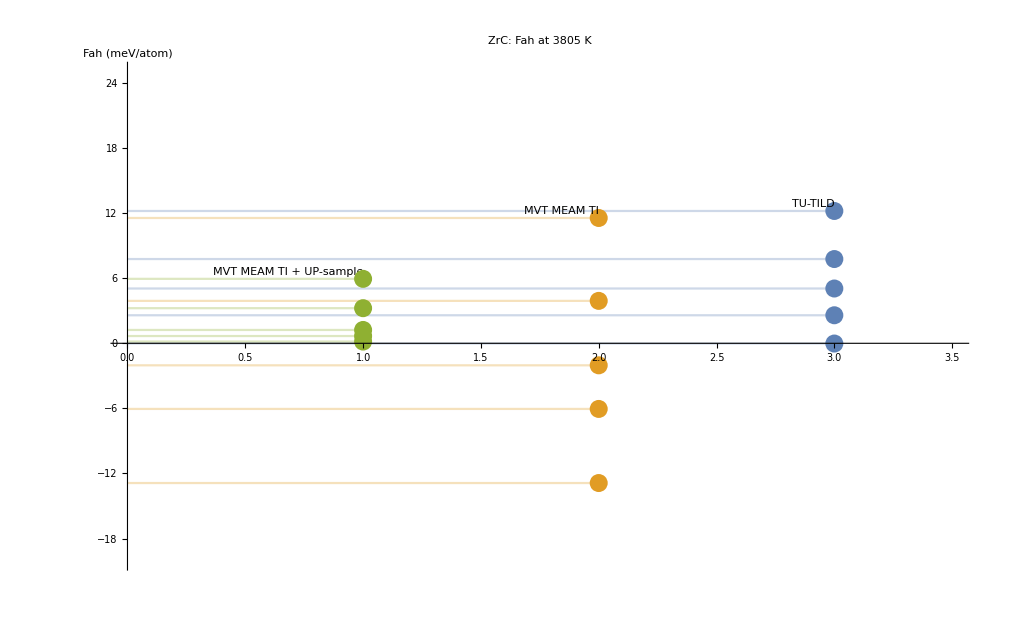

```mathematica
.02e.l\[CapitalUHat]BopDete[.02 Bo\[YDoubleDot]B\[EHat]YY\[EDoubleDot]"ioxozent\[AGrave]lLi\[UHat]|r\[IGrave]\[LeftGuillemet]4Giln\[Cent],$.93F\[Cent]l .8a\[DoubleDot] \[CapitalOGrave]o7.02kx[.19&Lysdp-/U"8"&\[OAcute]&\[Not](.8a` !ROg@oxK\[UGrave]*$\[DoubleDot]b4\[CapitalOGrave].7fwB/.9b.7f"{B,\[NonBreakingSpace]
.01\[AGrave]0 "RowBo8[.7f.8a "   .00\[NTilde]\[IDoubleDot]wBOx[k"m!tdl%F", "[",R.0c` 4((4\[Degree].12>wBo}S.7f
 .00\[NonBreakingSpace]`!".04\[Degree]RovRkx[["U\[OGrave]\[EAcute]Nc1\[IGrave]s!.02< 6B"-\[NonBreakingSpace].02! %$ \[DoubleDot]  .00Rog.03oxJ{"{"d :0p\[Currency]%(\[NonBreakingSpace].00,$ ZkwBo`[[.08 p " $ ` "`JowJkx[r\[Cent]\[CapitalOHat]ebB%\[DownExclamation]/\[Sterling] [+m".021"`$.00 @ (   Sowroh[{"3r, .02,2\[Not]`.02  \[DownExclamation] 8&`$0    Ros\[CapitalAHat]\[IDoubleDot]x[K"\[UHat]",$.06 ($" 0.17$!p` 1@FosBo9Q{"i\[DoubleDot],\[DoubleDot]2,".84!"1"~`\[Cent],",9"\[Micro]&m], .02\[CapitalOTilde]#.7f[}],b\[Cent]]"\[UGrave]M.04 \[EHat],"D0.02`"\[NonBreakingSpace] .08.88     .13gwBox[k.8a  @0 \[NonBreakingSpace]\[CapitalAGrave]0  $ Zgs\[CapitalAHat]ox]z\[Cent]\p\[AAcute]nwx_we`.1c b[ .1ea*an(qFP` ,4"5#{.1c,.00"3.0c0
h  )!   .a6`.10.00R/gfo|Z;\[Cent]["$.00"3&*b2.1d.02.9d.1d* ".952}]y]. "}\[Cent]}]}\[CapitalYAcute].1e "\[Not]b. \[ATilde]|.10^uTU\[Yen]XMD\[CapitalIGrave]\.16< $,
\[NonBreakingSpace] A 8 (p.01kl.02,0b.00c\[CCedilla]\[Divide]\[CapitalARing].02}],!"]"
]. "\[Not]"L.08.08 `(  $:k.7fCnx_{R^abmnpd.01.qb[$,!
 \[Cedilla]\[NonBreakingSpace] \[DoubleDot]  RogQ/|[{.18($0  ! rBow@nJ[\[OAcute]\[Section]F.b2tnbPmbg"( "@*,!+.06.00 .02.04   0BOwB.7f\[UHat]\[CapitalUHat]+"{&L&.0e \[NonBreakingSpace].00.00 aX \[NonBreakingSpace]"Zg.1fBmxSz
 B "     \[NonBreakingSpace]$R\[CapitalIHat]WBox[{ T@`-u.1e,!"Z*h 
 !  0 \[NonBreakingSpace] 4! \[DownExclamation]RovBo\[CapitalEth][z`: \ "4f.0c0
.02!`.80 H !   !.00V_wJf~[{":*-(
$ "     
 .00(" pg\[Divide]Bn\[Cedilla][\[UAcute]"i
.1e "l",!2m"-.00"..02) ".11"\[YAcute]],$"\[CenterDot]"\[YAcute]M}\[CapitalNTilde], b]ji.1d\[Not] ".04', .06".00i((` 0 p z'wbi\[UGrave]Y{*\[ADoubleDot]   !2, \[NonBreakingSpace]$.00\[Currency]R#v.02oxI{ uzQ\[IHat]\[OAcute]Tkse#,\[DownExclamation]%[",`\[Cent]Mv\[CapitalOSlash]ijtAh\[IGrave]".0c\[DownExclamation]"M"}.1d-.00"[.02$!.0b.80  .82*!   b@ S~wcmxZ.1e"[:, "3.a6\[Currency] .00] }_-(bQ o]\[YAcute]]\[IGrave] .00}"y]|.1c< ".0c.82\[Not] K.08 .01` 4 0.02.1c\[LeftGuillemet]\?I\[CapitalUDoubleDot]T MEAI(.0cY|.1a\2b%.01&l*\[Not]\[PlusMinus]"Abi&e\[LeftGuillemet]}}<.00b_"]\\[Not] ". (".0b\[NonBreakingSpace]\[NonBreakingSpace](a.00h.12-wB?x[{"\[CapitalIHat]eb.05pe`\[Sterling].bc"$\[OAcute] .0c .0b.00.04  $``RmVBmh[{
 #& .10\[Copyright]\[NonBreakingSpace]b\[CapitalUAcute]ofRmz\[CapitalUHat]{3]rIfuqo3m ,\[AGrave]#@.02,"
)$,  \[NonBreakingSpace] $".17{wBf8K{ { ,d
 8h".01.01  !"Xow\[CapitalAHat]o8S{
dh .00.80  \[NonBreakingSpace].00.00(RoSBox[{$Tab,a`.0"\[SZ]"\[DiscretionaryHyphen]\[NonBreakingSpace].0e  \[DoubleDot]0  (`" \[Degree]\[NonBreakingSpace]F.7f?\[CapitalAGrave]|8[}"1 .0c.01"\[Not]",`
 .00! .02   $.00 "$[osLkx[{.{\[Cent].0c 
: ""! .00   * $ RoG"oxMr") 8 \[Cent],"\[Cedilla]2"!b.\[Cent].82 .aa-\[NonBreakingSpace]b5.12|.99,.06"-.039\[CapitalIAcute]mY.0c$&].02}]< b.0c"t 
(\[NonBreakingSpace]$ "!&! .00\[Cent]SnwboX[[
  \[Degree]".02.02.06j0.109 Row\[CapitalThorn]
x[\[EAcute]
.00 `@ $!  .00b (BmuCO.18.1a{jT.b2cn{`ite\[ATilde]l "\[UHat].1a\[RegisteredTrademark]("\[CapitalIAcute]^TiztA|,2( &].02}m,%"[.12, 
      00  (\[NonBreakingSpace]cRow.06Oxk["Y"l0b3#8 /\[YAcute]b}.19. 2.1d"}](&.02+*D Jp0 !.00.aa! $  2.12\[IDoubleDot]wJop\[CapitalUHat]{2^\[ARing]bmd",#"[j* .02 (  0(  a0$  Sowb7x[{
 .10\[NonBreakingSpace]\[NonBreakingSpace].00 8 "  .02\[NonBreakingSpace] RnwbH,o}.02
ea\[IGrave]"l("",\[NonBreakingSpace].06 ,( \[DownExclamation]   "\[Eth]0 "  R?W\[CapitalEHat].7fx].12" !.aa  \[NonBreakingSpace]0 $($4"\[NonBreakingSpace] RocB.7fxy{#(#.0c`
   8*0 "\[NonBreakingSpace]`R b !\[NonBreakingSpace]PSo}Kn\[OSlash][["Tb\[UDoubleDot]4.12$(&(#\[Currency]!"oapM<#y]l".02)"}h,\[NonBreakingSpace]"S.12$ J #.00p*!` ( .00(  ( ro{\[CapitalEHat]mx;"["< na"\[Not].00"\[CapitalYAcute]&}.1dl .baX+}|-!.03U.02}]< ",",$
\[NonBreakingSpace]` \[NonBreakingSpace]# ,.02$$.00  0C\[AAcute]wPm.18Kk6{b,!
 .00$b.10$d$ 0\[DownExclamation] !!$V/cBk|[k"i#, b.0cc,1"5\[Cent]u ",',0`7#=T$$"%.0b.7f]}], "}"]\}}}].0c!b}b}\[CapitalYAcute].7f]-j  % (\[Cent]$.00\[OGrave]"."$\[ADoubleDot]"\<X4MUU GEQM!UH.02+ UP?rAmp\[UDoubleDot]d\[CapitalOSlash]>\"", ","
  \[CapitalAAcute]\[AHat]|f\[CapitalIAcute]".1d_-!"}"|]\[YAcute]|) 	.04" .00 "Y"_Y- "-"- * *.08 Row\[CapitalEHat]kxYs"PmotL%gekBr",\[NonBreakingSpace]"T;RqLg?b.0c.00.8b .10 ( Z77\[CapitalEHat]/yR\[UHat]"sf\[AAcute]D\[ATilde]lLugEnd#l.002Z+.".   "  RNw@n8[{.08(`B".08 .02\[CapitalYAcute]"Y<TU%t	L.06}>]".8f..00"< %`"\"\.1c]\[CapitalIHat]Q m.05A
.00RY\>t.02", ",#7`.1a !``0\[NonBreakingSpace] $MB\0
V\[CapitalUDoubleDot]&MEEL@\[CapitalUDoubleDot]I#+.02UP\[Divide]#iPjd.04>\3\[Cent].7fY, b]*y.1d}\[CapitalYAcute]<0"."$\[Cedilla]: p\[DownExclamation].80Ro.7fBox[.1f Pl\[IDoubleDot]u.02i.g\[CapitalEAcute]"% "\[CapitalOGrave][Rul-}f, *3p 0`\.0fwJ/|{\[UAcute]`{"\[Not] .1e$  \[NonBreakingSpace]" r\[CCedilla].afB?~[{
"  \[NonBreakingSpace].08! P_\[SZ]Joz[z.aa{&,(
  !     RowBox[{"0", ",", "3.5"}], "}"}], ",", 
       RowBox[{"{", 
        RowBox[{
         RowBox[{"-", "20"}], ",", "25"}], "}"}]}], "}"}]}], ",", 
    RowBox[{"PlotLabel", "\[Rule]", "\"\<ZrC: Fah at 3805 K\>\""}], ",", 
    RowBox[{"AxesLabel", "\[Rule]", 
     RowBox[{"{", 
      RowBox[{"\"\<\>\"", ",", "\"\<Fah (meV/atom)\>\""}], "}"}]}], ",", 
    RowBox[{"Ticks", "\[Rule]", 
     RowBox[{"{", 
      RowBox[{"None", ",", "Automatic"}], "}"}]}]}], "]"}]}]], "Input",
 CellChangeTimes->{{3.68709190860106*^9, 3.687091944112029*^9}, {
  3.687708249437643*^9, 3.687708257949836*^9}}]
```

```mathematica
Transpose[andyFah][[4]]
```

{-0.172075,2.71939,5.65059,10.2369,18.7489}

```mathematica
Table[Mean[(dft5-meam5)[[i]]],{i,1,5}]
Table[Mean[(dftf5-meam5)[[i]]],{i,1,5}]
Transpose[MVTintAll][[4]]+Table[Mean[(dft5-meam5)[[i]]],{i,1,5}]
```

{15.1432,7.88656,2.65205,-1.45456,-5.38734}

{8.4332,1.16119,-4.17762,-8.69369,-12.8361}

{0.323173,2.14656,1.55205,4.63544,11.0727}

```mathematica
Table[Mean[(dft4-meam4)[[i]]],{i,1,5}]
Table[Mean[(dftf4-meam4)[[i]]],{i,1,5}]
Transpose[MVTintAll][[3]]+Table[Mean[(dft4-meam4)[[i]]],{i,1,5}]
Transpose[andyFah][[3]]
```

{13.0405,7.27976,2.69994,-0.673546,-5.60963}

{10.5065,4.47355,-0.164112,-3.7488,-8.61324}

{0.160487,1.22976,0.66994,3.23645,5.94037}

{-0.0219889,2.58376,5.04972,7.76604,12.1956}